```mathematica
Clear["Global`*"];
```

## Experimental sensitivity

#### laboratory excluded region

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
LABdata=Import[NotebookDirectory[]<>"/exp_sensitivity/LabXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
LABres= Table[{LABdata⟦i,1⟧,LABdata⟦i,2⟧*4} ,{i,1,Length[LABdata]}];
```

```mathematica
(*contains the rescaled data in the inverted order*)
LABinv=Transpose[{Table[LABres⟦i,2⟧,{i,1,Length[LABres]}],Table[LABres⟦i,1⟧,{i,1,Length[LABres]}]}];
```

```mathematica
LAB =  Join[{{10^3,First[LABinv]⟦2⟧}},LABinv,{{10^3,Last[LABinv]⟦2⟧}}];
```

```mathematica
ListLogLogPlot[LAB];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
LABLog = Table[{Log10[LAB⟦i,1⟧], Log10[LAB⟦i,2⟧]}, {i ,1,Length[LAB]}];
```

#### KATRIN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
KATRINdata=Import[NotebookDirectory[]<>"/exp_sensitivity/KATRINXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
KATRINres= Table[{KATRINdata⟦i,1⟧,KATRINdata⟦i,2⟧*4} ,{i,1,Length[KATRINdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
KATRINtr=Transpose[{Table[KATRINres⟦i,2⟧,{i,1,Length[KATRINres]}],Table[KATRINres⟦i,1⟧,{i,1,Length[KATRINres]}]}];
```

```mathematica
KATRIN= Join[{{10^3,First[KATRINtr]⟦2⟧}},KATRINtr,{{10^3,Last[KATRINtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
KATRINLog = Table[{Log10[KATRIN⟦i,1⟧], Log10[KATRIN⟦i,2⟧]}, {i ,1,Length[KATRIN]}];
```

#### TRISTAN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANres= Table[{TRISTANdata⟦i,1⟧,TRISTANdata⟦i,2⟧*4} ,{i,1,Length[TRISTANdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANtr=Transpose[{Table[TRISTANres⟦i,2⟧,{i,1,Length[TRISTANres]}],Table[TRISTANres⟦i,1⟧,{i,1,Length[TRISTANres]}]}];
```

```mathematica
TRISTAN= Join[{{10^3,First[TRISTANtr]⟦2⟧}},TRISTANtr,{{10^3,Last[TRISTANtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRISTANLog = Table[{Log10[TRISTAN⟦i,1⟧], Log10[TRISTAN⟦i,2⟧]}, {i ,1,Length[TRISTAN]}];
```

#### TRISTAN statistical

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANstatdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANstatXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANstatres= Table[{TRISTANstatdata⟦i,1⟧,TRISTANstatdata⟦i,2⟧*4} ,{i,1,Length[TRISTANstatdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANstattr=Transpose[{Table[TRISTANstatres⟦i,2⟧,{i,1,Length[TRISTANstatres]}],Table[TRISTANstatres⟦i,1⟧,{i,1,Length[TRISTANstatres]}]}];
```

```mathematica
TRISTANstat= Join[{{10^3,First[TRISTANstattr]⟦2⟧}},TRISTANstattr,{{10^3,Last[TRISTANstattr]⟦2⟧}}];
```

```mathematica
ListLogLogPlot[{KATRIN, TRISTAN, TRISTANstat}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRISTANstatLog = Table[{Log10[TRISTANstat⟦i,1⟧], Log10[TRISTANstat⟦i,2⟧]}, {i ,1,Length[TRISTANstat]}];
```

#### ECHo

taken from "A White Paper on keV Sterile Neutrino Dark Matter" [arXiv:1602.04816v1]
x-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4
y-axis:  m_s , non-log scale, [GeV]

```mathematica
ECHodata=Import[NotebookDirectory[]<>"/exp_sensitivity/ECHoYaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
ECHores= Table[{ECHodata⟦i,1⟧*4,ECHodata⟦i,2⟧} ,{i,1,Length[ECHodata]}];
```

```mathematica
(*the data are now in the plane (sin^2(2θ), Subscript[m, s])*)
```

```mathematica
ECHo= Join[{{10^3,First[ECHores]⟦2⟧}},ECHores,{{10^3,Last[ECHores]⟦2⟧}}];
```

```mathematica
(*rescale to bring the data in keV instead of GeV*)
ECHor = Table[{ECHo⟦i,1⟧,ECHo⟦i,2⟧*10^6} ,{i,1,Length[ECHo]}];
```

```mathematica
ListLogLogPlot[ECHor];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
ECHoLog =  Table[{Log10[ECHor⟦i,1⟧], Log10[ECHor⟦i,2⟧]}, {i ,1,Length[ECHor]}];
```

#### HUNTER phase 1

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER1data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp1XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER1res= Table[{HUNTER1data⟦i,1⟧,HUNTER1data⟦i,2⟧*4} ,{i,1,Length[HUNTER1data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER1tr=Transpose[{Table[HUNTER1res⟦i,2⟧,{i,1,Length[HUNTER1res]}],Table[HUNTER1res⟦i,1⟧,{i,1,Length[HUNTER1res]}]}];
```

```mathematica
HUNTER1= Join[{{10^3,First[HUNTER1tr]⟦2⟧}},HUNTER1tr,{{10^3,Last[HUNTER1tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER1r = Table[{HUNTER1⟦i,1⟧,HUNTER1⟦i,2⟧*10^6} ,{i,1,Length[HUNTER1]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNTER1Log = Table[{Log10[HUNTER1r⟦i,1⟧], Log10[HUNTER1r⟦i,2⟧]}, {i ,1,Length[HUNTER1r]}];
```

#### HUNTER phase 2

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER2data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp2XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER2res= Table[{HUNTER2data⟦i,1⟧,HUNTER2data⟦i,2⟧*4} ,{i,1,Length[HUNTER2data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER2tr=Transpose[{Table[HUNTER2res⟦i,2⟧,{i,1,Length[HUNTER2res]}],Table[HUNTER2res⟦i,1⟧,{i,1,Length[HUNTER2res]}]}];
```

```mathematica
HUNTER2= Join[{{10^3,First[HUNTER2tr]⟦2⟧}},HUNTER2tr,{{10^3,Last[HUNTER2tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER2r = Table[{HUNTER2⟦i,1⟧,HUNTER2⟦i,2⟧*10^6} ,{i,1,Length[HUNTER2]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNTER2Log = Table[{Log10[HUNTER2r⟦i,1⟧], Log10[HUNTER2r⟦i,2⟧]}, {i ,1,Length[HUNTER2r]}];
```

#### HUNTER phase 3

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER3data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp3XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER3res= Table[{HUNTER3data⟦i,1⟧,HUNTER3data⟦i,2⟧*4} ,{i,1,Length[HUNTER3data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER3tr=Transpose[{Table[HUNTER3res⟦i,2⟧,{i,1,Length[HUNTER3res]}],Table[HUNTER3res⟦i,1⟧,{i,1,Length[HUNTER3res]}]}];
```

```mathematica
HUNTER3= Join[{{10^3,First[HUNTER3tr]⟦2⟧}},HUNTER3tr,{{10^3,Last[HUNTER3tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)HUNTER3r = Table[{HUNTER3⟦i,1⟧,HUNTER3⟦i,2⟧*10^6} ,{i,1,Length[HUNTER3]}];
```

```mathematica
ListLogLogPlot[{HUNTER1r, HUNTER2r, HUNTER3r}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNTER3Log = Table[{Log10[HUNTER3r⟦i,1⟧], Log10[HUNTER3r⟦i,2⟧]}, {i ,1,Length[HUNTER3r]}];
```

#### Plot tools

```mathematica
Import[NotebookDirectory[] <>"/plot_tools/LogScale.m"];
Import[NotebookDirectory[] <>"/plot_tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/plot_tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/plot_tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Log10[5]//N
```

0.69897

```mathematica
Log10[0.5]//N
```

-0.30103

```mathematica
tx=LogTicks[-11, 1,2];
ty=LogTicks[-2,2,1];
tx2=LogTicksNoLabel[-11, 1];
ty2=LogTicksNoLabel[-2,2];
```

```mathematica
ty
```

{{-2.,10^-2},{-1.,10^-1},{0.,10^0},{1.,10^1},{2.,10^2},{-1.69897,,{0.00375,0.},{Thickness[0.001]}},{-1.52288,,{0.00375,0.},{Thickness[0.001]}},{-1.39794,,{0.00375,0.},{Thickness[0.001]}},{-1.30103,,{0.00375,0.},{Thickness[0.001]}},{-1.22185,,{0.00375,0.},{Thickness[0.001]}},{-1.1549,,{0.00375,0.},{Thickness[0.001]}},{-1.09691,,{0.00375,0.},{Thickness[0.001]}},{-1.04576,,{0.00375,0.},{Thickness[0.001]}},{-0.69897,,{0.00375,0.},{Thickness[0.001]}},{-0.522879,,{0.00375,0.},{Thickness[0.001]}},{-0.39794,,{0.00375,0.},{Thickness[0.001]}},{-0.30103,,{0.00375,0.},{Thickness[0.001]}},{-0.221849,,{0.00375,0.},{Thickness[0.001]}},{-0.154902,,{0.00375,0.},{Thickness[0.001]}},{-0.09691,,{0.00375,0.},{Thickness[0.001]}},{-0.0457575,,{0.00375,0.},{Thickness[0.001]}},{0.30103,,{0.00375,0.},{Thickness[0.001]}},{0.477121,,{0.00375,0.},{Thickness[0.001]}},{0.60206,,{0.00375,0.},{Thickness[0.001]}},{0.69897,,{0.00375,0.},{Thickness[0.001]}},{0.778151,,{0.00375,0.},{Thickness[0.001]}},{0.845098,,{0.00375,0.},{Thickness[0.001]}},{0.90309,,{0.00375,0.},{Thickness[0.001]}},{0.954243,,{0.00375,0.},{Thickness[0.001]}},{1.30103,,{0.00375,0.},{Thickness[0.001]}},{1.47712,,{0.00375,0.},{Thickness[0.001]}},{1.60206,,{0.00375,0.},{Thickness[0.001]}},{1.69897,,{0.00375,0.},{Thickness[0.001]}},{1.77815,,{0.00375,0.},{Thickness[0.001]}},{1.8451,,{0.00375,0.},{Thickness[0.001]}},{1.90309,,{0.00375,0.},{Thickness[0.001]}},{1.95424,,{0.00375,0.},{Thickness[0.001]}}}

```mathematica
ty ={{-0.9999999999999998,"0.1"},{-0.3010299956639812,"0.5"},{0.,"1"},{0.69897, "5"},{1.,"10"},{2.,"100"},{-1.6989700043360185,"",{0.00375,0.},{Thickness[0.001]}},{-1.5228787452803374,"",{0.00375,0.},{Thickness[0.001]}},{-1.3979400086720375,"",{0.00375,0.},{Thickness[0.001]}},{-1.301029995663981,"",{0.00375,0.},{Thickness[0.001]}},{-1.2218487496163564,"",{0.00375,0.},{Thickness[0.001]}},{-1.154901959985743,"",{0.00375,0.},{Thickness[0.001]}},{-1.0969100130080565,"",{0.00375,0.},{Thickness[0.001]}},{-1.045757490560675,"",{0.00375,0.},{Thickness[0.001]}},{-0.6989700043360187,"",{0.00375,0.},{Thickness[0.001]}},{-0.5228787452803376,"",{0.00375,0.},{Thickness[0.001]}},{-0.39794000867203755,"",{0.00375,0.},{Thickness[0.001]}},{-0.30102999566398114,"",{0.00375,0.},{Thickness[0.001]}},{-0.22184874961635637,"",{0.00375,0.},{Thickness[0.001]}},{-0.1549019599857432,"",{0.00375,0.},{Thickness[0.001]}},{-0.09691001300805638,"",{0.00375,0.},{Thickness[0.001]}},{-0.045757490560675164,"",{0.00375,0.},{Thickness[0.001]}},{0.30102999566398114,"",{0.00375,0.},{Thickness[0.001]}},{0.47712125471966244,"",{0.00375,0.},{Thickness[0.001]}},{0.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{0.6989700043360187,"",{0.00375,0.},{Thickness[0.001]}},{0.7781512503836435,"",{0.00375,0.},{Thickness[0.001]}},{0.8450980400142567,"",{0.00375,0.},{Thickness[0.001]}},{0.9030899869919434,"",{0.00375,0.},{Thickness[0.001]}},{0.9542425094393249,"",{0.00375,0.},{Thickness[0.001]}},{1.301029995663981,"",{0.00375,0.},{Thickness[0.001]}},{1.4771212547196624,"",{0.00375,0.},{Thickness[0.001]}},{1.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{1.6989700043360185,"",{0.00375,0.},{Thickness[0.001]}},{1.7781512503836434,"",{0.00375,0.},{Thickness[0.001]}},{1.845098040014257,"",{0.00375,0.},{Thickness[0.001]}},{1.9030899869919433,"",{0.00375,0.},{Thickness[0.001]}},{1.9542425094393248,"",{0.00375,0.},{Thickness[0.001]}}};
```

```mathematica
N[Log10[20]]
```

1.30103

#### Experimental sensitivity plot

```mathematica
SensitivityPlot=Plot[{},{x,-11,-0.5},PlotRange->{{-10, -0.999},{-0.65,(* 1.32*) 2}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->35},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],35,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],35,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
RGBColor[127/255, 122/255, 122/255, 0.4],Polygon[LABLog],
Blue, Thick, Thickness[0.004], Line[ECHoLog] ,
Red, Thick,  Thickness[0.004], Line[KATRINLog],
Darker[Green], Thick,  Thickness[0.004], Line[HUNTER1Log],
Red, Dashing[0.02],Thickness[0.004], Line[TRISTANLog],
Red, Dotted, Thickness[0.004], Line[TRISTANstatLog],
Darker[Green], Dashing[0.02],  Thickness[0.004], Line[HUNTER2Log],
Darker[Green],Dotted,  Thickness[0.004], Line[HUNTER3Log]
},

Epilog->{
FontSize->30,
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-55 Degree],Scaled[{0.62,0.12}]],
Red, Text[Rotate[Style["KATRIN sensitivity", Bold],-62 Degree],Scaled[{0.745,0.38}]],
Red, Text[Rotate[Style["TRISTAN sensitivity", Bold],-64 Degree],Scaled[{0.51,0.38}]],
Red, Text[Rotate[Style["TRISTAN full statistical sensitivity", Bold],-64 Degree],Scaled[{0.34,0.38}]], 
Darker[Green], Text[Rotate[Style[" HUNTER \n sensitivity", Bold],-0 Degree],Scaled[{0.88,0.94}]],
Darker[Green], Text[Rotate[Style["phase 1", Bold],-0 Degree],Scaled[{0.87,0.86}]],
Darker[Green], Text[Rotate[Style["phase 2", Bold],-0 Degree],Scaled[{0.86,0.58}]],
Darker[Green], Text[Rotate[Style["phase 3", Bold],-0 Degree],Scaled[{0.86,0.48}]],
RGBColor[127/255, 122/255, 122/255], 
FontSize->23,
Text[Rotate[Style["Region excluded by laboratory experiments", Bold],-90 Degree],Scaled[{0.97,0.38}]]
},
FrameTicks->{{ty,ty2},{tx,tx2}}];
```

```mathematica
Export[NotebookDirectory[]<>"/plots/SensitivityPlot1.pdf", SensitivityPlot];
```

## Constraints in the parameter space and experimental sensitivity

```mathematica
Clear["Global`*"];
```

#### lifetime bound (t_ν_s> t_U)

```mathematica
ms[sin22theta_]:=(267/sin22theta)^(1/5);
```

```mathematica
mainchannelbound={};
For[eth=-14, eth≤-1, eth =eth+0.1, 
mssing=ms[10^eth];
AppendTo[mainchannelbound,{10^eth, mssing}];]
```

```mathematica
mainchannelbound= Table[{mainchannelbound⟦i,1⟧,mainchannelbound⟦i,2⟧} ,{i,1,Length[mainchannelbound]}];
```

```mathematica
mainchannelbound= Join[{{10^3,First[mainchannelbound]⟦2⟧}},mainchannelbound,{{10^3,Last[mainchannelbound]⟦2⟧}}];
```

```mathematica
mainchannelboundLog =  Table[{Log10[mainchannelbound⟦i,1⟧], Log10[mainchannelbound⟦i,2⟧]}, {i ,1,Length[mainchannelbound]}];
```

#### satellites counting bound

```mathematica
satellitebound=Import[NotebookDirectory[]<>"/data/satellitebound.dat"];
```

```mathematica
satellitebound=Transpose[{Table[satellitebound⟦i,2⟧,{i,1,Length[satellitebound]}],Table[satellitebound⟦i,1⟧,{i,1,Length[satellitebound]}]}];
```

```mathematica
satelliteboundint= Interpolation[satellitebound,InterpolationOrder->1];
```

```mathematica
(*non conservative bound on the mass of the SN in case Subscript[Ω, SN]=Subscript[Ω, DM]*)
```

```mathematica
(*average momentum using fAHE*)
poverTAvfA=N[(∫_(10^-10)^(10^4) y^3*1/(ⅇ^y+1)ⅆy)/(∫_(10^-10)^(10^4) y^2*1/(ⅇ^y+1)ⅆy)]
```

3.15137

```mathematica
(*average momentum using fSHE*)
poverTAvfS=N[(∫_(10^-10)^(10^4) y^4*1/(ⅇ^y+1)ⅆy)/(∫_(10^-10)^(10^4) y^3*1/(ⅇ^y+1)ⅆy)]
```

4.10596

```mathematica
(*the value of the average momentum over temperature, in the HE paper approximation, is independent from Tc, theta and Msn, since all these quantities can be factorized and simplified away
<p/T> depends only on the distribution function shape*)
```

```mathematica
(*lower limit on the mass of SN from satellites counting*)
```

```mathematica
llMsn=poverTAvfS/poverTAvfA satelliteboundint[1]
```

8.08453×10^-6

```mathematica
Log10[8.08*10^-6]
```

-5.09259

```mathematica
SatellitelistLog=Table[{eth, Log10[8.08*10^-6]}, {eth, -15, -2, 0.2}];
```

```mathematica
Log10[8.08]
```

0.907411

```mathematica
(*rescaled to keV from GeV*)
SatellitelistLogr=Table[{eth, Log10[8.08]}, {eth, -15, -2, 0.2}];
```

#### X-rays bound

Collection of the most recent (November 2019) X-ray data from Nustar, merged with the old ones to cover all the interesting range of values of mass.

```mathematica
XtotI=Import[NotebookDirectory[]<>"/data/XrayLastXordTOT.dat"];
```

```mathematica
Xtot1=Table[{XtotI⟦i,1⟧,XtotI⟦i,2⟧} ,{i,1,54}];
```

```mathematica
Xtot2=Table[{XtotI⟦i,2⟧,XtotI⟦i,1⟧} ,{i,55,Length[XtotI]}];
```

```mathematica
Xtot=Join[Xtot1, Xtot2];
Xtot= Join[{{10^3,First[Xtot]⟦2⟧}},Xtot,{{10^3,Last[Xtot]⟦2⟧}}];
```

```mathematica
(*to bring the mass coordinate in keV (from GeV)*)
Xtotr = Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*10^6} ,{i,1,Length[Xtot]}];
```

```mathematica
(*Log form better for the plots*)
XtotLog= Table[{Log10[Xtotr⟦i,1⟧], Log10[Xtotr⟦i,2⟧]}, {i ,1,Length[Xtotr]}];
XtotLogl= Table[{Log10[Xtotr⟦i,1⟧], Log10[Xtotr⟦i,2⟧]}, {i ,1,Length[Xtotr]-1}];
AppendTo[XtotLogl, {-13.538,1.8402500000000002}];
```

#### X-rays bound reduced - Cocktail DM

```mathematica
Xtotred10=  Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*10^(1/4)} ,{i,1,Length[Xtot]}];
Xtotred100=  Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*100^(1/4)} ,{i,1,Length[Xtot]}];
```

```mathematica
(*to bring the mass coordinate in keV (from GeV)*)
Xtotred10r = Table[{Xtotred10⟦i,1⟧,Xtotred10⟦i,2⟧*10^6} ,{i,1,Length[Xtotred10]}];
Xtotred100r =Table[{Xtotred100⟦i,1⟧,Xtotred100⟦i,2⟧*10^6} ,{i,1,Length[Xtotred100]}];
```

```mathematica
(*Log form better for the plots*)
Xtotred10Log = Table[{Log10[Xtotred10r⟦i,1⟧], Log10[Xtotred10r⟦i,2⟧]}, {i ,1,Length[Xtotred10r]}];
Xtotred100Log = Table[{Log10[Xtotred100r⟦i,1⟧], Log10[Xtotred100r⟦i,2⟧]}, {i ,1,Length[Xtotred100r]}];
```

#### X-rays bound reduced - Cancellation

```mathematica
Xtotcanc=Import[NotebookDirectory[]<>"/data/xrayYsort.dat"];
```

```mathematica
Xtotcanc= Join[{{10^3,First[Xtotcanc]⟦2⟧}},Xtotcanc,{{10^3,Last[Xtotcanc]⟦2⟧}}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.5]
```

1.41421

```mathematica
(*X^-2*)
(1/Sqrt[0.5])^4
```

4.

```mathematica
(*decay rate reduced by 4*)
Xtotrel50=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.5])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.1]
```

3.16228

```mathematica
(*X^-2*)
(1/Sqrt[0.1])^4
```

100.

```mathematica
(*decay rate reduced by 100*)
Xtotrel90=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.1])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.05]
```

4.47214

```mathematica
(*X^-2*)
(1/Sqrt[0.05])^4
```

400.

```mathematica
(*decay rate reduced by 400*)
Xtotrel95=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.05])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.01]
```

10.

```mathematica
(*X^-2*)
(1/Sqrt[0.01])^4
```

10000.

```mathematica
(*decay rate reduced by 10 000*)
Xtotrel99=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.01])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.005]
```

14.1421

```mathematica
(*X^-2*)
(1/Sqrt[0.005])^4
```

40000.

```mathematica
(*decay rate reduced by 1 000 000*)
Xtotrel995=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.005])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*X^(-1/2)*)
1/Sqrt[0.001]
```

31.6228

```mathematica
(*X^-2*)
(1/Sqrt[0.001])^4
```

1.×10^6

```mathematica
(*decay rate reduced by 1 000 000*)
Xtotrel999=  Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*(1/Sqrt[0.001])} ,{i,1,Length[Xtotcanc]}];
```

```mathematica
(*to bring the mass coordinate in keV (from GeV)*)
Xtotr = Table[{Xtotcanc⟦i,1⟧,Xtotcanc⟦i,2⟧*10^6} ,{i,1,Length[Xtotcanc]}];
Xtotrel50r= Table[{Xtotrel50⟦i,1⟧,Xtotrel50⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel50]}];
Xtotrel90r = Table[{Xtotrel90⟦i,1⟧,Xtotrel90⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel90]}];
Xtotrel95r = Table[{Xtotrel95⟦i,1⟧,Xtotrel95⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel95]}];
Xtotrel99r = Table[{Xtotrel99⟦i,1⟧,Xtotrel99⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel99]}];
Xtotrel995r = Table[{Xtotrel995⟦i,1⟧,Xtotrel995⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel995]}];
Xtotrel999r = Table[{Xtotrel999⟦i,1⟧,Xtotrel999⟦i,2⟧*10^6} ,{i,1,Length[Xtotrel999]}];
```

```mathematica
(*Log form better for the plots*)
XtotLog= Table[{Log10[Xtotr⟦i,1⟧], Log10[Xtotr⟦i,2⟧]}, {i ,1,Length[Xtotr]}];
Xtotrel50Log= Table[{Log10[Xtotrel50r⟦i,1⟧], Log10[Xtotrel50r⟦i,2⟧]}, {i ,1,Length[Xtotrel50r]}];
Xtotrel90Log =  Table[{Log10[Xtotrel90r⟦i,1⟧], Log10[Xtotrel90r⟦i,2⟧]}, {i ,1,Length[Xtotrel90r]}];
Xtotrel95Log =  Table[{Log10[Xtotrel95r⟦i,1⟧], Log10[Xtotrel95r⟦i,2⟧]}, {i ,1,Length[Xtotrel95r]}];
Xtotrel99Log = Table[{Log10[Xtotrel99r⟦i,1⟧], Log10[Xtotrel99r⟦i,2⟧]}, {i ,1,Length[Xtotrel99r]}];
Xtotrel995Log = Table[{Log10[Xtotrel995r⟦i,1⟧], Log10[Xtotrel995r⟦i,2⟧]}, {i ,1,Length[Xtotrel995r]}];
Xtotrel999Log = Table[{Log10[Xtotrel999r⟦i,1⟧], Log10[Xtotrel999r⟦i,2⟧]}, {i ,1,Length[Xtotrel999r]}];
```

#### Experimental lab sensitivity

```mathematica
(*KATRIN now*)
```

```mathematica
KATGeV=Import[NotebookDirectory[]<>"/exp_sensitivity/KATRINGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
KATGeVres= Table[{KATGeV⟦i,1⟧,KATGeV⟦i,2⟧*4} ,{i,1,Length[KATGeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
KATGeVtr=Transpose[{Table[KATGeVres⟦i,2⟧,{i,1,Length[KATGeVres]}],Table[KATGeVres⟦i,1⟧,{i,1,Length[KATGeVres]}]}];
```

```mathematica
KATGeV= Join[{{10^3,First[KATGeVtr]⟦2⟧}},KATGeVtr,{{10^3,Last[KATGeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
KATr= Table[{KATGeV⟦i,1⟧,KATGeV⟦i,2⟧*10^6} ,{i,1,Length[KATGeV]}];
```

```mathematica
KATLog =  Table[{Log10[KATr⟦i,1⟧], Log10[KATr⟦i,2⟧]}, {i ,1,Length[KATr]}];
```

```mathematica
(*TRISTAN*)
```

```mathematica
TRIGeV=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
TRIGeVres= Table[{TRIGeV⟦i,1⟧,TRIGeV⟦i,2⟧*4} ,{i,1,Length[TRIGeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRIGeVtr=Transpose[{Table[TRIGeVres⟦i,2⟧,{i,1,Length[TRIGeVres]}],Table[TRIGeVres⟦i,1⟧,{i,1,Length[TRIGeVres]}]}];
```

```mathematica
TRIGeV= Join[{{10^3,First[TRIGeVtr]⟦2⟧}},TRIGeVtr,{{10^3,Last[TRIGeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
TRIr= Table[{TRIGeV⟦i,1⟧,TRIGeV⟦i,2⟧*10^6} ,{i,1,Length[TRIGeV]}];
```

```mathematica
TRILog =  Table[{Log10[TRIr⟦i,1⟧], Log10[TRIr⟦i,2⟧]}, {i ,1,Length[TRIr]}];
```

```mathematica
(*TRISTAN statistical in 3 years*)
```

```mathematica
TRIstatGeV=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANstatGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
TRIstatGeVres= Table[{TRIstatGeV⟦i,1⟧,TRIstatGeV⟦i,2⟧*4} ,{i,1,Length[TRIstatGeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRIstatGeVtr=Transpose[{Table[TRIstatGeVres⟦i,2⟧,{i,1,Length[TRIstatGeVres]}],Table[TRIstatGeVres⟦i,1⟧,{i,1,Length[TRIstatGeVres]}]}];
```

```mathematica
TRIstatGeV= Join[{{10^3,First[TRIstatGeVtr]⟦2⟧}},TRIstatGeVtr,{{10^3,Last[TRIstatGeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
TRIstatr = Table[{TRIstatGeV⟦i,1⟧,TRIstatGeV⟦i,2⟧*10^6} ,{i,1,Length[TRIstatGeV]}];
```

```mathematica
TRIstatLog =  Table[{Log10[TRIstatr⟦i,1⟧], Log10[TRIstatr⟦i,2⟧]}, {i ,1,Length[TRIstatr]}];
```

```mathematica
(*Troitsk now*)
```

taken from "..." [arXiv:...]

```mathematica
Troitsknow=Import[NotebookDirectory[]<>"/exp_sensitivity/Troitsk.dat"];
```

```mathematica
(*contains the transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
Troitsknowtr=Transpose[{Table[Troitsknow⟦i,2⟧,{i,1,Length[Troitsknow]}],Table[Troitsknow⟦i,1⟧,{i,1,Length[Troitsknow]}]}];
```

```mathematica
Troitsknow= Join[{{0.1,First[Troitsknowtr]⟦2⟧}},Troitsknowtr,{{0.1,Last[Troitsknowtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
Troitsknowr = Table[{Troitsknow⟦i,1⟧,Troitsknow⟦i,2⟧*10^6} ,{i,1,Length[Troitsknow]}];
```

```mathematica
TroitsknowLog =  Table[{Log10[Troitsknowr⟦i,1⟧], Log10[Troitsknowr⟦i,2⟧]}, {i ,1,Length[Troitsknowr]}];
```

```mathematica
(*Troitsk future*)
```

taken from "..." [arXiv:...]

```mathematica
Troitskfut= {{0.29735992787434745,0.0006700187503509618},{0.3362927907429957,0.0005484416576121038},{0.36718547752782704,0.0004961947603002918},{0.4301181669228285,0.0003674661940736703},{0.495058462311238,0.0003324597932270959},{0.6331793133551694,0.000272133876837532},{0.8688229768152469,0.00020153376859417392},{1.0177323697119482,0.00016496480740980308},{1.1921636558879285,0.00012216773489967956},{1.551814103737828,0.00008185467307069037},{1.850016375170536,0.000060618989934976096},{1.9847687969463492,0.00004489251258218617},{3.304334231190638,0.000020153376859417392},{4.080252343563838,0.000020153376859417392},{5.038370219939685,0.000027213387683753144},{5.501207358870712,0.00004489251258218617},{5.5012073,0.001},{5.5012073,0.02}};
```

```mathematica
(*contains the transposed data, in the plane (sin^2(2θ), Subscript[m, s]), already with mass in keV*)
Troitskfuttr = Transpose[{Table[Troitskfut⟦i,2⟧,{i,1,Length[Troitskfut]}],Table[Troitskfut⟦i,1⟧,{i,1,Length[Troitskfut]}]}];
```

```mathematica
TroitskfutLog =  Table[{Log10[Troitskfuttr⟦i,1⟧], Log10[Troitskfuttr⟦i,2⟧]}, {i ,1,Length[Troitskfuttr]}];
```

```mathematica
(*ECHo*)
```

```mathematica
ECHoGeV=Import[NotebookDirectory[]<>"/exp_sensitivity/ECHoYaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
ECHoGeVres= Table[{ECHoGeV⟦i,1⟧*4,ECHoGeV⟦i,2⟧} ,{i,1,Length[ECHoGeV]}];
```

```mathematica
ECHoGeV= Join[{{10^3,First[ECHoGeVres]⟦2⟧}},ECHoGeVres,{{10^3,Last[ECHoGeVres]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
ECHor = Table[{ECHoGeV⟦i,1⟧,ECHoGeV⟦i,2⟧*10^6} ,{i,1,Length[ECHoGeV]}];
```

```mathematica
ECHoLog =  Table[{Log10[ECHor⟦i,1⟧], Log10[ECHor⟦i,2⟧]}, {i ,1,Length[ECHor]}];
```

```mathematica
(*HUNTER phase 1*)
```

```mathematica
HUNT1GeV=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp1XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
HUNT1GeVres= Table[{HUNT1GeV⟦i,1⟧,HUNT1GeV⟦i,2⟧*4} ,{i,1,Length[HUNT1GeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNT1GeVtr=Transpose[{Table[HUNT1GeVres⟦i,2⟧,{i,1,Length[HUNT1GeVres]}],Table[HUNT1GeVres⟦i,1⟧,{i,1,Length[HUNT1GeVres]}]}];
```

```mathematica
HUNT1GeV= Join[{{10^3,First[HUNT1GeVtr]⟦2⟧}},HUNT1GeVtr,{{10^3,Last[HUNT1GeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
HUNT1r= Table[{HUNT1GeV⟦i,1⟧,HUNT1GeV⟦i,2⟧*10^6} ,{i,1,Length[HUNT1GeV]}];
```

```mathematica
HUNT1Log =  Table[{Log10[HUNT1r⟦i,1⟧], Log10[HUNT1r⟦i,2⟧]}, {i ,1,Length[HUNT1r]}];
```

```mathematica
(*HUNTER phase 2*)
```

```mathematica
HUNT2GeV=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp2XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
HUNT2GeVres= Table[{HUNT2GeV⟦i,1⟧,HUNT2GeV⟦i,2⟧*4} ,{i,1,Length[HUNT2GeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNT2GeVtr=Transpose[{Table[HUNT2GeVres⟦i,2⟧,{i,1,Length[HUNT2GeVres]}],Table[HUNT2GeVres⟦i,1⟧,{i,1,Length[HUNT2GeVres]}]}];
```

```mathematica
HUNT2GeV= Join[{{10^3,First[HUNT2GeVtr]⟦2⟧}},HUNT2GeVtr,{{10^3,Last[HUNT2GeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
HUNT2r= Table[{HUNT2GeV⟦i,1⟧,HUNT2GeV⟦i,2⟧*10^6} ,{i,1,Length[HUNT2GeV]}];
```

```mathematica
HUNT2Log =  Table[{Log10[HUNT2r⟦i,1⟧], Log10[HUNT2r⟦i,2⟧]}, {i ,1,Length[HUNT2r]}];
```

```mathematica
(*HUNTER phase 3*)
```

```mathematica
HUNT3GeV=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp3XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
HUNT3GeVres= Table[{HUNT3GeV⟦i,1⟧,HUNT3GeV⟦i,2⟧*4} ,{i,1,Length[HUNT3GeV]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNT3GeVtr=Transpose[{Table[HUNT3GeVres⟦i,2⟧,{i,1,Length[HUNT3GeVres]}],Table[HUNT3GeVres⟦i,1⟧,{i,1,Length[HUNT3GeVres]}]}];
```

```mathematica
HUNT3GeV= Join[{{10^3,First[HUNT3GeVtr]⟦2⟧}},HUNT3GeVtr,{{10^3,Last[HUNT3GeVtr]⟦2⟧}}];
```

```mathematica
(*from GeV to keV*)
HUNT3r= Table[{HUNT3GeV⟦i,1⟧,HUNT3GeV⟦i,2⟧*10^6} ,{i,1,Length[HUNT3GeV]}];
```

```mathematica
HUNT3Log =  Table[{Log10[HUNT3r⟦i,1⟧], Log10[HUNT3r⟦i,2⟧]}, {i ,1,Length[HUNT3r]}];
```

## Cocktail DM - Dodelson-Widrow mechanism

We explore 4 scenarios corresponding to different values of critical temperature at which the production of sterile neutrinos started (T_c=10 GeV, 20 MeV, 10 MeV and 5 MeV), under the hypothesis that DM is entirely constituted by sterile neutrinos or it is a cocktail of different particles to which sterile neutrinos can contribute being the 10% or 1% (taken just as indicative benchmark values).

#### Plot tools - final range

```mathematica
Import[NotebookDirectory[] <>"/plot_tools/LogScale.m"];
Import[NotebookDirectory[] <>"/plot_tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/plot_tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/plot_tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ticksxcS=LogTicks[-14, -2,2];
ticksycS=LogTicks[0,2,1];
ticksx2cS=LogTicksNoLabel[-14,-2];
ticksy2cS=LogTicksNoLabel[0,2];
ticksycS= {{0.,"1"},{1.,"10"},{2.,"100"},{0.30102999566398114,"",{0.00375,0.},{Thickness[0.001]}},{0.47712125471966244,"",{0.00375,0.},{Thickness[0.001]}},{0.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{0.6989700043360187,"",{0.00375,0.},{Thickness[0.001]}},{0.7781512503836435,"",{0.00375,0.},{Thickness[0.001]}},{0.8450980400142567,"",{0.00375,0.},{Thickness[0.001]}},{0.9030899869919434,"",{0.00375,0.},{Thickness[0.001]}},{0.9542425094393249,"",{0.00375,0.},{Thickness[0.001]}},{1.301029995663981,"",{0.00375,0.},{Thickness[0.001]}},{1.4771212547196624,"",{0.00375,0.},{Thickness[0.001]}},{1.6020599913279623,"",{0.00375,0.},{Thickness[0.001]}},{1.6989700043360185,"",{0.00375,0.},{Thickness[0.001]}},{1.7781512503836434,"",{0.00375,0.},{Thickness[0.001]}},{1.845098040014257,"",{0.00375,0.},{Thickness[0.001]}},{1.9030899869919433,"",{0.00375,0.},{Thickness[0.001]}},{1.9542425094393248,"",{0.00375,0.},{Thickness[0.001]}}}
```

{{0.,1},{1.,10},{2.,100},{0.30103,,{0.00375,0.},{Thickness[0.001]}},{0.477121,,{0.00375,0.},{Thickness[0.001]}},{0.60206,,{0.00375,0.},{Thickness[0.001]}},{0.69897,,{0.00375,0.},{Thickness[0.001]}},{0.778151,,{0.00375,0.},{Thickness[0.001]}},{0.845098,,{0.00375,0.},{Thickness[0.001]}},{0.90309,,{0.00375,0.},{Thickness[0.001]}},{0.954243,,{0.00375,0.},{Thickness[0.001]}},{1.30103,,{0.00375,0.},{Thickness[0.001]}},{1.47712,,{0.00375,0.},{Thickness[0.001]}},{1.60206,,{0.00375,0.},{Thickness[0.001]}},{1.69897,,{0.00375,0.},{Thickness[0.001]}},{1.77815,,{0.00375,0.},{Thickness[0.001]}},{1.8451,,{0.00375,0.},{Thickness[0.001]}},{1.90309,,{0.00375,0.},{Thickness[0.001]}},{1.95424,,{0.00375,0.},{Thickness[0.001]}}}

## Sterile neutrino abundance

#### active neutrinos interaction rate

Interaction rate coefficient for electron neutrinos digitizing Fig. 1 in 1512.05369 
[Alexander Merle, Aurel Schneider, Maximilian Totzauer, 
“Dodelson-Widrow production of sterile neutrino Dark Matter with non-trivial initial abundance”, 
JCAP, 04, 003 (2016)]

```mathematica
Cedata = Import[NotebookDirectory[]<>"/data/C_e.dat", "Table"];
Ce=Interpolation[Cedata, InterpolationOrder->1];
```

#### sterile neutrinos and antineutrinos distribution functions

```mathematica
distribfunctions[sin22theta_?NumericQ,Msn_?NumericQ,Tfinal_?NumericQ,Tini_?NumericQ,r_?NumericQ]:=Module[{GF,mZ,mW,baryonasymmetry,MPl},
GF=1.166*10^-5 (*GeV^-2*);
mZ=91.2(*GeV*);
mW=80.4(*GeV*);
baryonasymmetry=6.05*10^-10;
MPl=1.22*10^19;
NIntegrate[MPl/(1.66*Sqrt[10.75]*T^3)*1/(Exp[r]+1)*(1/4)*(Ce[T]*GF^2*r* T^5)*(Msn^2/(2*r*T))^2*sin22theta(1/((Msn^2/(2*r*T))^2*sin22theta+((Ce[T]*GF^2*r* T^5)^2)/4+(Msn^2/(2*r*T)-(Sqrt[2] *GF*2*Zeta[3]*T^3*baryonasymmetry)/(4*Pi^2)+(7*Sqrt[2]*GF*r*Pi^2)/(45 mZ^2)*T^5+2*(7*Sqrt[2]*GF*r*Pi^2)/(45 mW^2)*T^5)^2)+1/((Msn^2/(2*r*T))^2*sin22theta+((Ce[T]*GF^2*r* T^5)^2)/4+(Msn^2/(2*r*T)+(Sqrt[2] GF*2*Zeta[3]*T^3*baryonasymmetry)/(4*Pi^2)+(7*Sqrt[2]*GF*r*Pi^2)/(45 mZ^2)*T^5+2*(7*Sqrt[2]*GF*r*Pi^2)/(45 mW^2)*T^5))^2),
{T,Tfinal,Tini},Method->{"GlobalAdaptive","MaxErrorIncreases"->35,Method->"GaussKronrodRule"}]]
```

```mathematica
Sterileabundance[sin22theta_?NumericQ,Msn_?NumericQ,Tfinal_?NumericQ,Tini_?NumericQ]:=
Module[{stod, rhoch},
stod=2891.2 (*cm^-3*);
rhoch= 1.053*10^-5 (*(GeV/c^2)cm^-3*);

stod/rhoch*45/(4 Pi^4*10.75)*Msn*
NIntegrate[(distribfunctions[sin22theta,Msn,Tfinal,Tini, r])*r^2,{r,0,500},Method->{"GlobalAdaptive","MaxErrorIncreases"->35,Method->"GaussKronrodRule"},MaxRecursion->30]]
```

### T_c=10 GeV

#### data

For the standard case we use data simulated with sterile-dm.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with sterile-dm in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 10 GeV.

```mathematica
ScanList0010G={{{1.*^-14,1.*^-6},1.7294367865387473*^-8},{{1.*^-14,1.2589254117941676*^-6},2.7064774507576124*^-8},{{1.*^-14,1.584893192461114*^-6},4.1971227981806545*^-8},{{1.*^-14,1.995262314968881*^-6},6.44221875357001*^-8},{{1.*^-14,2.5118864315095823*^-6},9.781598517810921*^-8},{{1.*^-14,3.1622776601683826*^-6},1.4693696530966423*^-7},{{1.*^-14,3.981071705534978*^-6},2.1856449439495502*^-7},{{1.*^-14,5.01187233627273*^-6},3.2249195566965453*^-7},{{1.*^-14,6.309573444801942*^-6},4.731187392629361*^-7},{{1.*^-14,7.94328234724283*^-6},6.922021916949873*^-7},{{1.*^-14,0.000010000000000000021},1.013113828720503*^-6},{{1.*^-14,0.000012589254117941702},1.4880666826999032*^-6},{{1.*^-14,0.000015848931924611172},2.1986517217511182*^-6},{{1.*^-14,0.00001995262314968885},3.2737234930494677*^-6},{{1.*^-14,0.000025118864315095876},4.917000285413208*^-6},{{1.*^-14,0.00003162277660168389},7.450701488699097*^-6},{{1.*^-14,0.00003981071705534985},0.000011386541145307107},{{1.*^-14,0.0000501187233627274},0.00001753474658411292},{{1.*^-14,0.00006309573444801955},0.000027185106243197594},{{1.*^-14,0.00007943282347242846},0.000042380742779791176},{{1.*^-14,0.00010000000000000038},0.00006637417858788298},{{1.*^-14,0.00012589254117941701},0.00010431940132951716},{{1.*^-14,0.00015848931924611174},0.00016437257495460113},{{1.*^-14,0.0001995262314968885},0.0002594671283730758},{{3.1622776601683796*^-14,1.*^-6},5.4689426455323075*^-8},{{3.1622776601683796*^-14,1.2589254117941676*^-6},8.558673887557347*^-8},{{3.1622776601683796*^-14,1.584893192461114*^-6},1.327247992974328*^-7},{{3.1622776601683796*^-14,1.995262314968881*^-6},2.0372105237074527*^-7},{{3.1622776601683796*^-14,2.5118864315095823*^-6},3.093207467599138*^-7},{{3.1622776601683796*^-14,3.1622776601683826*^-6},4.646544618551039*^-7},{{3.1622776601683796*^-14,3.981071705534978*^-6},6.911743850631935*^-7},{{3.1622776601683796*^-14,5.01187233627273*^-6},1.0197953296555006*^-6},{{3.1622776601683796*^-14,6.309573444801942*^-6},1.496128828329038*^-6},{{3.1622776601683796*^-14,7.94328234724283*^-6},2.1889395086732282*^-6},{{3.1622776601683796*^-14,0.000010000000000000021},3.2039047803892725*^-6},{{3.1622776601683796*^-14,0.000012589254117941702},4.705685908057819*^-6},{{3.1622776601683796*^-14,0.000015848931924611172},6.952719500902345*^-6},{{3.1622776601683796*^-14,0.00001995262314968885},0.000010352362546412523},{{3.1622776601683796*^-14,0.000025118864315095876},0.000015548801703913702},{{3.1622776601683796*^-14,0.00003162277660168389},0.00002356187188200235},{{3.1622776601683796*^-14,0.00003981071705534985},0.000036007132124464645},{{3.1622776601683796*^-14,0.0000501187233627274},0.00005545047331808521},{{3.1622776601683796*^-14,0.00006309573444801955},0.00008596726685523805},{{3.1622776601683796*^-14,0.00007943282347242846},0.0001340230677893365},{{3.1622776601683796*^-14,0.00010000000000000038},0.00020989291663158977},{{3.1622776601683796*^-14,0.00012589254117941701},0.00032987037480819616},{{3.1622776601683796*^-14,0.00015848931924611174},0.0005197904279546024},{{3.1622776601683796*^-14,0.0001995262314968885},0.0008205028027919006},{{1.*^-13,1.*^-6},1.729434488810011*^-7},{{1.*^-13,1.2589254117941676*^-6},2.70648400676109*^-7},{{1.*^-13,1.584893192461114*^-6},4.197124655173293*^-7},{{1.*^-13,1.995262314968881*^-6},6.442227847014181*^-7},{{1.*^-13,2.5118864315095823*^-6},9.781599418481744*^-7},{{1.*^-13,3.1622776601683826*^-6},1.469367886084192*^-6},{{1.*^-13,3.981071705534978*^-6},2.185685410534858*^-6},{{1.*^-13,5.01187233627273*^-6},3.2248884504855668*^-6},{{1.*^-13,6.309573444801942*^-6},4.731209237785477*^-6},{{1.*^-13,7.94328234724283*^-6},6.92204172959055*^-6},{{1.*^-13,0.000010000000000000021},0.000010131613050267137},{{1.*^-13,0.000012589254117941702},0.00001488062395221871},{{1.*^-13,0.000015848931924611172},0.0000219865922711981},{{1.*^-13,0.00001995262314968885},0.0000327363484255724},{{1.*^-13,0.000025118864315095876},0.0000491699053811586},{{1.*^-13,0.00003162277660168389},0.0000745075586793009},{{1.*^-13,0.00003981071705534985},0.00011386346253412876},{{1.*^-13,0.0000501187233627274},0.00017534917753666662},{{1.*^-13,0.00006309573444801955},0.00027184343350636884},{{1.*^-13,0.00007943282347242846},0.0004238150499281508},{{1.*^-13,0.00010000000000000038},0.0006637443644996547},{{1.*^-13,0.00012589254117941701},0.0010431550092170076},{{1.*^-13,0.00015848931924611174},0.0016436794536054224},{{1.*^-13,0.0001995262314968885},0.002594919757581293},{{3.162277660168379*^-13,1.*^-6},5.468964428511705*^-7},{{3.162277660168379*^-13,1.2589254117941676*^-6},8.558653511121047*^-7},{{3.162277660168379*^-13,1.584893192461114*^-6},1.3272472157995657*^-6},{{3.162277660168379*^-13,1.995262314968881*^-6},2.0372104595540244*^-6},{{3.162277660168379*^-13,2.5118864315095823*^-6},3.0932134642422264*^-6},{{3.162277660168379*^-13,3.1622776601683826*^-6},4.646551280042356*^-6},{{3.162277660168379*^-13,3.981071705534978*^-6},6.911705699507742*^-6},{{3.162277660168379*^-13,5.01187233627273*^-6},0.000010198087553353754},{{3.162277660168379*^-13,6.309573444801942*^-6},0.000014961398413980472},{{3.162277660168379*^-13,7.94328234724283*^-6},0.000021889354205845803},{{3.162277660168379*^-13,0.000010000000000000021},0.00003203918359728457},{{3.162277660168379*^-13,0.000012589254117941702},0.000047056858946058815},{{3.162277660168379*^-13,0.000015848931924611172},0.00006952673657379814},{{3.162277660168379*^-13,0.00001995262314968885},0.00010352452841464794},{{3.162277660168379*^-13,0.000025118864315095876},0.00015548658389790036},{{3.162277660168379*^-13,0.00003162277660168389},0.00023561431433214547},{{3.162277660168379*^-13,0.00003981071705534985},0.0003600642695032263},{{3.162277660168379*^-13,0.0000501187233627274},0.0005545037584757484},{{3.162277660168379*^-13,0.00006309573444801955},0.0008596687019368278},{{3.162277660168379*^-13,0.00007943282347242846},0.001340222095130809},{{3.162277660168379*^-13,0.00010000000000000038},0.0020989497691005156},{{3.162277660168379*^-13,0.00012589254117941701},0.0032986921670389497},{{3.162277660168379*^-13,0.00015848931924611174},0.005197790366012075},{{3.162277660168379*^-13,0.0001995262314968885},0.00820569858692117},{{1.*^-12,1.*^-6},1.7294336963016036*^-6},{{1.*^-12,1.2589254117941676*^-6},2.706494650498249*^-6},{{1.*^-12,1.584893192461114*^-6},4.19712750029863*^-6},{{1.*^-12,1.995262314968881*^-6},6.442222375072988*^-6},{{1.*^-12,2.5118864315095823*^-6},9.781590830510622*^-6},{{1.*^-12,3.1622776601683826*^-6},0.000014693672491097788},{{1.*^-12,3.981071705534978*^-6},0.00002185684018672767},{{1.*^-12,5.01187233627273*^-6},0.000032248904102499104},{{1.*^-12,6.309573444801942*^-6},0.00004731211711936464},{{1.*^-12,7.94328234724283*^-6},0.00006921986561886279},{{1.*^-12,0.000010000000000000021},0.00010131599722706091},{{1.*^-12,0.000012589254117941702},0.00014880710903747513},{{1.*^-12,0.000015848931924611172},0.00021986292201182453},{{1.*^-12,0.00001995262314968885},0.0003273737139147416},{{1.*^-12,0.000025118864315095876},0.0004916870695862442},{{1.*^-12,0.00003162277660168389},0.0007450771235971597},{{1.*^-12,0.00003981071705534985},0.0011386374029301745},{{1.*^-12,0.0000501187233627274},0.0017534778562492946},{{1.*^-12,0.00006309573444801955},0.002718544490854187},{{1.*^-12,0.00007943282347242846},0.004238106579885979},{{1.*^-12,0.00010000000000000038},0.006637149459031655},{{1.*^-12,0.00012589254117941701},0.01043157756260356},{{1.*^-12,0.00015848931924611174},0.0164371003603148},{{1.*^-12,0.0001995262314968885},0.025946874730812346},{{3.1622776601683794*^-12,1.*^-6},5.468952593504154*^-6},{{3.1622776601683794*^-12,1.2589254117941676*^-6},8.558676616260573*^-6},{{3.1622776601683794*^-12,1.584893192461114*^-6},0.000013272464731424294},{{3.1622776601683794*^-12,1.995262314968881*^-6},0.000020372041905030767},{{3.1622776601683794*^-12,2.5118864315095823*^-6},0.00003093210696198053},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.00004646557797223853},{{3.1622776601683794*^-12,3.981071705534978*^-6},0.0000691173570048282},{{3.1622776601683794*^-12,5.01187233627273*^-6},0.0001019805399336482},{{3.1622776601683794*^-12,6.309573444801942*^-6},0.0001496137776590425},{{3.1622776601683794*^-12,7.94328234724283*^-6},0.00021889186091278754},{{3.1622776601683794*^-12,0.000010000000000000021},0.0003203879501751932},{{3.1622776601683794*^-12,0.000012589254117941702},0.00047056553052825495},{{3.1622776601683794*^-12,0.000015848931924611172},0.0006952574340208392},{{3.1622776601683794*^-12,0.00001995262314968885},0.0010352359727774636},{{3.1622776601683794*^-12,0.000025118864315095876},0.0015548730688784002},{{3.1622776601683794*^-12,0.00003162277660168389},0.0023561135061023917},{{3.1622776601683794*^-12,0.00003981071705534985},0.0036006682501062127},{{3.1622776601683794*^-12,0.0000501187233627274},0.0055449651073637505},{{3.1622776601683794*^-12,0.00006309573444801955},0.008596310314705924},{{3.1622776601683794*^-12,0.00007943282347242846},0.013401784131817208},{{3.1622776601683794*^-12,0.00010000000000000038},0.020989169339872084},{{3.1622776601683794*^-12,0.00012589254117941701},0.0329867815746823},{{3.1622776601683794*^-12,0.00015848931924611174},0.0519718495535957},{{3.1622776601683794*^-12,0.0001995262314968885},0.08204564881791311},{{1.*^-11,1.*^-6},0.000017294335206468733},{{1.*^-11,1.2589254117941676*^-6},0.000027064840093306505},{{1.*^-11,1.584893192461114*^-6},0.00004197118359130822},{{1.*^-11,1.995262314968881*^-6},0.00006442194230179761},{{1.*^-11,2.5118864315095823*^-6},0.00009781561702479622},{{1.*^-11,3.1622776601683826*^-6},0.00014693650337589887},{{1.*^-11,3.981071705534978*^-6},0.0002185668230290612},{{1.*^-11,5.01187233627273*^-6},0.00032248574628892623},{{1.*^-11,6.309573444801942*^-6},0.0004731175155996026},{{1.*^-11,7.94328234724283*^-6},0.0006921903297418765},{{1.*^-11,0.000010000000000000021},0.0010131337710400008},{{1.*^-11,0.000012589254117941702},0.001488027909383176},{{1.*^-11,0.000015848931924611172},0.0021985991711340864},{{1.*^-11,0.00001995262314968885},0.00327364047577774},{{1.*^-11,0.000025118864315095876},0.004916794930684721},{{1.*^-11,0.00003162277660168389},0.007450521318715433},{{1.*^-11,0.00003981071705534985},0.01138594763151568},{{1.*^-11,0.0000501187233627274},0.01753326003625},{{1.*^-11,0.00006309573444801955},0.027182395656996563},{{1.*^-11,0.00007943282347242846},0.042377307672933684},{{1.*^-11,0.00010000000000000038},0.06636493822868209},{{1.*^-11,0.00012589254117941701},0.10430248521411863},{{1.*^-11,0.00015848931924611174},0.1643400407962516},{{1.*^-11,0.0001995262314968885},0.25938881618004295},{{3.1622776601683794*^-11,1.*^-6},0.0000546894024383333},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.00008558633706416631},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.00013272404976113756},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.0002037190191158799},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.00030931820668871475},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.0004646480705255992},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.0006911659368566009},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.001019786136473669},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.0014961038890758842},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.002188869706462882},{{3.1622776601683794*^-11,0.000010000000000000021},0.0032037990787897033},{{3.1622776601683794*^-11,0.000012589254117941702},0.004705480345196263},{{3.1622776601683794*^-11,0.000015848931924611172},0.006952322302930837},{{3.1622776601683794*^-11,0.00001995262314968885},0.010351609257171716},{{3.1622776601683794*^-11,0.000025118864315095876},0.015547673763220228},{{3.1622776601683794*^-11,0.00003162277660168389},0.023558452128089415},{{3.1622776601683794*^-11,0.00003981071705534985},0.0360011976466671},{{3.1622776601683794*^-11,0.0000501187233627274},0.05544029076708854},{{3.1622776601683794*^-11,0.00006309573444801955},0.08594621917841369},{{3.1622776601683794*^-11,0.00007943282347242846},0.1339744856791485},{{3.1622776601683794*^-11,0.00010000000000000038},0.2098034248970367},{{3.1622776601683794*^-11,0.00012589254117941701},0.32968851288803597},{{3.1622776601683794*^-11,0.00015848931924611174},0.5194090316161633},{{3.1622776601683794*^-11,0.0001995262314968885},0.8197055473520194},{{1.*^-10,1.*^-6},0.00017294145316302397},{{1.*^-10,1.2589254117941676*^-6},0.0002706451883139562},{{1.*^-10,1.584893192461114*^-6},0.0004197053242971584},{{1.*^-10,1.995262314968881*^-6},0.0006442056227783673},{{1.*^-10,2.5118864315095823*^-6},0.0009781301079638334},{{1.*^-10,3.1622776601683826*^-6},0.0014693024548668324},{{1.*^-10,3.981071705534978*^-6},0.002185583098175464},{{1.*^-10,5.01187233627273*^-6},0.0032247291249682037},{{1.*^-10,6.309573444801942*^-6},0.004730881960966989},{{1.*^-10,7.94328234724283*^-6},0.006921422928269862},{{1.*^-10,0.000010000000000000021},0.010130535502934178},{{1.*^-10,0.000012589254117941702},0.014878673751363937},{{1.*^-10,0.000015848931924611172},0.021982382048971832},{{1.*^-10,0.00001995262314968885},0.03273050573525109},{{1.*^-10,0.000025118864315095876},0.04915457871312765},{{1.*^-10,0.00003162277660168389},0.07448151914631515},{{1.*^-10,0.00003981071705534985},0.11381124395174438},{{1.*^-10,0.0000501187233627274},0.17523784913149512},{{1.*^-10,0.00006309573444801955},0.27163178188651377},{{1.*^-10,0.00007943282347242846},0.4233713745517842},{{1.*^-10,0.00010000000000000038},0.6628280214471338},{{1.*^-10,0.00012589254117941701},1.0411913822778869},{{1.*^-10,0.00015848931924611174},1.6398383428094687},{{1.*^-10,0.0001995262314968885},2.5865555904501507},{{3.1622776601683795*^-10,1.*^-6},0.0005468749270906806},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.0008558240191032618},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.0013271636085855334},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.0020370515245043083},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.003092913448541685},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.004646003421245104},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.006910721113201948},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.010196262831625636},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.014958163340316402},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.021883616118876587},{{3.1622776601683795*^-10,0.000010000000000000021},0.0320286412779591},{{3.1622776601683795*^-10,0.000012589254117941702},0.047037886107732255},{{3.1622776601683795*^-10,0.000015848931924611172},0.06949089340100967},{{3.1622776601683795*^-10,0.00001995262314968885},0.10345323014720198},{{3.1622776601683795*^-10,0.000025118864315095876},0.1553533490288506},{{3.1622776601683795*^-10,0.00003162277660168389},0.2353498118550131},{{3.1622776601683795*^-10,0.00003981071705534985},0.3595385879204703},{{3.1622776601683795*^-10,0.0000501187233627274},0.5534374610561438},{{3.1622776601683795*^-10,0.00006309573444801955},0.8574621479448803},{{3.1622776601683795*^-10,0.00007943282347242846},1.3357388780880486},{{3.1622776601683795*^-10,0.00010000000000000038},2.0895720713760975},{{3.1622776601683795*^-10,0.00012589254117941701},3.279640996365941},{{3.1622776601683795*^-10,0.00015848931924611174},5.158086187547949},{{3.1622776601683795*^-10,0.0001995262314968885},8.124765470202249},{{1.*^-9,1.*^-6},0.0017292257097621516},{{1.*^-9,1.2589254117941676*^-6},0.002706080332437006},{{1.*^-9,1.584893192461114*^-6},0.004196198017343124},{{1.*^-9,1.995262314968881*^-6},0.006440671624481787},{{1.*^-9,2.5118864315095823*^-6},0.009778649709095078},{{1.*^-9,3.1622776601683826*^-6},0.014688202033101035},{{1.*^-9,3.981071705534978*^-6},0.021846755275711567},{{1.*^-9,5.01187233627273*^-6},0.03223118405958941},{{1.*^-9,6.309573444801942*^-6},0.04727957744351404},{{1.*^-9,7.94328234724283*^-6},0.06916253746574387},{{1.*^-9,0.000010000000000000021},0.10121194016994309},{{1.*^-9,0.000012589254117941702},0.14861539452302897},{{1.*^-9,0.000015848931924611172},0.21950375824948137},{{1.*^-9,0.00001995262314968885},0.32669082145963074},{{1.*^-9,0.000025118864315095876},0.4903700480485585},{{1.*^-9,0.00003162277660168389},0.7424301413653794},{{1.*^-9,0.00003981071705534985},1.1333651528039719},{{1.*^-9,0.0000501187233627274},1.7428167231192324},{{1.*^-9,0.00006309573444801955},2.6966045284983466},{{1.*^-9,0.00007943282347242846},4.193400573084261},{{1.*^-9,0.00010000000000000038},6.545334958367712},{{1.*^-9,0.00012589254117941701},10.242390268941138},{{1.*^-9,0.00015848931924611174},16.046891465024803},{{1.*^-9,0.0001995262314968885},25.14923095473105},{{3.1622776601683795*^-9,1.*^-6},0.00546686646458582},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.008554524939902502},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.013264354066108796},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.02035644071229913},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.03090266417084142},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.04641070015163936},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.06901758521749513},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.10179963522547904},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.1492912859036394},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.21831457152063916},{{3.1622776601683795*^-9,0.000010000000000000021},0.3193474677817146},{{3.1622776601683795*^-9,0.000012589254117941702},0.46865204114777015},{{3.1622776601683795*^-9,0.000015848931924611172},0.6917038236283284},{{3.1622776601683795*^-9,0.00001995262314968885},1.028433413143199},{{3.1622776601683795*^-9,0.000025118864315095876},1.541655680256343},{{3.1622776601683795*^-9,0.00003162277660168389},2.3300018372086226},{{3.1622776601683795*^-9,0.00003981071705534985},3.548329669453292},{{3.1622776601683795*^-9,0.0000501187233627274},5.439270210196377},{{3.1622776601683795*^-9,0.00006309573444801955},8.381701093959228},{{3.1622776601683795*^-9,0.00007943282347242846},12.962590797582022},{{3.1622776601683795*^-9,0.00010000000000000038},20.090117350864414},{{3.1622776601683795*^-9,0.00012589254117941701},31.14845686607322},{{3.1622776601683795*^-9,0.00015848931924611174},48.23183391519297},{{3.1622776601683795*^-9,0.0001995262314968885},74.44142420758882},{{1.*^-8,1.*^-6},0.01727346567122766},{{1.*^-8,1.2589254117941676*^-6},0.027023542103363385},{{1.*^-8,1.584893192461114*^-6},0.0418900415280417},{{1.*^-8,1.995262314968881*^-6},0.06426590475287942},{{1.*^-8,2.5118864315095823*^-6},0.0975210613648497},{{1.*^-8,3.1622776601683826*^-6},0.14638951654710214},{{1.*^-8,3.981071705534978*^-6},0.2175674760064332},{{1.*^-8,5.01187233627273*^-6},0.3206942012469624},{{1.*^-8,6.309573444801942*^-6},0.46990663156001367},{{1.*^-8,7.94328234724283*^-6},0.6864496556980766},{{1.*^-8,0.000010000000000000021},1.0027869842902721},{{1.*^-8,0.000012589254117941702},1.4690810555200873},{{1.*^-8,0.000015848931924611172},2.1632485440397664},{{1.*^-8,0.00001995262314968885},3.2064029967509784},{{1.*^-8,0.000025118864315095876},4.7865483657961425},{{1.*^-8,0.00003162277660168389},7.194109269721903},{{1.*^-8,0.00003981071705534985},10.87550293266094},{{1.*^-8,0.0000501187233627274},16.508972507138736},{{1.*^-8,0.00006309573444801955},25.117536094323075},{{1.*^-8,0.00007943282347242846},38.20977126979962},{{1.*^-8,0.00010000000000000038},57.96638124762491},{{1.*^-8,0.00012589254117941701},87.47210203433744},{{1.*^-8,0.00015848931924611174},130.85617769140833},{{1.*^-8,0.0001995262314968885},193.49090256823425},{{3.162277660168379*^-8,1.*^-6},0.05448239899792777},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.08517418387166474},{{3.162277660168379*^-8,1.584893192461114*^-6},0.13191554282710816},{{3.162277660168379*^-8,1.995262314968881*^-6},0.2021631795191007},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.3063809871074724},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.45921212854235177},{{3.162277660168379*^-8,3.981071705534978*^-6},0.6812566289736957},{{3.162277660168379*^-8,5.01187233627273*^-6},1.001994763974375},{{3.162277660168379*^-8,6.309573444801942*^-6},1.4643370681098997},{{3.162277660168379*^-8,7.94328234724283*^-6},2.132148191478374},{{3.162277660168379*^-8,0.000010000000000000021},3.101838665875848},{{3.162277660168379*^-8,0.000012589254117941702},4.519728828367447},{{3.162277660168379*^-8,0.000015848931924611172},6.608084875581868},{{3.162277660168379*^-8,0.00001995262314968885},9.70209054409407},{{3.162277660168379*^-8,0.000025118864315095876},14.300952398082154},{{3.162277660168379*^-8,0.00003162277660168389},21.13903006159096},{{3.162277660168379*^-8,0.00003981071705534985},31.26291959226736},{{3.162277660168379*^-8,0.0000501187233627274},46.13147089144694},{{3.162277660168379*^-8,0.00006309573444801955},67.68077724789977},{{3.162277660168379*^-8,0.00007943282347242846},98.35243310746274},{{3.162277660168379*^-8,0.00010000000000000038},141.00654905771611},{{3.162277660168379*^-8,0.00012589254117941701},198.6854036313563},{{3.162277660168379*^-8,0.00015848931924611174},274.29571149477067},{{3.162277660168379*^-8,0.0001995262314968885},370.36832970235815},{{1.*^-7,1.*^-6},0.17088513633220911},{{1.*^-7,1.2589254117941676*^-6},0.266551701797959},{{1.*^-7,1.584893192461114*^-6},0.4116951053325365},{{1.*^-7,1.995262314968881*^-6},0.628827675483859},{{1.*^-7,2.5118864315095823*^-6},0.9491937293724522},{{1.*^-7,3.1622776601683826*^-6},1.415914127815919},{{1.*^-7,3.981071705534978*^-6},2.0887787920461203},{{1.*^-7,5.01187233627273*^-6},3.0515929047134938},{{1.*^-7,6.309573444801942*^-6},4.423706031104577},{{1.*^-7,7.94328234724283*^-6},6.377514296468001},{{1.*^-7,0.000010000000000000021},9.162564248269693},{{1.*^-7,0.000012589254117941702},13.138232092411215},{{1.*^-7,0.000015848931924611172},18.811879176680026},{{1.*^-7,0.00001995262314968885},26.87964028494936},{{1.*^-7,0.000025118864315095876},38.254071369317536},{{1.*^-7,0.00003162277660168389},54.06498721720031},{{1.*^-7,0.00003981071705534985},75.6086879064544},{{1.*^-7,0.0000501187233627274},104.23722123507204},{{1.*^-7,0.00006309573444801955},141.21304792870632},{{1.*^-7,0.00007943282347242846},187.66620218131627},{{1.*^-7,0.00010000000000000038},244.7948815254833},{{1.*^-7,0.00012589254117941701},314.407210657417},{{1.*^-7,0.00015848931924611174},399.49904492789733},{{1.*^-7,0.0001995262314968885},504.7692448673768},{{3.162277660168379*^-7,1.*^-6},0.5266784218493172},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.8158236138109246},{{3.162277660168379*^-7,1.584893192461114*^-6},1.2493629557673782},{{3.162277660168379*^-7,1.995262314968881*^-6},1.8887926369003996},{{3.162277660168379*^-7,2.5118864315095823*^-6},2.816295650076232},{{3.162277660168379*^-7,3.1622776601683826*^-6},4.141276519979503},{{3.162277660168379*^-7,3.981071705534978*^-6},6.0072616381241035},{{3.162277660168379*^-7,5.01187233627273*^-6},8.604931921919512},{{3.162277660168379*^-7,6.309573444801942*^-6},12.187100695883323},{{3.162277660168379*^-7,7.94328234724283*^-6},17.08650557529941},{{3.162277660168379*^-7,0.000010000000000000021},23.731525495770498},{{3.162277660168379*^-7,0.000012589254117941702},32.64588645862572},{{3.162277660168379*^-7,0.000015848931924611172},44.433872848281936},{{3.162277660168379*^-7,0.00001995262314968885},59.73658621142873},{{3.162277660168379*^-7,0.000025118864315095876},79.19677716807534},{{3.162277660168379*^-7,0.00003162277660168389},103.4604326261411},{{3.162277660168379*^-7,0.00003981071705534985},133.31660300281516},{{3.162277660168379*^-7,0.0000501187233627274},169.93209333779035},{{3.162277660168379*^-7,0.00006309573444801955},215.09850771222418},{{3.162277660168379*^-7,0.00007943282347242846},271.356881458492},{{3.162277660168379*^-7,0.00010000000000000038},341.8788200641432},{{3.162277660168379*^-7,0.00012589254117941701},430.57060906578},{{3.162277660168379*^-7,0.00015848931924611174},542.1857944748058},{{3.162277660168379*^-7,0.0001995262314968885},682.663317909765},{{1.*^-6,1.*^-6},1.5381857129660448},{{1.*^-6,1.2589254117941676*^-6},2.3333035581595354},{{1.*^-6,1.584893192461114*^-6},3.4843262585141996},{{1.*^-6,1.995262314968881*^-6},5.113225237189852},{{1.*^-6,2.5118864315095823*^-6},7.366115333401717},{{1.*^-6,3.1622776601683826*^-6},10.41459961298126},{{1.*^-6,3.981071705534978*^-6},14.457980820276463},{{1.*^-6,5.01187233627273*^-6},19.726964342180615},{{1.*^-6,6.309573444801942*^-6},26.486749436504503},{{1.*^-6,7.94328234724283*^-6},35.03915043077992},{{1.*^-6,0.000010000000000000021},45.7287500583393},{{1.*^-6,0.000012589254117941702},58.97145057895186},{{1.*^-6,0.000015848931924611172},75.31142683963783},{{1.*^-6,0.00001995262314968885},95.51776617420647},{{1.*^-6,0.000025118864315095876},120.65453040635606},{{1.*^-6,0.00003162277660168389},152.11962590518525},{{1.*^-6,0.00003981071705534985},191.64423674226052},{{1.*^-6,0.0000501187233627274},241.37272481828776},{{1.*^-6,0.00006309573444801955},303.9455365297039},{{1.*^-6,0.00007943282347242846},382.71594017681804},{{1.*^-6,0.00010000000000000038},481.86373169914805},{{1.*^-6,0.00012589254117941701},606.6755167630789},{{1.*^-6,0.00015848931924611174},763.7839764764719},{{1.*^-6,0.0001995262314968885},961.5818196746214},{{3.162277660168379*^-6,1.*^-6},3.847036714001085},{{3.162277660168379*^-6,1.2589254117941676*^-6},5.519667998734865},{{3.162277660168379*^-6,1.584893192461114*^-6},7.736670830539094},{{3.162277660168379*^-6,1.995262314968881*^-6},10.591286253491408},{{3.162277660168379*^-6,2.5118864315095823*^-6},14.18243523214714},{{3.162277660168379*^-6,3.1622776601683826*^-6},18.630202104641157},{{3.162277660168379*^-6,3.981071705534978*^-6},24.101656559427994},{{3.162277660168379*^-6,5.01187233627273*^-6},30.833399100552665},{{3.162277660168379*^-6,6.309573444801942*^-6},39.155623429321025},{{3.162277660168379*^-6,7.94328234724283*^-6},49.506772437049435},{{3.162277660168379*^-6,0.000010000000000000021},62.455042977298675},{{3.162277660168379*^-6,0.000012589254117941702},78.70857006337161},{{3.162277660168379*^-6,0.000015848931924611172},99.14806766789494},{{3.162277660168379*^-6,0.00001995262314968885},124.86758062940523},{{3.162277660168379*^-6,0.000025118864315095876},157.23387077779915},{{3.162277660168379*^-6,0.00003162277660168389},197.9765186085605},{{3.162277660168379*^-6,0.00003981071705534985},249.25956904522312},{{3.162277660168379*^-6,0.0000501187233627274},313.8172291431291},{{3.162277660168379*^-6,0.00006309573444801955},395.0892059771607},{{3.162277660168379*^-6,0.00007943282347242846},497.3988747025406},{{3.162277660168379*^-6,0.00010000000000000038},626.1862955049135},{{3.162277660168379*^-6,0.00012589254117941701},788.3442279936834},{{3.162277660168379*^-6,0.00015848931924611174},992.4691652393266},{{3.162277660168379*^-6,0.0001995262314968885},1249.441214079891},{{0.00001,1.*^-6},6.738466183151674},{{0.00001,1.2589254117941676*^-6},8.801249793014376},{{0.00001,1.584893192461114*^-6},11.307739575045964},{{0.00001,1.995262314968881*^-6},14.377258898721125},{{0.00001,2.5118864315095823*^-6},18.178903554154964},{{0.00001,3.1622776601683826*^-6},22.92812570137044},{{0.00001,3.981071705534978*^-6},28.891106168979903},{{0.00001,5.01187233627273*^-6},36.3882697451021},{{0.00001,6.309573444801942*^-6},45.82177410855581},{{0.00001,7.94328234724283*^-6},57.69769585039916},{{0.00001,0.000010000000000000021},72.64254083743577},{{0.00001,0.000012589254117941702},91.46002330728425},{{0.00001,0.000015848931924611172},115.14649037561772},{{0.00001,0.00001995262314968885},144.95922785753294},{{0.00001,0.000025118864315095876},182.50105516490248},{{0.00001,0.00003162277660168389},229.76152763234722},{{0.00001,0.00003981071705534985},289.25864043921604},{{0.00001,0.0000501187233627274},364.148207040647},{{0.00001,0.00006309573444801955},458.43798335762835},{{0.00001,0.00007943282347242846},577.1439564479828},{{0.00001,0.00010000000000000038},726.5825953225361},{{0.00001,0.00012589254117941701},914.7230207822271},{{0.00001,0.00015848931924611174},1151.55832042266},{{0.00001,0.0001995262314968885},1449.7471164494011},{{0.00003162277660168379,1.*^-6},8.001705695045375},{{0.00003162277660168379,1.2589254117941676*^-6},10.080199143999515},{{0.00003162277660168379,1.584893192461114*^-6},12.693804495406544},{{0.00003162277660168379,1.995262314968881*^-6},15.983490294590753},{{0.00003162277660168379,2.5118864315095823*^-6},20.124486243532697},{{0.00003162277660168379,3.1622776601683826*^-6},25.337297493971846},{{0.00003162277660168379,3.981071705534978*^-6},31.89978371840519},{{0.00003162277660168379,5.01187233627273*^-6},40.15951268277972},{{0.00003162277660168379,6.309573444801942*^-6},50.56018269382349},{{0.00003162277660168379,7.94328234724283*^-6},63.65223219988537},{{0.00003162277660168379,0.000010000000000000021},80.13392193442448},{{0.00003162277660168379,0.000012589254117941702},100.87907357126835},{{0.00003162277660168379,0.000015848931924611172},127.00511468578124},{{0.00003162277660168379,0.00001995262314968885},159.89224733738158},{{0.00003162277660168379,0.000025118864315095876},201.28990631234242},{{0.00003162277660168379,0.00003162277660168389},253.4084346062531},{{0.00003162277660168379,0.00003981071705534985},319.0192597469028},{{0.00003162277660168379,0.0000501187233627274},401.6315008939642},{{0.00003162277660168379,0.00006309573444801955},505.62357482177543},{{0.00003162277660168379,0.00007943282347242846},636.4802492630636},{{0.00003162277660168379,0.00010000000000000038},801.367211991748},{{0.00003162277660168379,0.00012589254117941701},1008.860180224029},{{0.00003162277660168379,0.00015848931924611174},1270.0702190855136},{{0.00003162277660168379,0.0001995262314968885},1598.9213174026127},{{0.0001,1.*^-6},8.73832617100133},{{0.0001,1.2589254117941676*^-6},11.00169747683741},{{0.0001,1.584893192461114*^-6},13.85064540041508},{{0.0001,1.995262314968881*^-6},17.43694938621615},{{0.0001,2.5118864315095823*^-6},21.95231943204597},{{0.0001,3.1622776601683826*^-6},27.636708478366277},{{0.0001,3.981071705534978*^-6},34.79316947445543},{{0.0001,5.01187233627273*^-6},43.80198244421531},{{0.0001,6.309573444801942*^-6},55.14448626122487},{{0.0001,7.94328234724283*^-6},69.42338549633133},{{0.0001,0.000010000000000000021},87.3978824133177},{{0.0001,0.000012589254117941702},110.02907890091258},{{0.0001,0.000015848931924611172},138.51585432013366},{{0.0001,0.00001995262314968885},174.38416505989855},{{0.0001,0.000025118864315095876},219.53211019189743},{{0.0001,0.00003162277660168389},276.3757686287545},{{0.0001,0.00003981071705534985},347.9370468689828},{{0.0001,0.0000501187233627274},438.02123166544925},{{0.0001,0.00006309573444801955},551.4407981965473},{{0.0001,0.00007943282347242846},694.2113744713214},{{0.0001,0.00010000000000000038},873.9799489979921},{{0.0001,0.00012589254117941701},1100.3002871876731},{{0.0001,0.00015848931924611174},1385.1577314392466},{{0.0001,0.0001995262314968885},1743.773682320646}};
```

Comment: sterile-dm works with ν_μ but we checked that there is not a significative difference wrt the results we would obtain for ν_e: we are justified to use sterile-dm simulated data even if we are considering ν_e.

```mathematica
ScanOmega0mu10G= Interpolation[ScanList0010G, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
points10G12=Flatten[Cases[Normal@ContourPlot[ScanOmega0mu10G[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
points10G012=Flatten[Cases[Normal@ContourPlot[ScanOmega0mu10G[10^x,10^y]==0.01186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
points10G0012=Flatten[Cases[Normal@ContourPlot[ScanOmega0mu10G[10^x,10^y]==0.001186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
(*these are already in Log Log form, and transposed*)
pointst10G12=Transpose[{Table[points10G12⟦i,1⟧,{i,1,Length[points10G12]}],Table[points10G12⟦i,2⟧+6,{i,1,Length[points10G12]}]}];
pointst10G012=Transpose[{Table[points10G012⟦i,1⟧,{i,1,Length[points10G012]}],Table[points10G012⟦i,2⟧+6,{i,1,Length[points10G012]}]}];
pointst10G0012=Transpose[{Table[points10G0012⟦i,1⟧,{i,1,Length[points10G0012]}],Table[points10G0012⟦i,2⟧+6,{i,1,Length[points10G0012]}]}];
```

#### plot Fig. 2(a)

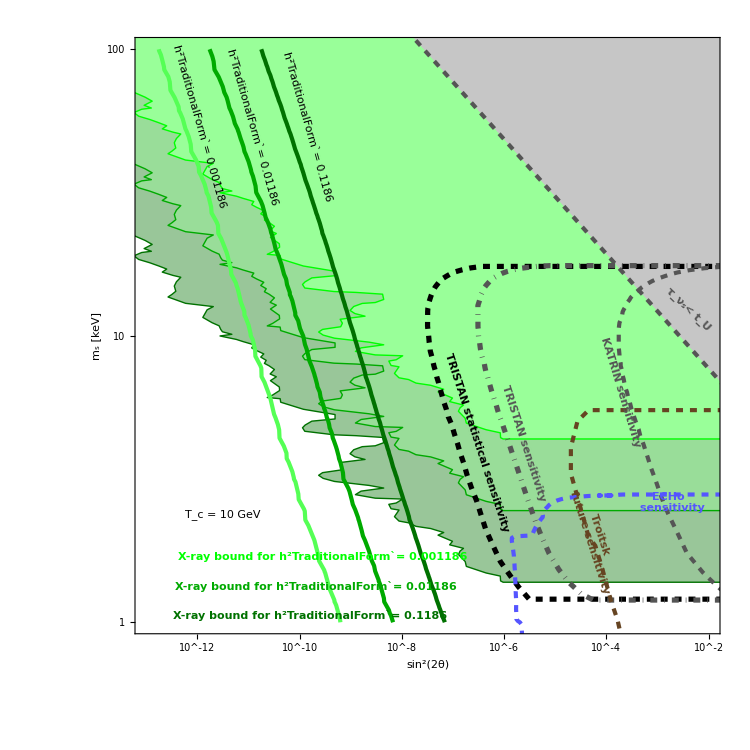

```mathematica
F2a10GeV=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
Blend[{Darker[Darker[Green]], White}, 3/5],Polygon[XtotLogl],
Blend[{Darker[Green],White}, 3/5],Polygon[Xtotred10Log],
Blend[{Green,White}, 3/5], Polygon[Xtotred100Log],
Darker[Darker[Green]],Line[XtotLogl],
Darker[Green],Line[Xtotred10Log],
Green, Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Darker[Darker[Green]],Thick,Thickness[0.004],Line[pointst10G12],
Darker[Green],Thick,Thickness[0.004],Line[pointst10G012],
Lighter[Green],Thick,Thickness[0.004],Line[pointst10G0012],
(*Darker[Darker[Green]],Thick,Thickness[0.004],Line[LinelistCock10G12Log],
Darker[Green],Thick,Thickness[0.004],Line[LinelistCock10G012Log],
Lighter[Green],Thick,Thickness[0.004],Line[LinelistCock10G0012Log],*)
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
(* + HUNTER lines *)
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 10 GeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
Darker[Darker[Green]], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
Darker[Green], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Green, Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],
FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-74 Degree],Scaled[{0.295,0.85}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-74 Degree],Scaled[{0.20,0.85}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-74 Degree],Scaled[{0.11,0.85}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
(* + labels HUNTER lines *)
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2a10GeV.pdf",F2a10GeV];
```

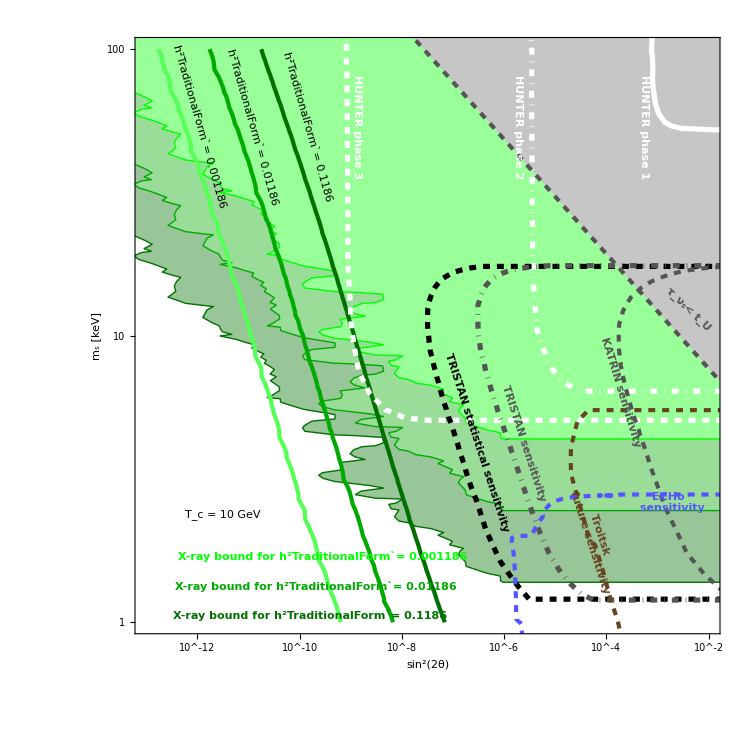

```mathematica
F2a10GeVHUNTER=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
Blend[{Darker[Darker[Green]], White}, 3/5],Polygon[XtotLogl],
Blend[{Darker[Green],White}, 3/5],Polygon[Xtotred10Log],
Blend[{Green,White}, 3/5], Polygon[Xtotred100Log],
Darker[Darker[Green]],Line[XtotLogl],
Darker[Green],Line[Xtotred10Log],
Green, Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Darker[Darker[Green]],Thick,Thickness[0.004],Line[pointst10G12],
Darker[Green],Thick,Thickness[0.004],Line[pointst10G012],
Lighter[Green],Thick,Thickness[0.004],Line[pointst10G0012],
White, Thick,Thickness[0.005],Line[HUNT1Log],
White, DotDashed,Thickness[0.005],Line[HUNT2Log],
White, Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 10 GeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
Darker[Darker[Green]], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
Darker[Green], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Green, Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],
FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-74 Degree],Scaled[{0.295,0.85}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-74 Degree],Scaled[{0.20,0.85}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-74 Degree],Scaled[{0.11,0.85}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.655,0.85}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.38,0.85}]],
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2a10GeVHUNTER.pdf",F2a10GeVHUNTER];
```

### T_c=20 MeV

#### data

For the cases with delayed production we use data simulated with our own Mathematica code.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with our own Mathematica code in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 20 MeV.

```mathematica
(*Omegatabe20M={};
For[eth=-14, eth≤-4, eth =eth+0.5, 
For[eMsn = -6, eMsn≤-3.9, eMsn=eMsn+0.1,
Omegasinge20M=Sterileabundance[10^eth,10^eMsn, 0.001, 0.02];
AppendTo[Omegatabe20M, {{10^eth,10^eMsn},Omegasinge20M}];]]*)
```

```mathematica
Omegatabe20M={{{1/100000000000000,1/1000000},1.047915060352315*^-10},{{1/100000000000000,1.2589254117941661*^-6},1.3192564677380457*^-10},{{1/100000000000000,1.584893192461111*^-6},1.6608530929685578*^-10},{{1/100000000000000,1.995262314968875*^-6},2.090896201853729*^-10},{{1/100000000000000,2.5118864315095717*^-6},2.6322871580406535*^-10},{{1/100000000000000,3.1622776601683665*^-6},3.3138570041077345*^-10},{{1/100000000000000,3.981071705534953*^-6},4.1719018196996936*^-10},{{1/100000000000000,5.0118723362726945*^-6},5.252115620115351*^-10},{{1/100000000000000,6.3095734448018915*^-6},6.61202372924253*^-10},{{1/100000000000000,7.943282347242757*^-6},8.324046212820326*^-10},{{1/100000000000000,9.999999999999918*^-6},1.0479354511019861*^-9},{{1/100000000000000,0.00001258925411794156},1.3192726650091241*^-9},{{1/100000000000000,0.00001584893192461098},1.6608659590801335*^-9},{{1/100000000000000,0.000019952623149688583},2.090906421850533*^-9},{{1/100000000000000,0.000025118864315095514},2.63229527611332*^-9},{{1/100000000000000,0.0000316227766016834},3.31386345254243*^-9},{{1/100000000000000,0.00003981071705534921},4.171906941883643*^-9},{{1/100000000000000,0.00005011872336272653},5.252119688815786*^-9},{{1/100000000000000,0.0000630957344480184},6.61202696112871*^-9},{{1/100000000000000,0.00007943282347242692},8.32404878000003*^-9},{{1/100000000000000,0.00009999999999999836},1.0479356550203797*^-8},{{1/100000000000000,0.00012589254117941468},1.3192728269872911*^-8},{{3.1622776601683796*^-14,1/1000000},3.3137983851060884*^-10},{{3.1622776601683796*^-14,1.2589254117941661*^-6},4.171855255960623*^-10},{{3.1622776601683796*^-14,1.584893192461111*^-6},5.252078632715969*^-10},{{3.1622776601683796*^-14,1.995262314968875*^-6},6.611994348852891*^-10},{{3.1622776601683796*^-14,2.5118864315095717*^-6},8.324022875019979*^-10},{{3.1622776601683796*^-14,3.1622776601683665*^-6},1.0479335973082288*^-9},{{3.1622776601683796*^-14,3.981071705534953*^-6},1.3192711924852007*^-9},{{3.1622776601683796*^-14,5.0118723362726945*^-6},1.6608647894111988*^-9},{{3.1622776601683796*^-14,6.3095734448018915*^-6},2.090905492748664*^-9},{{3.1622776601683796*^-14,7.943282347242757*^-6},2.6322945381010636*^-9},{{3.1622776601683796*^-14,9.999999999999918*^-6},3.3138628663182478*^-9},{{3.1622776601683796*^-14,0.00001258925411794156},4.17190647622911*^-9},{{3.1622776601683796*^-14,0.00001584893192461098},5.252119318933178*^-9},{{3.1622776601683796*^-14,0.000019952623149688583},6.612026667320468*^-9},{{3.1622776601683796*^-14,0.000025118864315095514},8.324048546619818*^-9},{{3.1622776601683796*^-14,0.0000316227766016834},1.047935636482327*^-8},{{3.1622776601683796*^-14,0.00003981071705534921},1.3192728122619878*^-8},{{3.1622776601683796*^-14,0.00005011872336272653},1.660866076047248*^-8},{{3.1622776601683796*^-14,0.0000630957344480184},2.0909065147608107*^-8},{{3.1622776601683796*^-14,0.00007943282347242692},2.6322953499145665*^-8},{{3.1622776601683796*^-14,0.00009999999999999836},3.313863511164828*^-8},{{3.1622776601683796*^-14,0.00012589254117941468},4.1719069884490495*^-8},{{1.*^-13,1/1000000},1.0479150603522678*^-9},{{1.*^-13,1.2589254117941661*^-6},1.3192564677379862*^-9},{{1.*^-13,1.584893192461111*^-6},1.6608530929684826*^-9},{{1.*^-13,1.995262314968875*^-6},2.090896201853635*^-9},{{1.*^-13,2.5118864315095717*^-6},2.632287158040535*^-9},{{1.*^-13,3.1622776601683665*^-6},3.3138570041075848*^-9},{{1.*^-13,3.981071705534953*^-6},4.171901819699506*^-9},{{1.*^-13,5.0118723362726945*^-6},5.2521156201151135*^-9},{{1.*^-13,6.3095734448018915*^-6},6.612023729242231*^-9},{{1.*^-13,7.943282347242757*^-6},8.324046212819952*^-9},{{1.*^-13,9.999999999999918*^-6},1.0479354511019387*^-8},{{1.*^-13,0.00001258925411794156},1.3192726650090647*^-8},{{1.*^-13,0.00001584893192461098},1.6608659590800588*^-8},{{1.*^-13,0.000019952623149688583},2.0909064218504387*^-8},{{1.*^-13,0.000025118864315095514},2.6322952761132016*^-8},{{1.*^-13,0.0000316227766016834},3.313863452542281*^-8},{{1.*^-13,0.00003981071705534921},4.171906941883454*^-8},{{1.*^-13,0.00005011872336272653},5.25211968881555*^-8},{{1.*^-13,0.0000630957344480184},6.612026961128411*^-8},{{1.*^-13,0.00007943282347242692},8.324048779999658*^-8},{{1.*^-13,0.00009999999999999836},1.0479356550203324*^-7},{{1.*^-13,0.00012589254117941468},1.3192728269872317*^-7},{{3.162277660168379*^-13,1/1000000},3.313798385105617*^-9},{{3.162277660168379*^-13,1.2589254117941661*^-6},4.1718552559600285*^-9},{{3.162277660168379*^-13,1.584893192461111*^-6},5.252078632715223*^-9},{{3.162277660168379*^-13,1.995262314968875*^-6},6.611994348851948*^-9},{{3.162277660168379*^-13,2.5118864315095717*^-6},8.324022875018794*^-9},{{3.162277660168379*^-13,3.1622776601683665*^-6},1.0479335973080795*^-8},{{3.162277660168379*^-13,3.981071705534953*^-6},1.3192711924850127*^-8},{{3.162277660168379*^-13,5.0118723362726945*^-6},1.6608647894109622*^-8},{{3.162277660168379*^-13,6.3095734448018915*^-6},2.0909054927483663*^-8},{{3.162277660168379*^-13,7.943282347242757*^-6},2.6322945381006887*^-8},{{3.162277660168379*^-13,9.999999999999918*^-6},3.3138628663177766*^-8},{{3.162277660168379*^-13,0.00001258925411794156},4.1719064762285155*^-8},{{3.162277660168379*^-13,0.00001584893192461098},5.252119318932433*^-8},{{3.162277660168379*^-13,0.000019952623149688583},6.612026667319527*^-8},{{3.162277660168379*^-13,0.000025118864315095514},8.324048546618631*^-8},{{3.162277660168379*^-13,0.0000316227766016834},1.0479356364821775*^-7},{{3.162277660168379*^-13,0.00003981071705534921},1.3192728122618*^-7},{{3.162277660168379*^-13,0.00005011872336272653},1.6608660760470116*^-7},{{3.162277660168379*^-13,0.0000630957344480184},2.0909065147605132*^-7},{{3.162277660168379*^-13,0.00007943282347242692},2.632295349914192*^-7},{{3.162277660168379*^-13,0.00009999999999999836},3.313863511164356*^-7},{{3.162277660168379*^-13,0.00012589254117941468},4.171906988448457*^-7},{{1.*^-12,1/1000000},1.0479150603517962*^-8},{{1.*^-12,1.2589254117941661*^-6},1.3192564677373925*^-8},{{1.*^-12,1.584893192461111*^-6},1.6608530929677352*^-8},{{1.*^-12,1.995262314968875*^-6},2.090896201852694*^-8},{{1.*^-12,2.5118864315095717*^-6},2.6322871580393496*^-8},{{1.*^-12,3.1622776601683665*^-6},3.313857004106093*^-8},{{1.*^-12,3.981071705534953*^-6},4.171901819697628*^-8},{{1.*^-12,5.0118723362726945*^-6},5.252115620112749*^-8},{{1.*^-12,6.3095734448018915*^-6},6.612023729239256*^-8},{{1.*^-12,7.943282347242757*^-6},8.324046212816206*^-8},{{1.*^-12,9.999999999999918*^-6},1.0479354511014674*^-7},{{1.*^-12,0.00001258925411794156},1.3192726650084711*^-7},{{1.*^-12,0.00001584893192461098},1.6608659590793116*^-7},{{1.*^-12,0.000019952623149688583},2.0909064218494975*^-7},{{1.*^-12,0.000025118864315095514},2.632295276112017*^-7},{{1.*^-12,0.0000316227766016834},3.31386345254079*^-7},{{1.*^-12,0.00003981071705534921},4.171906941881577*^-7},{{1.*^-12,0.00005011872336272653},5.252119688813187*^-7},{{1.*^-12,0.0000630957344480184},6.612026961125435*^-7},{{1.*^-12,0.00007943282347242692},8.324048779995912*^-7},{{1.*^-12,0.00009999999999999836},1.047935655019861*^-6},{{1.*^-12,0.00012589254117941468},1.3192728269866383*^-6},{{3.1622776601683794*^-12,1/1000000},3.313798385100901*^-8},{{3.1622776601683794*^-12,1.2589254117941661*^-6},4.1718552559540926*^-8},{{3.1622776601683794*^-12,1.584893192461111*^-6},5.252078632707748*^-8},{{3.1622776601683794*^-12,1.995262314968875*^-6},6.611994348842539*^-8},{{3.1622776601683794*^-12,2.5118864315095717*^-6},8.32402287500695*^-8},{{3.1622776601683794*^-12,3.1622776601683665*^-6},1.0479335973065881*^-7},{{3.1622776601683794*^-12,3.981071705534953*^-6},1.319271192483135*^-7},{{3.1622776601683794*^-12,5.0118723362726945*^-6},1.6608647894085985*^-7},{{3.1622776601683794*^-12,6.3095734448018915*^-6},2.0909054927453908*^-7},{{3.1622776601683794*^-12,7.943282347242757*^-6},2.6322945380969434*^-7},{{3.1622776601683794*^-12,9.999999999999918*^-6},3.313862866313059*^-7},{{3.1622776601683794*^-12,0.00001258925411794156},4.1719064762225794*^-7},{{3.1622776601683794*^-12,0.00001584893192461098},5.252119318924958*^-7},{{3.1622776601683794*^-12,0.000019952623149688583},6.612026667310119*^-7},{{3.1622776601683794*^-12,0.000025118864315095514},8.324048546606786*^-7},{{3.1622776601683794*^-12,0.0000316227766016834},1.0479356364806866*^-6},{{3.1622776601683794*^-12,0.00003981071705534921},1.3192728122599225*^-6},{{3.1622776601683794*^-12,0.00005011872336272653},1.660866076044648*^-6},{{3.1622776601683794*^-12,0.0000630957344480184},2.0909065147575374*^-6},{{3.1622776601683794*^-12,0.00007943282347242692},2.6322953499104454*^-6},{{3.1622776601683794*^-12,0.00009999999999999836},3.3138635111596408*^-6},{{3.1622776601683794*^-12,0.00012589254117941468},4.171906988442519*^-6},{{1.*^-11,1/1000000},1.0479150603470803*^-7},{{1.*^-11,1.2589254117941661*^-6},1.3192564677314563*^-7},{{1.*^-11,1.584893192461111*^-6},1.6608530929602616*^-7},{{1.*^-11,1.995262314968875*^-6},2.090896201843285*^-7},{{1.*^-11,2.5118864315095717*^-6},2.6322871580275044*^-7},{{1.*^-11,3.1622776601683665*^-6},3.3138570040911805*^-7},{{1.*^-11,3.981071705534953*^-6},4.171901819678854*^-7},{{1.*^-11,5.0118723362726945*^-6},5.252115620089116*^-7},{{1.*^-11,6.3095734448018915*^-6},6.612023729209502*^-7},{{1.*^-11,7.943282347242757*^-6},8.324046212778747*^-7},{{1.*^-11,9.999999999999918*^-6},1.0479354510967512*^-6},{{1.*^-11,0.00001258925411794156},1.3192726650025344*^-6},{{1.*^-11,0.00001584893192461098},1.6608659590718378*^-6},{{1.*^-11,0.000019952623149688583},2.090906421840088*^-6},{{1.*^-11,0.000025118864315095514},2.632295276100171*^-6},{{1.*^-11,0.0000316227766016834},3.3138634525258763*^-6},{{1.*^-11,0.00003981071705534921},4.171906941862803*^-6},{{1.*^-11,0.00005011872336272653},5.252119688789551*^-6},{{1.*^-11,0.0000630957344480184},6.612026961095681*^-6},{{1.*^-11,0.00007943282347242692},8.324048779958451*^-6},{{1.*^-11,0.00009999999999999836},0.00001047935655015145},{{1.*^-11,0.00012589254117941468},0.000013192728269807012},{{3.1622776601683794*^-11,1/1000000},3.313798385053746*^-7},{{3.1622776601683794*^-11,1.2589254117941661*^-6},4.171855255894727*^-7},{{3.1622776601683794*^-11,1.584893192461111*^-6},5.25207863263301*^-7},{{3.1622776601683794*^-11,1.995262314968875*^-6},6.611994348748449*^-7},{{3.1622776601683794*^-11,2.5118864315095717*^-6},8.324022874888497*^-7},{{3.1622776601683794*^-11,3.1622776601683665*^-6},1.0479335972916762*^-6},{{3.1622776601683794*^-11,3.981071705534953*^-6},1.3192711924643618*^-6},{{3.1622776601683794*^-11,5.0118723362726945*^-6},1.660864789384964*^-6},{{3.1622776601683794*^-11,6.3095734448018915*^-6},2.090905492715637*^-6},{{3.1622776601683794*^-11,7.943282347242757*^-6},2.632294538059485*^-6},{{3.1622776601683794*^-11,9.999999999999918*^-6},3.313862866265903*^-6},{{3.1622776601683794*^-11,0.00001258925411794156},4.171906476163211*^-6},{{3.1622776601683794*^-11,0.00001584893192461098},5.252119318850219*^-6},{{3.1622776601683794*^-11,0.000019952623149688583},6.612026667216029*^-6},{{3.1622776601683794*^-11,0.000025118864315095514},8.324048546488334*^-6},{{3.1622776601683794*^-11,0.0000316227766016834},0.000010479356364657743},{{3.1622776601683794*^-11,0.00003981071705534921},0.00001319272812241149},{{3.1622776601683794*^-11,0.00005011872336272653},0.00001660866076021014},{{3.1622776601683794*^-11,0.0000630957344480184},0.000020909065147277837},{{3.1622776601683794*^-11,0.00007943282347242692},0.000026322953498729882},{{3.1622776601683794*^-11,0.00009999999999999836},0.00003313863511112483},{{3.1622776601683794*^-11,0.00012589254117941468},0.000041719069883831515},{{1.*^-10,1/1000000},1.0479150602999256*^-6},{{1.*^-10,1.2589254117941661*^-6},1.3192564676720905*^-6},{{1.*^-10,1.584893192461111*^-6},1.6608530928855238*^-6},{{1.*^-10,1.995262314968875*^-6},2.0908962017491954*^-6},{{1.*^-10,2.5118864315095717*^-6},2.6322871579090528*^-6},{{1.*^-10,3.1622776601683665*^-6},3.313857003942058*^-6},{{1.*^-10,3.981071705534953*^-6},4.17190181949112*^-6},{{1.*^-10,5.0118723362726945*^-6},5.252115619852771*^-6},{{1.*^-10,6.3095734448018915*^-6},6.6120237289119615*^-6},{{1.*^-10,7.943282347242757*^-6},8.324046212404165*^-6},{{1.*^-10,9.999999999999918*^-6},0.000010479354510495943},{{1.*^-10,0.00001258925411794156},0.00001319272664943167},{{1.*^-10,0.00001584893192461098},0.000016608659589970984},{{1.*^-10,0.000019952623149688583},0.000020909064217459982},{{1.*^-10,0.000025118864315095514},0.000026322952759817177},{{1.*^-10,0.0000316227766016834},0.00003313863452376754},{{1.*^-10,0.00003981071705534921},0.00004171906941675067},{{1.*^-10,0.00005011872336272653},0.000052521196885532055},{{1.*^-10,0.0000630957344480184},0.0000661202696079814},{{1.*^-10,0.00007943282347242692},0.0000832404877958387},{{1.*^-10,0.00009999999999999836},0.00010479356549679883},{{1.*^-10,0.00012589254117941468},0.00013192728269213343},{{3.1622776601683795*^-10,1/1000000},3.3137983845821937*^-6},{{3.1622776601683795*^-10,1.2589254117941661*^-6},4.171855255301069*^-6},{{3.1622776601683795*^-10,1.584893192461111*^-6},5.252078631885633*^-6},{{3.1622776601683795*^-10,1.995262314968875*^-6},6.611994347807552*^-6},{{3.1622776601683795*^-10,2.5118864315095717*^-6},8.324022873703974*^-6},{{3.1622776601683795*^-10,3.1622776601683665*^-6},0.000010479335971425528},{{3.1622776601683795*^-10,3.981071705534953*^-6},0.00001319271192276627},{{3.1622776601683795*^-10,5.0118723362726945*^-6},0.000016608647891486193},{{3.1622776601683795*^-10,6.3095734448018915*^-6},0.00002090905492418096},{{3.1622776601683795*^-10,7.943282347242757*^-6},0.000026322945376849032},{{3.1622776601683795*^-10,9.999999999999918*^-6},0.00003313862865794332},{{3.1622776601683795*^-10,0.00001258925411794156},0.00004171906475569539},{{3.1622776601683795*^-10,0.00001584893192461098},0.000052521193181028304},{{3.1622776601683795*^-10,0.000019952623149688583},0.0000661202666627512},{{3.1622776601683795*^-10,0.000025118864315095514},0.00008324048545303802},{{3.1622776601683795*^-10,0.0000316227766016834},0.00010479356363166505},{{3.1622776601683795*^-10,0.00003981071705534921},0.00013192728120534132},{{3.1622776601683795*^-10,0.00005011872336272653},0.00016608660757846686},{{3.1622776601683795*^-10,0.0000630957344480184},0.00020909065144302427},{{3.1622776601683795*^-10,0.00007943282347242692},0.00026322953494984063},{{3.1622776601683795*^-10,0.00009999999999999836},0.0003313863510640913},{{3.1622776601683795*^-10,0.00012589254117941468},0.00041719069877894796},{{1.*^-9,1/1000000},0.000010479150598283729},{{1.*^-9,1.2589254117941661*^-6},0.000013192564670784325},{{1.*^-9,1.584893192461111*^-6},0.000016608530921381458},{{1.*^-9,1.995262314968875*^-6},0.00002090896200808297},{{1.*^-9,2.5118864315095717*^-6},0.000026322871567245265},{{1.*^-9,3.1622776601683665*^-6},0.000033138570024508254},{{1.*^-9,3.981071705534953*^-6},0.00004171901817613766},{{1.*^-9,5.0118723362726945*^-6},0.00005252115617489321},{{1.*^-9,6.3095734448018915*^-6},0.0000661202372593655},{{1.*^-9,7.943282347242757*^-6},0.00008324046208658346},{{1.*^-9,9.999999999999918*^-6},0.00010479354505780237},{{1.*^-9,0.00001258925411794156},0.00013192726643494943},{{1.*^-9,0.00001584893192461098},0.00016608659582497093},{{1.*^-9,0.000019952623149688583},0.000209090642080509},{{1.*^-9,0.000025118864315095514},0.0002632295274797185},{{1.*^-9,0.0000316227766016834},0.0003313863450885515},{{1.*^-9,0.00003981071705534921},0.00041719069397977096},{{1.*^-9,0.00005011872336272653},0.0005252119686189753},{{1.*^-9,0.0000630957344480184},0.0006612026957822728},{{1.*^-9,0.00007943282347242692},0.0008324048775838049},{{1.*^-9,0.00009999999999999836},0.001047935654496417},{{1.*^-9,0.00012589254117941468},0.001319272826327661},{{3.1622776601683795*^-9,1/1000000},0.00003313798379866668},{{3.1622776601683795*^-9,1.2589254117941661*^-6},0.00004171855249364489},{{3.1622776601683795*^-9,1.584893192461111*^-6},0.00005252078624411853},{{3.1622776601683795*^-9,1.995262314968875*^-6},0.00006611994338398566},{{3.1622776601683795*^-9,2.5118864315095717*^-6},0.00008324022861858716},{{3.1622776601683795*^-9,3.1622776601683665*^-6},0.000104793359565132},{{3.1622776601683795*^-9,3.981071705534953*^-6},0.0001319271190399273},{{3.1622776601683795*^-9,5.0118723362726945*^-6},0.00016608647867851693},{{3.1622776601683795*^-9,6.3095734448018915*^-6},0.00020909054894426867},{{3.1622776601683795*^-9,7.943282347242757*^-6},0.0002632294533939084},{{3.1622776601683795*^-9,9.999999999999918*^-6},0.0003313862861078623},{{3.1622776601683795*^-9,0.00001258925411794156},0.0004171906469632814},{{3.1622776601683795*^-9,0.00001584893192461098},0.0005252119310628934},{{3.1622776601683795*^-9,0.000019952623149688583},0.0006612026656866043},{{3.1622776601683795*^-9,0.000025118864315095514},0.0008324048533458475},{{3.1622776601683795*^-9,0.0000316227766016834},0.0010479356348254117},{{3.1622776601683795*^-9,0.00003981071705534921},0.0013192728101760554},{{3.1622776601683795*^-9,0.00005011872336272653},0.0016608660734212144},{{3.1622776601683795*^-9,0.0000630957344480184},0.0020909065114548303},{{3.1622776601683795*^-9,0.00007943282347242692},0.002632295345752583},{{3.1622776601683795*^-9,0.00009999999999999836},0.003313863505925201},{{3.1622776601683795*^-9,0.00012589254117941468},0.004171906981852749},{{1.*^-8,1/1000000},0.0001047915055112848},{{1.*^-8,1.2589254117941661*^-6},0.0001319256461141852},{{1.*^-8,1.584893192461111*^-6},0.00016608530846643656},{{1.*^-8,1.995262314968875*^-6},0.00020908961913993098},{{1.*^-8,2.5118864315095717*^-6},0.0002632287144879271},{{1.*^-8,3.1622776601683665*^-6},0.00033138569875384977},{{1.*^-8,3.981071705534953*^-6},0.00041719017988402305},{{1.*^-8,5.0118723362726945*^-6},0.0005252115593854818},{{1.*^-8,6.3095734448018915*^-6},0.0006612023696182461},{{1.*^-8,7.943282347242757*^-6},0.0008324046171200153},{{1.*^-8,9.999999999999918*^-6},0.0010479354458623148},{{1.*^-8,0.00001258925411794156},0.0013192726584127681},{{1.*^-8,0.00001584893192461098},0.001660865950775813},{{1.*^-8,0.000019952623149688583},0.002090906411396012},{{1.*^-8,0.000025118864315095514},0.002632295262951857},{{1.*^-8,0.0000316227766016834},0.0033138634359731294},{{1.*^-8,0.00003981071705534921},0.004171906921024127},{{1.*^-8,0.00005011872336272653},0.005252119662555213},{{1.*^-8,0.0000630957344480184},0.0066120269280686055},{{1.*^-8,0.00007943282347242692},0.008324048738379825},{{1.*^-8,0.00009999999999999836},0.010479356497807053},{{1.*^-8,0.00012589254117941468},0.013192728203909314},{{3.162277660168379*^-8,1/1000000},0.0003313798332711419},{{3.162277660168379*^-8,1.2589254117941661*^-6},0.0004171855189998686},{{3.162277660168379*^-8,1.584893192461111*^-6},0.0005252078549674049},{{3.162277660168379*^-8,1.995262314968875*^-6},0.0006611994244308703},{{3.162277660168379*^-8,2.5118864315095717*^-6},0.0008324022743406167},{{3.162277660168379*^-8,3.1622776601683665*^-6},0.0010479335807389932},{{3.162277660168379*^-8,3.981071705534953*^-6},0.001319271171625739},{{3.162277660168379*^-8,5.0118723362726945*^-6},0.001660864763150668},{{3.162277660168379*^-8,6.3095734448018915*^-6},0.002090905459688596},{{3.162277660168379*^-8,7.943282347242757*^-6},0.002632294496480889},{{3.162277660168379*^-8,9.999999999999918*^-6},0.003313862813921538},{{3.162277660168379*^-8,0.00001258925411794156},0.004171906410265552},{{3.162277660168379*^-8,0.00001584893192461098},0.005252119235889974},{{3.162277660168379*^-8,0.000019952623149688583},0.00661202656277526},{{3.162277660168379*^-8,0.000025118864315095514},0.00832404841500519},{{3.162277660168379*^-8,0.0000316227766016834},0.010479356199130265},{{3.162277660168379*^-8,0.00003981071705534921},0.013192727914024743},{{3.162277660168379*^-8,0.00005011872336272653},0.016608660497866752},{{3.162277660168379*^-8,0.0000630957344480184},0.02090906481700707},{{3.162277660168379*^-8,0.00007943282347242692},0.026322953082943596},{{3.162277660168379*^-8,0.00009999999999999836},0.03313863458768087},{{3.162277660168379*^-8,0.00012589254117941468},0.041719069224854514},{{1.*^-7,1/1000000},0.0010479150079576018},{{1.*^-7,1.2589254117941661*^-6},0.0013192564017760534},{{1.*^-7,1.584893192461111*^-6},0.001660853009926569},{{1.*^-7,1.995262314968875*^-6},0.0020908960973094566},{{1.*^-7,2.5118864315095717*^-6},0.0026322870264267315},{{1.*^-7,3.1622776601683665*^-6},0.003313856838415242},{{1.*^-7,3.981071705534953*^-6},0.0041719016111049015},{{1.*^-7,5.0118723362726945*^-6},0.005252115357509826},{{1.*^-7,6.3095734448018915*^-6},0.006612023398641572},{{1.*^-7,7.943282347242757*^-6},0.008324045796618227},{{1.*^-7,9.999999999999918*^-6},0.01047935398705234},{{1.*^-7,0.00001258925411794156},0.01319272599045512},{{1.*^-7,0.00001584893192461098},0.01660865876036858},{{1.*^-7,0.000019952623149688583},0.020909063173052366},{{1.*^-7,0.000025118864315095514},0.02632295144498584},{{1.*^-7,0.0000316227766016834},0.033138632868492904},{{1.*^-7,0.00003981071705534921},0.04171906733288331},{{1.*^-7,0.00005011872336272653},0.052521194262098406},{{1.*^-7,0.0000630957344480184},0.06612026630527398},{{1.*^-7,0.00007943282347242692},0.08324048363797616},{{1.*^-7,0.00009999999999999836},0.10479356026235953},{{1.*^-7,0.00012589254117941468},0.13192727610236388},{{3.162277660168379*^-7,1/1000000},0.0033137978611590727},{{3.162277660168379*^-7,1.2589254117941661*^-6},0.004171854596340844},{{3.162277660168379*^-7,1.584893192461111*^-6},0.005252077802296266},{{3.162277660168379*^-7,1.995262314968875*^-6},0.006611993303410385},{{3.162277660168379*^-7,2.5118864315095717*^-6},0.008324021558881047},{{3.162277660168379*^-7,3.1622776601683665*^-6},0.01047933431615773},{{3.162277660168379*^-7,3.981071705534953*^-6},0.013192709838904554},{{3.162277660168379*^-7,5.0118723362726945*^-6},0.016608645268057325},{{3.162277660168379*^-7,6.3095734448018915*^-6},0.02090905162147778},{{3.162277660168379*^-7,7.943282347242757*^-6},0.026322941218990547},{{3.162277660168379*^-7,9.999999999999918*^-6},0.033138623423508415},{{3.162277660168379*^-7,0.00001258925411794156},0.041719058165931314},{{3.162277660168379*^-7,0.00001584893192461098},0.052521184885006046},{{3.162277660168379*^-7,0.000019952623149688583},0.06612025621867734},{{3.162277660168379*^-7,0.000025118864315095514},0.08324047230472748},{{3.162277660168379*^-7,0.0000316227766016834},0.10479354707892226},{{3.162277660168379*^-7,0.00003981071705534921},0.1319272603666722},{{3.162277660168379*^-7,0.00005011872336272653},0.16608658134413595},{{3.162277660168379*^-7,0.0000630957344480184},0.20909061841595705},{{3.162277660168379*^-7,0.00007943282347242692},0.26322949337122403},{{3.162277660168379*^-7,0.00009999999999999836},0.33138629871970954},{{3.162277660168379*^-7,0.00012589254117941468},0.4171906328812665},{{1.*^-6,1/1000000},0.010479145364056109},{{1.*^-6,1.2589254117941661*^-6},0.013192558081186575},{{1.*^-6,1.584893192461111*^-6},0.01660852262549347},{{1.*^-6,1.995262314968875*^-6},0.020908951564118445},{{1.*^-6,2.5118864315095717*^-6},0.026322858419025024},{{1.*^-6,3.1622776601683665*^-6},0.033138553471841616},{{1.*^-6,3.981071705534953*^-6},0.04171899733753475},{{1.*^-6,5.0118723362726945*^-6},0.052521129940622455},{{1.*^-6,6.3095734448018915*^-6},0.06612020423235632},{{1.*^-6,7.943282347242757*^-6},0.08324042050802713},{{1.*^-6,9.999999999999918*^-6},0.10479349271348912},{{1.*^-6,0.00001258925411794156},0.13192720053735368},{{1.*^-6,0.00001584893192461098},0.1660865128648053},{{1.*^-6,0.000019952623149688583},0.20909053763984195},{{1.*^-6,0.000025118864315095514},0.26322939599670325},{{1.*^-6,0.0000316227766016834},0.331386179561237},{{1.*^-6,0.00003981071705534921},0.4171904855932225},{{1.*^-6,0.00005011872336272653},0.5252117062758458},{{1.*^-6,0.0000630957344480184},0.6612023655118273},{{1.*^-6,0.00007943282347242692},0.8324044617979237},{{1.*^-6,0.00009999999999999836},1.0479351310529588},{{1.*^-6,0.00012589254117941468},1.3192721673512984},{{3.162277660168379*^-6,1/1000000},0.03313793145650377},{{3.162277660168379*^-6,1.2589254117941661*^-6},0.041718486597810044},{{3.162277660168379*^-6,1.584893192461111*^-6},0.05252070328541822},{{3.162277660168379*^-6,1.995262314968875*^-6},0.06611983894456656},{{3.162277660168379*^-6,2.5118864315095717*^-6},0.08324009713666936},{{3.162277660168379*^-6,3.1622776601683665*^-6},0.1047931940388239},{{3.162277660168379*^-6,3.981071705534953*^-6},0.13192691065434942},{{3.162277660168379*^-6,5.0118723362726945*^-6},0.16608621633637724},{{3.162277660168379*^-6,6.3095734448018915*^-6},0.2090902186748916},{{3.162277660168379*^-6,7.943282347242757*^-6},0.2632290376092451},{{3.162277660168379*^-6,9.999999999999918*^-6},0.3313857626658631},{{3.162277660168379*^-6,0.00001258925411794156},0.41718998798875034},{{3.162277660168379*^-6,0.00001584893192461098},0.5252111014630327},{{3.162277660168379*^-6,0.000019952623149688583},0.6612016212821943},{{3.162277660168379*^-6,0.000025118864315095514},0.8324035385185403},{{3.162277660168379*^-6,0.0000316227766016834},1.0479339795558504},{{3.162277660168379*^-6,0.00003981071705534921},1.3192707263150822},{{3.162277660168379*^-6,0.00005011872336272653},1.660863449995599},{{3.162277660168379*^-6,0.0000630957344480184},2.090903208757524},{{3.162277660168379*^-6,0.00007943282347242692},2.6322911879027733},{{3.162277660168379*^-6,0.00009999999999999836},3.3138582715019496},{{3.162277660168379*^-6,0.00012589254117941468},4.1719003921033835},{{0.00001,1/1000000},0.10479098209323806},{{0.00001,1.2589254117941661*^-6},0.13192498716034687},{{0.00001,1.584893192461111*^-6},0.16608447888511146},{{0.00001,1.995262314968875*^-6},0.20908857475288833},{{0.00001,2.5118864315095717*^-6},0.26322739967774833},{{0.00001,3.1622776601683665*^-6},0.3313840435020981},{{0.00001,3.981071705534953*^-6},0.41718809604250673},{{0.00001,5.0118723362726945*^-6},0.525208935982041},{{0.00001,6.3095734448018915*^-6},0.6611990669470804},{{0.00001,7.943282347242757*^-6},0.8324004593018404},{{0.00001,9.999999999999918*^-6},1.047930211478149},{{0.00001,0.00001258925411794156},1.3192660687125621},{{0.00001,0.00001584893192461098},1.660857654833989},{{0.00001,0.000019952623149688583},2.090895967423396},{{0.00001,0.000025118864315095514},2.6322821147687803},{{0.00001,0.0000316227766016834},3.31384688339081},{{0.00001,0.00003981071705534921},4.171886082557026},{{0.00001,0.00005011872336272653},5.252093428478622},{{0.00001,0.0000630957344480184},6.611993901321594},{{0.00001,0.00007943282347242692},8.324007160166307},{{0.00001,0.00009999999999999836},10.479304153932807},{{0.00001,0.00012589254117941468},13.192662306866684},{{0.000031622776601683795,1/1000000},0.3313745992039594},{{0.000031622776601683795,1.2589254117941661*^-6},0.41717892960410596},{{0.000031622776601683795,1.584893192461111*^-6},0.5251995593337053},{{0.000031622776601683795,1.995262314968875*^-6},0.6611889807864868},{{0.000031622776601683795,2.5118864315095717*^-6},0.8323891265234015},{{0.000031622776601683795,3.1622776601683665*^-6},1.0479170285797341},{{0.000031622776601683795,3.981071705534953*^-6},1.319250333661596},{{0.000031622776601683795,5.0118723362726945*^-6},1.660838529684061},{{0.000031622776601683795,6.3095734448018915*^-6},2.09087243369176},{{0.000031622776601683795,7.943282347242757*^-6},2.6322529191990487},{{0.000031622776601683795,9.999999999999918*^-6},3.3138104712127974},{{0.000031622776601683795,0.00001258925411794156},4.1718405146897455},{{0.000031622776601683795,0.00001584893192461098},5.2520362782672905},{{0.000031622776601683795,0.000019952623149688583},6.61192212530957},{{0.000031622776601683795,0.000025118864315095514},8.323916936020177},{{0.000031622776601683795,0.0000316227766016834},10.47919067688967},{{0.000031622776601683795,0.00003981071705534921},13.192519533863937},{{0.000031622776601683795,0.00005011872336272653},16.60839816277887},{{0.000031622776601683795,0.0000630957344480184},20.908734556685175},{{0.000031622776601683795,0.00007943282347242692},26.3225373098075},{{0.000031622776601683795,0.00009999999999999836},33.13811116026754},{{0.000031622776601683795,0.00012589254117941468},41.718410268690775},{{0.0001,1/1000000},1.047862670867837},{{0.0001,1.2589254117941661*^-6},1.3191905123280716},{{0.0001,1.584893192461111*^-6},1.6607700592669572},{{0.0001,1.995262314968875*^-6},2.0907916680130856},{{0.0001,2.5118864315095717*^-6},2.632155557252753},{{0.0001,3.1622776601683665*^-6},3.313691328150722},{{0.0001,3.981071705534953*^-6},4.1716932457247},{{0.0001,5.0118723362726945*^-6},5.251853040797601},{{0.0001,6.3095734448018915*^-6},6.6116931612757845},{{0.0001,7.943282347242757*^-6},8.323630052254797},{{0.0001,9.999999999999918*^-6},10.47883059578762},{{0.0001,0.00001258925411794156},13.192067079795164},{{0.0001,0.00001584893192461098},16.60782924091692},{{0.0001,0.000019952623149688583},20.90801886987116},{{0.0001,0.000025118864315095514},26.321636745118283},{{0.0001,0.0000316227766016834},33.136977759368285},{{0.0001,0.00003981071705534921},41.71698367388806},{{0.0001,0.00005011872336272653},52.5185710907584},{{0.0001,0.0000630957344480184},66.11696392808105},{{0.0001,0.00007943282347242692},83.23632619116516},{{0.0001,0.00009999999999999836},104.78832634645333},{{0.0001,0.00012589254117941468},131.92068699170778}};
```

```mathematica
OmegaSNe20M = Interpolation[Omegatabe20M, InterpolationOrder->1]; //Quiet
```

#### ContourPlot (first method)

```mathematica
(*contourplots requiring different percentages of DM to be constituted by sterile neutrinos, respectively 100%, 10% and 1%*)
ple20M12=Normal@ContourPlot[OmegaSNe20M[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->150];
ple20M012=Normal@ContourPlot[OmegaSNe20M[theta2times4, Msn]==0.01186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->200];
ple20M0012=Normal@ContourPlot[OmegaSNe20M[theta2times4, Msn]==0.001186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->200];
```

```mathematica
(*list of coordinates of points (sin^2(2θ), Subscript[m, s][GeV]) identifying the right amount of DM in the parameter space *)
Linelist20M12=Cases[ ple20M12,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist20M012=Cases[ ple20M012,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist20M0012=Cases[ ple20M0012,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

```mathematica
(*rescaled valued of the mass from GeV to keV units, homogenous to the other dimensional quantities in the plots*)
Cock20M12r = Table[{Linelist20M12⟦i,1⟧,Linelist20M12⟦i,2⟧*10^6} ,{i,1,Length[Linelist20M12]}];
Cock20M012r = Table[{Linelist20M012⟦i,1⟧,Linelist20M012⟦i,2⟧*10^6} ,{i,1,Length[Linelist20M012]}];
Cock20M0012r = Table[{Linelist20M0012⟦i,1⟧,Linelist20M0012⟦i,2⟧*10^6} ,{i,1,Length[Linelist20M0012]}];
```

```mathematica
(*Log of the elements of the previous lists, better for the plot*)
LinelistCock20M12Log = Table[{Log10[Cock20M12r⟦i,1⟧], Log10[Cock20M12r⟦i,2⟧]}, {i ,1,Length[Cock20M12r]}];
LinelistCock20M012Log = Table[{Log10[Cock20M012r⟦i,1⟧], Log10[Cock20M012r⟦i,2⟧]}, {i ,1,Length[Cock20M012r]}];
LinelistCock20M0012Log = Table[{Log10[Cock20M0012r⟦i,1⟧], Log10[Cock20M0012r⟦i,2⟧]}, {i ,1,Length[Cock20M0012r]}];
```

#### plot Fig. 2(b)

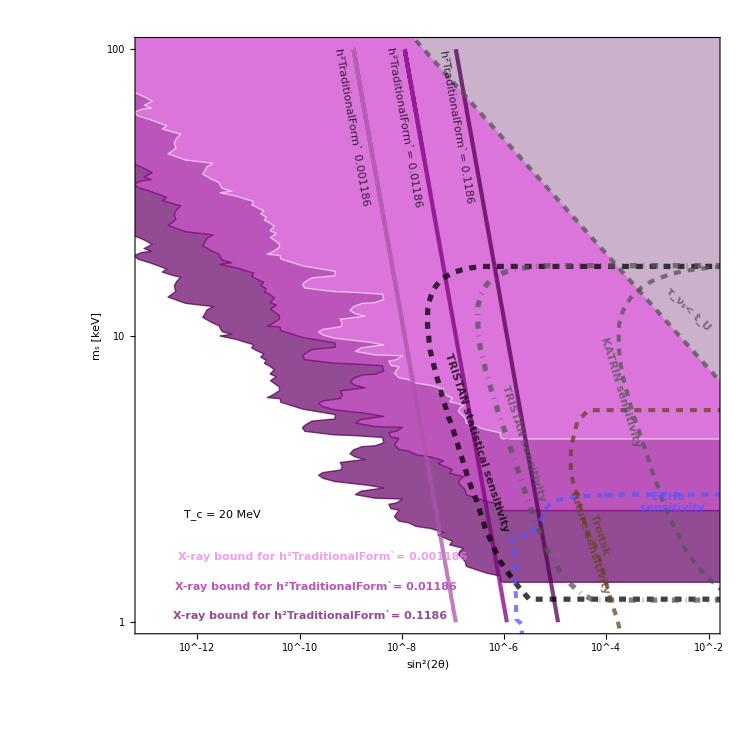

```mathematica
F220MeV=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
RGBColor[102/255,0/255,102/255, 0.7],Polygon[XtotLogl],
Blend[{RGBColor[153/255,0/255,153/255, 1], White}, 1/3],Polygon[Xtotred10Log],
Blend[{RGBColor[205/255,0/255,205/255, 0.5], White}, 1/2], Polygon[Xtotred100Log],
Darker[Purple],Line[XtotLogl],
Purple,Line[Xtotred10Log],
LightPurple, Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Darker[Purple],Thick,Thickness[0.004],Line[LinelistCock20M12Log],
Purple,Thick,Thickness[0.004],Line[LinelistCock20M012Log],
Lighter[Purple],Thick,Thickness[0.004],Line[LinelistCock20M0012Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
(* + HUNTER lines *)
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 20 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
RGBColor[102/255,0/255,102/255, 0.7], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
Blend[{RGBColor[153/255,0/255,153/255, 1], White}, 1/3],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Blend[{RGBColor[205/255,0/255,205/255, 0.5], White}, 1/2],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.55,0.85}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.46,0.85}]], 
Black, Text[Rotate[Style["h^2TraditionalForm` 0.001186"],-80 Degree],Scaled[{0.37,0.85}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
(* + labels HUNTER lines *)
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2b20MeV.pdf",F220MeV];
```

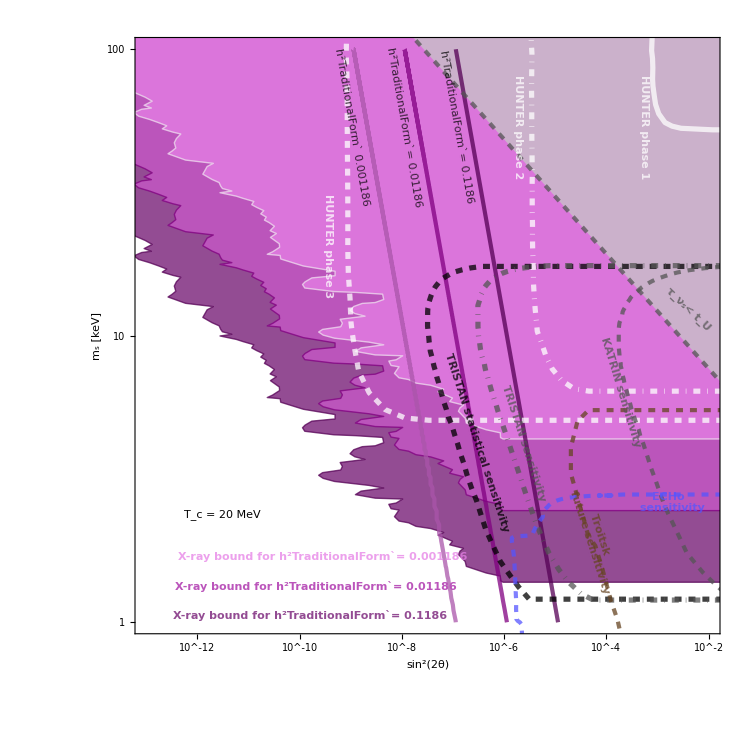

```mathematica
F220MeVHUNTER=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
RGBColor[102/255,0/255,102/255, 0.7],Polygon[XtotLogl],
Blend[{RGBColor[153/255,0/255,153/255, 1], White}, 1/3],Polygon[Xtotred10Log],
Blend[{RGBColor[205/255,0/255,205/255, 0.5], White}, 1/2], Polygon[Xtotred100Log],
Darker[Purple],Line[XtotLogl],
Purple,Line[Xtotred10Log],
LightPurple, Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Darker[Purple],Thick,Thickness[0.004],Line[LinelistCock20M12Log],
Purple,Thick,Thickness[0.004],Line[LinelistCock20M012Log],
Lighter[Purple],Thick,Thickness[0.004],Line[LinelistCock20M0012Log],
White, Thick,Thickness[0.005],Line[HUNT1Log],
White, DotDashed,Thickness[0.005],Line[HUNT2Log],
White, Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 20 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
RGBColor[102/255,0/255,102/255, 0.7], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
Blend[{RGBColor[153/255,0/255,153/255, 1], White}, 1/3],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Blend[{RGBColor[205/255,0/255,205/255, 0.5], White}, 1/2],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.55,0.85}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.46,0.85}]], 
Black, Text[Rotate[Style["h^2TraditionalForm` 0.001186"],-80 Degree],Scaled[{0.37,0.85}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.655,0.85}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.33,0.65}]],
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2b20MeVHUNTER.pdf",F220MeVHUNTER];
```

### T_c=10 MeV

#### data

For the cases with delayed production we use data simulated with our own Mathematica code.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with our own Mathematica code in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 10 MeV.

```mathematica
(*Omegatabe10M={};
For[eth=-14, eth≤-4, eth =eth+0.5, 
For[eMsn = -6, eMsn≤-3.9, eMsn=eMsn+0.1,
Omegasinge10M=Sterileabundance[10^eth,10^eMsn, 0.001, 0.01];
AppendTo[Omegatabe10M, {{10^eth,10^eMsn},Omegasinge10M}];]]*)
```

```mathematica
Omegatabe10M ={{{1/100000000000000,1/1000000},1.2686944355392753*^-11},{{1/100000000000000,1.2589254117941661*^-6},1.597191843119823*^-11},{{1/100000000000000,1.584893192461111*^-6},2.0107455405360945*^-11},{{1/100000000000000,1.995262314968875*^-6},2.531378770206657*^-11},{{1/100000000000000,2.5118864315095717*^-6},3.1868171501101246*^-11},{{1/100000000000000,3.1622776601683665*^-6},4.011965164044498*^-11},{{1/100000000000000,3.981071705534953*^-6},5.050764952669229*^-11},{{1/100000000000000,5.0118723362726945*^-6},6.358536392731178*^-11},{{1/100000000000000,6.3095734448018915*^-6},8.004923082226321*^-11},{{1/100000000000000,7.943282347242757*^-6},1.0077601115949714*^-10},{{1/100000000000000,9.999999999999918*^-6},1.2686948157255814*^-10},{{1/100000000000000,0.00001258925411794156},1.5971921451126296*^-10},{{1/100000000000000,0.00001584893192461098},2.0107457804175476*^-10},{{1/100000000000000,0.000019952623149688583},2.5313789607512836*^-10},{{1/100000000000000,0.000025118864315095514},3.186817301465106*^-10},{{1/100000000000000,0.0000316227766016834},4.011965284270025*^-10},{{1/100000000000000,0.00003981071705534921},5.050765048167748*^-10},{{1/100000000000000,0.00005011872336272653},6.358536468588328*^-10},{{1/100000000000000,0.0000630957344480184},8.004923142481776*^-10},{{1/100000000000000,0.00007943282347242692},1.0077601163812293*^-9},{{1/100000000000000,0.00009999999999999836},1.2686948195274372*^-9},{{1/100000000000000,0.00012589254117941468},1.597192148132548*^-9},{{3.1622776601683796*^-14,1/1000000},4.0119640710857394*^-11},{{3.1622776601683796*^-14,1.2589254117941661*^-6},5.050764084500921*^-11},{{3.1622776601683796*^-14,1.584893192461111*^-6},6.358535703120416*^-11},{{3.1622776601683796*^-14,1.995262314968875*^-6},8.004922534448931*^-11},{{3.1622776601683796*^-14,2.5118864315095717*^-6},1.0077600680834604*^-10},{{3.1622776601683796*^-14,3.1622776601683665*^-6},1.268694781163155*^-10},{{3.1622776601683796*^-14,3.981071705534953*^-6},1.5971921176587129*^-10},{{3.1622776601683796*^-14,5.0118723362726945*^-6},2.0107457586101222*^-10},{{3.1622776601683796*^-14,6.3095734448018915*^-6},2.531378943429023*^-10},{{3.1622776601683796*^-14,7.943282347242757*^-6},3.1868172877055373*^-10},{{3.1622776601683796*^-14,9.999999999999918*^-6},4.0119652733404*^-10},{{3.1622776601683796*^-14,0.00001258925411794156},5.050765039486028*^-10},{{3.1622776601683796*^-14,0.00001584893192461098},6.358536461692176*^-10},{{3.1622776601683796*^-14,0.000019952623149688583},8.004923137003946*^-10},{{3.1622776601683796*^-14,0.000025118864315095514},1.0077601159461073*^-9},{{3.1622776601683796*^-14,0.0000316227766016834},1.2686948191818045*^-9},{{3.1622776601683796*^-14,0.00003981071705534921},1.5971921478579966*^-9},{{3.1622776601683796*^-14,0.00005011872336272653},2.0107457825982596*^-9},{{3.1622776601683796*^-14,0.0000630957344480184},2.531378962483471*^-9},{{3.1622776601683796*^-14,0.00007943282347242692},3.1868173028410138*^-9},{{3.1622776601683796*^-14,0.00009999999999999836},4.011965285362925*^-9},{{3.1622776601683796*^-14,0.00012589254117941468},5.050765049035846*^-9},{{1.*^-13,1/1000000},1.268694435539218*^-10},{{1.*^-13,1.2589254117941661*^-6},1.5971918431197516*^-10},{{1.*^-13,1.584893192461111*^-6},2.0107455405360041*^-10},{{1.*^-13,1.995262314968875*^-6},2.5313787702065423*^-10},{{1.*^-13,2.5118864315095717*^-6},3.1868171501099826*^-10},{{1.*^-13,3.1622776601683665*^-6},4.0119651640443176*^-10},{{1.*^-13,3.981071705534953*^-6},5.050764952669002*^-10},{{1.*^-13,5.0118723362726945*^-6},6.358536392730892*^-10},{{1.*^-13,6.3095734448018915*^-6},8.004923082225961*^-10},{{1.*^-13,7.943282347242757*^-6},1.0077601115949264*^-9},{{1.*^-13,9.999999999999918*^-6},1.2686948157255244*^-9},{{1.*^-13,0.00001258925411794156},1.5971921451125577*^-9},{{1.*^-13,0.00001584893192461098},2.010745780417457*^-9},{{1.*^-13,0.000019952623149688583},2.5313789607511692*^-9},{{1.*^-13,0.000025118864315095514},3.1868173014649624*^-9},{{1.*^-13,0.0000316227766016834},4.011965284269845*^-9},{{1.*^-13,0.00003981071705534921},5.05076504816752*^-9},{{1.*^-13,0.00005011872336272653},6.358536468588042*^-9},{{1.*^-13,0.0000630957344480184},8.004923142481414*^-9},{{1.*^-13,0.00007943282347242692},1.0077601163811839*^-8},{{1.*^-13,0.00009999999999999836},1.2686948195273802*^-8},{{1.*^-13,0.00012589254117941468},1.597192148132476*^-8},{{3.162277660168379*^-13,1/1000000},4.0119640710851676*^-10},{{3.162277660168379*^-13,1.2589254117941661*^-6},5.050764084500203*^-10},{{3.162277660168379*^-13,1.584893192461111*^-6},6.35853570311951*^-10},{{3.162277660168379*^-13,1.995262314968875*^-6},8.004922534447791*^-10},{{3.162277660168379*^-13,2.5118864315095717*^-6},1.0077600680833168*^-9},{{3.162277660168379*^-13,3.1622776601683665*^-6},1.2686947811629743*^-9},{{3.162277660168379*^-13,3.981071705534953*^-6},1.597192117658486*^-9},{{3.162277660168379*^-13,5.0118723362726945*^-6},2.0107457586098353*^-9},{{3.162277660168379*^-13,6.3095734448018915*^-6},2.5313789434286635*^-9},{{3.162277660168379*^-13,7.943282347242757*^-6},3.186817287705084*^-9},{{3.162277660168379*^-13,9.999999999999918*^-6},4.011965273339831*^-9},{{3.162277660168379*^-13,0.00001258925411794156},5.050765039485308*^-9},{{3.162277660168379*^-13,0.00001584893192461098},6.358536461691271*^-9},{{3.162277660168379*^-13,0.000019952623149688583},8.00492313700281*^-9},{{3.162277660168379*^-13,0.000025118864315095514},1.007760115945964*^-8},{{3.162277660168379*^-13,0.0000316227766016834},1.268694819181624*^-8},{{3.162277660168379*^-13,0.00003981071705534921},1.5971921478577692*^-8},{{3.162277660168379*^-13,0.00005011872336272653},2.010745782597973*^-8},{{3.162277660168379*^-13,0.0000630957344480184},2.5313789624831105*^-8},{{3.162277660168379*^-13,0.00007943282347242692},3.186817302840559*^-8},{{3.162277660168379*^-13,0.00009999999999999836},4.011965285362356*^-8},{{3.162277660168379*^-13,0.00012589254117941468},5.0507650490351276*^-8},{{1.*^-12,1/1000000},1.268694435538647*^-9},{{1.*^-12,1.2589254117941661*^-6},1.5971918431190326*^-9},{{1.*^-12,1.584893192461111*^-6},2.010745540535099*^-9},{{1.*^-12,1.995262314968875*^-6},2.5313787702054035*^-9},{{1.*^-12,2.5118864315095717*^-6},3.186817150108548*^-9},{{1.*^-12,3.1622776601683665*^-6},4.011965164042512*^-9},{{1.*^-12,3.981071705534953*^-6},5.050764952666729*^-9},{{1.*^-12,5.0118723362726945*^-6},6.358536392728031*^-9},{{1.*^-12,6.3095734448018915*^-6},8.004923082222357*^-9},{{1.*^-12,7.943282347242757*^-6},1.0077601115944726*^-8},{{1.*^-12,9.999999999999918*^-6},1.2686948157249536*^-8},{{1.*^-12,0.00001258925411794156},1.597192145111839*^-8},{{1.*^-12,0.00001584893192461098},2.0107457804165522*^-8},{{1.*^-12,0.000019952623149688583},2.53137896075003*^-8},{{1.*^-12,0.000025118864315095514},3.186817301463528*^-8},{{1.*^-12,0.0000316227766016834},4.0119652842680395*^-8},{{1.*^-12,0.00003981071705534921},5.0507650481652466*^-8},{{1.*^-12,0.00005011872336272653},6.358536468585181*^-8},{{1.*^-12,0.0000630957344480184},8.004923142477811*^-8},{{1.*^-12,0.00007943282347242692},1.0077601163807303*^-7},{{1.*^-12,0.00009999999999999836},1.2686948195268093*^-7},{{1.*^-12,0.00012589254117941468},1.5971921481317573*^-7},{{3.1622776601683794*^-12,1/1000000},4.011964071079458*^-9},{{3.1622776601683794*^-12,1.2589254117941661*^-6},5.050764084493014*^-9},{{3.1622776601683794*^-12,1.584893192461111*^-6},6.3585357031104614*^-9},{{3.1622776601683794*^-12,1.995262314968875*^-6},8.004922534436399*^-9},{{3.1622776601683794*^-12,2.5118864315095717*^-6},1.0077600680818827*^-8},{{3.1622776601683794*^-12,3.1622776601683665*^-6},1.2686947811611686*^-8},{{3.1622776601683794*^-12,3.981071705534953*^-6},1.597192117656213*^-8},{{3.1622776601683794*^-12,5.0118723362726945*^-6},2.0107457586069742*^-8},{{3.1622776601683794*^-12,6.3095734448018915*^-6},2.5313789434250608*^-8},{{3.1622776601683794*^-12,7.943282347242757*^-6},3.1868172877005486*^-8},{{3.1622776601683794*^-12,9.999999999999918*^-6},4.011965273334122*^-8},{{3.1622776601683794*^-12,0.00001258925411794156},5.0507650394781204*^-8},{{3.1622776601683794*^-12,0.00001584893192461098},6.358536461682224*^-8},{{3.1622776601683794*^-12,0.000019952623149688583},8.004923136991416*^-8},{{3.1622776601683794*^-12,0.000025118864315095514},1.00776011594453*^-7},{{3.1622776601683794*^-12,0.0000316227766016834},1.2686948191798188*^-7},{{3.1622776601683794*^-12,0.00003981071705534921},1.5971921478554962*^-7},{{3.1622776601683794*^-12,0.00005011872336272653},2.010745782595112*^-7},{{3.1622776601683794*^-12,0.0000630957344480184},2.531378962479508*^-7},{{3.1622776601683794*^-12,0.00007943282347242692},3.186817302836025*^-7},{{3.1622776601683794*^-12,0.00009999999999999836},4.0119652853566467*^-7},{{3.1622776601683794*^-12,0.00012589254117941468},5.05076504902794*^-7},{{1.*^-11,1/1000000},1.2686944355329375*^-8},{{1.*^-11,1.2589254117941661*^-6},1.597191843111845*^-8},{{1.*^-11,1.584893192461111*^-6},2.0107455405260507*^-8},{{1.*^-11,1.995262314968875*^-6},2.5313787701940123*^-8},{{1.*^-11,2.5118864315095717*^-6},3.186817150094207*^-8},{{1.*^-11,3.1622776601683665*^-6},4.011965164024459*^-8},{{1.*^-11,3.981071705534953*^-6},5.050764952644*^-8},{{1.*^-11,5.0118723362726945*^-6},6.358536392699417*^-8},{{1.*^-11,6.3095734448018915*^-6},8.004923082186337*^-8},{{1.*^-11,7.943282347242757*^-6},1.0077601115899379*^-7},{{1.*^-11,9.999999999999918*^-6},1.2686948157192442*^-7},{{1.*^-11,0.00001258925411794156},1.5971921451046518*^-7},{{1.*^-11,0.00001584893192461098},2.010745780407504*^-7},{{1.*^-11,0.000019952623149688583},2.5313789607386397*^-7},{{1.*^-11,0.000025118864315095514},3.1868173014491873*^-7},{{1.*^-11,0.0000316227766016834},4.0119652842499865*^-7},{{1.*^-11,0.00003981071705534921},5.050765048142521*^-7},{{1.*^-11,0.00005011872336272653},6.358536468556567*^-7},{{1.*^-11,0.0000630957344480184},8.004923142441789*^-7},{{1.*^-11,0.00007943282347242692},1.0077601163761956*^-6},{{1.*^-11,0.00009999999999999836},1.2686948195211001*^-6},{{1.*^-11,0.00012589254117941468},1.5971921481245698*^-6},{{3.1622776601683794*^-11,1/1000000},4.011964071022367*^-8},{{3.1622776601683794*^-11,1.2589254117941661*^-6},5.050764084421141*^-8},{{3.1622776601683794*^-11,1.584893192461111*^-6},6.358535703019978*^-8},{{3.1622776601683794*^-11,1.995262314968875*^-6},8.004922534322486*^-8},{{3.1622776601683794*^-11,2.5118864315095717*^-6},1.007760068067542*^-7},{{3.1622776601683794*^-11,3.1622776601683665*^-6},1.2686947811431147*^-7},{{3.1622776601683794*^-11,3.981071705534953*^-6},1.5971921176334845*^-7},{{3.1622776601683794*^-11,5.0118723362726945*^-6},2.0107457585783607*^-7},{{3.1622776601683794*^-11,6.3095734448018915*^-6},2.5313789433890385*^-7},{{3.1622776601683794*^-11,7.943282347242757*^-6},3.1868172876551996*^-7},{{3.1622776601683794*^-11,9.999999999999918*^-6},4.01196527327703*^-7},{{3.1622776601683794*^-11,0.00001258925411794156},5.050765039406248*^-7},{{3.1622776601683794*^-11,0.00001584893192461098},6.358536461591739*^-7},{{3.1622776601683794*^-11,0.000019952623149688583},8.004923136877504*^-7},{{3.1622776601683794*^-11,0.000025118864315095514},1.007760115930189*^-6},{{3.1622776601683794*^-11,0.0000316227766016834},1.2686948191617648*^-6},{{3.1622776601683794*^-11,0.00003981071705534921},1.5971921478327678*^-6},{{3.1622776601683794*^-11,0.00005011872336272653},2.0107457825664985*^-6},{{3.1622776601683794*^-11,0.0000630957344480184},2.5313789624434863*^-6},{{3.1622776601683794*^-11,0.00007943282347242692},3.186817302790676*^-6},{{3.1622776601683794*^-11,0.00009999999999999836},4.011965285299555*^-6},{{3.1622776601683794*^-11,0.00012589254117941468},5.0507650489560675*^-6},{{1.*^-10,1/1000000},1.2686944354758466*^-7},{{1.*^-10,1.2589254117941661*^-6},1.5971918430399714*^-7},{{1.*^-10,1.584893192461111*^-6},2.010745540435567*^-7},{{1.*^-10,1.995262314968875*^-6},2.5313787700801*^-7},{{1.*^-10,2.5118864315095717*^-6},3.1868171499508013*^-7},{{1.*^-10,3.1622776601683665*^-6},4.0119651638439206*^-7},{{1.*^-10,3.981071705534953*^-6},5.050764952416716*^-7},{{1.*^-10,5.0118723362726945*^-6},6.358536392413281*^-7},{{1.*^-10,6.3095734448018915*^-6},8.004923081826116*^-7},{{1.*^-10,7.943282347242757*^-6},1.0077601115445888*^-6},{{1.*^-10,9.999999999999918*^-6},1.268694815662153*^-6},{{1.*^-10,0.00001258925411794156},1.5971921450327782*^-6},{{1.*^-10,0.00001584893192461098},2.0107457803170204*^-6},{{1.*^-10,0.000019952623149688583},2.5313789606247274*^-6},{{1.*^-10,0.000025118864315095514},3.186817301305781*^-6},{{1.*^-10,0.0000316227766016834},4.011965284069447*^-6},{{1.*^-10,0.00003981071705534921},5.050765047915236*^-6},{{1.*^-10,0.00005011872336272653},6.358536468270434*^-6},{{1.*^-10,0.0000630957344480184},8.004923142081569*^-6},{{1.*^-10,0.00007943282347242692},0.000010077601163308465},{{1.*^-10,0.00009999999999999836},0.00001268694819464009},{{1.*^-10,0.00012589254117941468},0.000015971921480526964},{{3.1622776601683795*^-10,1/1000000},4.0119640704514544*^-7},{{3.1622776601683795*^-10,1.2589254117941661*^-6},5.050764083702405*^-7},{{3.1622776601683795*^-10,1.584893192461111*^-6},6.358535702115142*^-7},{{3.1622776601683795*^-10,1.995262314968875*^-6},8.004922533183369*^-7},{{3.1622776601683795*^-10,2.5118864315095717*^-6},1.0077600679241352*^-6},{{3.1622776601683795*^-10,3.1622776601683665*^-6},1.2686947809625766*^-6},{{3.1622776601683795*^-10,3.981071705534953*^-6},1.5971921174062006*^-6},{{3.1622776601683795*^-10,5.0118723362726945*^-6},2.0107457582922275*^-6},{{3.1622776601683795*^-10,6.3095734448018915*^-6},2.531378943028817*^-6},{{3.1622776601683795*^-10,7.943282347242757*^-6},3.1868172872017068*^-6},{{3.1622776601683795*^-10,9.999999999999918*^-6},4.011965272706118*^-6},{{3.1622776601683795*^-10,0.00001258925411794156},5.050765038687511*^-6},{{3.1622776601683795*^-10,0.00001584893192461098},6.358536460686904*^-6},{{3.1622776601683795*^-10,0.000019952623149688583},8.004923135738385*^-6},{{3.1622776601683795*^-10,0.000025118864315095514},0.00001007760115786783},{{3.1622776601683795*^-10,0.0000316227766016834},0.000012686948189812265},{{3.1622776601683795*^-10,0.00003981071705534921},0.000015971921476054837},{{3.1622776601683795*^-10,0.00005011872336272653},0.000020107457822803644},{{3.1622776601683795*^-10,0.0000630957344480184},0.00002531378962083265},{{3.1622776601683795*^-10,0.00007943282347242692},0.00003186817302337185},{{3.1622776601683795*^-10,0.00009999999999999836},0.000040119652847286424},{{3.1622776601683795*^-10,0.00012589254117941468},0.00005050765048237331},{{1.*^-9,1/1000000},1.2686944349049344*^-6},{{1.*^-9,1.2589254117941661*^-6},1.5971918423212353*^-6},{{1.*^-9,1.584893192461111*^-6},2.010745539530732*^-6},{{1.*^-9,1.995262314968875*^-6},2.5313787689409796*^-6},{{1.*^-9,2.5118864315095717*^-6},3.186817148516733*^-6},{{1.*^-9,3.1622776601683665*^-6},4.011965162038536*^-6},{{1.*^-9,3.981071705534953*^-6},5.050764950143872*^-6},{{1.*^-9,5.0118723362726945*^-6},6.358536389551941*^-6},{{1.*^-9,6.3095734448018915*^-6},8.004923078223899*^-6},{{1.*^-9,7.943282347242757*^-6},0.000010077601110910966},{{1.*^-9,9.999999999999918*^-6},0.000012686948150912401},{{1.*^-9,0.00001258925411794156},0.000015971921443140417},{{1.*^-9,0.00001584893192461098},0.00002010745779412185},{{1.*^-9,0.000019952623149688583},0.000025313789594856075},{{1.*^-9,0.000025118864315095514},0.00003186817299871713},{{1.*^-9,0.0000316227766016834},0.00004011965282264063},{{1.*^-9,0.00003981071705534921},0.000050507650456423915},{{1.*^-9,0.00005011872336272653},0.00006358536465409094},{{1.*^-9,0.0000630957344480184},0.00008004923138479355},{{1.*^-9,0.00007943282347242692},0.00010077601158773542},{{1.*^-9,0.00009999999999999836},0.00012686948188930962},{{1.*^-9,0.00012589254117941468},0.00015971921473339592},{{3.1622776601683795*^-9,1/1000000},4.011964064742331*^-6},{{3.1622776601683795*^-9,1.2589254117941661*^-6},5.050764076515043*^-6},{{3.1622776601683795*^-9,1.584893192461111*^-6},6.358535693066789*^-6},{{3.1622776601683795*^-9,1.995262314968875*^-6},8.004922521792162*^-6},{{3.1622776601683795*^-9,2.5118864315095717*^-6},0.000010077600664900675},{{3.1622776601683795*^-9,3.1622776601683665*^-6},0.000012686947791571919},{{3.1622776601683795*^-9,3.981071705534953*^-6},0.000015971921151333562},{{3.1622776601683795*^-9,5.0118723362726945*^-6},0.00002010745755430885},{{3.1622776601683795*^-9,6.3095734448018915*^-6},0.000025313789394266015},{{3.1622776601683795*^-9,7.943282347242757*^-6},0.000031868172826667874},{{3.1622776601683795*^-9,9.999999999999918*^-6},0.00004011965266996991},{{3.1622776601683795*^-9,0.00001258925411794156},0.00005050765031500145},{{3.1622776601683795*^-9,0.00001584893192461098},0.00006358536451638547},{{3.1622776601683795*^-9,0.000019952623149688583},0.00008004923124347178},{{3.1622776601683795*^-9,0.000025118864315095514},0.00010077601143527146},{{3.1622776601683795*^-9,0.0000316227766016834},0.0001268694817175842},{{3.1622776601683795*^-9,0.00003981071705534921},0.00015971921453326388},{{3.1622776601683795*^-9,0.00005011872336272653},0.00020107457794190227},{{3.1622776601683795*^-9,0.0000630957344480184},0.00025313789584810486},{{3.1622776601683795*^-9,0.00007943282347242692},0.0003186817297802262},{{3.1622776601683795*^-9,0.00009999999999999836},0.00040119652790195125},{{3.1622776601683795*^-9,0.00012589254117941468},0.000505076504104996},{{1.*^-8,1/1000000},0.000012686944291958112},{{1.*^-8,1.2589254117941661*^-6},0.00001597191835133873},{{1.*^-8,1.584893192461111*^-6},0.000020107455304823777},{{1.*^-8,1.995262314968875*^-6},0.000025313787575497765},{{1.*^-8,2.5118864315095717*^-6},0.000031868171341760564},{{1.*^-8,3.1622776601683665*^-6},0.00004011965143984693},{{1.*^-8,3.981071705534953*^-6},0.00005050764927415431},{{1.*^-8,5.0118723362726945*^-6},0.00006358536360938527},{{1.*^-8,6.3095734448018915*^-6},0.00008004923042201749},{{1.*^-8,7.943282347242757*^-6},0.00010077601065561762},{{1.*^-8,9.999999999999918*^-6},0.0001268694809382114},{{1.*^-8,0.00001258925411794156},0.0001597192137126677},{{1.*^-8,0.00001584893192461098},0.00020107457703638288},{{1.*^-8,0.000019952623149688583},0.00025313789480944015},{{1.*^-8,0.000025118864315095514},0.0003186817285531035},{{1.*^-8,0.0000316227766016834},0.00040119652642102183},{{1.*^-8,0.00003981071705534921},0.0005050765022913946},{{1.*^-8,0.00005011872336272653},0.0006358536436795676},{{1.*^-8,0.0000630957344480184},0.0008004923102457192},{{1.*^-8,0.00007943282347242692},0.0010077601113424324},{{1.*^-8,0.00009999999999999836},0.0012686948131839662},{{1.*^-8,0.00012589254117941468},0.0015971921401465893},{{3.162277660168379*^-8,1/1000000},0.00004011964007651101},{{3.162277660168379*^-8,1.2589254117941661*^-6},0.000050507640046414255},{{3.162277660168379*^-8,1.584893192461111*^-6},0.00006358535602583252},{{3.162277660168379*^-8,1.995262314968875*^-6},0.0000800492240788013},{{3.162277660168379*^-8,2.5118864315095717*^-6},0.00010077600521493914},{{3.162277660168379*^-8,3.1622776601683665*^-6},0.000126869476110335},{{3.162277660168379*^-8,3.981071705534953*^-6},0.00015971920924049148},{{3.162277660168379*^-8,5.0118723362726945*^-6},0.00020107457268174725},{{3.162277660168379*^-8,6.3095734448018915*^-6},0.00025313789034044483},{{3.162277660168379*^-8,7.943282347242757*^-6},0.0003186817237317583},{{3.162277660168379*^-8,9.999999999999918*^-6},0.0004011965209905726},{{3.162277660168379*^-8,0.00001258925411794156},0.00050507649596265},{{3.162277660168379*^-8,0.00001584893192461098},0.0006358536361154988},{{3.162277660168379*^-8,0.000019952623149688583},0.0008004923010435127},{{3.162277660168379*^-8,0.000025118864315095514},0.0010077601000120368},{{3.162277660168379*^-8,0.0000316227766016834},0.0012686947991219976},{{3.162277660168379*^-8,0.00003981071705534921},0.0015971921226041956},{{3.162277660168379*^-8,0.00005011872336272653},0.002010745750805606},{{3.162277660168379*^-8,0.0000630957344480184},0.0025313789224588883},{{3.162277660168379*^-8,0.00007943282347242692},0.0031868172524530435},{{3.162277660168379*^-8,0.00009999999999999836},0.004011965221928221},{{3.162277660168379*^-8,0.00012589254117941468},0.005050764969176262},{{1.*^-7,1/1000000},0.00012686943721045853},{{1.*^-7,1.2589254117941661*^-6},0.00015971917632602624},{{1.*^-7,1.584893192461111*^-6},0.0002010745439998849},{{1.*^-7,1.995262314968875*^-6},0.0002531378643637753},{{1.*^-7,2.5118864315095717*^-6},0.00031868169907693075},{{1.*^-7,3.1622776601683665*^-6},0.0004011964963446286},{{1.*^-7,3.981071705534953*^-6},0.0005050764700131036},{{1.*^-7,5.0118723362726945*^-6},0.0006358536074804425},{{1.*^-7,6.3095734448018915*^-6},0.000800492268198025},{{1.*^-7,7.943282347242757*^-6},0.0010077600612069762},{{1.*^-7,9.999999999999918*^-6},0.0012686947522908532},{{1.*^-7,0.00001258925411794156},0.0015971920652530374},{{1.*^-7,0.00001584893192461098},0.0020107456798802775},{{1.*^-7,0.000019952623149688583},0.0025313788341823585},{{1.*^-7,0.000025118864315095514},0.003186817142124268},{{1.*^-7,0.0000316227766016834},0.004011965083671792},{{1.*^-7,0.00003981071705534921},0.005050764795629527},{{1.*^-7,0.00005011872336272653},0.0063585361506615316},{{1.*^-7,0.0000630957344480184},0.008004922742235623},{{1.*^-7,0.00007943282347242692},0.010077600659932188},{{1.*^-7,0.00009999999999999836},0.012686947560926792},{{1.*^-7,0.00012589254117941468},0.015971920682728964},{{3.162277660168379*^-7,1/1000000},0.00040119634367389765},{{3.162277660168379*^-7,1.2589254117941661*^-6},0.0005050763285905485},{{3.162277660168379*^-7,1.584893192461111*^-6},0.0006358534697748182},{{3.162277660168379*^-7,1.995262314968875*^-6},0.0008004921268760167},{{3.162277660168379*^-7,2.5118864315095717*^-6},0.0010077599087426764},{{3.162277660168379*^-7,3.1622776601683665*^-6},0.0012686945805649857},{{3.162277660168379*^-7,3.981071705534953*^-6},0.0015971918651205754},{{3.162277660168379*^-7,5.0118723362726945*^-6},0.0020107454406834376},{{3.162277660168379*^-7,6.3095734448018915*^-6},0.002531378543183038},{{3.162277660168379*^-7,7.943282347242757*^-6},0.0031868167838256913},{{3.162277660168379*^-7,9.999999999999918*^-6},0.004011964638993256},{{3.162277660168379*^-7,0.00001258925411794156},0.005050764240890281},{{3.162277660168379*^-7,0.00001584893192461098},0.006358535456319693},{{3.162277660168379*^-7,0.000019952623149688583},0.008004921871314968},{{3.162277660168379*^-7,0.000025118864315095514},0.010077599566053039},{{3.162277660168379*^-7,0.0000316227766016834},0.012686946185836143},{{3.162277660168379*^-7,0.00003981071705534921},0.015971918953198303},{{3.162277660168379*^-7,0.00005011872336272653},0.020107454646715303},{{3.162277660168379*^-7,0.0000630957344480184},0.025313785622374047},{{3.162277660168379*^-7,0.00007943282347242692},0.03186816798961015},{{3.162277660168379*^-7,0.00009999999999999836},0.0401196465101548},{{3.162277660168379*^-7,0.00012589254117941468},0.05050764250439508},{{1.*^-6,1/1000000},0.0012686938011928898},{{1.*^-6,1.2589254117941661*^-6},0.0015971910445248606},{{1.*^-6,1.584893192461111*^-6},0.0020107445351644606},{{1.*^-6,1.995262314968875*^-6},0.0025313775045186456},{{1.*^-6,2.5118864315095717*^-6},0.003186815556703235},{{1.*^-6,3.1622776601683665*^-6},0.004011963158064001},{{1.*^-6,3.981071705534953*^-6},0.005050762427289349},{{1.*^-6,5.0118723362726945*^-6},0.006358533213466227},{{1.*^-6,6.3095734448018915*^-6},0.008004919079768845},{{1.*^-6,7.943282347242757*^-6},0.010077596077154255},{{1.*^-6,9.999999999999918*^-6},0.012686941813788129},{{1.*^-6,0.00001258925411794156},0.01597191346517359},{{1.*^-6,0.00001584893192461098},0.020107447750456618},{{1.*^-6,0.000019952623149688583},0.025313776950630588},{{1.*^-6,0.000025118864315095514},0.03186815708058017},{{1.*^-6,0.0000316227766016834},0.04011963278289315},{{1.*^-6,0.00003981071705534921},0.05050762522787586},{{1.*^-6,0.00005011872336272653},0.0635853328932293},{{1.*^-6,0.0000630957344480184},0.08004919140023495},{{1.*^-6,0.00007943282347242692},0.100775961250153},{{1.*^-6,0.00009999999999999836},0.1268694185180369},{{1.*^-6,0.00012589254117941468},0.15971913495366835},{{3.162277660168379*^-6,1/1000000},0.004011957727635603},{{3.162277660168379*^-6,1.2589254117941661*^-6},0.005050756098568563},{{3.162277660168379*^-6,1.584893192461111*^-6},0.006358525649425816},{{3.162277660168379*^-6,1.995262314968875*^-6},0.008004909877596188},{{3.162277660168379*^-6,2.5118864315095717*^-6},0.010077584746800157},{{3.162277660168379*^-6,3.1622776601683665*^-6},0.01268692775186996},{{3.162277660168379*^-6,3.981071705534953*^-6},0.015971895922842944},{{3.162277660168379*^-6,5.0118723362726945*^-6},0.020107425793520452},{{3.162277660168379*^-6,6.3095734448018915*^-6},0.025313749409802022},{{3.162277660168379*^-6,7.943282347242757*^-6},0.03186812248920972},{{3.162277660168379*^-6,9.999999999999918*^-6},0.04011958929886435},{{3.162277660168379*^-6,0.00001258925411794156},0.050507570535505905},{{3.162277660168379*^-6,0.00001584893192461098},0.06358526407995058},{{3.162277660168379*^-6,0.000019952623149688583},0.08004910480149066},{{3.162277660168379*^-6,0.000025118864315095514},0.10077585225424647},{{3.162277660168379*^-6,0.0000316227766016834},0.1268692813205432},{{3.162277660168379*^-6,0.00003981071705534921},0.15971896224832954},{{3.162277660168379*^-6,0.00005011872336272653},0.20107426033397344},{{3.162277660168379*^-6,0.0000630957344480184},0.2531374960033846},{{3.162277660168379*^-6,0.00007943282347242692},0.3186812264054917},{{3.162277660168379*^-6,0.00009999999999999836},0.40119589419059604},{{3.162277660168379*^-6,0.00012589254117941468},0.5050757063094472},{{0.00001,1/1000000},0.012686880921324566},{{0.00001,1.2589254117941661*^-6},0.015971838572419985},{{0.00001,1.584893192461111*^-6},0.020107354869101483},{{0.00001,1.995262314968875*^-6},0.025313661134403455},{{0.00001,2.5118864315095717*^-6},0.03186801216184489},{{0.00001,3.1622776601683665*^-6},0.04011945104419891},{{0.00001,3.981071705534953*^-6},0.05050739699097491},{{0.00001,5.0118723362726945*^-6},0.06358504600367514},{{0.00001,6.3095734448018915*^-6},0.08004883058011421},{{0.00001,7.943282347242757*^-6},0.10077550728448151},{{0.00001,9.999999999999918*^-6},0.12686884723149325},{{0.00001,0.00001258925411794156},0.15971841592317265},{{0.00001,0.00001584893192461098},0.20107357267890852},{{0.00001,0.000019952623149688583},0.25313663039828316},{{0.00001,0.000025118864315095514},0.3186801367537487},{{0.00001,0.0000316227766016834},0.4011945224643281},{{0.00001,0.00003981071705534921},0.5050739794593185},{{0.00001,0.00005011872336272653},0.635850467622018},{{0.00001,0.0000630957344480184},0.8004883118258836},{{0.00001,0.00007943282347242692},1.007755077629541},{{0.00001,0.00009999999999999836},1.2686884761137895},{{0.00001,0.00012589254117941468},1.5971841622457068},{{0.000031622776601683795,1/1000000},0.040119006383891355},{{0.000031622776601683795,1.2589254117941661*^-6},0.05050684227449387},{{0.000031622776601683795,1.584893192461111*^-6},0.06358435169034755},{{0.000031622776601683795,1.995262314968875*^-6},0.08004795969522475},{{0.000031622776601683795,2.5118864315095717*^-6},0.10077441345023491},{{0.000031622776601683795,3.1622776601683665*^-6},0.12686747219722794},{{0.000031622776601683795,3.981071705534953*^-6},0.15971668646330092},{{0.000031622776601683795,5.0118723362726945*^-6},0.20107139669338758},{{0.000031622776601683795,6.3095734448018915*^-6},0.25313389200795305},{{0.000031622776601683795,7.943282347242757*^-6},0.31867669012934574},{{0.000031622776601683795,9.999999999999918*^-6},0.40119018406054907},{{0.000031622776601683795,0.00001258925411794156},0.5050685182403709},{{0.000031622776601683795,0.00001584893192461098},0.6358435927581353},{{0.000031622776601683795,0.000019952623149688583},0.800479657205609},{{0.000031622776601683795,0.000025118864315095514},1.0077441823630136},{{0.000031622776601683795,0.0000316227766016834},1.2686747599887909},{{0.000031622776601683795,0.00003981071705534921},1.5971668948294695},{{0.000031622776601683795,0.00005011872336272653},2.010713990917528},{{0.000031622776601683795,0.0000630957344480184},2.531338939125938},{{0.000031622776601683795,0.00007943282347242692},3.1867669164136156},{{0.000031622776601683795,0.00009999999999999836},4.011901852598026},{{0.000031622776601683795,0.00012589254117941468},5.05068519189415},{{0.0001,1/1000000},0.12686310071795315},{{0.0001,1.2589254117941661*^-6},0.1597111991528075},{{0.0001,1.584893192461111*^-6},0.20106450133238976},{{0.0001,1.995262314968875*^-6},0.2531252213933382},{{0.0001,2.5118864315095717*^-6},0.31866578251927224},{{0.0001,3.1622776601683665*^-6},0.401176458585011},{{0.0001,3.981071705534953*^-6},0.5050512439677554},{{0.0001,5.0118723362726945*^-6},0.6358218497704529},{{0.0001,6.3095734448018915*^-6},0.8004522876095156},{{0.0001,7.943282347242757*^-6},1.0077097286277856},{{0.0001,9.999999999999918*^-6},1.268631387327534},{{0.0001,0.00001258925411794156},1.5971122934900999},{{0.0001,0.00001584893192461098},2.0106452531801917},{{0.0001,0.000019952623149688583},2.531252404456609},{{0.0001,0.000025118864315095514},3.1866579765278784},{{0.0001,0.0000316227766016834},4.011764706054257},{{0.0001,0.00003981071705534921},5.050512535147843},{{0.0001,0.00005011872336272653},6.3582185735168215},{{0.0001,0.0000630957344480184},8.004522936270213},{{0.0001,0.00007943282347242692},10.077097333987252},{{0.0001,0.00009999999999999836},12.686313910994016},{{0.0001,0.00012589254117941468},15.971122964506396}};
```

```mathematica
OmegaSNe10M = Interpolation[Omegatabe10M, InterpolationOrder->1]; //Quiet
```

#### ContourPlot (first method)

```mathematica
(*contourplots requiring different percentages of DM to be constituted by sterile neutrinos, respectively 100%, 10% and 1%*)
ple10M12=Normal@ContourPlot[OmegaSNe10M[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->150];
ple10M012=Normal@ContourPlot[OmegaSNe10M[theta2times4, Msn]==0.01186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->200];
ple10M0012=Normal@ContourPlot[OmegaSNe10M[theta2times4, Msn]==0.001186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->200];
```

```mathematica
(*list of coordinates of points (sin^2(2θ), Subscript[m, s][GeV]) identifying the right amount of DM in the parameter space *)
Linelist10M12=Cases[ ple10M12,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist10M012=Cases[ ple10M012,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist10M0012=Cases[ ple10M0012,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

```mathematica
(*rescaled valued of the mass from GeV to keV units, homogenous to the other dimensional quantities in the plots*)
Cock10M12r = Table[{Linelist10M12⟦i,1⟧,Linelist10M12⟦i,2⟧*10^6} ,{i,1,Length[Linelist10M12]}];
Cock10M012r = Table[{Linelist10M012⟦i,1⟧,Linelist10M012⟦i,2⟧*10^6} ,{i,1,Length[Linelist10M012]}];
Cock10M0012r = Table[{Linelist10M0012⟦i,1⟧,Linelist10M0012⟦i,2⟧*10^6} ,{i,1,Length[Linelist10M0012]}];
```

```mathematica
(*Log of the elements of the previous lists, better for the plot*)
LinelistCock10M12Log = Table[{Log10[Cock10M12r⟦i,1⟧], Log10[Cock10M12r⟦i,2⟧]}, {i ,1,Length[Cock10M12r]}];
LinelistCock10M012Log = Table[{Log10[Cock10M012r⟦i,1⟧], Log10[Cock10M012r⟦i,2⟧]}, {i ,1,Length[Cock10M012r]}];
LinelistCock10M0012Log = Table[{Log10[Cock10M0012r⟦i,1⟧], Log10[Cock10M0012r⟦i,2⟧]}, {i ,1,Length[Cock10M0012r]}];
```

#### plot Fig. 2(c)

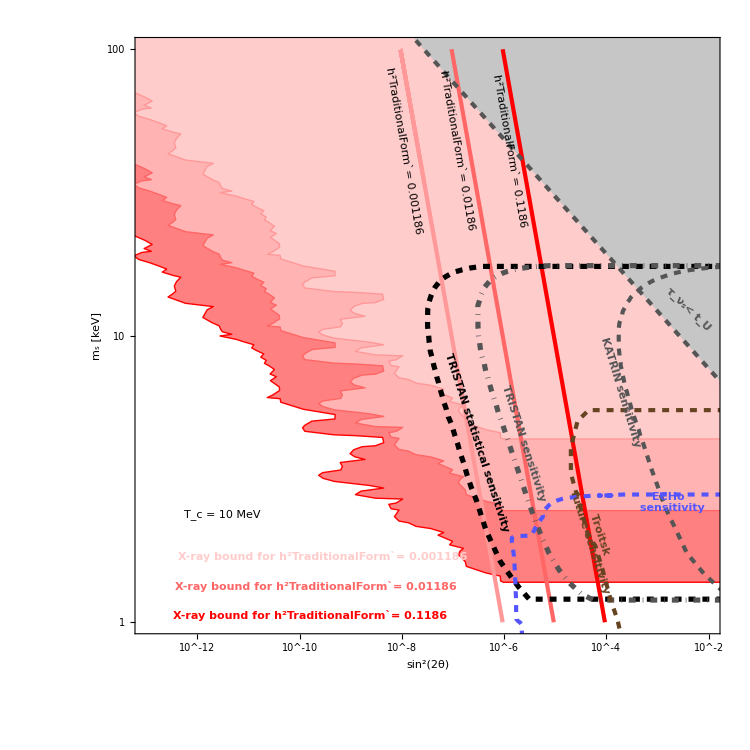

```mathematica
F2c10MeV=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,
Prolog->{
Blend[{RGBColor[255/255,0/255,0/255], White}, 1/2],Polygon[XtotLogl],
Blend[{RGBColor[255/255,102/255,102/255], White}, 1/2],Polygon[Xtotred10Log],
Blend[{RGBColor[255/255,153/255,153/255], White}, 1/2], Polygon[Xtotred100Log],
RGBColor[255/255,0/255,0/255],Line[XtotLogl],
RGBColor[255/255,102/255,102/255],Line[Xtotred10Log],
RGBColor[255/255,153/255,153/255], Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
RGBColor[255/255,0/255,0/255],Thick,Thickness[0.004],Line[LinelistCock10M12Log],
RGBColor[255/255,102/255,102/255],Thick,Thickness[0.004],Line[LinelistCock10M012Log],
RGBColor[255/255,153/255,153/255],Thick,Thickness[0.004],Line[LinelistCock10M0012Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
(* + HUNTER lines *)
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 10 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
RGBColor[255/255,0/255,0/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
RGBColor[255/255,102/255,102/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Blend[{RGBColor[255/255,153/255,153/255], White}, 1/2],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.64,0.81}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.55,0.81}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-80 Degree],Scaled[{0.46,0.81}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
(* + labels HUNTER lines *)
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2c10MeV.pdf",F2c10MeV];
```

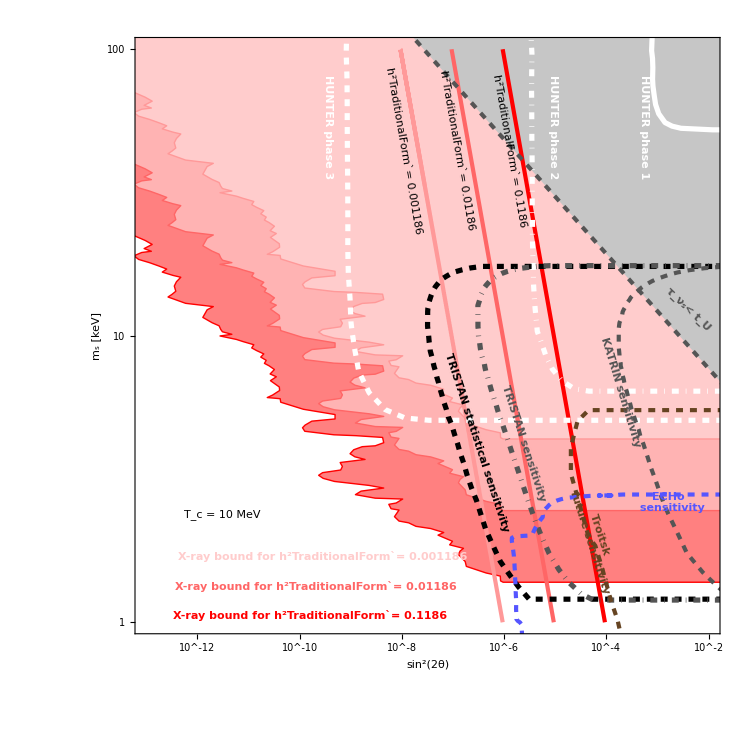

```mathematica
F2c10MeVHUNTER=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,
Prolog->{
Blend[{RGBColor[255/255,0/255,0/255], White}, 1/2],Polygon[XtotLogl],
Blend[{RGBColor[255/255,102/255,102/255], White}, 1/2],Polygon[Xtotred10Log],
Blend[{RGBColor[255/255,153/255,153/255], White}, 1/2], Polygon[Xtotred100Log],
RGBColor[255/255,0/255,0/255],Line[XtotLogl],
RGBColor[255/255,102/255,102/255],Line[Xtotred10Log],
RGBColor[255/255,153/255,153/255], Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
RGBColor[255/255,0/255,0/255],Thick,Thickness[0.004],Line[LinelistCock10M12Log],
RGBColor[255/255,102/255,102/255],Thick,Thickness[0.004],Line[LinelistCock10M012Log],
RGBColor[255/255,153/255,153/255],Thick,Thickness[0.004],Line[LinelistCock10M0012Log],
White, Thick,Thickness[0.005],Line[HUNT1Log],
White, DotDashed,Thickness[0.005],Line[HUNT2Log],
White, Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 10 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
RGBColor[255/255,0/255,0/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
RGBColor[255/255,102/255,102/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
Blend[{RGBColor[255/255,153/255,153/255], White}, 1/2],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.64,0.81}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.55,0.81}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-80 Degree],Scaled[{0.46,0.81}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.83,0.405}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.715,0.85}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.33,0.85}]],
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2c10MeVHUNTER.pdf",F2c10MeVHUNTER];
```

### T_c=5 MeV

#### data

For the cases with delayed production we use data simulated with our own Mathematica code.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with our own Mathematica code in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 5 MeV.

```mathematica
(*Omegatabe5M={};
For[eth=-14, eth≤-4, eth =eth+0.5, 
For[eMsn = -6, eMsn≤-3.9, eMsn=eMsn+0.1,
Omegasinge5M=Sterileabundance[10^eth,10^eMsn, 0.001, 0.005];
AppendTo[Omegatabe5M, {{10^eth,10^eMsn},Omegasinge5M}];]]*)
```

```mathematica
Omegatabe5M={{{1/100000000000000,1/1000000},1.5735399137397573*^-12},{{1/100000000000000,1.2589254117941661*^-6},1.980969387354822*^-12},{{1/100000000000000,1.584893192461111*^-6},2.4938927044879495*^-12},{{1/100000000000000,1.995262314968875*^-6},3.1396249021608126*^-12},{{1/100000000000000,2.5118864315095717*^-6},3.952553574573866*^-12},{{1/100000000000000,3.1622776601683665*^-6},4.975970137892507*^-12},{{1/100000000000000,3.981071705534953*^-6},6.26437525602083*^-12},{{1/100000000000000,5.0118723362726945*^-6},7.8863811996922*^-12},{{1/100000000000000,6.3095734448018915*^-6},9.928365700081716*^-12},{{1/100000000000000,7.943282347242757*^-6},1.249907187796927*^-11},{{1/100000000000000,9.999999999999918*^-6},1.5735399211454877*^-11},{{1/100000000000000,0.00001258925411794156},1.9809693932373973*^-11},{{1/100000000000000,0.00001584893192461098},2.4938927091606357*^-11},{{1/100000000000000,0.000019952623149688583},3.139624905872451*^-11},{{1/100000000000000,0.000025118864315095514},3.952553577522115*^-11},{{1/100000000000000,0.0000316227766016834},4.97597014023437*^-11},{{1/100000000000000,0.00003981071705534921},6.264375257881017*^-11},{{1/100000000000000,0.00005011872336272653},7.886381201169778*^-11},{{1/100000000000000,0.0000630957344480184},9.928365701255364*^-11},{{1/100000000000000,0.00007943282347242692},1.2499071878901495*^-10},{{1/100000000000000,0.00009999999999999836},1.5735399212195324*^-10},{{1/100000000000000,0.00012589254117941468},1.980969393296209*^-10},{{3.1622776601683796*^-14,1/1000000},4.975970116602459*^-12},{{3.1622776601683796*^-14,1.2589254117941661*^-6},6.264375239109528*^-12},{{3.1622776601683796*^-14,1.584893192461111*^-6},7.886381186259056*^-12},{{3.1622776601683796*^-14,1.995262314968875*^-6},9.928365689411364*^-12},{{3.1622776601683796*^-14,2.5118864315095717*^-6},1.2499071869493477*^-11},{{3.1622776601683796*^-14,3.1622776601683665*^-6},1.5735399204722276*^-11},{{3.1622776601683796*^-14,3.981071705534953*^-6},1.9809693927026028*^-11},{{3.1622776601683796*^-14,5.0118723362726945*^-6},2.493892708735828*^-11},{{3.1622776601683796*^-14,6.3095734448018915*^-6},3.1396249055350056*^-11},{{3.1622776601683796*^-14,7.943282347242757*^-6},3.9525535772540634*^-11},{{3.1622776601683796*^-14,9.999999999999918*^-6},4.975970140021435*^-11},{{3.1622776601683796*^-14,0.00001258925411794156},6.264375257711864*^-11},{{3.1622776601683796*^-14,0.00001584893192461098},7.886381201035391*^-11},{{3.1622776601683796*^-14,0.000019952623149688583},9.928365701148595*^-11},{{3.1622776601683796*^-14,0.000025118864315095514},1.2499071878816652*^-10},{{3.1622776601683796*^-14,0.0000316227766016834},1.573539921212789*^-10},{{3.1622776601683796*^-14,0.00003981071705534921},1.9809693932908457*^-10},{{3.1622776601683796*^-14,0.00005011872336272653},2.493892709203078*^-10},{{3.1622776601683796*^-14,0.0000630957344480184},3.139624905906147*^-10},{{3.1622776601683796*^-14,0.00007943282347242692},3.952553577548858*^-10},{{3.1622776601683796*^-14,0.00009999999999999836},4.975970140255584*^-10},{{3.1622776601683796*^-14,0.00012589254117941468},6.264375257897842*^-10},{{1.*^-13,1/1000000},1.5735399137396863*^-11},{{1.*^-13,1.2589254117941661*^-6},1.980969387354733*^-11},{{1.*^-13,1.584893192461111*^-6},2.4938927044878362*^-11},{{1.*^-13,1.995262314968875*^-6},3.1396249021606716*^-11},{{1.*^-13,2.5118864315095717*^-6},3.9525535745736893*^-11},{{1.*^-13,3.1622776601683665*^-6},4.975970137892283*^-11},{{1.*^-13,3.981071705534953*^-6},6.26437525602055*^-11},{{1.*^-13,5.0118723362726945*^-6},7.886381199691847*^-11},{{1.*^-13,6.3095734448018915*^-6},9.928365700081272*^-11},{{1.*^-13,7.943282347242757*^-6},1.2499071877968712*^-10},{{1.*^-13,9.999999999999918*^-6},1.5735399211454165*^-10},{{1.*^-13,0.00001258925411794156},1.9809693932373082*^-10},{{1.*^-13,0.00001584893192461098},2.493892709160524*^-10},{{1.*^-13,0.000019952623149688583},3.139624905872311*^-10},{{1.*^-13,0.000025118864315095514},3.952553577521937*^-10},{{1.*^-13,0.0000316227766016834},4.975970140234145*^-10},{{1.*^-13,0.00003981071705534921},6.264375257880737*^-10},{{1.*^-13,0.00005011872336272653},7.886381201169422*^-10},{{1.*^-13,0.0000630957344480184},9.92836570125492*^-10},{{1.*^-13,0.00007943282347242692},1.2499071878900934*^-9},{{1.*^-13,0.00009999999999999836},1.5735399212194617*^-9},{{1.*^-13,0.00012589254117941468},1.9809693932961204*^-9},{{3.162277660168379*^-13,1/1000000},4.975970116601751*^-11},{{3.162277660168379*^-13,1.2589254117941661*^-6},6.264375239108635*^-11},{{3.162277660168379*^-13,1.584893192461111*^-6},7.886381186257934*^-11},{{3.162277660168379*^-13,1.995262314968875*^-6},9.928365689409953*^-11},{{3.162277660168379*^-13,2.5118864315095717*^-6},1.2499071869491695*^-10},{{3.162277660168379*^-13,3.1622776601683665*^-6},1.5735399204720033*^-10},{{3.162277660168379*^-13,3.981071705534953*^-6},1.980969392702321*^-10},{{3.162277660168379*^-13,5.0118723362726945*^-6},2.493892708735473*^-10},{{3.162277660168379*^-13,6.3095734448018915*^-6},3.1396249055345584*^-10},{{3.162277660168379*^-13,7.943282347242757*^-6},3.9525535772535*^-10},{{3.162277660168379*^-13,9.999999999999918*^-6},4.975970140020726*^-10},{{3.162277660168379*^-13,0.00001258925411794156},6.26437525771097*^-10},{{3.162277660168379*^-13,0.00001584893192461098},7.886381201034268*^-10},{{3.162277660168379*^-13,0.000019952623149688583},9.928365701147182*^-10},{{3.162277660168379*^-13,0.000025118864315095514},1.2499071878814872*^-9},{{3.162277660168379*^-13,0.0000316227766016834},1.573539921212565*^-9},{{3.162277660168379*^-13,0.00003981071705534921},1.9809693932905638*^-9},{{3.162277660168379*^-13,0.00005011872336272653},2.493892709202723*^-9},{{3.162277660168379*^-13,0.0000630957344480184},3.1396249059057*^-9},{{3.162277660168379*^-13,0.00007943282347242692},3.952553577548296*^-9},{{3.162277660168379*^-13,0.00009999999999999836},4.975970140254876*^-9},{{3.162277660168379*^-13,0.00012589254117941468},6.264375257896949*^-9},{{1.*^-12,1/1000000},1.5735399137389785*^-10},{{1.*^-12,1.2589254117941661*^-6},1.9809693873538414*^-10},{{1.*^-12,1.584893192461111*^-6},2.4938927044867146*^-10},{{1.*^-12,1.995262314968875*^-6},3.1396249021592593*^-10},{{1.*^-12,2.5118864315095717*^-6},3.9525535745719106*^-10},{{1.*^-12,3.1622776601683665*^-6},4.975970137890045*^-10},{{1.*^-12,3.981071705534953*^-6},6.264375256017731*^-10},{{1.*^-12,5.0118723362726945*^-6},7.886381199688297*^-10},{{1.*^-12,6.3095734448018915*^-6},9.9283657000768*^-10},{{1.*^-12,7.943282347242757*^-6},1.2499071877963083*^-9},{{1.*^-12,9.999999999999918*^-6},1.5735399211447086*^-9},{{1.*^-12,0.00001258925411794156},1.980969393236417*^-9},{{1.*^-12,0.00001584893192461098},2.493892709159402*^-9},{{1.*^-12,0.000019952623149688583},3.1396249058708977*^-9},{{1.*^-12,0.000025118864315095514},3.952553577520157*^-9},{{1.*^-12,0.0000316227766016834},4.975970140231905*^-9},{{1.*^-12,0.00003981071705534921},6.264375257877919*^-9},{{1.*^-12,0.00005011872336272653},7.886381201165876*^-9},{{1.*^-12,0.0000630957344480184},9.928365701250451*^-9},{{1.*^-12,0.00007943282347242692},1.2499071878895309*^-8},{{1.*^-12,0.00009999999999999836},1.5735399212187537*^-8},{{1.*^-12,0.00012589254117941468},1.9809693932952285*^-8},{{3.1622776601683794*^-12,1/1000000},4.97597011659467*^-10},{{3.1622776601683794*^-12,1.2589254117941661*^-6},6.264375239099721*^-10},{{3.1622776601683794*^-12,1.584893192461111*^-6},7.886381186246711*^-10},{{3.1622776601683794*^-12,1.995262314968875*^-6},9.928365689395827*^-10},{{3.1622776601683794*^-12,2.5118864315095717*^-6},1.249907186947391*^-9},{{3.1622776601683794*^-12,3.1622776601683665*^-6},1.5735399204697647*^-9},{{3.1622776601683794*^-12,3.981071705534953*^-6},1.9809693926995023*^-9},{{3.1622776601683794*^-12,5.0118723362726945*^-6},2.4938927087319245*^-9},{{3.1622776601683794*^-12,6.3095734448018915*^-6},3.1396249055300923*^-9},{{3.1622776601683794*^-12,7.943282347242757*^-6},3.952553577247877*^-9},{{3.1622776601683794*^-12,9.999999999999918*^-6},4.975970140013646*^-9},{{3.1622776601683794*^-12,0.00001258925411794156},6.2643752577020586*^-9},{{3.1622776601683794*^-12,0.00001584893192461098},7.886381201023048*^-9},{{3.1622776601683794*^-12,0.000019952623149688583},9.928365701133054*^-9},{{3.1622776601683794*^-12,0.000025118864315095514},1.2499071878797091*^-8},{{3.1622776601683794*^-12,0.0000316227766016834},1.573539921210326*^-8},{{3.1622776601683794*^-12,0.00003981071705534921},1.980969393287745*^-8},{{3.1622776601683794*^-12,0.00005011872336272653},2.4938927091991754*^-8},{{3.1622776601683794*^-12,0.0000630957344480184},3.139624905901233*^-8},{{3.1622776601683794*^-12,0.00007943282347242692},3.952553577542671*^-8},{{3.1622776601683794*^-12,0.00009999999999999836},4.9759701402477966*^-8},{{3.1622776601683794*^-12,0.00012589254117941468},6.264375257888036*^-8},{{1.*^-11,1/1000000},1.5735399137318976*^-9},{{1.*^-11,1.2589254117941661*^-6},1.9809693873449277*^-9},{{1.*^-11,1.584893192461111*^-6},2.4938927044754917*^-9},{{1.*^-11,1.995262314968875*^-6},3.1396249021451307*^-9},{{1.*^-11,2.5118864315095717*^-6},3.952553574554124*^-9},{{1.*^-11,3.1622776601683665*^-6},4.975970137867652*^-9},{{1.*^-11,3.981071705534953*^-6},6.264375255989539*^-9},{{1.*^-11,5.0118723362726945*^-6},7.886381199652809*^-9},{{1.*^-11,6.3095734448018915*^-6},9.928365700032123*^-9},{{1.*^-11,7.943282347242757*^-6},1.2499071877906838*^-8},{{1.*^-11,9.999999999999918*^-6},1.5735399211376274*^-8},{{1.*^-11,0.00001258925411794156},1.9809693932275023*^-8},{{1.*^-11,0.00001584893192461098},2.4938927091481794*^-8},{{1.*^-11,0.000019952623149688583},3.1396249058567685*^-8},{{1.*^-11,0.000025118864315095514},3.9525535775023705*^-8},{{1.*^-11,0.0000316227766016834},4.975970140209513*^-8},{{1.*^-11,0.00003981071705534921},6.264375257849727*^-8},{{1.*^-11,0.00005011872336272653},7.886381201130384*^-8},{{1.*^-11,0.0000630957344480184},9.928365701205774*^-8},{{1.*^-11,0.00007943282347242692},1.249907187883906*^-7},{{1.*^-11,0.00009999999999999836},1.5735399212116726*^-7},{{1.*^-11,0.00012589254117941468},1.9809693932863136*^-7},{{3.1622776601683794*^-11,1/1000000},4.975970116523861*^-9},{{3.1622776601683794*^-11,1.2589254117941661*^-6},6.264375239010579*^-9},{{3.1622776601683794*^-11,1.584893192461111*^-6},7.886381186134487*^-9},{{3.1622776601683794*^-11,1.995262314968875*^-6},9.928365689254544*^-9},{{3.1622776601683794*^-11,2.5118864315095717*^-6},1.2499071869296048*^-8},{{3.1622776601683794*^-11,3.1622776601683665*^-6},1.573539920447373*^-8},{{3.1622776601683794*^-11,3.981071705534953*^-6},1.9809693926713123*^-8},{{3.1622776601683794*^-11,5.0118723362726945*^-6},2.4938927086964356*^-8},{{3.1622776601683794*^-11,6.3095734448018915*^-6},3.139624905485415*^-8},{{3.1622776601683794*^-11,7.943282347242757*^-6},3.9525535771916305*^-8},{{3.1622776601683794*^-11,9.999999999999918*^-6},4.975970139942837*^-8},{{3.1622776601683794*^-11,0.00001258925411794156},6.264375257612914*^-8},{{3.1622776601683794*^-11,0.00001584893192461098},7.886381200910823*^-8},{{3.1622776601683794*^-11,0.000019952623149688583},9.928365700991774*^-8},{{3.1622776601683794*^-11,0.000025118864315095514},1.2499071878619226*^-7},{{3.1622776601683794*^-11,0.0000316227766016834},1.5735399211879345*^-7},{{3.1622776601683794*^-11,0.00003981071705534921},1.9809693932595556*^-7},{{3.1622776601683794*^-11,0.00005011872336272653},2.493892709163686*^-7},{{3.1622776601683794*^-11,0.0000630957344480184},3.1396249058565543*^-7},{{3.1622776601683794*^-11,0.00007943282347242692},3.952553577486426*^-7},{{3.1622776601683794*^-11,0.00009999999999999836},4.975970140176986*^-7},{{3.1622776601683794*^-11,0.00012589254117941468},6.264375257798893*^-7},{{1.*^-10,1/1000000},1.5735399136610883*^-8},{{1.*^-10,1.2589254117941661*^-6},1.980969387255784*^-8},{{1.*^-10,1.584893192461111*^-6},2.493892704363266*^-8},{{1.*^-10,1.995262314968875*^-6},3.139624902003848*^-8},{{1.*^-10,2.5118864315095717*^-6},3.95255357437626*^-8},{{1.*^-10,3.1622776601683665*^-6},4.975970137643734*^-8},{{1.*^-10,3.981071705534953*^-6},6.264375255707645*^-8},{{1.*^-10,5.0118723362726945*^-6},7.886381199297923*^-8},{{1.*^-10,6.3095734448018915*^-6},9.928365699585347*^-8},{{1.*^-10,7.943282347242757*^-6},1.249907187734438*^-7},{{1.*^-10,9.999999999999918*^-6},1.5735399210668183*^-7},{{1.*^-10,0.00001258925411794156},1.9809693931383587*^-7},{{1.*^-10,0.00001584893192461098},2.493892709035954*^-7},{{1.*^-10,0.000019952623149688583},3.139624905715485*^-7},{{1.*^-10,0.000025118864315095514},3.9525535773245067*^-7},{{1.*^-10,0.0000316227766016834},4.975970139985595*^-7},{{1.*^-10,0.00003981071705534921},6.264375257567831*^-7},{{1.*^-10,0.00005011872336272653},7.886381200775495*^-7},{{1.*^-10,0.0000630957344480184},9.928365700759*^-7},{{1.*^-10,0.00007943282347242692},1.2499071878276605*^-6},{{1.*^-10,0.00009999999999999836},1.5735399211408634*^-6},{{1.*^-10,0.00012589254117941468},1.9809693931971702*^-6},{{3.1622776601683795*^-10,1/1000000},4.975970115815768*^-8},{{3.1622776601683795*^-10,1.2589254117941661*^-6},6.264375238119144*^-8},{{3.1622776601683795*^-10,1.584893192461111*^-6},7.886381185012235*^-8},{{3.1622776601683795*^-10,1.995262314968875*^-6},9.928365687841713*^-8},{{3.1622776601683795*^-10,2.5118864315095717*^-6},1.2499071867517398*^-7},{{3.1622776601683795*^-10,3.1622776601683665*^-6},1.5735399202234544*^-7},{{3.1622776601683795*^-10,3.981071705534953*^-6},1.9809693923894153*^-7},{{3.1622776601683795*^-10,5.0118723362726945*^-6},2.4938927083415485*^-7},{{3.1622776601683795*^-10,6.3095734448018915*^-6},3.139624905038638*^-7},{{3.1622776601683795*^-10,7.943282347242757*^-6},3.9525535766291726*^-7},{{3.1622776601683795*^-10,9.999999999999918*^-6},4.975970139234744*^-7},{{3.1622776601683795*^-10,0.00001258925411794156},6.264375256721478*^-7},{{3.1622776601683795*^-10,0.00001584893192461098},7.88638119978857*^-7},{{3.1622776601683795*^-10,0.000019952623149688583},9.928365699578943*^-7},{{3.1622776601683795*^-10,0.000025118864315095514},1.2499071876840579*^-6},{{3.1622776601683795*^-10,0.0000316227766016834},1.5735399209640156*^-6},{{3.1622776601683795*^-10,0.00003981071705534921},1.980969392977659*^-6},{{3.1622776601683795*^-10,0.00005011872336272653},2.4938927088087998*^-6},{{3.1622776601683795*^-10,0.0000630957344480184},3.139624905409779*^-6},{{3.1622776601683795*^-10,0.00007943282347242692},3.952553576923968*^-6},{{3.1622776601683795*^-10,0.00009999999999999836},4.975970139468893*^-6},{{3.1622776601683795*^-10,0.00012589254117941468},6.264375256907456*^-6},{{1.*^-9,1/1000000},1.573539912952995*^-7},{{1.*^-9,1.2589254117941661*^-6},1.9809693863643477*^-7},{{1.*^-9,1.584893192461111*^-6},2.4938927032410147*^-7},{{1.*^-9,1.995262314968875*^-6},3.139624900591017*^-7},{{1.*^-9,2.5118864315095717*^-6},3.952553572597611*^-7},{{1.*^-9,3.1622776601683665*^-6},4.975970135404549*^-7},{{1.*^-9,3.981071705534953*^-6},6.264375252888675*^-7},{{1.*^-9,5.0118723362726945*^-6},7.886381195749049*^-7},{{1.*^-9,6.3095734448018915*^-6},9.928365695117585*^-7},{{1.*^-9,7.943282347242757*^-6},1.2499071871719799*^-6},{{1.*^-9,9.999999999999918*^-6},1.5735399203587259*^-6},{{1.*^-9,0.00001258925411794156},1.980969392246923*^-6},{{1.*^-9,0.00001584893192461098},2.4938927079137028*^-6},{{1.*^-9,0.000019952623149688583},3.1396249043026556*^-6},{{1.*^-9,0.000025118864315095514},3.9525535755458584*^-6},{{1.*^-9,0.0000316227766016834},4.975970137746409*^-6},{{1.*^-9,0.00003981071705534921},6.2643752547488634*^-6},{{1.*^-9,0.00005011872336272653},7.886381197226625*^-6},{{1.*^-9,0.0000630957344480184},9.928365696291233*^-6},{{1.*^-9,0.00007943282347242692},0.00001249907187265202},{{1.*^-9,0.00009999999999999836},0.0000157353992043277},{{1.*^-9,0.00012589254117941468},0.00001980969392305733},{{3.1622776601683795*^-9,1/1000000},4.975970108734838*^-7},{{3.1622776601683795*^-9,1.2589254117941661*^-6},6.264375229204779*^-7},{{3.1622776601683795*^-9,1.584893192461111*^-6},7.886381173789717*^-7},{{3.1622776601683795*^-9,1.995262314968875*^-6},9.928365673713397*^-7},{{3.1622776601683795*^-9,2.5118864315095717*^-6},1.2499071849730908*^-6},{{3.1622776601683795*^-9,3.1622776601683665*^-6},1.5735399179842679*^-6},{{3.1622776601683795*^-9,3.981071705534953*^-6},1.980969389570447*^-6},{{3.1622776601683795*^-9,5.0118723362726945*^-6},2.4938927047926773*^-6},{{3.1622776601683795*^-9,6.3095734448018915*^-6},3.1396249005708736*^-6},{{3.1622776601683795*^-9,7.943282347242757*^-6},3.95255357100459*^-6},{{3.1622776601683795*^-9,9.999999999999918*^-6},4.975970132153814*^-6},{{3.1622776601683795*^-9,0.00001258925411794156},6.264375247807117*^-6},{{3.1622776601683795*^-9,0.00001584893192461098},7.886381188566052*^-6},{{3.1622776601683795*^-9,0.000019952623149688583},9.92836568545063*^-6},{{3.1622776601683795*^-9,0.000025118864315095514},0.000012499071859054086},{{3.1622776601683795*^-9,0.0000316227766016834},0.00001573539918724829},{{3.1622776601683795*^-9,0.00003981071705534921},0.000019809693901586896},{{3.1622776601683795*^-9,0.00005011872336272653},0.00002493892705259927},{{3.1622776601683795*^-9,0.0000630957344480184},0.00003139624900942012},{{3.1622776601683795*^-9,0.00007943282347242692},0.00003952553571299383},{{3.1622776601683795*^-9,0.00009999999999999836},0.000049759701323879575},{{3.1622776601683795*^-9,0.00012589254117941468},0.0000626437524799308},{{1.*^-8,1/1000000},1.573539905872066*^-6},{{1.*^-8,1.2589254117941661*^-6},1.9809693774499854*^-6},{{1.*^-8,1.584893192461111*^-6},2.4938926920184972*^-6},{{1.*^-8,1.995262314968875*^-6},3.1396248864627047*^-6},{{1.*^-8,2.5118864315095717*^-6},3.952553554811119*^-6},{{1.*^-8,3.1622776601683665*^-6},4.9759701130126816*^-6},{{1.*^-8,3.981071705534953*^-6},6.264375224698987*^-6},{{1.*^-8,5.0118723362726945*^-6},7.886381160260334*^-6},{{1.*^-8,6.3095734448018915*^-6},9.928365650439935*^-6},{{1.*^-8,7.943282347242757*^-6},0.000012499071815473976},{{1.*^-8,9.999999999999918*^-6},0.00001573539913277796},{{1.*^-8,0.00001258925411794156},0.0000198096938333256},{{1.*^-8,0.00001584893192461098},0.00002493892696691185},{{1.*^-8,0.000019952623149688583},0.000031396248901743416},{{1.*^-8,0.000025118864315095514},0.000039525535577593646},{{1.*^-8,0.0000316227766016834},0.0000497597011535454},{{1.*^-8,0.00003981071705534921},0.00006264375226559169},{{1.*^-8,0.00005011872336272653},0.00007886381161737902},{{1.*^-8,0.0000630957344480184},0.0000992836565161357},{{1.*^-8,0.00007943282347242692},0.00012499071816406162},{{1.*^-8,0.00009999999999999836},0.00015735399133518332},{{1.*^-8,0.00012589254117941468},0.00019809693833913576},{{3.162277660168379*^-8,1/1000000},4.975970037925545*^-6},{{3.162277660168379*^-8,1.2589254117941661*^-6},6.26437514006116*^-6},{{3.162277660168379*^-8,1.584893192461111*^-6},7.88638106156455*^-6},{{3.162277660168379*^-8,1.995262314968875*^-6},9.928365532430283*^-6},{{3.162277660168379*^-8,2.5118864315095717*^-6},0.000012499071671866003},{{3.162277660168379*^-8,3.1622776601683665*^-6},0.000015735398955924026},{{3.162277660168379*^-8,3.981071705534953*^-6},0.000019809693613807587},{{3.162277660168379*^-8,5.0118723362726945*^-6},0.000024938926693039624},{{3.162277660168379*^-8,6.3095734448018915*^-6},0.00003139624855893229},{{3.162277660168379*^-8,7.943282347242757*^-6},0.000039525535147587667},{{3.162277660168379*^-8,9.999999999999918*^-6},0.00004975970061344518},{{3.162277660168379*^-8,0.00001258925411794156},0.00006264375158663493},{{3.162277660168379*^-8,0.00001584893192461098},0.00007886381076340882},{{3.162277660168379*^-8,0.000019952623149688583},0.00009928365544167505},{{3.162277660168379*^-8,0.000025118864315095514},0.00012499071681189167},{{3.162277660168379*^-8,0.0000316227766016834},0.00015735398963329615},{{3.162277660168379*^-8,0.00003981071705534921},0.00019809693619689974},{{3.162277660168379*^-8,0.00005011872336272653},0.00024938926697712035},{{3.162277660168379*^-8,0.0000630957344480184},0.0003139624856264351},{{3.162277660168379*^-8,0.00007943282347242692},0.0003952553515053526},{{3.162277660168379*^-8,0.00009999999999999836},0.0004975970061578597},{{3.162277660168379*^-8,0.00012589254117941468},0.0006264375158849328},{{1.*^-7,1/1000000},0.000015735398350627774},{{1.*^-7,1.2589254117941661*^-6},0.00001980969288306373},{{1.*^-7,1.584893192461111*^-6},0.000024938925797933386},{{1.*^-7,1.995262314968875*^-6},0.000031396247451795995},{{1.*^-7,2.5118864315095717*^-6},0.00003952553376946227},{{1.*^-7,3.1622776601683665*^-6},0.00004975969889094051},{{1.*^-7,3.981071705534953*^-6},0.0000626437494280213},{{1.*^-7,5.0118723362726945*^-6},0.00007886380805373218},{{1.*^-7,6.3095734448018915*^-6},0.00009928365203663529},{{1.*^-7,7.943282347242757*^-6},0.00012499071253015796},{{1.*^-7,9.999999999999918*^-6},0.00015735398424685063},{{1.*^-7,0.00001258925411794156},0.00019809692941889458},{{1.*^-7,0.00001584893192461098},0.0002493892584466022},{{1.*^-7,0.000019952623149688583},0.000313962474889123},{{1.*^-7,0.000025118864315095514},0.00039525533798944634},{{1.*^-7,0.0000316227766016834},0.0004975969891435889},{{1.*^-7,0.00003981071705534921},0.0006264374944662272},{{1.*^-7,0.00005011872336272653},0.0007886380806850703},{{1.*^-7,0.0000630957344480184},0.0009928365204836997},{{1.*^-7,0.00007943282347242692},0.0012499071253947664},{{1.*^-7,0.00009999999999999836},0.0015735398425424795},{{1.*^-7,0.00012589254117941468},0.001980969294247614},{{3.162277660168379*^-7,1/1000000},0.00004975969329832833},{{3.162277660168379*^-7,1.2589254117941661*^-6},0.00006264374248625248},{{3.162277660168379*^-7,1.584893192461111*^-6},0.00007886379939313225},{{3.162277660168379*^-7,1.995262314968875*^-6},0.00009928364119599572},{{3.162277660168379*^-7,2.5118864315095717*^-6},0.0001249906989321751},{{3.162277660168379*^-7,3.1622776601683665*^-6},0.0001573539671673824},{{3.162277660168379*^-7,3.981071705534953*^-6},0.00019809690794839703},{{3.162277660168379*^-7,5.0118723362726945*^-6},0.0002493892314416931},{{3.162277660168379*^-7,6.3095734448018915*^-6},0.00031396244091169256},{{3.162277660168379*^-7,7.943282347242757*^-6},0.00039525529523007255},{{3.162277660168379*^-7,9.999999999999918*^-6},0.0004975969353251795},{{3.162277660168379*^-7,0.00001258925411794156},0.0006264374267227565},{{3.162277660168379*^-7,0.00001584893192461098},0.0007886379954089528},{{3.162277660168379*^-7,0.000019952623149688583},0.000992836413133674},{{3.162277660168379*^-7,0.000025118864315095514},0.0012499069902540574},{{3.162277660168379*^-7,0.0000316227766016834},0.0015735396724143624},{{3.162277660168379*^-7,0.00003981071705534921},0.0019809690800721676},{{3.162277660168379*^-7,0.00005011872336272653},0.002493892314884091},{{3.162277660168379*^-7,0.0000630957344480184},0.003139624409487886},{{3.162277660168379*^-7,0.00007943282347242692},0.003952552952595161},{{3.162277660168379*^-7,0.00009999999999999836},0.0049759693534852266},{{3.162277660168379*^-7,0.00012589254117941468},0.006264374267412111},{{1.*^-6,1/1000000},0.00015735391269705985},{{1.*^-6,1.2589254117941661*^-6},0.00019809683968711323},{{1.*^-6,1.584893192461111*^-6},0.00024938914575428574},{{1.*^-6,1.995262314968875*^-6},0.00031396233323499487},{{1.*^-6,2.5118864315095717*^-6},0.0003952551598299075},{{1.*^-6,3.1622776601683665*^-6},0.000497596764990995},{{1.*^-6,3.981071705534953*^-6},0.0006264372123836362},{{1.*^-6,5.0118723362726945*^-6},0.0007886377256505575},{{1.*^-6,6.3095734448018915*^-6},0.000992836073590386},{{1.*^-6,7.943282347242757*^-6},0.0012499065628439605},{{1.*^-6,9.999999999999918*^-6},0.0015735391343763142},{{1.*^-6,0.00001258925411794156},0.0019809684027536864},{{1.*^-6,0.00001584893192461098},0.0024938914622155118},{{1.*^-6,0.000019952623149688583},0.003139623336061525},{{1.*^-6,0.000025118864315095514},0.003952551601247206},{{1.*^-6,0.0000316227766016834},0.004975967652251581},{{1.*^-6,0.00003981071705534921},0.006264372125696095},{{1.*^-6,0.00005011872336272653},0.007886377257982247},{{1.*^-6,0.0000630957344480184},0.009928360737075708},{{1.*^-6,0.00007943282347242692},0.012499065629368235},{{1.*^-6,0.00009999999999999836},0.015735391344496415},{{1.*^-6,0.00012589254117941468},0.019809684028110668},{{3.162277660168379*^-6,1/1000000},0.0004975962248927885},{{3.162277660168379*^-6,1.2589254117941661*^-6},0.000626436533429404},{{3.162277660168379*^-6,1.584893192461111*^-6},0.0007886368716835113},{{3.162277660168379*^-6,1.995262314968875*^-6},0.0009928349991336668},{{3.162277660168379*^-6,2.5118864315095717*^-6},0.0012499052106788302},{{3.162277660168379*^-6,3.1622776601683665*^-6},0.0015735374324950507},{{3.162277660168379*^-6,3.981071705534953*^-6},0.001980966260524908},{{3.162277660168379*^-6,5.0118723362726945*^-6},0.002493888765557729},{{3.162277660168379*^-6,6.3095734448018915*^-6},0.003139619941367887},{{3.162277660168379*^-6,7.943282347242757*^-6},0.003952547327737914},{{3.162277660168379*^-6,9.999999999999918*^-6},0.004975962272346715},{{3.162277660168379*^-6,0.00001258925411794156},0.006264365352896176},{{3.162277660168379*^-6,0.00001584893192461098},0.007886368731611115},{{3.162277660168379*^-6,0.000019952623149688583},0.00992835000307329},{{3.162277660168379*^-6,0.000025118864315095514},0.012499052116110312},{{3.162277660168379*^-6,0.0000316227766016834},0.015735374332353825},{{3.162277660168379*^-6,0.00003981071705534921},0.01980966261112696},{{3.162277660168379*^-6,0.00005011872336272653},0.02493888766024075},{{3.162277660168379*^-6,0.0000630957344480184},0.03139619941737224},{{3.162277660168379*^-6,0.00007943282347242692},0.039525473280291136},{{3.162277660168379*^-6,0.00009999999999999836},0.04975962272573693},{{3.162277660168379*^-6,0.00012589254117941468},0.06264365353067841},{{0.00001,1/1000000},0.001573532046118909},{{0.00001,1.2589254117941661*^-6},0.001980959482606971},{{0.00001,1.584893192461111*^-6},0.0024938802351491527},{{0.00001,1.995262314968875*^-6},0.0031396092041933114},{{0.00001,2.5118864315095717*^-6},0.003952533812003642},{{0.00001,3.1622776601683665*^-6},0.004975945258290628},{{0.00001,3.981071705534953*^-6},0.006264343934457761},{{0.00001,5.0118723362726945*^-6},0.007886341768180472},{{0.00001,6.3095734448018915*^-6},0.0099283160587495},{{0.00001,7.943282347242757*^-6},0.012499009383234535},{{0.00001,9.999999999999918*^-6},0.01573532053524494},{{0.00001,0.00001258925411794156},0.019809594884893443},{{0.00001,0.00001584893192461098},0.024938802398215082},{{0.00001,0.000019952623149688583},0.03139609207904341},{{0.00001,0.000025118864315095514},0.03952533814950724},{{0.00001,0.0000316227766016834},0.04975945260630197},{{0.00001,0.00003981071705534921},0.06264343936313405},{{0.00001,0.00005011872336272653},0.07886341769649004},{{0.00001,0.0000630957344480184},0.09928316059905125},{{0.00001,0.00007943282347242692},0.12499009384130799},{{0.00001,0.00009999999999999836},0.15735320535913655},{{0.00001,0.00012589254117941468},0.19809594885338444},{{0.000031622776601683795,1/1000000},0.004975891442095124},{{0.000031622776601683795,1.2589254117941661*^-6},0.006264276193772632},{{0.000031622776601683795,1.584893192461111*^-6},0.007886256495567229},{{0.000031622776601683795,1.995262314968875*^-6},0.009928208713130573},{{0.000031622776601683795,2.5118864315095717*^-6},0.01249887424806432},{{0.000031622776601683795,3.1622776601683665*^-6},0.015735150414082976},{{0.000031622776601683795,3.981071705534953*^-6},0.01980938071816771},{{0.000031622776601683795,5.0118723362726945*^-6},0.024938532780766923},{{0.000031622776601683795,6.3095734448018915*^-6},0.03139575265276142},{{0.000031622776601683795,7.943282347242757*^-6},0.03952491083870592},{{0.000031622776601683795,9.999999999999918*^-6},0.04975891465512643},{{0.000031622776601683795,0.00001258925411794156},0.06264276212372948},{{0.000031622776601683795,0.00001584893192461098},0.07886256510340242},{{0.000031622776601683795,0.000019952623149688583},0.09928208724861734},{{0.000031622776601683795,0.000025118864315095514},0.12498874257375835},{{0.000031622776601683795,0.0000316227766016834},0.1573515042146567},{{0.000031622776601683795,0.00003981071705534921},0.19809380724004708},{{0.000031622776601683795,0.00005011872336272653},0.2493853278534899},{{0.000031622776601683795,0.0000630957344480184},0.31395752656292564},{{0.000031622776601683795,0.00007943282347242692},0.3952491084129433},{{0.000031622776601683795,0.00009999999999999836},0.49758914656750636},{{0.000031622776601683795,0.00012589254117941468},0.6264276212415818},{{0.0001,1/1000000},0.015734612446113575},{{0.0001,1.2589254117941661*^-6},0.019808703487896036},{{0.0001,1.584893192461111*^-6},0.024937680223211606},{{0.0001,1.995262314968875*^-6},0.031394679366124056},{{0.0001,2.5118864315095717*^-6},0.03952355966655984},{{0.0001,3.1622776601683665*^-6},0.0497572136426289},{{0.0001,3.981071705534953*^-6},0.06264062068576443},{{0.0001,5.0118723362726945*^-6},0.07885986920059385},{{0.0001,6.3095734448018915*^-6},0.09927869331431864},{{0.0001,7.943282347242757*^-6},0.12498446986860963},{{0.0001,9.999999999999918*^-6},0.15734612520156305},{{0.0001,0.00001258925411794156},0.19808703546701598},{{0.0001,0.00001584893192461098},0.24937680269905255},{{0.0001,0.000019952623149688583},0.3139467940317976},{{0.0001,0.000025118864315095514},0.395235596959257},{{0.0001,0.0000316227766016834},0.4975721366581836},{{0.0001,0.00003981071705534921},0.6264062070391191},{{0.0001,0.00005011872336272653},0.7885986921446516},{{0.0001,0.0000630957344480184},0.9927869332425244},{{0.0001,0.00007943282347242692},1.2498446987433636},{{0.0001,0.00009999999999999836},1.5734612520179463},{{0.0001,0.00012589254117941468},1.9808703545858628}};
```

```mathematica
OmegaSNe5M = Interpolation[Omegatabe5M, InterpolationOrder->1]; //Quiet
```

#### ContourPlot (first method)

```mathematica
(*contourplots requiring different percentages of DM to be constituted by sterile neutrinos, respectively 100%, 10% and 1%*)
ple5M12=Normal@ContourPlot[OmegaSNe5M[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-2},{Msn, 10^-6, 10^-4},PlotPoints->150];
ple5M012=Normal@ContourPlot[OmegaSNe5M[theta2times4, Msn]==0.01186, {theta2times4, 10^-14, 10^-2},{Msn, 10^-6, 10^-4},PlotPoints->200];
ple5M0012=Normal@ContourPlot[OmegaSNe5M[theta2times4, Msn]==0.001186, {theta2times4, 10^-14, 10^-2},{Msn, 10^-6, 10^-4},PlotPoints->200];
```

```mathematica
(*list of coordinates of points (sin^2(2θ), Subscript[m, s][GeV]) identifying the right amount of DM in the parameter space *)
Linelist5M12=Cases[ ple5M12,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist5M012=Cases[ ple5M012,Line[a_,b___]:>a,Infinity]⟦1⟧;
Linelist5M0012=Cases[ ple5M0012,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

```mathematica
(*rescaled valued of the mass from GeV to keV units, homogenous to the other dimensional quantities in the plots*)
Cock5M12r = Table[{Linelist5M12⟦i,1⟧,Linelist5M12⟦i,2⟧*10^6} ,{i,1,Length[Linelist5M12]}];
Cock5M012r = Table[{Linelist5M012⟦i,1⟧,Linelist5M012⟦i,2⟧*10^6} ,{i,1,Length[Linelist5M012]}];
Cock5M0012r = Table[{Linelist5M0012⟦i,1⟧,Linelist5M0012⟦i,2⟧*10^6} ,{i,1,Length[Linelist5M0012]}];
```

```mathematica
(*Log of the elements of the previous lists, better for the plot*)
LinelistCock5M12Log = Table[{Log10[Cock5M12r⟦i,1⟧], Log10[Cock5M12r⟦i,2⟧]}, {i ,1,Length[Cock5M12r]}];
LinelistCock5M012Log = Table[{Log10[Cock5M012r⟦i,1⟧], Log10[Cock5M012r⟦i,2⟧]}, {i ,1,Length[Cock5M012r]}];
LinelistCock5M0012Log = Table[{Log10[Cock5M0012r⟦i,1⟧], Log10[Cock5M0012r⟦i,2⟧]}, {i ,1,Length[Cock5M0012r]}];
```

#### plot Fig. 2(d)

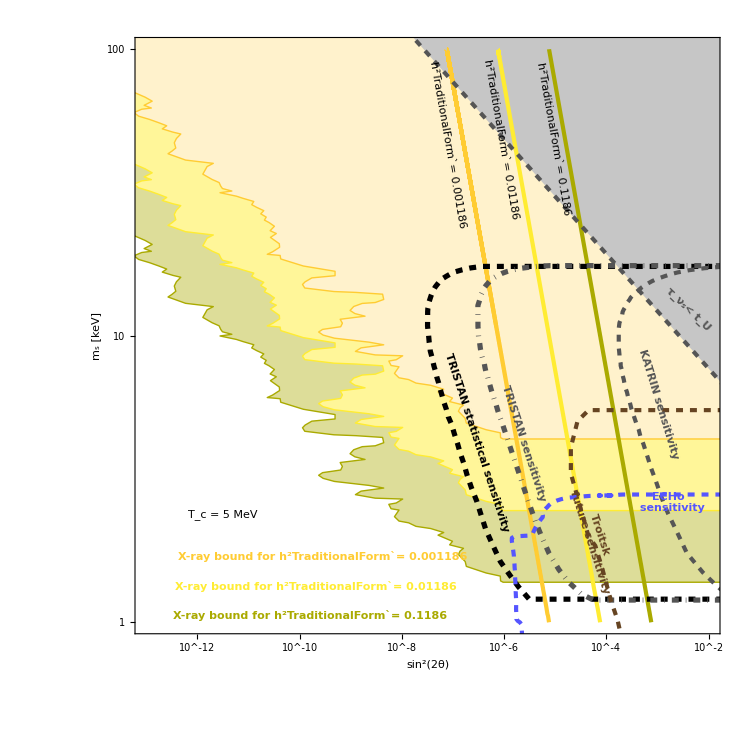

```mathematica
F2d5MeV=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
Blend[{Darker[Yellow], White}, 3/5],Polygon[XtotLogl],
Blend[{RGBColor[255/255, 236/255, 51/255],White}, 1/2],Polygon[Xtotred10Log],
Blend[{RGBColor[255/255, 204/255, 51/255],White}, 3/4], Polygon[Xtotred100Log],
Darker[Yellow],Line[XtotLogl],
RGBColor[255/255, 236/255, 51/255],Line[Xtotred10Log],
RGBColor[255/255, 204/255, 51/255], Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],

Darker[Yellow],Thick,Thickness[0.004],Line[LinelistCock5M12Log],
RGBColor[255/255, 236/255, 51/255],Thick,Thickness[0.004],Line[LinelistCock5M012Log],
RGBColor[255/255, 204/255, 51/255],Thick,Thickness[0.004],Line[LinelistCock5M0012Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
(* + HUNTER lines *)
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 5 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
Darker[Yellow], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
RGBColor[255/255, 236/255, 51/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
RGBColor[255/255, 204/255, 51/255],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.715,0.83}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.625,0.83}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-80 Degree],Scaled[{0.535,0.82}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.895,0.385}]],
(* + labels HUNTER lines *)
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2d5MeV.pdf",F2d5MeV];
```

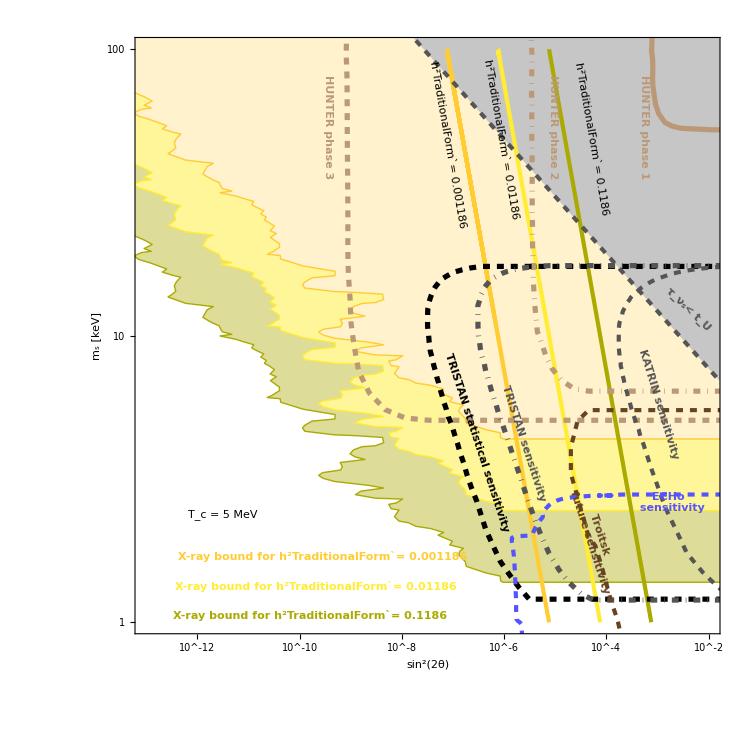

```mathematica
F2d5MeVHUNTER=Plot[{},{x,-16,-5},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->750,Axes->False,AspectRatio->1,

Prolog->{
Blend[{Darker[Yellow], White}, 3/5],Polygon[XtotLogl],
Blend[{RGBColor[255/255, 236/255, 51/255],White}, 1/2],Polygon[Xtotred10Log],
Blend[{RGBColor[255/255, 204/255, 51/255],White}, 3/4], Polygon[Xtotred100Log],
Darker[Yellow],Line[XtotLogl],
RGBColor[255/255, 236/255, 51/255],Line[Xtotred10Log],
RGBColor[255/255, 204/255, 51/255], Line[Xtotred100Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],

Darker[Yellow],Thick,Thickness[0.004],Line[LinelistCock5M12Log],
RGBColor[255/255, 236/255, 51/255],Thick,Thickness[0.004],Line[LinelistCock5M012Log],
RGBColor[255/255, 204/255, 51/255],Thick,Thickness[0.004],Line[LinelistCock5M0012Log],
Lighter[Brown], Thick,Thickness[0.005],Line[HUNT1Log],
Lighter[Brown], DotDashed,Thickness[0.005],Line[HUNT2Log],
Lighter[Brown], Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Darker[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]
},

Epilog->{
FontSize ->28,
Black, Text[Rotate[Style[Framed["T_c = 5 MeV"]],-0 Degree],Scaled[{0.15,0.2}]],
FontSize->24,
Darker[Yellow], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.1186", Bold],-0 Degree],Scaled[{0.3,0.03}]], 
RGBColor[255/255, 236/255, 51/255], Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.01186", Bold],-0 Degree],Scaled[{0.31,0.08}]], 
RGBColor[255/255, 204/255, 51/255],  Text[Rotate[Style["X-ray bound for h^2TraditionalForm`= 0.001186", Bold],-0 Degree],Scaled[{0.32,0.13}]],

FontSize->25,
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.1186"],-80 Degree],Scaled[{0.78,0.83}]],
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.01186"],-80 Degree],Scaled[{0.625,0.83}]], 
Black, Text[Rotate[Style["h^2TraditionalForm`= 0.001186"],-80 Degree],Scaled[{0.535,0.82}]],
FontSize->22,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
FontSize->20,
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-72 Degree],Scaled[{0.585,0.32}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-72 Degree],Scaled[{0.665,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-73 Degree],Scaled[{0.895,0.385}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.715,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.33,0.85}]],
FontSize->20,
Darker[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-72 Degree],Scaled[{0.785,0.16}]], 
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.915,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F2d5MeVHUNTER.pdf",F2d5MeVHUNTER];
```

## X-rays cancellation - Dodelson-Widrow mechanism

We study what happens to the parameter space of sterile neutrinos if the X-rays bound is relaxed thanks to a reduction of the decay amplitude of the sterile neutrino due to a disruptive interference between two channels (standard physics + new physics). We see that the X-rays constraint can be relaxed even completely leaving free the region of the parameter space where TRISTAN will be sensitive in the future. At the same time, if the production of sterile neutrinos is delayed enough (quantified in terms of the critical temperature T_c= 100 MeV, 50 MeV, 20 MeV, 10 MeV, 5 MeV taken as benchmark values), the lines representing the entire amount of DM constituted by sterile neutrinos are shifted towards the sensitivity region of TRISTAN.

### T_c=10 GeV

For the standard case we use data simulated with sterile-dm and we take the same simulated data got in the beginning of the previous section.

```mathematica
Linelist10GLog=pointst10G12;
```

### T_c=100 MeV

#### data

For the cases with delayed production we use data simulated with our own Mathematica code.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with our own Mathematica code in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 100 MeV.

```mathematica
Omegatabe100M={{{1/100000000000000,1/1000000},1.4726691807665957*^-8},{{1/100000000000000,1.2589254117941661*^-6},1.9765742076695326*^-8},{{1/100000000000000,1.584893192461111*^-6},2.609259791957526*^-8},{{1/100000000000000,1.995262314968875*^-6},3.3983882773444085*^-8},{{1/100000000000000,2.5118864315095717*^-6},4.380492953747725*^-8},{{1/100000000000000,3.1622776601683665*^-6},5.603532024890282*^-8},{{1/100000000000000,3.981071705534953*^-6},7.129571628382203*^-8},{{1/100000000000000,5.0118723362726945*^-6},9.037905011149556*^-8},{{1/100000000000000,6.3095734448018915*^-6},1.1428975204104011*^-7},{{1/100000000000000,7.943282347242757*^-6},1.4429444589175103*^-7},{{1/100000000000000,9.999999999999918*^-6},1.8198733533706072*^-7},{{1/100000000000000,0.00001258925411794156},2.293737673985535*^-7},{{1/100000000000000,0.00001584893192461098},2.8897623584331536*^-7},{{1/100000000000000,0.000019952623149688583},3.639682730446727*^-7},{{1/100000000000000,0.000025118864315095514},4.5834321571266994*^-7},{{1/100000000000000,0.0000316227766016834},5.77126740742483*^-7},{{1/100000000000000,0.00003981071705534921},7.266444369539085*^-7},{{1/100000000000000,0.00005011872336272653},9.148586331630572*^-7},{{1/100000000000000,0.0000630957344480184},1.1517924047003113*^-6},{{1/100000000000000,0.00007943282347242692},1.450063330378071*^-6},{{1/100000000000000,0.00009999999999999836},1.8255554203722075*^-6},{{1/100000000000000,0.00012589254117941468},2.2982649955739163*^-6},{{3.1622776601683796*^-14,1/1000000},4.656988851156629*^-8},{{3.1622776601683796*^-14,1.2589254117941661*^-6},6.250476460578317*^-8},{{3.1622776601683796*^-14,1.584893192461111*^-6},8.251203949682797*^-8},{{3.1622776601683796*^-14,1.995262314968875*^-6},1.0746647330024216*^-7},{{3.1622776601683796*^-14,2.5118864315095717*^-6},1.3852335008161284*^-7},{{3.1622776601683796*^-14,3.1622776601683665*^-6},1.7719924140348433*^-7},{{3.1622776601683796*^-14,3.981071705534953*^-6},2.2545685087003102*^-7},{{3.1622776601683796*^-14,5.0118723362726945*^-6},2.858036511148178*^-7},{{3.1622776601683796*^-14,6.3095734448018915*^-6},3.614159296655608*^-7},{{3.1622776601683796*^-14,7.943282347242757*^-6},4.5629910272985436*^-7},{{3.1622776601683796*^-14,9.999999999999918*^-6},5.754944849699524*^-7},{{3.1622776601683796*^-14,0.00001258925411794156},7.25343540473096*^-7},{{3.1622776601683796*^-14,0.00001584893192461098},9.138230949268552*^-7},{{3.1622776601683796*^-14,0.000019952623149688583},1.1509687388592213*^-6},{{3.1622776601683796*^-14,0.000025118864315095514},1.449408511737897*^-6},{{3.1622776601683796*^-14,0.0000316227766016834},1.8250349993357229*^-6},{{3.1622776601683796*^-14,0.00003981071705534921},2.2978514698649507*^-6},{{3.1622776601683796*^-14,0.00005011872336272653},2.8930370178636843*^-6},{{3.1622776601683796*^-14,0.0000630957344480184},3.6422873905353727*^-6},{{3.1622776601683796*^-14,0.00007943282347242692},4.5855028754838844*^-6},{{3.1622776601683796*^-14,0.00009999999999999836},5.772913123242264*^-6},{{3.1622776601683796*^-14,0.00012589254117941468},7.267752052650295*^-6},{{1.*^-13,1/1000000},1.4726691807665387*^-7},{{1.*^-13,1.2589254117941661*^-6},1.9765742076694534*^-7},{{1.*^-13,1.584893192461111*^-6},2.609259791957418*^-7},{{1.*^-13,1.995262314968875*^-6},3.398388277344264*^-7},{{1.*^-13,2.5118864315095717*^-6},4.380492953747535*^-7},{{1.*^-13,3.1622776601683665*^-6},5.603532024890037*^-7},{{1.*^-13,3.981071705534953*^-6},7.12957162838189*^-7},{{1.*^-13,5.0118723362726945*^-6},9.037905011149155*^-7},{{1.*^-13,6.3095734448018915*^-6},1.1428975204103502*^-6},{{1.*^-13,7.943282347242757*^-6},1.442944458917446*^-6},{{1.*^-13,9.999999999999918*^-6},1.8198733533705256*^-6},{{1.*^-13,0.00001258925411794156},2.2937376739854317*^-6},{{1.*^-13,0.00001584893192461098},2.8897623584330235*^-6},{{1.*^-13,0.000019952623149688583},3.6396827304465633*^-6},{{1.*^-13,0.000025118864315095514},4.583432157126492*^-6},{{1.*^-13,0.0000316227766016834},5.771267407424571*^-6},{{1.*^-13,0.00003981071705534921},7.2664443695387595*^-6},{{1.*^-13,0.00005011872336272653},9.148586331630159*^-6},{{1.*^-13,0.0000630957344480184},0.000011517924047002596},{{1.*^-13,0.00007943282347242692},0.000014500633303780055},{{1.*^-13,0.00009999999999999836},0.000018255554203721256},{{1.*^-13,0.00012589254117941468},0.00002298264995573813},{{3.162277660168379*^-13,1/1000000},4.6569888511560626*^-7},{{3.162277660168379*^-13,1.2589254117941661*^-6},6.250476460577526*^-7},{{3.162277660168379*^-13,1.584893192461111*^-6},8.251203949681716*^-7},{{3.162277660168379*^-13,1.995262314968875*^-6},1.0746647330022776*^-6},{{3.162277660168379*^-13,2.5118864315095717*^-6},1.3852335008159395*^-6},{{3.162277660168379*^-13,3.1622776601683665*^-6},1.771992414034598*^-6},{{3.162277660168379*^-13,3.981071705534953*^-6},2.254568508699995*^-6},{{3.162277660168379*^-13,5.0118723362726945*^-6},2.8580365111477763*^-6},{{3.162277660168379*^-13,6.3095734448018915*^-6},3.6141592966550968*^-6},{{3.162277660168379*^-13,7.943282347242757*^-6},4.562991027297897*^-6},{{3.162277660168379*^-13,9.999999999999918*^-6},5.7549448496987074*^-6},{{3.162277660168379*^-13,0.00001258925411794156},7.253435404729929*^-6},{{3.162277660168379*^-13,0.00001584893192461098},9.13823094926725*^-6},{{3.162277660168379*^-13,0.000019952623149688583},0.000011509687388590575},{{3.162277660168379*^-13,0.000025118864315095514},0.000014494085117376908},{{3.162277660168379*^-13,0.0000316227766016834},0.000018250349993354624},{{3.162277660168379*^-13,0.00003981071705534921},0.000022978514698646235},{{3.162277660168379*^-13,0.00005011872336272653},0.000028930370178632714},{{3.162277660168379*^-13,0.0000630957344480184},0.00003642287390534854},{{3.162277660168379*^-13,0.00007943282347242692},0.00004585502875483231},{{3.162277660168379*^-13,0.00009999999999999836},0.00005772913123241442},{{3.162277660168379*^-13,0.00012589254117941468},0.0000726775205264926},{{1.*^-12,1/1000000},1.4726691807659714*^-6},{{1.*^-12,1.2589254117941661*^-6},1.976574207668662*^-6},{{1.*^-12,1.584893192461111*^-6},2.609259791956341*^-6},{{1.*^-12,1.995262314968875*^-6},3.398388277342825*^-6},{{1.*^-12,2.5118864315095717*^-6},4.380492953745644*^-6},{{1.*^-12,3.1622776601683665*^-6},5.603532024887583*^-6},{{1.*^-12,3.981071705534953*^-6},7.129571628378739*^-6},{{1.*^-12,5.0118723362726945*^-6},9.037905011145135*^-6},{{1.*^-12,6.3095734448018915*^-6},0.0000114289752040984},{{1.*^-12,7.943282347242757*^-6},0.000014429444589167993},{{1.*^-12,9.999999999999918*^-6},0.00001819873353369709},{{1.*^-12,0.00001258925411794156},0.00002293737673984402},{{1.*^-12,0.00001584893192461098},0.00002889762358431725},{{1.*^-12,0.000019952623149688583},0.00003639682730444927},{{1.*^-12,0.000025118864315095514},0.00004583432157124431},{{1.*^-12,0.0000316227766016834},0.00005771267407421975},{{1.*^-12,0.00003981071705534921},0.00007266444369535489},{{1.*^-12,0.00005011872336272653},0.00009148586331626048},{{1.*^-12,0.0000630957344480184},0.00011517924046997414},{{1.*^-12,0.00007943282347242692},0.00014500633303773532},{{1.*^-12,0.00009999999999999836},0.0001825555420371304},{{1.*^-12,0.00012589254117941468},0.00022982649955727785},{{3.1622776601683794*^-12,1/1000000},4.656988851150389*^-6},{{3.1622776601683794*^-12,1.2589254117941661*^-6},6.250476460569616*^-6},{{3.1622776601683794*^-12,1.584893192461111*^-6},8.25120394967094*^-6},{{3.1622776601683794*^-12,1.995262314968875*^-6},0.000010746647330008382},{{3.1622776601683794*^-12,2.5118864315095717*^-6},0.000013852335008140485},{{3.1622776601683794*^-12,3.1622776601683665*^-6},0.000017719924140321462},{{3.1622776601683794*^-12,3.981071705534953*^-6},0.000022545685086968453},{{3.1622776601683794*^-12,5.0118723362726945*^-6},0.000028580365111437568},{{3.1622776601683794*^-12,6.3095734448018915*^-6},0.00003614159296649994},{{3.1622776601683794*^-12,7.943282347242757*^-6},0.00004562991027291437},{{3.1622776601683794*^-12,9.999999999999918*^-6},0.000057549448496905434},{{3.1622776601683794*^-12,0.00001258925411794156},0.0000725343540471963},{{3.1622776601683794*^-12,0.00001584893192461098},0.00009138230949254266},{{3.1622776601683794*^-12,0.000019952623149688583},0.00011509687388574206},{{3.1622776601683794*^-12,0.000025118864315095514},0.00014494085117356293},{{3.1622776601683794*^-12,0.0000316227766016834},0.00018250349993328667},{{3.1622776601683794*^-12,0.00003981071705534921},0.00022978514698613549},{{3.1622776601683794*^-12,0.00005011872336272653},0.00028930370178591554},{{3.1622776601683794*^-12,0.0000630957344480184},0.0003642287390529672},{{3.1622776601683794*^-12,0.00007943282347242692},0.0004585502875476707},{{3.1622776601683794*^-12,0.00009999999999999836},0.0005772913123233228},{{3.1622776601683794*^-12,0.00012589254117941468},0.0007267752052638922},{{1.*^-11,1/1000000},0.000014726691807602958},{{1.*^-11,1.2589254117941661*^-6},0.00001976574207660751},{{1.*^-11,1.584893192461111*^-6},0.000026092597919455613},{{1.*^-11,1.995262314968875*^-6},0.0000339838827732843},{{1.*^-11,2.5118864315095717*^-6},0.000043804929537267344},{{1.*^-11,3.1622776601683665*^-6},0.000056035320248630594},{{1.*^-11,3.981071705534953*^-6},0.00007129571628347241},{{1.*^-11,5.0118723362726945*^-6},0.00009037905011104946},{{1.*^-11,6.3095734448018915*^-6},0.00011428975204047361},{{1.*^-11,7.943282347242757*^-6},0.00014429444589103384},{{1.*^-11,9.999999999999918*^-6},0.0001819873353361545},{{1.*^-11,0.00001258925411794156},0.00022937376739741002},{{1.*^-11,0.00001584893192461098},0.0002889762358418737},{{1.*^-11,0.000019952623149688583},0.0003639682730428561},{{1.*^-11,0.000025118864315095514},0.0004583432157103816},{{1.*^-11,0.0000316227766016834},0.0005771267407396013},{{1.*^-11,0.00003981071705534921},0.0007266444369502796},{{1.*^-11,0.00005011872336272653},0.0009148586331584883},{{1.*^-11,0.0000630957344480184},0.0011517924046945587},{{1.*^-11,0.00007943282347242692},0.001450063330370828},{{1.*^-11,0.00009999999999999836},0.0018255554203630887},{{1.*^-11,0.00012589254117941468},0.0022982649955624367},{{3.1622776601683794*^-11,1/1000000},0.00004656988851093637},{{3.1622776601683794*^-11,1.2589254117941661*^-6},0.00006250476460490508},{{3.1622776601683794*^-11,1.584893192461111*^-6},0.00008251203949563154},{{3.1622776601683794*^-11,1.995262314968875*^-6},0.0001074664732986443},{{3.1622776601683794*^-11,2.5118864315095717*^-6},0.00013852335007951387},{{3.1622776601683794*^-11,3.1622776601683665*^-6},0.00017719924140076237},{{3.1622776601683794*^-11,3.981071705534953*^-6},0.00022545685086653472},{{3.1622776601683794*^-11,5.0118723362726945*^-6},0.000285803651110357},{{3.1622776601683794*^-11,6.3095734448018915*^-6},0.0003614159296598957},{{3.1622776601683794*^-11,7.943282347242757*^-6},0.0004562991027226822},{{3.1622776601683794*^-11,9.999999999999918*^-6},0.0005754944849608905},{{3.1622776601683794*^-11,0.00001258925411794156},0.0007253435404616617},{{3.1622776601683794*^-11,0.00001584893192461098},0.0009138230949124392},{{3.1622776601683794*^-11,0.000019952623149688583},0.0011509687388410554},{{3.1622776601683794*^-11,0.000025118864315095514},0.0014494085117150142},{{3.1622776601683794*^-11,0.0000316227766016834},0.0018250349993069047},{{3.1622776601683794*^-11,0.00003981071705534921},0.0022978514698286617},{{3.1622776601683794*^-11,0.00005011872336272653},0.002893037017817993},{{3.1622776601683794*^-11,0.0000630957344480184},0.0036422873904778446},{{3.1622776601683794*^-11,0.00007943282347242692},0.004585502875411457},{{3.1622776601683794*^-11,0.00009999999999999836},0.00577291312315108},{{3.1622776601683794*^-11,0.00012589254117941468},0.007267752052535501},{{1.*^-10,1/1000000},0.00014726691807035456},{{1.*^-10,1.2589254117941661*^-6},0.00019765742075816443},{{1.*^-10,1.584893192461111*^-6},0.00026092597918377753},{{1.*^-10,1.995262314968875*^-6},0.00033983882771844795},{{1.*^-10,2.5118864315095717*^-6},0.0004380492953537639},{{1.*^-10,3.1622776601683665*^-6},0.0005603532024617841},{{1.*^-10,3.981071705534953*^-6},0.0007129571628032252},{{1.*^-10,5.0118723362726945*^-6},0.0009037905010703071},{{1.*^-10,6.3095734448018915*^-6},0.0011428975203536993},{{1.*^-10,7.943282347242757*^-6},0.0014429444588457238},{{1.*^-10,9.999999999999918*^-6},0.0018198733532799067},{{1.*^-10,0.00001258925411794156},0.0022937376738710862},{{1.*^-10,0.00001584893192461098},0.0028897623582888605},{{1.*^-10,0.000019952623149688583},0.0036396827302649054},{{1.*^-10,0.000025118864315095514},0.004583432156897665},{{1.*^-10,0.0000316227766016834},0.005771267407136388},{{1.*^-10,0.00003981071705534921},0.007266444369175872},{{1.*^-10,0.00005011872336272653},0.009148586331173249},{{1.*^-10,0.0000630957344480184},0.011517924046427323},{{1.*^-10,0.00007943282347242692},0.01450063330305579},{{1.*^-10,0.00009999999999999836},0.018255554202809415},{{1.*^-10,0.00012589254117941468},0.02298264995459017},{{3.1622776601683795*^-10,1/1000000},0.000465698885052613},{{3.1622776601683795*^-10,1.2589254117941661*^-6},0.0006250476459699434},{{3.1622776601683795*^-10,1.584893192461111*^-6},0.000825120394848529},{{3.1622776601683795*^-10,1.995262314968875*^-6},0.0010746647328424923},{{3.1622776601683795*^-10,2.5118864315095717*^-6},0.0013852335006060423},{{3.1622776601683795*^-10,3.1622776601683665*^-6},0.001771992413762402},{{3.1622776601683795*^-10,3.981071705534953*^-6},0.002254568508350359},{{3.1622776601683795*^-10,5.0118723362726945*^-6},0.0028580365107016923},{{3.1622776601683795*^-10,6.3095734448018915*^-6},0.0036141592960885903},{{3.1622776601683795*^-10,7.943282347242757*^-6},0.0045629910265806775},{{3.1622776601683795*^-10,9.999999999999918*^-6},0.005754944848792518},{{3.1622776601683795*^-10,0.00001258925411794156},0.007253435403586476},{{3.1622776601683795*^-10,0.00001584893192461098},0.009138230947825628},{{3.1622776601683795*^-10,0.000019952623149688583},0.011509687386773996},{{3.1622776601683795*^-10,0.000025118864315095514},0.014494085115088633},{{3.1622776601683795*^-10,0.0000316227766016834},0.018250349990472793},{{3.1622776601683795*^-10,0.00003981071705534921},0.022978514695017372},{{3.1622776601683795*^-10,0.00005011872336272653},0.028930370174063583},{{3.1622776601683795*^-10,0.0000630957344480184},0.0364228738995958},{{3.1622776601683795*^-10,0.00007943282347242692},0.045855028747589614},{{3.1622776601683795*^-10,0.00009999999999999836},0.057729131223296044},{{3.1622776601683795*^-10,0.00012589254117941468},0.07267752051501303},{{1.*^-9,1/1000000},0.001472669180136038},{{1.*^-9,1.2589254117941661*^-6},0.0019765742067905713},{{1.*^-9,1.584893192461111*^-6},0.0026092597907599133},{{1.*^-9,1.995262314968875*^-6},0.0033983882757449733},{{1.*^-9,2.5118864315095717*^-6},0.0043804929516466735},{{1.*^-9,3.1622776601683665*^-6},0.005603532022165621},{{1.*^-9,3.981071705534953*^-6},0.0071295716248823745},{{1.*^-9,5.0118723362726945*^-6},0.009037905006684294},{{1.*^-9,6.3095734448018915*^-6},0.011428975198433326},{{1.*^-9,7.943282347242757*^-6},0.014429444581995804},{{1.*^-9,9.999999999999918*^-6},0.018198733524635184},{{1.*^-9,0.00001258925411794156},0.022937376728409488},{{1.*^-9,0.00001584893192461098},0.02889762356990099},{{1.*^-9,0.000019952623149688583},0.0363968272862835},{{1.*^-9,0.000025118864315095514},0.04583432154836154},{{1.*^-9,0.0000316227766016834},0.0577126740454014},{{1.*^-9,0.00003981071705534921},0.07266444365906627},{{1.*^-9,0.00005011872336272653},0.09148586327056903},{{1.*^-9,0.0000630957344480184},0.11517924041244668},{{1.*^-9,0.00007943282347242692},0.1450063329653083},{{1.*^-9,0.00009999999999999836},0.18255554194594678},{{1.*^-9,0.00012589254117941468},0.22982649944248185},{{3.1622776601683795*^-9,1/1000000},0.00465698884485105},{{3.1622776601683795*^-9,1.2589254117941661*^-6},0.006250476451788696},{{3.1622776601683795*^-9,1.584893192461111*^-6},0.008251203937706657},{{3.1622776601683795*^-9,1.995262314968875*^-6},0.01074664731402986},{{3.1622776601683795*^-9,2.5118864315095717*^-6},0.013852334987150765},{{3.1622776601683795*^-9,3.1622776601683665*^-6},0.017719924113101828},{{3.1622776601683795*^-9,3.981071705534953*^-6},0.022545685052004775},{{3.1622776601683795*^-9,5.0118723362726945*^-6},0.028580365066829174},{{3.1622776601683795*^-9,6.3095734448018915*^-6},0.0361415929098492},{{3.1622776601683795*^-9,7.943282347242757*^-6},0.04562991020119239},{{3.1622776601683795*^-9,9.999999999999918*^-6},0.05754944840628634},{{3.1622776601683795*^-9,0.00001258925411794156},0.07253435393285093},{{3.1622776601683795*^-9,0.00001584893192461098},0.09138230934838001},{{3.1622776601683795*^-9,0.000019952623149688583},0.11509687370408411},{{3.1622776601683795*^-9,0.000025118864315095514},0.14494085094473524},{{3.1622776601683795*^-9,0.0000316227766016834},0.18250349964510315},{{3.1622776601683795*^-9,0.00003981071705534921},0.229785146623249},{{3.1622776601683795*^-9,0.00005011872336272653},0.2893037013290013},{{3.1622776601683795*^-9,0.0000630957344480184},0.36422873847769255},{{3.1622776601683795*^-9,0.00007943282347242692},0.4585502868234004},{{3.1622776601683795*^-9,0.00009999999999999836},0.5772913114114867},{{3.1622776601683795*^-9,0.00012589254117941468},0.7267752041159314},{{1.*^-8,1/1000000},0.014726691744609577},{{1.*^-8,1.2589254117941661*^-6},0.019765741988798317},{{1.*^-8,1.584893192461111*^-6},0.026092597799812774},{{1.*^-8,1.995262314968875*^-6},0.03398388261349907},{{1.*^-8,2.5118864315095717*^-6},0.04380492932737018},{{1.*^-8,3.1622776601683665*^-6},0.05603531997643431},{{1.*^-8,3.981071705534953*^-6},0.07129571593383562},{{1.*^-8,5.0118723362726945*^-6},0.09037904966496545},{{1.*^-8,6.3095734448018915*^-6},0.11428975147396633},{{1.*^-8,7.943282347242757*^-6},0.14429444517381407},{{1.*^-8,9.999999999999918*^-6},0.18198733442996362},{{1.*^-8,0.00001258925411794156},0.22937376625395656},{{1.*^-8,0.00001584893192461098},0.28897623440024744},{{1.*^-8,0.000019952623149688583},0.3639682712262765},{{1.*^-8,0.000025118864315095514},0.45834321342210477},{{1.*^-8,0.0000316227766016834},0.5771267378577657},{{1.*^-8,0.00003981071705534921},0.726644433321416},{{1.*^-8,0.00005011872336272653},0.914858628589346},{{1.*^-8,0.0000630957344480184},1.1517923989418135},{{1.*^-8,0.00007943282347242692},1.4500633231281257},{{1.*^-8,0.00009999999999999836},1.8255554112447283},{{1.*^-8,0.00012589254117941468},2.298264984082832},{{3.162277660168379*^-8,1/1000000},0.0465698878810025},{{3.162277660168379*^-8,1.2589254117941661*^-6},0.0625047637268131},{{3.162277660168379*^-8,1.584893192461111*^-6},0.08251203829920312},{{3.162277660168379*^-8,1.995262314968875*^-6},0.10746647170079203},{{3.162277660168379*^-8,2.5118864315095717*^-6},0.1385233479805421},{{3.162277660168379*^-8,3.1622776601683665*^-6},0.17719923867879933},{{3.162277660168379*^-8,3.981071705534953*^-6},0.2254568473701666},{{3.162277660168379*^-8,5.0118723362726945*^-6},0.28580364664951685},{{3.162277660168379*^-8,6.3095734448018915*^-6},0.3614159239948228},{{3.162277660168379*^-8,7.943282347242757*^-6},0.45629909555048476},{{3.162277660168379*^-8,9.999999999999918*^-6},0.5754944758989814},{{3.162277660168379*^-8,0.00001258925411794156},0.725343529027127},{{3.162277660168379*^-8,0.00001584893192461098},0.9138230804961766},{{3.162277660168379*^-8,0.000019952623149688583},1.150968720675259},{{3.162277660168379*^-8,0.000025118864315095514},1.4494084888322447},{{3.162277660168379*^-8,0.0000316227766016834},1.8250349704885487},{{3.162277660168379*^-8,0.00003981071705534921},2.2978514335400257},{{3.162277660168379*^-8,0.00005011872336272653},2.893036972126568},{{3.162277660168379*^-8,0.0000630957344480184},3.642287332950395},{{3.162277660168379*^-8,0.00007943282347242692},4.585502802984432},{{3.162277660168379*^-8,0.00009999999999999836},5.7729130319674775},{{3.162277660168379*^-8,0.00012589254117941468},7.267751937739453},{{1.*^-7,1/1000000},0.14726691177101614},{{1.*^-7,1.2589254117941661*^-6},0.19765741197724526},{{1.*^-7,1.584893192461111*^-6},0.2609259672194944},{{1.*^-7,1.995262314968875*^-6},0.339838811739926},{{1.*^-7,2.5118864315095717*^-6},0.4380492743640476},{{1.*^-7,3.1622776601683665*^-6},0.5603531752421551},{{1.*^-7,3.981071705534953*^-6},0.7129571278395481},{{1.*^-7,5.0118723362726945*^-6},0.9037904564619086},{{1.*^-7,6.3095734448018915*^-6},1.142897463702975},{{1.*^-7,7.943282347242757*^-6},1.4429443871237533},{{1.*^-7,9.999999999999918*^-6},1.8198732626608214},{{1.*^-7,0.00001258925411794156},2.293737559525749},{{1.*^-7,0.00001584893192461098},2.889762214126247},{{1.*^-7,0.000019952623149688583},3.639682548606957},{{1.*^-7,0.000025118864315095514},4.583431928069989},{{1.*^-7,0.0000316227766016834},5.771267118952851},{{1.*^-7,0.00003981071705534921},7.2664440062895395},{{1.*^-7,0.00005011872336272653},9.148585874259037},{{1.*^-7,0.0000630957344480184},11.517923471152859},{{1.*^-7,0.00007943282347242692},14.500632578785588},{{1.*^-7,0.00009999999999999836},18.255553290973438},{{1.*^-7,0.00012589254117941468},22.982648806629793},{{3.162277660168379*^-7,1/1000000},0.465698822059241},{{3.162277660168379*^-7,1.2589254117941661*^-6},0.6250475581607688},{{3.162277660168379*^-7,1.584893192461111*^-6},0.8251202752057215},{{3.162277660168379*^-7,1.995262314968875*^-6},1.0746645730573057},{{3.162277660168379*^-7,2.5118864315095717*^-6},1.3852332907089242},{{3.162277660168379*^-7,3.1622776601683665*^-6},1.77199214156617},{{3.162277660168379*^-7,3.981071705534953*^-6},2.254568158713661},{{3.162277660168379*^-7,5.0118723362726945*^-6},2.858036064617806},{{3.162277660168379*^-7,6.3095734448018915*^-6},3.6141587295814666},{{3.162277660168379*^-7,7.943282347242757*^-6},4.56299030936113},{{3.162277660168379*^-7,9.999999999999918*^-6},5.754943942601864},{{3.162277660168379*^-7,0.00001258925411794156},7.25343426013335},{{3.162277660168379*^-7,0.00001584893192461098},9.138229506199798},{{3.162277660168379*^-7,0.000019952623149688583},11.509685570194891},{{3.162277660168379*^-7,0.000025118864315095514},14.494082826812354},{{3.162277660168379*^-7,0.0000316227766016834},18.25034710863805},{{3.162277660168379*^-7,0.00003981071705534921},22.97851106615482},{{3.162277660168379*^-7,0.00005011872336272653},28.93036560492247},{{3.162277660168379*^-7,0.0000630957344480184},36.42286814685241},{{3.162277660168379*^-7,0.00007943282347242692},45.855021504889194},{{3.162277660168379*^-7,0.00009999999999999836},57.72912210493824},{{3.162277660168379*^-7,0.00012589254117941468},72.67750903541179},{{1.*^-6,1/1000000},1.4726685502027002},{{1.*^-6,1.2589254117941661*^-6},1.976573328699371},{{1.*^-6,1.584893192461111*^-6},2.6092585943326},{{1.*^-6,1.995262314968875*^-6},3.398386677894145},{{1.*^-6,2.5118864315095717*^-6},4.380490852676874},{{1.*^-6,3.1622776601683665*^-6},5.603529300205115},{{1.*^-6,3.981071705534953*^-6},7.129568128517752},{{1.*^-6,5.0118723362726945*^-6},9.037900545848446},{{1.*^-6,6.3095734448018915*^-6},11.428969533365942},{{1.*^-6,7.943282347242757*^-6},14.429437409805209},{{1.*^-6,9.999999999999918*^-6},18.19872446273484},{{1.*^-6,0.00001258925411794156},22.937365293886028},{{1.*^-6,0.00001584893192461098},28.8976091536526},{{1.*^-6,0.000019952623149688583},36.39680912050487},{{1.*^-6,0.000025118864315095514},45.834298665614426},{{1.*^-6,0.0000316227766016834},57.712645227073665},{{1.*^-6,0.00003981071705534921},72.66440737046557},{{1.*^-6,0.00005011872336272653},91.4858175791893},{{1.*^-6,0.0000630957344480184},115.17918288505227},{{1.*^-6,0.00007943282347242692},145.00626053835379},{{1.*^-6,0.00009999999999999836},182.55545076243106},{{1.*^-6,0.00012589254117941468},229.82638464654792},{{3.162277660168379*^-6,1/1000000},4.656982545529757},{{3.162277660168379*^-6,1.2589254117941661*^-6},6.250467670893963},{{3.162277660168379*^-6,1.584893192461111*^-6},8.251191973457603},{{3.162277660168379*^-6,1.995262314968875*^-6},10.746631335554351},{{3.162277660168379*^-6,2.5118864315095717*^-6},13.852313997496514},{{3.162277660168379*^-6,3.1622776601683665*^-6},17.71989689355416},{{3.162277660168379*^-6,3.981071705534953*^-6},22.54565008843294},{{3.162277660168379*^-6,5.0118723362726945*^-6},28.580320458566142},{{3.162277660168379*^-6,6.3095734448018915*^-6},36.14153625929705},{{3.162277660168379*^-6,7.943282347242757*^-6},45.62983847944095},{{3.162277660168379*^-6,9.999999999999918*^-6},57.54935778747847},{{3.162277660168379*^-6,0.00001258925411794156},72.53423958786342},{{3.162277660168379*^-6,0.00001584893192461098},91.38216518620779},{{3.162277660168379*^-6,0.000019952623149688583},115.09669204669088},{{3.162277660168379*^-6,0.000025118864315095514},144.94062211775915},{{3.162277660168379*^-6,0.0000316227766016834},182.50321146244946},{{3.162277660168379*^-6,0.00003981071705534921},229.78478373802753},{{3.162277660168379*^-6,0.00005011872336272653},289.30324441619285},{{3.162277660168379*^-6,0.0000630957344480184},364.22816320499345},{{3.162277660168379*^-6,0.00007943282347242692},458.5495625554225},{{3.162277660168379*^-6,0.00009999999999999836},577.2903995783029},{{3.162277660168379*^-6,0.00012589254117941468},726.7740561590773},{{0.00001,1/1000000},14.726628751778648},{{0.00001,1.2589254117941661*^-6},19.765654180396982},{{0.00001,1.584893192461111*^-6},26.09247815808334},{{0.00001,1.995262314968875*^-6},33.98372282978041},{{0.00001,2.5118864315095717*^-6},43.80471943221053},{{0.00001,3.1622776601683665*^-6},56.0350477827724},{{0.00001,3.981071705534953*^-6},71.29536630046859},{{0.00001,5.0118723362726945*^-6},90.37860358535315},{{0.00001,6.3095734448018915*^-6},114.28918497229306},{{0.00001,7.943282347242757*^-6},144.293727961185},{{0.00001,9.999999999999918*^-6},181.98642824806814},{{0.00001,0.00001258925411794156},229.37262281189237},{{0.00001,0.00001584893192461098},288.97479278838006},{{0.00001,0.000019952623149688583},363.9664546647677},{{0.00001,0.000025118864315095514},458.34092516799774},{{0.00001,0.0000316227766016834},577.1238560509471},{{0.00001,0.00003981071705534921},726.6408044940333},{{0.00001,0.00005011872336272653},914.8540594925312},{{0.00001,0.0000630957344480184},1151.7866462541929},{{0.00001,0.00007943282347242692},1450.0560804979166},{{0.00001,0.00009999999999999836},1825.546292975298},{{0.00001,0.00012589254117941468},2298.2535045928607},{{0.000031622776601683795,1/1000000},46.56925796477286},{{0.000031622776601683795,1.2589254117941661*^-6},62.503885660065194},{{0.000031622776601683795,1.584893192461111*^-6},82.51084190597564},{{0.000031622776601683795,1.995262314968875*^-6},107.46487389637844},{{0.000031622776601683795,2.5118864315095717*^-6},138.52124907267515},{{0.000031622776601683795,3.1622776601683665*^-6},177.19651679956706},{{0.000031622776601683795,3.981071705534953*^-6},225.45335111084813},{{0.000031622776601683795,5.0118723362726945*^-6},285.7991859488274},{{0.000031622776601683795,6.3095734448018915*^-6},361.41025909978066},{{0.000031622776601683795,7.943282347242757*^-6},456.291923578674},{{0.000031622776601683795,9.999999999999918*^-6},575.4854142755516},{{0.000031622776601683795,0.00001258925411794156},725.3320948534806},{{0.000031622776601683795,0.00001584893192461098},913.8086646891315},{{0.000031622776601683795,0.000019952623149688583},1150.9505554530313},{{0.000031622776601683795,0.000025118864315095514},1449.3856067861918},{{0.000031622776601683795,0.0000316227766016834},1825.0061530438963},{{0.000031622776601683795,0.00003981071705534921},2297.8151460514546},{{0.000031622776601683795,0.00005011872336272653},2892.991282147218},{{0.000031622776601683795,0.0000630957344480184},3642.229807319185},{{0.000031622776601683795,0.00007943282347242692},4585.43037824984},{{0.000031622776601683795,0.00009999999999999836},5772.821851246645},{{0.000031622776601683795,0.00012589254117941468},7267.637145324286},{{0.0001,1/1000000},147.26061299067982},{{0.0001,1.2589254117941661*^-6},197.64863185570135},{{0.0001,1.584893192461111*^-6},260.91400404821695},{{0.0001,1.995262314968875*^-6},339.8228347320759},{{0.0001,2.5118864315095717*^-6},438.02828666810376},{{0.0001,3.1622776601683665*^-6},560.3259582644026},{{0.0001,3.981071705534953*^-6},712.9221675973616},{{0.0001,5.0118723362726945*^-6},903.7458524726236},{{0.0001,6.3095734448018915*^-6},1142.840818600404},{{0.0001,7.943282347242757*^-6},1442.8726722902986},{{0.0001,9.999999999999918*^-6},1819.7826526089893},{{0.0001,0.00001258925411794156},2293.623225599275},{{0.0001,0.00001584893192461098},2889.618065909466},{{0.0001,0.000019952623149688583},3639.500908806893},{{0.0001,0.000025118864315095514},4583.203123261808},{{0.0001,0.0000316227766016834},5770.978964222393},{{0.0001,0.00003981071705534921},7266.081156233574},{{0.0001,0.00005011872336272653},9148.129005731254},{{0.0001,0.0000630957344480184},11517.34825420745},{{0.0001,0.00007943282347242692},14499.908381003766},{{0.0001,0.00009999999999999836},18254.641546166073},{{0.0001,0.00012589254117941468},22981.50096103903}};
```

```mathematica
OmegaSNe100M = Interpolation[Omegatabe100M, InterpolationOrder->1]; //Quiet
```

#### ContourPlot (second method)

```mathematica
points100M=Flatten[Cases[Normal@ContourPlot[OmegaSNe100M[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointst100M=Transpose[{Table[points100M⟦i,1⟧,{i,1,Length[points100M]}],Table[points100M⟦i,2⟧+6,{i,1,Length[points100M]}]}];
```

### T_c=50 MeV

#### data

For the cases with delayed production we use data simulated with our own Mathematica code.

The following list contains elements in the shape {{sin^2(2θ), m_s}, Ω_s}, where  m_s is given in GeV and  Ω_s is calculated with our own Mathematica code in the case of zero primordial lepton asymmetry and sterile neutrino production starting at T_c= 50 MeV.

```mathematica
(*Omegatabe50M={};
For[eth=-14, eth≤-4, eth =eth+0.5, 
For[eMsn = -6, eMsn≤-3.9, eMsn=eMsn+0.1,
Omegasinge50M=Sterileabundance[10^eth,10^eMsn, 0.001, 0.05];
AppendTo[Omegatabe50M, {{10^eth,10^eMsn},Omegasinge50M}];]]*)
```

```mathematica
Omegatabe50M={{{1/100000000000000,1/1000000},1.9190050504613824*^-9},{{1/100000000000000,1.2589254117941661*^-6},2.420228018217318*^-9},{{1/100000000000000,1.584893192461111*^-6},3.0503635459527993*^-9},{{1/100000000000000,1.995262314968875*^-6},3.84295561018298*^-9},{{1/100000000000000,2.5118864315095717*^-6},4.840205941154012*^-9},{{1/100000000000000,3.1622776601683665*^-6},6.095218353855984*^-9},{{1/100000000000000,3.981071705534953*^-6},7.67482511467925*^-9},{{1/100000000000000,5.0118723362726945*^-6},9.6631451759713*^-9},{{1/100000000000000,6.3095734448018915*^-6},1.2166063394892309*^-8},{{1/100000000000000,7.943282347242757*^-6},1.531686907421846*^-8},{{1/100000000000000,9.999999999999918*^-6},1.9283353995758256*^-8},{{1/100000000000000,0.00001258925411794156},2.427674789021721*^-8},{{1/100000000000000,0.00001584893192461098},3.056296716328243*^-8},{{1/100000000000000,0.000019952623149688583},3.847677590017314*^-8},{{1/100000000000000,0.000025118864315095514},4.8439613267017106*^-8},{{1/100000000000000,0.0000316227766016834},6.098203667977963*^-8},{{1/100000000000000,0.00003981071705534921},7.677197591961971*^-8},{{1/100000000000000,0.00005011872336272653},9.665030282848686*^-8},{{1/100000000000000,0.0000630957344480184},1.2167561080052475*^-7},{{1/100000000000000,0.00007943282347242692},1.5318058874027137*^-7},{{1/100000000000000,0.00009999999999999836},1.9284299160639104*^-7},{{1/100000000000000,0.00012589254117941468},2.4277498698113343*^-7},{{3.1622776601683796*^-14,1/1000000},6.068426800824255*^-9},{{3.1622776601683796*^-14,1.2589254117941661*^-6},7.653432994522132*^-9},{{3.1622776601683796*^-14,1.584893192461111*^-6},9.646096496758435*^-9},{{3.1622776601683796*^-14,1.995262314968875*^-6},1.2152492675100246*^-8},{{3.1622776601683796*^-14,2.5118864315095717*^-6},1.5306075118325436*^-8},{{3.1622776601683796*^-14,3.1622776601683665*^-6},1.9274772834246855*^-8},{{3.1622776601683796*^-14,3.981071705534953*^-6},2.4269928005849148*^-8},{{3.1622776601683796*^-14,5.0118723362726945*^-6},3.0557548116937553*^-8},{{3.1622776601683796*^-14,6.3095734448018915*^-6},3.847247048585979*^-8},{{3.1622776601683796*^-14,7.943282347242757*^-6},4.843619289712445*^-8},{{3.1622776601683796*^-14,9.999999999999918*^-6},6.097931955390433*^-8},{{3.1622776601683796*^-14,0.00001258925411794156},7.67698175147729*^-8},{{3.1622776601683796*^-14,0.00001584893192461098},9.664858828890673*^-8},{{3.1622776601683796*^-14,0.000019952623149688583},1.2167424886442127*^-7},{{3.1622776601683796*^-14,0.000025118864315095514},1.531795069014824*^-7},{{3.1622776601683796*^-14,0.0000316227766016834},1.928421322640337*^-7},{{3.1622776601683796*^-14,0.00003981071705534921},2.4277430437759553*^-7},{{3.1622776601683796*^-14,0.00005011872336272653},3.0563509348302945*^-7},{{3.1622776601683796*^-14,0.0000630957344480184},3.8477206582183774*^-7},{{3.1622776601683796*^-14,0.00007943282347242692},4.843995537447948*^-7},{{3.1622776601683796*^-14,0.00009999999999999836},6.098230842769221*^-7},{{3.1622776601683796*^-14,0.00012589254117941468},7.67721917778099*^-7},{{1.*^-13,1/1000000},1.919005050461296*^-8},{{1.*^-13,1.2589254117941661*^-6},2.420228018217209*^-8},{{1.*^-13,1.584893192461111*^-6},3.050363545952662*^-8},{{1.*^-13,1.995262314968875*^-6},3.842955610182806*^-8},{{1.*^-13,2.5118864315095717*^-6},4.840205941153794*^-8},{{1.*^-13,3.1622776601683665*^-6},6.095218353855708*^-8},{{1.*^-13,3.981071705534953*^-6},7.674825114678905*^-8},{{1.*^-13,5.0118723362726945*^-6},9.663145175970862*^-8},{{1.*^-13,6.3095734448018915*^-6},1.2166063394891758*^-7},{{1.*^-13,7.943282347242757*^-6},1.5316869074217773*^-7},{{1.*^-13,9.999999999999918*^-6},1.9283353995757386*^-7},{{1.*^-13,0.00001258925411794156},2.4276747890216114*^-7},{{1.*^-13,0.00001584893192461098},3.056296716328106*^-7},{{1.*^-13,0.000019952623149688583},3.8476775900171407*^-7},{{1.*^-13,0.000025118864315095514},4.843961326701492*^-7},{{1.*^-13,0.0000316227766016834},6.098203667977687*^-7},{{1.*^-13,0.00003981071705534921},7.677197591961623*^-7},{{1.*^-13,0.00005011872336272653},9.665030282848252*^-7},{{1.*^-13,0.0000630957344480184},1.2167561080051925*^-6},{{1.*^-13,0.00007943282347242692},1.5318058874026443*^-6},{{1.*^-13,0.00009999999999999836},1.9284299160638232*^-6},{{1.*^-13,0.00012589254117941468},2.4277498698112242*^-6},{{3.162277660168379*^-13,1/1000000},6.068426800823396*^-8},{{3.162277660168379*^-13,1.2589254117941661*^-6},7.653432994521042*^-8},{{3.162277660168379*^-13,1.584893192461111*^-6},9.646096496757065*^-8},{{3.162277660168379*^-13,1.995262314968875*^-6},1.2152492675098518*^-7},{{3.162277660168379*^-13,2.5118864315095717*^-6},1.5306075118323254*^-7},{{3.162277660168379*^-13,3.1622776601683665*^-6},1.927477283424411*^-7},{{3.162277660168379*^-13,3.981071705534953*^-6},2.426992800584569*^-7},{{3.162277660168379*^-13,5.0118723362726945*^-6},3.0557548116933203*^-7},{{3.162277660168379*^-13,6.3095734448018915*^-6},3.847247048585431*^-7},{{3.162277660168379*^-13,7.943282347242757*^-6},4.843619289711755*^-7},{{3.162277660168379*^-13,9.999999999999918*^-6},6.097931955389563*^-7},{{3.162277660168379*^-13,0.00001258925411794156},7.676981751476197*^-7},{{3.162277660168379*^-13,0.00001584893192461098},9.664858828889297*^-7},{{3.162277660168379*^-13,0.000019952623149688583},1.2167424886440395*^-6},{{3.162277660168379*^-13,0.000025118864315095514},1.5317950690146053*^-6},{{3.162277660168379*^-13,0.0000316227766016834},1.9284213226400627*^-6},{{3.162277660168379*^-13,0.00003981071705534921},2.4277430437756095*^-6},{{3.162277660168379*^-13,0.00005011872336272653},3.0563509348298587*^-6},{{3.162277660168379*^-13,0.0000630957344480184},3.847720658217829*^-6},{{3.162277660168379*^-13,0.00007943282347242692},4.843995537447258*^-6},{{3.162277660168379*^-13,0.00009999999999999836},6.098230842768353*^-6},{{3.162277660168379*^-13,0.00012589254117941468},7.677219177779897*^-6},{{1.*^-12,1/1000000},1.9190050504604373*^-7},{{1.*^-12,1.2589254117941661*^-6},2.420228018216123*^-7},{{1.*^-12,1.584893192461111*^-6},3.0503635459512915*^-7},{{1.*^-12,1.995262314968875*^-6},3.84295561018108*^-7},{{1.*^-12,2.5118864315095717*^-6},4.840205941151618*^-7},{{1.*^-12,3.1622776601683665*^-6},6.095218353852968*^-7},{{1.*^-12,3.981071705534953*^-6},7.674825114675451*^-7},{{1.*^-12,5.0118723362726945*^-6},9.663145175966515*^-7},{{1.*^-12,6.3095734448018915*^-6},1.216606339488628*^-6},{{1.*^-12,7.943282347242757*^-6},1.5316869074210882*^-6},{{1.*^-12,9.999999999999918*^-6},1.9283353995748707*^-6},{{1.*^-12,0.00001258925411794156},2.4276747890205185*^-6},{{1.*^-12,0.00001584893192461098},3.05629671632673*^-6},{{1.*^-12,0.000019952623149688583},3.847677590015409*^-6},{{1.*^-12,0.000025118864315095514},4.8439613266993115*^-6},{{1.*^-12,0.0000316227766016834},6.098203667974943*^-6},{{1.*^-12,0.00003981071705534921},7.677197591958167*^-6},{{1.*^-12,0.00005011872336272653},9.665030282843902*^-6},{{1.*^-12,0.0000630957344480184},0.000012167561080046448},{{1.*^-12,0.00007943282347242692},0.000015318058874019546},{{1.*^-12,0.00009999999999999836},0.000019284299160629554},{{1.*^-12,0.00012589254117941468},0.000024277498698101313},{{3.1622776601683794*^-12,1/1000000},6.068426800814804*^-7},{{3.1622776601683794*^-12,1.2589254117941661*^-6},7.653432994510186*^-7},{{3.1622776601683794*^-12,1.584893192461111*^-6},9.646096496743365*^-7},{{3.1622776601683794*^-12,1.995262314968875*^-6},1.2152492675081248*^-6},{{3.1622776601683794*^-12,2.5118864315095717*^-6},1.5306075118301493*^-6},{{3.1622776601683794*^-12,3.1622776601683665*^-6},1.9274772834216696*^-6},{{3.1622776601683794*^-12,3.981071705534953*^-6},2.426992800581117*^-6},{{3.1622776601683794*^-12,5.0118723362726945*^-6},3.0557548116889725*^-6},{{3.1622776601683794*^-12,6.3095734448018915*^-6},3.847247048579958*^-6},{{3.1622776601683794*^-12,7.943282347242757*^-6},4.843619289704862*^-6},{{3.1622776601683794*^-12,9.999999999999918*^-6},6.0979319553808875*^-6},{{3.1622776601683794*^-12,0.00001258925411794156},7.67698175146527*^-6},{{3.1622776601683794*^-12,0.00001584893192461098},9.664858828875544*^-6},{{3.1622776601683794*^-12,0.000019952623149688583},0.000012167424886423082},{{3.1622776601683794*^-12,0.000025118864315095514},0.00001531795069012426},{{3.1622776601683794*^-12,0.0000316227766016834},0.000019284213226373187},{{3.1622776601683794*^-12,0.00003981071705534921},0.00002427743043772155},{{3.1622776601683794*^-12,0.00005011872336272653},0.0000305635093482551},{{3.1622776601683794*^-12,0.0000630957344480184},0.00003847720658212353},{{3.1622776601683794*^-12,0.00007943282347242692},0.00004843995537440366},{{3.1622776601683794*^-12,0.00009999999999999836},0.00006098230842759674},{{3.1622776601683794*^-12,0.00012589254117941468},0.0000767721917776897},{{1.*^-11,1/1000000},1.9190050504518434*^-6},{{1.*^-11,1.2589254117941661*^-6},2.4202280182052656*^-6},{{1.*^-11,1.584893192461111*^-6},3.050363545937592*^-6},{{1.*^-11,1.995262314968875*^-6},3.842955610163808*^-6},{{1.*^-11,2.5118864315095717*^-6},4.840205941129854*^-6},{{1.*^-11,3.1622776601683665*^-6},6.095218353825553*^-6},{{1.*^-11,3.981071705534953*^-6},7.674825114640927*^-6},{{1.*^-11,5.0118723362726945*^-6},9.663145175923038*^-6},{{1.*^-11,6.3095734448018915*^-6},0.00001216606339483154},{{1.*^-11,7.943282347242757*^-6},0.00001531686907414196},{{1.*^-11,9.999999999999918*^-6},0.000019283353995661938},{{1.*^-11,0.00001258925411794156},0.00002427674789009595},{{1.*^-11,0.00001584893192461098},0.00003056296716312977},{{1.*^-11,0.000019952623149688583},0.000038476775899980945},{{1.*^-11,0.000025118864315095514},0.00004843961326677515},{{1.*^-11,0.0000316227766016834},0.00006098203667947502},{{1.*^-11,0.00003981071705534921},0.00007677197591923623},{{1.*^-11,0.00005011872336272653},0.00009665030282800409},{{1.*^-11,0.0000630957344480184},0.000121675610799917},{{1.*^-11,0.00007943282347242692},0.0001531805887395062},{{1.*^-11,0.00009999999999999836},0.00019284299160542774},{{1.*^-11,0.00012589254117941468},0.00024277498697992074},{{3.1622776601683794*^-11,1/1000000},6.068426800728866*^-6},{{3.1622776601683794*^-11,1.2589254117941661*^-6},7.653432994401609*^-6},{{3.1622776601683794*^-11,1.584893192461111*^-6},9.646096496606364*^-6},{{3.1622776601683794*^-11,1.995262314968875*^-6},0.000012152492674908523},{{3.1622776601683794*^-11,2.5118864315095717*^-6},0.00001530607511808385},{{3.1622776601683794*^-11,3.1622776601683665*^-6},0.000019274772833942545},{{3.1622776601683794*^-11,3.981071705534953*^-6},0.000024269928005465903},{{3.1622776601683794*^-11,5.0118723362726945*^-6},0.00003055754811645496},{{3.1622776601683794*^-11,6.3095734448018915*^-6},0.00003847247048525217},{{3.1622776601683794*^-11,7.943282347242757*^-6},0.000048436192896359417},{{3.1622776601683794*^-11,9.999999999999918*^-6},0.00006097931955294117},{{3.1622776601683794*^-11,0.00001258925411794156},0.00007676981751356028},{{3.1622776601683794*^-11,0.00001584893192461098},0.00009664858828738014},{{3.1622776601683794*^-11,0.000019952623149688583},0.00012167424886249935},{{3.1622776601683794*^-11,0.000025118864315095514},0.0001531795068990628},{{3.1622776601683794*^-11,0.0000316227766016834},0.00019284213226098768},{{3.1622776601683794*^-11,0.00003981071705534921},0.00024277430437376067},{{3.1622776601683794*^-11,0.00005011872336272653},0.0003056350934782017},{{3.1622776601683794*^-11,0.0000630957344480184},0.0003847720658157599},{{3.1622776601683794*^-11,0.00007943282347242692},0.00048439955373714337},{{3.1622776601683794*^-11,0.00009999999999999836},0.0006098230842672894},{{3.1622776601683794*^-11,0.00012589254117941468},0.0007677219177659722},{{1.*^-10,1/1000000},0.00001919005050365905},{{1.*^-10,1.2589254117941661*^-6},0.000024202280180966904},{{1.*^-10,1.584893192461111*^-6},0.00003050363545800594},{{1.*^-10,1.995262314968875*^-6},0.000038429556099910885},{{1.*^-10,2.5118864315095717*^-6},0.00004840205940912215},{{1.*^-10,3.1622776601683665*^-6},0.00006095218353551403},{{1.*^-10,3.981071705534953*^-6},0.00007674825114295668},{{1.*^-10,5.0118723362726945*^-6},0.00009663145175488285},{{1.*^-10,6.3095734448018915*^-6},0.00012166063394284136},{{1.*^-10,7.943282347242757*^-6},0.00015316869073452757},{{1.*^-10,9.999999999999918*^-6},0.00019283353994794232},{{1.*^-10,0.00001258925411794156},0.00024276747889003534},{{1.*^-10,0.00001584893192461098},0.00030562967161754464},{{1.*^-10,0.000019952623149688583},0.00038476775898249507},{{1.*^-10,0.000025118864315095514},0.00048439613264595374},{{1.*^-10,0.0000316227766016834},0.0006098203667673085},{{1.*^-10,0.00003981071705534921},0.0007677197591578149},{{1.*^-10,0.00005011872336272653},0.0009665030282365483},{{1.*^-10,0.0000630957344480184},0.0012167561079444158},{{1.*^-10,0.00007943282347242692},0.0015318058873261308},{{1.*^-10,0.00009999999999999836},0.001928429915967498},{{1.*^-10,0.00012589254117941468},0.0024277498696899584},{{3.1622776601683795*^-10,1/1000000},0.00006068426799869484},{{3.1622776601683795*^-10,1.2589254117941661*^-6},0.00007653432993315859},{{3.1622776601683795*^-10,1.584893192461111*^-6},0.00009646096495236383},{{3.1622776601683795*^-10,1.995262314968875*^-6},0.00012152492673181337},{{3.1622776601683795*^-10,2.5118864315095717*^-6},0.00015306075115907464},{{3.1622776601683795*^-10,3.1622776601683665*^-6},0.00019274772831201056},{{3.1622776601683795*^-10,3.981071705534953*^-6},0.00024269928002013322},{{3.1622776601683795*^-10,5.0118723362726945*^-6},0.0003055754811210742},{{3.1622776601683795*^-10,6.3095734448018915*^-6},0.00038472470479778136},{{3.1622776601683795*^-10,7.943282347242757*^-6},0.0004843619288946739},{{3.1622776601683795*^-10,9.999999999999918*^-6},0.000609793195442641},{{3.1622776601683795*^-10,0.00001258925411794156},0.0007676981750263611},{{3.1622776601683795*^-10,0.00001584893192461098},0.0009664858827362711},{{3.1622776601683795*^-10,0.000019952623149688583},0.0012167424884518508},{{3.1622776601683795*^-10,0.000025118864315095514},0.0015317950687726521},{{3.1622776601683795*^-10,0.0000316227766016834},0.0019284213223354598},{{3.1622776601683795*^-10,0.00003981071705534921},0.0024277430433921354},{{3.1622776601683795*^-10,0.00005011872336272653},0.003056350934347093},{{3.1622776601683795*^-10,0.0000630957344480184},0.00384772065761006},{{3.1622776601683795*^-10,0.00007943282347242692},0.004843995536682123},{{3.1622776601683795*^-10,0.00009999999999999836},0.0060982308418051035},{{3.1622776601683795*^-10,0.00012589254117941468},0.0076772191765672355},{{1.*^-9,1/1000000},0.0001919005049506523},{{1.*^-9,1.2589254117941661*^-6},0.0002420228017010936},{{1.*^-9,1.584893192461111*^-6},0.0003050363544430609},{{1.*^-9,1.995262314968875*^-6},0.00038429556082638955},{{1.*^-9,2.5118864315095717*^-6},0.0004840205938735824},{{1.*^-9,3.1622776601683665*^-6},0.0006095218350809908},{{1.*^-9,3.981071705534953*^-6},0.0007674825110843072},{{1.*^-9,5.0118723362726945*^-6},0.0009663145171140723},{{1.*^-9,6.3095734448018915*^-6},0.0012166063388810088},{{1.*^-9,7.943282347242757*^-6},0.0015316869066560707},{{1.*^-9,9.999999999999918*^-6},0.0019283353986117152},{{1.*^-9,0.00001258925411794156},0.0024276747878079334},{{1.*^-9,0.00001584893192461098},0.00305629671480014},{{1.*^-9,0.000019952623149688583},0.0038476775880935186},{{1.*^-9,0.000025118864315095514},0.004843961324279772},{{1.*^-9,0.0000316227766016834},0.006098203664928907},{{1.*^-9,0.00003981071705534921},0.00767719758812342},{{1.*^-9,0.00005011872336272653},0.009665030278016228},{{1.*^-9,0.0000630957344480184},0.01216756107396876},{{1.*^-9,0.00007943282347242692},0.015318058866368188},{{1.*^-9,0.00009999999999999836},0.019284299150997053},{{1.*^-9,0.00012589254117941468},0.024277498685974716},{{3.1622776601683795*^-9,1/1000000},0.0006068426791275662},{{3.1622776601683795*^-9,1.2589254117941661*^-6},0.0007653432982458319},{{3.1622776601683795*^-9,1.584893192461111*^-6},0.0009646096481536532},{{3.1622776601683795*^-9,1.995262314968875*^-6},0.0012152492655909406},{{3.1622776601683795*^-9,2.5118864315095717*^-6},0.0015306075094143558},{{3.1622776601683795*^-9,3.1622776601683665*^-6},0.0019274772803786117},{{3.1622776601683795*^-9,3.981071705534953*^-6},0.0024269927967487375},{{3.1622776601683795*^-9,5.0118723362726945*^-6},0.0030557548068631825},{{3.1622776601683795*^-9,6.3095734448018915*^-6},0.0038472470425037638},{{3.1622776601683795*^-9,7.943282347242757*^-6},0.004843619282054687},{{3.1622776601683795*^-9,9.999999999999918*^-6},0.0060979319457493296},{{3.1622776601683795*^-9,0.00001258925411794156},0.0076769817393394155},{{3.1622776601683795*^-9,0.00001584893192461098},0.009664858813609643},{{3.1622776601683795*^-9,0.000019952623149688583},0.012167424867204171},{{3.1622776601683795*^-9,0.000025118864315095514},0.015317950665928866},{{3.1622776601683795*^-9,0.0000316227766016834},0.01928421319591281},{{3.1622776601683795*^-9,0.00003981071705534921},0.024277430399374068},{{3.1622776601683795*^-9,0.00005011872336272653},0.03056350929997837},{{3.1622776601683795*^-9,0.0000630957344480184},0.03847720652134664},{{3.1622776601683795*^-9,0.00007943282347242692},0.048439955297890004},{{3.1622776601683795*^-9,0.00009999999999999836},0.060982308331271703},{{3.1622776601683795*^-9,0.00012589254117941468},0.07677219165642364},{{1.*^-8,1/1000000},0.0019190050409127004},{{1.*^-8,1.2589254117941661*^-6},0.0024202280061533963},{{1.*^-8,1.584893192461111*^-6},0.0030503635307307566},{{1.*^-8,1.995262314968875*^-6},0.0038429555909919645},{{1.*^-8,2.5118864315095717*^-6},0.004840205916971921},{{1.*^-8,3.1622776601683665*^-6},0.006095218323394973},{{1.*^-8,3.981071705534953*^-6},0.007674825076317131},{{1.*^-8,5.0118723362726945*^-6},0.009663145127665133},{{1.*^-8,6.3095734448018915*^-6},0.01216606333406961},{{1.*^-8,7.943282347242757*^-6},0.015316868997640199},{{1.*^-8,9.999999999999918*^-6},0.01928335389934635},{{1.*^-8,0.00001258925411794156},0.02427674776883738},{{1.*^-8,0.00001584893192461098},0.03056296701047076},{{1.*^-8,0.000019952623149688583},0.03847677570779184},{{1.*^-8,0.000025118864315095514},0.048439613024821186},{{1.*^-8,0.0000316227766016834},0.06098203637487126},{{1.*^-8,0.00003981071705534921},0.0767719755357614},{{1.*^-8,0.00005011872336272653},0.09665030234523678},{{1.*^-8,0.0000630957344480184},0.12167561019214802},{{1.*^-8,0.00007943282347242692},0.1531805879743697},{{1.*^-8,0.00009999999999999836},0.1928429906421774},{{1.*^-8,0.00012589254117941468},0.24277498576725984},{{3.162277660168379*^-8,1/1000000},0.006068426705337445},{{3.162277660168379*^-8,1.2589254117941661*^-6},0.007653432873882921},{{3.162277660168379*^-8,1.584893192461111*^-6},0.009646096344538025},{{3.162277660168379*^-8,1.995262314968875*^-6},0.012152492483190114},{{3.162277660168379*^-8,2.5118864315095717*^-6},0.015306074876504526},{{3.162277660168379*^-8,3.1622776601683665*^-6},0.01927477252963675},{{3.162277660168379*^-8,3.981071705534953*^-6},0.024269927622227978},{{3.162277660168379*^-8,5.0118723362726945*^-6},0.03055754763387592},{{3.162277660168379*^-8,6.3095734448018915*^-6},0.03847246987763285},{{3.162277660168379*^-8,7.943282347242757*^-6},0.04843619213134184},{{3.162277660168379*^-8,9.999999999999918*^-6},0.060979318589785336},{{3.162277660168379*^-8,0.00001258925411794156},0.07676981630097462},{{3.162277660168379*^-8,0.00001584893192461098},0.09664858676079005},{{3.162277660168379*^-8,0.000019952623149688583},0.12167424694060838},{{3.162277660168379*^-8,0.000025118864315095514},0.15317950447952317},{{3.162277660168379*^-8,0.0000316227766016834},0.19284212921495003},{{3.162277660168379*^-8,0.00003981071705534921},0.2427743005390126},{{3.162277660168379*^-8,0.00005011872336272653},0.3056350886505286},{{3.162277660168379*^-8,0.0000630957344480184},0.3847720597380706},{{3.162277660168379*^-8,0.00007943282347242692},0.4843995460857787},{{3.162277660168379*^-8,0.00009999999999999836},0.6098230746347862},{{3.162277660168379*^-8,0.00012589254117941468},0.7677219056393639},{{1.*^-7,1/1000000},0.019190049549744907},{{1.*^-7,1.2589254117941661*^-6},0.02420227897578011},{{1.*^-7,1.584893192461111*^-6},0.03050363393732263},{{1.*^-7,1.995262314968875*^-6},0.038429554182726866},{{1.*^-7,2.5118864315095717*^-6},0.048402056993329085},{{1.*^-7,3.1622776601683665*^-6},0.060952180492456376},{{1.*^-7,3.981071705534953*^-6},0.0767482473105776},{{1.*^-7,5.0118723362726945*^-6},0.09663144692909276},{{1.*^-7,6.3095734448018915*^-6},0.12166062786664865},{{1.*^-7,7.943282347242757*^-6},0.15316868308435233},{{1.*^-7,9.999999999999918*^-6},0.19283353031638473},{{1.*^-7,0.00001258925411794156},0.24276746676417968},{{1.*^-7,0.00001584893192461098},0.30562965635164496},{{1.*^-7,0.000019952623149688583},0.3847677397635864},{{1.*^-7,0.000025118864315095514},0.48439610845055914},{{1.*^-7,0.0000316227766016834},0.6098203363069348},{{1.*^-7,0.00003981071705534921},0.7677197208103359},{{1.*^-7,0.00005011872336272653},0.9665029799598209},{{1.*^-7,0.0000630957344480184},1.2167560471675274},{{1.*^-7,0.00007943282347242692},1.5318058108124897},{{1.*^-7,0.00009999999999999836},1.9284298196424727},{{1.*^-7,0.00012589254117941468},2.4277497484238846},{{3.162277660168379*^-7,1/1000000},0.0606842584595555},{{3.162277660168379*^-7,1.2589254117941661*^-6},0.07653431788129328},{{3.162277660168379*^-7,1.584893192461111*^-6},0.09646094974553397},{{3.162277660168379*^-7,1.995262314968875*^-6},0.12152490755997744},{{3.162277660168379*^-7,2.5118864315095717*^-6},0.15306072700114912},{{3.162277660168379*^-7,3.1622776601683665*^-6},0.19274769788144053},{{3.162277660168379*^-7,3.981071705534953*^-6},0.24269924169635085},{{3.162277660168379*^-7,5.0118723362726945*^-6},0.3055754328631838},{{3.162277660168379*^-7,6.3095734448018915*^-6},0.38472464403586687},{{3.162277660168379*^-7,7.943282347242757*^-6},0.4843618523929382},{{3.162277660168379*^-7,9.999999999999918*^-6},0.6097930991270859},{{3.162277660168379*^-7,0.00001258925411794156},0.7676980537678312},{{3.162277660168379*^-7,0.00001584893192461098},0.9664857300773068},{{3.162277660168379*^-7,0.000019952623149688583},1.2167422962628054},{{3.162277660168379*^-7,0.000025118864315095514},1.531794826818757},{{3.162277660168379*^-7,0.0000316227766016834},1.9284210177317878},{{3.162277660168379*^-7,0.00003981071705534921},2.427742659917429},{{3.162277660168379*^-7,0.00005011872336272653},3.056350451579923},{{3.162277660168379*^-7,0.0000630957344480184},3.8477200498413096},{{3.162277660168379*^-7,0.00007943282347242692},4.84399477154588},{{3.162277660168379*^-7,0.00009999999999999836},6.098229878555051},{{3.162277660168379*^-7,0.00012589254117941468},7.677217963906761},{{1.*^-6,1/1000000},0.19190040955932378},{{1.*^-6,1.2589254117941661*^-6},0.242022681182523},{{1.*^-6,1.584893192461111*^-6},0.30503620237486645},{{1.*^-6,1.995262314968875*^-6},0.3842953691081613},{{1.*^-6,2.5118864315095717*^-6},0.48402035229449264},{{1.*^-6,3.1622776601683665*^-6},0.6095215307754991},{{1.*^-6,3.981071705534953*^-6},0.7674821278467463},{{1.*^-6,5.0118723362726945*^-6},0.9663140345354995},{{1.*^-6,6.3095734448018915*^-6},1.2166057312622816},{{1.*^-6,7.943282347242757*^-6},1.531686141639239},{{1.*^-6,9.999999999999918*^-6},1.9283344354568255},{{1.*^-6,0.00001258925411794156},2.4276735752234657},{{1.*^-6,0.00001584893192461098},3.0562951882115437},{{1.*^-6,0.000019952623149688583},3.8476756662043794},{{1.*^-6,0.000025118864315095514},4.843958904742484},{{1.*^-6,0.0000316227766016834},6.098200618894277},{{1.*^-6,0.00003981071705534921},7.677193753378986},{{1.*^-6,0.00005011872336272653},9.66502545034784},{{1.*^-6,0.0000630957344480184},12.16755499628542},{{1.*^-6,0.00007943282347242692},15.318051215010993},{{1.*^-6,0.00009999999999999836},19.284289518503144},{{1.*^-6,0.00012589254117941468},24.277486559378254},{{3.162277660168379*^-6,1/1000000},0.6068417252163364},{{3.162277660168379*^-6,1.2589254117941661*^-6},0.7653420930627267},{{3.162277660168379*^-6,1.584893192461111*^-6},0.9646081274749938},{{3.162277660168379*^-6,1.995262314968875*^-6},1.2152473484128024},{{3.162277660168379*^-6,2.5118864315095717*^-6},1.5306050936286841},{{3.162277660168379*^-6,3.1622776601683665*^-6},1.9274742373302738},{{3.162277660168379*^-6,3.981071705534953*^-6},2.4269889643814193},{{3.162277660168379*^-6,5.0118723362726945*^-6},3.0557499810878928},{{3.162277660168379*^-6,6.3095734448018915*^-6},3.84724096632964},{{3.162277660168379*^-6,7.943282347242757*^-6},4.843611631902931},{{3.162277660168379*^-6,9.999999999999918*^-6},6.097922314221275},{{3.162277660168379*^-6,0.00001258925411794156},7.6769696135209795},{{3.162277660168379*^-6,0.00001584893192461098},9.664843547756721},{{3.162277660168379*^-6,0.000019952623149688583},12.16740564835439},{{3.162277660168379*^-6,0.000025118864315095514},15.317926470608343},{{3.162277660168379*^-6,0.0000316227766016834},19.284182735632445},{{3.162277660168379*^-6,0.00003981071705534921},24.27739205201272},{{3.162277660168379*^-6,0.00005011872336272653},30.56346102339896},{{3.162277660168379*^-6,0.0000630957344480184},38.47714574464477},{{3.162277660168379*^-6,0.00007943282347242692},48.439878784483696},{{3.162277660168379*^-6,0.00009999999999999836},60.98221200654108},{{3.162277660168379*^-6,0.00012589254117941468},76.77207039072158},{{0.00001,1/1000000},1.9189955018653815},{{0.00001,1.2589254117941661*^-6},2.4202159544045814},{{0.00001,1.584893192461111*^-6},3.0503483240480485},{{0.00001,1.995262314968875*^-6},3.842936419341643},{{0.00001,2.5118864315095717*^-6},4.840181759280419},{{0.00001,3.1622776601683665*^-6},6.095187893119772},{{0.00001,3.981071705534953*^-6},7.674786752906173},{{0.00001,5.0118723362726945*^-6},9.663096870242473},{{0.00001,6.3095734448018915*^-6},12.166002572744196},{{0.00001,7.943282347242757*^-6},15.316792496646208},{{0.00001,9.999999999999918*^-6},19.283257584725025},{{0.00001,0.00001258925411794156},24.276626511482945},{{0.00001,0.00001584893192461098},30.562814352986393},{{0.00001,0.000019952623149688583},38.47658352060944},{{0.00001,0.000025118864315095514},48.439371073272035},{{0.00001,0.0000316227766016834},60.98173177415242},{{0.00001,0.00003981071705534921},76.77159206477256},{{0.00001,0.00005011872336272653},96.64981958274696},{{0.00001,0.0000630957344480184},121.67500242928926},{{0.00001,0.00007943282347242692},153.1798228455436},{{0.00001,0.00009999999999999836},192.84202740146412},{{0.00001,0.00012589254117941468},242.77377311853937},{{0.000031622776601683795,1/1000000},6.0683313169190125},{{0.000031622776601683795,1.2589254117941661*^-6},7.653312358995261},{{0.000031622776601683795,1.584893192461111*^-6},9.645944280995826},{{0.000031622776601683795,1.995262314968875*^-6},12.152300770831236},{{0.000031622776601683795,2.5118864315095717*^-6},15.305833304814065},{{0.000031622776601683795,3.1622776601683665*^-6},19.27446823346774},{{0.000031622776601683795,3.981071705534953*^-6},24.26954439641042},{{0.000031622776601683795,5.0118723362726945*^-6},30.557065070091976},{{0.000031622776601683795,6.3095734448018915*^-6},38.4718622775281},{{0.000031622776601683795,7.943282347242757*^-6},48.43542713795827},{{0.000031622776601683795,9.999999999999918*^-6},60.97835546441705},{{0.000031622776601683795,0.00001258925411794156},76.7686037536741},{{0.000031622776601683795,0.00001584893192461098},96.64706021898652},{{0.000031622776601683795,0.000019952623149688583},121.6723251103803},{{0.000031622776601683795,0.000025118864315095514},153.1770850163987},{{0.000031622776601683795,0.0000316227766016834},192.83908327368835},{{0.000031622776601683795,0.00003981071705534921},242.77046591212144},{{0.000031622776601683795,0.00005011872336272653},305.63026113011813},{{0.000031622776601683795,0.0000630957344480184},384.7659822410253},{{0.000031622776601683795,0.00007943282347242692},484.39189496312},{{0.000031622776601683795,0.00009999999999999836},609.8134424361343},{{0.000031622776601683795,0.00012589254117941468},767.7097794146217},{{0.0001,1/1000000},19.189095730531744},{{0.0001,1.2589254117941661*^-6},24.201073909130713},{{0.0001,1.584893192461111*^-6},30.502113405768966},{{0.0001,1.995262314968875*^-6},38.427637190182},{{0.0001,2.5118864315095717*^-6},48.39964144162417},{{0.0001,3.1622776601683665*^-6},60.94913773891998},{{0.0001,3.981071705534953*^-6},76.74441531459532},{{0.0001,5.0118723362726945*^-6},96.62662162144886},{{0.0001,6.3095734448018915*^-6},121.6545522813834},{{0.0001,7.943282347242757*^-6},153.16103367402738},{{0.0001,9.999999999999918*^-6},192.82389972182028},{{0.0001,0.00001258925411794156},242.7553421210007},{{0.0001,0.00001584893192461098},305.6143919783351},{{0.0001,0.000019952623149688583},384.74852277656623},{{0.0001,0.000025118864315095514},484.3719154751516},{{0.0001,0.0000316227766016834},609.7898789789108},{{0.0001,0.00003981071705534921},767.6813771657874},{{0.0001,0.00005011872336272653},966.454708059604},{{0.0001,0.0000630957344480184},1216.6952763564323},{{0.0001,0.00007943282347242692},1531.7293048222311},{{0.0001,0.00009999999999999836},1928.3335042481076},{{0.0001,0.00012589254117941468},2427.628494475495}};
```

```mathematica
OmegaSNe50M = Interpolation[Omegatabe50M, InterpolationOrder->1]; //Quiet
```

#### ContourPlot (second method)

```mathematica
points50M=Flatten[Cases[Normal@ContourPlot[OmegaSNe50M[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointst50M=Transpose[{Table[points50M⟦i,1⟧,{i,1,Length[points50M]}],Table[points50M⟦i,2⟧+6,{i,1,Length[points50M]}]}];
```

### T_c=20 MeV

For the case where the production starts at T_c=20 MeV we use data simulated with our own Mathematica code and we take the same simulated data got in the previous section.

```mathematica
Linelist20MLog=LinelistCock20M12Log;
```

### T_c=10 MeV

For the case where the production starts at T_c=10 MeV we use data simulated with our own Mathematica code and we take the same simulated data got in the previous section.

```mathematica
Linelist10MLog=LinelistCock10M12Log;
```

### T_c=5 MeV

For the case where the production starts at T_c=5 MeV we use data simulated with our own Mathematica code and we take the same simulated data got in the previous section.

```mathematica
Linelist5MLog=LinelistCock5M12Log;
```

### Plots (data interpolated with the second ContourPlot method for T_c=100 MeV and 50 MeV)

#### no benchmark points

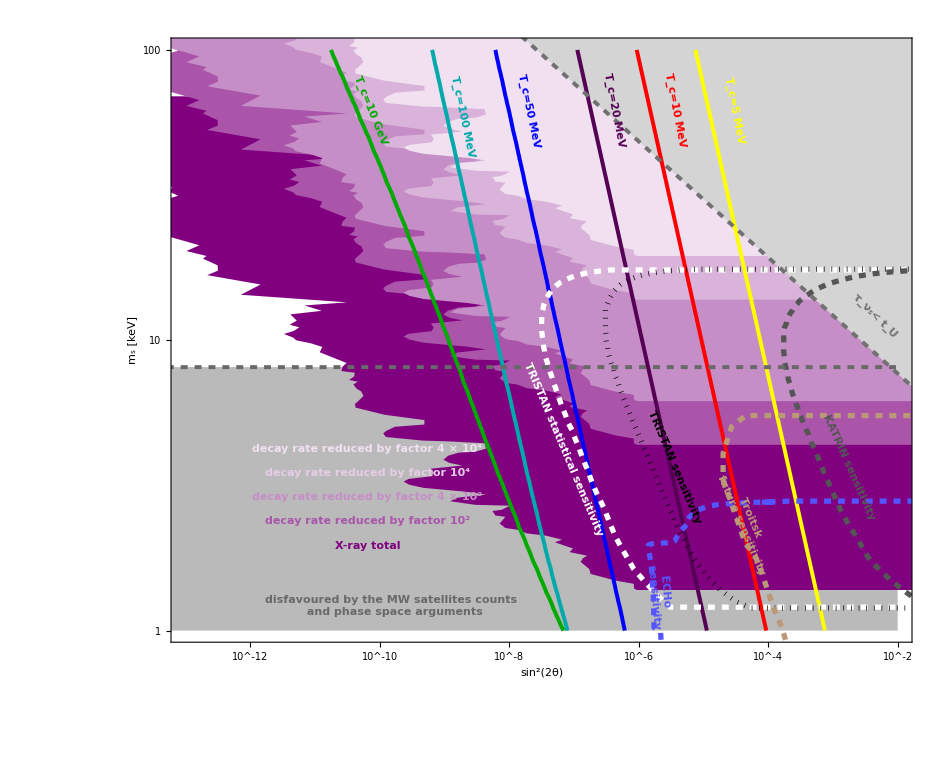

```mathematica
F3=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
Darker[Green],Thick,Thickness[0.003],Line[Linelist10GLog],
Darker[Cyan],Thick,Thickness[0.003],Line[pointst100M],
Blue,Thick,Thickness[0.003],Line[pointst50M],
Darker[Purple],Thick,Thickness[0.003],Line[Linelist20MLog],
Red,Thick,Thickness[0.003],Line[Linelist10MLog],
Yellow,Thick,Thickness[0.003],Line[Linelist5MLog],
(* + HUNTER lines *)
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["T_c=5 MeV", Bold],-79 Degree],Scaled[{0.76,0.88}]],
Red, Text[Rotate[Style["T_c=10 MeV", Bold],-79 Degree],Scaled[{0.68,0.88}]],
Darker[Purple], Text[Rotate[Style["T_c=20 MeV", Bold],-79 Degree],Scaled[{0.598,0.88}]],
Blue, Text[Rotate[Style["T_c=50 MeV", Bold],-78 Degree],Scaled[{0.483,0.88}]],
Darker[Cyan], Text[Rotate[Style["T_c=100 MeV", Bold],-78 Degree],Scaled[{0.394,0.87}]],
Darker[Green], Text[Rotate[Style["T_c=10 GeV", Bold],-68 Degree],Scaled[{0.27,0.88}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.265,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],

FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.68,0.29}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
(* + HUNTER lables *)
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]],
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-85 Degree],Scaled[{0.66,0.08}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F3.pdf",F3]
```

/Users/cristinabenso/Downloads/aliveandkicking_restored//plots/F3.pdf

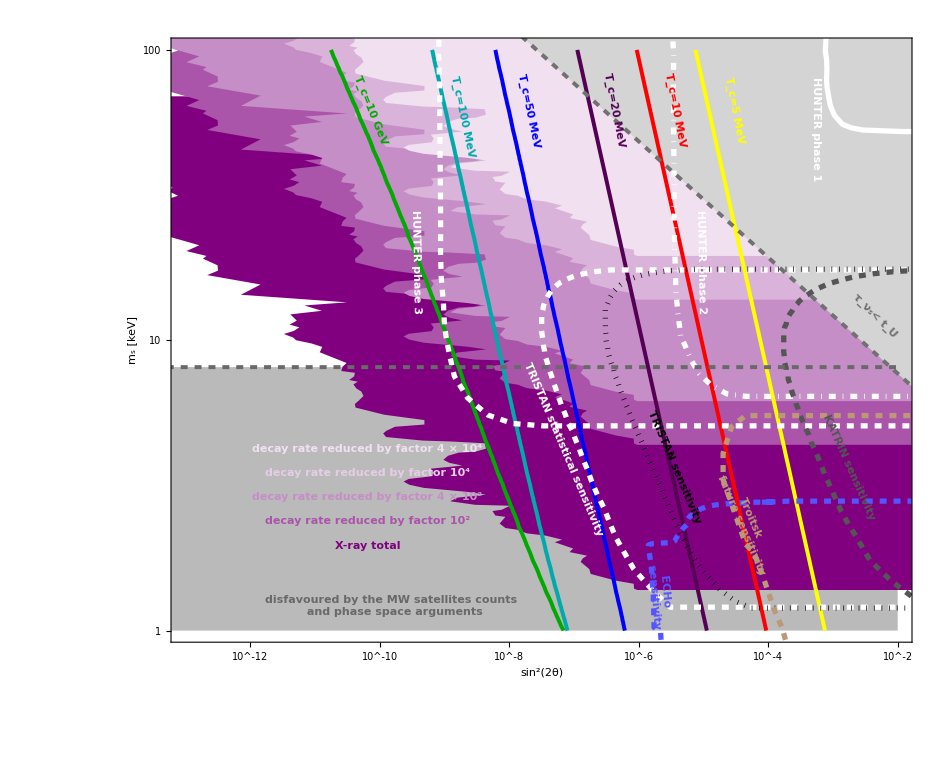

```mathematica
F3HUNTER=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
Darker[Green],Thick,Thickness[0.003],Line[Linelist10GLog],
Darker[Cyan],Thick,Thickness[0.003],Line[pointst100M],
Blue,Thick,Thickness[0.003],Line[pointst50M],
Darker[Purple],Thick,Thickness[0.003],Line[Linelist20MLog],
Red,Thick,Thickness[0.003],Line[Linelist10MLog],
Yellow,Thick,Thickness[0.003],Line[Linelist5MLog],
White, Thick,Thickness[0.004],Line[HUNT1Log],
White, DotDashed,Thickness[0.004],Line[HUNT2Log],
White, Dashed,Thickness[0.004],Line[HUNT3Log],
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["T_c=5 MeV", Bold],-79 Degree],Scaled[{0.76,0.88}]],
Red, Text[Rotate[Style["T_c=10 MeV", Bold],-79 Degree],Scaled[{0.68,0.88}]],
Darker[Purple], Text[Rotate[Style["T_c=20 MeV", Bold],-79 Degree],Scaled[{0.598,0.88}]],
Blue, Text[Rotate[Style["T_c=50 MeV", Bold],-78 Degree],Scaled[{0.483,0.88}]],
Darker[Cyan], Text[Rotate[Style["T_c=100 MeV", Bold],-78 Degree],Scaled[{0.394,0.87}]],
Darker[Green], Text[Rotate[Style["T_c=10 GeV", Bold],-68 Degree],Scaled[{0.27,0.88}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.265,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],

FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.68,0.29}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-89 Degree],Scaled[{0.715,0.63}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-89 Degree],Scaled[{0.33,0.63}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]],
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-85 Degree],Scaled[{0.66,0.08}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F3HUNTER.pdf",F3HUNTER]
```

/Users/cristinabenso/Downloads/aliveandkicking_restored//plots/F3HUNTER.pdf

#### benchmark points

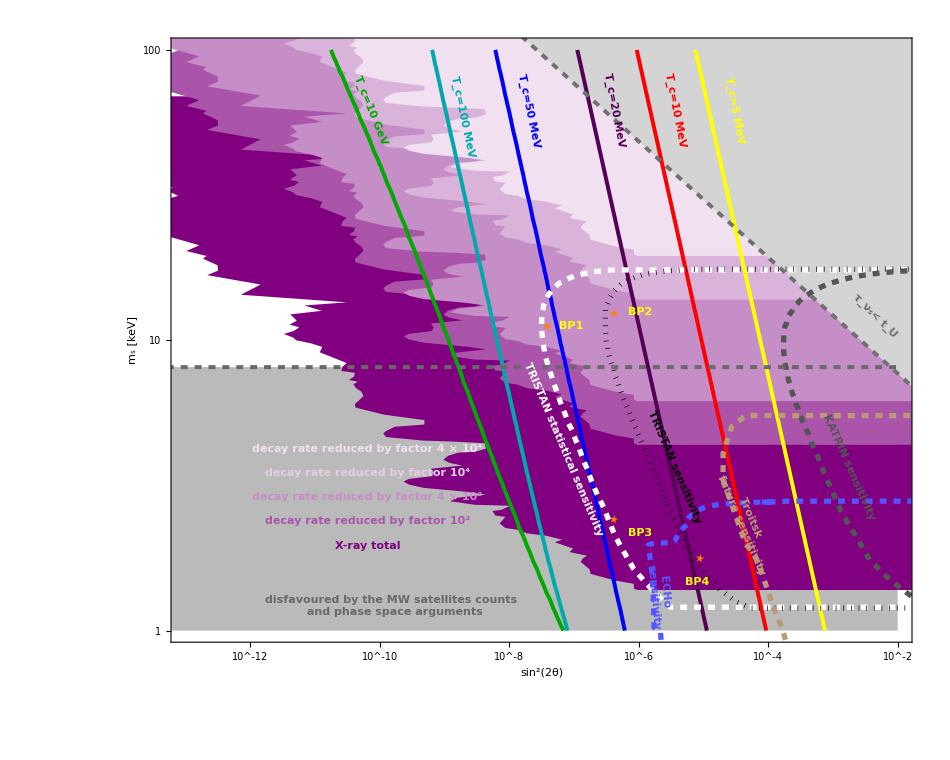

```mathematica
F3bps=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
Darker[Green],Thick,Thickness[0.003],Line[Linelist10GLog],
Darker[Cyan],Thick,Thickness[0.003],Line[pointst100M],
Blue,Thick,Thickness[0.003],Line[pointst50M],
Darker[Purple],Thick,Thickness[0.003],Line[Linelist20MLog],
Red,Thick,Thickness[0.003],Line[Linelist10MLog],
Yellow,Thick,Thickness[0.003],Line[Linelist5MLog],
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["T_c=5 MeV", Bold],-79 Degree],Scaled[{0.76,0.88}]],
Red, Text[Rotate[Style["T_c=10 MeV", Bold],-79 Degree],Scaled[{0.68,0.88}]],
Darker[Purple], Text[Rotate[Style["T_c=20 MeV", Bold],-79 Degree],Scaled[{0.598,0.88}]],
Blue, Text[Rotate[Style["T_c=50 MeV", Bold],-78 Degree],Scaled[{0.483,0.88}]],
Darker[Cyan], Text[Rotate[Style["T_c=100 MeV", Bold],-78 Degree],Scaled[{0.394,0.87}]],
Darker[Green], Text[Rotate[Style["T_c=10 GeV", Bold],-68 Degree],Scaled[{0.27,0.88}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.265,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],

FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.68,0.29}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]],
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-85 Degree],Scaled[{0.66,0.08}]],
FontSize->25,
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.503,0.523}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.593,0.546}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.593,0.205}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.71,0.14}]],
FontSize->22,
Yellow,Text[Rotate[Style["BP1", Bold],0 Degree],Scaled[{0.54,0.523}]],
Yellow,Text[Rotate[Style["BP2", Bold],0 Degree],Scaled[{0.633,0.546}]],
Yellow,Text[Rotate[Style["BP3", Bold],0 Degree],Scaled[{0.633,0.18}]],
Yellow,Text[Rotate[Style["BP4", Bold],0 Degree],Scaled[{0.71,0.1}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F3bps.pdf",F3bps]
```

/Users/cristinabenso/Downloads/aliveandkicking_restored//plots/F3bps.pdf

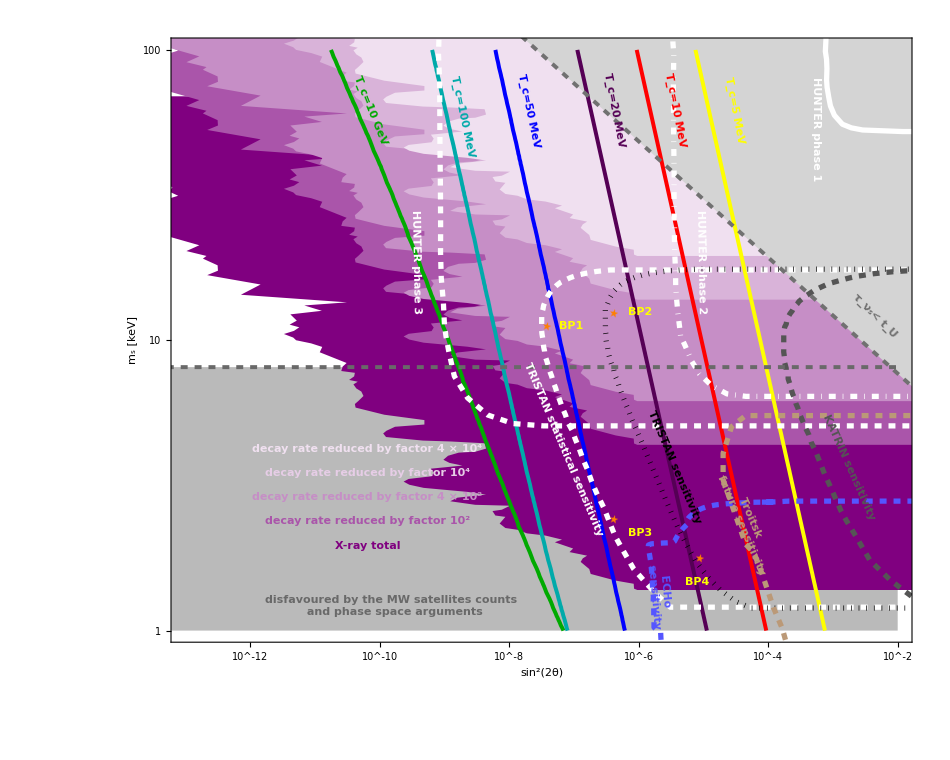

```mathematica
F3bpsHUNTER=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
Darker[Green],Thick,Thickness[0.003],Line[Linelist10GLog],
Darker[Cyan],Thick,Thickness[0.003],Line[pointst100M],
Blue,Thick,Thickness[0.003],Line[pointst50M],
Darker[Purple],Thick,Thickness[0.003],Line[Linelist20MLog],
Red,Thick,Thickness[0.003],Line[Linelist10MLog],
Yellow,Thick,Thickness[0.003],Line[Linelist5MLog],
White, Thick,Thickness[0.004],Line[HUNT1Log],
White, DotDashed,Thickness[0.004],Line[HUNT2Log],
White, Dashed,Thickness[0.004],Line[HUNT3Log],
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Lighter[Blue],Dashed,Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["T_c=5 MeV", Bold],-79 Degree],Scaled[{0.76,0.88}]],
Red, Text[Rotate[Style["T_c=10 MeV", Bold],-79 Degree],Scaled[{0.68,0.88}]],
Darker[Purple], Text[Rotate[Style["T_c=20 MeV", Bold],-79 Degree],Scaled[{0.598,0.88}]],
Blue, Text[Rotate[Style["T_c=50 MeV", Bold],-78 Degree],Scaled[{0.483,0.88}]],
Darker[Cyan], Text[Rotate[Style["T_c=100 MeV", Bold],-78 Degree],Scaled[{0.394,0.87}]],
Darker[Green], Text[Rotate[Style["T_c=10 GeV", Bold],-68 Degree],Scaled[{0.27,0.88}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.265,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],

FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.68,0.29}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.85}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-89 Degree],Scaled[{0.715,0.63}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-89 Degree],Scaled[{0.33,0.63}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]],
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-85 Degree],Scaled[{0.66,0.08}]],
FontSize->25,
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.503,0.523}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.593,0.546}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.593,0.205}]],
Orange,Text[Rotate["★",-85 Degree],Scaled[{0.71,0.14}]],
FontSize->22,
Yellow,Text[Rotate[Style["BP1", Bold],0 Degree],Scaled[{0.54,0.523}]],
Yellow,Text[Rotate[Style["BP2", Bold],0 Degree],Scaled[{0.633,0.546}]],
Yellow,Text[Rotate[Style["BP3", Bold],0 Degree],Scaled[{0.633,0.18}]],
Yellow,Text[Rotate[Style["BP4", Bold],0 Degree],Scaled[{0.71,0.1}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/F3bpsHUNTER.pdf",F3bpsHUNTER]
```

/Users/cristinabenso/Downloads/aliveandkicking_restored//plots/F3bpsHUNTER.pdf

## Ω_S/Ω_DM as a function of T_C

Fig 5 in the draft:
Tc only in the interval (1 MeV, ∼80 MeV)
4 lines: 2 for the TRISTAN region + 2 for the KATRIN region
running the new code

```mathematica
SterileabundanceRatio[sin22theta_?NumericQ,Msn_?NumericQ,Tfinal_?NumericQ,Tini_?NumericQ]:=
Module[{stod, rhoch, omegaDM},
stod=2891.2 (*cm^-3*);
rhoch= 1.053*10^-5 (*(GeV/c^2)cm^-3*);
omegaDM=0.1186;

1/omegaDM*stod/rhoch*45/(4 Pi^4*10.75)*Msn*
NIntegrate[(distribfunctions[sin22theta,Msn,Tfinal,Tini, r])*r^2,{r,0,500},Method->{"GlobalAdaptive","MaxErrorIncreases"->35,Method->"GaussKronrodRule"},MaxRecursion->30]];
```

#### BP1 : (-7.51546, 1.04852) (TRISTAN-stat maximum)

```mathematica
10^-7.51546 (*sin22theta*)
```

3.05169×10^-8

```mathematica
10^1.04852(*Msn*)
```

11.182

```mathematica
SterileRatioListBP1={}; 
For[Tc=0.005, Tc≤0.080, Tc =Tc+0.001,
AppendTo[SterileRatioListBP1, {{Tc*10^3},SterileabundanceRatio[3.05168708696545*^-8,11.18201318472257*^-6,0.001,Tc]}];]
```

```mathematica
SterileRatioListBP1;
```

```mathematica
SterileRatioBP1= Interpolation[SterileRatioListBP1,InterpolationOrder->1];
```

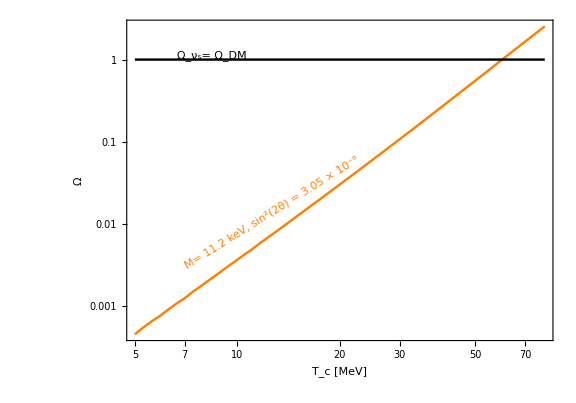

```mathematica
LogLogPlot[{SterileRatioBP1[Tv], 1},{Tv,5,80},(* PlotLabel->"Ω for different M",*) 
ImageSize->Large, Frame->True, BaseStyle->{FontFamily->"Times",FontSize->25},FrameLabel->{Style[HoldForm["T_c [MeV]"],30,Black,FontFamily->Times],Style[HoldForm["Ω"],30,Black,FontFamily->Times]},
PlotRange->All(*{{5*10^-7,10^4},{10^-9,0.5}}*),
PlotStyle->{{Orange,Thick,Thickness[0.003]}, {Black,Thick,Thickness[0.003]}},
FrameTicksStyle->Black,
FrameStyle->Directive[FontSize->15,Black], ImageMargins->5, ImagePadding->{{100,30},{85,20}},AspectRatio->0.7,
Epilog->{FontSize->15,
Orange,Text[Rotate[Style["M= 11.2 keV, sin^2(2θ) = 3.05 × 10^-8"],32Degree],Scaled[{0.34,0.40}]], 
Black, Text[Rotate[Style["Ω_ν_s= Ω_DM"],0Degree],Scaled[{0.2,0.89}]]}]
```

#### BP2 : (-6.5282, 1.09402) (TRISTAN maximum)

```mathematica
10^-6.5282 (*sin22theta*)
```

2.96347×10^-7

```mathematica
10^1.09402(*Msn*)
```

12.4171

```mathematica
SterileRatioListBP2={}; 
For[Tc=0.005, Tc≤0.080, Tc =Tc+0.001,
AppendTo[SterileRatioListBP2, {{Tc*10^3},SterileabundanceRatio[2.963466348548615*^-7,12.41709489110937*^-6,0.001,Tc]}];]
```

```mathematica
SterileRatioListBP2;
```

```mathematica
SterileRatioBP2= Interpolation[SterileRatioListBP2,InterpolationOrder->1];
```

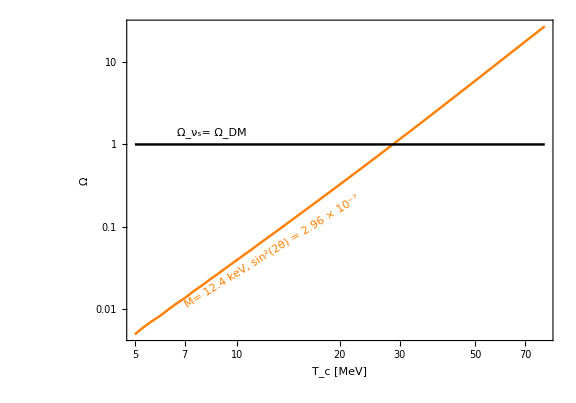

```mathematica
LogLogPlot[{SterileRatioBP2[Tv], 1},{Tv,5,80},(* PlotLabel->"Ω for different M",*) 
ImageSize->Large, Frame->True, BaseStyle->{FontFamily->"Times",FontSize->25},FrameLabel->{Style[HoldForm["T_c [MeV]"],30,Black,FontFamily->Times],Style[HoldForm["Ω"],30,Black,FontFamily->Times]},
PlotRange->All(*{{5*10^-7,10^4},{10^-9,0.5}}*),
PlotStyle->{{Orange,Thick,Thickness[0.003]}, {Black,Thick,Thickness[0.003]}},
FrameTicksStyle->Black,
FrameStyle->Directive[FontSize->15,Black], ImageMargins->5, ImagePadding->{{100,30},{85,20}},AspectRatio->0.7,
Epilog->{FontSize->15,
Orange,Text[Rotate[Style["M= 12.4 keV, sin^2(2θ) = 2.96 × 10^-7"],32Degree],Scaled[{0.34,0.28}]], 
Black, Text[Rotate[Style["Ω_ν_s= Ω_DM"],0Degree],Scaled[{0.2,0.65}]]}]
```

#### BP3 : (-6.5282, 0.408475) (TRISTAN-stat lower mass)

```mathematica
10^-6.5282 (*sin22theta*)
```

2.96347×10^-7

```mathematica
10^0.408475(*Msn*)
```

2.56139

```mathematica
SterileRatioListBP3={}; 
For[Tc=0.005, Tc≤0.080, Tc =Tc+0.001,
AppendTo[SterileRatioListBP3, {{Tc*10^3},SterileabundanceRatio[2.963466348548615*^-7,2.5613858146241975*^-6,0.001,Tc]}];]
```

```mathematica
SterileRatioListBP3;
```

```mathematica
SterileRatioBP3= Interpolation[SterileRatioListBP3,InterpolationOrder->1];
```

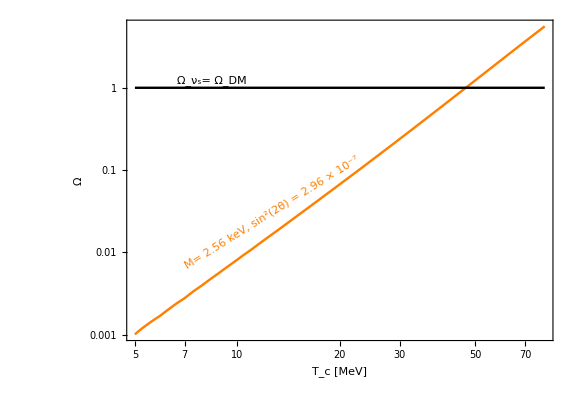

```mathematica
LogLogPlot[{SterileRatioBP3[Tv], 1},{Tv,5,80},(* PlotLabel->"Ω for different M",*) 
ImageSize->Large, Frame->True, BaseStyle->{FontFamily->"Times",FontSize->25},FrameLabel->{Style[HoldForm["T_c [MeV]"],30,Black,FontFamily->Times],Style[HoldForm["Ω"],30,Black,FontFamily->Times]},
PlotRange->All(*{{5*10^-7,10^4},{10^-9,0.5}}*),
PlotStyle->{{Orange,Thick,Thickness[0.003]}, {Black,Thick,Thickness[0.003]}},
FrameTicksStyle->Black,
FrameStyle->Directive[FontSize->15,Black], ImageMargins->5, ImagePadding->{{100,30},{85,20}},AspectRatio->0.7,
Epilog->{FontSize->15,
Orange,Text[Rotate[Style["M= 2.56 keV, sin^2(2θ) = 2.96 × 10^-7"],32Degree],Scaled[{0.34,0.4}]], 
Black, Text[Rotate[Style["Ω_ν_s= Ω_DM"],0Degree],Scaled[{0.2,0.81}]]}]
```

#### BP4 : (-5.24742, 0.27804) (TRISTAN lower mass)

```mathematica
10^-5.24742 (*sin22theta*)
```

5.65692×10^-6

```mathematica
10^0.27804(*Msn*)
```

1.89688

```mathematica
SterileRatioListBP4={}; 
For[Tc=0.005, Tc≤0.080, Tc =Tc+0.001,
AppendTo[SterileRatioListBP4, {{Tc*10^3},SterileabundanceRatio[5.656919518006072*^-6,1.8968806223275054*^-6,0.001,Tc]}];]
```

```mathematica
SterileRatioListBP4;
```

```mathematica
SterileRatioBP4= Interpolation[SterileRatioListBP4,InterpolationOrder->1];
```

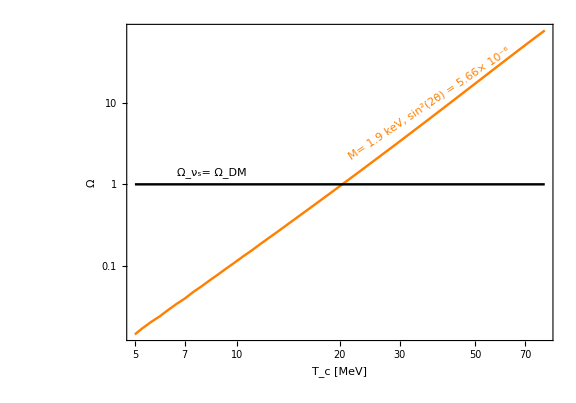

```mathematica
LogLogPlot[{SterileRatioBP4[Tv], 1},{Tv,5,80},(* PlotLabel->"Ω for different M",*) 
ImageSize->Large, Frame->True, BaseStyle->{FontFamily->"Times",FontSize->25},FrameLabel->{Style[HoldForm["T_c [MeV]"],30,Black,FontFamily->Times],Style[HoldForm["Ω"],30,Black,FontFamily->Times]},
PlotRange->All(*{{5*10^-7,10^4},{10^-9,0.5}}*),
PlotStyle->{{Orange,Thick,Thickness[0.003]}, {Black,Thick,Thickness[0.003]}},
FrameTicksStyle->Black,
FrameStyle->Directive[FontSize->15,Black], ImageMargins->5, ImagePadding->{{100,30},{85,20}},AspectRatio->0.7,
Epilog->{FontSize->15,
Orange,Text[Rotate[Style["M= 1.9 keV, sin^2(2θ) = 5.66× 10^-6"],34Degree],Scaled[{0.71,0.75}]], 
Black, Text[Rotate[Style["Ω_ν_s= Ω_DM"],0Degree],Scaled[{0.2,0.53}]]}]
```

#### Final Plot

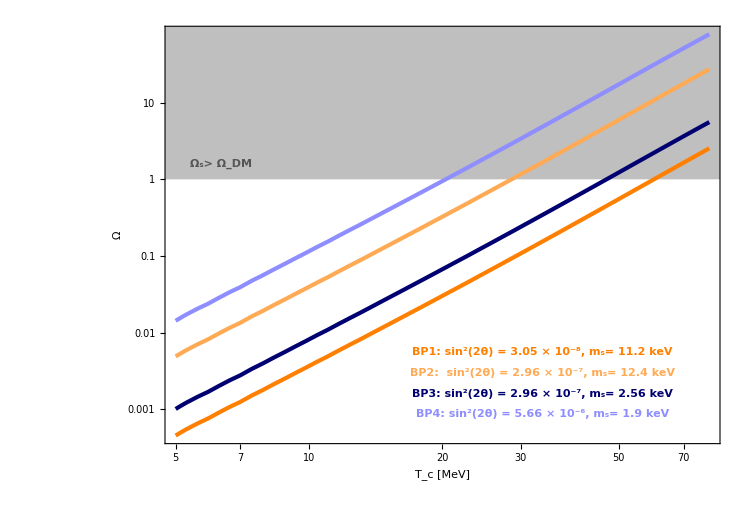

```mathematica
Benchmarks= LogLogPlot[{ SterileRatioBP1[Tv],SterileRatioBP2[Tv], SterileRatioBP3[Tv],SterileRatioBP4[Tv]},{Tv,5,80},
ImageSize->750, Frame->True, BaseStyle->{FontFamily->"Times",FontSize->25},FrameLabel->{Style[HoldForm["T_c [MeV]"],25,Black,FontFamily->Times],Style[HoldForm["Ω"],25,Black,FontFamily->Times]},
(*PlotRange->{{1, 10^3},{10^-12, 100}},*)
PlotStyle->{{Orange,Thick,Thickness[0.004]},{Lighter[Orange],Thick,Thickness[0.004]},{Darker[Darker[Blue]],Thick,Thickness[0.004]},{Lighter[Lighter[Blue]],Thick,Thickness[0.004]}},
FrameTicksStyle->Black,FrameTicks->Automatic,
FrameStyle->Directive[FontSize->20,Black], ImageMargins->5, ImagePadding->{{100,30},{85,20}},AspectRatio->0.7,
Prolog->{
RGBColor[128/255,128/255,128/255, 0.5],Polygon[{{0,0},{1000,0},{1000,100},{0,100}}]
},
Epilog->{
FontSize->18,
Orange,  Text[Rotate[Style["BP1: sin^2(2θ) = 3.05 × 10^-8, m_s= 11.2 keV", Bold],-0 Degree],Scaled[{0.68,0.22}]],
Lighter[Orange],  Text[Rotate[Style["BP2:  sin^2(2θ) = 2.96 × 10^-7, m_s= 12.4 keV", Bold],-0 Degree],Scaled[{0.68,0.17}]],
Darker[Darker[Blue]],  Text[Rotate[Style["BP3: sin^2(2θ) = 2.96 × 10^-7, m_s= 2.56 keV", Bold],-0 Degree],Scaled[{0.68,0.12}]],
Lighter[Lighter[Blue]],  Text[Rotate[Style["BP4: sin^2(2θ) = 5.66 × 10^-6, m_s= 1.9 keV", Bold],-0 Degree],Scaled[{0.68,0.07}]],
FontSize->20, 
Darker[Gray], Text[Rotate[Style["Ω_s> Ω_DM", Bold],0Degree],Scaled[{0.1,0.67}]]}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/Benchmarks.pdf",Benchmarks]
```

/Users/cristinabenso/Downloads/aliveandkicking_restored//plots/Benchmarks.pdf

## Shi-Fuller mechanism with T_c=30 MeV

We use the publicly available code called sterile-dm (https://github.com/ntveem/sterile-dm) to get the values of sterile neutrino DM corresponding to different values of the parameters m_s and sin^2(2θ), and we slightly modify the code to shift the value of the temperature at which the production started at our discretion (in particular we consider the case relative to T_c=30 MeV).

In the following, we report the data we collected with sterile-dm, to have a self consistent code with no need to run sterile-dm again every time.

### L = 0 ⟶ leptasymi = 0

#### data

?   Are these data simulated with sterile-dm or with our code?

```mathematica
ScanListSF030M= {{{1.*^-14,1.*^-6},2.4451346878412486*^-10},{{1.*^-14,1.2589254117941676*^-6},3.078378437131308*^-10},{{1.*^-14,1.584893192461114*^-6},3.8755570863407047*^-10},{{1.*^-14,1.995262314968881*^-6},4.879123294109717*^-10},{{1.*^-14,2.5118864315095823*^-6},6.142520614829216*^-10},{{1.*^-14,3.1622776601683826*^-6},7.733029559973475*^-10},{{1.*^-14,3.981071705534978*^-6},9.735350529259903*^-10},{{1.*^-14,5.01187233627273*^-6},1.2256114415085885*^-9},{{1.*^-14,6.309573444801942*^-6},1.542956108602403*^-9},{{1.*^-14,7.94328234724283*^-6},1.942468814915339*^-9},{{1.*^-14,0.000010000000000000021},2.4454250688799495*^-9},{{1.*^-14,0.000012589254117941702},3.078609125054583*^-9},{{1.*^-14,0.000015848931924611172},3.8757403497722245*^-9},{{1.*^-14,0.00001995262314968885},4.879268867879669*^-9},{{1.*^-14,0.000025118864315095876},6.14263625197279*^-9},{{1.*^-14,0.00003162277660168389},7.733121415720191*^-9},{{1.*^-14,0.00003981071705534985},9.735423493824733*^-9},{{1.*^-14,0.0000501187233627274},1.225617237337689*^-8},{{1.*^-14,0.00006309573444801955},1.5429607124170004*^-8},{{1.*^-14,0.00007943282347242846},1.942472471867232*^-8},{{1.*^-14,0.00010000000000000038},2.4454279737060937*^-8},{{1.*^-14,0.00012589254117941701},3.0786114324430386*^-8},{{1.*^-14,0.00015848931924611174},3.875742176170937*^-8},{{1.*^-14,0.0001995262314968885},4.8792703237453206*^-8},{{3.1622776601683796*^-14,1.*^-6},7.732194815934309*^-10},{{3.1622776601683796*^-14,1.2589254117941676*^-6},9.734687425015668*^-10},{{3.1622776601683796*^-14,1.584893192461114*^-6},1.2255587620946694*^-9},{{3.1622776601683796*^-14,1.995262314968881*^-6},1.5429142627033397*^-9},{{3.1622776601683796*^-14,2.5118864315095823*^-6},1.942435575876984*^-9},{{3.1622776601683796*^-14,3.1622776601683826*^-6},2.445398667500945*^-9},{{3.1622776601683796*^-14,3.981071705534978*^-6},3.0785881558156398*^-9},{{3.1622776601683796*^-14,5.01187233627273*^-6},3.875723689784064*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},4.8792556647962915*^-9},{{3.1622776601683796*^-14,7.94328234724283*^-6},6.142625752063206*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},7.733113081404977*^-9},{{3.1622776601683796*^-14,0.000012589254117941702},9.735416924284482*^-9},{{3.1622776601683796*^-14,0.000015848931924611172},1.225616713047877*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},1.5429602971777506*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.9424721435606086*^-8},{{3.1622776601683796*^-14,0.00003162277660168389},2.445427714838491*^-8},{{3.1622776601683796*^-14,0.00003981071705534985},3.078611229236925*^-8},{{3.1622776601683796*^-14,0.0000501187233627274},3.875742017804927*^-8},{{3.1622776601683796*^-14,0.00006309573444801955},4.879270201806106*^-8},{{3.1622776601683796*^-14,0.00007943282347242846},6.142637316386155*^-8},{{3.1622776601683796*^-14,0.00010000000000000038},7.733122267304054*^-8},{{3.1622776601683796*^-14,0.00012589254117941701},9.735424177888361*^-8},{{3.1622776601683796*^-14,0.00015848931924611174},1.2256172980514*^-7},{{3.1622776601683796*^-14,0.0001995262314968885},1.542960757562901*^-7},{{1.*^-13,1.*^-6},2.4451346551643512*^-9},{{1.*^-13,1.2589254117941676*^-6},3.0783783959908328*^-9},{{1.*^-13,1.584893192461114*^-6},3.875557091200007*^-9},{{1.*^-13,1.995262314968881*^-6},4.8791233010652116*^-9},{{1.*^-13,2.5118864315095823*^-6},6.142520623585652*^-9},{{1.*^-13,3.1622776601683826*^-6},7.733029570997046*^-9},{{1.*^-13,3.981071705534978*^-6},9.73535054313784*^-9},{{1.*^-13,5.01187233627273*^-6},1.2256114403517803*^-8},{{1.*^-13,6.309573444801942*^-6},1.542956107146047*^-8},{{1.*^-13,7.94328234724283*^-6},1.942468817684299*^-8},{{1.*^-13,0.000010000000000000021},2.4454250723658865*^-8},{{1.*^-13,0.000012589254117941702},3.078609129443128*^-8},{{1.*^-13,0.000015848931924611172},3.875740348870454*^-8},{{1.*^-13,0.00001995262314968885},4.879268874835042*^-8},{{1.*^-13,0.000025118864315095876},6.142636260729044*^-8},{{1.*^-13,0.00003162277660168389},7.7331214267437*^-8},{{1.*^-13,0.00003981071705534985},9.735423484635643*^-8},{{1.*^-13,0.0000501187233627274},1.225617239084797*^-7},{{1.*^-13,0.00006309573444801955},1.542960714616489*^-7},{{1.*^-13,0.00007943282347242846},1.9424724746362116*^-7},{{1.*^-13,0.00010000000000000038},2.445427977192033*^-7},{{1.*^-13,0.00012589254117941701},3.07861143683155*^-7},{{1.*^-13,0.00015848931924611174},3.875742181695807*^-7},{{1.*^-13,0.0001995262314968885},4.879270319139843*^-7},{{3.162277660168379*^-13,1.*^-6},7.732194792058474*^-9},{{3.162277660168379*^-13,1.2589254117941676*^-6},9.734687341710864*^-9},{{3.162277660168379*^-13,1.584893192461114*^-6},1.2255587570199917*^-8},{{3.162277660168379*^-13,1.995262314968881*^-6},1.5429142509435745*^-8},{{3.162277660168379*^-13,2.5118864315095823*^-6},1.942435561072167*^-8},{{3.162277660168379*^-13,3.1622776601683826*^-6},2.4453986488626603*^-8},{{3.162277660168379*^-13,3.981071705534978*^-6},3.078588132351319*^-8},{{3.162277660168379*^-13,5.01187233627273*^-6},3.8757236602441374*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},4.879255606057102*^-8},{{3.162277660168379*^-13,7.94328234724283*^-6},6.142625705245534*^-8},{{3.162277660168379*^-13,0.000010000000000000021},7.733113022464902*^-8},{{3.162277660168379*^-13,0.000012589254117941702},9.735416807084197*^-8},{{3.162277660168379*^-13,0.000015848931924611172},1.2256167037064897*^-7},{{3.162277660168379*^-13,0.00001995262314968885},1.5429602854112164*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.9424721287474287*^-7},{{3.162277660168379*^-13,0.00003162277660168389},2.445427696199972*^-7},{{3.162277660168379*^-13,0.00003981071705534985},3.078611205772426*^-7},{{3.162277660168379*^-13,0.0000501187233627274},3.875741988264842*^-7},{{3.162277660168379*^-13,0.00006309573444801955},4.879270164597028*^-7},{{3.162277660168379*^-13,0.00007943282347242846},6.142637269542682*^-7},{{3.162277660168379*^-13,0.00010000000000000038},7.733122208331634*^-7},{{3.162277660168379*^-13,0.00012589254117941701},9.735424103686986*^-7},{{3.162277660168379*^-13,0.00015848931924611174},1.2256172832967341*^-6},{{3.162277660168379*^-13,0.0001995262314968885},1.5429607457963515*^-6},{{1.*^-12,1.*^-6},2.445134683089053*^-8},{{1.*^-12,1.2589254117941676*^-6},3.078378422865731*^-8},{{1.*^-12,1.584893192461114*^-6},3.87555708005227*^-8},{{1.*^-12,1.995262314968881*^-6},4.879123294090763*^-8},{{1.*^-12,2.5118864315095823*^-6},6.14252061480519*^-8},{{1.*^-12,3.1622776601683826*^-6},7.73302954485763*^-8},{{1.*^-12,3.981071705534978*^-6},9.735350510229972*^-8},{{1.*^-12,5.01187233627273*^-6},1.2256114391128648*^-7},{{1.*^-12,6.309573444801942*^-6},1.5429561055863605*^-7},{{1.*^-12,7.94328234724283*^-6},1.9424688070021264*^-7},{{1.*^-12,0.000010000000000000021},2.4454250589178035*^-7},{{1.*^-12,0.000012589254117941702},3.0786091125129633*^-7},{{1.*^-12,0.000015848931924611172},3.87574032755668*^-7},{{1.*^-12,0.00001995262314968885},4.879268848002538*^-7},{{1.*^-12,0.000025118864315095876},6.142636226948968*^-7},{{1.*^-12,0.00003162277660168389},7.733121384217032*^-7},{{1.*^-12,0.00003981071705534985},9.735423454164629*^-7},{{1.*^-12,0.0000501187233627274},1.2256172323447873*^-6},{{1.*^-12,0.00006309573444801955},1.5429607061313073*^-6},{{1.*^-12,0.00007943282347242846},1.942472463954003*^-6},{{1.*^-12,0.00010000000000000038},2.445427963743937*^-6},{{1.*^-12,0.00012589254117941701},3.0786114199013943*^-6},{{1.*^-12,0.00015848931924611174},3.875742160381974*^-6},{{1.*^-12,0.0001995262314968885},4.879270303868173*^-6},{{3.1622776601683794*^-12,1.*^-6},7.732194749184358*^-8},{{3.1622776601683794*^-12,1.2589254117941676*^-6},9.734687315166341*^-8},{{3.1622776601683794*^-12,1.584893192461114*^-6},1.225558747803811*^-7},{{3.1622776601683794*^-12,1.995262314968881*^-6},1.5429142520088828*^-7},{{3.1622776601683794*^-12,2.5118864315095823*^-6},1.942435561704786*^-7},{{3.1622776601683794*^-12,3.1622776601683826*^-6},2.445398644353993*^-7},{{3.1622776601683794*^-12,3.981071705534978*^-6},3.078588129586747*^-7},{{3.1622776601683794*^-12,5.01187233627273*^-6},3.8757236567634885*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},4.87925560167504*^-7},{{3.1622776601683794*^-12,7.94328234724283*^-6},6.142625713195917*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},7.733113032473827*^-7},{{3.1622776601683794*^-12,0.000012589254117941702},9.735416819684729*^-7},{{3.1622776601683794*^-12,0.000015848931924611172},1.2256167052927978*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},1.5429602874082815*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},1.9424721312615683*^-6},{{3.1622776601683794*^-12,0.00003162277660168389},2.4454276993650802*^-6},{{3.1622776601683794*^-12,0.00003981071705534985},3.078611209757066*^-6},{{3.1622776601683794*^-12,0.0000501187233627274},3.875741993281194*^-6},{{3.1622776601683794*^-12,0.00006309573444801955},4.879270170912232*^-6},{{3.1622776601683794*^-12,0.00007943282347242846},6.142637277493117*^-6},{{3.1622776601683794*^-12,0.00010000000000000038},7.73312218710693*^-6},{{3.1622776601683794*^-12,0.00012589254117941701},9.735424076966783*^-6},{{3.1622776601683794*^-12,0.00015848931924611174},0.00001225617279932857},{{3.1622776601683794*^-12,0.0001995262314968885},0.000015429607415614806},{{1.*^-11,1.*^-6},2.4451346457349824*^-7},{{1.*^-11,1.2589254117941676*^-6},3.078378383037798*^-7},{{1.*^-11,1.584893192461114*^-6},3.87555704699616*^-7},{{1.*^-11,1.995262314968881*^-6},4.879123211676155*^-7},{{1.*^-11,2.5118864315095823*^-6},6.142520508355811*^-7},{{1.*^-11,3.1622776601683826*^-6},7.733029410678319*^-7},{{1.*^-11,3.981071705534978*^-6},9.73535037540309*^-7},{{1.*^-11,5.01187233627273*^-6},1.2256114215920642*^-6},{{1.*^-11,6.309573444801942*^-6},1.5429560941215982*^-6},{{1.*^-11,7.94328234724283*^-6},1.942468783990037*^-6},{{1.*^-11,0.000010000000000000021},2.4454250299472026*^-6},{{1.*^-11,0.000012589254117941702},3.078609053263065*^-6},{{1.*^-11,0.000015848931924611172},3.875740252965388*^-6},{{1.*^-11,0.00001995262314968885},4.879268754097624*^-6},{{1.*^-11,0.000025118864315095876},6.142636108729705*^-6},{{1.*^-11,0.00003162277660168389},7.733121235387676*^-6},{{1.*^-11,0.00003981071705534985},9.735423266799569*^-6},{{1.*^-11,0.0000501187233627274},0.000012256172087569078},{{1.*^-11,0.00006309573444801955},0.0000154296067643595},{{1.*^-11,0.00007943282347242846},0.000019424724265697572},{{1.*^-11,0.00010000000000000038},0.00002445427916679975},{{1.*^-11,0.00012589254117941701},0.00003078611360651387},{{1.*^-11,0.00015848931924611174},0.000038757420857905846},{{1.*^-11,0.0001995262314968885},0.000048792702099631454},{{3.1622776601683794*^-11,1.*^-6},7.732194445875506*^-7},{{3.1622776601683794*^-11,1.2589254117941676*^-6},9.734686850674212*^-7},{{3.1622776601683794*^-11,1.584893192461114*^-6},1.2255586973399717*^-6},{{3.1622776601683794*^-11,1.995262314968881*^-6},1.542914186968243*^-6},{{3.1622776601683794*^-11,2.5118864315095823*^-6},1.942435466675502*^-6},{{3.1622776601683794*^-11,3.1622776601683826*^-6},2.445398538534013*^-6},{{3.1622776601683794*^-11,3.981071705534978*^-6},3.078587987334669*^-6},{{3.1622776601683794*^-11,5.01187233627273*^-6},3.875723470160573*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},4.879255368265126*^-6},{{3.1622776601683794*^-11,7.94328234724283*^-6},6.142625410757892*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},7.73311273657968*^-6},{{3.1622776601683794*^-11,0.000012589254117941702},9.735416447175415*^-6},{{3.1622776601683794*^-11,0.000015848931924611172},0.000012256166393897797},{{3.1622776601683794*^-11,0.00001995262314968885},0.000015429602044412473},{{3.1622776601683794*^-11,0.000025118864315095876},0.000019424720268122223},{{3.1622776601683794*^-11,0.00003162277660168389},0.00002445427594064188},{{3.1622776601683794*^-11,0.00003981071705534985},0.0000307861107719103},{{3.1622776601683794*^-11,0.0000501187233627274},0.00003875741828140815},{{3.1622776601683794*^-11,0.00006309573444801955},0.00004879269960809249},{{3.1622776601683794*^-11,0.00007943282347242846},0.0000614263701298894},{{3.1622776601683794*^-11,0.00010000000000000038},0.00007733121888842173},{{3.1622776601683794*^-11,0.00012589254117941701},0.00009735423697076799},{{3.1622776601683794*^-11,0.00015848931924611174},0.00012256172326610912},{{3.1622776601683794*^-11,0.0001995262314968885},0.0001542960692662684},{{1.*^-10,1.*^-6},2.445134287196429*^-6},{{1.*^-10,1.2589254117941676*^-6},3.0783779439883767*^-6},{{1.*^-10,1.584893192461114*^-6},3.8755564447738*^-6},{{1.*^-10,1.995262314968881*^-6},4.879122499535911*^-6},{{1.*^-10,2.5118864315095823*^-6},6.1425195936990464*^-6},{{1.*^-10,3.1622776601683826*^-6},7.733028285969214*^-6},{{1.*^-10,3.981071705534978*^-6},9.735348922928232*^-6},{{1.*^-10,5.01187233627273*^-6},0.000012256112411550294},{{1.*^-10,6.309573444801942*^-6},0.00001542955824318242},{{1.*^-10,7.94328234724283*^-6},0.000019424684957375614},{{1.*^-10,0.000010000000000000021},0.000024454246605957568},{{1.*^-10,0.000012589254117941702},0.00003078608622584021},{{1.*^-10,0.000015848931924611172},0.000038757397018412844},{{1.*^-10,0.00001995262314968885},0.00004879268063627851},{{1.*^-10,0.000025118864315095876},0.00006142635238756572},{{1.*^-10,0.00003162277660168389},0.00007733120140156281},{{1.*^-10,0.00003981071705534985},0.0000973542189125595},{{1.*^-10,0.0000501187233627274},0.00012256170355862234},{{1.*^-10,0.00006309573444801955},0.00015429604584269355},{{1.*^-10,0.00007943282347242846},0.0001942472152112661},{{1.*^-10,0.00010000000000000038},0.0002445427565230298},{{1.*^-10,0.00012589254117941701},0.00030786109182024356},{{1.*^-10,0.00015848931924611174},0.0003875741525142213},{{1.*^-10,0.0001995262314968885},0.0004879269504148558},{{3.1622776601683795*^-10,1.*^-6},7.732190792304905*^-6},{{3.1622776601683795*^-10,1.2589254117941676*^-6},9.73468231272349*^-6},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.000012255581238226786},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.000015429134592891002},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.000019424345639243212},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.000024453973987734643},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.00003078586543097581},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.000038757216936372574},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.00004879253104931564},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00006142622608946962},{{3.1622776601683795*^-10,0.000010000000000000021},0.0000773310906892718},{{3.1622776601683795*^-10,0.000012589254117941702},0.0000973541187530837},{{3.1622776601683795*^-10,0.000015848931924611172},0.00012256160715508064},{{3.1622776601683795*^-10,0.00001995262314968885},0.0001542959492628583},{{3.1622776601683795*^-10,0.000025118864315095876},0.0001942471134247133},{{3.1622776601683795*^-10,0.00003162277660168389},0.0002445426444736847},{{3.1622776601683795*^-10,0.00003981071705534985},0.00030786096086040266},{{3.1622776601683795*^-10,0.0000501187233627274},0.00038757399898163016},{{3.1622776601683795*^-10,0.00006309573444801955},0.000487926764811706},{{3.1622776601683795*^-10,0.00007943282347242846},0.0006142634101482073},{{3.1622776601683795*^-10,0.00010000000000000038},0.000773311826510526},{{3.1622776601683795*^-10,0.00012589254117941701},0.0009735419066391058},{{3.1622776601683795*^-10,0.00015848931924611174},0.0012256166536729768},{{3.1622776601683795*^-10,0.0001995262314968885},0.0015429599531791645},{{1.*^-9,1.*^-6},0.000024451306332232174},{{1.*^-9,1.2589254117941676*^-6},0.000030783733790384744},{{1.*^-9,1.584893192461114*^-6},0.000038755507367960515},{{1.*^-9,1.995262314968881*^-6},0.00004879115287250817},{{1.*^-9,2.5118864315095823*^-6},0.00006142510549907805},{{1.*^-9,3.1622776601683826*^-6},0.00007733016876349911},{{1.*^-9,3.981071705534978*^-6},0.00009735334556877221},{{1.*^-9,5.01187233627273*^-6},0.00012256094285188095},{{1.*^-9,6.309573444801942*^-6},0.0001542953585184378},{{1.*^-9,7.94328234724283*^-6},0.00019424656294868398},{{1.*^-9,0.000010000000000000021},0.0002445421069148859},{{1.*^-9,0.000012589254117941702},0.0003078604077223874},{{1.*^-9,0.000015848931924611172},0.00038757339868799917},{{1.*^-9,0.00001995262314968885},0.00048792608611334754},{{1.*^-9,0.000025118864315095876},0.0006142626175956798},{{1.*^-9,0.00003162277660168389},0.0007733108733649388},{{1.*^-9,0.00003981071705534985},0.0009735407513662265},{{1.*^-9,0.0000501187233627274},0.0012256152278419872},{{1.*^-9,0.00006309573444801955},0.0015429581809491002},{{1.*^-9,0.00007943282347242846},0.0019424692784789479},{{1.*^-9,0.00010000000000000038},0.0024454239908112524},{{1.*^-9,0.00012589254117941701},0.0030786063743319715},{{1.*^-9,0.00015848931924611174},0.0038757358085038033},{{1.*^-9,0.0001995262314968885},0.004879262313406142},{{3.1622776601683795*^-9,1.*^-6},0.00007732154706621703},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.00009734636903433433},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.00012255524047973543},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.0001542906260879403},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.0001942425503306732},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.00024453859778569506},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.00030785722027153954},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.000387570359373437},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.00048792303612949395},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0006142593874216338},{{3.1622776601683795*^-9,0.000010000000000000021},0.0007733072942624372},{{3.1622776601683795*^-9,0.000012589254117941702},0.0009735366354679574},{{3.1622776601683795*^-9,0.000015848931924611172},0.0012256103458383198},{{3.1622776601683795*^-9,0.00001995262314968885},0.0015429522906658456},{{3.1622776601683795*^-9,0.000025118864315095876},0.0019424620660981958},{{3.1622776601683795*^-9,0.00003162277660168389},0.002445415022598935},{{3.1622776601683795*^-9,0.00003981071705534985},0.0030785952545831804},{{3.1622776601683795*^-9,0.0000501187233627274},0.0038757219047445453},{{3.1622776601683795*^-9,0.00006309573444801955},0.004879244882544265},{{3.1622776601683795*^-9,0.00007943282347242846},0.006142605457358453},{{3.1622776601683795*^-9,0.00010000000000000038},0.0077330821433151346},{{3.1622776601683795*^-9,0.00012589254117941701},0.009735373728107476},{{3.1622776601683795*^-9,0.00015848931924611174},0.012256109330240772},{{3.1622776601683795*^-9,0.0001995262314968885},0.015429527590696138},{{1.*^-8,1.*^-6},0.0002445094594130263},{{1.*^-8,1.2589254117941676*^-6},0.00030783279521218415},{{1.*^-8,1.584893192461114*^-6},0.00038754935180058107},{{1.*^-8,1.995262314968881*^-6},0.0004879043278846561},{{1.*^-8,2.5118864315095823*^-6},0.0006142419884179861},{{1.*^-8,3.1622776601683826*^-6},0.0007732902734976414},{{1.*^-8,3.981071705534978*^-6},0.0009735190849827782},{{1.*^-8,5.01187233627273*^-6},0.0012255913388815173},{{1.*^-8,6.309573444801942*^-6},0.0015429308018371452},{{1.*^-8,7.94328234724283*^-6},0.001942436961200248},{{1.*^-8,0.000010000000000000021},0.0024453849545082924},{{1.*^-8,0.000012589254117941702},0.003078558648594971},{{1.*^-8,0.000015848931924611172},0.0038756767960406073},{{1.*^-8,0.00001995262314968885},0.00487918884103073},{{1.*^-8,0.000025118864315095876},0.006142535505586542},{{1.*^-8,0.00003162277660168389},0.007732994563022596},{{1.*^-8,0.00003981071705534985},0.009735263819194772},{{1.*^-8,0.0000501187233627274},0.012255971328791452},{{1.*^-8,0.00006309573444801955},0.01542935405199589},{{1.*^-8,0.00007943282347242846},0.019424406218195505},{{1.*^-8,0.00010000000000000038},0.024453878500247744},{{1.*^-8,0.00012589254117941701},0.03078560937766041},{{1.*^-8,0.00015848931924611174},0.03875678605129032},{{1.*^-8,0.0001995262314968885},0.04879190294504275},{{3.162277660168379*^-8,1.*^-6},0.0007731793850002798},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.0009734182607681464},{{3.162277660168379*^-8,1.584893192461114*^-6},0.0012254951970018615},{{3.162277660168379*^-8,1.995262314968881*^-6},0.001542834243006126},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.0019423348272377908},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.002445271824297567},{{3.162277660168379*^-8,3.981071705534978*^-6},0.003078428454105685},{{3.162277660168379*^-8,5.01187233627273*^-6},0.0038755226946588124},{{3.162277660168379*^-8,6.309573444801942*^-6},0.004879002572383802},{{3.162277660168379*^-8,7.94328234724283*^-6},0.006142307183066399},{{3.162277660168379*^-8,0.000010000000000000021},0.007732711973339932},{{3.162277660168379*^-8,0.000012589254117941702},0.009734911927397706},{{3.162277660168379*^-8,0.000015848931924611172},0.012255531417918216},{{3.162277660168379*^-8,0.00001995262314968885},0.015428802653833841},{{3.162277660168379*^-8,0.000025118864315095876},0.01942371391796716},{{3.162277660168379*^-8,0.00003162277660168389},0.02445300868989051},{{3.162277660168379*^-8,0.00003981071705534985},0.030784515455167152},{{3.162277660168379*^-8,0.0000501187233627274},0.03875540990426397},{{3.162277660168379*^-8,0.00006309573444801955},0.048790171240006626},{{3.162277660168379*^-8,0.00007943282347242846},0.061423187104363175},{{3.162277660168379*^-8,0.00010000000000000038},0.07732721168932655},{{3.162277660168379*^-8,0.00012589254117941701},0.09734919198567306},{{3.162277660168379*^-8,0.00015848931924611174},0.1225553722686212},{{3.162277660168379*^-8,0.0001995262314968885},0.15428807282157705},{{1.*^-7,1.*^-6},0.0024447337889178114},{{1.*^-7,1.2589254117941676*^-6},0.0030778736799355133},{{1.*^-7,1.584893192461114*^-6},0.0038749215773035335},{{1.*^-7,1.995262314968881*^-6},0.004878323201086625},{{1.*^-7,2.5118864315095823*^-6},0.0061415133030824},{{1.*^-7,3.1622776601683826*^-6},0.007731761410862615},{{1.*^-7,3.981071705534978*^-6},0.009733754038718076},{{1.*^-7,5.01187233627273*^-6},0.012254104458731992},{{1.*^-7,6.309573444801942*^-6},0.015427030729637574},{{1.*^-7,7.94328234724283*^-6},0.019421502605455946},{{1.*^-7,0.000010000000000000021},0.02445024024344233},{{1.*^-7,0.000012589254117941702},0.030781042396406447},{{1.*^-7,0.000015848931924611172},0.03875104738487405},{{1.*^-7,0.00001995262314968885},0.04878468691167804},{{1.*^-7,0.000025118864315095876},0.06141628883216461},{{1.*^-7,0.00003162277660168389},0.07731853229106454},{{1.*^-7,0.00003981071705534985},0.09733826914770707},{{1.*^-7,0.0000501187233627274},0.12254162404272721},{{1.*^-7,0.00006309573444801955},0.15427076680132507},{{1.*^-7,0.00007943282347242846},0.1942153914221534},{{1.*^-7,0.00010000000000000038},0.2445026932709364},{{1.*^-7,0.00012589254117941701},0.3078106547644531},{{1.*^-7,0.00015848931924611174},0.38751065640570426},{{1.*^-7,0.0001995262314968885},0.4878470156681618},{{3.162277660168379*^-7,1.*^-6},0.007728187437866573},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.00972964154491958},{{3.162277660168379*^-7,1.584893192461114*^-6},0.012249234692673444},{{3.162277660168379*^-7,1.995262314968881*^-6},0.01542114422502698},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.019414286015623346},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.024441309324602985},{{3.162277660168379*^-7,3.981071705534978*^-6},0.030769921590405435},{{3.162277660168379*^-7,5.01187233627273*^-6},0.03873714415182448},{{3.162277660168379*^-7,6.309573444801942*^-6},0.04876726148798829},{{3.162277660168379*^-7,7.94328234724283*^-6},0.06139441244944718},{{3.162277660168379*^-7,0.000010000000000000021},0.07729104020299046},{{3.162277660168379*^-7,0.000012589254117941702},0.09730369765867891},{{3.162277660168379*^-7,0.000015848931924611172},0.12249813189934323},{{3.162277660168379*^-7,0.00001995262314968885},0.15421603978018972},{{3.162277660168379*^-7,0.000025118864315095876},0.19414651089250834},{{3.162277660168379*^-7,0.00003162277660168389},0.2444159932228836},{{3.162277660168379*^-7,0.00003981071705534985},0.3077015170657807},{{3.162277660168379*^-7,0.0000501187233627274},0.3873732734957206},{{3.162277660168379*^-7,0.00006309573444801955},0.4876740630884412},{{3.162277660168379*^-7,0.00007943282347242846},0.613945279890865},{{3.162277660168379*^-7,0.00010000000000000038},0.7729113174997564},{{3.162277660168379*^-7,0.00012589254117941701},0.9730377083196652},{{3.162277660168379*^-7,0.00015848931924611174},1.2249818955372707},{{3.162277660168379*^-7,0.0001995262314968885},1.5421608404961646},{{1.*^-6,1.*^-6},0.024411314743655765},{{1.*^-6,1.2589254117941676*^-6},0.030733379421774083},{{1.*^-6,1.584893192461114*^-6},0.03869210872883046},{{1.*^-6,1.995262314968881*^-6},0.04871133415728022},{{1.*^-6,2.5118864315095823*^-6},0.06132461590381561},{{1.*^-6,3.1622776601683826*^-6},0.0772036568963209},{{1.*^-6,3.981071705534978*^-6},0.09719407445489783},{{1.*^-6,5.01187233627273*^-6},0.12236043042600117},{{1.*^-6,6.309573444801942*^-6},0.1540429251584103},{{1.*^-6,7.94328234724283*^-6},0.19392876865638947},{{1.*^-6,0.000010000000000000021},0.2441420256167447},{{1.*^-6,0.000012589254117941702},0.3073567360532517},{{1.*^-6,0.000015848931924611172},0.3869393139970689},{{1.*^-6,0.00001995262314968885},0.48712781939593486},{{1.*^-6,0.000025118864315095876},0.6132576583326231},{{1.*^-6,0.00003162277660168389},0.7720457056752998},{{1.*^-6,0.00003981071705534985},0.9719479982455568},{{1.*^-6,0.0000501187233627274},1.223610068114815},{{1.*^-6,0.00006309573444801955},1.5404338298745852},{{1.*^-6,0.00007943282347242846},1.9392913284425533},{{1.*^-6,0.00010000000000000038},2.4414231465861986},{{1.*^-6,0.00012589254117941701},3.0735696536323354},{{1.*^-6,0.00015848931924611174},3.8693949645631185},{{1.*^-6,0.0001995262314968885},4.871279637938722},{{3.162277660168379*^-6,1.*^-6},0.07692295722816556},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.09684449978027708},{{3.162277660168379*^-6,1.584893192461114*^-6},0.12192336527886867},{{3.162277660168379*^-6,1.995262314968881*^-6},0.153495095203804},{{3.162277660168379*^-6,2.5118864315095823*^-6},0.19324099933753483},{{3.162277660168379*^-6,3.1622776601683826*^-6},0.24327769051312173},{{3.162277660168379*^-6,3.981071705534978*^-6},0.3062698030820885},{{3.162277660168379*^-6,5.01187233627273*^-6},0.3855719084168494},{{3.162277660168379*^-6,6.309573444801942*^-6},0.4854071126754861},{{3.162277660168379*^-6,7.94328234724283*^-6},0.6110920248726673},{{3.162277660168379*^-6,0.000010000000000000021},0.7693198127845621},{{3.162277660168379*^-6,0.000012589254117941702},0.9685166808697451},{{3.162277660168379*^-6,0.000015848931924611172},1.2192906034124646},{{3.162277660168379*^-6,0.00001995262314968885},1.5349961881679273},{{3.162277660168379*^-6,0.000025118864315095876},1.9324459151019524},{{3.162277660168379*^-6,0.00003162277660168389},2.4328054473167673},{{3.162277660168379*^-6,0.00003981071705534985},3.062720730516097},{{3.162277660168379*^-6,0.0000501187233627274},3.855737062638103},{{3.162277660168379*^-6,0.00006309573444801955},4.854085454416792},{{3.162277660168379*^-6,0.00007943282347242846},6.110931588585033},{{3.162277660168379*^-6,0.00010000000000000038},7.6932071911126805},{{3.162277660168379*^-6,0.00012589254117941701},9.685174020406775},{{3.162277660168379*^-6,0.00015848931924611174},12.192911688916167},{{3.162277660168379*^-6,0.0001995262314968885},15.349966417447051},{{0.00001,1.*^-6},0.2405650452561387},{{0.00001,1.2589254117941676*^-6},0.3028663465043593},{{0.00001,1.584893192461114*^-6},0.38129638526634047},{{0.00001,1.995262314968881*^-6},0.4800318473163047},{{0.00001,2.5118864315095823*^-6},0.6043307583595457},{{0.00001,3.1622776601683826*^-6},0.7608124872825835},{{0.00001,3.981071705534978*^-6},0.9578102520916065},{{0.00001,5.01187233627273*^-6},1.2058149151535709},{{0.00001,6.309573444801942*^-6},1.5180336131668313},{{0.00001,7.94328234724283*^-6},1.9110931366332393},{{0.00001,0.000010000000000000021},2.4059253384661656},{{0.00001,0.000012589254117941702},3.0288818378200157},{{0.00001,0.000015848931924611172},3.8131373398983293},{{0.00001,0.00001995262314968885},4.800456309972696},{{0.00001,0.000025118864315095876},6.043417083446051},{{0.00001,0.00003162277660168389},7.608211853925},{{0.00001,0.00003981071705534985},9.578171648871145},{{0.00001,0.0000501187233627274},12.058204010621626},{{0.00001,0.00006309573444801955},15.180379705448171},{{0.00001,0.00007943282347242846},19.11096597322289},{{0.00001,0.00010000000000000038},24.059280863767604},{{0.00001,0.00012589254117941701},30.28884018534923},{{0.00001,0.00015848931924611174},38.13139068051087},{{0.00001,0.0001995262314968885},48.00457674609319},{{0.00003162277660168379,1.*^-6},0.7349911717808782},{{0.00003162277660168379,1.2589254117941676*^-6},0.9253353630728349},{{0.00003162277660168379,1.584893192461114*^-6},1.1649570516029584},{{0.00003162277660168379,1.995262314968881*^-6},1.466616943849184},{{0.00003162277660168379,2.5118864315095823*^-6},1.8463795417194588},{{0.00003162277660168379,3.1622776601683826*^-6},2.3244685879237497},{{0.00003162277660168379,3.981071705534978*^-6},2.9263440319880947},{{0.00003162277660168379,5.01187233627273*^-6},3.684058022177921},{{0.00003162277660168379,6.309573444801942*^-6},4.637961521479244},{{0.00003162277660168379,7.94328234724283*^-6},5.8388533331424055},{{0.00003162277660168379,0.000010000000000000021},7.350685448653733},{{0.00003162277660168379,0.000012589254117941702},9.253968334439787},{{0.00003162277660168379,0.000015848931924611172},11.650058771978532},{{0.00003162277660168379,0.00001995262314968885},14.666557299851641},{{0.00003162277660168379,0.000025118864315095876},18.464103541663984},{{0.00003162277660168379,0.00003162277660168389},23.24493055338421},{{0.00003162277660168379,0.00003981071705534985},29.26363501432003},{{0.00003162277660168379,0.0000501187233627274},36.840734566070296},{{0.00003162277660168379,0.00006309573444801955},46.37973757273527},{{0.00003162277660168379,0.00007943282347242846},58.38863012480895},{{0.00003162277660168379,0.00010000000000000038},73.50693218507855},{{0.00003162277660168379,0.00012589254117941701},92.53974455189017},{{0.00003162277660168379,0.00015848931924611174},116.50063575087049},{{0.00003162277660168379,0.0001995262314968885},146.66561081901835},{{0.0001,1.*^-6},2.0977305154258366},{{0.0001,1.2589254117941676*^-6},2.6409673018382978},{{0.0001,1.584893192461114*^-6},3.3248452252700953},{{0.0001,1.995262314968881*^-6},4.185783291891562},{{0.0001,2.5118864315095823*^-6},5.269629638165369},{{0.0001,3.1622776601683826*^-6},6.634102852026059},{{0.0001,3.981071705534978*^-6},8.351866220354394},{{0.0001,5.01187233627273*^-6},10.51439710287928},{{0.0001,6.309573444801942*^-6},13.236857856203903},{{0.0001,7.94328234724283*^-6},16.664229693554795},{{0.0001,0.000010000000000000021},20.97903220721933},{{0.0001,0.000012589254117941702},26.411045000163046},{{0.0001,0.000015848931924611172},33.24954215809295},{{0.0001,0.00001995262314968885},41.85869891295255},{{0.0001,0.000025118864315095876},52.69698348304744},{{0.0001,0.00003162277660168389},66.34157467658832},{{0.0001,0.00003981071705534985},83.5190968884617},{{0.0001,0.0000501187233627274},105.14431537404532},{{0.0001,0.00006309573444801955},132.3688511794794},{{0.0001,0.00007943282347242846},166.64250977396057},{{0.0001,0.00010000000000000038},209.7904933488313},{{0.0001,0.00012589254117941701},264.1105848292042},{{0.0001,0.00015848931924611174},332.4955254765826},{{0.0001,0.0001995262314968885},418.58706391689014}};
```

```mathematica
ScanSF030M= Interpolation[ScanListSF030M, InterpolationOrder->1];
```

#### interpolation

```mathematica
plmuSFA030M=Normal@ContourPlot[ScanSF030M[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->150];
```

```mathematica
LinelistSFA030M=Cases[ plmuSFA030M,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

```mathematica
(*from GeV to keV in mass*)
SF030Mr = Table[{LinelistA030M⟦i,1⟧,LinelistA030M⟦i,2⟧*10^6} ,{i,1,Length[LinelistA030M]}];
```

```mathematica
LinelistSFA030MLog = Table[{Log10[SF030Mr⟦i,1⟧], Log10[SF030Mr⟦i,2⟧]}, {i ,1,Length[SF030Mr]}];
```

### L = 0.05 ⟶ leptasymi = 0.01215

#### data

```mathematica
ScanListSF00530M= {{{1.*^-14,1.*^-6},0.0001792869939357526},{{1.*^-14,1.2589254117941676*^-6},0.00018757660957218934},{{1.*^-14,1.584893192461114*^-6},0.00014330688347143723},{{1.*^-14,1.995262314968881*^-6},0.00005100706862076999},{{1.*^-14,2.5118864315095823*^-6},4.528413231992595*^-6},{{1.*^-14,3.1622776601683826*^-6},4.207161862139955*^-8},{{1.*^-14,3.981071705534978*^-6},1.015237318654466*^-9},{{1.*^-14,5.01187233627273*^-6},1.249074846496336*^-9},{{1.*^-14,6.309573444801942*^-6},1.5577854786937162*^-9},{{1.*^-14,7.94328234724283*^-6},1.9530635157892183*^-9},{{1.*^-14,0.000010000000000000021},2.4540570259160963*^-9},{{1.*^-14,0.000012589254117941702},3.086573562837452*^-9},{{1.*^-14,0.000015848931924611172},3.883875782993301*^-9},{{1.*^-14,0.00001995262314968885},4.888215256329647*^-9},{{1.*^-14,0.000025118864315095876},6.152973363178338*^-9},{{1.*^-14,0.00003162277660168389},7.745451478811892*^-9},{{1.*^-14,0.00003981071705534985},9.750429045216825*^-9},{{1.*^-14,0.0000501187233627274},1.2274665497510607*^-8},{{1.*^-14,0.00006309573444801955},1.545257915352269*^-8},{{1.*^-14,0.00007943282347242846},1.945340225800586*^-8},{{1.*^-14,0.00010000000000000038},2.449019160388809*^-8},{{1.*^-14,0.00012589254117941701},3.0831173775501285*^-8},{{1.*^-14,0.00015848931924611174},3.881402878750936*^-8},{{1.*^-14,0.0001995262314968885},4.8863872574211634*^-8},{{3.1622776601683796*^-14,1.*^-6},0.0003605466394458195},{{3.1622776601683796*^-14,1.2589254117941676*^-6},0.00038928005447990685},{{3.1622776601683796*^-14,1.584893192461114*^-6},0.0003215953180612395},{{3.1622776601683796*^-14,1.995262314968881*^-6},0.00013607228826097815},{{3.1622776601683796*^-14,2.5118864315095823*^-6},0.000014051555612461399},{{3.1622776601683796*^-14,3.1622776601683826*^-6},1.3292854054077247*^-7},{{3.1622776601683796*^-14,3.981071705534978*^-6},3.210462301062342*^-9},{{3.1622776601683796*^-14,5.01187233627273*^-6},3.949921517047909*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},4.926150203369695*^-9},{{3.1622776601683796*^-14,7.94328234724283*^-6},6.176129123645977*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},7.76040974372673*^-9},{{3.1622776601683796*^-14,0.000012589254117941702},9.760602601202125*^-9},{{3.1622776601683796*^-14,0.000015848931924611172},1.2281893594451421*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},1.5457893880810025*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.9457410181824514*^-8},{{3.1622776601683796*^-14,0.00003162277660168389},2.449326814390878*^-8},{{3.1622776601683796*^-14,0.00003981071705534985},3.0833563902111344*^-8},{{3.1622776601683796*^-14,0.0000501187233627274},3.881590043262665*^-8},{{3.1622776601683796*^-14,0.00006309573444801955},4.886534577842875*^-8},{{3.1622776601683796*^-14,0.00007943282347242846},6.151705928570621*^-8},{{3.1622776601683796*^-14,0.00010000000000000038},7.744478569010504*^-8},{{3.1622776601683796*^-14,0.00012589254117941701},9.749673192589611*^-8},{{3.1622776601683796*^-14,0.00015848931924611174},1.2274073595818817*^-7},{{3.1622776601683796*^-14,0.0001995262314968885},1.5452113240704792*^-7},{{1.*^-13,1.*^-6},0.000680450634807641},{{1.*^-13,1.2589254117941676*^-6},0.0007499956745996491},{{1.*^-13,1.584893192461114*^-6},0.0006521058745830708},{{1.*^-13,1.995262314968881*^-6},0.0003194790224917612},{{1.*^-13,2.5118864315095823*^-6},0.00004208673752335962},{{1.*^-13,3.1622776601683826*^-6},4.1917895195135393*^-7},{{1.*^-13,3.981071705534978*^-6},1.015237315136178*^-8},{{1.*^-13,5.01187233627273*^-6},1.2490748487238989*^-8},{{1.*^-13,6.309573444801942*^-6},1.557785459882571*^-8},{{1.*^-13,7.94328234724283*^-6},1.953063513581187*^-8},{{1.*^-13,0.000010000000000000021},2.4540570302975565*^-8},{{1.*^-13,0.000012589254117941702},3.0865735594741456*^-8},{{1.*^-13,0.000015848931924611172},3.883875786894073*^-8},{{1.*^-13,0.00001995262314968885},4.8882152491267723*^-8},{{1.*^-13,0.000025118864315095876},6.152973354113831*^-8},{{1.*^-13,0.00003162277660168389},7.745451453618087*^-8},{{1.*^-13,0.00003981071705534985},9.750429013502329*^-8},{{1.*^-13,0.0000501187233627274},1.2274665457586117*^-7},{{1.*^-13,0.00006309573444801955},1.5452579103262144*^-7},{{1.*^-13,0.00007943282347242846},1.9453402194732753*^-7},{{1.*^-13,0.00010000000000000038},2.449019152423235*^-7},{{1.*^-13,0.00012589254117941701},3.083117367522145*^-7},{{1.*^-13,0.00015848931924611174},3.881402866126527*^-7},{{1.*^-13,0.0001995262314968885},4.886387241527923*^-7},{{3.162277660168379*^-13,1.*^-6},0.001244110837683945},{{3.162277660168379*^-13,1.2589254117941676*^-6},0.0013877480389470592},{{3.162277660168379*^-13,1.584893192461114*^-6},0.001242138172381522},{{3.162277660168379*^-13,1.995262314968881*^-6},0.0006696353526850228},{{3.162277660168379*^-13,2.5118864315095823*^-6},0.00011643743451204415},{{3.162277660168379*^-13,3.1622776601683826*^-6},1.3140410484179606*^-6},{{3.162277660168379*^-13,3.981071705534978*^-6},3.210462293767433*^-8},{{3.162277660168379*^-13,5.01187233627273*^-6},3.949921488756218*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},4.9261501979381234*^-8},{{3.162277660168379*^-13,7.94328234724283*^-6},6.176129120842891*^-8},{{3.162277660168379*^-13,0.000010000000000000021},7.760409719305754*^-8},{{3.162277660168379*^-13,0.000012589254117941702},9.76060256736861*^-8},{{3.162277660168379*^-13,0.000015848931924611172},1.228189359969461*^-7},{{3.162277660168379*^-13,0.00001995262314968885},1.54578938686971*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.9457410178822702*^-7},{{3.162277660168379*^-13,0.00003162277660168389},2.4493268315840744*^-7},{{3.162277660168379*^-13,0.00003981071705534985},3.0833563807551794*^-7},{{3.162277660168379*^-13,0.0000501187233627274},3.8815900313592665*^-7},{{3.162277660168379*^-13,0.00006309573444801955},4.886534562858135*^-7},{{3.162277660168379*^-13,0.00007943282347242846},6.15170590970651*^-7},{{3.162277660168379*^-13,0.00010000000000000038},7.7444785137923*^-7},{{3.162277660168379*^-13,0.00012589254117941701},9.749673123074742*^-7},{{3.162277660168379*^-13,0.00015848931924611174},1.227407350830553*^-6},{{3.162277660168379*^-13,0.0001995262314968885},1.5452113130532952*^-6},{{1.*^-12,1.*^-6},0.00223933336777995},{{1.*^-12,1.2589254117941676*^-6},0.002514094863441226},{{1.*^-12,1.584893192461114*^-6},0.0022851805546848583},{{1.*^-12,1.995262314968881*^-6},0.00130019977510172},{{1.*^-12,2.5118864315095823*^-6},0.00028424633177964417},{{1.*^-12,3.1622776601683826*^-6},4.0458026180834305*^-6},{{1.*^-12,3.981071705534978*^-6},1.0152373164630716*^-7},{{1.*^-12,5.01187233627273*^-6},1.2490748469615272*^-7},{{1.*^-12,6.309573444801942*^-6},1.557785475170249*^-7},{{1.*^-12,7.94328234724283*^-6},1.9530635128756323*^-7},{{1.*^-12,0.000010000000000000021},2.4540570266246293*^-7},{{1.*^-12,0.000012589254117941702},3.0865735543639376*^-7},{{1.*^-12,0.000015848931924611172},3.8838757862246196*^-7},{{1.*^-12,0.00001995262314968885},4.888215271902104*^-7},{{1.*^-12,0.000025118864315095876},6.152973329360198*^-7},{{1.*^-12,0.00003162277660168389},7.745451461800384*^-7},{{1.*^-12,0.00003981071705534985},9.750429032670651*^-7},{{1.*^-12,0.0000501187233627274},1.2274665482146548*^-6},{{1.*^-12,0.00006309573444801955},1.5452579219742725*^-6},{{1.*^-12,0.00007943282347242846},1.945340220081739*^-6},{{1.*^-12,0.00010000000000000038},2.4490191531893323*^-6},{{1.*^-12,0.00012589254117941701},3.0831173684866527*^-6},{{1.*^-12,0.00015848931924611174},3.881402867340817*^-6},{{1.*^-12,0.0001995262314968885},4.8863872506738245*^-6},{{3.1622776601683794*^-12,1.*^-6},0.004000556691686871},{{3.1622776601683794*^-12,1.2589254117941676*^-6},0.004505449928131984},{{3.1622776601683794*^-12,1.584893192461114*^-6},0.00412624897412937},{{3.1622776601683794*^-12,1.995262314968881*^-6},0.0024130464855904982},{{3.1622776601683794*^-12,2.5118864315095823*^-6},0.0006095062166356409},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.000011851574906973299},{{3.1622776601683794*^-12,3.981071705534978*^-6},3.2104622747864726*^-7},{{3.1622776601683794*^-12,5.01187233627273*^-6},3.9499215077597465*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},4.926150213804796*^-7},{{3.1622776601683794*^-12,7.94328234724283*^-6},6.176129057511054*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},7.760409687117467*^-7},{{3.1622776601683794*^-12,0.000012589254117941702},9.76060261181559*^-7},{{3.1622776601683794*^-12,0.000015848931924611172},1.2281893570602628*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},1.5457893760213402*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},1.9457410092579303*^-6},{{3.1622776601683794*^-12,0.00003162277660168389},2.449326799134662*^-6},{{3.1622776601683794*^-12,0.00003981071705534985},3.083356376520103*^-6},{{3.1622776601683794*^-12,0.0000501187233627274},3.88159001446319*^-6},{{3.1622776601683794*^-12,0.00006309573444801955},4.886534555225612*^-6},{{3.1622776601683794*^-12,0.00007943282347242846},6.151705896272698*^-6},{{3.1622776601683794*^-12,0.00010000000000000038},7.744478531264567*^-6},{{3.1622776601683794*^-12,0.00012589254117941701},9.749673145071135*^-6},{{3.1622776601683794*^-12,0.00015848931924611174},0.0000122740736224171},{{3.1622776601683794*^-12,0.0001995262314968885},0.00001545211327419074},{{1.*^-11,1.*^-6},0.0071228952672262634},{{1.*^-11,1.2589254117941676*^-6},0.00803213023743138},{{1.*^-11,1.584893192461114*^-6},0.007378888011699929},{{1.*^-11,1.995262314968881*^-6},0.004368772470992545},{{1.*^-11,2.5118864315095823*^-6},0.0011862792469452233},{{1.*^-11,3.1622776601683826*^-6},0.000031061629893798104},{{1.*^-11,3.981071705534978*^-6},1.0152372884616012*^-6},{{1.*^-11,5.01187233627273*^-6},1.249074835259295*^-6},{{1.*^-11,6.309573444801942*^-6},1.5577854463156943*^-6},{{1.*^-11,7.94328234724283*^-6},1.9530634836745594*^-6},{{1.*^-11,0.000010000000000000021},2.454056989881837*^-6},{{1.*^-11,0.000012589254117941702},3.086573514917676*^-6},{{1.*^-11,0.000015848931924611172},3.883875704977392*^-6},{{1.*^-11,0.00001995262314968885},4.888215166417532*^-6},{{1.*^-11,0.000025118864315095876},6.152973196255042*^-6},{{1.*^-11,0.00003162277660168389},7.745451356857103*^-6},{{1.*^-11,0.00003981071705534985},9.750428865074919*^-6},{{1.*^-11,0.0000501187233627274},0.00001227466527298101},{{1.*^-11,0.00006309573444801955},0.000015452578860761618},{{1.*^-11,0.00007943282347242846},0.000019453402111498008},{{1.*^-11,0.00010000000000000038},0.000024490191167242312},{{1.*^-11,0.00012589254117941701},0.000030831173003971985},{{1.*^-11,0.00015848931924611174},0.000038814028037035155},{{1.*^-11,0.0001995262314968885},0.00004886387162942724},{{3.1622776601683794*^-11,1.*^-6},0.012662687956262434},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.014283613700657912},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.013133448352211393},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.007808152965445674},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.002178661769483175},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.0000689004151103664},{{3.1622776601683794*^-11,3.981071705534978*^-6},3.210462037436642*^-6},{{3.1622776601683794*^-11,5.01187233627273*^-6},3.9499212919765616*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},4.926149926629393*^-6},{{3.1622776601683794*^-11,7.94328234724283*^-6},6.1761287956512764*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},7.760409314926207*^-6},{{3.1622776601683794*^-11,0.000012589254117941702},9.760602127433015*^-6},{{3.1622776601683794*^-11,0.000015848931924611172},0.00001228189300612051},{{3.1622776601683794*^-11,0.00001995262314968885},0.000015457893047798246},{{3.1622776601683794*^-11,0.000025118864315095876},0.000019457409201973125},{{3.1622776601683794*^-11,0.00003162277660168389},0.000024493266853230787},{{3.1622776601683794*^-11,0.00003981071705534985},0.000030833562412811277},{{3.1622776601683794*^-11,0.0000501187233627274},0.00003881589845763024},{{3.1622776601683794*^-11,0.00006309573444801955},0.00004886534301583934},{{3.1622776601683794*^-11,0.00007943282347242846},0.00006151705616287288},{{3.1622776601683794*^-11,0.00010000000000000038},0.00007744478057541328},{{3.1622776601683794*^-11,0.00012589254117941701},0.00009749672692960752},{{3.1622776601683794*^-11,0.00015848931924611174},0.00012274072963555738},{{3.1622776601683794*^-11,0.0001995262314968885},0.0001545211243369339},{{1.*^-10,1.*^-6},0.022483138338114002},{{1.*^-10,1.2589254117941676*^-6},0.025358948010491836},{{1.*^-10,1.584893192461114*^-6},0.023310195236613606},{{1.*^-10,1.995262314968881*^-6},0.013865003605228073},{{1.*^-10,2.5118864315095823*^-6},0.003878490373964824},{{1.*^-10,3.1622776601683826*^-6},0.0001314596717320811},{{1.*^-10,3.981071705534978*^-6},0.00001015237099336096},{{1.*^-10,5.01187233627273*^-6},0.00001249074621804775},{{1.*^-10,6.309573444801942*^-6},0.00001557785212516375},{{1.*^-10,7.94328234724283*^-6},0.00001953063188030299},{{1.*^-10,0.000010000000000000021},0.000024540566285184494},{{1.*^-10,0.000012589254117941702},0.00003086573078204944},{{1.*^-10,0.000015848931924611172},0.000038838751470132685},{{1.*^-10,0.00001995262314968885},0.00004888214481240077},{{1.*^-10,0.000025118864315095876},0.00006152972343095272},{{1.*^-10,0.00003162277660168389},0.00007745450194101093},{{1.*^-10,0.00003981071705534985},0.00009750427498349083},{{1.*^-10,0.0000501187233627274},0.0001227466344557103},{{1.*^-10,0.00006309573444801955},0.00015452576604060083},{{1.*^-10,0.00007943282347242846},0.00019453398990915708},{{1.*^-10,0.00010000000000000038},0.0002449018755356091},{{1.*^-10,0.00012589254117941701},0.0003083116867370461},{{1.*^-10,0.00015848931924611174},0.0003881402260794269},{{1.*^-10,0.0001995262314968885},0.0004886386453926753},{{3.1622776601683795*^-10,1.*^-6},0.03985163014644471},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.04492581213027118},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.041252240668381686},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.024497873638600506},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.006768510651947295},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.00022915500322821957},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.00003210460091196366},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.00003949919212146916},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.000049261475469786225},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00006176125842676848},{{3.1622776601683795*^-10,0.000010000000000000021},0.00007760405656685734},{{3.1622776601683795*^-10,0.000012589254117941702},0.00009760597525778468},{{3.1622776601683795*^-10,0.000015848931924611172},0.00012281887166300213},{{3.1622776601683795*^-10,0.00001995262314968885},0.00015457885887319652},{{3.1622776601683795*^-10,0.000025118864315095876},0.00019457400141962856},{{3.1622776601683795*^-10,0.00003162277660168389},0.0002449325541029397},{{3.1622776601683795*^-10,0.00003981071705534985},0.00030833547879424684},{{3.1622776601683795*^-10,0.0000501187233627274},0.0003881588035190592},{{3.1622776601683795*^-10,0.00006309573444801955},0.0004886532036570581},{{3.1622776601683795*^-10,0.00007943282347242846},0.0006151702700681872},{{3.1622776601683795*^-10,0.00010000000000000038},0.0007744474566895197},{{3.1622776601683795*^-10,0.00012589254117941701},0.000974966811605803},{{3.1622776601683795*^-10,0.00015848931924611174},0.001227406720572713},{{3.1622776601683795*^-10,0.0001995262314968885},0.0015452105210612536},{{1.*^-9,1.*^-6},0.07039589021191103},{{1.*^-9,1.2589254117941676*^-6},0.07925922567868608},{{1.*^-9,1.584893192461114*^-6},0.07261703501658988},{{1.*^-9,1.995262314968881*^-6},0.0429925580226445},{{1.*^-9,2.5118864315095823*^-6},0.011560508636347012},{{1.*^-9,3.1622776601683826*^-6},0.00038438753401500895},{{1.*^-9,3.981071705534978*^-6},0.00010152351173940313},{{1.*^-9,5.01187233627273*^-6},0.00012490725828743585},{{1.*^-9,6.309573444801942*^-6},0.00015577828054522214},{{1.*^-9,7.94328234724283*^-6},0.00019530602485474399},{{1.*^-9,0.000010000000000000021},0.0002454052961408625},{{1.*^-9,0.000012589254117941702},0.0003086568475869936},{{1.*^-9,0.000015848931924611172},0.00038838693894047187},{{1.*^-9,0.00001995262314968885},0.0004888207196292356},{{1.*^-9,0.000025118864315095876},0.000615296323392002},{{1.*^-9,0.00003162277660168389},0.0007745438743678949},{{1.*^-9,0.00003981071705534985},0.0009750413011556651},{{1.*^-9,0.0000501187233627274},0.0012274645330757005},{{1.*^-9,0.00006309573444801955},0.0015452553772281124},{{1.*^-9,0.00007943282347242846},0.001945337029344785},{{1.*^-9,0.00010000000000000038},0.0024490151337355492},{{1.*^-9,0.00012589254117941701},0.0030831123059254528},{{1.*^-9,0.00015848931924611174},0.003881396501625667},{{1.*^-9,0.0001995262314968885},0.004886379223228595},{{3.1622776601683795*^-9,1.*^-6},0.12335153056746104},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.1384599521578039},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.12635768629862884},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.07449812429537463},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.019097010523615066},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.0006629960565484419},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.0003210440333837522},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.00039498987592874555},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.0004926123495885501},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0006176096448390533},{{3.1622776601683795*^-9,0.000010000000000000021},0.0007760369003212448},{{3.1622776601683795*^-9,0.000012589254117941702},0.0009760551681401611},{{3.1622776601683795*^-9,0.000015848931924611172},0.0012281829616247293},{{3.1622776601683795*^-9,0.00001995262314968885},0.0015457813560051967},{{3.1622776601683795*^-9,0.000025118864315095876},0.0019457309008133624},{{3.1622776601683795*^-9,0.00003162277660168389},0.0024493140701525523},{{3.1622776601683795*^-9,0.00003981071705534985},0.003083340361033069},{{3.1622776601683795*^-9,0.0000501187233627274},0.0038815698800739227},{{3.1622776601683795*^-9,0.00006309573444801955},0.004886509184892709},{{3.1622776601683795*^-9,0.00007943282347242846},0.0061516739609604075},{{3.1622776601683795*^-9,0.00010000000000000038},0.0077444383271840726},{{3.1622776601683795*^-9,0.00012589254117941701},0.009749622499249953},{{3.1622776601683795*^-9,0.00015848931924611174},0.012274009806867717},{{3.1622776601683795*^-9,0.0001995262314968885},0.015452032959562845},{{1.*^-8,1.*^-6},0.21146811954696504},{{1.*^-8,1.2589254117941676*^-6},0.2356256548201699},{{1.*^-8,1.584893192461114*^-6},0.21383185754247164},{{1.*^-8,1.995262314968881*^-6},0.12577893250357444},{{1.*^-8,2.5118864315095823*^-6},0.02983326468530477},{{1.*^-8,3.1622776601683826*^-6},0.0013142759993818153},{{1.*^-8,3.981071705534978*^-6},0.0010152153567319568},{{1.*^-8,5.01187233627273*^-6},0.001249052143496159},{{1.*^-8,6.309573444801942*^-6},0.0015577587912247593},{{1.*^-8,7.94328234724283*^-6},0.0019530308385662955},{{1.*^-8,0.000010000000000000021},0.0024540163530066368},{{1.*^-8,0.000012589254117941702},0.0030865226249621584},{{1.*^-8,0.000015848931924611172},0.0038838118456655433},{{1.*^-8,0.00001995262314968885},0.004888134829637328},{{1.*^-8,0.000025118864315095876},0.006152872157457484},{{1.*^-8,0.00003162277660168389},0.007745324176324304},{{1.*^-8,0.00003981071705534985},0.009750268761988767},{{1.*^-8,0.0000501187233627274},0.012274463754014793},{{1.*^-8,0.00006309573444801955},0.015452325183344055},{{1.*^-8,0.00007943282347242846},0.01945308231549235},{{1.*^-8,0.00010000000000000038},0.02448978913452047},{{1.*^-8,0.00012589254117941701},0.030830667031620726},{{1.*^-8,0.00015848931924611174},0.0388133909552498},{{1.*^-8,0.0001995262314968885},0.04886306963505124},{{3.162277660168379*^-8,1.*^-6},0.3391292362109412},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.37305784339017917},{{3.162277660168379*^-8,1.584893192461114*^-6},0.3385106534323868},{{3.162277660168379*^-8,1.995262314968881*^-6},0.2013704386327472},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.042656453399740876},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.0032079524858387755},{{3.162277660168379*^-8,3.981071705534978*^-6},0.003210242764558061},{{3.162277660168379*^-8,5.01187233627273*^-6},0.0039496942616538515},{{3.162277660168379*^-8,6.309573444801942*^-6},0.004925883461645077},{{3.162277660168379*^-8,7.94328234724283*^-6},0.006175802312486063},{{3.162277660168379*^-8,0.000010000000000000021},0.007760003007613515},{{3.162277660168379*^-8,0.000012589254117941702},0.009760093244873567},{{3.162277660168379*^-8,0.000015848931924611172},0.012281253969744922},{{3.162277660168379*^-8,0.00001995262314968885},0.015457089709298325},{{3.162277660168379*^-8,0.000025118864315095876},0.019456398314644588},{{3.162277660168379*^-8,0.00003162277660168389},0.02449199484926532},{{3.162277660168379*^-8,0.00003981071705534985},0.030831961411839574},{{3.162277660168379*^-8,0.0000501187233627274},0.038813883270909205},{{3.162277660168379*^-8,0.00006309573444801955},0.04886280648983149},{{3.162277660168379*^-8,0.00007943282347242846},0.061513862580925935},{{3.162277660168379*^-8,0.00010000000000000038},0.07744076219062962},{{3.162277660168379*^-8,0.00012589254117941701},0.09749166598758555},{{3.162277660168379*^-8,0.00015848931924611174},0.12273435836938228},{{3.162277660168379*^-8,0.0001995262314968885},0.1545131035854979},{{1.*^-7,1.*^-6},0.45964732902557964},{{1.*^-7,1.2589254117941676*^-6},0.5052719152922611},{{1.*^-7,1.584893192461114*^-6},0.4708994757766996},{{1.*^-7,1.995262314968881*^-6},0.2931834485437713},{{1.*^-7,2.5118864315095823*^-6},0.05530592123537098},{{1.*^-7,3.1622776601683826*^-6},0.009114400784933849},{{1.*^-7,3.981071705534978*^-6},0.010150178430506447},{{1.*^-7,5.01187233627273*^-6},0.012488476510174998},{{1.*^-7,6.309573444801942*^-6},0.01557518769006504},{{1.*^-7,7.94328234724283*^-6},0.019527367749369997},{{1.*^-7,0.000010000000000000021},0.024536503582986077},{{1.*^-7,0.000012589254117941702},0.030860642332672064},{{1.*^-7,0.000015848931924611172},0.03883236206834788},{{1.*^-7,0.00001995262314968885},0.048874110723052255},{{1.*^-7,0.000025118864315095876},0.06151961574748659},{{1.*^-7,0.00003162277660168389},0.0774417830989346},{{1.*^-7,0.00003981071705534985},0.09748826601714519},{{1.*^-7,0.0000501187233627274},0.12272648425304888},{{1.*^-7,0.00006309573444801955},0.15450040116961894},{{1.*^-7,0.00007943282347242846},0.19450205910181229},{{1.*^-7,0.00010000000000000038},0.2448616800894631},{{1.*^-7,0.00012589254117941701},0.30826108261443486},{{1.*^-7,0.00015848931924611174},0.3880765170425757},{{1.*^-7,0.0001995262314968885},0.4885584442095121},{{3.162277660168379*^-7,1.*^-6},0.5200459343697129},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.580712360053102},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.07489682016417362},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.02774260211216538},{{3.162277660168379*^-7,3.981071705534978*^-6},0.032082693470010096},{{3.162277660168379*^-7,5.01187233627273*^-6},0.03947650623695176},{{3.162277660168379*^-7,6.309573444801942*^-6},0.04923484061353045},{{3.162277660168379*^-7,7.94328234724283*^-6},0.0617286273597237},{{3.162277660168379*^-7,0.000010000000000000021},0.07756344355903208},{{3.162277660168379*^-7,0.000012589254117941702},0.09755511023305746},{{3.162277660168379*^-7,0.000015848931924611172},0.12275499722525625},{{3.162277660168379*^-7,0.00001995262314968885},0.15449854850824002},{{3.162277660168379*^-7,0.000025118864315095876},0.19447296871662503},{{3.162277660168379*^-7,0.00003162277660168389},0.24480541145806248},{{3.162277660168379*^-7,0.00003981071705534985},0.3081754532276203},{{3.162277660168379*^-7,0.0000501187233627274},0.3879573762335742},{{3.162277660168379*^-7,0.00006309573444801955},0.48839963700628275},{{3.162277660168379*^-7,0.00007943282347242846},0.6148510706136489},{{3.162277660168379*^-7,0.00010000000000000038},0.7740456184326359},{{3.162277660168379*^-7,0.00012589254117941701},0.974460941839401},{{3.162277660168379*^-7,0.00015848931924611174},1.226769875239882},{{3.162277660168379*^-7,0.0001995262314968885},1.544408784148155},{{1.*^-6,2.5118864315095823*^-6},0.1315320519366892},{{1.*^-6,3.1622776601683826*^-6},0.08640937831764642},{{1.*^-6,3.981071705534978*^-6},0.10130500624196484},{{1.*^-6,5.01187233627273*^-6},0.12468073821094228},{{1.*^-6,6.309573444801942*^-6},0.15551225584723039},{{1.*^-6,7.94328234724283*^-6},0.19498007720398003},{{1.*^-6,0.000010000000000000021},0.24499960583756525},{{1.*^-6,0.000012589254117941702},0.3081487409453747},{{1.*^-6,0.000015848931924611172},0.38774886714812096},{{1.*^-6,0.00001995262314968885},0.4880184716700275},{{1.*^-6,0.000025118864315095876},0.6142870627908288},{{1.*^-6,0.00003162277660168389},0.7732737947884735},{{1.*^-6,0.00003981071705534985},0.9734426823665597},{{1.*^-6,0.0000501187233627274},1.2254523453088562},{{1.*^-6,0.00006309573444801955},1.542722415138123},{{1.*^-6,0.00007943282347242846},1.9421483783817899},{{1.*^-6,0.00010000000000000038},2.445001025912606},{{1.*^-6,0.00012589254117941701},3.078058945929831},{{1.*^-6,0.00015848931924611174},3.87503477294191},{{1.*^-6,0.0001995262314968885},4.87837034376358},{{3.162277660168379*^-6,3.1622776601683826*^-6},0.2698234376602227},{{3.162277660168379*^-6,3.981071705534978*^-6},0.3188766246014997},{{3.162277660168379*^-6,5.01187233627273*^-6},0.39273537220660815},{{3.162277660168379*^-6,6.309573444801942*^-6},0.4899622453373057},{{3.162277660168379*^-6,7.94328234724283*^-6},0.6143616444120916},{{3.162277660168379*^-6,0.000010000000000000021},0.7719938615337218},{{3.162277660168379*^-6,0.000012589254117941702},0.9709912507381677},{{3.162277660168379*^-6,0.000015848931924611172},1.2218236621902319},{{3.162277660168379*^-6,0.00001995262314968885},1.5377857222343223},{{3.162277660168379*^-6,0.000025118864315095876},1.9356720299277708},{{3.162277660168379*^-6,0.00003162277660168389},2.436655753766591},{{3.162277660168379*^-6,0.00003981071705534985},3.067408212566783},{{3.162277660168379*^-6,0.0000501187233627274},3.8615153020947584},{{3.162277660168379*^-6,0.00006309573444801955},4.861264171406651},{{3.162277660168379*^-6,0.00007943282347242846},6.119894042687079},{{3.162277660168379*^-6,0.00010000000000000038},7.704431139914549},{{3.162277660168379*^-6,0.00012589254117941701},9.699257624128764},{{3.162277660168379*^-6,0.00015848931924611174},12.210604855982785},{{3.162277660168379*^-6,0.0001995262314968885},15.372211434104685},{{0.00001,3.1622776601683826*^-6},0.8321500955895684},{{0.00001,3.981071705534978*^-6},0.9940683387992564},{{0.00001,5.01187233627273*^-6},1.2268358356710323},{{0.00001,6.309573444801942*^-6},1.5315724456148523},{{0.00001,7.94328234724283*^-6},1.9209081059956632},{{0.00001,0.000010000000000000021},2.414017784209612},{{0.00001,0.000012589254117941702},3.0364178934212145},{{0.00001,0.000015848931924611172},3.82088641656172},{{0.00001,0.00001995262314968885},4.809015716629881},{{0.00001,0.000025118864315095876},6.053335344932288},{{0.00001,0.00003162277660168389},7.620063624233908},{{0.00001,0.00003981071705534985},9.592611385601945},{{0.00001,0.0000501187233627274},12.07601241859566},{{0.00001,0.00006309573444801955},15.202510949285681},{{0.00001,0.00007943282347242846},19.138601604480026},{{0.00001,0.00010000000000000038},24.093894018043898},{{0.00001,0.00012589254117941701},30.332274938251878},{{0.00001,0.00015848931924611174},38.185960345608265},{{0.00001,0.0001995262314968885},48.07318741717389},{{0.00003162277660168379,3.1622776601683826*^-6},2.4763041169329205},{{0.00003162277660168379,3.981071705534978*^-6},3.012945240514525},{{0.00003162277660168379,5.01187233627273*^-6},3.7370836516497556},{{0.00003162277660168379,6.309573444801942*^-6},4.673412485720968},{{0.00003162277660168379,7.94328234724283*^-6},5.865333567889498},{{0.00003162277660168379,0.000010000000000000021},7.373062561430256},{{0.00003162277660168379,0.000012589254117941702},9.275208632971417},{{0.00003162277660168379,0.000015848931924611172},11.672198933104733},{{0.00003162277660168379,0.00001995262314968885},14.69123585456895},{{0.00003162277660168379,0.000025118864315095876},18.492866788132005},{{0.00003162277660168379,0.00003162277660168389},23.279427422369075},{{0.00003162277660168379,0.00003981071705534985},29.30576115542906},{{0.00003162277660168379,0.0000501187233627274},36.89276340030365},{{0.00003162277660168379,0.00006309573444801955},46.44445449007574},{{0.00003162277660168379,0.00007943282347242846},58.46948953701951},{{0.00003162277660168379,0.00010000000000000038},73.60824206454622},{{0.00003162277660168379,0.00012589254117941701},92.66690411042845},{{0.00003162277660168379,0.00015848931924611174},116.66041682441487},{{0.00003162277660168379,0.0001995262314968885},146.86651817893096},{{0.0001,3.1622776601683826*^-6},6.824995412929235},{{0.0001,3.981071705534978*^-6},8.481249686481195},{{0.0001,5.01187233627273*^-6},10.603696077276188},{{0.0001,6.309573444801942*^-6},13.302599470017174},{{0.0001,7.94328234724283*^-6},16.71758059603675},{{0.0001,0.000010000000000000021},21.027350638974404},{{0.0001,0.000012589254117941702},26.459410937645906},{{0.0001,0.000015848931924611172},33.30187372410435},{{0.0001,0.00001995262314968885},41.91848370238402},{{0.0001,0.000025118864315095876},52.767765553041876},{{0.0001,0.00003162277660168389},66.42730658393036},{{0.0001,0.00003981071705534985},83.62443832104465},{{0.0001,0.0000501187233627274},105.27492291857533},{{0.0001,0.00006309573444801955},132.53170383203022},{{0.0001,0.00007943282347242846},166.84629288071153},{{0.0001,0.00010000000000000038},210.0460632103244},{{0.0001,0.00012589254117941701},264.43155322401196},{{0.0001,0.00015848931924611174},332.89898860994816},{{0.0001,0.0001995262314968885},419.09450581429314}};
```

```mathematica
ScanSF00530M= Interpolation[ScanListSF00530M, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsSF005=Flatten[Cases[Normal@ContourPlot[ScanSF00530M[10^x,10^y]==0.1186,{x,-14,-4},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstSF005=Transpose[{Table[pointsSF005⟦i,1⟧,{i,1,Length[pointsSF005]}],Table[pointsSF005⟦i,2⟧+6,{i,1,Length[pointsSF005]}]}];
```

### L = 0.1 ⟶ leptasymi = 0.0243

#### data

```mathematica
ScanListSF0130M= {{{1.*^-14,1.*^-6},0.00028592203915699615},{{1.*^-14,1.2589254117941676*^-6},0.00036492149070519077},{{1.*^-14,1.584893192461114*^-6},0.0004206410140600192},{{1.*^-14,1.995262314968881*^-6},0.0004052999773911418},{{1.*^-14,2.5118864315095823*^-6},0.0002442139166628332},{{1.*^-14,3.1622776601683826*^-6},0.000054088637947317085},{{1.*^-14,3.981071705534978*^-6},1.9027476120816213*^-6},{{1.*^-14,5.01187233627273*^-6},2.7121757548602642*^-9},{{1.*^-14,6.309573444801942*^-6},1.6036042621217246*^-9},{{1.*^-14,7.94328234724283*^-6},1.9849654881674384*^-9},{{1.*^-14,0.000010000000000000021},2.479819740119714*^-9},{{1.*^-14,0.000012589254117941702},3.110269978297447*^-9},{{1.*^-14,0.000015848931924611172},3.908053229384969*^-9},{{1.*^-14,0.00001995262314968885},4.914790488916345*^-9},{{1.*^-14,0.000025118864315095876},6.183673431033224*^-9},{{1.*^-14,0.00003162277660168389},7.782066657135293*^-9},{{1.*^-14,0.00003981071705534985},9.79498687191208*^-9},{{1.*^-14,0.0000501187233627274},1.2329577680449521*^-8},{{1.*^-14,0.00006309573444801955},1.5520789416751783*^-8},{{1.*^-14,0.00007943282347242846},1.9538552789207626*^-8},{{1.*^-14,0.00010000000000000038},2.45968219146921*^-8},{{1.*^-14,0.00012589254117941701},3.0964964721455206*^-8},{{1.*^-14,0.00015848931924611174},3.89821064499896*^-8},{{1.*^-14,0.0001995262314968885},4.9075188315862095*^-8},{{3.1622776601683796*^-14,1.*^-6},0.0005468363905588547},{{3.1622776601683796*^-14,1.2589254117941676*^-6},0.000696616680826889},{{3.1622776601683796*^-14,1.584893192461114*^-6},0.0008144473718426373},{{3.1622776601683796*^-14,1.995262314968881*^-6},0.0008153891291072207},{{3.1622776601683796*^-14,2.5118864315095823*^-6},0.0005434048439614549},{{3.1622776601683796*^-14,3.1622776601683826*^-6},0.00014990817702976853},{{3.1622776601683796*^-14,3.981071705534978*^-6},5.961947382489088*^-6},{{3.1622776601683796*^-14,5.01187233627273*^-6},8.568571966193269*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},5.071041928289294*^-9},{{3.1622776601683796*^-14,7.94328234724283*^-6},6.277012028426486*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},7.841878569803796*^-9},{{3.1622776601683796*^-14,0.000012589254117941702},9.835537267295834*^-9},{{3.1622776601683796*^-14,0.000015848931924611172},1.2358349380184355*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},1.5541932239445086*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.9554492433806523*^-8},{{3.1622776601683796*^-14,0.00003162277660168389},2.4609055428152583*^-8},{{3.1622776601683796*^-14,0.00003981071705534985},3.0974468006347255*^-8},{{3.1622776601683796*^-14,0.0000501187233627274},3.8989547856388464*^-8},{{3.1622776601683796*^-14,0.00006309573444801955},4.9081045386749625*^-8},{{3.1622776601683796*^-14,0.00007943282347242846},6.178632867756799*^-8},{{3.1622776601683796*^-14,0.00010000000000000038},7.778197987776857*^-8},{{3.1622776601683796*^-14,0.00012589254117941701},9.791981546370386*^-8},{{3.1622776601683796*^-14,0.00015848931924611174},1.2327224346310523*^-7},{{3.1622776601683796*^-14,0.0001995262314968885},1.5518937053420104*^-7},{{1.*^-13,1.*^-6},0.001002053708905726},{{1.*^-13,1.2589254117941676*^-6},0.001277905394603219},{{1.*^-13,1.584893192461114*^-6},0.0015083108292327876},{{1.*^-13,1.995262314968881*^-6},0.001544051979802705},{{1.*^-13,2.5118864315095823*^-6},0.0010952174521383664},{{1.*^-13,3.1622776601683826*^-6},0.00036741727057747756},{{1.*^-13,3.981071705534978*^-6},0.000018337566838367474},{{1.*^-13,5.01187233627273*^-6},2.701555123909336*^-8},{{1.*^-13,6.309573444801942*^-6},1.6036042611627293*^-8},{{1.*^-13,7.94328234724283*^-6},1.9849654866641202*^-8},{{1.*^-13,0.000010000000000000021},2.4798197192214442*^-8},{{1.*^-13,0.000012589254117941702},3.110269972262548*^-8},{{1.*^-13,0.000015848931924611172},3.908053209521637*^-8},{{1.*^-13,0.00001995262314968885},4.9147904982411345*^-8},{{1.*^-13,0.000025118864315095876},6.18367345108287*^-8},{{1.*^-13,0.00003162277660168389},7.782066672403471*^-8},{{1.*^-13,0.00003981071705534985},9.794986884852931*^-8},{{1.*^-13,0.0000501187233627274},1.2329577690261332*^-7},{{1.*^-13,0.00006309573444801955},1.552078942910662*^-7},{{1.*^-13,0.00007943282347242846},1.95385528047636*^-7},{{1.*^-13,0.00010000000000000038},2.4596821883270233*^-7},{{1.*^-13,0.00012589254117941701},3.0964964681898595*^-7},{{1.*^-13,0.00015848931924611174},3.898210640019126*^-7},{{1.*^-13,0.0001995262314968885},4.907518825317041*^-7},{{3.162277660168379*^-13,1.*^-6},0.001801923020362957},{{3.162277660168379*^-13,1.2589254117941676*^-6},0.0023013089663038414},{{3.162277660168379*^-13,1.584893192461114*^-6},0.002731033579116932},{{3.162277660168379*^-13,1.995262314968881*^-6},0.0028288805489170526},{{3.162277660168379*^-13,2.5118864315095823*^-6},0.0020760667829813435},{{3.162277660168379*^-13,3.1622776601683826*^-6},0.0007935061363416648},{{3.162277660168379*^-13,3.981071705534978*^-6},0.00005364193983313929},{{3.162277660168379*^-13,5.01187233627273*^-6},8.464896698080211*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},5.071041927835723*^-8},{{3.162277660168379*^-13,7.94328234724283*^-6},6.27701198504291*^-8},{{3.162277660168379*^-13,0.000010000000000000021},7.841878561160088*^-8},{{3.162277660168379*^-13,0.000012589254117941702},9.835537274078294*^-8},{{3.162277660168379*^-13,0.000015848931924611172},1.235834944862845*^-7},{{3.162277660168379*^-13,0.00001995262314968885},1.5541932226477014*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.95544923011972*^-7},{{3.162277660168379*^-13,0.00003162277660168389},2.460905528716178*^-7},{{3.162277660168379*^-13,0.00003981071705534985},3.097446821648746*^-7},{{3.162277660168379*^-13,0.0000501187233627274},3.8989548082124374*^-7},{{3.162277660168379*^-13,0.00006309573444801955},4.908104552851615*^-7},{{3.162277660168379*^-13,0.00007943282347242846},6.178632892449482*^-7},{{3.162277660168379*^-13,0.00010000000000000038},7.778198018861599*^-7},{{3.162277660168379*^-13,0.00012589254117941701},9.791981669165695*^-7},{{3.162277660168379*^-13,0.00015848931924611174},1.2327224500898011*^-6},{{3.162277660168379*^-13,0.0001995262314968885},1.5518937248032202*^-6},{{1.*^-12,1.*^-6},0.003216151271470786},{{1.*^-12,1.2589254117941676*^-6},0.004111113766881611},{{1.*^-12,1.584893192461114*^-6},0.004890958006642762},{{1.*^-12,1.995262314968881*^-6},0.005094681958104936},{{1.*^-12,2.5118864315095823*^-6},0.0038021297060891056},{{1.*^-12,3.1622776601683826*^-6},0.0015605346461680047},{{1.*^-12,3.981071705534978*^-6},0.0001410301298242383},{{1.*^-12,5.01187233627273*^-6},2.6063514976832926*^-7},{{1.*^-12,6.309573444801942*^-6},1.6036042568575083*^-7},{{1.*^-12,7.94328234724283*^-6},1.9849654826551527*^-7},{{1.*^-12,0.000010000000000000021},2.479819743506131*^-7},{{1.*^-12,0.000012589254117941702},3.1102699794656335*^-7},{{1.*^-12,0.000015848931924611172},3.9080532221937107*^-7},{{1.*^-12,0.00001995262314968885},4.914790508973817*^-7},{{1.*^-12,0.000025118864315095876},6.183673426227581*^-7},{{1.*^-12,0.00003162277660168389},7.782066653212101*^-7},{{1.*^-12,0.00003981071705534985},9.794986776224626*^-7},{{1.*^-12,0.0000501187233627274},1.2329577676418258*^-6},{{1.*^-12,0.00006309573444801955},1.552078940756628*^-6},{{1.*^-12,0.00007943282347242846},1.953855278619624*^-6},{{1.*^-12,0.00010000000000000038},2.4596821698167197*^-6},{{1.*^-12,0.00012589254117941701},3.0964964657619096*^-6},{{1.*^-12,0.00015848931924611174},3.898210636962982*^-6},{{1.*^-12,0.0001995262314968885},4.907518807948741*^-6},{{3.1622776601683794*^-12,1.*^-6},0.005724993562019372},{{3.1622776601683794*^-12,1.2589254117941676*^-6},0.007320588830240006},{{3.1622776601683794*^-12,1.584893192461114*^-6},0.008717945440369055},{{3.1622776601683794*^-12,1.995262314968881*^-6},0.009100931306013528},{{3.1622776601683794*^-12,2.5118864315095823*^-6},0.006840239293740272},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.0029000042918093803},{{3.1622776601683794*^-12,3.981071705534978*^-6},0.0003185285939737267},{{3.1622776601683794*^-12,5.01187233627273*^-6},7.704598503795088*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},5.071041896815348*^-7},{{3.1622776601683794*^-12,7.94328234724283*^-6},6.277012001626755*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},7.841878520221552*^-7},{{3.1622776601683794*^-12,0.000012589254117941702},9.835537285935546*^-7},{{3.1622776601683794*^-12,0.000015848931924611172},1.2358349380303657*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},1.5541932207440709*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},1.955449229055882*^-6},{{3.1622776601683794*^-12,0.00003162277660168389},2.4609055417695143*^-6},{{3.1622776601683794*^-12,0.00003981071705534985},3.0974468029716988*^-6},{{3.1622776601683794*^-12,0.0000501187233627274},3.898954788330176*^-6},{{3.1622776601683794*^-12,0.00006309573444801955},4.90810454914236*^-6},{{3.1622776601683794*^-12,0.00007943282347242846},6.178632829350777*^-6},{{3.1622776601683794*^-12,0.00010000000000000038},7.778198051881111*^-6},{{3.1622776601683794*^-12,0.00012589254117941701},9.791981566253538*^-6},{{3.1622776601683794*^-12,0.00015848931924611174},0.000012327224354776511},{{3.1622776601683794*^-12,0.0001995262314968885},0.000015518937034519025},{{1.*^-11,1.*^-6},0.010180414909814377},{{1.*^-11,1.2589254117941676*^-6},0.013018644434196185},{{1.*^-11,1.584893192461114*^-6},0.015508113347799338},{{1.*^-11,1.995262314968881*^-6},0.016199500029213717},{{1.*^-11,2.5118864315095823*^-6},0.01220572413617665},{{1.*^-11,3.1622776601683826*^-6},0.0052338191018203705},{{1.*^-11,3.981071705534978*^-6},0.0006288330910395311},{{1.*^-11,5.01187233627273*^-6},2.1469060873395856*^-6},{{1.*^-11,6.309573444801942*^-6},1.6036042302647517*^-6},{{1.*^-11,7.94328234724283*^-6},1.9849654544732546*^-6},{{1.*^-11,0.000010000000000000021},2.4798197181503667*^-6},{{1.*^-11,0.000012589254117941702},3.1102699181775314*^-6},{{1.*^-11,0.000015848931924611172},3.908053170115813*^-6},{{1.*^-11,0.00001995262314968885},4.9147904189456984*^-6},{{1.*^-11,0.000025118864315095876},6.183673328344003*^-6},{{1.*^-11,0.00003162277660168389},7.782066597251843*^-6},{{1.*^-11,0.00003981071705534985},9.79498672157642*^-6},{{1.*^-11,0.0000501187233627274},0.000012329577523184611},{{1.*^-11,0.00006309573444801955},0.000015520789160200743},{{1.*^-11,0.00007943282347242846},0.000019538552487100816},{{1.*^-11,0.00010000000000000038},0.000024596821445085858},{{1.*^-11,0.00012589254117941701},0.00003096496418874315},{{1.*^-11,0.00015848931924611174},0.000038982105548788406},{{1.*^-11,0.0001995262314968885},0.00004907518743764399},{{3.1622776601683794*^-11,1.*^-6},0.018090959429914438},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.023135009746621263},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.027557756388505487},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.0287847624921668},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.02170091470165324},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.009316905661654511},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.0011446482861174158},{{3.1622776601683794*^-11,5.01187233627273*^-6},5.798106061834288*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},5.071041618903858*^-6},{{3.1622776601683794*^-11,7.94328234724283*^-6},6.27701164079843*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},7.841878138818134*^-6},{{3.1622776601683794*^-11,0.000012589254117941702},9.835536738043066*^-6},{{3.1622776601683794*^-11,0.000015848931924611172},0.000012358348787598754},{{3.1622776601683794*^-11,0.00001995262314968885},0.000015541931552338332},{{3.1622776601683794*^-11,0.000025118864315095876},0.00001955449141869428},{{3.1622776601683794*^-11,0.00003162277660168389},0.00002460905430141194},{{3.1622776601683794*^-11,0.00003981071705534985},0.00003097446657077197},{{3.1622776601683794*^-11,0.0000501187233627274},0.000038989546323952165},{{3.1622776601683794*^-11,0.00006309573444801955},0.00004908104309361757},{{3.1622776601683794*^-11,0.00007943282347242846},0.00006178632583335764},{{3.1622776601683794*^-11,0.00010000000000000038},0.00007778197683377346},{{3.1622776601683794*^-11,0.00012589254117941701},0.00009791981116265462},{{3.1622776601683794*^-11,0.00015848931924611174},0.00012327223757406243},{{3.1622776601683794*^-11,0.0001995262314968885},0.00015518936316112752},{{1.*^-10,1.*^-6},0.032124702295425626},{{1.*^-10,1.2589254117941676*^-6},0.041076972619415335},{{1.*^-10,1.584893192461114*^-6},0.048922500398995955},{{1.*^-10,1.995262314968881*^-6},0.051071452503800255},{{1.*^-10,2.5118864315095823*^-6},0.038484573537752774},{{1.*^-10,3.1622776601683826*^-6},0.01645342026765425},{{1.*^-10,3.981071705534978*^-6},0.001990862993228407},{{1.*^-10,5.01187233627273*^-6},0.000016000273568395418},{{1.*^-10,6.309573444801942*^-6},0.000016036039608570916},{{1.*^-10,7.94328234724283*^-6},0.000019849651415965277},{{1.*^-10,0.000010000000000000021},0.000024798193178959857},{{1.*^-10,0.000012589254117941702},0.00003110269454837323},{{1.*^-10,0.000015848931924611172},0.000039080525840312217},{{1.*^-10,0.00001995262314968885},0.000049147896864954626},{{1.*^-10,0.000025118864315095876},0.0000618367242346764},{{1.*^-10,0.00003162277660168389},0.0000778206536394445},{{1.*^-10,0.00003981071705534985},0.00009794985263450652},{{1.*^-10,0.0000501187233627274},0.00012329575609896083},{{1.*^-10,0.00006309573444801955},0.0001552078683341184},{{1.*^-10,0.00007943282347242846},0.00019538549545308748},{{1.*^-10,0.00010000000000000038},0.0002459681788392376},{{1.*^-10,0.00012589254117941701},0.00030964959585748814},{{1.*^-10,0.00015848931924611174},0.0003898210005759608},{{1.*^-10,0.0001995262314968885},0.0004907518018076624},{{3.1622776601683795*^-10,1.*^-6},0.056972426462193075},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.07283456750039465},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.08670523606953717},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.09041081536733898},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.06804441385806638},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.02881381652094623},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.0033319053405376302},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.0000461474105444733},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.00005071038753694402},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00006277008513029453},{{3.1622776601683795*^-10,0.000010000000000000021},0.0000784187433447866},{{3.1622776601683795*^-10,0.000012589254117941702},0.00009835532056786563},{{3.1622776601683795*^-10,0.000015848931924611172},0.00012358343003932506},{{3.1622776601683795*^-10,0.00001995262314968885},0.00015541924029727932},{{3.1622776601683795*^-10,0.000025118864315095876},0.00019554482163296877},{{3.1622776601683795*^-10,0.00003162277660168389},0.0002460904272976118},{{3.1622776601683795*^-10,0.00003981071705534985},0.0003097445202064601},{{3.1622776601683795*^-10,0.0000501187233627274},0.0003898952766161071},{{3.1622776601683795*^-10,0.00006309573444801955},0.0004908102006492507},{{3.1622776601683795*^-10,0.00007943282347242846},0.0006178629670724982},{{3.1622776601683795*^-10,0.00010000000000000038},0.0007778193982608999},{{3.1622776601683795*^-10,0.00012589254117941701},0.0009791976495319658},{{3.1622776601683795*^-10,0.00015848931924611174},0.0012327217993689334},{{3.1622776601683795*^-10,0.0001995262314968885},0.0015518929024952032},{{1.*^-9,1.*^-6},0.10079216279880918},{{1.*^-9,1.2589254117941676*^-6},0.128797718267438},{{1.*^-9,1.584893192461114*^-6},0.1531973329299985},{{1.*^-9,1.995262314968881*^-6},0.1593925635421088},{{1.*^-9,2.5118864315095823*^-6},0.11966119879433965},{{1.*^-9,3.1622776601683826*^-6},0.04980739531218167},{{1.*^-9,3.981071705534978*^-6},0.005295123892249547},{{1.*^-9,5.01187233627273*^-6},0.00013844379285447874},{{1.*^-9,6.309573444801942*^-6},0.00016036011392032387},{{1.*^-9,7.94328234724283*^-6},0.00019849619812919457},{{1.*^-9,0.000010000000000000021},0.000247981550616159},{{1.*^-9,0.000012589254117941702},0.0003110264770297442},{{1.*^-9,0.000015848931924611172},0.0003908046720593512},{{1.*^-9,0.00001995262314968885},0.0004914782327591989},{{1.*^-9,0.000025118864315095876},0.0006183663198956743},{{1.*^-9,0.00003162277660168389},0.0007782053806147235},{{1.*^-9,0.00003981071705534985},0.0009794970702783452},{{1.*^-9,0.0000501187233627274},0.001232955728566167},{{1.*^-9,0.00006309573444801955},0.0015520763920860146},{{1.*^-9,0.00007943282347242846},0.0019538520528894596},{{1.*^-9,0.00010000000000000038},0.0024596781489959942},{{1.*^-9,0.00012589254117941701},0.003096491351990756},{{1.*^-9,0.00015848931924611174},0.0038982041973497587},{{1.*^-9,0.0001995262314968885},0.004907510772661097},{{3.1622776601683795*^-9,1.*^-6},0.1774672791754792},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.22651601073041355},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.26887379289594426},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.2785783368493965},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.20808958120098078},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.08416594181851605},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.007781977539451152},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.00042668050095107644},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.0005071010740756398},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0006276976819089102},{{3.1622776601683795*^-9,0.000010000000000000021},0.0007841836188893633},{{3.1622776601683795*^-9,0.000012589254117941702},0.0009835484995710107},{{3.1622776601683795*^-9,0.000015848931924611172},0.0012358284284618528},{{3.1622776601683795*^-9,0.00001995262314968885},0.0015541850582249822},{{3.1622776601683795*^-9,0.000025118864315095876},0.0019554389953665595},{{3.1622776601683795*^-9,0.00003162277660168389},0.0024608926858353582},{{3.1622776601683795*^-9,0.00003981071705534985},0.0030974306242711495},{{3.1622776601683795*^-9,0.0000501187233627274},0.0038989344322919377},{{3.1622776601683795*^-9,0.00006309573444801955},0.004908078944412716},{{3.1622776601683795*^-9,0.00007943282347242846},0.0061786006179937415},{{3.1622776601683795*^-9,0.00010000000000000038},0.007778157349461655},{{3.1622776601683795*^-9,0.00012589254117941701},0.0097919304494243},{{3.1622776601683795*^-9,0.00015848931924611174},0.012327160039512078},{{3.1622776601683795*^-9,0.0001995262314968885},0.015518856051167412},{{1.*^-8,1.*^-6},0.30909524569626906},{{1.*^-8,1.2589254117941676*^-6},0.3933024758028198},{{1.*^-8,1.584893192461114*^-6},0.46454392428183605},{{1.*^-8,1.995262314968881*^-6},0.4774101772346951},{{1.*^-8,2.5118864315095823*^-6},0.35355730846682476},{{1.*^-8,3.1622776601683826*^-6},0.13661471916336743},{{1.*^-8,3.981071705534978*^-6},0.010406590893094928},{{1.*^-8,5.01187233627273*^-6},0.0013352283127423346},{{1.*^-8,6.309573444801942*^-6},0.0016035730722699908},{{1.*^-8,7.94328234724283*^-6},0.0019849302791727593},{{1.*^-8,0.000010000000000000021},0.0024797773602618957},{{1.*^-8,0.000012589254117941702},0.0031102176752286492},{{1.*^-8,0.000015848931924611172},0.003907988071096269},{{1.*^-8,0.00001995262314968885},0.004914708878646916},{{1.*^-8,0.000025118864315095876},0.006183570976448496},{{1.*^-8,0.00003162277660168389},0.007781937877345486},{{1.*^-8,0.00003981071705534985},0.00979482490636692},{{1.*^-8,0.0000501187233627274},0.012329373853688003},{{1.*^-8,0.00006309573444801955},0.015520532928961321},{{1.*^-8,0.00007943282347242846},0.019538229947323748},{{1.*^-8,0.00010000000000000038},0.024596415456041867},{{1.*^-8,0.00012589254117941701},0.030964453111389616},{{1.*^-8,0.00015848931924611174},0.03898146256599304},{{1.*^-8,0.0001995262314968885},0.04907437759547239},{{3.162277660168379*^-8,1.*^-6},0.5235046634299899},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.6600103504226219},{{3.162277660168379*^-8,1.584893192461114*^-6},0.7704775395175302},{{3.162277660168379*^-8,1.995262314968881*^-6},0.781080057650878},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.20682878247472675},{{3.162277660168379*^-8,3.981071705534978*^-6},0.013726947505808766},{{3.162277660168379*^-8,5.01187233627273*^-6},0.004206917657942132},{{3.162277660168379*^-8,6.309573444801942*^-6},0.005070730050700063},{{3.162277660168379*^-8,7.94328234724283*^-6},0.006276659921700133},{{3.162277660168379*^-8,0.000010000000000000021},0.00784145482462579},{{3.162277660168379*^-8,0.000012589254117941702},0.009835014574790163},{{3.162277660168379*^-8,0.000015848931924611172},0.012357697806877899},{{3.162277660168379*^-8,0.00001995262314968885},0.015541116050449472},{{3.162277660168379*^-8,0.000025118864315095876},0.019553467796362488},{{3.162277660168379*^-8,0.00003162277660168389},0.024607767672954653},{{3.162277660168379*^-8,0.00003981071705534985},0.030972848069078514},{{3.162277660168379*^-8,0.0000501187233627274},0.03898750993684463},{{3.162277660168379*^-8,0.00006309573444801955},0.0490784807098747},{{3.162277660168379*^-8,0.00007943282347242846},0.06178310081197636},{{3.162277660168379*^-8,0.00010000000000000038},0.07777791668344694},{{3.162277660168379*^-8,0.00012589254117941701},0.09791470046779838},{{3.162277660168379*^-8,0.00015848931924611174},0.12326580479860144},{{3.162277660168379*^-8,0.0001995262314968885},0.15518126506164112},{{1.*^-7,1.*^-6},0.8142210517105168},{{1.*^-7,1.2589254117941676*^-6},1.0036571146109114},{{1.*^-7,1.584893192461114*^-6},1.1500431086557505},{{1.*^-7,1.995262314968881*^-6},1.1536466740922942},{{1.*^-7,3.1622776601683826*^-6},0.28100384961844815},{{1.*^-7,3.981071705534978*^-6},0.022122158376023396},{{1.*^-7,5.01187233627273*^-6},0.01328556800689235},{{1.*^-7,6.309573444801942*^-6},0.01603292455187219},{{1.*^-7,7.94328234724283*^-6},0.0198461341216808},{{1.*^-7,0.000010000000000000021},0.02479396061623071},{{1.*^-7,0.000012589254117941702},0.031097473277868295},{{1.*^-7,0.000015848931924611172},0.03907401705375617},{{1.*^-7,0.00001995262314968885},0.04913974417182254},{{1.*^-7,0.000025118864315095876},0.0618264890494282},{{1.*^-7,0.00003162277660168389},0.07780778936052854},{{1.*^-7,0.00003981071705534985},0.0979336718422894},{{1.*^-7,0.0000501187233627274},0.12327539753886954},{{1.*^-7,0.00006309573444801955},0.15518224724707397},{{1.*^-7,0.00007943282347242846},0.19535324681167426},{{1.*^-7,0.00010000000000000038},0.24592758496675174},{{1.*^-7,0.00012589254117941701},0.30959849581473936},{{1.*^-7,0.00015848931924611174},0.3897566718697433},{{1.*^-7,0.0001995262314968885},0.49067082072079676},{{3.162277660168379*^-7,1.*^-6},1.0362575055876644},{{3.162277660168379*^-7,1.2589254117941676*^-6},1.2551118556963543},{{3.162277660168379*^-7,1.584893192461114*^-6},1.433700490483704},{{3.162277660168379*^-7,1.995262314968881*^-6},1.4571835813787224},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.3413525808138713},{{3.162277660168379*^-7,3.981071705534978*^-6},0.04832052576694047},{{3.162277660168379*^-7,5.01187233627273*^-6},0.041972638472624405},{{3.162277660168379*^-7,6.309573444801942*^-6},0.050679254669044604},{{3.162277660168379*^-7,7.94328234724283*^-6},0.06273492834070783},{{3.162277660168379*^-7,0.000010000000000000021},0.07837643304720558},{{3.162277660168379*^-7,0.000012589254117941702},0.09830312565746056},{{3.162277660168379*^-7,0.000015848931924611172},0.12351836351336068},{{3.162277660168379*^-7,0.00001995262314968885},0.1553377427278189},{{3.162277660168379*^-7,0.000025118864315095876},0.1954425058021979},{{3.162277660168379*^-7,0.00003162277660168389},0.245961823085424},{{3.162277660168379*^-7,0.00003981071705534985},0.30958276815726815},{{3.162277660168379*^-7,0.0000501187233627274},0.3896917565806243},{{3.162277660168379*^-7,0.00006309573444801955},0.49055407195118483},{{3.162277660168379*^-7,0.00007943282347242846},0.6175405841391766},{{3.162277660168379*^-7,0.00010000000000000038},0.77741359908275},{{3.162277660168379*^-7,0.00012589254117941701},0.9786868219031175},{{3.162277660168379*^-7,0.00015848931924611174},1.2320787327942426},{{3.162277660168379*^-7,0.0001995262314968885},1.5510833849260859},{{1.*^-6,1.*^-6},1.1271947319712936},{{1.*^-6,1.2589254117941676*^-6},1.3672542301525377},{{1.*^-6,3.981071705534978*^-6},0.13034352851779002},{{1.*^-6,5.01187233627273*^-6},0.1324770376277098},{{1.*^-6,6.309573444801942*^-6},0.16004930752960878},{{1.*^-6,7.94328234724283*^-6},0.19814508623108462},{{1.*^-6,0.000010000000000000021},0.24755894210752194},{{1.*^-6,0.000012589254117941702},0.31050511214389837},{{1.*^-6,0.000015848931924611172},0.390154723452643},{{1.*^-6,0.00001995262314968885},0.49066412966598183},{{1.*^-6,0.000025118864315095876},0.6173442582290785},{{1.*^-6,0.00003162277660168389},0.7769207136835887},{{1.*^-6,0.00003981071705534985},0.9778812729955901},{{1.*^-6,0.0000501187233627274},1.2309226839828606},{{1.*^-6,0.00006309573444801955},1.5495178211111404},{{1.*^-6,0.00007943282347242846},1.9506317041078405},{{1.*^-6,0.00010000000000000038},2.455624508633214},{{1.*^-6,0.00012589254117941701},3.091388548260263},{{1.*^-6,0.00015848931924611174},3.8917804776962535},{{1.*^-6,0.0001995262314968885},4.89942400272167},{{3.162277660168379*^-6,1.*^-6},1.1967647700349602},{{3.162277660168379*^-6,3.981071705534978*^-6},0.38379614197078143},{{3.162277660168379*^-6,5.01187233627273*^-6},0.416636162853133},{{3.162277660168379*^-6,6.309573444801942*^-6},0.5040095225323599},{{3.162277660168379*^-6,7.94328234724283*^-6},0.6242009395721623},{{3.162277660168379*^-6,0.000010000000000000021},0.7799730625893513},{{3.162277660168379*^-6,0.000012589254117941702},0.9783531470452953},{{3.162277660168379*^-6,0.000015848931924611172},1.229351280723709},{{3.162277660168379*^-6,0.00001995262314968885},1.5460717918017042},{{3.162277660168379*^-6,0.000025118864315095876},1.9452530368078822},{{3.162277660168379*^-6,0.00003162277660168389},2.448089396036824},{{3.162277660168379*^-6,0.00003981071705534985},3.0813271130159188},{{3.162277660168379*^-6,0.0000501187233627274},3.878672582387295},{{3.162277660168379*^-6,0.00006309573444801955},4.882579442590208},{{3.162277660168379*^-6,0.00007943282347242846},6.146505465625377},{{3.162277660168379*^-6,0.00010000000000000038},7.737757288462653},{{3.162277660168379*^-6,0.00012589254117941701},9.741073916931457},{{3.162277660168379*^-6,0.00015848931924611174},12.263138734452538},{{3.162277660168379*^-6,0.0001995262314968885},15.438260676571664},{{0.00001,1.*^-6},1.3452051454540472},{{0.00001,5.01187233627273*^-6},1.295849720373627},{{0.00001,6.309573444801942*^-6},1.5731638251067368},{{0.00001,7.94328234724283*^-6},1.9504080758141358},{{0.00001,0.000010000000000000021},2.438154681594424},{{0.00001,0.000012589254117941702},3.058833966126948},{{0.00001,0.000015848931924611172},3.8439127614075463},{{0.00001,0.00001995262314968885},4.834439647038188},{{0.00001,0.000025118864315095876},6.0827899543964765},{{0.00001,0.00003162277660168389},7.655256972703478},{{0.00001,0.00003981071705534985},9.635487556753024},{{0.00001,0.0000501187233627274},12.128889573531996},{{0.00001,0.00006309573444801955},15.268222657900031},{{0.00001,0.00007943282347242846},19.220655903349865},{{0.00001,0.00010000000000000038},24.196665269973003},{{0.00001,0.00012589254117941701},30.461237766833406},{{0.00001,0.00015848931924611174},38.34798407348266},{{0.00001,0.0001995262314968885},48.27690092861418},{{0.00003162277660168379,5.01187233627273*^-6},3.9050945073839416},{{0.00003162277660168379,6.309573444801942*^-6},4.781236029894474},{{0.00003162277660168379,7.94328234724283*^-6},5.944661139749501},{{0.00003162277660168379,0.000010000000000000021},7.4397269711965315},{{0.00003162277660168379,0.000012589254117941702},9.338357983005022},{{0.00003162277660168379,0.000015848931924611172},11.73797263867447},{{0.00003162277660168379,0.00001995262314968885},14.764526996569245},{{0.00003162277660168379,0.000025118864315095876},18.578276724463883},{{0.00003162277660168379,0.00003162277660168389},23.381854824234303},{{0.00003162277660168379,0.00003981071705534985},29.430836983753167},{{0.00003162277660168379,0.0000501187233627274},37.047236344209075},{{0.00003162277660168379,0.00006309573444801955},46.6365951088825},{{0.00003162277660168379,0.00007943282347242846},58.709551732525014},{{0.00003162277660168379,0.00010000000000000038},73.909022604997},{{0.00003162277660168379,0.00012589254117941701},93.04442488911752},{{0.00003162277660168379,0.00015848931924611174},117.13478566530753},{{0.00003162277660168379,0.0001995262314968885},147.4630023978021},{{0.0001,5.01187233627273*^-6},10.871924806383838},{{0.0001,6.309573444801942*^-6},13.498983369623257},{{0.0001,7.94328234724283*^-6},16.8763978662857},{{0.0001,0.000010000000000000021},21.1709575127198},{{0.0001,0.000012589254117941702},26.603065115476497},{{0.0001,0.000015848931924611172},33.457260449264595},{{0.0001,0.00001995262314968885},42.09597624478261},{{0.0001,0.000025118864315095876},52.97789335731257},{{0.0001,0.00003162277660168389},66.68180936840395},{{0.0001,0.00003981071705534985},83.93714494475697},{{0.0001,0.0000501187233627274},105.66262606186476},{{0.0001,0.00006309573444801955},133.01512206717632},{{0.0001,0.00007943282347242846},167.45120503620595},{{0.0001,0.00010000000000000038},210.80469741816015},{{0.0001,0.00012589254117941701},265.38432200966156},{{0.0001,0.00015848931924611174},334.0966340065643},{{0.0001,0.0001995262314968885},420.6007902146017}};
```

```mathematica
ScanSF0130M= Interpolation[ScanListSF0130M, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsSF01=Flatten[Cases[Normal@ContourPlot[ScanSF0130M[10^x,10^y]==0.1186,{x,-14,-4},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstSF01=Transpose[{Table[pointsSF01⟦i,1⟧,{i,1,Length[pointsSF01]}],Table[pointsSF01⟦i,2⟧+6,{i,1,Length[pointsSF01]}]}];
```

### L = 0.2 ⟶ leptasymi = 0.0486

#### data

```mathematica
ScanListSF0230M= {{{1.*^-14,1.*^-6},0.0003572824590764592},{{1.*^-14,1.2589254117941676*^-6},0.0005278737353981572},{{1.*^-14,1.584893192461114*^-6},0.0007100129877726484},{{1.*^-14,1.995262314968881*^-6},0.0008765168519006614},{{1.*^-14,2.5118864315095823*^-6},0.0009644004816361977},{{1.*^-14,3.1622776601683826*^-6},0.0008177791239165958},{{1.*^-14,3.981071705534978*^-6},0.0003664902551509325},{{1.*^-14,5.01187233627273*^-6},0.00004094884339563439},{{1.*^-14,6.309573444801942*^-6},4.435114801706813*^-7},{{1.*^-14,7.94328234724283*^-6},2.1208107237930203*^-9},{{1.*^-14,0.000010000000000000021},2.5854872208718434*^-9},{{1.*^-14,0.000012589254117941702},3.2062867801034007*^-9},{{1.*^-14,0.000015848931924611172},4.005593107394439*^-9},{{1.*^-14,0.00001995262314968885},5.021818659639087*^-9},{{1.*^-14,0.000025118864315095876},6.307218632399366*^-9},{{1.*^-14,0.00003162277660168389},7.929359526836649*^-9},{{1.*^-14,0.00003981071705534985},9.974193929206614*^-9},{{1.*^-14,0.0000501187233627274},1.2550402988405023*^-8},{{1.*^-14,0.00006309573444801955},1.579507292418847*^-8},{{1.*^-14,0.00007943282347242846},1.9880941194294014*^-8},{{1.*^-14,0.00010000000000000038},2.5025568664531053*^-8},{{1.*^-14,0.00012589254117941701},3.1502912237403105*^-8},{{1.*^-14,0.00015848931924611174},3.965790743334939*^-8},{{1.*^-14,0.0001995262314968885},4.9924834155681604*^-8},{{3.1622776601683796*^-14,1.*^-6},0.0006540549085880153},{{3.1622776601683796*^-14,1.2589254117941676*^-6},0.0009732720036730925},{{3.1622776601683796*^-14,1.584893192461114*^-6},0.001308731605659762},{{3.1622776601683796*^-14,1.995262314968881*^-6},0.0016246408967911096},{{3.1622776601683796*^-14,2.5118864315095823*^-6},0.0018187163124926227},{{3.1622776601683796*^-14,3.1622776601683826*^-6},0.0016077901605132793},{{3.1622776601683796*^-14,3.981071705534978*^-6},0.0008171981958758079},{{3.1622776601683796*^-14,5.01187233627273*^-6},0.00011832957077810651},{{3.1622776601683796*^-14,6.309573444801942*^-6},1.3863714538045478*^-6},{{3.1622776601683796*^-14,7.94328234724283*^-6},6.706592372776093*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},8.176028528627928*^-9},{{3.1622776601683796*^-14,0.000012589254117941702},1.0139169248333996*^-8},{{3.1622776601683796*^-14,0.000015848931924611172},1.2666797762550197*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},1.588038496996837*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.9945176553998254*^-8},{{3.1622776601683796*^-14,0.00003162277660168389},2.507483658238259*^-8},{{3.1622776601683796*^-14,0.00003981071705534985},3.1541170527065383*^-8},{{3.1622776601683796*^-14,0.0000501187233627274},3.9687858365264965*^-8},{{3.1622776601683796*^-14,0.00006309573444801955},4.994840625258787*^-8},{{3.1622776601683796*^-14,0.00007943282347242846},6.286905620649134*^-8},{{3.1622776601683796*^-14,0.00010000000000000038},7.913779672671694*^-8},{{3.1622776601683796*^-14,0.00012589254117941701},9.962095560596307*^-8},{{3.1622776601683796*^-14,0.00015848931924611174},1.254093147347944*^-7},{{3.1622776601683796*^-14,0.0001995262314968885},1.5787618774981614*^-7},{{1.*^-13,1.*^-6},0.0011747740558542626},{{1.*^-13,1.2589254117941676*^-6},0.0017533953162321406},{{1.*^-13,1.584893192461114*^-6},0.0023589389185526854},{{1.*^-13,1.995262314968881*^-6},0.0029389535188177},{{1.*^-13,2.5118864315095823*^-6},0.0033205998532105123},{{1.*^-13,3.1622776601683826*^-6},0.0030014136629701216},{{1.*^-13,3.981071705534978*^-6},0.0016438415596328987},{{1.*^-13,5.01187233627273*^-6},0.0003061264695625266},{{1.*^-13,6.309573444801942*^-6},4.233372177550615*^-6},{{1.*^-13,7.94328234724283*^-6},2.1208107231385907*^-8},{{1.*^-13,0.000010000000000000021},2.5854872334356566*^-8},{{1.*^-13,0.000012589254117941702},3.2062868186245715*^-8},{{1.*^-13,0.000015848931924611172},4.005593118309544*^-8},{{1.*^-13,0.00001995262314968885},5.021818661857041*^-8},{{1.*^-13,0.000025118864315095876},6.3072186213056*^-8},{{1.*^-13,0.00003162277660168389},7.929359487202209*^-8},{{1.*^-13,0.00003981071705534985},9.974193949187814*^-8},{{1.*^-13,0.0000501187233627274},1.2550403007139028*^-7},{{1.*^-13,0.00006309573444801955},1.579507292577086*^-7},{{1.*^-13,0.00007943282347242846},1.988094119121908*^-7},{{1.*^-13,0.00010000000000000038},2.502556866066098*^-7},{{1.*^-13,0.00012589254117941701},3.150291227143059*^-7},{{1.*^-13,0.00015848931924611174},3.9657907476183493*^-7},{{1.*^-13,0.0001995262314968885},4.992483420960311*^-7},{{3.162277660168379*^-13,1.*^-6},0.0020958438974891078},{{3.162277660168379*^-13,1.2589254117941676*^-6},0.0031313503095077595},{{3.162277660168379*^-13,1.584893192461114*^-6},0.004214183376750329},{{3.162277660168379*^-13,1.995262314968881*^-6},0.005259430692111287},{{3.162277660168379*^-13,2.5118864315095823*^-6},0.005967234731942475},{{3.162277660168379*^-13,3.1622776601683826*^-6},0.005450273140518071},{{3.162277660168379*^-13,3.981071705534978*^-6},0.0030996624294347694},{{3.162277660168379*^-13,5.01187233627273*^-6},0.000686688473337964},{{3.162277660168379*^-13,6.309573444801942*^-6},0.00001214754511003654},{{3.162277660168379*^-13,7.94328234724283*^-6},6.706592311091407*^-8},{{3.162277660168379*^-13,0.000010000000000000021},8.176028477197424*^-8},{{3.162277660168379*^-13,0.000012589254117941702},1.0139169226363985*^-7},{{3.162277660168379*^-13,0.000015848931924611172},1.2666797636240289*^-7},{{3.162277660168379*^-13,0.00001995262314968885},1.58803850075986*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.994517657352524*^-7},{{3.162277660168379*^-13,0.00003162277660168389},2.507483650563935*^-7},{{3.162277660168379*^-13,0.00003981071705534985},3.154117068277001*^-7},{{3.162277660168379*^-13,0.0000501187233627274},3.9687858991573633*^-7},{{3.162277660168379*^-13,0.00006309573444801955},4.994840557620767*^-7},{{3.162277660168379*^-13,0.00007943282347242846},6.286905608100598*^-7},{{3.162277660168379*^-13,0.00010000000000000038},7.913779665917693*^-7},{{3.162277660168379*^-13,0.00012589254117941701},9.96209562482208*^-7},{{3.162277660168379*^-13,0.00015848931924611174},1.2540931554332025*^-6},{{3.162277660168379*^-13,0.0001995262314968885},1.5787618714829954*^-6},{{1.*^-12,1.*^-6},0.0037302987843233285},{{1.*^-12,1.2589254117941676*^-6},0.005575499656547049},{{1.*^-12,1.584893192461114*^-6},0.0075043096314813965},{{1.*^-12,1.995262314968881*^-6},0.009371393689077917},{{1.*^-12,2.5118864315095823*^-6},0.010649438155206532},{{1.*^-12,3.1622776601683826*^-6},0.009767135862081782},{{1.*^-12,3.981071705534978*^-6},0.005644578004373173},{{1.*^-12,5.01187233627273*^-6},0.0013666189992005094},{{1.*^-12,6.309573444801942*^-6},0.00003072989349169953},{{1.*^-12,7.94328234724283*^-6},2.1208107209476539*^-7},{{1.*^-12,0.000010000000000000021},2.5854872315551585*^-7},{{1.*^-12,0.000012589254117941702},3.206286837730904*^-7},{{1.*^-12,0.000015848931924611172},4.0055931710180366*^-7},{{1.*^-12,0.00001995262314968885},5.021818654549864*^-7},{{1.*^-12,0.000025118864315095876},6.307218601723376*^-7},{{1.*^-12,0.00003162277660168389},7.929359513756478*^-7},{{1.*^-12,0.00003981071705534985},9.974193891450899*^-7},{{1.*^-12,0.0000501187233627274},1.2550402978755811*^-6},{{1.*^-12,0.00006309573444801955},1.5795072904448954*^-6},{{1.*^-12,0.00007943282347242846},1.9880941155905213*^-6},{{1.*^-12,0.00010000000000000038},2.502556856777638*^-6},{{1.*^-12,0.00012589254117941701},3.150291217679917*^-6},{{1.*^-12,0.00015848931924611174},3.9657907429937025*^-6},{{1.*^-12,0.0001995262314968885},4.992483368325198*^-6},{{3.1622776601683794*^-12,1.*^-6},0.006634450742686995},{{3.1622776601683794*^-12,1.2589254117941676*^-6},0.009916610894399035},{{3.1622776601683794*^-12,1.584893192461114*^-6},0.01334724004719062},{{3.1622776601683794*^-12,1.995262314968881*^-6},0.016671610440530574},{{3.1622776601683794*^-12,2.5118864315095823*^-6},0.01895435044746899},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.01740699616012318},{{3.1622776601683794*^-12,3.981071705534978*^-6},0.010116103416245368},{{3.1622776601683794*^-12,5.01187233627273*^-6},0.0025348519146046},{{3.1622776601683794*^-12,6.309573444801942*^-6},0.00006608272765819665},{{3.1622776601683794*^-12,7.94328234724283*^-6},6.706592313879189*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},8.176028487206198*^-7},{{3.1622776601683794*^-12,0.000012589254117941702},1.013916912135769*^-6},{{3.1622776601683794*^-12,0.000015848931924611172},1.2666797577406001*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},1.588038490557748*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},1.9945176390122924*^-6},{{3.1622776601683794*^-12,0.00003162277660168389},2.5074836381465675*^-6},{{3.1622776601683794*^-12,0.00003981071705534985},3.154117070738945*^-6},{{3.1622776601683794*^-12,0.0000501187233627274},3.9687858857674*^-6},{{3.1622776601683794*^-12,0.00006309573444801955},4.994840593649424*^-6},{{3.1622776601683794*^-12,0.00007943282347242846},6.2869055806356205*^-6},{{3.1622776601683794*^-12,0.00010000000000000038},7.913779646513033*^-6},{{3.1622776601683794*^-12,0.00012589254117941701},9.962095501236495*^-6},{{3.1622776601683794*^-12,0.00015848931924611174},0.0000125409314969358},{{3.1622776601683794*^-12,0.0001995262314968885},0.00001578761869779256},{{1.*^-11,1.*^-6},0.011794774474224405},{{1.*^-11,1.2589254117941676*^-6},0.017628285961304543},{{1.*^-11,1.584893192461114*^-6},0.02372685088567169},{{1.*^-11,1.995262314968881*^-6},0.029634974280866054},{{1.*^-11,2.5118864315095823*^-6},0.03369628857369047},{{1.*^-11,3.1622776601683826*^-6},0.03094936374732556},{{1.*^-11,3.981071705534978*^-6},0.018009058903089296},{{1.*^-11,5.01187233627273*^-6},0.004549320739178375},{{1.*^-11,6.309573444801942*^-6},0.0001254836269560434},{{1.*^-11,7.94328234724283*^-6},2.1208107046375786*^-6},{{1.*^-11,0.000010000000000000021},2.585487185625992*^-6},{{1.*^-11,0.000012589254117941702},3.2062867817713606*^-6},{{1.*^-11,0.000015848931924611172},4.005593050886748*^-6},{{1.*^-11,0.00001995262314968885},5.021818589000004*^-6},{{1.*^-11,0.000025118864315095876},6.307218537121779*^-6},{{1.*^-11,0.00003162277660168389},7.929359414782958*^-6},{{1.*^-11,0.00003981071705534985},9.974193769809527*^-6},{{1.*^-11,0.0000501187233627274},0.000012550402754159293},{{1.*^-11,0.00006309573444801955},0.00001579507264432697},{{1.*^-11,0.00007943282347242846},0.00001988094087224137},{{1.*^-11,0.00010000000000000038},0.000025025568243723335},{{1.*^-11,0.00012589254117941701},0.00003150291177289336},{{1.*^-11,0.00015848931924611174},0.00003965790682099189},{{1.*^-11,0.0001995262314968885},0.00004992483317529004},{{3.1622776601683794*^-11,1.*^-6},0.02096154401895955},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.03132123243611984},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.0421566913500008},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.05265106322287099},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.0598503738022839},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.054945365842354175},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.03195369931402494},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.008034578486846902},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.0002225395257127786},{{3.1622776601683794*^-11,7.94328234724283*^-6},6.706591926582314*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},8.17602801985314*^-6},{{3.1622776601683794*^-11,0.000012589254117941702},0.000010139168671850808},{{3.1622776601683794*^-11,0.000015848931924611172},0.000012666796932031016},{{3.1622776601683794*^-11,0.00001995262314968885},0.000015880384134777803},{{3.1622776601683794*^-11,0.000025118864315095876},0.000019945175459812647},{{3.1622776601683794*^-11,0.00003162277660168389},0.000025074835314641672},{{3.1622776601683794*^-11,0.00003981071705534985},0.00003154116895011146},{{3.1622776601683794*^-11,0.0000501187233627274},0.000039687856847852275},{{3.1622776601683794*^-11,0.00006309573444801955},0.000049948403577244916},{{3.1622776601683794*^-11,0.00007943282347242846},0.00006286905296300102},{{3.1622776601683794*^-11,0.00010000000000000038},0.00007913779210433304},{{3.1622776601683794*^-11,0.00012589254117941701},0.00009962095048184179},{{3.1622776601683794*^-11,0.00015848931924611174},0.0001254093080921967},{{3.1622776601683794*^-11,0.0001995262314968885},0.0001578761790285293},{{1.*^-10,1.*^-6},0.03723129096403497},{{1.*^-10,1.2589254117941676*^-6},0.05561023570547849},{{1.*^-10,1.584893192461114*^-6},0.07483835099397078},{{1.*^-10,1.995262314968881*^-6},0.09345306942741649},{{1.*^-10,2.5118864315095823*^-6},0.10618982110967606},{{1.*^-10,3.1622776601683826*^-6},0.09737610660481526},{{1.*^-10,3.981071705534978*^-6},0.05650634376711343},{{1.*^-10,5.01187233627273*^-6},0.01400592815500999},{{1.*^-10,6.309573444801942*^-6},0.00037861284438481864},{{1.*^-10,7.94328234724283*^-6},0.000021208102512785984},{{1.*^-10,0.000010000000000000021},0.00002585486732366892},{{1.*^-10,0.000012589254117941702},0.000032062862653018625},{{1.*^-10,0.000015848931924611172},0.00004005592434061679},{{1.*^-10,0.00001995262314968885},0.00005021817820870753},{{1.*^-10,0.000025118864315095876},0.00006307217547449302},{{1.*^-10,0.00003162277660168389},0.0000792935820203855},{{1.*^-10,0.00003981071705534985},0.00009974192260856892},{{1.*^-10,0.0000501187233627274},0.00012550400867052125},{{1.*^-10,0.00006309573444801955},0.0001579507033694403},{{1.*^-10,0.00007943282347242846},0.00019880937782327748},{{1.*^-10,0.00010000000000000038},0.00025025564417738093},{{1.*^-10,0.00012589254117941701},0.0003150290695496773},{{1.*^-10,0.00015848931924611174},0.0003965790030497992},{{1.*^-10,0.0001995262314968885},0.0004992482539387717},{{3.1622776601683795*^-10,1.*^-6},0.06606519144544218},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.09860712187821838},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.1326749983614283},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.16561721600347876},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.18802809602377415},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.17207331739295692},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.09943606631886186},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.02397635429536897},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.0006209376874386998},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.0000670658765396131},{{3.1622776601683795*^-10,0.000010000000000000021},0.00008176023564418925},{{3.1622776601683795*^-10,0.000012589254117941702},0.0001013916348417135},{{3.1622776601683795*^-10,0.000015848931924611172},0.00012666790679945916},{{3.1622776601683795*^-10,0.00001995262314968885},0.00015880376358580058},{{3.1622776601683795*^-10,0.000025118864315095876},0.00019945165735853006},{{3.1622776601683795*^-10,0.00003162277660168389},0.0002507482302725016},{{3.1622776601683795*^-10,0.00003981071705534985},0.0003154115394690233},{{3.1622776601683795*^-10,0.0000501187233627274},0.00039687837774432386},{{3.1622776601683795*^-10,0.00006309573444801955},0.0004994837953442685},{{3.1622776601683795*^-10,0.00007943282347242846},0.0006286902272718403},{{3.1622776601683795*^-10,0.00010000000000000038},0.0007913775450332427},{{3.1622776601683795*^-10,0.00012589254117941701},0.0009962090257870538},{{3.1622776601683795*^-10,0.00015848931924611174},0.0012540924794594674},{{3.1622776601683795*^-10,0.0001995262314968885},0.0015787610340633992},{{1.*^-9,1.*^-6},0.11702385078242011},{{1.*^-9,1.2589254117941676*^-6},0.174438630309255},{{1.*^-9,1.584893192461114*^-6},0.23460719832673038},{{1.*^-9,1.995262314968881*^-6},0.2926636759744506},{{1.*^-9,2.5118864315095823*^-6},0.3317299456176776},{{1.*^-9,3.1622776601683826*^-6},0.3024730918028673},{{1.*^-9,3.981071705534978*^-6},0.1734145262304295},{{1.*^-9,5.01187233627273*^-6},0.03982029120820781},{{1.*^-9,6.309573444801942*^-6},0.0009876758897357791},{{1.*^-9,7.94328234724283*^-6},0.00021208060066529936},{{1.*^-9,0.000010000000000000021},0.0002585482270165022},{{1.*^-9,0.000012589254117941702},0.00032062810871154616},{{1.*^-9,0.000015848931924611172},0.0004005586113689011},{{1.*^-9,0.00001995262314968885},0.0005021810030199914},{{1.*^-9,0.000025118864315095876},0.0006307207827959059},{{1.*^-9,0.00003162277660168389},0.0007929346074285604},{{1.*^-9,0.00003981071705534985},0.000997417702658535},{{1.*^-9,0.0000501187233627274},0.0012550381804710688},{{1.*^-9,0.00006309573444801955},0.0015795046286715647},{{1.*^-9,0.00007943282347242846},0.0019880907591509913},{{1.*^-9,0.00010000000000000038},0.0025025526437739377},{{1.*^-9,0.00012589254117941701},0.0031502859061771403},{{1.*^-9,0.00015848931924611174},0.003965784036978543},{{1.*^-9,0.0001995262314968885},0.00499247493740405},{{3.1622776601683795*^-9,1.*^-6},0.2066021075616992},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.3072223285824885},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.4128390409182754},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.5142227150656306},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.5811033943828082},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.5263604553978936},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.29731794321210425},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.06270749597369499},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.0015959230277099276},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0006706545151045694},{{3.1622776601683795*^-9,0.000010000000000000021},0.000817597894504413},{{3.1622776601683795*^-9,0.000012589254117941702},0.0010139111501932493},{{3.1622776601683795*^-9,0.000015848931924611172},0.0012666727588834313},{{3.1622776601683795*^-9,0.00001995262314968885},0.0015880298615223195},{{3.1622776601683795*^-9,0.000025118864315095876},0.001994506885273824},{{3.1622776601683795*^-9,0.00003162277660168389},0.002507470180277398},{{3.1622776601683795*^-9,0.00003981071705534985},0.0031541001717955404},{{3.1622776601683795*^-9,0.0000501187233627274},0.00396876466571444},{{3.1622776601683795*^-9,0.00006309573444801955},0.004994813940344404},{{3.1622776601683795*^-9,0.00007943282347242846},0.006286872050804094},{{3.1622776601683795*^-9,0.00010000000000000038},0.00791373742535471},{{3.1622776601683795*^-9,0.00012589254117941701},0.009962042424682599},{{3.1622776601683795*^-9,0.00015848931924611174},0.01254086459455376},{{3.1622776601683795*^-9,0.0001995262314968885},0.015787534543101087},{{1.*^-8,1.*^-6},0.36235497494631946},{{1.*^-8,1.2589254117941676*^-6},0.5363381632198656},{{1.*^-8,1.584893192461114*^-6},0.7192560711310673},{{1.*^-8,1.995262314968881*^-6},0.8929953634766036},{{1.*^-8,2.5118864315095823*^-6},1.0029680215857086},{{1.*^-8,3.1622776601683826*^-6},0.8980775617381692},{{1.*^-8,5.01187233627273*^-6},0.09021039842520458},{{1.*^-8,6.309573444801942*^-6},0.0029592604280399607},{{1.*^-8,7.94328234724283*^-6},0.0021207635021341753},{{1.*^-8,0.000010000000000000021},0.002585437622760682},{{1.*^-8,0.000012589254117941702},0.00320622909218078},{{1.*^-8,0.000015848931924611172},0.0040055231049310165},{{1.*^-8,0.00001995262314968885},0.0050217322217414795},{{1.*^-8,0.000025118864315095876},0.006307110942554383},{{1.*^-8,0.00003162277660168389},0.007929224824436738},{{1.*^-8,0.00003981071705534985},0.009974024949599689},{{1.*^-8,0.0000501187233627274},0.012550190804221092},{{1.*^-8,0.00006309573444801955},0.015794806153414834},{{1.*^-8,0.00007943282347242846},0.019880605553399537},{{1.*^-8,0.00010000000000000038},0.025025146273790974},{{1.*^-8,0.00012589254117941701},0.03150238070338798},{{1.*^-8,0.00015848931924611174},0.039657238286800484},{{1.*^-8,0.0001995262314968885},0.04992399190145458},{{3.162277660168379*^-8,1.*^-6},0.6267884061100578},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.9190079111256771},{{3.162277660168379*^-8,1.584893192461114*^-6},1.2258616322549944},{{3.162277660168379*^-8,1.995262314968881*^-6},1.5104134335739725},{{3.162277660168379*^-8,2.5118864315095823*^-6},1.6756937576779822},{{3.162277660168379*^-8,3.1622776601683826*^-6},1.4724786668160206},{{3.162277660168379*^-8,5.01187233627273*^-6},0.11387948124769712},{{3.162277660168379*^-8,6.309573444801942*^-6},0.006946169360621585},{{3.162277660168379*^-8,7.94328234724283*^-6},0.006706120177150597},{{3.162277660168379*^-8,0.000010000000000000021},0.008175532104961376},{{3.162277660168379*^-8,0.000012589254117941702},0.010138591556864612},{{3.162277660168379*^-8,0.000015848931924611172},0.012666097398308504},{{3.162277660168379*^-8,0.00001995262314968885},0.015879520541102574},{{3.162277660168379*^-8,0.000025118864315095876},0.01994410010102351},{{3.162277660168379*^-8,0.00003162277660168389},0.025073489566479024},{{3.162277660168379*^-8,0.00003981071705534985},0.031539480866210085},{{3.162277660168379*^-8,0.0000501187233627274},0.03968573640037549},{{3.162277660168379*^-8,0.00006309573444801955},0.049945737687562254},{{3.162277660168379*^-8,0.00007943282347242846},0.06286569920414513},{{3.162277660168379*^-8,0.00010000000000000038},0.07913357279316244},{{3.162277660168379*^-8,0.00012589254117941701},0.09961563879746252},{{3.162277660168379*^-8,0.00015848931924611174},0.12540262351292322},{{3.162277660168379*^-8,0.0001995262314968885},0.1578677654468404},{{1.*^-7,1.*^-6},1.049005663981458},{{1.*^-7,1.2589254117941676*^-6},1.5057209636941782},{{1.*^-7,1.584893192461114*^-6},1.9794200655338834},{{1.*^-7,1.995262314968881*^-6},2.398030406947082},{{1.*^-7,2.5118864315095823*^-6},2.6053611397434286},{{1.*^-7,3.1622776601683826*^-6},2.23571879038144},{{1.*^-7,5.01187233627273*^-6},0.13267235169542974},{{1.*^-7,6.309573444801942*^-6},0.01947364406635827},{{1.*^-7,7.94328234724283*^-6},0.021203386259935883},{{1.*^-7,0.000010000000000000021},0.02584990919070477},{{1.*^-7,0.000012589254117941702},0.032057092082633805},{{1.*^-7,0.000015848931924611172},0.04004892979682752},{{1.*^-7,0.00001995262314968885},0.050209543726468533},{{1.*^-7,0.000025118864315095876},0.06306142134541992},{{1.*^-7,0.00003162277660168389},0.0792801257881336},{{1.*^-7,0.00003981071705534985},0.09972504311160962},{{1.*^-7,0.0000501187233627274},0.12548280591654087},{{1.*^-7,0.00006309573444801955},0.15792404496531381},{{1.*^-7,0.00007943282347242846},0.19877584660187997},{{1.*^-7,0.00010000000000000038},0.2502134516162318},{{1.*^-7,0.00012589254117941701},0.3149759688184296},{{1.*^-7,0.00015848931924611174},0.3965121713611166},{{1.*^-7,0.0001995262314968885},0.4991641259192765},{{3.162277660168379*^-7,1.*^-6},1.607798745021579},{{3.162277660168379*^-7,1.2589254117941676*^-6},2.1982265957376743},{{3.162277660168379*^-7,1.584893192461114*^-6},2.8020596673083875},{{3.162277660168379*^-7,1.995262314968881*^-6},3.320936419613623},{{3.162277660168379*^-7,2.5118864315095823*^-6},3.547018897986125},{{3.162277660168379*^-7,5.01187233627273*^-6},0.175325260646014},{{3.162277660168379*^-7,6.309573444801942*^-6},0.059031828510091075},{{3.162277660168379*^-7,7.94328234724283*^-6},0.06701874571970884},{{3.162277660168379*^-7,0.000010000000000000021},0.08171067782809721},{{3.162277660168379*^-7,0.000012589254117941702},0.10133395335471401},{{3.162277660168379*^-7,0.000015848931924611172},0.12659798846892945},{{3.162277660168379*^-7,0.00001995262314968885},0.158717450566677},{{3.162277660168379*^-7,0.000025118864315095876},0.1993441550764074},{{3.162277660168379*^-7,0.00003162277660168389},0.250613718360785},{{3.162277660168379*^-7,0.00003981071705534985},0.3152428084881711},{{3.162277660168379*^-7,0.0000501187233627274},0.3966664227477823},{{3.162277660168379*^-7,0.00006309573444801955},0.4992173131525833},{{3.162277660168379*^-7,0.00007943282347242846},0.6283550160528047},{{3.162277660168379*^-7,0.00010000000000000038},0.7909557689367168},{{3.162277660168379*^-7,0.00012589254117941701},0.9956782034296725},{{3.162277660168379*^-7,0.00015848931924611174},1.2534243491560955},{{3.162277660168379*^-7,0.0001995262314968885},1.5779200188886668},{{1.*^-6,1.*^-6},2.040903898276766},{{1.*^-6,1.2589254117941676*^-6},2.6359351306458025},{{1.*^-6,1.584893192461114*^-6},3.287629472980332},{{1.*^-6,5.01187233627273*^-6},0.30423530782308494},{{1.*^-6,6.309573444801942*^-6},0.18364226017801663},{{1.*^-6,7.94328234724283*^-6},0.2116102785007829},{{1.*^-6,0.000010000000000000021},0.2580533846240593},{{1.*^-6,0.000012589254117941702},0.32005202898855545},{{1.*^-6,0.000015848931924611172},0.3998602672834401},{{1.*^-6,0.00001995262314968885},0.5013188674359015},{{1.*^-6,0.000025118864315095876},0.6296469749491826},{{1.*^-6,0.00003162277660168389},0.7915909827322574},{{1.*^-6,0.00003981071705534985},0.9957322725823701},{{1.*^-6,0.0000501187233627274},1.2529209394334377},{{1.*^-6,0.00006309573444801955},1.576842729037157},{{1.*^-6,0.00007943282347242846},1.984742397928077},{{1.*^-6,0.00010000000000000038},2.498339468038097},{{1.*^-6,0.00012589254117941701},3.144983537470022},{{1.*^-6,0.00015848931924611174},3.9591101032051585},{{1.*^-6,0.0001995262314968885},4.984074069995824},{{3.162277660168379*^-6,1.*^-6},2.218991183906544},{{3.162277660168379*^-6,1.2589254117941676*^-6},2.8167450989814173},{{3.162277660168379*^-6,1.584893192461114*^-6},3.5121912807008315},{{3.162277660168379*^-6,6.309573444801942*^-6},0.5734621532693278},{{3.162277660168379*^-6,7.94328234724283*^-6},0.6659821578391931},{{3.162277660168379*^-6,0.000010000000000000021},0.8126726052490307},{{3.162277660168379*^-6,0.000012589254117941702},1.0081735702328614},{{3.162277660168379*^-6,0.000015848931924611172},1.2597154906244448},{{3.162277660168379*^-6,0.00001995262314968885},1.5794396912145878},{{3.162277660168379*^-6,0.000025118864315095876},1.9838068506795685},{{3.162277660168379*^-6,0.00003162277660168389},2.4940811738957462},{{3.162277660168379*^-6,0.00003981071705534985},3.1373046535312885},{{3.162277660168379*^-6,0.0000501187233627274},3.947666007125991},{{3.162277660168379*^-6,0.00006309573444801955},4.968287439483641},{{3.162277660168379*^-6,0.00007943282347242846},6.253504527116624},{{3.162277660168379*^-6,0.00010000000000000038},7.871751653581169},{{3.162277660168379*^-6,0.00012589254117941701},9.909202361995378},{{3.162277660168379*^-6,0.00015848931924611174},12.47435626973777},{{3.162277660168379*^-6,0.0001995262314968885},15.70381607774019},{{0.00001,1.*^-6},2.3376934190291467},{{0.00001,1.2589254117941676*^-6},2.9855746531096146},{{0.00001,6.309573444801942*^-6},1.7699189854802913},{{0.00001,7.94328234724283*^-6},2.074979585749321},{{0.00001,0.000010000000000000021},2.5368995524538107},{{0.00001,0.000012589254117941702},3.1495731521906922},{{0.00001,0.000015848931924611172},3.9367646069698603},{{0.00001,0.00001995262314968885},4.9368013685293395},{{0.00001,0.000025118864315095876},6.201297885130337},{{0.00001,0.00003162277660168389},7.796805439934649},{{0.00001,0.00003981071705534985},9.807903898422936},{{0.00001,0.0000501187233627274},12.341500051961582},{{0.00001,0.00006309573444801955},15.532421583262465},{{0.00001,0.00007943282347242846},19.550548948324874},{{0.00001,0.00010000000000000038},24.609838478879382},{{0.00001,0.00012589254117941701},30.979703322785838},{{0.00001,0.00015848931924611174},38.9993568200662},{{0.00001,0.0001995262314968885},49.09587061043395},{{0.00003162277660168379,1.*^-6},2.5752013289788636},{{0.00003162277660168379,1.2589254117941676*^-6},3.3784901266315606},{{0.00003162277660168379,6.309573444801942*^-6},5.259853030003184},{{0.00003162277660168379,7.94328234724283*^-6},6.2748775508926675},{{0.00003162277660168379,0.000010000000000000021},7.711189704735888},{{0.00003162277660168379,0.000012589254117941702},9.593516295418237},{{0.00003162277660168379,0.000015848931924611172},12.002962136845378},{{0.00003162277660168379,0.00001995262314968885},15.059449494272647},{{0.00003162277660168379,0.000025118864315095876},18.9217755338468},{{0.00003162277660168379,0.00003162277660168389},23.79368019236704},{{0.00003162277660168379,0.00003981071705534985},29.933646464041857},{{0.00003162277660168379,0.0000501187233627274},37.66816986861477},{{0.00003162277660168379,0.00006309573444801955},47.40890189101217},{{0.00003162277660168379,0.00007943282347242846},59.67445026013256},{{0.00003162277660168379,0.00010000000000000038},75.11794374008163},{{0.00003162277660168379,0.00012589254117941701},94.56177063524596},{{0.00003162277660168379,0.00015848931924611174},119.04137143153282},{{0.00003162277660168379,0.0001995262314968885},149.86036713796983},{{0.0001,1.*^-6},3.2322082253376636},{{0.0001,1.2589254117941676*^-6},4.467531357744946},{{0.0001,7.94328234724283*^-6},17.52083166534841},{{0.0001,0.000010000000000000021},21.750446522662294},{{0.0001,0.000012589254117941702},27.181315478858444},{{0.0001,0.000015848931924611172},34.08207060267322},{{0.0001,0.00001995262314968885},42.809324597498225},{{0.0001,0.000025118864315095876},53.822197461818064},{{0.0001,0.00003162277660168389},67.70427194089777},{{0.0001,0.00003981071705534985},85.1933498722597},{{0.0001,0.0000501187233627274},107.2200404359197},{{0.0001,0.00006309573444801955},134.95696845339324},{{0.0001,0.00007943282347242846},169.88103969492286},{{0.0001,0.00010000000000000038},213.85199020847352},{{0.0001,0.00012589254117941701},269.21138999961875},{{0.0001,0.00015848931924611174},338.9072953105475},{{0.0001,0.0001995262314968885},426.65126192462833}};
```

```mathematica
ScanSF0230M= Interpolation[ScanListSF0230M, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsSF02=Flatten[Cases[Normal@ContourPlot[ScanSF0230M[10^x,10^y]==0.1186,{x,-14,-4},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstSF02=Transpose[{Table[pointsSF02⟦i,1⟧,{i,1,Length[pointsSF02]}],Table[pointsSF02⟦i,2⟧+6,{i,1,Length[pointsSF02]}]}];
```

### L = 0.3 ⟶ leptasymi = 0.0729

#### data

```mathematica
ScanListSF0330M= {{{1.*^-14,1.*^-6},0.0003657283450756607},{{1.*^-14,1.2589254117941676*^-6},0.0005834734030049965},{{1.*^-14,1.584893192461114*^-6},0.000863672321501669},{{1.*^-14,1.995262314968881*^-6},0.0011609467365496801},{{1.*^-14,2.5118864315095823*^-6},0.0014285172725388609},{{1.*^-14,3.1622776601683826*^-6},0.0015738566023508554},{{1.*^-14,3.981071705534978*^-6},0.001287696837206901},{{1.*^-14,5.01187233627273*^-6},0.0005673644349063865},{{1.*^-14,6.309573444801942*^-6},0.00005243256262929416},{{1.*^-14,7.94328234724283*^-6},3.9881333395346134*^-7},{{1.*^-14,0.000010000000000000021},2.770715662277831*^-9},{{1.*^-14,0.000012589254117941702},3.369868590288069*^-9},{{1.*^-14,0.000015848931924611172},4.170185412286618*^-9},{{1.*^-14,0.00001995262314968885},5.2017504477392756*^-9},{{1.*^-14,0.000025118864315095876},6.514576132921511*^-9},{{1.*^-14,0.00003162277660168389},8.176373516251467*^-9},{{1.*^-14,0.00003981071705534985},1.0274597011407348*^-8},{{1.*^-14,0.0000501187233627274},1.2920477716896978*^-8},{{1.*^-14,0.00006309573444801955},1.6254668676030385*^-8},{{1.*^-14,0.00007943282347242846},2.0454603632533612*^-8},{{1.*^-14,0.00010000000000000038},2.5743882623459336*^-8},{{1.*^-14,0.00012589254117941701},3.2404148167486946*^-8},{{1.*^-14,0.00015848931924611174},4.07900683145812*^-8},{{1.*^-14,0.0001995262314968885},5.1348216046551733*^-8},{{3.1622776601683796*^-14,1.*^-6},0.0006576467676642283},{{3.1622776601683796*^-14,1.2589254117941676*^-6},0.0010553767735585263},{{3.1622776601683796*^-14,1.584893192461114*^-6},0.001569138943875492},{{3.1622776601683796*^-14,1.995262314968881*^-6},0.002110837723109916},{{3.1622776601683796*^-14,2.5118864315095823*^-6},0.0026119083183219977},{{3.1622776601683796*^-14,3.1622776601683826*^-6},0.0029187897793099982},{{3.1622776601683796*^-14,3.981071705534978*^-6},0.002475502668918411},{{3.1622776601683796*^-14,5.01187233627273*^-6},0.0012216004780941135},{{3.1622776601683796*^-14,6.309573444801942*^-6},0.00014846703825466633},{{3.1622776601683796*^-14,7.94328234724283*^-6},1.234317922124095*^-6},{{3.1622776601683796*^-14,0.000010000000000000021},8.761772233917647*^-9},{{3.1622776601683796*^-14,0.000012589254117941702},1.0656460172222025*^-8},{{3.1622776601683796*^-14,0.000015848931924611172},1.3187284162842839*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},1.6449379226401546*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},2.0600898568236944*^-8},{{3.1622776601683796*^-14,0.00003162277660168389},2.5855963263460014*^-8},{{3.1622776601683796*^-14,0.00003981071705534985},3.249112877587346*^-8},{{3.1622776601683796*^-14,0.0000501187233627274},4.085813856824638*^-8},{{3.1622776601683796*^-14,0.00006309573444801955},5.140177585317476*^-8},{{3.1622776601683796*^-14,0.00007943282347242846},6.468313639791881*^-8},{{3.1622776601683796*^-14,0.00010000000000000038},8.14093052062789*^-8},{{3.1622776601683796*^-14,0.00012589254117941701},1.0247091422419795*^-7},{{3.1622776601683796*^-14,0.00015848931924611174},1.2898952205783248*^-7},{{3.1622776601683796*^-14,0.0001995262314968885},1.6237731683302388*^-7},{{1.*^-13,1.*^-6},0.0011736832457738022},{{1.*^-13,1.2589254117941676*^-6},0.001887371702211257},{{1.*^-13,1.584893192461114*^-6},0.002810752228598929},{{1.*^-13,1.995262314968881*^-6},0.003783264058460016},{{1.*^-13,2.5118864315095823*^-6},0.004694488310539579},{{1.*^-13,3.1622776601683826*^-6},0.0052823802245748905},{{1.*^-13,3.981071705534978*^-6},0.004560302876104735},{{1.*^-13,5.01187233627273*^-6},0.002394896684666088},{{1.*^-13,6.309573444801942*^-6},0.00037082898168955454},{{1.*^-13,7.94328234724283*^-6},3.6664979010193004*^-6},{{1.*^-13,0.000010000000000000021},2.770715655329697*^-8},{{1.*^-13,0.000012589254117941702},3.369868585297194*^-8},{{1.*^-13,0.000015848931924611172},4.1701853987144884*^-8},{{1.*^-13,0.00001995262314968885},5.201750483735493*^-8},{{1.*^-13,0.000025118864315095876},6.514576130415304*^-8},{{1.*^-13,0.00003162277660168389},8.17637347123436*^-8},{{1.*^-13,0.00003981071705534985},1.0274596953729647*^-7},{{1.*^-13,0.0000501187233627274},1.2920477714600827*^-7},{{1.*^-13,0.00006309573444801955},1.625466869907257*^-7},{{1.*^-13,0.00007943282347242846},2.0454603824260335*^-7},{{1.*^-13,0.00010000000000000038},2.574388250018812*^-7},{{1.*^-13,0.00012589254117941701},3.2404148210308773*^-7},{{1.*^-13,0.00015848931924611174},4.0790068303707356*^-7},{{1.*^-13,0.0001995262314968885},5.134821593456959*^-7},{{3.162277660168379*^-13,1.*^-6},0.0020894670538903312},{{3.162277660168379*^-13,1.2589254117941676*^-6},0.0033621186237232322},{{3.162277660168379*^-13,1.584893192461114*^-6},0.005009703447168425},{{3.162277660168379*^-13,1.995262314968881*^-6},0.006744920921226591},{{3.162277660168379*^-13,2.5118864315095823*^-6},0.008378703576155975},{{3.162277660168379*^-13,3.1622776601683826*^-6},0.009453290546332772},{{3.162277660168379*^-13,3.981071705534978*^-6},0.008222808124816086},{{3.162277660168379*^-13,5.01187233627273*^-6},0.004442899288426599},{{3.162277660168379*^-13,6.309573444801942*^-6},0.0007994115281078015},{{3.162277660168379*^-13,7.94328234724283*^-6},9.893093636765711*^-6},{{3.162277660168379*^-13,0.000010000000000000021},8.761772294277079*^-8},{{3.162277660168379*^-13,0.000012589254117941702},1.0656460140878002*^-7},{{3.162277660168379*^-13,0.000015848931924611172},1.3187284157979454*^-7},{{3.162277660168379*^-13,0.00001995262314968885},1.644937922832122*^-7},{{3.162277660168379*^-13,0.000025118864315095876},2.0600898576448128*^-7},{{3.162277660168379*^-13,0.00003162277660168389},2.585596332579009*^-7},{{3.162277660168379*^-13,0.00003981071705534985},3.2491128537346844*^-7},{{3.162277660168379*^-13,0.0000501187233627274},4.0858138113923147*^-7},{{3.162277660168379*^-13,0.00006309573444801955},5.140177570885631*^-7},{{3.162277660168379*^-13,0.00007943282347242846},6.468313631499302*^-7},{{3.162277660168379*^-13,0.00010000000000000038},8.140930503868687*^-7},{{3.162277660168379*^-13,0.00012589254117941701},1.024709137130301*^-6},{{3.162277660168379*^-13,0.00015848931924611174},1.2898952251662714*^-6},{{3.162277660168379*^-13,0.0001995262314968885},1.6237731614204722*^-6},{{1.*^-12,1.*^-6},0.0037166221129531583},{{1.*^-12,1.2589254117941676*^-6},0.005981250149334151},{{1.*^-12,1.584893192461114*^-6},0.00891379107305811},{{1.*^-12,1.995262314968881*^-6},0.012001897926120693},{{1.*^-12,2.5118864315095823*^-6},0.014914414467348388},{{1.*^-12,3.1622776601683826*^-6},0.01684363513064792},{{1.*^-12,3.981071705534978*^-6},0.01468984634271303},{{1.*^-12,5.01187233627273*^-6},0.00802300878970148},{{1.*^-12,6.309573444801942*^-6},0.0015447960906129928},{{1.*^-12,7.94328234724283*^-6},0.00002289175269398332},{{1.*^-12,0.000010000000000000021},2.770715625013277*^-7},{{1.*^-12,0.000012589254117941702},3.369868580769883*^-7},{{1.*^-12,0.000015848931924611172},4.170185403812*^-7},{{1.*^-12,0.00001995262314968885},5.201750440537007*^-7},{{1.*^-12,0.000025118864315095876},6.514576129350744*^-7},{{1.*^-12,0.00003162277660168389},8.17637346862808*^-7},{{1.*^-12,0.00003981071705534985},1.0274596979981933*^-6},{{1.*^-12,0.0000501187233627274},1.292047762225083*^-6},{{1.*^-12,0.00006309573444801955},1.6254668364397693*^-6},{{1.*^-12,0.00007943282347242846},2.0454603651005033*^-6},{{1.*^-12,0.00010000000000000038},2.5743882666950497*^-6},{{1.*^-12,0.00012589254117941701},3.2404148131387997*^-6},{{1.*^-12,0.00015848931924611174},4.079006866074453*^-6},{{1.*^-12,0.0001995262314968885},5.13482160428148*^-6},{{3.1622776601683794*^-12,1.*^-6},0.0066088883030607235},{{3.1622776601683794*^-12,1.2589254117941676*^-6},0.010635469542085224},{{3.1622776601683794*^-12,1.584893192461114*^-6},0.01585005428109199},{{3.1622776601683794*^-12,1.995262314968881*^-6},0.021341642110612728},{{3.1622776601683794*^-12,2.5118864315095823*^-6},0.026523597050614797},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.0299599859127207},{{3.1622776601683794*^-12,3.981071705534978*^-6},0.026148043650200382},{{3.1622776601683794*^-12,5.01187233627273*^-6},0.014324120865118523},{{3.1622776601683794*^-12,6.309573444801942*^-6},0.002821499503461249},{{3.1622776601683794*^-12,7.94328234724283*^-6},0.00004579840912258338},{{3.1622776601683794*^-12,0.000010000000000000021},8.761772168143597*^-7},{{3.1622776601683794*^-12,0.000012589254117941702},1.0656460061463756*^-6},{{3.1622776601683794*^-12,0.000015848931924611172},1.3187284078280662*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},1.6449379171530202*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},2.0600898470901528*^-6},{{3.1622776601683794*^-12,0.00003162277660168389},2.5855963000084657*^-6},{{3.1622776601683794*^-12,0.00003981071705534985},3.2491128359786322*^-6},{{3.1622776601683794*^-12,0.0000501187233627274},4.085813792900667*^-6},{{3.1622776601683794*^-12,0.00006309573444801955},5.140177554170133*^-6},{{3.1622776601683794*^-12,0.00007943282347242846},6.468313595088902*^-6},{{3.1622776601683794*^-12,0.00010000000000000038},8.140929784723257*^-6},{{3.1622776601683794*^-12,0.00012589254117941701},0.00001024709134585475},{{3.1622776601683794*^-12,0.00015848931924611174},0.000012898952131425529},{{3.1622776601683794*^-12,0.0001995262314968885},0.000016237731610627112},{{1.*^-11,1.*^-6},0.011749857515828886},{{1.*^-11,1.2589254117941676*^-6},0.01890585788544787},{{1.*^-11,1.584893192461114*^-6},0.028172536155215942},{{1.*^-11,1.995262314968881*^-6},0.037932192232836254},{{1.*^-11,2.5118864315095823*^-6},0.04714080901394217},{{1.*^-11,3.1622776601683826*^-6},0.05324428185638833},{{1.*^-11,3.981071705534978*^-6},0.046464341416275264},{{1.*^-11,5.01187233627273*^-6},0.02545076235303725},{{1.*^-11,6.309573444801942*^-6},0.0050260649135133294},{{1.*^-11,7.94328234724283*^-6},0.00008412319451681534},{{1.*^-11,0.000010000000000000021},2.7707155981842483*^-6},{{1.*^-11,0.000012589254117941702},3.369868526009919*^-6},{{1.*^-11,0.000015848931924611172},4.170185339937855*^-6},{{1.*^-11,0.00001995262314968885},5.201750347762225*^-6},{{1.*^-11,0.000025118864315095876},6.5145760254193194*^-6},{{1.*^-11,0.00003162277660168389},8.176373505934905*^-6},{{1.*^-11,0.00003981071705534985},0.000010274596897862514},{{1.*^-11,0.0000501187233627274},0.00001292047751700396},{{1.*^-11,0.00006309573444801955},0.000016254668435816057},{{1.*^-11,0.00007943282347242846},0.00002045460334139644},{{1.*^-11,0.00010000000000000038},0.000025743882400587136},{{1.*^-11,0.00012589254117941701},0.00003240414769490868},{{1.*^-11,0.00015848931924611174},0.00004079006742243253},{{1.*^-11,0.0001995262314968885},0.00005134821532677343},{{3.1622776601683794*^-11,1.*^-6},0.020883410225196665},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.03359383482225812},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.05004935789170208},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.06738470271084084},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.08373498930053304},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.0945446871419355},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.0824551942422509},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.0450669364474756},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.008827297098296086},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.00014827387658948327},{{3.1622776601683794*^-11,0.000010000000000000021},8.761771601732006*^-6},{{3.1622776601683794*^-11,0.000012589254117941702},0.000010656459459274178},{{3.1622776601683794*^-11,0.000015848931924611172},0.000013187283365925062},{{3.1622776601683794*^-11,0.00001995262314968885},0.000016449378283136618},{{3.1622776601683794*^-11,0.000025118864315095876},0.000020600897433367548},{{3.1622776601683794*^-11,0.00003162277660168389},0.00002585596181003092},{{3.1622776601683794*^-11,0.00003981071705534985},0.00003249112679626721},{{3.1622776601683794*^-11,0.0000501187233627274},0.000040858135872624195},{{3.1622776601683794*^-11,0.00006309573444801955},0.00005140177300794262},{{3.1622776601683794*^-11,0.00007943282347242846},0.00006468313268946357},{{3.1622776601683794*^-11,0.00010000000000000038},0.000081409300871909},{{3.1622776601683794*^-11,0.00012589254117941701},0.00010247090846787494},{{3.1622776601683794*^-11,0.00015848931924611174},0.00012898951476200004},{{3.1622776601683794*^-11,0.0001995262314968885},0.00016237730836674008},{{1.*^-10,1.*^-6},0.0371025313307052},{{1.*^-10,1.2589254117941676*^-6},0.05965316429390834},{{1.*^-10,1.584893192461114*^-6},0.08884125376673195},{{1.*^-10,1.995262314968881*^-6},0.11959880749966276},{{1.*^-10,2.5118864315095823*^-6},0.14858585518762435},{{1.*^-10,3.1622776601683826*^-6},0.1676637327830069},{{1.*^-10,3.981071705534978*^-6},0.14604032079290252},{{1.*^-10,5.01187233627273*^-6},0.07947998024280406},{{1.*^-10,6.309573444801942*^-6},0.01527907360051061},{{1.*^-10,7.94328234724283*^-6},0.00025515481481629647},{{1.*^-10,0.000010000000000000021},0.00002770715018538007},{{1.*^-10,0.000012589254117941702},0.000033698679036171043},{{1.*^-10,0.000015848931924611172},0.00004170184603857071},{{1.*^-10,0.00001995262314968885},0.000052017495310318687},{{1.*^-10,0.000025118864315095876},0.0000651457497117253},{{1.*^-10,0.00003162277660168389},0.0000817637207984159},{{1.*^-10,0.00003981071705534985},0.00010274595176972166},{{1.*^-10,0.0000501187233627274},0.00012920475475681456},{{1.*^-10,0.00006309573444801955},0.00016254665908842117},{{1.*^-10,0.00007943282347242846},0.00020454600145814532},{{1.*^-10,0.00010000000000000038},0.0002574387816253138},{{1.*^-10,0.00012589254117941701},0.00032404142527305176},{{1.*^-10,0.00015848931924611174},0.00040790061272526706},{{1.*^-10,0.0001995262314968885},0.0005134820710382723},{{3.1622776601683795*^-10,1.*^-6},0.06586738914716884},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.10580694740198388},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.15746998417077718},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.2119418056450085},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.263208177587597},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.29666273460158205},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.25781624019515276},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.13922444407611634},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.02585600569713701},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00043257459744131644},{{3.1622776601683795*^-10,0.000010000000000000021},0.00008761765869200515},{{3.1622776601683795*^-10,0.000012589254117941702},0.00010656453357507412},{{3.1622776601683795*^-10,0.000015848931924611172},0.0001318727630576714},{{3.1622776601683795*^-10,0.00001995262314968885},0.00016449369753889528},{{3.1622776601683795*^-10,0.000025118864315095876},0.00020600886910588896},{{3.1622776601683795*^-10,0.00003162277660168389},0.00025855948753219474},{{3.1622776601683795*^-10,0.00003981071705534985},0.0003249111051772684},{{3.1622776601683795*^-10,0.0000501187233627274},0.00040858115436665963},{{3.1622776601683795*^-10,0.00006309573444801955},0.000514017471426689},{{3.1622776601683795*^-10,0.00007943282347242846},0.0006468310057833478},{{3.1622776601683795*^-10,0.00010000000000000038},0.0008140926013970597},{{3.1622776601683795*^-10,0.00012589254117941701},0.0010247085728105855},{{3.1622776601683795*^-10,0.00015848931924611174},0.0012898945098259646},{{3.1622776601683795*^-10,0.0001995262314968885},0.0016237722700367105},{{1.*^-9,1.*^-6},0.11677665880330203},{{1.*^-9,1.2589254117941676*^-6},0.18728122070023037},{{1.*^-9,1.584893192461114*^-6},0.278383718916887},{{1.*^-9,1.995262314968881*^-6},0.37453145368258767},{{1.*^-9,2.5118864315095823*^-6},0.4647657988363369},{{1.*^-9,3.1622776601683826*^-6},0.5227483422357023},{{1.*^-9,3.981071705534978*^-6},0.4524526738031639},{{1.*^-9,5.01187233627273*^-6},0.2409678432886563},{{1.*^-9,6.309573444801942*^-6},0.042102160008735665},{{1.*^-9,7.94328234724283*^-6},0.000741178724132854},{{1.*^-9,0.000010000000000000021},0.0002770709295340088},{{1.*^-9,0.000012589254117941702},0.0003369861828996563},{{1.*^-9,0.000015848931924611172},0.0004170177568829711},{{1.*^-9,0.00001995262314968885},0.0005201740973181555},{{1.*^-9,0.000025118864315095876},0.000651456448985839},{{1.*^-9,0.00003162277660168389},0.0008176359001742088},{{1.*^-9,0.00003981071705534985},0.0010274578935847878},{{1.*^-9,0.0000501187233627274},0.0012920455092156656},{{1.*^-9,0.00006309573444801955},0.0016254640279152995},{{1.*^-9,0.00007943282347242846},0.0020454567906438323},{{1.*^-9,0.00010000000000000038},0.0025743837753623555},{{1.*^-9,0.00012589254117941701},0.0032404091752282517},{{1.*^-9,0.00015848931924611174},0.00407899976390675},{{1.*^-9,0.0001995262314968885},0.005134812652744278},{{3.1622776601683795*^-9,1.*^-6},0.20651599034409374},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.3302318439682442},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.4897432547889395},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.6583471320797333},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.8157040036745874},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.9139218063920599},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.7852973968581534},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.4082161534775634},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.06417045626370149},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0013791977109605693},{{3.1622776601683795*^-9,0.000010000000000000021},0.0008761708591217248},{{3.1622776601683795*^-9,0.000012589254117941702},0.001065639268198444},{{3.1622776601683795*^-9,0.000015848931924611172},0.0013187205833105858},{{3.1622776601683795*^-9,0.00001995262314968885},0.0016449284570339627},{{3.1622776601683795*^-9,0.000025118864315095876},0.0020600782034995557},{{3.1622776601683795*^-9,0.00003162277660168389},0.002585581843912706},{{3.1622776601683795*^-9,0.00003981071705534985},0.003249094772016828},{{3.1622776601683795*^-9,0.0000501187233627274},0.004085791153410378},{{3.1622776601683795*^-9,0.00006309573444801955},0.005140149109825574},{{3.1622776601683795*^-9,0.00007943282347242846},0.006468277897057074},{{3.1622776601683795*^-9,0.00010000000000000038},0.008140885572173807},{{3.1622776601683795*^-9,0.00012589254117941701},0.010247034756253015},{{3.1622776601683795*^-9,0.00015848931924611174},0.01289888104883177},{{3.1622776601683795*^-9,0.0001995262314968885},0.016237642105752906},{{1.*^-8,1.*^-6},0.3634720873092419},{{1.*^-8,1.2589254117941676*^-6},0.5780714397442408},{{1.*^-8,1.584893192461114*^-6},0.8536578300625247},{{1.*^-8,1.995262314968881*^-6},1.1454137763478895},{{1.*^-8,2.5118864315095823*^-6},1.4146781480741626},{{1.*^-8,3.1622776601683826*^-6},1.5732380264140133},{{1.*^-8,3.981071705534978*^-6},1.334737537677382},{{1.*^-8,5.01187233627273*^-6},0.6653893495941129},{{1.*^-8,6.309573444801942*^-6},0.08807909407403934},{{1.*^-8,7.94328234724283*^-6},0.0030724464013745954},{{1.*^-8,0.000010000000000000021},0.002770652025800216},{{1.*^-8,0.000012589254117941702},0.0033698010686993574},{{1.*^-8,0.000015848931924611172},0.004170106971064377},{{1.*^-8,0.00001995262314968885},0.005201655776072819},{{1.*^-8,0.000025118864315095876},0.006514459636755728},{{1.*^-8,0.00003162277660168389},0.008176228761073441},{{1.*^-8,0.00003981071705534985},0.010274416190286552},{{1.*^-8,0.0000501187233627274},0.012920251185697316},{{1.*^-8,0.00006309573444801955},0.016254384360875528},{{1.*^-8,0.00007943282347242846},0.02045424609881865},{{1.*^-8,0.00010000000000000038},0.025743433246971537},{{1.*^-8,0.00012589254117941701},0.03240358288993663},{{1.*^-8,0.00015848931924611174},0.04078935654325222},{{1.*^-8,0.0001995262314968885},0.05134732058057029},{{3.162277660168379*^-8,1.*^-6},0.6335943419258309},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.9975324096228781},{{3.162277660168379*^-8,1.584893192461114*^-6},1.4606806977431548},{{3.162277660168379*^-8,1.995262314968881*^-6},1.9511618710485106},{{3.162277660168379*^-8,2.5118864315095823*^-6},2.392903747190059},{{3.162277660168379*^-8,3.1622776601683826*^-6},2.6240239959940763},{{3.162277660168379*^-8,3.981071705534978*^-6},2.178827250005032},{{3.162277660168379*^-8,5.01187233627273*^-6},1.0131945658576964},{{3.162277660168379*^-8,6.309573444801942*^-6},0.10724595002067171},{{3.162277660168379*^-8,7.94328234724283*^-6},0.008254804164171},{{3.162277660168379*^-8,0.000010000000000000021},0.00876113586419527},{{3.162277660168379*^-8,0.000012589254117941702},0.010655784954099808},{{3.162277660168379*^-8,0.000015848931924611172},0.013186500113771996},{{3.162277660168379*^-8,0.00001995262314968885},0.01644843255904349},{{3.162277660168379*^-8,0.000025118864315095876},0.020599733764851087},{{3.162277660168379*^-8,0.00003162277660168389},0.02585451604142789},{{3.162277660168379*^-8,0.00003981071705534985},0.032489320547839706},{{3.162277660168379*^-8,0.0000501187233627274},0.04085587219354156},{{3.162277660168379*^-8,0.00006309573444801955},0.05139893181302361},{{3.162277660168379*^-8,0.00007943282347242846},0.06467956232243954},{{3.162277660168379*^-8,0.00010000000000000038},0.08140481091862187},{{3.162277660168379*^-8,0.00012589254117941701},0.10246526000833249},{{3.162277660168379*^-8,0.00015848931924611174},0.12898240620126264},{{3.162277660168379*^-8,0.0001995262314968885},0.16236836145791642},{{1.*^-7,1.*^-6},1.0816827183832243},{{1.*^-7,1.2589254117941676*^-6},1.6695605150019122},{{1.*^-7,1.584893192461114*^-6},2.4021297798876},{{1.*^-7,1.995262314968881*^-6},3.172638495678289},{{1.*^-7,2.5118864315095823*^-6},3.8333285233318253},{{1.*^-7,3.1622776601683826*^-6},4.103539972962572},{{1.*^-7,3.981071705534978*^-6},3.3006985441076457},{{1.*^-7,7.94328234724283*^-6},0.024600670569544594},{{1.*^-7,0.000010000000000000021},0.02770079404095648},{{1.*^-7,0.000012589254117941702},0.033691934944243315},{{1.*^-7,0.000015848931924611172},0.041694014186878334},{{1.*^-7,0.00001995262314968885},0.05200803878967897},{{1.*^-7,0.000025118864315095876},0.06513411524876325},{{1.*^-7,0.00003162277660168389},0.08174926349500493},{{1.*^-7,0.00003981071705534985},0.10272789176953621},{{1.*^-7,0.0000501187233627274},0.12918212488149666},{{1.*^-7,0.00006309573444801955},0.1625182509195233},{{1.*^-7,0.00007943282347242846},0.20451030117803598},{{1.*^-7,0.00010000000000000038},0.2573938898992247},{{1.*^-7,0.00012589254117941701},0.32398494565626035},{{1.*^-7,0.00015848931924611174},0.40782953823684154},{{1.*^-7,0.0001995262314968885},0.5133926167392647},{{3.162277660168379*^-7,1.*^-6},1.7578045392229944},{{3.162277660168379*^-7,1.2589254117941676*^-6},2.6051479202801384},{{3.162277660168379*^-7,1.584893192461114*^-6},3.6111049672714115},{{3.162277660168379*^-7,1.995262314968881*^-6},4.6537924799005514},{{3.162277660168379*^-7,2.5118864315095823*^-6},5.497833239556169},{{3.162277660168379*^-7,7.94328234724283*^-6},0.07621741021336523},{{3.162277660168379*^-7,0.000010000000000000021},0.08755413815069561},{{3.162277660168379*^-7,0.000012589254117941702},0.10649712560213882},{{3.162277660168379*^-7,0.000015848931924611172},0.131794479755162},{{3.162277660168379*^-7,0.00001995262314968885},0.16439917389452438},{{3.162277660168379*^-7,0.000025118864315095876},0.20589256306999704},{{3.162277660168379*^-7,0.00003162277660168389},0.25841497048609163},{{3.162277660168379*^-7,0.00003981071705534985},0.3247305723935451},{{3.162277660168379*^-7,0.0000501187233627274},0.40835494098159975},{{3.162277660168379*^-7,0.00006309573444801955},0.5137335016133773},{{3.162277660168379*^-7,0.00007943282347242846},0.6464741347898015},{{3.162277660168379*^-7,0.00010000000000000038},0.813643823599334},{{3.162277660168379*^-7,0.00012589254117941701},1.024143997026362},{{3.162277660168379*^-7,0.00015848931924611174},1.2891840501613372},{{3.162277660168379*^-7,0.0001995262314968885},1.6228781034565185},{{1.*^-6,1.*^-6},2.540533857036719},{{1.*^-6,1.2589254117941676*^-6},3.5047416389816344},{{1.*^-6,1.584893192461114*^-6},4.598728290994724},{{1.*^-6,1.995262314968881*^-6},5.76995301408105},{{1.*^-6,7.94328234724283*^-6},0.23883198022507393},{{1.*^-6,0.000010000000000000021},0.2764370122398989},{{1.*^-6,0.000012589254117941702},0.3363131361591739},{{1.*^-6,0.000015848931924611172},0.4162359881166726},{{1.*^-6,0.00001995262314968885},0.5192300506986012},{{1.*^-6,0.000025118864315095876},0.6502947910017168},{{1.*^-6,0.00003162277660168389},0.8161924583186246},{{1.*^-6,0.00003981071705534985},1.0256546869396346},{{1.*^-6,0.0000501187233627274},1.2897859657321522},{{1.*^-6,0.00006309573444801955},1.6226275386093638},{{1.*^-6,0.00007943282347242846},2.041892213992715},{{1.*^-6,0.00010000000000000038},2.569901187048861},{{1.*^-6,0.00012589254117941701},3.2347698371136784},{{1.*^-6,0.00015848931924611174},4.071903303600731},{{1.*^-6,0.0001995262314968885},5.1258811722986115},{{3.162277660168379*^-6,1.*^-6},3.054088941555357},{{3.162277660168379*^-6,1.2589254117941676*^-6},3.972893476655145},{{3.162277660168379*^-6,1.584893192461114*^-6},5.059853472802145},{{3.162277660168379*^-6,1.995262314968881*^-6},6.298525690826239},{{3.162277660168379*^-6,7.94328234724283*^-6},0.7478988106405772},{{3.162277660168379*^-6,0.000010000000000000021},0.8698719820745449},{{3.162277660168379*^-6,0.000012589254117941702},1.0589412392816289},{{3.162277660168379*^-6,0.000015848931924611172},1.3109359173572663},{{3.162277660168379*^-6,0.00001995262314968885},1.6355252370546909},{{3.162277660168379*^-6,0.000025118864315095876},2.0485058445706583},{{3.162277660168379*^-6,0.00003162277660168389},2.5712012008722005},{{3.162277660168379*^-6,0.00003981071705534985},3.2311290824431698},{{3.162277660168379*^-6,0.0000501187233627274},4.0632783700316395},{{3.162277660168379*^-6,0.00006309573444801955},5.111887778732953},{{3.162277660168379*^-6,0.00007943282347242846},6.432761601345298},{{3.162277660168379*^-6,0.00010000000000000038},8.096222270131186},{{3.162277660168379*^-6,0.00012589254117941701},10.190845814602401},{{3.162277660168379*^-6,0.00015848931924611174},12.828173789307616},{{3.162277660168379*^-6,0.0001995262314968885},16.1486510869257},{{0.00001,1.*^-6},3.2792795884098838},{{0.00001,1.2589254117941676*^-6},4.196051832739093},{{0.00001,1.584893192461114*^-6},5.329073677398639},{{0.00001,7.94328234724283*^-6},2.311941583098278},{{0.00001,0.000010000000000000021},2.708895565636084},{{0.00001,0.000012589254117941702},3.3038229960579013},{{0.00001,0.000015848931924611172},4.093284870041994},{{0.00001,0.00001995262314968885},5.108781594277419},{{0.00001,0.000025118864315095876},6.400110984211647},{{0.00001,0.00003162277660168389},8.034096757403955},{{0.00001,0.00003981071705534985},10.09682687791965},{{0.00001,0.0000501187233627274},12.697696153878674},{{0.00001,0.00006309573444801955},15.974986495522614},{{0.00001,0.00007943282347242846},20.10311418622274},{{0.00001,0.00010000000000000038},25.30186160612388},{{0.00001,0.00012589254117941701},31.848053216912678},{{0.00001,0.00015848931924611174},40.09028356489543},{{0.00001,0.0001995262314968885},50.467474779245975},{{0.00003162277660168379,1.*^-6},3.474447035568595},{{0.00003162277660168379,1.2589254117941676*^-6},4.481672168390222},{{0.00003162277660168379,1.584893192461114*^-6},5.776424622774808},{{0.00003162277660168379,7.94328234724283*^-6},6.873968785224081},{{0.00003162277660168379,0.000010000000000000021},8.178811869063559},{{0.00003162277660168379,0.000012589254117941702},10.025520616193157},{{0.00003162277660168379,0.000015848931924611172},12.4487947783569},{{0.00003162277660168379,0.00001995262314968885},15.554373210684965},{{0.00003162277660168379,0.000025118864315095876},19.497542445475514},{{0.00003162277660168379,0.00003162277660168389},24.48356503963118},{{0.00003162277660168379,0.00003981071705534985},30.775674493498492},{{0.00003162277660168379,0.0000501187233627274},38.707820647796765},{{0.00003162277660168379,0.00006309573444801955},48.70185777468302},{{0.00003162277660168379,0.00007943282347242846},61.289725896357474},{{0.00003162277660168379,0.00010000000000000038},77.14163600674524},{{0.00003162277660168379,0.00012589254117941701},97.10168896262036},{{0.00003162277660168379,0.00015848931924611174},122.23279750794367},{{0.00003162277660168379,0.0001995262314968885},153.87326287578986},{{0.0001,1.*^-6},3.892646631215614},{{0.0001,1.2589254117941676*^-6},5.184650709930097},{{0.0001,1.584893192461114*^-6},6.928825918348262},{{0.0001,7.94328234724283*^-6},18.618548984797243},{{0.0001,0.000010000000000000021},22.728423272668554},{{0.0001,0.000012589254117941702},28.152341020667404},{{0.0001,0.000015848931924611172},35.12893209760408},{{0.0001,0.00001995262314968885},44.003287016885885},{{0.0001,0.000025118864315095876},55.234607926153686},{{0.0001,0.00003162277660168389},69.41424154677195},{{0.0001,0.00003981071705534985},87.29389214488371},{{0.0001,0.0000501187233627274},109.82399778160277},{{0.0001,0.00006309573444801955},138.20350396411357},{{0.0001,0.00007943282347242846},173.94328622080351},{{0.0001,0.00010000000000000038},218.9464060158212},{{0.0001,0.00012589254117941701},275.60932831832326},{{0.0001,0.00015848931924611174},346.9495066705915},{{0.0001,0.0001995262314968885},436.7660425488976}};
```

```mathematica
ScanSF0330M= Interpolation[ScanListSF0330M, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsSF03=Flatten[Cases[Normal@ContourPlot[ScanSF0330M[10^x,10^y]==0.1186,{x,-14,-4},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstSF03=Transpose[{Table[pointsSF03⟦i,1⟧,{i,1,Length[pointsSF03]}],Table[pointsSF03⟦i,2⟧+6,{i,1,Length[pointsSF03]}]}];
```

### Plots

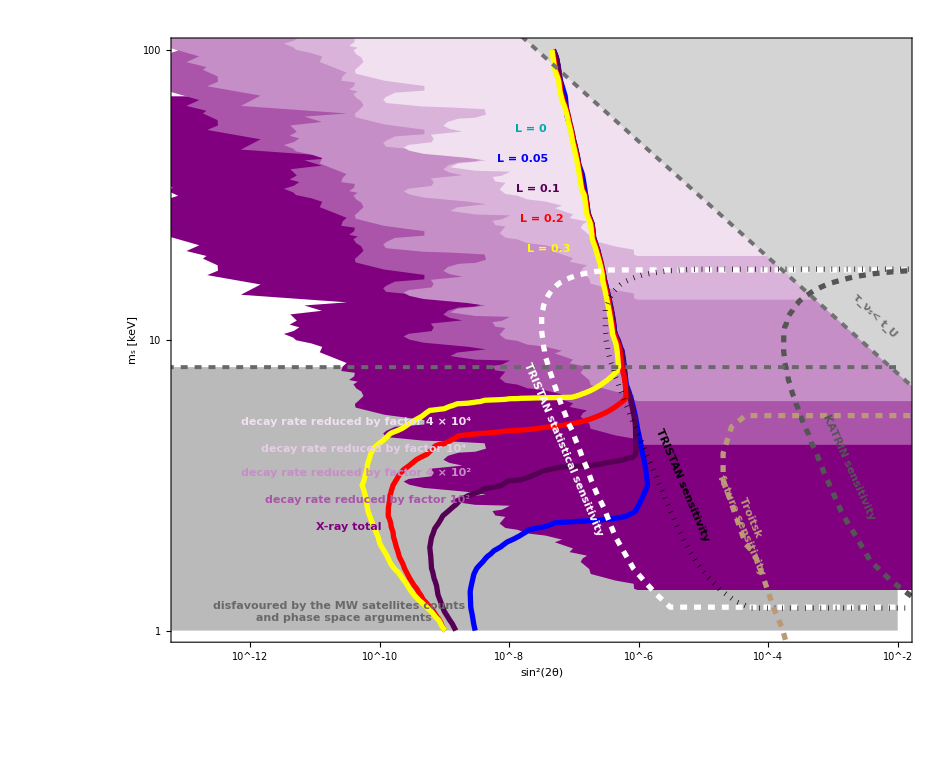

```mathematica
ShiFuller=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
(*Darker[Green],Thick,Thickness[0.003],Line[Linelist10Glog],
Darker[Cyan],Thick,Thickness[0.004],Line[LinelistSFA030MLog],
Blue,Thick,Thickness[0.003],Line[LinelistSFA00530MLog],
Darker[Purple],Thick,Thickness[0.003],Line[LinelistSFA0130MLog],
Red,Thick,Thickness[0.003],Line[LinelistSFA0230MLog],
Yellow,Thick,Thickness[0.003],Line[LinelistSFA0330MLog],*)
Blue, Thick,Thickness[0.004],Line[pointstSF005],
Darker[Purple], Line[pointstSF01],
Red, Line[pointstSF02],
Yellow, Line[pointstSF03],
(* + HUNTER lines *)
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["L = 0.3",  Italic, Bold],-0 Degree],Scaled[{0.51,0.65}]],
Red, Text[Rotate[Style["L = 0.2",  Italic, Bold],-0 Degree],Scaled[{0.5,0.7}]],
Darker[Purple], Text[Rotate[Style["L = 0.1",  Italic, Bold],-0 Degree],Scaled[{0.495,0.75}]],
Blue, Text[Rotate[Style["L = 0.05",  Italic, Bold],-0 Degree],Scaled[{0.475,0.8}]],
Darker[Cyan], Text[Rotate[Style["L = 0",  Italic, Bold],-0 Degree],Scaled[{0.485,0.85}]],

FontSize->22,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.24,0.19}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.235}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.25,0.28}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.26,0.32}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.25,0.365}]],
FontSize->18,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.23,0.05}]],
FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.69,0.26}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
(* + HUNTER labels *)
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/ShiFuller.pdf",ShiFuller];
```

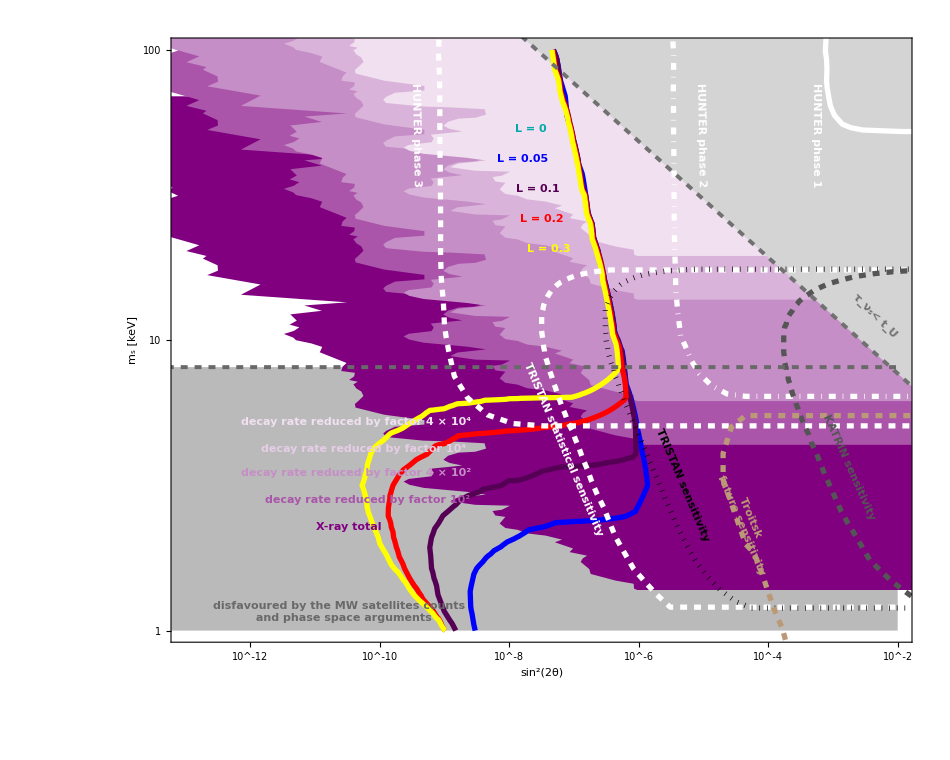

```mathematica
ShiFullerHUNTER=Plot[{},{x,-16,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
(*Darker[Green],Thick,Thickness[0.003],Line[Linelist10Glog],
Darker[Cyan],Thick,Thickness[0.004],Line[LinelistSFA030MLog],
Blue,Thick,Thickness[0.003],Line[LinelistSFA00530MLog],
Darker[Purple],Thick,Thickness[0.003],Line[LinelistSFA0130MLog],
Red,Thick,Thickness[0.003],Line[LinelistSFA0230MLog],
Yellow,Thick,Thickness[0.003],Line[LinelistSFA0330MLog],*)
Blue,Thick,Thickness[0.004], Line[pointstSF005],
Darker[Purple], Line[pointstSF01],
Red, Line[pointstSF02],
Yellow, Line[pointstSF03],
White, Thick,Thickness[0.004],Line[HUNT1Log],
White, DotDashed,Thickness[0.004],Line[HUNT2Log],
White, Dashed,Thickness[0.004],Line[HUNT3Log],
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->24,
Yellow, Text[Rotate[Style["L = 0.3",  Italic, Bold],-0 Degree],Scaled[{0.51,0.65}]],
Red, Text[Rotate[Style["L = 0.2",  Italic, Bold],-0 Degree],Scaled[{0.5,0.7}]],
Darker[Purple], Text[Rotate[Style["L = 0.1",  Italic, Bold],-0 Degree],Scaled[{0.495,0.75}]],
Blue, Text[Rotate[Style["L = 0.05",  Italic, Bold],-0 Degree],Scaled[{0.475,0.8}]],
Darker[Cyan], Text[Rotate[Style["L = 0",  Italic, Bold],-0 Degree],Scaled[{0.485,0.85}]],

FontSize->22,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.24,0.19}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.265,0.235}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.25,0.28}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.26,0.32}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.25,0.365}]],
FontSize->18,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.23,0.05}]],
FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.69,0.26}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.84}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-89 Degree],Scaled[{0.715,0.84}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-89 Degree],Scaled[{0.33,0.84}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-67 Degree],Scaled[{0.775,0.2}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/ShiFullerHUNTER.pdf",ShiFullerHUNTER];
```

## CPT violation with no T_c - special case of Shi-Fuller mechanism

We use the publicly available code called sterile-dm (https://github.com/ntveem/sterile-dm) to get the values of sterile neutrino DM corresponding to different values of the parameters m_s and sin^2(2θ). In this case, we don’t need to modify the critical temperature because the fact that sterile neutrinos only couple to neutrinos (or antineutrinos ) is enough to suppress the production, in presence of a primordial lepton asymmetry of the “right” sign.

Since KATRIN works with Tritium beta-decay, for it to be sensitive to sterile neutrino signatures we should assume that DM is constituted only by sterile antineutrinos mixed with active antineutrinos while active neutrino neutrinos do not mix with sterile neutrinos, due to CPT violation.

In case we want to investigate the potential of ECHo in this weird CPT-violation scenario we should assume that DM is constituted only by sterile neutrinos mixed with active neutrinos while active antineutrino neutrinos do not mix with sterile antineutrinos.

SInce the HUNTER experiment works with cesium-131 electron capture, to see sterile neutrino signatures in this experiment we should assume that DM is constituted only by sterile neutrinos mixed with active neutrinos while active antineutrino neutrinos do not mix with sterile antineutrinos (as for ECHo).

#### Technical comment

(Fig 6 in the paper)
Using sterile-dm in the case of no Tc
sterile-dm-master/src/derivs3.f90: change the line with the definition of vtf adding -0.68897*Gf*0.003(/0.01/0.1/0.381)*temp**2/3.15 (since it will be multiplied by p in the following an we want to introduce instead a power 3 in temperature)
and run the code with L=0, changing each time the value of the asymmetry in the modified definition of vtf

```mathematica
4*Sqrt[2]*Zeta[3]/Pi^2/3.15//N
```

0.218721

In the following, we report the data we collected with sterile-dm, to have a self consistent code with no need to run sterile-dm again every time.

### L = 0

#### data

We use the data collected running sterile-dm for zero initial lepton asymmetry and T_c = 10 GeV, but divided by 2 because we want DM constituted only by sterile antineutrinos mixed with active antineutrinos (seen by KATRIN) while due to the CPT violation active neutrinos do  not mix with sterile neutrinos.

```mathematica
ScanListCPT0t = Table[{ScanList0010G⟦i,1⟧,ScanList0010G⟦i,2⟧/2} ,{i,1,Length[ScanList0010G]}];
```

```mathematica
ScanListCPT0 = {{{1.*^-14,1.*^-6},4.323591966346868*^-9},{{1.*^-14,1.2589254117941676*^-6},6.766193626894031*^-9},{{1.*^-14,1.584893192461114*^-6},1.0492806995451636*^-8},{{1.*^-14,1.995262314968881*^-6},1.6105546883925024*^-8},{{1.*^-14,2.5118864315095823*^-6},2.4453996294527303*^-8},{{1.*^-14,3.1622776601683826*^-6},3.673424132741606*^-8},{{1.*^-14,3.981071705534978*^-6},5.4641123598738754*^-8},{{1.*^-14,5.01187233627273*^-6},8.062298891741363*^-8},{{1.*^-14,6.309573444801942*^-6},1.1827968481573402*^-7},{{1.*^-14,7.94328234724283*^-6},1.7305054792374682*^-7},{{1.*^-14,0.000010000000000000021},2.5327845718012576*^-7},{{1.*^-14,0.000012589254117941702},3.720166706749758*^-7},{{1.*^-14,0.000015848931924611172},5.496629304377796*^-7},{{1.*^-14,0.00001995262314968885},8.184308732623669*^-7},{{1.*^-14,0.000025118864315095876},1.229250071353302*^-6},{{1.*^-14,0.00003162277660168389},1.8626753721747742*^-6},{{1.*^-14,0.00003981071705534985},2.8466352863267767*^-6},{{1.*^-14,0.0000501187233627274},4.38368664602823*^-6},{{1.*^-14,0.00006309573444801955},6.7962765607993985*^-6},{{1.*^-14,0.00007943282347242846},0.000010595185694947794},{{1.*^-14,0.00010000000000000038},0.000016593544646970745},{{1.*^-14,0.00012589254117941701},0.00002607985033237929},{{1.*^-14,0.00015848931924611174},0.00004109314373865028},{{1.*^-14,0.0001995262314968885},0.00006486678209326894},{{3.1622776601683796*^-14,1.*^-6},1.3672356613830769*^-8},{{3.1622776601683796*^-14,1.2589254117941676*^-6},2.1396684718893368*^-8},{{3.1622776601683796*^-14,1.584893192461114*^-6},3.31811998243582*^-8},{{3.1622776601683796*^-14,1.995262314968881*^-6},5.093026309268632*^-8},{{3.1622776601683796*^-14,2.5118864315095823*^-6},7.733018668997845*^-8},{{3.1622776601683796*^-14,3.1622776601683826*^-6},1.1616361546377598*^-7},{{3.1622776601683796*^-14,3.981071705534978*^-6},1.7279359626579838*^-7},{{3.1622776601683796*^-14,5.01187233627273*^-6},2.5494883241387516*^-7},{{3.1622776601683796*^-14,6.309573444801942*^-6},3.740322070822595*^-7},{{3.1622776601683796*^-14,7.94328234724283*^-6},5.472348771683071*^-7},{{3.1622776601683796*^-14,0.000010000000000000021},8.009761950973181*^-7},{{3.1622776601683796*^-14,0.000012589254117941702},1.1764214770144548*^-6},{{3.1622776601683796*^-14,0.000015848931924611172},1.7381798752255864*^-6},{{3.1622776601683796*^-14,0.00001995262314968885},2.588090636603131*^-6},{{3.1622776601683796*^-14,0.000025118864315095876},3.8872004259784255*^-6},{{3.1622776601683796*^-14,0.00003162277660168389},5.890467970500587*^-6},{{3.1622776601683796*^-14,0.00003981071705534985},9.001783031116161*^-6},{{3.1622776601683796*^-14,0.0000501187233627274},0.000013862618329521303},{{3.1622776601683796*^-14,0.00006309573444801955},0.00002149181671380951},{{3.1622776601683796*^-14,0.00007943282347242846},0.000033505766947334124},{{3.1622776601683796*^-14,0.00010000000000000038},0.00005247322915789744},{{3.1622776601683796*^-14,0.00012589254117941701},0.00008246759370204904},{{3.1622776601683796*^-14,0.00015848931924611174},0.0001299476069886506},{{3.1622776601683796*^-14,0.0001995262314968885},0.00020512570069797516},{{1.*^-13,1.*^-6},4.323586222025028*^-8},{{1.*^-13,1.2589254117941676*^-6},6.766210016902724*^-8},{{1.*^-13,1.584893192461114*^-6},1.0492811637933232*^-7},{{1.*^-13,1.995262314968881*^-6},1.6105569617535453*^-7},{{1.*^-13,2.5118864315095823*^-6},2.445399854620436*^-7},{{1.*^-13,3.1622776601683826*^-6},3.67341971521048*^-7},{{1.*^-13,3.981071705534978*^-6},5.464213526337145*^-7},{{1.*^-13,5.01187233627273*^-6},8.062221126213917*^-7},{{1.*^-13,6.309573444801942*^-6},1.1828023094463691*^-6},{{1.*^-13,7.94328234724283*^-6},1.7305104323976374*^-6},{{1.*^-13,0.000010000000000000021},2.532903262566784*^-6},{{1.*^-13,0.000012589254117941702},3.7201559880546777*^-6},{{1.*^-13,0.000015848931924611172},5.496648067799525*^-6},{{1.*^-13,0.00001995262314968885},8.1840871063931*^-6},{{1.*^-13,0.000025118864315095876},0.00001229247634528965},{{1.*^-13,0.00003162277660168389},0.000018626889669825224},{{1.*^-13,0.00003981071705534985},0.00002846586563353219},{{1.*^-13,0.0000501187233627274},0.000043837294384166655},{{1.*^-13,0.00006309573444801955},0.00006796085837659221},{{1.*^-13,0.00007943282347242846},0.0001059537624820377},{{1.*^-13,0.00010000000000000038},0.00016593609112491368},{{1.*^-13,0.00012589254117941701},0.0002607887523042519},{{1.*^-13,0.00015848931924611174},0.0004109198634013556},{{1.*^-13,0.0001995262314968885},0.0006487299393953233},{{3.162277660168379*^-13,1.*^-6},1.3672411071279263*^-7},{{3.162277660168379*^-13,1.2589254117941676*^-6},2.1396633777802618*^-7},{{3.162277660168379*^-13,1.584893192461114*^-6},3.318118039498914*^-7},{{3.162277660168379*^-13,1.995262314968881*^-6},5.093026148885061*^-7},{{3.162277660168379*^-13,2.5118864315095823*^-6},7.733033660605566*^-7},{{3.162277660168379*^-13,3.1622776601683826*^-6},1.161637820010589*^-6},{{3.162277660168379*^-13,3.981071705534978*^-6},1.7279264248769355*^-6},{{3.162277660168379*^-13,5.01187233627273*^-6},2.5495218883384385*^-6},{{3.162277660168379*^-13,6.309573444801942*^-6},3.740349603495118*^-6},{{3.162277660168379*^-13,7.94328234724283*^-6},5.472338551461451*^-6},{{3.162277660168379*^-13,0.000010000000000000021},8.009795899321142*^-6},{{3.162277660168379*^-13,0.000012589254117941702},0.000011764214736514704},{{3.162277660168379*^-13,0.000015848931924611172},0.000017381684143449535},{{3.162277660168379*^-13,0.00001995262314968885},0.000025881132103661985},{{3.162277660168379*^-13,0.000025118864315095876},0.00003887164597447509},{{3.162277660168379*^-13,0.00003162277660168389},0.00005890357858303637},{{3.162277660168379*^-13,0.00003981071705534985},0.00009001606737580658},{{3.162277660168379*^-13,0.0000501187233627274},0.0001386259396189371},{{3.162277660168379*^-13,0.00006309573444801955},0.00021491717548420696},{{3.162277660168379*^-13,0.00007943282347242846},0.0003350555237827022},{{3.162277660168379*^-13,0.00010000000000000038},0.0005247374422751289},{{3.162277660168379*^-13,0.00012589254117941701},0.0008246730417597374},{{3.162277660168379*^-13,0.00015848931924611174},0.0012994475915030187},{{3.162277660168379*^-13,0.0001995262314968885},0.0020514246467302926},{{1.*^-12,1.*^-6},4.323584240754009*^-7},{{1.*^-12,1.2589254117941676*^-6},6.766236626245623*^-7},{{1.*^-12,1.584893192461114*^-6},1.0492818750746575*^-6},{{1.*^-12,1.995262314968881*^-6},1.610555593768247*^-6},{{1.*^-12,2.5118864315095823*^-6},2.4453977076276554*^-6},{{1.*^-12,3.1622776601683826*^-6},3.673418122774447*^-6},{{1.*^-12,3.981071705534978*^-6},5.464210046681918*^-6},{{1.*^-12,5.01187233627273*^-6},8.062226025624776*^-6},{{1.*^-12,6.309573444801942*^-6},0.00001182802927984116},{{1.*^-12,7.94328234724283*^-6},0.000017304966404715698},{{1.*^-12,0.000010000000000000021},0.000025328999306765228},{{1.*^-12,0.000012589254117941702},0.000037201777259368784},{{1.*^-12,0.000015848931924611172},0.00005496573050295613},{{1.*^-12,0.00001995262314968885},0.0000818434284786854},{{1.*^-12,0.000025118864315095876},0.00012292176739656105},{{1.*^-12,0.00003162277660168389},0.00018626928089928991},{{1.*^-12,0.00003981071705534985},0.00028465935073254363},{{1.*^-12,0.0000501187233627274},0.00043836946406232365},{{1.*^-12,0.00006309573444801955},0.0006796361227135467},{{1.*^-12,0.00007943282347242846},0.0010595266449714947},{{1.*^-12,0.00010000000000000038},0.0016592873647579137},{{1.*^-12,0.00012589254117941701},0.00260789439065089},{{1.*^-12,0.00015848931924611174},0.0041092750900787},{{1.*^-12,0.0001995262314968885},0.006486718682703087},{{3.1622776601683794*^-12,1.*^-6},1.3672381483760385*^-6},{{3.1622776601683794*^-12,1.2589254117941676*^-6},2.1396691540651433*^-6},{{3.1622776601683794*^-12,1.584893192461114*^-6},3.3181161828560734*^-6},{{3.1622776601683794*^-12,1.995262314968881*^-6},5.093010476257692*^-6},{{3.1622776601683794*^-12,2.5118864315095823*^-6},7.733026740495132*^-6},{{3.1622776601683794*^-12,3.1622776601683826*^-6},0.000011616394493059633},{{3.1622776601683794*^-12,3.981071705534978*^-6},0.00001727933925120705},{{3.1622776601683794*^-12,5.01187233627273*^-6},0.00002549513498341205},{{3.1622776601683794*^-12,6.309573444801942*^-6},0.00003740344441476062},{{3.1622776601683794*^-12,7.94328234724283*^-6},0.000054722965228196885},{{3.1622776601683794*^-12,0.000010000000000000021},0.0000800969875437983},{{3.1622776601683794*^-12,0.000012589254117941702},0.00011764138263206374},{{3.1622776601683794*^-12,0.000015848931924611172},0.0001738143585052098},{{3.1622776601683794*^-12,0.00001995262314968885},0.0002588089931943659},{{3.1622776601683794*^-12,0.000025118864315095876},0.00038871826721960005},{{3.1622776601683794*^-12,0.00003162277660168389},0.0005890283765255979},{{3.1622776601683794*^-12,0.00003981071705534985},0.0009001670625265532},{{3.1622776601683794*^-12,0.0000501187233627274},0.0013862412768409376},{{3.1622776601683794*^-12,0.00006309573444801955},0.002149077578676481},{{3.1622776601683794*^-12,0.00007943282347242846},0.003350446032954302},{{3.1622776601683794*^-12,0.00010000000000000038},0.005247292334968021},{{3.1622776601683794*^-12,0.00012589254117941701},0.008246695393670575},{{3.1622776601683794*^-12,0.00015848931924611174},0.012992962388398924},{{3.1622776601683794*^-12,0.0001995262314968885},0.020511412204478278},{{1.*^-11,1.*^-6},4.323583801617183*^-6},{{1.*^-11,1.2589254117941676*^-6},6.766210023326626*^-6},{{1.*^-11,1.584893192461114*^-6},0.000010492795897827055},{{1.*^-11,1.995262314968881*^-6},0.000016105485575449403},{{1.*^-11,2.5118864315095823*^-6},0.000024453904256199054},{{1.*^-11,3.1622776601683826*^-6},0.00003673412584397472},{{1.*^-11,3.981071705534978*^-6},0.0000546417057572653},{{1.*^-11,5.01187233627273*^-6},0.00008062143657223156},{{1.*^-11,6.309573444801942*^-6},0.00011827937889990066},{{1.*^-11,7.94328234724283*^-6},0.00017304758243546912},{{1.*^-11,0.000010000000000000021},0.0002532834427600002},{{1.*^-11,0.000012589254117941702},0.000372006977345794},{{1.*^-11,0.000015848931924611172},0.0005496497927835216},{{1.*^-11,0.00001995262314968885},0.000818410118944435},{{1.*^-11,0.000025118864315095876},0.0012291987326711802},{{1.*^-11,0.00003162277660168389},0.0018626303296788583},{{1.*^-11,0.00003981071705534985},0.00284648690787892},{{1.*^-11,0.0000501187233627274},0.0043833150090625},{{1.*^-11,0.00006309573444801955},0.006795598914249141},{{1.*^-11,0.00007943282347242846},0.010594326918233421},{{1.*^-11,0.00010000000000000038},0.01659123455717052},{{1.*^-11,0.00012589254117941701},0.026075621303529656},{{1.*^-11,0.00015848931924611174},0.0410850101990629},{{1.*^-11,0.0001995262314968885},0.06484720404501074},{{3.1622776601683794*^-11,1.*^-6},0.000013672350609583325},{{3.1622776601683794*^-11,1.2589254117941676*^-6},0.000021396584266041577},{{3.1622776601683794*^-11,1.584893192461114*^-6},0.00003318101244028439},{{3.1622776601683794*^-11,1.995262314968881*^-6},0.000050929754778969976},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.00007732955167217869},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.0001161620176313998},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.00017279148421415021},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.00025494653411841723},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.00037402597226897106},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.0005472174266157205},{{3.1622776601683794*^-11,0.000010000000000000021},0.0008009497696974258},{{3.1622776601683794*^-11,0.000012589254117941702},0.0011763700862990657},{{3.1622776601683794*^-11,0.000015848931924611172},0.0017380805757327093},{{3.1622776601683794*^-11,0.00001995262314968885},0.002587902314292929},{{3.1622776601683794*^-11,0.000025118864315095876},0.003886918440805057},{{3.1622776601683794*^-11,0.00003162277660168389},0.005889613032022354},{{3.1622776601683794*^-11,0.00003981071705534985},0.009000299411666775},{{3.1622776601683794*^-11,0.0000501187233627274},0.013860072691772135},{{3.1622776601683794*^-11,0.00006309573444801955},0.021486554794603423},{{3.1622776601683794*^-11,0.00007943282347242846},0.03349362141978712},{{3.1622776601683794*^-11,0.00010000000000000038},0.05245085622425918},{{3.1622776601683794*^-11,0.00012589254117941701},0.08242212822200899},{{3.1622776601683794*^-11,0.00015848931924611174},0.1298522579040408},{{3.1622776601683794*^-11,0.0001995262314968885},0.20492638683800485},{{1.*^-10,1.*^-6},0.000043235363290755994},{{1.*^-10,1.2589254117941676*^-6},0.00006766129707848905},{{1.*^-10,1.584893192461114*^-6},0.0001049263310742896},{{1.*^-10,1.995262314968881*^-6},0.00016105140569459183},{{1.*^-10,2.5118864315095823*^-6},0.00024453252699095835},{{1.*^-10,3.1622776601683826*^-6},0.0003673256137167081},{{1.*^-10,3.981071705534978*^-6},0.000546395774543866},{{1.*^-10,5.01187233627273*^-6},0.0008061822812420509},{{1.*^-10,6.309573444801942*^-6},0.0011827204902417473},{{1.*^-10,7.94328234724283*^-6},0.0017303557320674655},{{1.*^-10,0.000010000000000000021},0.0025326338757335446},{{1.*^-10,0.000012589254117941702},0.003719668437840984},{{1.*^-10,0.000015848931924611172},0.005495595512242958},{{1.*^-10,0.00001995262314968885},0.008182626433812772},{{1.*^-10,0.000025118864315095876},0.012288644678281913},{{1.*^-10,0.00003162277660168389},0.018620379786578788},{{1.*^-10,0.00003981071705534985},0.028452810987936096},{{1.*^-10,0.0000501187233627274},0.04380946228287378},{{1.*^-10,0.00006309573444801955},0.06790794547162844},{{1.*^-10,0.00007943282347242846},0.10584284363794605},{{1.*^-10,0.00010000000000000038},0.16570700536178345},{{1.*^-10,0.00012589254117941701},0.2602978455694717},{{1.*^-10,0.00015848931924611174},0.4099595857023672},{{1.*^-10,0.0001995262314968885},0.6466388976125377},{{3.1622776601683795*^-10,1.*^-6},0.00013671873177267016},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.00021395600477581544},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.00033179090214638336},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.0005092628811260771},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.0007732283621354213},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.001161500855311276},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.001727680278300487},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.002549065707906409},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.0037395408350791005},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.005470904029719147},{{3.1622776601683795*^-10,0.000010000000000000021},0.008007160319489774},{{3.1622776601683795*^-10,0.000012589254117941702},0.011759471526933064},{{3.1622776601683795*^-10,0.000015848931924611172},0.017372723350252417},{{3.1622776601683795*^-10,0.00001995262314968885},0.025863307536800495},{{3.1622776601683795*^-10,0.000025118864315095876},0.03883833725721265},{{3.1622776601683795*^-10,0.00003162277660168389},0.05883745296375328},{{3.1622776601683795*^-10,0.00003981071705534985},0.08988464698011757},{{3.1622776601683795*^-10,0.0000501187233627274},0.13835936526403594},{{3.1622776601683795*^-10,0.00006309573444801955},0.21436553698622007},{{3.1622776601683795*^-10,0.00007943282347242846},0.33393471952201215},{{3.1622776601683795*^-10,0.00010000000000000038},0.5223930178440244},{{3.1622776601683795*^-10,0.00012589254117941701},0.8199102490914852},{{3.1622776601683795*^-10,0.00015848931924611174},1.2895215468869872},{{3.1622776601683795*^-10,0.0001995262314968885},2.031191367550562},{{1.*^-9,1.*^-6},0.0004323064274405379},{{1.*^-9,1.2589254117941676*^-6},0.0006765200831092515},{{1.*^-9,1.584893192461114*^-6},0.001049049504335781},{{1.*^-9,1.995262314968881*^-6},0.0016101679061204467},{{1.*^-9,2.5118864315095823*^-6},0.0024446624272737695},{{1.*^-9,3.1622776601683826*^-6},0.0036720505082752587},{{1.*^-9,3.981071705534978*^-6},0.005461688818927892},{{1.*^-9,5.01187233627273*^-6},0.008057796014897353},{{1.*^-9,6.309573444801942*^-6},0.01181989436087851},{{1.*^-9,7.94328234724283*^-6},0.017290634366435968},{{1.*^-9,0.000010000000000000021},0.025302985042485772},{{1.*^-9,0.000012589254117941702},0.03715384863075724},{{1.*^-9,0.000015848931924611172},0.05487593956237034},{{1.*^-9,0.00001995262314968885},0.08167270536490769},{{1.*^-9,0.000025118864315095876},0.12259251201213962},{{1.*^-9,0.00003162277660168389},0.18560753534134486},{{1.*^-9,0.00003981071705534985},0.28334128820099297},{{1.*^-9,0.0000501187233627274},0.4357041807798081},{{1.*^-9,0.00006309573444801955},0.6741511321245867},{{1.*^-9,0.00007943282347242846},1.0483501432710653},{{1.*^-9,0.00010000000000000038},1.636333739591928},{{1.*^-9,0.00012589254117941701},2.5605975672352845},{{1.*^-9,0.00015848931924611174},4.011722866256201},{{1.*^-9,0.0001995262314968885},6.287307738682762},{{3.1622776601683795*^-9,1.*^-6},0.001366716616146455},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.0021386312349756255},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.003316088516527199},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.005089110178074782},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.007725666042710355},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.01160267503790984},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.01725439630437378},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.02544990880636976},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.03732282147590985},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.05457864288015979},{{3.1622776601683795*^-9,0.000010000000000000021},0.07983686694542864},{{3.1622776601683795*^-9,0.000012589254117941702},0.11716301028694254},{{3.1622776601683795*^-9,0.000015848931924611172},0.1729259559070821},{{3.1622776601683795*^-9,0.00001995262314968885},0.25710835328579973},{{3.1622776601683795*^-9,0.000025118864315095876},0.38541392006408576},{{3.1622776601683795*^-9,0.00003162277660168389},0.5825004593021557},{{3.1622776601683795*^-9,0.00003981071705534985},0.887082417363323},{{3.1622776601683795*^-9,0.0000501187233627274},1.3598175525490943},{{3.1622776601683795*^-9,0.00006309573444801955},2.095425273489807},{{3.1622776601683795*^-9,0.00007943282347242846},3.2406476993955056},{{3.1622776601683795*^-9,0.00010000000000000038},5.0225293377161035},{{3.1622776601683795*^-9,0.00012589254117941701},7.787114216518305},{{3.1622776601683795*^-9,0.00015848931924611174},12.057958478798243},{{3.1622776601683795*^-9,0.0001995262314968885},18.610356051897206},{{1.*^-8,1.*^-6},0.004318366417806915},{{1.*^-8,1.2589254117941676*^-6},0.006755885525840846},{{1.*^-8,1.584893192461114*^-6},0.010472510382010424},{{1.*^-8,1.995262314968881*^-6},0.016066476188219856},{{1.*^-8,2.5118864315095823*^-6},0.024380265341212425},{{1.*^-8,3.1622776601683826*^-6},0.036597379136775535},{{1.*^-8,3.981071705534978*^-6},0.0543918690016083},{{1.*^-8,5.01187233627273*^-6},0.0801735503117406},{{1.*^-8,6.309573444801942*^-6},0.11747665789000342},{{1.*^-8,7.94328234724283*^-6},0.17161241392451915},{{1.*^-8,0.000010000000000000021},0.25069674607256803},{{1.*^-8,0.000012589254117941702},0.3672702638800218},{{1.*^-8,0.000015848931924611172},0.5408121360099416},{{1.*^-8,0.00001995262314968885},0.8016007491877446},{{1.*^-8,0.000025118864315095876},1.1966370914490356},{{1.*^-8,0.00003162277660168389},1.7985273174304757},{{1.*^-8,0.00003981071705534985},2.718875733165235},{{1.*^-8,0.0000501187233627274},4.127243126784684},{{1.*^-8,0.00006309573444801955},6.279384023580769},{{1.*^-8,0.00007943282347242846},9.552442817449904},{{1.*^-8,0.00010000000000000038},14.491595311906227},{{1.*^-8,0.00012589254117941701},21.86802550858436},{{1.*^-8,0.00015848931924611174},32.71404442285208},{{1.*^-8,0.0001995262314968885},48.37272564205856},{{3.162277660168379*^-8,1.*^-6},0.013620599749481942},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.021293545967916185},{{3.162277660168379*^-8,1.584893192461114*^-6},0.03297888570677704},{{3.162277660168379*^-8,1.995262314968881*^-6},0.050540794879775176},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.0765952467768681},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.11480303213558794},{{3.162277660168379*^-8,3.981071705534978*^-6},0.1703141572434239},{{3.162277660168379*^-8,5.01187233627273*^-6},0.25049869099359373},{{3.162277660168379*^-8,6.309573444801942*^-6},0.36608426702747493},{{3.162277660168379*^-8,7.94328234724283*^-6},0.5330370478695935},{{3.162277660168379*^-8,0.000010000000000000021},0.775459666468962},{{3.162277660168379*^-8,0.000012589254117941702},1.1299322070918618},{{3.162277660168379*^-8,0.000015848931924611172},1.652021218895467},{{3.162277660168379*^-8,0.00001995262314968885},2.4255226360235174},{{3.162277660168379*^-8,0.000025118864315095876},3.5752380995205386},{{3.162277660168379*^-8,0.00003162277660168389},5.28475751539774},{{3.162277660168379*^-8,0.00003981071705534985},7.81572989806684},{{3.162277660168379*^-8,0.0000501187233627274},11.532867722861734},{{3.162277660168379*^-8,0.00006309573444801955},16.920194311974942},{{3.162277660168379*^-8,0.00007943282347242846},24.588108276865686},{{3.162277660168379*^-8,0.00010000000000000038},35.25163726442903},{{3.162277660168379*^-8,0.00012589254117941701},49.67135090783908},{{3.162277660168379*^-8,0.00015848931924611174},68.57392787369267},{{3.162277660168379*^-8,0.0001995262314968885},92.59208242558954},{{1.*^-7,1.*^-6},0.04272128408305228},{{1.*^-7,1.2589254117941676*^-6},0.06663792544948975},{{1.*^-7,1.584893192461114*^-6},0.10292377633313413},{{1.*^-7,1.995262314968881*^-6},0.15720691887096475},{{1.*^-7,2.5118864315095823*^-6},0.23729843234311304},{{1.*^-7,3.1622776601683826*^-6},0.35397853195397977},{{1.*^-7,3.981071705534978*^-6},0.5221946980115301},{{1.*^-7,5.01187233627273*^-6},0.7628982261783734},{{1.*^-7,6.309573444801942*^-6},1.1059265077761442},{{1.*^-7,7.94328234724283*^-6},1.5943785741170002},{{1.*^-7,0.000010000000000000021},2.290641062067423},{{1.*^-7,0.000012589254117941702},3.2845580231028038},{{1.*^-7,0.000015848931924611172},4.702969794170007},{{1.*^-7,0.00001995262314968885},6.71991007123734},{{1.*^-7,0.000025118864315095876},9.563517842329384},{{1.*^-7,0.00003162277660168389},13.516246804300078},{{1.*^-7,0.00003981071705534985},18.9021719766136},{{1.*^-7,0.0000501187233627274},26.05930530876801},{{1.*^-7,0.00006309573444801955},35.30326198217658},{{1.*^-7,0.00007943282347242846},46.916550545329066},{{1.*^-7,0.00010000000000000038},61.198720381370826},{{1.*^-7,0.00012589254117941701},78.60180266435425},{{1.*^-7,0.00015848931924611174},99.87476123197433},{{1.*^-7,0.0001995262314968885},126.1923112168442},{{3.162277660168379*^-7,1.*^-6},0.1316696054623293},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.20395590345273115},{{3.162277660168379*^-7,1.584893192461114*^-6},0.31234073894184455},{{3.162277660168379*^-7,1.995262314968881*^-6},0.4721981592250999},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.704073912519058},{{3.162277660168379*^-7,3.1622776601683826*^-6},1.0353191299948759},{{3.162277660168379*^-7,3.981071705534978*^-6},1.5018154095310259},{{3.162277660168379*^-7,5.01187233627273*^-6},2.151232980479878},{{3.162277660168379*^-7,6.309573444801942*^-6},3.046775173970831},{{3.162277660168379*^-7,7.94328234724283*^-6},4.271626393824852},{{3.162277660168379*^-7,0.000010000000000000021},5.9328813739426245},{{3.162277660168379*^-7,0.000012589254117941702},8.16147161465643},{{3.162277660168379*^-7,0.000015848931924611172},11.108468212070484},{{3.162277660168379*^-7,0.00001995262314968885},14.934146552857182},{{3.162277660168379*^-7,0.000025118864315095876},19.799194292018836},{{3.162277660168379*^-7,0.00003162277660168389},25.865108156535275},{{3.162277660168379*^-7,0.00003981071705534985},33.32915075070379},{{3.162277660168379*^-7,0.0000501187233627274},42.48302333444759},{{3.162277660168379*^-7,0.00006309573444801955},53.774626928056044},{{3.162277660168379*^-7,0.00007943282347242846},67.839220364623},{{3.162277660168379*^-7,0.00010000000000000038},85.4697050160358},{{3.162277660168379*^-7,0.00012589254117941701},107.642652266445},{{3.162277660168379*^-7,0.00015848931924611174},135.54644861870145},{{3.162277660168379*^-7,0.0001995262314968885},170.66582947744126},{{1.*^-6,1.*^-6},0.3845464282415112},{{1.*^-6,1.2589254117941676*^-6},0.5833258895398838},{{1.*^-6,1.584893192461114*^-6},0.8710815646285499},{{1.*^-6,1.995262314968881*^-6},1.278306309297463},{{1.*^-6,2.5118864315095823*^-6},1.8415288333504292},{{1.*^-6,3.1622776601683826*^-6},2.603649903245315},{{1.*^-6,3.981071705534978*^-6},3.6144952050691157},{{1.*^-6,5.01187233627273*^-6},4.931741085545154},{{1.*^-6,6.309573444801942*^-6},6.621687359126126},{{1.*^-6,7.94328234724283*^-6},8.75978760769498},{{1.*^-6,0.000010000000000000021},11.432187514584825},{{1.*^-6,0.000012589254117941702},14.742862644737965},{{1.*^-6,0.000015848931924611172},18.827856709909458},{{1.*^-6,0.00001995262314968885},23.879441543551618},{{1.*^-6,0.000025118864315095876},30.163632601589015},{{1.*^-6,0.00003162277660168389},38.02990647629631},{{1.*^-6,0.00003981071705534985},47.91105918556513},{{1.*^-6,0.0000501187233627274},60.34318120457194},{{1.*^-6,0.00006309573444801955},75.98638413242597},{{1.*^-6,0.00007943282347242846},95.67898504420451},{{1.*^-6,0.00010000000000000038},120.46593292478701},{{1.*^-6,0.00012589254117941701},151.66887919076973},{{1.*^-6,0.00015848931924611174},190.94599411911798},{{1.*^-6,0.0001995262314968885},240.39545491865536},{{3.162277660168379*^-6,1.*^-6},0.9617591785002713},{{3.162277660168379*^-6,1.2589254117941676*^-6},1.3799169996837162},{{3.162277660168379*^-6,1.584893192461114*^-6},1.9341677076347734},{{3.162277660168379*^-6,1.995262314968881*^-6},2.647821563372852},{{3.162277660168379*^-6,2.5118864315095823*^-6},3.545608808036785},{{3.162277660168379*^-6,3.1622776601683826*^-6},4.657550526160289},{{3.162277660168379*^-6,3.981071705534978*^-6},6.0254141398569985},{{3.162277660168379*^-6,5.01187233627273*^-6},7.708349775138166},{{3.162277660168379*^-6,6.309573444801942*^-6},9.788905857330256},{{3.162277660168379*^-6,7.94328234724283*^-6},12.376693109262359},{{3.162277660168379*^-6,0.000010000000000000021},15.613760744324669},{{3.162277660168379*^-6,0.000012589254117941702},19.677142515842903},{{3.162277660168379*^-6,0.000015848931924611172},24.787016916973734},{{3.162277660168379*^-6,0.00001995262314968885},31.216895157351306},{{3.162277660168379*^-6,0.000025118864315095876},39.30846769444979},{{3.162277660168379*^-6,0.00003162277660168389},49.494129652140124},{{3.162277660168379*^-6,0.00003981071705534985},62.31489226130578},{{3.162277660168379*^-6,0.0000501187233627274},78.45430728578228},{{3.162277660168379*^-6,0.00006309573444801955},98.77230149429018},{{3.162277660168379*^-6,0.00007943282347242846},124.34971867563515},{{3.162277660168379*^-6,0.00010000000000000038},156.54657387622836},{{3.162277660168379*^-6,0.00012589254117941701},197.08605699842084},{{3.162277660168379*^-6,0.00015848931924611174},248.11729130983164},{{3.162277660168379*^-6,0.0001995262314968885},312.3603035199728},{{0.00001,1.*^-6},1.6846165457879185},{{0.00001,1.2589254117941676*^-6},2.200312448253594},{{0.00001,1.584893192461114*^-6},2.826934893761491},{{0.00001,1.995262314968881*^-6},3.5943147246802813},{{0.00001,2.5118864315095823*^-6},4.544725888538741},{{0.00001,3.1622776601683826*^-6},5.73203142534261},{{0.00001,3.981071705534978*^-6},7.222776542244976},{{0.00001,5.01187233627273*^-6},9.097067436275525},{{0.00001,6.309573444801942*^-6},11.455443527138952},{{0.00001,7.94328234724283*^-6},14.42442396259979},{{0.00001,0.000010000000000000021},18.160635209358944},{{0.00001,0.000012589254117941702},22.86500582682106},{{0.00001,0.000015848931924611172},28.78662259390443},{{0.00001,0.00001995262314968885},36.239806964383234},{{0.00001,0.000025118864315095876},45.62526379122562},{{0.00001,0.00003162277660168389},57.440381908086806},{{0.00001,0.00003981071705534985},72.31466010980401},{{0.00001,0.0000501187233627274},91.03705176016175},{{0.00001,0.00006309573444801955},114.60949583940709},{{0.00001,0.00007943282347242846},144.2859891119957},{{0.00001,0.00010000000000000038},181.64564883063403},{{0.00001,0.00012589254117941701},228.68075519555677},{{0.00001,0.00015848931924611174},287.889580105665},{{0.00001,0.0001995262314968885},362.4367791123503},{{0.00003162277660168379,1.*^-6},2.000426423761344},{{0.00003162277660168379,1.2589254117941676*^-6},2.5200497859998787},{{0.00003162277660168379,1.584893192461114*^-6},3.173451123851636},{{0.00003162277660168379,1.995262314968881*^-6},3.9958725736476883},{{0.00003162277660168379,2.5118864315095823*^-6},5.031121560883174},{{0.00003162277660168379,3.1622776601683826*^-6},6.3343243734929615},{{0.00003162277660168379,3.981071705534978*^-6},7.974945929601297},{{0.00003162277660168379,5.01187233627273*^-6},10.03987817069493},{{0.00003162277660168379,6.309573444801942*^-6},12.640045673455873},{{0.00003162277660168379,7.94328234724283*^-6},15.913058049971342},{{0.00003162277660168379,0.000010000000000000021},20.03348048360612},{{0.00003162277660168379,0.000012589254117941702},25.219768392817087},{{0.00003162277660168379,0.000015848931924611172},31.75127867144531},{{0.00003162277660168379,0.00001995262314968885},39.973061834345394},{{0.00003162277660168379,0.000025118864315095876},50.322476578085606},{{0.00003162277660168379,0.00003162277660168389},63.35210865156328},{{0.00003162277660168379,0.00003981071705534985},79.7548149367257},{{0.00003162277660168379,0.0000501187233627274},100.40787522349105},{{0.00003162277660168379,0.00006309573444801955},126.40589370544386},{{0.00003162277660168379,0.00007943282347242846},159.1200623157659},{{0.00003162277660168379,0.00010000000000000038},200.341802997937},{{0.00003162277660168379,0.00012589254117941701},252.21504505600726},{{0.00003162277660168379,0.00015848931924611174},317.5175547713784},{{0.00003162277660168379,0.0001995262314968885},399.73032935065316},{{0.0001,1.*^-6},2.1845815427503323},{{0.0001,1.2589254117941676*^-6},2.7504243692093526},{{0.0001,1.584893192461114*^-6},3.46266135010377},{{0.0001,1.995262314968881*^-6},4.359237346554037},{{0.0001,2.5118864315095823*^-6},5.488079858011493},{{0.0001,3.1622776601683826*^-6},6.909177119591569},{{0.0001,3.981071705534978*^-6},8.698292368613858},{{0.0001,5.01187233627273*^-6},10.950495611053828},{{0.0001,6.309573444801942*^-6},13.786121565306217},{{0.0001,7.94328234724283*^-6},17.355846374082834},{{0.0001,0.000010000000000000021},21.849470603329426},{{0.0001,0.000012589254117941702},27.507269725228145},{{0.0001,0.000015848931924611172},34.628963580033414},{{0.0001,0.00001995262314968885},43.59604126497464},{{0.0001,0.000025118864315095876},54.88302754797436},{{0.0001,0.00003162277660168389},69.09394215718862},{{0.0001,0.00003981071705534985},86.9842617172457},{{0.0001,0.0000501187233627274},109.50530791636231},{{0.0001,0.00006309573444801955},137.86019954913684},{{0.0001,0.00007943282347242846},173.55284361783035},{{0.0001,0.00010000000000000038},218.49498724949802},{{0.0001,0.00012589254117941701},275.0750717969183},{{0.0001,0.00015848931924611174},346.28943285981165},{{0.0001,0.0001995262314968885},435.9434205801615}};
```

```mathematica
ScanCPT0= Interpolation[ScanListCPT0, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsCPTL0=Flatten[Cases[Normal@ContourPlot[ScanCPT0[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstCPTL0=Transpose[{Table[pointsCPTL0⟦i,1⟧,{i,1,Length[pointsCPTL0]}],Table[pointsCPTL0⟦i,2⟧+6,{i,1,Length[pointsCPTL0]}]}];
```

### L = 0.003

#### data

```mathematica
ScanListCPT0003 = {{{1.*^-14,1.*^-6},5.537798501325391*^-10},{{1.*^-14,1.2589254117941676*^-6},9.811825933427132*^-10},{{1.*^-14,1.584893192461114*^-6},1.741568922548923*^-9},{{1.*^-14,1.995262314968881*^-6},3.093515017663347*^-9},{{1.*^-14,2.5118864315095823*^-6},5.490609822222367*^-9},{{1.*^-14,3.1622776601683826*^-6},9.716233337521853*^-9},{{1.*^-14,3.981071705534978*^-6},1.709383981167289*^-8},{{1.*^-14,5.01187233627273*^-6},2.980265815812248*^-8},{{1.*^-14,6.309573444801942*^-6},5.133495486448749*^-8},{{1.*^-14,7.94328234724283*^-6},8.716123137364778*^-8},{{1.*^-14,0.000010000000000000021},1.4571785143964932*^-7},{{1.*^-14,0.000012589254117941702},2.3995934582824405*^-7},{{1.*^-14,0.000015848931924611172},3.8992465082154125*^-7},{{1.*^-14,0.00001995262314968885},6.271852203841488*^-7},{{1.*^-14,0.000025118864315095876},1.0026279682092514*^-6},{{1.*^-14,0.00003162277660168389},1.600020555837812*^-6},{{1.*^-14,0.00003981071705534985},2.5593610277474017*^-6},{{1.*^-14,0.0000501187233627274},4.116197936847599*^-6},{{1.*^-14,0.00006309573444801955},6.66770167624241*^-6},{{1.*^-14,0.00007943282347242846},0.000010880725770358723},{{1.*^-14,0.00010000000000000038},0.000017872148906794895},{{1.*^-14,0.00012589254117941701},0.000029499167933515116},{{1.*^-14,0.00015848931924611174},0.00004883760721043613},{{1.*^-14,0.0001995262314968885},0.0000809511412057008},{{3.1622776601683796*^-14,1.*^-6},1.751206452442126*^-9},{{3.1622776601683796*^-14,1.2589254117941676*^-6},3.1027663215029505*^-9},{{3.1622776601683796*^-14,1.584893192461114*^-6},5.507345132966887*^-9},{{3.1622776601683796*^-14,1.995262314968881*^-6},9.782539796765879*^-9},{{3.1622776601683796*^-14,2.5118864315095823*^-6},1.7362826993265793*^-8},{{3.1622776601683796*^-14,3.1622776601683826*^-6},3.072545201828902*^-8},{{3.1622776601683796*^-14,3.981071705534978*^-6},5.4055849777909877*^-8},{{3.1622776601683796*^-14,5.01187233627273*^-6},9.424435146804287*^-8},{{3.1622776601683796*^-14,6.309573444801942*^-6},1.623341011927692*^-7},{{3.1622776601683796*^-14,7.94328234724283*^-6},2.7562835147061096*^-7},{{3.1622776601683796*^-14,0.000010000000000000021},4.608008830131139*^-7},{{3.1622776601683796*^-14,0.000012589254117941702},7.588175989207*^-7},{{3.1622776601683796*^-14,0.000015848931924611172},1.233046295198248*^-6},{{3.1622776601683796*^-14,0.00001995262314968885},1.9833315464118194*^-6},{{3.1622776601683796*^-14,0.000025118864315095876},3.170565336106612*^-6},{{3.1622776601683796*^-14,0.00003162277660168389},5.059676497694977*^-6},{{3.1622776601683796*^-14,0.00003981071705534985},8.093404208052034*^-6},{{3.1622776601683796*^-14,0.0000501187233627274},0.00001301648189572152},{{3.1622776601683796*^-14,0.00006309573444801955},0.00002108487867197108},{{3.1622776601683796*^-14,0.00007943282347242846},0.000034408482399469166},{{3.1622776601683796*^-14,0.00010000000000000038},0.00005651566937727679},{{3.1622776601683796*^-14,0.00012589254117941701},0.00009328250817971172},{{3.1622776601683796*^-14,0.00015848931924611174},0.00015443111516124085},{{3.1622776601683796*^-14,0.0001995262314968885},0.0002559765812425181},{{1.*^-13,1.*^-6},5.5377693563908005*^-9},{{1.*^-13,1.2589254117941676*^-6},9.81181835202881*^-9},{{1.*^-13,1.584893192461114*^-6},1.7415660268938582*^-8},{{1.*^-13,1.995262314968881*^-6},3.0935136494427606*^-8},{{1.*^-13,2.5118864315095823*^-6},5.490612143134276*^-8},{{1.*^-13,3.1622776601683826*^-6},9.716222837788865*^-8},{{1.*^-13,3.981071705534978*^-6},1.7093940971914883*^-7},{{1.*^-13,5.01187233627273*^-6},2.9802664621188104*^-7},{{1.*^-13,6.309573444801942*^-6},5.133508364842087*^-7},{{1.*^-13,7.94328234724283*^-6},8.716120058040384*^-7},{{1.*^-13,0.000010000000000000021},1.4571830548516325*^-6},{{1.*^-13,0.000012589254117941702},2.399588180048173*^-6},{{1.*^-13,0.000015848931924611172},3.899255655908224*^-6},{{1.*^-13,0.00001995262314968885},6.271857830777332*^-6},{{1.*^-13,0.000025118864315095876},0.000010026296727247545},{{1.*^-13,0.00003162277660168389},0.00001600029032196335},{{1.*^-13,0.00003981071705534985},0.000025593551501165916},{{1.*^-13,0.0000501187233627274},0.00004116222509174334},{{1.*^-13,0.00006309573444801955},0.0000666756439236136},{{1.*^-13,0.00007943282347242846},0.00010880734796923992},{{1.*^-13,0.00010000000000000038},0.00017872146914640446},{{1.*^-13,0.00012589254117941701},0.0002949880178458331},{{1.*^-13,0.00015848931924611174},0.0004883717613396344},{{1.*^-13,0.0001995262314968885},0.0008094571343049298},{{3.162277660168379*^-13,1.*^-6},1.7512044053799174*^-8},{{3.162277660168379*^-13,1.2589254117941676*^-6},3.1027650402525256*^-8},{{3.162277660168379*^-13,1.584893192461114*^-6},5.507331921047239*^-8},{{3.162277660168379*^-13,1.995262314968881*^-6},9.782554163695227*^-8},{{3.162277660168379*^-13,2.5118864315095823*^-6},1.7362657528245033*^-7},{{3.162277660168379*^-13,3.1622776601683826*^-6},3.072522476834602*^-7},{{3.162277660168379*^-13,3.981071705534978*^-6},5.405589923326635*^-7},{{3.162277660168379*^-13,5.01187233627273*^-6},9.424462332321338*^-7},{{3.162277660168379*^-13,6.309573444801942*^-6},1.6233573724411487*^-6},{{3.162277660168379*^-13,7.94328234724283*^-6},2.7562863471546635*^-6},{{3.162277660168379*^-13,0.000010000000000000021},4.608013212203193*^-6},{{3.162277660168379*^-13,0.000012589254117941702},7.588168003914125*^-6},{{3.162277660168379*^-13,0.000015848931924611172},0.000012330439279626662},{{3.162277660168379*^-13,0.00001995262314968885},0.000019833362066762756},{{3.162277660168379*^-13,0.000025118864315095876},0.00003170578641126248},{{3.162277660168379*^-13,0.00003162277660168389},0.00005059608945185793},{{3.162277660168379*^-13,0.00003981071705534985},0.00008093335731729788},{{3.162277660168379*^-13,0.0000501187233627274},0.00013016654266772375},{{3.162277660168379*^-13,0.00006309573444801955},0.00021084862099368833},{{3.162277660168379*^-13,0.00007943282347242846},0.00034407829452637594},{{3.162277660168379*^-13,0.00010000000000000038},0.0005651651562026175},{{3.162277660168379*^-13,0.00012589254117941701},0.0009328402779376569},{{3.162277660168379*^-13,0.00015848931924611174},0.001544370215023672},{{3.162277660168379*^-13,0.0001995262314968885},0.0025597305600818074},{{1.*^-12,1.*^-6},5.5377990897263673*^-8},{{1.*^-12,1.2589254117941676*^-6},9.811822482048022*^-8},{{1.*^-12,1.584893192461114*^-6},1.741569279891333*^-7},{{1.*^-12,1.995262314968881*^-6},3.0935121841544777*^-7},{{1.*^-12,2.5118864315095823*^-6},5.490618353946404*^-7},{{1.*^-12,3.1622776601683826*^-6},9.71622934447104*^-7},{{1.*^-12,3.981071705534978*^-6},1.709385632485525*^-6},{{1.*^-12,5.01187233627273*^-6},2.9802744889215814*^-6},{{1.*^-12,6.309573444801942*^-6},5.133499632787148*^-6},{{1.*^-12,7.94328234724283*^-6},8.716135217042847*^-6},{{1.*^-12,0.000010000000000000021},0.000014571814430810335},{{1.*^-12,0.000012589254117941702},0.00002399582246465582},{{1.*^-12,0.000015848931924611172},0.00003899233267114469},{{1.*^-12,0.00001995262314968885},0.00006271854493189784},{{1.*^-12,0.000025118864315095876},0.0001002628138007278},{{1.*^-12,0.00003162277660168389},0.0001600007573757613},{{1.*^-12,0.00003981071705534985},0.00025593503856230406},{{1.*^-12,0.0000501187233627274},0.00041162003750597653},{{1.*^-12,0.00006309573444801955},0.0006667591566977491},{{1.*^-12,0.00007943282347242846},0.001088081040479209},{{1.*^-12,0.00010000000000000038},0.001787177559784221},{{1.*^-12,0.00012589254117941701},0.002949897271049542},{{1.*^-12,0.00015848931924611174},0.004883498835612167},{{1.*^-12,0.0001995262314968885},0.008094562295680244},{{3.1622776601683794*^-12,1.*^-6},1.7512060553910343*^-7},{{3.1622776601683794*^-12,1.2589254117941676*^-6},3.1027663875091607*^-7},{{3.1622776601683794*^-12,1.584893192461114*^-6},5.507330548094328*^-7},{{3.1622776601683794*^-12,1.995262314968881*^-6},9.782550830060138*^-7},{{3.1622776601683794*^-12,2.5118864315095823*^-6},1.736286384009914*^-6},{{3.1622776601683794*^-12,3.1622776601683826*^-6},3.072544947751694*^-6},{{3.1622776601683794*^-12,3.981071705534978*^-6},5.405587912432297*^-6},{{3.1622776601683794*^-12,5.01187233627273*^-6},9.424436180857002*^-6},{{3.1622776601683794*^-12,6.309573444801942*^-6},0.000016233556401275048},{{3.1622776601683794*^-12,7.94328234724283*^-6},0.000027562814470643762},{{3.1622776601683794*^-12,0.000010000000000000021},0.00004608010307427127},{{3.1622776601683794*^-12,0.000012589254117941702},0.00007588146193476832},{{3.1622776601683794*^-12,0.000015848931924611172},0.00012330447196610324},{{3.1622776601683794*^-12,0.00001995262314968885},0.00019833284870974285},{{3.1622776601683794*^-12,0.000025118864315095876},0.00031705175655647025},{{3.1622776601683794*^-12,0.00003162277660168389},0.0005059701549743337},{{3.1622776601683794*^-12,0.00003981071705534985},0.0008093164723920035},{{3.1622776601683794*^-12,0.0000501187233627274},0.0013016509779454034},{{3.1622776601683794*^-12,0.00006309573444801955},0.0021084678834756756},{{3.1622776601683794*^-12,0.00007943282347242846},0.0034407797340956486},{{3.1622776601683794*^-12,0.00010000000000000038},0.005651609501678111},{{3.1622776601683794*^-12,0.00012589254117941701},0.009328390884344936},{{3.1622776601683794*^-12,0.00015848931924611174},0.015442954152677978},{{3.1622776601683794*^-12,0.0001995262314968885},0.02559577472192837},{{1.*^-11,1.*^-6},5.537797143457555*^-7},{{1.*^-11,1.2589254117941676*^-6},9.811800166673901*^-7},{{1.*^-11,1.584893192461114*^-6},1.741570060415096*^-6},{{1.*^-11,1.995262314968881*^-6},3.0935133107582058*^-6},{{1.*^-11,2.5118864315095823*^-6},5.490609816975108*^-6},{{1.*^-11,3.1622776601683826*^-6},9.716235532062444*^-6},{{1.*^-11,3.981071705534978*^-6},0.000017094013703133774},{{1.*^-11,5.01187233627273*^-6},0.000029802692771540394},{{1.*^-11,6.309573444801942*^-6},0.000051334958164909394},{{1.*^-11,7.94328234724283*^-6},0.00008716096049145972},{{1.*^-11,0.000010000000000000021},0.00014571804797232547},{{1.*^-11,0.000012589254117941702},0.0002399579837891469},{{1.*^-11,0.000015848931924611172},0.0003899229688542871},{{1.*^-11,0.00001995262314968885},0.0006271801152205468},{{1.*^-11,0.000025118864315095876},0.0010026180760809938},{{1.*^-11,0.00003162277660168389},0.001600002839099728},{{1.*^-11,0.00003981071705534985},0.0025593098557163533},{{1.*^-11,0.0000501187233627274},0.0041161283553510395},{{1.*^-11,0.00006309573444801955},0.006667355341182213},{{1.*^-11,0.00007943282347242846},0.0108804520590695},{{1.*^-11,0.00010000000000000038},0.017871025296997144},{{1.*^-11,0.00012589254117941701},0.029495902163214086},{{1.*^-11,0.00015848931924611174},0.048830423991629235},{{1.*^-11,0.0001995262314968885},0.08093175779659616},{{3.1622776601683794*^-11,1.*^-6},1.7512069894730905*^-6},{{3.1622776601683794*^-11,1.2589254117941676*^-6},3.1027651599320925*^-6},{{3.1622776601683794*^-11,1.584893192461114*^-6},5.507325331501162*^-6},{{3.1622776601683794*^-11,1.995262314968881*^-6},9.782519105818966*^-6},{{3.1622776601683794*^-11,2.5118864315095823*^-6},0.000017362861663372748},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.00003072539422928729},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.00005405581581324884},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.00009424410522830136},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.0001623348429516784},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.00027562622703781976},{{3.1622776601683794*^-11,0.000010000000000000021},0.0004607983241154905},{{3.1622776601683794*^-11,0.000012589254117941702},0.0007588071995633319},{{3.1622776601683794*^-11,0.000015848931924611172},0.0012330310027527012},{{3.1622776601683794*^-11,0.00001995262314968885},0.001983286272112482},{{3.1622776601683794*^-11,0.000025118864315095876},0.00317047736981936},{{3.1622776601683794*^-11,0.00003162277660168389},0.005059527451594094},{{3.1622776601683794*^-11,0.00003981071705534985},0.0080929620629881},{{3.1622776601683794*^-11,0.0000501187233627274},0.013015665814705236},{{3.1622776601683794*^-11,0.00006309573444801955},0.021082198416419517},{{3.1622776601683794*^-11,0.00007943282347242846},0.03440349853022195},{{3.1622776601683794*^-11,0.00010000000000000038},0.056504047649415814},{{3.1622776601683794*^-11,0.00012589254117941701},0.09325798508674267},{{3.1622776601683794*^-11,0.00015848931924611174},0.15436649480922432},{{3.1622776601683794*^-11,0.0001995262314968885},0.2558260714620737},{{1.*^-10,1.*^-6},5.53777377810916*^-6},{{1.*^-10,1.2589254117941676*^-6},9.811795631908635*^-6},{{1.*^-10,1.584893192461114*^-6},0.000017415696274537648},{{1.*^-10,1.995262314968881*^-6},0.000030935075644776577},{{1.*^-10,2.5118864315095823*^-6},0.00005490597022402659},{{1.*^-10,3.1622776601683826*^-6},0.00009716196459013192},{{1.*^-10,3.981071705534978*^-6},0.00017093836537252898},{{1.*^-10,5.01187233627273*^-6},0.0002980244531993964},{{1.*^-10,6.309573444801942*^-6},0.0005133414633263694},{{1.*^-10,7.94328234724283*^-6},0.0008715973454583285},{{1.*^-10,0.000010000000000000021},0.0014571515606366277},{{1.*^-10,0.000012589254117941702},0.002399517277015635},{{1.*^-10,0.000015848931924611172},0.003899077318235423},{{1.*^-10,0.00001995262314968885},0.006271196676565435},{{1.*^-10,0.000025118864315095876},0.010025479398343461},{{1.*^-10,0.00003162277660168389},0.0159983650921412},{{1.*^-10,0.00003981071705534985},0.025589451500324763},{{1.*^-10,0.0000501187233627274},0.041153278532829324},{{1.*^-10,0.00006309573444801955},0.06665435843653571},{{1.*^-10,0.00007943282347242846},0.1087564677562487},{{1.*^-10,0.00010000000000000038},0.17860071138514313},{{1.*^-10,0.00012589254117941701},0.29472113242653397},{{1.*^-10,0.00015848931924611174},0.487726376859967},{{1.*^-10,0.0001995262314968885},0.807961578934244},{{3.1622776601683795*^-10,1.*^-6},0.000017512034604499368},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.000031027561989554156},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.00005507309498932536},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.00009782478363203816},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.00017362658514174747},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.0003072507090428598},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.0005405479683863251},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.0009424189788462353},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.0016232964644298322},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.0027561365127300374},{{3.1622776601683795*^-10,0.000010000000000000021},0.004607690592125482},{{3.1622776601683795*^-10,0.000012589254117941702},0.007587446285249699},{{3.1622776601683795*^-10,0.000015848931924611172},0.01232879667245532},{{3.1622776601683795*^-10,0.00001995262314968885},0.019829671662994996},{{3.1622776601683795*^-10,0.000025118864315095876},0.03169745122505999},{{3.1622776601683795*^-10,0.00003162277660168389},0.05057935617069966},{{3.1622776601683795*^-10,0.00003981071705534985},0.08089243924498678},{{3.1622776601683795*^-10,0.0000501187233627274},0.13007079039519115},{{3.1622776601683795*^-10,0.00006309573444801955},0.2106286243147141},{{3.1622776601683795*^-10,0.00007943282347242846},0.3435755695641677},{{3.1622776601683795*^-10,0.00010000000000000038},0.5639715449964449},{{3.1622776601683795*^-10,0.00012589254117941701},0.9300878796028422},{{3.1622776601683795*^-10,0.00015848931924611174},1.5378495601624371},{{3.1622776601683795*^-10,0.0001995262314968885},2.54499208023192},{{1.*^-9,1.*^-6},0.00005537758684917608},{{1.*^-9,1.2589254117941676*^-6},0.00009811707932563692},{{1.*^-9,1.584893192461114*^-6},0.0001741546016291589},{{1.*^-9,1.995262314968881*^-6},0.0003093453819283973},{{1.*^-9,2.5118864315095823*^-6},0.0005490421492303217},{{1.*^-9,3.1622776601683826*^-6},0.0009715840701186872},{{1.*^-9,3.981071705534978*^-6},0.001709297992169973},{{1.*^-9,5.01187233627273*^-6},0.002980024092272723},{{1.*^-9,6.309573444801942*^-6},0.0051328981488101555},{{1.*^-9,7.94328234724283*^-6},0.00871470060818064},{{1.*^-9,0.000010000000000000021},0.01456852923986894},{{1.*^-9,0.000012589254117941702},0.02398840165705645},{{1.*^-9,0.000015848931924611172},0.038975875974061394},{{1.*^-9,0.00001995262314968885},0.06268189420799501},{{1.*^-9,0.000025118864315095876},0.10018155779579237},{{1.*^-9,0.00003162277660168389},0.15982244932674491},{{1.*^-9,0.00003981071705534985},0.2555258446490759},{{1.*^-9,0.0000501187233627274},0.4106882273755273},{{1.*^-9,0.00006309573444801955},0.6645864018922567},{{1.*^-9,0.00007943282347242846},1.0830199914572267},{{1.*^-9,0.00010000000000000038},1.7753409724328293},{{1.*^-9,0.00012589254117941701},2.9223190402961166},{{1.*^-9,0.00015848931924611174},4.819495982198087},{{1.*^-9,0.0001995262314968885},7.946941996435991},{{3.1622776601683795*^-9,1.*^-6},0.00017511657849405678},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.00031026760440789},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.0005507092782151243},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.0009781933994114967},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.0017361258381541297},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.0030721503502403194},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.005404589896701423},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.009421979861833654},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.016227549293342983},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.027548612945482973},{{3.1622776601683795*^-9,0.000010000000000000021},0.04604718386655987},{{3.1622776601683795*^-9,0.000012589254117941702},0.07580684483179707},{{3.1622776601683795*^-9,0.000015848931924611172},0.12313910891161381},{{3.1622776601683795*^-9,0.00001995262314968885},0.19796652397238057},{{3.1622776601683795*^-9,0.000025118864315095876},0.3162502401969001},{{3.1622776601683795*^-9,0.00003162277660168389},0.5041681248148315},{{3.1622776601683795*^-9,0.00003981071705534985},0.8052714898547183},{{3.1622776601683795*^-9,0.0000501187233627274},1.292327521532201},{{3.1622776601683795*^-9,0.00006309573444801955},2.0869410487632876},{{3.1622776601683795*^-9,0.00007943282347242846},3.3905849451994547},{{3.1622776601683795*^-9,0.00010000000000000038},5.534523062778294},{{3.1622776601683795*^-9,0.00012589254117941701},9.056283908538553},{{3.1622776601683795*^-9,0.00015848931924611174},14.815190380506019},{{3.1622776601683795*^-9,0.0001995262314968885},24.16296166840183},{{1.*^-8,1.*^-6},0.0005537403464797614},{{1.*^-8,1.2589254117941676*^-6},0.0009810836387310685},{{1.*^-8,1.584893192461114*^-6},0.0017413097011699551},{{1.*^-8,1.995262314968881*^-6},0.0030929009772557724},{{1.*^-8,2.5118864315095823*^-6},0.005489050115159635},{{1.*^-8,3.1622776601683826*^-6},0.009712287472289761},{{1.*^-8,3.981071705534978*^-6},0.01708397715926389},{{1.*^-8,5.01187233627273*^-6},0.029777918825572208},{{1.*^-8,6.309573444801942*^-6},0.051274999672401365},{{1.*^-8,7.94328234724283*^-6},0.0870189453623771},{{1.*^-8,0.000010000000000000021},0.14538913521563276},{{1.*^-8,0.000012589254117941702},0.23921534452669158},{{1.*^-8,0.000015848931924611172},0.3882708565280484},{{1.*^-8,0.00001995262314968885},0.6235381579201126},{{1.*^-8,0.000025118864315095876},0.9945787020685004},{{1.*^-8,0.00003162277660168389},1.5821349986335078},{{1.*^-8,0.00003981071705534985},2.519017694281332},{{1.*^-8,0.0000501187233627274},4.0242557588903605},{{1.*^-8,0.00006309573444801955},6.4559594191784395},{{1.*^-8,0.00007943282347242846},10.39108183481811},{{1.*^-8,0.00010000000000000038},16.741390238020827},{{1.*^-8,0.00012589254117941701},26.905771665470702},{{1.*^-8,0.00015848931924611174},42.95796953827405},{{1.*^-8,0.0001995262314968885},67.82875045790755},{{3.162277660168379*^-8,1.*^-6},0.0017508160854343398},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.0031018039497017267},{{3.162277660168379*^-8,1.584893192461114*^-6},0.005504902087596979},{{3.162277660168379*^-8,1.995262314968881*^-6},0.009776396989066826},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.01734719236456657},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.030685834517260382},{{3.162277660168379*^-8,3.981071705534978*^-6},0.05395643105868617},{{3.162277660168379*^-8,5.01187233627273*^-6},0.09399752400749188},{{3.162277660168379*^-8,6.309573444801942*^-6},0.16173637854341727},{{3.162277660168379*^-8,7.94328234724283*^-6},0.2742084375100844},{{3.162277660168379*^-8,0.000010000000000000021},0.45752374136381474},{{3.162277660168379*^-8,0.000012589254117941702},0.7514170345436771},{{3.162277660168379*^-8,0.000015848931924611172},1.216624489954901},{{3.162277660168379*^-8,0.00001995262314968885},1.9472007671639053},{{3.162277660168379*^-8,0.000025118864315095876},3.091217877027876},{{3.162277660168379*^-8,0.00003162277660168389},4.884162808619671},{{3.162277660168379*^-8,0.00003981071705534985},7.701332487925135},{{3.162277660168379*^-8,0.0000501187233627274},12.13225293643947},{{3.162277660168379*^-8,0.00006309573444801955},19.082365357895252},{{3.162277660168379*^-8,0.00007943282347242846},29.876753095773733},{{3.162277660168379*^-8,0.00010000000000000038},46.35380898565435},{{3.162277660168379*^-8,0.00012589254117941701},70.85007190590493},{{3.162277660168379*^-8,0.00015848931924611174},106.00417054607654},{{3.162277660168379*^-8,0.0001995262314968885},154.31758587880984},{{1.*^-7,1.*^-6},0.005533902660711344},{{1.*^-7,1.2589254117941676*^-6},0.00980213653563706},{{1.*^-7,1.584893192461114*^-6},0.017391465964830932},{{1.*^-7,1.995262314968881*^-6},0.030873757108630096},{{1.*^-7,2.5118864315095823*^-6},0.05475023453692807},{{1.*^-7,3.1622776601683826*^-6},0.09676719098292949},{{1.*^-7,3.981071705534978*^-6},0.16994690241945226},{{1.*^-7,5.01187233627273*^-6},0.2955695901880548},{{1.*^-7,6.309573444801942*^-6},0.5073928344826589},{{1.*^-7,7.94328234724283*^-6},0.8575405825927391},{{1.*^-7,0.000010000000000000021},1.4247571651611588},{{1.*^-7,0.000012589254117941702},2.3267361330090015},{{1.*^-7,0.000015848931924611172},3.738520938820867},{{1.*^-7,0.00001995262314968885},5.921454674642539},{{1.*^-7,0.000025118864315095876},9.265719591624233},{{1.*^-7,0.00003162277660168389},14.347441879862373},{{1.*^-7,0.00003981071705534985},21.991569403926988},{{1.*^-7,0.0000501187233627274},33.31169878335704},{{1.*^-7,0.00006309573444801955},49.674298072212544},{{1.*^-7,0.00007943282347242846},72.52859039047526},{{1.*^-7,0.00010000000000000038},103.08610570960941},{{1.*^-7,0.00012589254117941701},142.05164310125346},{{1.*^-7,0.00015848931924611174},189.69964867990544},{{1.*^-7,0.0001995262314968885},246.68357322818164},{{3.162277660168379*^-7,1.*^-6},0.017473206899151907},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.030931384165472958},{{3.162277660168379*^-7,1.584893192461114*^-6},0.054831525787044214},{{3.162277660168379*^-7,1.995262314968881*^-6},0.09721377298024324},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.17207687549844525},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.30332884855176834},{{3.162277660168379*^-7,3.981071705534978*^-6},0.5307194970493646},{{3.162277660168379*^-7,5.01187233627273*^-6},0.9181818724673727},{{3.162277660168379*^-7,6.309573444801942*^-6},1.564876886064042},{{3.162277660168379*^-7,7.94328234724283*^-6},2.619062158687375},{{3.162277660168379*^-7,0.000010000000000000021},4.295116662808215},{{3.162277660168379*^-7,0.000012589254117941702},6.8939911431395124},{{3.162277660168379*^-7,0.000015848931924611172},10.826867744640408},{{3.162277660168379*^-7,0.00001995262314968885},16.637033797920513},{{3.162277660168379*^-7,0.000025118864315095876},25.006852788162348},{{3.162277660168379*^-7,0.00003162277660168389},36.722458294271604},{{3.162277660168379*^-7,0.00003981071705534985},52.56871301277023},{{3.162277660168379*^-7,0.0000501187233627274},73.16638297366146},{{3.162277660168379*^-7,0.00006309573444801955},98.8995024395628},{{3.162277660168379*^-7,0.00007943282347242846},130.10360531509593},{{3.162277660168379*^-7,0.00010000000000000038},167.60124781351286},{{3.162277660168379*^-7,0.00012589254117941701},213.18847377733644},{{3.162277660168379*^-7,0.00015848931924611174},269.5966207124898},{{3.162277660168379*^-7,0.0001995262314968885},340.18641883215497},{{1.*^-6,1.*^-6},0.05499120570058512},{{1.*^-6,1.2589254117941676*^-6},0.0971604183526375},{{1.*^-6,1.584893192461114*^-6},0.17175799097436306},{{1.*^-6,1.995262314968881*^-6},0.30329819359811644},{{1.*^-6,2.5118864315095823*^-6},0.5337663658404823},{{1.*^-6,3.1622776601683826*^-6},0.9331480297402656},{{1.*^-6,3.981071705534978*^-6},1.6137714588753902},{{1.*^-6,5.01187233627273*^-6},2.7471938714613278},{{1.*^-6,6.309573444801942*^-6},4.5804787156395355},{{1.*^-6,7.94328234724283*^-6},7.445896744064628},{{1.*^-6,0.000010000000000000021},11.757038376271908},{{1.*^-6,0.000012589254117941702},17.983187562599916},{{1.*^-6,0.000015848931924611172},26.598217676438324},{{1.*^-6,0.00001995262314968885},38.01099448636684},{{1.*^-6,0.000025118864315095876},52.51803066357859},{{1.*^-6,0.00003162277660168389},70.35440979655712},{{1.*^-6,0.00003981071705534985},91.90369033955159},{{1.*^-6,0.0000501187233627274},117.9924351680461},{{1.*^-6,0.00006309573444801955},150.01505320960635},{{1.*^-6,0.00007943282347242846},189.85053959626683},{{1.*^-6,0.00010000000000000038},239.7428774795597},{{1.*^-6,0.00012589254117941701},302.3975360909268},{{1.*^-6,0.00015848931924611174},381.14443376123586},{{1.*^-6,0.0001995262314968885},480.20075653194004},{{3.162277660168379*^-6,1.*^-6},0.1713034153253036},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.30086434271898643},{{3.162277660168379*^-6,1.584893192461114*^-6},0.5272918018119817},{{3.162277660168379*^-6,1.995262314968881*^-6},0.9196244621673828},{{3.162277660168379*^-6,2.5118864315095823*^-6},1.5899587520175218},{{3.162277660168379*^-6,3.1622776601683826*^-6},2.7108725881866684},{{3.162277660168379*^-6,3.981071705534978*^-6},4.528513256484783},{{3.162277660168379*^-6,5.01187233627273*^-6},7.357342193405075},{{3.162277660168379*^-6,6.309573444801942*^-6},11.542824612021729},{{3.162277660168379*^-6,7.94328234724283*^-6},17.390182788105204},{{3.162277660168379*^-6,0.000010000000000000021},25.091169809283052},{{3.162277660168379*^-6,0.000012589254117941702},34.718365038816664},{{3.162277660168379*^-6,0.000015848931924611172},46.34707336507629},{{3.162277660168379*^-6,0.00001995262314968885},60.26528905068804},{{3.162277660168379*^-6,0.000025118864315095876},77.1167376155927},{{3.162277660168379*^-6,0.00003162277660168389},97.89324706605078},{{3.162277660168379*^-6,0.00003981071705534985},123.79530786334149},{{3.162277660168379*^-6,0.0000501187233627274},156.26006408472756},{{3.162277660168379*^-6,0.00006309573444801955},197.03496205251002},{{3.162277660168379*^-6,0.00007943282347242846},248.29370326774867},{{3.162277660168379*^-6,0.00010000000000000038},312.7827101640961},{{3.162277660168379*^-6,0.00012589254117941701},393.9172734202357},{{3.162277660168379*^-6,0.00015848931924611174},496.041410633708},{{3.162277660168379*^-6,0.0001995262314968885},624.5720045721447},{{0.00001,1.*^-6},0.5170853476776246},{{0.00001,1.2589254117941676*^-6},0.8918115568539094},{{0.00001,1.584893192461114*^-6},1.522945159944941},{{0.00001,1.995262314968881*^-6},2.5604982691400453},{{0.00001,2.5118864315095823*^-6},4.2072157041216505},{{0.00001,3.1622776601683826*^-6},6.696487134350766},{{0.00001,3.981071705534978*^-6},10.231120563035011},{{0.00001,5.01187233627273*^-6},14.903384710632555},{{0.00001,6.309573444801942*^-6},20.67553126684954},{{0.00001,7.94328234724283*^-6},27.505121237359337},{{0.00001,0.000010000000000000021},35.54979509448904},{{0.00001,0.000012589254117941702},45.25158187684598},{{0.00001,0.000015848931924611172},57.23865673047856},{{0.00001,0.00001995262314968885},72.2311574545152},{{0.00001,0.000025118864315095876},91.05658693361987},{{0.00001,0.00003162277660168389},114.727519941194},{{0.00001,0.00003981071705534985},144.50730738984035},{{0.00001,0.0000501187233627274},181.96398296526846},{{0.00001,0.00006309573444801955},229.14725315396458},{{0.00001,0.00007943282347242846},288.5004661324938},{{0.00001,0.00010000000000000038},363.242982598416},{{0.00001,0.00012589254117941701},457.3194121612844},{{0.00001,0.00015848931924611174},575.7462878608109},{{0.00001,0.0001995262314968885},724.8452508150332},{{0.00003162277660168379,1.*^-6},1.4238960872466535},{{0.00003162277660168379,1.2589254117941676*^-6},2.3330375515599577},{{0.00003162277660168379,1.584893192461114*^-6},3.7142196461728063},{{0.00003162277660168379,1.995262314968881*^-6},5.690955900299493},{{0.00003162277660168379,2.5118864315095823*^-6},8.321116335076495},{{0.00003162277660168379,3.1622776601683826*^-6},11.567835768003615},{{0.00003162277660168379,3.981071705534978*^-6},15.369464393588448},{{0.00003162277660168379,5.01187233627273*^-6},19.796163286175528},{{0.00003162277660168379,6.309573444801942*^-6},25.117050950647556},{{0.00003162277660168379,7.94328234724283*^-6},31.709696751105252},{{0.00003162277660168379,0.000010000000000000021},39.97639397831463},{{0.00003162277660168379,0.000012589254117941702},50.37060936427899},{{0.00003162277660168379,0.000015848931924611172},63.44645640586719},{{0.00003162277660168379,0.00001995262314968885},79.9014629103309},{{0.00003162277660168379,0.000025118864315095876},100.61002451419257},{{0.00003162277660168379,0.00003162277660168389},126.67216636035299},{{0.00003162277660168379,0.00003981071705534985},159.49114631043128},{{0.00003162277660168379,0.0000501187233627274},200.79890764187107},{{0.00003162277660168379,0.00006309573444801955},252.79732484052002},{{0.00003162277660168379,0.00007943282347242846},318.2474996502453},{{0.00003162277660168379,0.00010000000000000038},400.67459166802234},{{0.00003162277660168379,0.00012589254117941701},504.422115349219},{{0.00003162277660168379,0.00015848931924611174},635.036427513383},{{0.00003162277660168379,0.0001995262314968885},799.4557084974531},{{0.0001,1.*^-6},3.1102689713341105},{{0.0001,1.2589254117941676*^-6},4.544858347740963},{{0.0001,1.584893192461114*^-6},6.323124597292129},{{0.0001,1.995262314968881*^-6},8.407804204723877},{{0.0001,2.5118864315095823*^-6},10.829099805012374},{{0.0001,3.1622776601683826*^-6},13.733535667254415},{{0.0001,3.981071705534978*^-6},17.3335545875906},{{0.0001,5.01187233627273*^-6},21.851214973656052},{{0.0001,6.309573444801942*^-6},27.532619682252935},{{0.0001,7.94328234724283*^-6},34.67963426453434},{{0.0001,0.000010000000000000021},43.673460091928995},{{0.0001,0.000012589254117941702},54.994674401830444},{{0.0001,0.000015848931924611172},69.24301151998831},{{0.0001,0.00001995262314968885},87.17971112433062},{{0.0001,0.000025118864315095876},109.75563348472812},{{0.0001,0.00003162277660168389},138.17992216765597},{{0.0001,0.00003981071705534985},173.96496248370224},{{0.0001,0.0000501187233627274},219.00630924499836},{{0.0001,0.00006309573444801955},275.7111704712559},{{0.0001,0.00007943282347242846},347.1066332932772},{{0.0001,0.00010000000000000038},436.98447474772183},{{0.0001,0.00012589254117941701},550.1431899930187},{{0.0001,0.00015848931924611174},692.5716743872207},{{0.0001,0.0001995262314968885},871.9255384437122}};
```

```mathematica
ScanCPT0003= Interpolation[ScanListCPT0003, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsCPTL0003=Flatten[Cases[Normal@ContourPlot[ScanCPT0003[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstCPTL0003=Transpose[{Table[pointsCPTL0003⟦i,1⟧,{i,1,Length[pointsCPTL0003]}],Table[pointsCPTL0003⟦i,2⟧+6,{i,1,Length[pointsCPTL0003]}]}];
```

### L = 0.01

#### data

```mathematica
ScanListCPT001 = {{{1.*^-14,1.*^-6},2.302736405671487*^-10},{{1.*^-14,1.2589254117941676*^-6},4.0504002159313886*^-10},{{1.*^-14,1.584893192461114*^-6},7.149443672489949*^-10},{{1.*^-14,1.995262314968881*^-6},1.2659509768694717*^-9},{{1.*^-14,2.5118864315095823*^-6},2.247188692200221*^-9},{{1.*^-14,3.1622776601683826*^-6},3.995338912755056*^-9},{{1.*^-14,3.981071705534978*^-6},7.106109537067913*^-9},{{1.*^-14,5.01187233627273*^-6},1.262138912878179*^-8},{{1.*^-14,6.309573444801942*^-6},2.2330672491206*^-8},{{1.*^-14,7.94328234724283*^-6},3.923713548575008*^-8},{{1.*^-14,0.000010000000000000021},6.825178269605076*^-8},{{1.*^-14,0.000012589254117941702},1.1721407029672012*^-7},{{1.*^-14,0.000015848931924611172},1.9841565167623362*^-7},{{1.*^-14,0.00001995262314968885},3.309696439531959*^-7},{{1.*^-14,0.000025118864315095876},5.447295019047679*^-7},{{1.*^-14,0.00003162277660168389},8.871240506463768*^-7},{{1.*^-14,0.00003981071705534985},1.4352545271462203*^-6},{{1.*^-14,0.0000501187233627274},2.3176763702137487*^-6},{{1.*^-14,0.00006309573444801955},3.752992506330415*^-6},{{1.*^-14,0.00007943282347242846},6.117175206197591*^-6},{{1.*^-14,0.00010000000000000038},0.000010060239369388953},{{1.*^-14,0.00012589254117941701},0.00001670506408928354},{{1.*^-14,0.00015848931924611174},0.000027983887042033366},{{1.*^-14,0.0001995262314968885},0.000047207175310937165},{{3.1622776601683796*^-14,1.*^-6},7.281889594792342*^-10},{{3.1622776601683796*^-14,1.2589254117941676*^-6},1.280849614741903*^-9},{{3.1622776601683796*^-14,1.584893192461114*^-6},2.2608335143646566*^-9},{{3.1622776601683796*^-14,1.995262314968881*^-6},4.003284233783325*^-9},{{3.1622776601683796*^-14,2.5118864315095823*^-6},7.106219817026799*^-9},{{3.1622776601683796*^-14,3.1622776601683826*^-6},1.263438314101747*^-8},{{3.1622776601683796*^-14,3.981071705534978*^-6},2.2471509994944448*^-8},{{3.1622776601683796*^-14,5.01187233627273*^-6},3.991237196280708*^-8},{{3.1622776601683796*^-14,6.309573444801942*^-6},7.061515994240397*^-8},{{3.1622776601683796*^-14,7.94328234724283*^-6},1.2407822972561249*^-7},{{3.1622776601683796*^-14,0.000010000000000000021},2.1583086091252185*^-7},{{3.1622776601683796*^-14,0.000012589254117941702},3.7066414881204204*^-7},{{3.1622776601683796*^-14,0.000015848931924611172},6.274460512518661*^-7},{{3.1622776601683796*^-14,0.00001995262314968885},1.0466189893398237*^-6},{{3.1622776601683796*^-14,0.000025118864315095876},1.7226048785405306*^-6},{{3.1622776601683796*^-14,0.00003162277660168389},2.8053415479822026*^-6},{{3.1622776601683796*^-14,0.00003981071705534985},4.538672891105516*^-6},{{3.1622776601683796*^-14,0.0000501187233627274},7.329142311902925*^-6},{{3.1622776601683796*^-14,0.00006309573444801955},0.000011867844344789595},{{3.1622776601683796*^-14,0.00007943282347242846},0.00001934412123880576},{{3.1622776601683796*^-14,0.00010000000000000038},0.0000318135144254691},{{3.1622776601683796*^-14,0.00012589254117941701},0.000052825298326476176},{{3.1622776601683796*^-14,0.00015848931924611174},0.00008849274063010077},{{3.1622776601683796*^-14,0.0001995262314968885},0.00014928310077808217},{{1.*^-13,1.*^-6},2.3027426050799*^-9},{{1.*^-13,1.2589254117941676*^-6},4.050398940078796*^-9},{{1.*^-13,1.584893192461114*^-6},7.1494359653526145*^-9},{{1.*^-13,1.995262314968881*^-6},1.2659498152375464*^-8},{{1.*^-13,2.5118864315095823*^-6},2.2471907100287293*^-8},{{1.*^-13,3.1622776601683826*^-6},3.9953134577483046*^-8},{{1.*^-13,3.981071705534978*^-6},7.106130119223234*^-8},{{1.*^-13,5.01187233627273*^-6},1.262140957716698*^-7},{{1.*^-13,6.309573444801942*^-6},2.233015717916847*^-7},{{1.*^-13,7.94328234724283*^-6},3.9236975684352223*^-7},{{1.*^-13,0.000010000000000000021},6.825152799203526*^-7},{{1.*^-13,0.000012589254117941702},1.1721416447279105*^-6},{{1.*^-13,0.000015848931924611172},1.9841629920082937*^-6},{{1.*^-13,0.00001995262314968885},3.3096938945331042*^-6},{{1.*^-13,0.000025118864315095876},5.447332572624649*^-6},{{1.*^-13,0.00003162277660168389},8.871264954814115*^-6},{{1.*^-13,0.00003981071705534985},0.000014351806674421826},{{1.*^-13,0.0000501187233627274},0.000023176754669830028},{{1.*^-13,0.00006309573444801955},0.00003752969781479503},{{1.*^-13,0.00007943282347242846},0.00006117195415730123},{{1.*^-13,0.00010000000000000038},0.00010060404420867244},{{1.*^-13,0.00012589254117941701},0.00016705137490669346},{{1.*^-13,0.00015848931924611174},0.00027983214996113817},{{1.*^-13,0.0001995262314968885},0.00047207921896940807},{{3.162277660168379*^-13,1.*^-6},7.281895741145628*^-9},{{3.162277660168379*^-13,1.2589254117941676*^-6},1.2808509395903864*^-8},{{3.162277660168379*^-13,1.584893192461114*^-6},2.2608509213506784*^-8},{{3.162277660168379*^-13,1.995262314968881*^-6},4.0032915495398536*^-8},{{3.162277660168379*^-13,2.5118864315095823*^-6},7.106232738233593*^-8},{{3.162277660168379*^-13,3.1622776601683826*^-6},1.2634219975273363*^-7},{{3.162277660168379*^-13,3.981071705534978*^-6},2.2471560606660364*^-7},{{3.162277660168379*^-13,5.01187233627273*^-6},3.9912349527169663*^-7},{{3.162277660168379*^-13,6.309573444801942*^-6},7.06157592009915*^-7},{{3.162277660168379*^-13,7.94328234724283*^-6},1.2407794129340826*^-6},{{3.162277660168379*^-13,0.000010000000000000021},2.158285231607392*^-6},{{3.162277660168379*^-13,0.000012589254117941702},3.706629448170971*^-6},{{3.162277660168379*^-13,0.000015848931924611172},6.274450356300055*^-6},{{3.162277660168379*^-13,0.00001995262314968885},0.000010466189036440074},{{3.162277660168379*^-13,0.000025118864315095876},0.00001722605327936836},{{3.162277660168379*^-13,0.00003162277660168389},0.000028053448276144897},{{3.162277660168379*^-13,0.00003981071705534985},0.000045386580017766945},{{3.162277660168379*^-13,0.0000501187233627274},0.00007329032582143606},{{3.162277660168379*^-13,0.00006309573444801955},0.00011867882562199893},{{3.162277660168379*^-13,0.00007943282347242846},0.00019344438424498967},{{3.162277660168379*^-13,0.00010000000000000038},0.00031813945269689147},{{3.162277660168379*^-13,0.00012589254117941701},0.0005282556457369056},{{3.162277660168379*^-13,0.00015848931924611174},0.0008849136311585975},{{3.162277660168379*^-13,0.0001995262314968885},0.0014928431952035983},{{1.*^-12,1.*^-6},2.3027394030900935*^-8},{{1.*^-12,1.2589254117941676*^-6},4.050403497112438*^-8},{{1.*^-12,1.584893192461114*^-6},7.149439909304831*^-8},{{1.*^-12,1.995262314968881*^-6},1.265951386073087*^-7},{{1.*^-12,2.5118864315095823*^-6},2.2471889419981844*^-7},{{1.*^-12,3.1622776601683826*^-6},3.9953413918005603*^-7},{{1.*^-12,3.981071705534978*^-6},7.106099209452267*^-7},{{1.*^-12,5.01187233627273*^-6},1.2621374220746121*^-6},{{1.*^-12,6.309573444801942*^-6},2.2330662322419407*^-6},{{1.*^-12,7.94328234724283*^-6},3.923708701018277*^-6},{{1.*^-12,0.000010000000000000021},6.825175705935465*^-6},{{1.*^-12,0.000012589254117941702},0.000011721435953625364},{{1.*^-12,0.000015848931924611172},0.000019841534560401775},{{1.*^-12,0.00001995262314968885},0.000033097004310967793},{{1.*^-12,0.000025118864315095876},0.00005447356971355189},{{1.*^-12,0.00003162277660168389},0.00008871230879394332},{{1.*^-12,0.00003981071705534985},0.00014352474240597918},{{1.*^-12,0.0000501187233627274},0.0002317667513389045},{{1.*^-12,0.00006309573444801955},0.0003752924625851344},{{1.*^-12,0.00007943282347242846},0.0006117255046029325},{{1.*^-12,0.00010000000000000038},0.0010059966594611457},{{1.*^-12,0.00012589254117941701},0.0016704719665828409},{{1.*^-12,0.00015848931924611174},0.002798343794685283},{{1.*^-12,0.0001995262314968885},0.00472066533495662},{{3.1622776601683794*^-12,1.*^-6},7.281901410712212*^-8},{{3.1622776601683794*^-12,1.2589254117941676*^-6},1.280847756446797*^-7},{{3.1622776601683794*^-12,1.584893192461114*^-6},2.2608505763890353*^-7},{{3.1622776601683794*^-12,1.995262314968881*^-6},4.0032856005608396*^-7},{{3.1622776601683794*^-12,2.5118864315095823*^-6},7.106239258170385*^-7},{{3.1622776601683794*^-12,3.1622776601683826*^-6},1.263440249979244*^-6},{{3.1622776601683794*^-12,3.981071705534978*^-6},2.2471557726622806*^-6},{{3.1622776601683794*^-12,5.01187233627273*^-6},3.99123682603129*^-6},{{3.1622776601683794*^-12,6.309573444801942*^-6},7.0615655525380665*^-6},{{3.1622776601683794*^-12,7.94328234724283*^-6},0.000012407857518041348},{{3.1622776601683794*^-12,0.000010000000000000021},0.00002158304927061742},{{3.1622776601683794*^-12,0.000012589254117941702},0.00003706636476848879},{{3.1622776601683794*^-12,0.000015848931924611172},0.00006274456494143392},{{3.1622776601683794*^-12,0.00001995262314968885},0.00010466199991240042},{{3.1622776601683794*^-12,0.000025118864315095876},0.00017226026027354372},{{3.1622776601683794*^-12,0.00003162277660168389},0.0002805341901068783},{{3.1622776601683794*^-12,0.00003981071705534985},0.0004538665894567775},{{3.1622776601683794*^-12,0.0000501187233627274},0.000732915145350056},{{3.1622776601683794*^-12,0.00006309573444801955},0.0011867835972272601},{{3.1622776601683794*^-12,0.00007943282347242846},0.0019344377077467733},{{3.1622776601683794*^-12,0.00010000000000000038},0.0031813659861087674},{{3.1622776601683794*^-12,0.00012589254117941701},0.005282492016911286},{{3.1622776601683794*^-12,0.00015848931924611174},0.008849043526675354},{{3.1622776601683794*^-12,0.0001995262314968885},0.014927852175224096},{{1.*^-11,1.*^-6},2.3027374318703052*^-7},{{1.*^-11,1.2589254117941676*^-6},4.05040201330811*^-7},{{1.*^-11,1.584893192461114*^-6},7.149382298121064*^-7},{{1.*^-11,1.995262314968881*^-6},1.2659504859128846*^-6},{{1.*^-11,2.5118864315095823*^-6},2.247187710271788*^-6},{{1.*^-11,3.1622776601683826*^-6},3.995335595972044*^-6},{{1.*^-11,3.981071705534978*^-6},7.106127083049549*^-6},{{1.*^-11,5.01187233627273*^-6},0.000012621264448903427},{{1.*^-11,6.309573444801942*^-6},0.000022330632410717054},{{1.*^-11,7.94328234724283*^-6},0.00003923698447685009},{{1.*^-11,0.000010000000000000021},0.00006825146625875302},{{1.*^-11,0.000012589254117941702},0.00011721366241565097},{{1.*^-11,0.000015848931924611172},0.0001984149559644581},{{1.*^-11,0.00001995262314968885},0.00033097038163062715},{{1.*^-11,0.000025118864315095876},0.0005447320437624758},{{1.*^-11,0.00003162277660168389},0.0008871177180744101},{{1.*^-11,0.00003981071705534985},0.0014352404880746926},{{1.*^-11,0.0000501187233627274},0.002317655411798781},{{1.*^-11,0.00006309573444801955},0.0037529069026146877},{{1.*^-11,0.00007943282347242846},0.006117146377198063},{{1.*^-11,0.00010000000000000038},0.010059908826010535},{{1.*^-11,0.00012589254117941701},0.01670417573975419},{{1.*^-11,0.00015848931924611174},0.0279819908388791},{{1.*^-11,0.0001995262314968885},0.047202411851063754},{{3.1622776601683794*^-11,1.*^-6},7.281889487644152*^-7},{{3.1622776601683794*^-11,1.2589254117941676*^-6},1.2808484742239485*^-6},{{3.1622776601683794*^-11,1.584893192461114*^-6},2.2608494889245313*^-6},{{3.1622776601683794*^-11,1.995262314968881*^-6},4.003235345896085*^-6},{{3.1622776601683794*^-11,2.5118864315095823*^-6},7.106232741249565*^-6},{{3.1622776601683794*^-11,3.1622776601683826*^-6},0.00001263438148276442},{{3.1622776601683794*^-11,3.981071705534978*^-6},0.00002247155776843025},{{3.1622776601683794*^-11,5.01187233627273*^-6},0.00003991227314136116},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.00007061564906569483},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.00012407794370562517},{{3.1622776601683794*^-11,0.000010000000000000021},0.00021582788758361132},{{3.1622776601683794*^-11,0.000012589254117941702},0.0003706526444416665},{{3.1622776601683794*^-11,0.000015848931924611172},0.0006274404007899727},{{3.1622776601683794*^-11,0.00001995262314968885},0.001046605972532281},{{3.1622776601683794*^-11,0.000025118864315095876},0.0017225869940362952},{{3.1622776601683794*^-11,0.00003162277660168389},0.002805295383655516},{{3.1622776601683794*^-11,0.00003981071705534985},0.004538534972005445},{{3.1622776601683794*^-11,0.0000501187233627274},0.007328859875918585},{{3.1622776601683794*^-11,0.00006309573444801955},0.011867472563823308},{{3.1622776601683794*^-11,0.00007943282347242846},0.019343118375387696},{{3.1622776601683794*^-11,0.00010000000000000038},0.03181041351542737},{{3.1622776601683794*^-11,0.00012589254117941701},0.0528181003289052},{{3.1622776601683794*^-11,0.00015848931924611174},0.08847340782447873},{{3.1622776601683794*^-11,0.0001995262314968885},0.14923533448037105},{{1.*^-10,1.*^-6},2.3027371353129907*^-6},{{1.*^-10,1.2589254117941676*^-6},4.050400251080165*^-6},{{1.*^-10,1.584893192461114*^-6},7.149428561228764*^-6},{{1.*^-10,1.995262314968881*^-6},0.00001265950454150352},{{1.*^-10,2.5118864315095823*^-6},0.000022471876739663002},{{1.*^-10,3.1622776601683826*^-6},0.00003995331074602863},{{1.*^-10,3.981071705534978*^-6},0.00007106118093739476},{{1.*^-10,5.01187233627273*^-6},0.0001262135264702497},{{1.*^-10,6.309573444801942*^-6},0.00022330547302247433},{{1.*^-10,7.94328234724283*^-6},0.00039236526025699037},{{1.*^-10,0.000010000000000000021},0.0006825085624017501},{{1.*^-10,0.000012589254117941702},0.0011721263692086553},{{1.*^-10,0.000015848931924611172},0.0019841181352716706},{{1.*^-10,0.00001995262314968885},0.0033096119148945734},{{1.*^-10,0.000025118864315095876},0.0054471443144679865},{{1.*^-10,0.00003162277660168389},0.008870800267717876},{{1.*^-10,0.00003981071705534985},0.014351189677365766},{{1.*^-10,0.0000501187233627274},0.023174270319993095},{{1.*^-10,0.00006309573444801955},0.03752425183521913},{{1.*^-10,0.00007943282347242846},0.06115883642807629},{{1.*^-10,0.00010000000000000038},0.10057227011479417},{{1.*^-10,0.00012589254117941701},0.16697401763747888},{{1.*^-10,0.00015848931924611174},0.27964882039737227},{{1.*^-10,0.0001995262314968885},0.47161273825064237},{{3.1622776601683795*^-10,1.*^-6},7.281889652524048*^-6},{{3.1622776601683795*^-10,1.2589254117941676*^-6},0.000012808373997264629},{{3.1622776601683795*^-10,1.584893192461114*^-6},0.000022608473659916808},{{3.1622776601683795*^-10,1.995262314968881*^-6},0.00004003278415180436},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.00007106198680319549},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.00012634328227423042},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.00022471436493677873},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.00039911959610030337},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.0007061468164509283},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.0012407578765666347},{{3.1622776601683795*^-10,0.000010000000000000021},0.002158235780729962},{{3.1622776601683795*^-10,0.000012589254117941702},0.003706472038180118},{{3.1622776601683795*^-10,0.000015848931924611172},0.006274072700559918},{{3.1622776601683795*^-10,0.00001995262314968885},0.010465287715833096},{{3.1622776601683795*^-10,0.000025118864315095876},0.017224080625666792},{{3.1622776601683795*^-10,0.00003162277660168389},0.028048952321565252},{{3.1622776601683795*^-10,0.00003981071705534985},0.04537617530422143},{{3.1622776601683795*^-10,0.0000501187233627274},0.07326794681150471},{{3.1622776601683795*^-10,0.00006309573444801955},0.1186243940742674},{{3.1622776601683795*^-10,0.00007943282347242846},0.19331160615900142},{{3.1622776601683795*^-10,0.00010000000000000038},0.31781986212105723},{{3.1622776601683795*^-10,0.00012589254117941701},0.5274846867900153},{{3.1622776601683795*^-10,0.00015848931924611174},0.8830227598355178},{{3.1622776601683795*^-10,0.0001995262314968885},1.4881773154208258},{{1.*^-9,1.*^-6},0.00002302715448239122},{{1.*^-9,1.2589254117941676*^-6},0.0000405038354488606},{{1.*^-9,1.584893192461114*^-6},0.00007149389390247579},{{1.*^-9,1.995262314968881*^-6},0.00012659370912594445},{{1.*^-9,2.5118864315095823*^-6},0.0002247158039659741},{{1.*^-9,3.1622776601683826*^-6},0.0003995277372683139},{{1.*^-9,3.981071705534978*^-6},0.0007105975261136339},{{1.*^-9,5.01187233627273*^-6},0.0012620969062637863},{{1.*^-9,6.309573444801942*^-6},0.0022329609266300175},{{1.*^-9,7.94328234724283*^-6},0.003923428638290423},{{1.*^-9,0.000010000000000000021},0.006824480348920071},{{1.*^-9,0.000012589254117941702},0.011719819825467083},{{1.*^-9,0.000015848931924611172},0.019837780810561673},{{1.*^-9,0.00001995262314968885},0.03308826977329511},{{1.*^-9,0.000025118864315095876},0.05445362080948284},{{1.*^-9,0.00003162277660168389},0.08866713606243752},{{1.*^-9,0.00003981071705534985},0.1434222710250415},{{1.*^-9,0.0000501187233627274},0.23151916587443414},{{1.*^-9,0.00006309573444801955},0.3747468543350316},{{1.*^-9,0.00007943282347242846},0.6104139651743858},{{1.*^-9,0.00010000000000000038},1.002857048238972},{{1.*^-9,0.00012589254117941701},1.662775824554975},{{1.*^-9,0.00015848931924611174},2.7794622265088536},{{1.*^-9,0.0001995262314968885},4.674361071269659},{{3.1622776601683795*^-9,1.*^-6},0.00007281823374559218},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.00012808323284301798},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.00022608083041537262},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.0004003181451417638},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.0007105974111540004},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.001263374393159056},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.0022469919081133305},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.0039908169652168755},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.007060510619701798},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.012405165701709051},{{3.1622776601683795*^-9,0.000010000000000000021},0.02157639892826611},{{3.1622776601683795*^-9,0.000012589254117941702},0.03705037417500989},{{3.1622776601683795*^-9,0.000015848931924611172},0.06270642931404798},{{3.1622776601683795*^-9,0.00001995262314968885},0.10457388315496045},{{3.1622776601683795*^-9,0.000025118864315095876},0.17205996433041412},{{3.1622776601683795*^-9,0.00003162277660168389},0.28007931858295465},{{3.1622776601683795*^-9,0.00003981071705534985},0.452837735344094},{{3.1622776601683795*^-9,0.0000501187233627274},0.730547294017418},{{3.1622776601683795*^-9,0.00006309573444801955},1.1812952156085021},{{3.1622776601683795*^-9,0.00007943282347242846},1.9213643270374832},{{3.1622776601683795*^-9,0.00010000000000000038},3.149949253235103},{{3.1622776601683795*^-9,0.00012589254117941701},5.205976895028868},{{3.1622776601683795*^-9,0.00015848931924611174},8.6621572663946},{{3.1622776601683795*^-9,0.0001995262314968885},14.472275398140235},{{1.*^-8,1.*^-6},0.0002302666211177589},{{1.*^-8,1.2589254117941676*^-6},0.00040502343144714945},{{1.*^-8,1.584893192461114*^-6},0.0007149024785164406},{{1.*^-8,1.995262314968881*^-6},0.0012658482801807143},{{1.*^-8,2.5118864315095823*^-6},0.0022469321360727153},{{1.*^-8,3.1622776601683826*^-6},0.003994695529537315},{{1.*^-8,3.981071705534978*^-6},0.007104498201268046},{{1.*^-8,5.01187233627273*^-6},0.012617212456558013},{{1.*^-8,6.309573444801942*^-6},0.0223198533780898},{{1.*^-8,7.94328234724283*^-6},0.03921023336392622},{{1.*^-8,0.000010000000000000021},0.06818540621445199},{{1.*^-8,0.000012589254117941702},0.1170538494532605},{{1.*^-8,0.000015848931924611172},0.19803658902993163},{{1.*^-8,0.00001995262314968885},0.33009107877988647},{{1.*^-8,0.000025118864315095876},0.5427316187648223},{{1.*^-8,0.00003162277660168389},0.8825978101942349},{{1.*^-8,0.00003981071705534985},1.424996732075919},{{1.*^-8,0.0000501187233627274},2.2942062988878242},{{1.*^-8,0.00006309573444801955},3.6984538445299},{{1.*^-8,0.00007943282347242846},5.9883300501696155},{{1.*^-8,0.00010000000000000038},9.751472310042569},{{1.*^-8,0.00012589254117941701},15.959258530191674},{{1.*^-8,0.00015848931924611174},26.182229119539656},{{1.*^-8,0.0001995262314968885},42.88137994773072},{{3.162277660168379*^-8,1.*^-6},0.0007281172282046979},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.0012806770548303684},{{3.162277660168379*^-8,1.584893192461114*^-6},0.0022604350837793544},{{3.162277660168379*^-8,1.995262314968881*^-6},0.004002264709180028},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.007103676458388631},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.012627934208120247},{{3.162277660168379*^-8,3.981071705534978*^-6},0.02245513104539923},{{3.162277660168379*^-8,5.01187233627273*^-6},0.03987044406475439},{{3.162277660168379*^-8,6.309573444801942*^-6},0.0705089470136396},{{3.162277660168379*^-8,7.94328234724283*^-6},0.12381114824163447},{{3.162277660168379*^-8,0.000010000000000000021},0.21517031855848537},{{3.162277660168379*^-8,0.000012589254117941702},0.36906494939761714},{{3.162277660168379*^-8,0.000015848931924611172},0.6236640221682044},{{3.162277660168379*^-8,0.00001995262314968885},1.0378668306072352},{{3.162277660168379*^-8,0.000025118864315095876},1.702693288160826},{{3.162277660168379*^-8,0.00003162277660168389},2.7603117725198483},{{3.162277660168379*^-8,0.00003981071705534985},4.437392783270034},{{3.162277660168379*^-8,0.0000501187233627274},7.0987629488638335},{{3.162277660168379*^-8,0.00006309573444801955},11.336771796390659},{{3.162277660168379*^-8,0.00007943282347242846},18.103914685673477},{{3.162277660168379*^-8,0.00010000000000000038},28.892206864691826},{{3.162277660168379*^-8,0.00012589254117941701},45.939261586686136},{{3.162277660168379*^-8,0.00015848931924611174},72.38185121542938},{{3.162277660168379*^-8,0.0001995262314968885},112.21211926314609},{{1.*^-7,1.*^-6},0.00230201074196439},{{1.*^-7,1.2589254117941676*^-6},0.004048686874948382},{{1.*^-7,1.584893192461114*^-6},0.007145294075067575},{{1.*^-7,1.995262314968881*^-6},0.012649141392368552},{{1.*^-7,2.5118864315095823*^-6},0.022446355674419986},{{1.*^-7,3.1622776601683826*^-6},0.03988897391212727},{{1.*^-7,3.981071705534978*^-6},0.0708971146154481},{{1.*^-7,5.01187233627273*^-6},0.12579597123416378},{{1.*^-7,6.309573444801942*^-6},0.2222457988624554},{{1.*^-7,7.94328234724283*^-6},0.3897078461303116},{{1.*^-7,0.000010000000000000021},0.6759436816118488},{{1.*^-7,0.000012589254117941702},1.1562645339141202},{{1.*^-7,0.000015848931924611172},1.946707430283305},{{1.*^-7,0.00001995262314968885},3.2233752605633166},{{1.*^-7,0.000025118864315095876},5.252015329243402},{{1.*^-7,0.00003162277660168389},8.434261518748999},{{1.*^-7,0.00003981071705534985},13.37813860833541},{{1.*^-7,0.0000501187233627274},20.99793650033278},{{1.*^-7,0.00006309573444801955},32.62999177411398},{{1.*^-7,0.00007943282347242846},50.121681811703375},{{1.*^-7,0.00010000000000000038},75.78439260311434},{{1.*^-7,0.00012589254117941701},112.0898690738138},{{1.*^-7,0.00015848931924611174},161.04661782574107},{{1.*^-7,0.0001995262314968885},223.6166266964026},{{3.162277660168379*^-7,1.*^-6},0.007274620457599929},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.012791348080175083},{{3.162277660168379*^-7,1.584893192461114*^-6},0.022567098908720187},{{3.162277660168379*^-7,1.995262314968881*^-6},0.03993109625184007},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.07080796764399383},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.12570148452960858},{{3.162277660168379*^-7,3.981071705534978*^-6},0.22308307998837248},{{3.162277660168379*^-7,5.01187233627273*^-6},0.39496898631339766},{{3.162277660168379*^-7,6.309573444801942*^-6},0.6956357705518851},{{3.162277660168379*^-7,7.94328234724283*^-6},1.2144467551747598},{{3.162277660168379*^-7,0.000010000000000000021},2.093574994366625},{{3.162277660168379*^-7,0.000012589254117941702},3.5512283186548266},{{3.162277660168379*^-7,0.000015848931924611172},5.911053616300317},{{3.162277660168379*^-7,0.00001995262314968885},9.638390419046496},{{3.162277660168379*^-7,0.000025118864315095876},15.383748737246291},{{3.162277660168379*^-7,0.00003162277660168389},24.02689108007854},{{3.162277660168379*^-7,0.00003981071705534985},36.705848993354834},{{3.162277660168379*^-7,0.0000501187233627274},54.76809436548988},{{3.162277660168379*^-7,0.00006309573444801955},79.61510163886318},{{3.162277660168379*^-7,0.00007943282347242846},112.37529501738133},{{3.162277660168379*^-7,0.00010000000000000038},153.68932510480693},{{3.162277660168379*^-7,0.00012589254117941701},203.93515362395271},{{3.162277660168379*^-7,0.00015848931924611174},264.1281744733852},{{3.162277660168379*^-7,0.0001995262314968885},336.8952895938764},{{1.*^-6,1.*^-6},0.022954812913980348},{{1.*^-6,1.2589254117941676*^-6},0.040332969832329674},{{1.*^-6,1.584893192461114*^-6},0.07108220724952061},{{1.*^-6,1.995262314968881*^-6},0.12558232212780282},{{1.*^-6,2.5118864315095823*^-6},0.22219283499339487},{{1.*^-6,3.1622776601683826*^-6},0.3931685162137293},{{1.*^-6,3.981071705534978*^-6},0.6944841517573619},{{1.*^-6,5.01187233627273*^-6},1.2212862764096475},{{1.*^-6,6.309573444801942*^-6},2.1303226574111447},{{1.*^-6,7.94328234724283*^-6},3.669005292959739},{{1.*^-6,0.000010000000000000021},6.207572771945656},{{1.*^-6,0.000012589254117941702},10.266118175566115},{{1.*^-6,0.000015848931924611172},16.52368747622961},{{1.*^-6,0.00001995262314968885},25.79302646254916},{{1.*^-6,0.000025118864315095876},38.94497735822018},{{1.*^-6,0.00003162277660168389},56.778890341042754},{{1.*^-6,0.00003981071705534985},79.88665157554928},{{1.*^-6,0.0000501187233627274},108.64468473780572},{{1.*^-6,0.00006309573444801955},143.50248969424806},{{1.*^-6,0.00007943282347242846},185.51606326588737},{{1.*^-6,0.00010000000000000038},236.73506606584158},{{1.*^-6,0.00012589254117941701},300.1369363551589},{{1.*^-6,0.00015848931924611174},379.3903453327697},{{1.*^-6,0.0001995262314968885},478.80887689382695},{{3.162277660168379*^-6,1.*^-6},0.07209875265531078},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.12639087718093533},{{3.162277660168379*^-6,1.584893192461114*^-6},0.22201185086275074},{{3.162277660168379*^-6,1.995262314968881*^-6},0.3903535642846702},{{3.162277660168379*^-6,2.5118864315095823*^-6},0.6858611767699597},{{3.162277660168379*^-6,3.1622776601683826*^-6},1.201466079475292},{{3.162277660168379*^-6,3.981071705534978*^-6},2.0917183897490603},{{3.162277660168379*^-6,5.01187233627273*^-6},3.603229261102835},{{3.162277660168379*^-6,6.309573444801942*^-6},6.105559735593447},{{3.162277660168379*^-6,7.94328234724283*^-6},10.104655608738213},{{3.162277660168379*^-6,0.000010000000000000021},16.210926365488167},{{3.162277660168379*^-6,0.000012589254117941702},25.03896041846402},{{3.162277660168379*^-6,0.000015848931924611172},37.058891062737544},{{3.162277660168379*^-6,0.00001995262314968885},52.49556373842878},{{3.162277660168379*^-6,0.000025118864315095876},71.41860179004271},{{3.162277660168379*^-6,0.00003162277660168389},94.08105909735848},{{3.162277660168379*^-6,0.00003981071705534985},121.291678011123},{{3.162277660168379*^-6,0.0000501187233627274},154.52724290687613},{{3.162277660168379*^-6,0.00006309573444801955},195.7577995810579},{{3.162277660168379*^-6,0.00007943282347242846},247.32022471329128},{{3.162277660168379*^-6,0.00010000000000000038},312.02412397019594},{{3.162277660168379*^-6,0.00012589254117941701},393.32672537450674},{{3.162277660168379*^-6,0.00015848931924611174},495.5676322574481},{{3.162277660168379*^-6,0.0001995262314968885},624.1911730145126},{{0.00001,1.*^-6},0.22323631428092675},{{0.00001,1.2589254117941676*^-6},0.38856191543431257},{{0.00001,1.584893192461114*^-6},0.6755856422689811},{{0.00001,1.995262314968881*^-6},1.1705330431086862},{{0.00001,2.5118864315095823*^-6},2.0137274751993908},{{0.00001,3.1622776601683826*^-6},3.4231422084959413},{{0.00001,3.981071705534978*^-6},5.712984907063534},{{0.00001,5.01187233627273*^-6},9.284766140903582},{{0.00001,6.309573444801942*^-6},14.557696137711767},{{0.00001,7.94328234724283*^-6},21.830415821359953},{{0.00001,0.000010000000000000021},31.157174337113236},{{0.00001,0.000012589254117941702},42.41661823722262},{{0.00001,0.000015848931924611172},55.64181111674441},{{0.00001,0.00001995262314968885},71.34579067232232},{{0.00001,0.000025118864315095876},90.50562369871108},{{0.00001,0.00003162277660168389},114.33608307054696},{{0.00001,0.00003981071705534985},144.21254671271245},{{0.00001,0.0000501187233627274},181.75150325508108},{{0.00001,0.00006309573444801955},228.96851634006728},{{0.00001,0.00007943282347242846},288.36033661391446},{{0.00001,0.00010000000000000038},363.1239658308979},{{0.00001,0.00012589254117941701},457.22196937809014},{{0.00001,0.00015848931924611174},575.6823053865288},{{0.00001,0.0001995262314968885},724.7892147537234},{{0.00003162277660168379,1.*^-6},0.6622881233081577},{{0.00003162277660168379,1.2589254117941676*^-6},1.128647674952569},{{0.00003162277660168379,1.584893192461114*^-6},1.904508965430886},{{0.00003162277660168379,1.995262314968881*^-6},3.163500090115784},{{0.00003162277660168379,2.5118864315095823*^-6},5.132802309346107},{{0.00003162277660168379,3.1622776601683826*^-6},8.06078150287409},{{0.00003162277660168379,3.981071705534978*^-6},12.135578039433621},{{0.00003162277660168379,5.01187233627273*^-6},17.389885512715267},{{0.00003162277660168379,6.309573444801942*^-6},23.70720041260471},{{0.00003162277660168379,7.94328234724283*^-6},31.0386314556555},{{0.00003162277660168379,0.000010000000000000021},39.66526709162304},{{0.00003162277660168379,0.000012589254117941702},50.18569697850636},{{0.00003162277660168379,0.000015848931924611172},63.31037117032339},{{0.00003162277660168379,0.00001995262314968885},79.79345696540707},{{0.00003162277660168379,0.000025118864315095876},100.52536842549503},{{0.00003162277660168379,0.00003162277660168389},126.6086905536141},{{0.00003162277660168379,0.00003981071705534985},159.4375140376803},{{0.00003162277660168379,0.0000501187233627274},200.75519881864292},{{0.00003162277660168379,0.00006309573444801955},252.76535222058422},{{0.00003162277660168379,0.00007943282347242846},318.2364603007022},{{0.00003162277660168379,0.00010000000000000038},400.6516110811493},{{0.00003162277660168379,0.00012589254117941701},504.3890209130085},{{0.00003162277660168379,0.00015848931924611174},635.0136388571656},{{0.00003162277660168379,0.0001995262314968885},799.4387533683492},{{0.0001,1.*^-6},1.749557488924859},{{0.0001,1.2589254117941676*^-6},2.8177679726688942},{{0.0001,1.584893192461114*^-6},4.404722906615517},{{0.0001,1.995262314968881*^-6},6.619683211032483},{{0.0001,2.5118864315095823*^-6},9.490301549535104},{{0.0001,3.1622776601683826*^-6},12.9562023581859},{{0.0001,3.981071705534978*^-6},16.977123451856038},{{0.0001,5.01187233627273*^-6},21.69217218598496},{{0.0001,6.309573444801942*^-6},27.436264638655658},{{0.0001,7.94328234724283*^-6},34.60572828659729},{{0.0001,0.000010000000000000021},43.61505514295456},{{0.0001,0.000012589254117941702},54.94797751930176},{{0.0001,0.000015848931924611172},69.2043365532701},{{0.0001,0.00001995262314968885},87.14937945243817},{{0.0001,0.000025118864315095876},109.73398697587774},{{0.0001,0.00003162277660168389},138.1621371411265},{{0.0001,0.00003981071705534985},173.95031184257638},{{0.0001,0.0000501187233627274},218.99571982343886},{{0.0001,0.00006309573444801955},275.71043253283807},{{0.0001,0.00007943282347242846},347.10894702197044},{{0.0001,0.00010000000000000038},436.97740528865694},{{0.0001,0.00012589254117941701},550.1326602993475},{{0.0001,0.00015848931924611174},692.5701105990145},{{0.0001,0.0001995262314968885},871.9144542372029}};
```

```mathematica
ScanCPT001= Interpolation[ScanListCPT001, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsCPTL001=Flatten[Cases[Normal@ContourPlot[ScanCPT001[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstCPTL001=Transpose[{Table[pointsCPTL001⟦i,1⟧,{i,1,Length[pointsCPTL001]}],Table[pointsCPTL001⟦i,2⟧+6,{i,1,Length[pointsCPTL001]}]}];
```

### L = 0.1

#### data

```mathematica
ScanListCPT01 = {{{1.*^-14,1.*^-6},4.30752928898743*^-11},{{1.*^-14,1.2589254117941676*^-6},7.682863447817986*^-11},{{1.*^-14,1.584893192461114*^-6},1.3544043253213782*^-10},{{1.*^-14,1.995262314968881*^-6},2.373943265294593*^-10},{{1.*^-14,2.5118864315095823*^-6},4.155947307596322*^-10},{{1.*^-14,3.1622776601683826*^-6},7.288393785662691*^-10},{{1.*^-14,3.981071705534978*^-6},1.282304146692018*^-9},{{1.*^-14,5.01187233627273*^-6},2.2640974237581637*^-9},{{1.*^-14,6.309573444801942*^-6},4.0105064730056855*^-9},{{1.*^-14,7.94328234724283*^-6},7.122123868472367*^-9},{{1.*^-14,0.000010000000000000021},1.2669087405674063*^-8},{{1.*^-14,0.000012589254117941702},2.2546429985772004*^-8},{{1.*^-14,0.000015848931924611172},4.007181249522046*^-8},{{1.*^-14,0.00001995262314968885},7.09503512147601*^-8},{{1.*^-14,0.000025118864315095876},1.2476997993037212*^-7},{{1.*^-14,0.00003162277660168389},2.172437770243674*^-7},{{1.*^-14,0.00003981071705534985},3.7353154620956795*^-7},{{1.*^-14,0.0000501187233627274},6.332627453980285*^-7},{{1.*^-14,0.00006309573444801955},1.0584808505954217*^-6},{{1.*^-14,0.00007943282347242846},1.7470331498528045*^-6},{{1.*^-14,0.00010000000000000038},2.856192849804778*^-6},{{1.*^-14,0.00012589254117941701},4.645762835828807*^-6},{{1.*^-14,0.00015848931924611174},7.55629084803183*^-6},{{1.*^-14,0.0001995262314968885},0.000012350784352913152},{{3.1622776601683796*^-14,1.*^-6},1.362159844242063*^-10},{{3.1622776601683796*^-14,1.2589254117941676*^-6},2.429534098209961*^-10},{{3.1622776601683796*^-14,1.584893192461114*^-6},4.283000446103483*^-10},{{3.1622776601683796*^-14,1.995262314968881*^-6},7.507074512047703*^-10},{{3.1622776601683796*^-14,2.5118864315095823*^-6},1.3142277896988796*^-9},{{3.1622776601683796*^-14,3.1622776601683826*^-6},2.304792551175211*^-9},{{3.1622776601683796*^-14,3.981071705534978*^-6},4.055006219536886*^-9},{{3.1622776601683796*^-14,5.01187233627273*^-6},7.159657705892405*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},1.2682233362922556*^-8},{{3.1622776601683796*^-14,7.94328234724283*^-6},2.2522168710552913*^-8},{{3.1622776601683796*^-14,0.000010000000000000021},4.006319878353884*^-8},{{3.1622776601683796*^-14,0.000012589254117941702},7.129781098853061*^-8},{{3.1622776601683796*^-14,0.000015848931924611172},1.267181047758016*^-7},{{3.1622776601683796*^-14,0.00001995262314968885},2.2436235946330821*^-7},{{3.1622776601683796*^-14,0.000025118864315095876},3.9455759738059866*^-7},{{3.1622776601683796*^-14,0.00003162277660168389},6.869843200220229*^-7},{{3.1622776601683796*^-14,0.00003981071705534985},1.1812134668407767*^-6},{{3.1622776601683796*^-14,0.0000501187233627274},2.0025504084706198*^-6},{{3.1622776601683796*^-14,0.00006309573444801955},3.347209082039225*^-6},{{3.1622776601683796*^-14,0.00007943282347242846},5.524560752726095*^-6},{{3.1622776601683796*^-14,0.00010000000000000038},9.032111336198706*^-6},{{3.1622776601683796*^-14,0.00012589254117941701},0.000014691145081118276},{{3.1622776601683796*^-14,0.00015848931924611174},0.000023895034574080412},{{3.1622776601683796*^-14,0.0001995262314968885},0.000039056719053492435},{{1.*^-13,1.*^-6},4.307532346262447*^-10},{{1.*^-13,1.2589254117941676*^-6},7.682861499076781*^-10},{{1.*^-13,1.584893192461114*^-6},1.3544028874650405*^-9},{{1.*^-13,1.995262314968881*^-6},2.3739435109108494*^-9},{{1.*^-13,2.5118864315095823*^-6},4.155950019920116*^-9},{{1.*^-13,3.1622776601683826*^-6},7.288399514601533*^-9},{{1.*^-13,3.981071705534978*^-6},1.2823060657693971*^-8},{{1.*^-13,5.01187233627273*^-6},2.264099486175096*^-8},{{1.*^-13,6.309573444801942*^-6},4.010505826937054*^-8},{{1.*^-13,7.94328234724283*^-6},7.122136557602057*^-8},{{1.*^-13,0.000010000000000000021},1.26690839928037*^-7},{{1.*^-13,0.000012589254117941702},2.254646715245147*^-7},{{1.*^-13,0.000015848931924611172},4.007178543420571*^-7},{{1.*^-13,0.00001995262314968885},7.095020701918697*^-7},{{1.*^-13,0.000025118864315095876},1.2476979149114208*^-6},{{1.*^-13,0.00003162277660168389},2.172428930734999*^-6},{{1.*^-13,0.00003981071705534985},3.7353210724536707*^-6},{{1.*^-13,0.0000501187233627274},6.332630214148913*^-6},{{1.*^-13,0.00006309573444801955},0.000010584784172805907},{{1.*^-13,0.00007943282347242846},0.00001747032981131577},{{1.*^-13,0.00010000000000000038},0.00002856232442459974},{{1.*^-13,0.00012589254117941701},0.000046458071907587735},{{1.*^-13,0.00015848931924611174},0.00007556314614367577},{{1.*^-13,0.0001995262314968885},0.00012350850803207448},{{3.162277660168379*^-13,1.*^-6},1.3621610726586253*^-9},{{3.162277660168379*^-13,1.2589254117941676*^-6},2.4295359077028798*^-9},{{3.162277660168379*^-13,1.584893192461114*^-6},4.28299667467301*^-9},{{3.162277660168379*^-13,1.995262314968881*^-6},7.507060568618452*^-9},{{3.162277660168379*^-13,2.5118864315095823*^-6},1.3142285253613717*^-8},{{3.162277660168379*^-13,3.1622776601683826*^-6},2.304793088305367*^-8},{{3.162277660168379*^-13,3.981071705534978*^-6},4.055012180348676*^-8},{{3.162277660168379*^-13,5.01187233627273*^-6},7.159711608567398*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},1.2682291942213488*^-7},{{3.162277660168379*^-13,7.94328234724283*^-6},2.2522121685098927*^-7},{{3.162277660168379*^-13,0.000010000000000000021},4.006322638951624*^-7},{{3.162277660168379*^-13,0.000012589254117941702},7.12980302405638*^-7},{{3.162277660168379*^-13,0.000015848931924611172},1.2671817904111944*^-6},{{3.162277660168379*^-13,0.00001995262314968885},2.2436431520838984*^-6},{{3.162277660168379*^-13,0.000025118864315095876},3.945577605136009*^-6},{{3.162277660168379*^-13,0.00003162277660168389},6.869861599013714*^-6},{{3.162277660168379*^-13,0.00003981071705534985},0.00001181213357921004},{{3.162277660168379*^-13,0.0000501187233627274},0.000020025513325675656},{{3.162277660168379*^-13,0.00006309573444801955},0.00003347201814030693},{{3.162277660168379*^-13,0.00007943282347242846},0.00005524604128970993},{{3.162277660168379*^-13,0.00010000000000000038},0.00009032228790175435},{{3.162277660168379*^-13,0.00012589254117941701},0.00014691192670804353},{{3.162277660168379*^-13,0.00015848931924611174},0.00023895098458217944},{{3.162277660168379*^-13,0.0001995262314968885},0.00039056538171245353},{{1.*^-12,1.*^-6},4.307530117835737*^-9},{{1.*^-12,1.2589254117941676*^-6},7.682861942103163*^-9},{{1.*^-12,1.584893192461114*^-6},1.3544020239042741*^-8},{{1.*^-12,1.995262314968881*^-6},2.373942734340797*^-8},{{1.*^-12,2.5118864315095823*^-6},4.1559521928150585*^-8},{{1.*^-12,3.1622776601683826*^-6},7.288397322252711*^-8},{{1.*^-12,3.981071705534978*^-6},1.2823064211408343*^-7},{{1.*^-12,5.01187233627273*^-6},2.2641002804747098*^-7},{{1.*^-12,6.309573444801942*^-6},4.0104847303038686*^-7},{{1.*^-12,7.94328234724283*^-6},7.122130444905298*^-7},{{1.*^-12,0.000010000000000000021},1.2669005108626245*^-6},{{1.*^-12,0.000012589254117941702},2.2546473656601366*^-6},{{1.*^-12,0.000015848931924611172},4.007175249949977*^-6},{{1.*^-12,0.00001995262314968885},7.0950120585040305*^-6},{{1.*^-12,0.000025118864315095876},0.00001247701101187999},{{1.*^-12,0.00003162277660168389},0.000021724347340019086},{{1.*^-12,0.00003981071705534985},0.00003735328111958524},{{1.*^-12,0.0000501187233627274},0.00006332550090961895},{{1.*^-12,0.00006309573444801955},0.00010584734709011215},{{1.*^-12,0.00007943282347242846},0.00017470292664845948},{{1.*^-12,0.00010000000000000038},0.00028562259247049066},{{1.*^-12,0.00012589254117941701},0.00046458066992328723},{{1.*^-12,0.00015848931924611174},0.000755624460430606},{{1.*^-12,0.0001995262314968885},0.0012350690685051361},{{3.1622776601683794*^-12,1.*^-6},1.3621600561852264*^-8},{{3.1622776601683794*^-12,1.2589254117941676*^-6},2.4295342564953545*^-8},{{3.1622776601683794*^-12,1.584893192461114*^-6},4.283003166617584*^-8},{{3.1622776601683794*^-12,1.995262314968881*^-6},7.507070959906342*^-8},{{3.1622776601683794*^-12,2.5118864315095823*^-6},1.314226514358706*^-7},{{3.1622776601683794*^-12,3.1622776601683826*^-6},2.3047933757406106*^-7},{{3.1622776601683794*^-12,3.981071705534978*^-6},4.055008200182467*^-7},{{3.1622776601683794*^-12,5.01187233627273*^-6},7.159716753223274*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},1.268232603970566*^-6},{{3.1622776601683794*^-12,7.94328234724283*^-6},2.252216144654919*^-6},{{3.1622776601683794*^-12,0.000010000000000000021},4.00631147461995*^-6},{{3.1622776601683794*^-12,0.000012589254117941702},7.129827383517529*^-6},{{3.1622776601683794*^-12,0.000015848931924611172},0.000012671802275596364},{{3.1622776601683794*^-12,0.00001995262314968885},0.000022436412234121198},{{3.1622776601683794*^-12,0.000025118864315095876},0.00003945574217177351},{{3.1622776601683794*^-12,0.00003162277660168389},0.00006869825672466945},{{3.1622776601683794*^-12,0.00003981071705534985},0.0001181211611962847},{{3.1622776601683794*^-12,0.0000501187233627274},0.00020025480861896017},{{3.1622776601683794*^-12,0.00006309573444801955},0.00033471934060676537},{{3.1622776601683794*^-12,0.00007943282347242846},0.0005524593517469054},{{3.1622776601683794*^-12,0.00010000000000000038},0.0009032164087530702},{{3.1622776601683794*^-12,0.00012589254117941701},0.001469126884291432},{{3.1622776601683794*^-12,0.00015848931924611174},0.0023895012187888924},{{3.1622776601683794*^-12,0.0001995262314968885},0.003905651821779942},{{1.*^-11,1.*^-6},4.30753296796127*^-8},{{1.*^-11,1.2589254117941676*^-6},7.682862041116308*^-8},{{1.*^-11,1.584893192461114*^-6},1.3544032081506192*^-7},{{1.*^-11,1.995262314968881*^-6},2.3739448473635644*^-7},{{1.*^-11,2.5118864315095823*^-6},4.155951356711055*^-7},{{1.*^-11,3.1622776601683826*^-6},7.28839659204402*^-7},{{1.*^-11,3.981071705534978*^-6},1.2823071770560783*^-6},{{1.*^-11,5.01187233627273*^-6},2.2641010517347436*^-6},{{1.*^-11,6.309573444801942*^-6},4.0104956682293544*^-6},{{1.*^-11,7.94328234724283*^-6},7.122122553913583*^-6},{{1.*^-11,0.000010000000000000021},0.000012669089928062315},{{1.*^-11,0.000012589254117941702},0.000022546274064792905},{{1.*^-11,0.000015848931924611172},0.0000400718410207383},{{1.*^-11,0.00001995262314968885},0.00007095009073959909},{{1.*^-11,0.000025118864315095876},0.00012476972170423974},{{1.*^-11,0.00003162277660168389},0.00021724265075772644},{{1.*^-11,0.00003981071705534985},0.0003735325250699725},{{1.*^-11,0.0000501187233627274},0.0006332601026457751},{{1.*^-11,0.00006309573444801955},0.001058474992513516},{{1.*^-11,0.00007943282347242846},0.001747008288150834},{{1.*^-11,0.00010000000000000038},0.0028561523619687395},{{1.*^-11,0.00012589254117941701},0.004645801375902674},{{1.*^-11,0.00015848931924611174},0.007556215433855213},{{1.*^-11,0.0001995262314968885},0.012350531381287997},{{3.1622776601683794*^-11,1.*^-6},1.3621604663158905*^-7},{{3.1622776601683794*^-11,1.2589254117941676*^-6},2.429533415975358*^-7},{{3.1622776601683794*^-11,1.584893192461114*^-6},4.282997099367395*^-7},{{3.1622776601683794*^-11,1.995262314968881*^-6},7.507073689940146*^-7},{{3.1622776601683794*^-11,2.5118864315095823*^-6},1.3142267225947181*^-6},{{3.1622776601683794*^-11,3.1622776601683826*^-6},2.304794754542181*^-6},{{3.1622776601683794*^-11,3.981071705534978*^-6},4.055006030703401*^-6},{{3.1622776601683794*^-11,5.01187233627273*^-6},7.1595848288346515*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},0.000012682293816878355},{{3.1622776601683794*^-11,7.94328234724283*^-6},0.00002252213016925161},{{3.1622776601683794*^-11,0.000010000000000000021},0.00004006318580318453},{{3.1622776601683794*^-11,0.000012589254117941702},0.00007129761563429417},{{3.1622776601683794*^-11,0.000015848931924611172},0.00012671789904061798},{{3.1622776601683794*^-11,0.00001995262314968885},0.00022436264209284},{{3.1622776601683794*^-11,0.000025118864315095876},0.0003945556127662922},{{3.1622776601683794*^-11,0.00003162277660168389},0.0006869834197865892},{{3.1622776601683794*^-11,0.00003981071705534985},0.0011812070663690488},{{3.1622776601683794*^-11,0.0000501187233627274},0.0020025340133478895},{{3.1622776601683794*^-11,0.00006309573444801955},0.003347164136129587},{{3.1622776601683794*^-11,0.00007943282347242846},0.005524502918804427},{{3.1622776601683794*^-11,0.00010000000000000038},0.009032050381363147},{{3.1622776601683794*^-11,0.00012589254117941701},0.01469086220854644},{{3.1622776601683794*^-11,0.00015848931924611174},0.023894221015426275},{{3.1622776601683794*^-11,0.0001995262314968885},0.03905479884305009},{{1.*^-10,1.*^-6},4.3075276255758085*^-7},{{1.*^-10,1.2589254117941676*^-6},7.682850210317039*^-7},{{1.*^-10,1.584893192461114*^-6},1.3544027936198174*^-6},{{1.*^-10,1.995262314968881*^-6},2.373943837032683*^-6},{{1.*^-10,2.5118864315095823*^-6},4.155948455535655*^-6},{{1.*^-10,3.1622776601683826*^-6},7.2883988020859654*^-6},{{1.*^-10,3.981071705534978*^-6},0.000012823055968708755},{{1.*^-10,5.01187233627273*^-6},0.00002264099831829488},{{1.*^-10,6.309573444801942*^-6},0.00004010499362364114},{{1.*^-10,7.94328234724283*^-6},0.00007122117653155333},{{1.*^-10,0.000010000000000000021},0.00012669070892395255},{{1.*^-10,0.000012589254117941702},0.00022546422755104299},{{1.*^-10,0.000015848931924611172},0.00040071671838674497},{{1.*^-10,0.00001995262314968885},0.0007094997075882812},{{1.*^-10,0.000025118864315095876},0.0012476889056348417},{{1.*^-10,0.00003162277660168389},0.0021724158132649537},{{1.*^-10,0.00003981071705534985},0.0037352759419382905},{{1.*^-10,0.0000501187233627274},0.006332482876081655},{{1.*^-10,0.00006309573444801955},0.010584508334591219},{{1.*^-10,0.00007943282347242846},0.017469663383360142},{{1.*^-10,0.00010000000000000038},0.02856080712376743},{{1.*^-10,0.00012589254117941701},0.04645454521744972},{{1.*^-10,0.00015848931924611174},0.07555383424349196},{{1.*^-10,0.0001995262314968885},0.12348851921350304},{{3.1622776601683795*^-10,1.*^-6},1.3621599346628058*^-6},{{3.1622776601683795*^-10,1.2589254117941676*^-6},2.4295331406199664*^-6},{{3.1622776601683795*^-10,1.584893192461114*^-6},4.282998917018412*^-6},{{3.1622776601683795*^-10,1.995262314968881*^-6},7.507059060137189*^-6},{{3.1622776601683795*^-10,2.5118864315095823*^-6},0.000013142260965114084},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.000023047908676104584},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.00004054980999891986},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.0000715970263476993},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.00012682297220152478},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.0002252209231654381},{{3.1622776601683795*^-10,0.000010000000000000021},0.00040063017436869664},{{3.1622776601683795*^-10,0.000012589254117941702},0.0007129756484621463},{{3.1622776601683795*^-10,0.000015848931924611172},0.0012671686749319631},{{3.1622776601683795*^-10,0.00001995262314968885},0.0022436107355461215},{{3.1622776601683795*^-10,0.000025118864315095876},0.003945472902116091},{{3.1622776601683795*^-10,0.00003162277660168389},0.0068696438037944224},{{3.1622776601683795*^-10,0.00003981071705534985},0.011811602921478833},{{3.1622776601683795*^-10,0.0000501187233627274},0.02002428851501616},{{3.1622776601683795*^-10,0.00006309573444801955},0.033469148467376635},{{3.1622776601683795*^-10,0.00007943282347242846},0.055239343203627854},{{3.1622776601683795*^-10,0.00010000000000000038},0.09030646572667518},{{3.1622776601683795*^-10,0.00012589254117941701},0.14687743325930802},{{3.1622776601683795*^-10,0.00015848931924611174},0.23886853262659308},{{3.1622776601683795*^-10,0.0001995262314968885},0.3903697434791899},{{1.*^-9,1.*^-6},4.3075247502253735*^-6},{{1.*^-9,1.2589254117941676*^-6},7.682849674823954*^-6},{{1.*^-9,1.584893192461114*^-6},0.000013544004572210479},{{1.*^-9,1.995262314968881*^-6},0.00002373935876908202},{{1.*^-9,2.5118864315095823*^-6},0.00004155940729139485},{{1.*^-9,3.1622776601683826*^-6},0.00007288380818680386},{{1.*^-9,3.981071705534978*^-6},0.0001282299793856222},{{1.*^-9,5.01187233627273*^-6},0.00022640893687174435},{{1.*^-9,6.309573444801942*^-6},0.00040104725390360417},{{1.*^-9,7.94328234724283*^-6},0.000712200915224778},{{1.*^-9,0.000010000000000000021},0.0012668887200209737},{{1.*^-9,0.000012589254117941702},0.0022545950884304083},{{1.*^-9,0.000015848931924611172},0.004007040436653108},{{1.*^-9,0.00001995262314968885},0.007094684197054402},{{1.*^-9,0.000025118864315095876},0.012476159030550577},{{1.*^-9,0.00003162277660168389},0.02172228342197034},{{1.*^-9,0.00003981071705534985},0.0373480982445443},{{1.*^-9,0.0000501187233627274},0.06331383933011815},{{1.*^-9,0.00006309573444801955},0.10581909455814376},{{1.*^-9,0.00007943282347242846},0.17463708401174247},{{1.*^-9,0.00010000000000000038},0.2854713422774586},{{1.*^-9,0.00012589254117941701},0.46420575995701097},{{1.*^-9,0.00015848931924611174},0.7547977245090075},{{1.*^-9,0.0001995262314968885},1.2331016643839676},{{3.1622776601683795*^-9,1.*^-6},0.000013621566543870096},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.00002429526741593676},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.00004282977921767854},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.00007507029260355008},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.0001314216387913136},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.00023047720706258708},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.000405495273990431},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.0007159573461322188},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.0012681995211210773},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.002252134818354596},{{3.1622776601683795*^-9,0.000010000000000000021},0.004006115245342455},{{3.1622776601683795*^-9,0.000012589254117941702},0.007129292208473797},{{3.1622776601683795*^-9,0.000015848931924611172},0.01267037630535478},{{3.1622776601683795*^-9,0.00001995262314968885},0.022433069100225266},{{3.1622776601683795*^-9,0.000025118864315095876},0.03944704829394664},{{3.1622776601683795*^-9,0.00003162277660168389},0.06867723860814229},{{3.1622776601683795*^-9,0.00003981071705534985},0.11806827883626082},{{3.1622776601683795*^-9,0.0000501187233627274},0.2001320334559725},{{3.1622776601683795*^-9,0.00006309573444801955},0.33443374499087947},{{3.1622776601683795*^-9,0.00007943282347242846},0.5517940742252172},{{3.1622776601683795*^-9,0.00010000000000000038},0.9016868367636103},{{3.1622776601683795*^-9,0.00012589254117941701},1.4656187780984427},{{3.1622776601683795*^-9,0.00015848931924611174},2.381273281610499},{{3.1622776601683795*^-9,0.0001995262314968885},3.885953483657078},{{1.*^-8,1.*^-6},0.000043074970123875744},{{1.*^-8,1.2589254117941676*^-6},0.00007682770255655689},{{1.*^-8,1.584893192461114*^-6},0.00013543838710745404},{{1.*^-8,1.995262314968881*^-6},0.00023738971979518815},{{1.*^-8,2.5118864315095823*^-6},0.00041558550192411913},{{1.*^-8,3.1622776601683826*^-6},0.0007288169874395716},{{1.*^-8,3.981071705534978*^-6},0.0012822511445822803},{{1.*^-8,5.01187233627273*^-6},0.0022639694191980615},{{1.*^-8,6.309573444801942*^-6},0.004010178378423837},{{1.*^-8,7.94328234724283*^-6},0.007121328250796345},{{1.*^-8,0.000010000000000000021},0.012667048726592195},{{1.*^-8,0.000012589254117941702},0.02254123839871295},{{1.*^-8,0.000015848931924611172},0.040058375325763985},{{1.*^-8,0.00001995262314968885},0.07091612753062203},{{1.*^-8,0.000025118864315095876},0.1246839425188174},{{1.*^-8,0.00003162277660168389},0.21703100399962408},{{1.*^-8,0.00003981071705534985},0.37301476537316264},{{1.*^-8,0.0000501187233627274},0.6320312330470818},{{1.*^-8,0.00006309573444801955},1.0556040099582187},{{1.*^-8,0.00007943282347242846},1.74042711635729},{{1.*^-8,0.00010000000000000038},2.8410946875737633},{{1.*^-8,0.00012589254117941701},4.610901440719471},{{1.*^-8,0.00015848931924611174},7.474610041100414},{{1.*^-8,0.0001995262314968885},12.15548990146194},{{3.162277660168379*^-8,1.*^-6},0.00013621232957563892},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.00024294485060884276},{{3.162277660168379*^-8,1.584893192461114*^-6},0.0004282802590061767},{{3.162277660168379*^-8,1.995262314968881*^-6},0.0007506629187888574},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.0013141254256442453},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.0023045634126310525},{{3.162277660168379*^-8,3.981071705534978*^-6},0.004054460157153842},{{3.162277660168379*^-8,5.01187233627273*^-6},0.007158396716650817},{{3.162277660168379*^-8,6.309573444801942*^-6},0.012679062886844788},{{3.162277660168379*^-8,7.94328234724283*^-6},0.022514084568704826},{{3.162277660168379*^-8,0.000010000000000000021},0.04004253779615502},{{3.162277660168379*^-8,0.000012589254117941702},0.07124580450565686},{{3.162277660168379*^-8,0.000015848931924611172},0.12658421711010442},{{3.162277660168379*^-8,0.00001995262314968885},0.22402387062782064},{{3.162277660168379*^-8,0.000025118864315095876},0.393699944618975},{{3.162277660168379*^-8,0.00003162277660168389},0.6848562167984544},{{3.162277660168379*^-8,0.00003981071705534985},1.1760509246048312},{{3.162277660168379*^-8,0.0000501187233627274},1.9902868385750718},{{3.162277660168379*^-8,0.00006309573444801955},3.3186303543211637},{{3.162277660168379*^-8,0.00007943282347242846},5.45897334142672},{{3.162277660168379*^-8,0.00010000000000000038},8.882240779746942},{{3.162277660168379*^-8,0.00012589254117941701},14.346910729949528},{{3.162277660168379*^-8,0.00015848931924611174},23.094440871625682},{{3.162277660168379*^-8,0.0001995262314968885},37.16219220592916},{{1.*^-7,1.*^-6},0.00043071663717249856},{{1.*^-7,1.2589254117941676*^-6},0.0007681997072761844},{{1.*^-7,1.584893192461114*^-6},0.0013542074227846502},{{1.*^-7,1.995262314968881*^-6},0.0023735032712155673},{{1.*^-7,2.5118864315095823*^-6},0.004154944794279867},{{1.*^-7,3.1622776601683826*^-6},0.007286084205587761},{{1.*^-7,3.981071705534978*^-6},0.012817566714051027},{{1.*^-7,5.01187233627273*^-6},0.022627857387280383},{{1.*^-7,6.309573444801942*^-6},0.04007258133708426},{{1.*^-7,7.94328234724283*^-6},0.07114023364852422},{{1.*^-7,0.000010000000000000021},0.12648577701349942},{{1.*^-7,0.000012589254117941702},0.22494129381660483},{{1.*^-7,0.000015848931924611172},0.39938181208988033},{{1.*^-7,0.00001995262314968885},0.7061053114558449},{{1.*^-7,0.000025118864315095876},1.2391559644752093},{{1.*^-7,0.00003162277660168389},2.1512899745998864},{{1.*^-7,0.00003981071705534985},3.6840748978755027},{{1.*^-7,0.0000501187233627274},6.211183383995648},{{1.*^-7,0.00006309573444801955},10.303094753887132},{{1.*^-7,0.00007943282347242846},16.827064411650163},{{1.*^-7,0.00010000000000000038},27.10544743319442},{{1.*^-7,0.00012589254117941701},43.15732052408164},{{1.*^-7,0.00015848931924611174},68.03519592989011},{{1.*^-7,0.0001995262314968885},106.19950841844008},{{3.162277660168379*^-7,1.*^-6},0.0013617965206261721},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.0024286797570346446},{{3.162277660168379*^-7,1.584893192461114*^-6},0.004281045527333575},{{3.162277660168379*^-7,1.995262314968881*^-6},0.007502666850882159},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.013132281216906228},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.023024869928134267},{{3.162277660168379*^-7,3.981071705534978*^-6},0.040495628329182236},{{3.162277660168379*^-7,5.01187233627273*^-6},0.07146577662858787},{{3.162277660168379*^-7,6.309573444801942*^-6},0.1264994935845787},{{3.162277660168379*^-7,7.94328234724283*^-6},0.2244122630580883},{{3.162277660168379*^-7,0.000010000000000000021},0.39858485936811716},{{3.162277660168379*^-7,0.000012589254117941702},0.7077712456946711},{{3.162277660168379*^-7,0.000015848931924611172},1.2539006427168555},{{3.162277660168379*^-7,0.00001995262314968885},2.2099578886155107},{{3.162277660168379*^-7,0.000025118864315095876},3.861088953252894},{{3.162277660168379*^-7,0.00003162277660168389},6.661702445844797},{{3.162277660168379*^-7,0.00003981071705534985},11.310814777749384},{{3.162277660168379*^-7,0.0000501187233627274},18.84824957297654},{{3.162277660168379*^-7,0.00006309573444801955},30.774965348614156},{{3.162277660168379*^-7,0.00007943282347242846},49.19637477373729},{{3.162277660168379*^-7,0.00010000000000000038},76.96565079513469},{{3.162277660168379*^-7,0.00012589254117941701},117.75228389404538},{{3.162277660168379*^-7,0.00015848931924611174},175.83532450218436},{{3.162277660168379*^-7,0.0001995262314968885},255.46846242516764},{{1.*^-6,1.*^-6},0.0043038822469111185},{{1.*^-6,1.2589254117941676*^-6},0.007674302106002054},{{1.*^-6,1.584893192461114*^-6},0.013524549851804025},{{1.*^-6,1.995262314968881*^-6},0.023695470386826945},{{1.*^-6,2.5118864315095823*^-6},0.04145968043057772},{{1.*^-6,3.1622776601683826*^-6},0.07265380370140247},{{1.*^-6,3.981071705534978*^-6},0.12768757356739183},{{1.*^-6,5.01187233627273*^-6},0.22510040417179586},{{1.*^-6,6.309573444801942*^-6},0.39783062875374237},{{1.*^-6,7.94328234724283*^-6},0.7041743610169505},{{1.*^-6,0.000010000000000000021},1.246627575531379},{{1.*^-6,0.000012589254117941702},2.203196270159953},{{1.*^-6,0.000015848931924611172},3.8766797426894737},{{1.*^-6,0.00001995262314968885},6.766277418747315},{{1.*^-6,0.000025118864315095876},11.660424610781593},{{1.*^-6,0.00003162277660168389},19.74030299959869},{{1.*^-6,0.00003981071705534985},32.66527221425116},{{1.*^-6,0.0000501187233627274},52.60179987597936},{{1.*^-6,0.00006309573444801955},82.13694784814165},{{1.*^-6,0.00007943282347242846},124.01770080130916},{{1.*^-6,0.00010000000000000038},180.71247912839257},{{1.*^-6,0.00012589254117941701},253.9615833475496},{{1.*^-6,0.00015848931924611174},344.82964995379416},{{1.*^-6,0.0001995262314968885},454.7313818896838},{{3.162277660168379*^-6,1.*^-6},0.013585220110554573},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.024210196741909367},{{3.162277660168379*^-6,1.584893192461114*^-6},0.042636026798308475},{{3.162277660168379*^-6,1.995262314968881*^-6},0.0746334132100437},{{3.162277660168379*^-6,2.5118864315095823*^-6},0.1304314342628158},{{3.162277660168379*^-6,3.1622776601683826*^-6},0.2281956621315603},{{3.162277660168379*^-6,3.981071705534978*^-6},0.40012387303572183},{{3.162277660168379*^-6,5.01187233627273*^-6},0.7030360133132523},{{3.162277660168379*^-6,6.309573444801942*^-6},1.236528906483472},{{3.162277660168379*^-6,7.94328234724283*^-6},2.173445308335542},{{3.162277660168379*^-6,0.000010000000000000021},3.808965229487268},{{3.162277660168379*^-6,0.000012589254117941702},6.634217664437039},{{3.162277660168379*^-6,0.000015848931924611172},11.433136033561947},{{3.162277660168379*^-6,0.00001995262314968885},19.38014225777595},{{3.162277660168379*^-6,0.000025118864315095876},32.0821073439552},{{3.162277660168379*^-6,0.00003162277660168389},51.4722386245778},{{3.162277660168379*^-6,0.00003981071705534985},79.48607021893214},{{3.162277660168379*^-6,0.0000501187233627274},117.58373196676887},{{3.162277660168379*^-6,0.00006309573444801955},166.43178920997735},{{3.162277660168379*^-6,0.00007943282347242846},226.22025266301478},{{3.162277660168379*^-6,0.00010000000000000038},297.7651455882465},{{3.162277660168379*^-6,0.00012589254117941701},383.70101402873706},{{3.162277660168379*^-6,0.00015848931924611174},488.73401418675786},{{3.162277660168379*^-6,0.0001995262314968885},619.0862230753287},{{0.00001,1.*^-6},0.04271472838043493},{{0.00001,1.2589254117941676*^-6},0.07598656782325684},{{0.00001,1.584893192461114*^-6},0.13352739164330388},{{0.00001,1.995262314968881*^-6},0.233093225963329},{{0.00001,2.5118864315095823*^-6},0.40587461976498596},{{0.00001,3.1622776601683826*^-6},0.7065247736228942},{{0.00001,3.981071705534978*^-6},1.2300256604813602},{{0.00001,5.01187233627273*^-6},2.1391806686496357},{{0.00001,6.309573444801942*^-6},3.707371681725085},{{0.00001,7.94328234724283*^-6},6.3798237381941725},{{0.00001,0.000010000000000000021},10.848036577348074},{{0.00001,0.000012589254117941702},18.108466832742085},{{0.00001,0.000015848931924611172},29.432335357403627},{{0.00001,0.00001995262314968885},46.142324993195324},{{0.00001,0.000025118864315095876},69.17062226122488},{{0.00001,0.00003162277660168389},98.67045112736365},{{0.00001,0.00003981071705534985},134.24808309991428},{{0.00001,0.0000501187233627274},176.02486095520948},{{0.00001,0.00006309573444801955},225.6460869230182},{{0.00001,0.00007943282347242846},286.21270300727053},{{0.00001,0.00010000000000000038},361.57323807867743},{{0.00001,0.00012589254117941701},456.0435814974122},{{0.00001,0.00015848931924611174},574.7305279586407},{{0.00001,0.0001995262314968885},724.0511233603705},{{0.00003162277660168379,1.*^-6},0.132705790860196},{{0.00003162277660168379,1.2589254117941676*^-6},0.23481049817857},{{0.00003162277660168379,1.584893192461114*^-6},0.4099316498526419},{{0.00003162277660168379,1.995262314968881*^-6},0.7097035707162251},{{0.00003162277660168379,2.5118864315095823*^-6},1.2223049057032953},{{0.00003162277660168379,3.1622776601683826*^-6},2.095891649690166},{{0.00003162277660168379,3.981071705534978*^-6},3.5722708099564704},{{0.00003162277660168379,5.01187233627273*^-6},6.028983526092142},{{0.00003162277660168379,6.309573444801942*^-6},10.01596998952607},{{0.00003162277660168379,7.94328234724283*^-6},16.25274939491672},{{0.00003162277660168379,0.000010000000000000021},25.523022539413542},{{0.00003162277660168379,0.000012589254117941702},38.41949518668074},{{0.00003162277660168379,0.000015848931924611172},55.03726912591612},{{0.00003162277660168379,0.00001995262314968885},75.00514462638522},{{0.00003162277660168379,0.000025118864315095876},98.17215053466448},{{0.00003162277660168379,0.00003162277660168389},125.43866997167504},{{0.00003162277660168379,0.00003981071705534985},158.70474437778887},{{0.00003162277660168379,0.0000501187233627274},200.2057263237149},{{0.00003162277660168379,0.00006309573444801955},252.33240006246444},{{0.00003162277660168379,0.00007943282347242846},317.89481128085566},{{0.00003162277660168379,0.00010000000000000038},400.3688630181257},{{0.00003162277660168379,0.00012589254117941701},504.1878018485785},{{0.00003162277660168379,0.00015848931924611174},634.8504852881887},{{0.00003162277660168379,0.0001995262314968885},799.3091558078892},{{0.0001,1.*^-6},0.3982451973568359},{{0.0001,1.2589254117941676*^-6},0.6941552996440974},{{0.0001,1.584893192461114*^-6},1.1900382024221008},{{0.0001,1.995262314968881*^-6},2.013532989110392},{{0.0001,2.5118864315095823*^-6},3.3642894362655014},{{0.0001,3.1622776601683826*^-6},5.535582940875759},{{0.0001,3.981071705534978*^-6},8.915893170465848},{{0.0001,5.01187233627273*^-6},13.93762608531794},{{0.0001,6.309573444801942*^-6},20.94508497194326},{{0.0001,7.94328234724283*^-6},30.02376177950766},{{0.0001,0.000010000000000000021},40.981696151383346},{{0.0001,0.000012589254117941702},53.692170730162175},{{0.0001,0.000015848931924611172},68.59979521315176},{{0.0001,0.00001995262314968885},86.76029976552603},{{0.0001,0.000025118864315095876},109.43343526910881},{{0.0001,0.00003162277660168389},137.9231808595566},{{0.0001,0.00003981071705534985},173.75609601949668},{{0.0001,0.0000501187233627274},218.84759236134596},{{0.0001,0.00006309573444801955},275.5802835887713},{{0.0001,0.00007943282347242846},346.99935363373197},{{0.0001,0.00010000000000000038},436.9107308534925},{{0.0001,0.00012589254117941701},550.0689337012847},{{0.0001,0.00015848931924611174},692.5412782218538},{{0.0001,0.0001995262314968885},871.861694305391}};
```

```mathematica
ScanCPT01= Interpolation[ScanListCPT01, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsCPTL01=Flatten[Cases[Normal@ContourPlot[ScanCPT01[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstCPTL01=Transpose[{Table[pointsCPTL01⟦i,1⟧,{i,1,Length[pointsCPTL01]}],Table[pointsCPTL01⟦i,2⟧+6,{i,1,Length[pointsCPTL01]}]}];
```

### L = 0.3

#### data

```mathematica
ScanListCPT03 = {{{1.*^-14,1.*^-6},1.720370818625574*^-11},{{1.*^-14,1.2589254117941676*^-6},3.241716891350631*^-11},{{1.*^-14,1.584893192461114*^-6},5.941937518760383*^-11},{{1.*^-14,1.995262314968881*^-6},1.0664713617765683*^-10},{{1.*^-14,2.5118864315095823*^-6},1.8871288234361585*^-10},{{1.*^-14,3.1622776601683826*^-6},3.312999746079616*^-10},{{1.*^-14,3.981071705534978*^-6},5.800110564734168*^-10},{{1.*^-14,5.01187233627273*^-6},1.016254506884497*^-9},{{1.*^-14,6.309573444801942*^-6},1.7856257790342391*^-9},{{1.*^-14,7.94328234724283*^-6},3.1485698398375084*^-9},{{1.*^-14,0.000010000000000000021},5.570795236781278*^-9},{{1.*^-14,0.000012589254117941702},9.884498889086968*^-9},{{1.*^-14,0.000015848931924611172},1.757434809929422*^-8},{{1.*^-14,0.00001995262314968885},3.1277307339558705*^-8},{{1.*^-14,0.000025118864315095876},5.563426269508621*^-8},{{1.*^-14,0.00003162277660168389},9.86871718166633*^-8},{{1.*^-14,0.00003981071705534985},1.7407607056058937*^-7},{{1.*^-14,0.0000501187233627274},3.0439366082161405*^-7},{{1.*^-14,0.00006309573444801955},5.261013565816223*^-7},{{1.*^-14,0.00007943282347242846},8.969772404797671*^-7},{{1.*^-14,0.00010000000000000038},1.5075853902214795*^-6},{{1.*^-14,0.00012589254117941701},2.5002501381268235*^-6},{{1.*^-14,0.00015848931924611174},4.102093706846564*^-6},{{1.*^-14,0.0001995262314968885},6.684579085808654*^-6},{{3.1622776601683796*^-14,1.*^-6},5.440289712894954*^-11},{{3.1622776601683796*^-14,1.2589254117941676*^-6},1.0251211452350187*^-10},{{3.1622776601683796*^-14,1.584893192461114*^-6},1.879006983006039*^-10},{{3.1622776601683796*^-14,1.995262314968881*^-6},3.372476387002542*^-10},{{3.1622776601683796*^-14,2.5118864315095823*^-6},5.967628428827381*^-10},{{3.1622776601683796*^-14,3.1622776601683826*^-6},1.0476632275272387*^-9},{{3.1622776601683796*^-14,3.981071705534978*^-6},1.8341579941090637*^-9},{{3.1622776601683796*^-14,5.01187233627273*^-6},3.2136825133436487*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},5.64663259448233*^-9},{{3.1622776601683796*^-14,7.94328234724283*^-6},9.956650869221412*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},1.7616372498970645*^-8},{{3.1622776601683796*^-14,0.000012589254117941702},3.1257522445410364*^-8},{{3.1622776601683796*^-14,0.000015848931924611172},5.557498585590584*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},9.890644785594868*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.7593090912739312*^-7},{{3.1622776601683796*^-14,0.00003162277660168389},3.1207610942010986*^-7},{{3.1622776601683796*^-14,0.00003981071705534985},5.504836875645153*^-7},{{3.1622776601683796*^-14,0.0000501187233627274},9.625771754393382*^-7},{{3.1622776601683796*^-14,0.00006309573444801955},1.6636889472854356*^-6},{{3.1622776601683796*^-14,0.00007943282347242846},2.836466891383251*^-6},{{3.1622776601683796*^-14,0.00010000000000000038},4.767420268626267*^-6},{{3.1622776601683796*^-14,0.00012589254117941701},7.906523837405568*^-6},{{3.1622776601683796*^-14,0.00015848931924611174},0.000012971987900256827},{{3.1622776601683796*^-14,0.0001995262314968885},0.000021138430890791245},{{1.*^-13,1.*^-6},1.7203717638981104*^-10},{{1.*^-13,1.2589254117941676*^-6},3.241716947180669*^-10},{{1.*^-13,1.584893192461114*^-6},5.941937224112977*^-10},{{1.*^-13,1.995262314968881*^-6},1.0664701401902002*^-9},{{1.*^-13,2.5118864315095823*^-6},1.8871281621396627*^-9},{{1.*^-13,3.1622776601683826*^-6},3.3130000382785034*^-9},{{1.*^-13,3.981071705534978*^-6},5.8001105690318165*^-9},{{1.*^-13,5.01187233627273*^-6},1.0162539508681635*^-8},{{1.*^-13,6.309573444801942*^-6},1.785623822281756*^-8},{{1.*^-13,7.94328234724283*^-6},3.148564448711958*^-8},{{1.*^-13,0.000010000000000000021},5.5707943494106026*^-8},{{1.*^-13,0.000012589254117941702},9.884485036252216*^-8},{{1.*^-13,0.000015848931924611172},1.7574347195361267*^-7},{{1.*^-13,0.00001995262314968885},3.127735978586127*^-7},{{1.*^-13,0.000025118864315095876},5.563418874638763*^-7},{{1.*^-13,0.00003162277660168389},9.868730094389978*^-7},{{1.*^-13,0.00003981071705534985},1.7408018804217415*^-6},{{1.*^-13,0.0000501187233627274},3.043949402583484*^-6},{{1.*^-13,0.00006309573444801955},5.261039289672287*^-6},{{1.*^-13,0.00007943282347242846},8.969769672894261*^-6},{{1.*^-13,0.00010000000000000038},0.000015075856226295976},{{1.*^-13,0.00012589254117941701},0.000025002562288003104},{{1.*^-13,0.00015848931924611174},0.000041019945613208526},{{1.*^-13,0.0001995262314968885},0.00006684577067039508},{{3.162277660168379*^-13,1.*^-6},5.440288201325167*^-10},{{3.162277660168379*^-13,1.2589254117941676*^-6},1.02512158993381*^-9},{{3.162277660168379*^-13,1.584893192461114*^-6},1.8790058208678064*^-9},{{3.162277660168379*^-13,1.995262314968881*^-6},3.37247889935274*^-9},{{3.162277660168379*^-13,2.5118864315095823*^-6},5.967626313743966*^-9},{{3.162277660168379*^-13,3.1622776601683826*^-6},1.0476633836394772*^-8},{{3.162277660168379*^-13,3.981071705534978*^-6},1.8341602690058898*^-8},{{3.162277660168379*^-13,5.01187233627273*^-6},3.213682389161392*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},5.6466443034126484*^-8},{{3.162277660168379*^-13,7.94328234724283*^-6},9.956635850569035*^-8},{{3.162277660168379*^-13,0.000010000000000000021},1.7616373265574543*^-7},{{3.162277660168379*^-13,0.000012589254117941702},3.1257501691288985*^-7},{{3.162277660168379*^-13,0.000015848931924611172},5.557492642068299*^-7},{{3.162277660168379*^-13,0.00001995262314968885},9.890752656550658*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.759312840506345*^-6},{{3.162277660168379*^-13,0.00003162277660168389},3.1207574980728987*^-6},{{3.162277660168379*^-13,0.00003981071705534985},5.504876030268626*^-6},{{3.162277660168379*^-13,0.0000501187233627274},9.625829714507527*^-6},{{3.162277660168379*^-13,0.00006309573444801955},0.00001663688945861305},{{3.162277660168379*^-13,0.00007943282347242846},0.000028364875983027},{{3.162277660168379*^-13,0.00010000000000000038},0.00004767402006596234},{{3.162277660168379*^-13,0.00012589254117941701},0.00007906498778083212},{{3.162277660168379*^-13,0.00015848931924611174},0.00012971991266125244},{{3.162277660168379*^-13,0.0001995262314968885},0.0002113848087119968},{{1.*^-12,1.*^-6},1.720371594961104*^-9},{{1.*^-12,1.2589254117941676*^-6},3.241718980550185*^-9},{{1.*^-12,1.584893192461114*^-6},5.941942282349002*^-9},{{1.*^-12,1.995262314968881*^-6},1.0664713821780052*^-8},{{1.*^-12,2.5118864315095823*^-6},1.887127170439351*^-8},{{1.*^-12,3.1622776601683826*^-6},3.313002654705332*^-8},{{1.*^-12,3.981071705534978*^-6},5.800117158900299*^-8},{{1.*^-12,5.01187233627273*^-6},1.0162546263607436*^-7},{{1.*^-12,6.309573444801942*^-6},1.785626072597961*^-7},{{1.*^-12,7.94328234724283*^-6},3.148572867949534*^-7},{{1.*^-12,0.000010000000000000021},5.570790679190405*^-7},{{1.*^-12,0.000012589254117941702},9.884487670143247*^-7},{{1.*^-12,0.000015848931924611172},1.7574338017617945*^-6},{{1.*^-12,0.00001995262314968885},3.1277409754274097*^-6},{{1.*^-12,0.000025118864315095876},5.563407716125183*^-6},{{1.*^-12,0.00003162277660168389},9.868614330564956*^-6},{{1.*^-12,0.00003981071705534985},0.000017407793104485414},{{1.*^-12,0.0000501187233627274},0.00003043947162993121},{{1.*^-12,0.00006309573444801955},0.000052610370155002894},{{1.*^-12,0.00007943282347242846},0.00008969766026103553},{{1.*^-12,0.00010000000000000038},0.00015075806792057479},{{1.*^-12,0.00012589254117941701},0.00025002571852303514},{{1.*^-12,0.00015848931924611174},0.00041020872619298353},{{1.*^-12,0.0001995262314968885},0.0006684590476631685},{{3.1622776601683794*^-12,1.*^-6},5.4402922392106365*^-9},{{3.1622776601683794*^-12,1.2589254117941676*^-6},1.0251209315525033*^-8},{{3.1622776601683794*^-12,1.584893192461114*^-6},1.879006236021594*^-8},{{3.1622776601683794*^-12,1.995262314968881*^-6},3.372476930592015*^-8},{{3.1622776601683794*^-12,2.5118864315095823*^-6},5.967625862142803*^-8},{{3.1622776601683794*^-12,3.1622776601683826*^-6},1.0476634211320002*^-7},{{3.1622776601683794*^-12,3.981071705534978*^-6},1.8341583910167903*^-7},{{3.1622776601683794*^-12,5.01187233627273*^-6},3.2136785619767793*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},5.646637567786777*^-7},{{3.1622776601683794*^-12,7.94328234724283*^-6},9.956629320178369*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},1.7616307068788045*^-6},{{3.1622776601683794*^-12,0.000012589254117941702},3.125746544538895*^-6},{{3.1622776601683794*^-12,0.000015848931924611172},5.557490603441812*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},9.89073103636445*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},0.0000175930844981722},{{3.1622776601683794*^-12,0.00003162277660168389},0.00003120761718805794},{{3.1622776601683794*^-12,0.00003981071705534985},0.000055048993842216666},{{3.1622776601683794*^-12,0.0000501187233627274},0.00009625795917467622},{{3.1622776601683794*^-12,0.00006309573444801955},0.00016636787009467784},{{3.1622776601683794*^-12,0.00007943282347242846},0.0002836464565338629},{{3.1622776601683794*^-12,0.00010000000000000038},0.00047673837612940983},{{3.1622776601683794*^-12,0.00012589254117941701},0.0007906501944463582},{{3.1622776601683794*^-12,0.00015848931924611174},0.0012971953270635246},{{3.1622776601683794*^-12,0.0001995262314968885},0.002113850751858157},{{1.*^-11,1.*^-6},1.7203710764887546*^-8},{{1.*^-11,1.2589254117941676*^-6},3.2417157841868315*^-8},{{1.*^-11,1.584893192461114*^-6},5.9419379230779734*^-8},{{1.*^-11,1.995262314968881*^-6},1.0664710966191505*^-7},{{1.*^-11,2.5118864315095823*^-6},1.887129748358324*^-7},{{1.*^-11,3.1622776601683826*^-6},3.313001405857887*^-7},{{1.*^-11,3.981071705534978*^-6},5.800113758855459*^-7},{{1.*^-11,5.01187233627273*^-6},1.0162548075620188*^-6},{{1.*^-11,6.309573444801942*^-6},1.7856264401399573*^-6},{{1.*^-11,7.94328234724283*^-6},3.1485629243824044*^-6},{{1.*^-11,0.000010000000000000021},5.570793417287218*^-6},{{1.*^-11,0.000012589254117941702},9.884492476648133*^-6},{{1.*^-11,0.000015848931924611172},0.00001757429354180491},{{1.*^-11,0.00001995262314968885},0.00003127725545696861},{{1.*^-11,0.000025118864315095876},0.00005563354226775573},{{1.*^-11,0.00003162277660168389},0.00009868725476047166},{{1.*^-11,0.00003981071705534985},0.00017408029209907086},{{1.*^-11,0.0000501187233627274},0.0003043949477947588},{{1.*^-11,0.00006309573444801955},0.0005260997573381077},{{1.*^-11,0.00007943282347242846},0.0008969661668246475},{{1.*^-11,0.00010000000000000038},0.0015075797399129837},{{1.*^-11,0.00012589254117941701},0.0025002554250878055},{{1.*^-11,0.00015848931924611174},0.0041020730717691665},{{1.*^-11,0.0001995262314968885},0.006684549043738978},{{3.1622776601683794*^-11,1.*^-6},5.440292346456374*^-8},{{3.1622776601683794*^-11,1.2589254117941676*^-6},1.0251212148690685*^-7},{{3.1622776601683794*^-11,1.584893192461114*^-6},1.879006121401822*^-7},{{3.1622776601683794*^-11,1.995262314968881*^-6},3.3724777320019407*^-7},{{3.1622776601683794*^-11,2.5118864315095823*^-6},5.967627861492323*^-7},{{3.1622776601683794*^-11,3.1622776601683826*^-6},1.0476603708655387*^-6},{{3.1622776601683794*^-11,3.981071705534978*^-6},1.8341582556534442*^-6},{{3.1622776601683794*^-11,5.01187233627273*^-6},3.2136755707910584*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},5.646645882948568*^-6},{{3.1622776601683794*^-11,7.94328234724283*^-6},9.956645316409324*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},0.00001761638700639235},{{3.1622776601683794*^-11,0.000012589254117941702},0.000031257401383676014},{{3.1622776601683794*^-11,0.000015848931924611172},0.00005557491038147487},{{3.1622776601683794*^-11,0.00001995262314968885},0.00009890773205756204},{{3.1622776601683794*^-11,0.000025118864315095876},0.00017593076650393823},{{3.1622776601683794*^-11,0.00003162277660168389},0.00031207593029495444},{{3.1622776601683794*^-11,0.00003981071705534985},0.0005504888381096209},{{3.1622776601683794*^-11,0.0000501187233627274},0.0009625794812110308},{{3.1622776601683794*^-11,0.00006309573444801955},0.0016636831581145657},{{3.1622776601683794*^-11,0.00007943282347242846},0.00283646691721727},{{3.1622776601683794*^-11,0.00010000000000000038},0.004767365114364098},{{3.1622776601683794*^-11,0.00012589254117941701},0.007906423445002687},{{3.1622776601683794*^-11,0.00015848931924611174},0.012971805702632436},{{3.1622776601683794*^-11,0.0001995262314968885},0.02113714462082902},{{1.*^-10,1.*^-6},1.7203700543827212*^-7},{{1.*^-10,1.2589254117941676*^-6},3.2417177982339847*^-7},{{1.*^-10,1.584893192461114*^-6},5.941936990036036*^-7},{{1.*^-10,1.995262314968881*^-6},1.066470431666009*^-6},{{1.*^-10,2.5118864315095823*^-6},1.8871292092895183*^-6},{{1.*^-10,3.1622776601683826*^-6},3.313001232941057*^-6},{{1.*^-10,3.981071705534978*^-6},5.80011262108175*^-6},{{1.*^-10,5.01187233627273*^-6},0.000010162538765176297},{{1.*^-10,6.309573444801942*^-6},0.000017856246934062977},{{1.*^-10,7.94328234724283*^-6},0.00003148562179579009},{{1.*^-10,0.000010000000000000021},0.00005570781621029759},{{1.*^-10,0.000012589254117941702},0.00009884462435510455},{{1.*^-10,0.000015848931924611172},0.0001757431621432672},{{1.*^-10,0.00001995262314968885},0.0003127726428682611},{{1.*^-10,0.000025118864315095876},0.0005563410529962081},{{1.*^-10,0.00003162277660168389},0.0009868697179981803},{{1.*^-10,0.00003981071705534985},0.0017407938609033998},{{1.*^-10,0.0000501187233627274},0.003043918785449967},{{1.*^-10,0.00006309573444801955},0.00526097488198748},{{1.*^-10,0.00007943282347242846},0.008969585768673353},{{1.*^-10,0.00010000000000000038},0.015075467702110969},{{1.*^-10,0.00012589254117941701},0.025001737151820927},{{1.*^-10,0.00015848931924611174},0.041019116328087545},{{1.*^-10,0.0001995262314968885},0.06684172663195265},{{3.1622776601683795*^-10,1.*^-6},5.440288287350718*^-7},{{3.1622776601683795*^-10,1.2589254117941676*^-6},1.0251206305790813*^-6},{{3.1622776601683795*^-10,1.584893192461114*^-6},1.8790045544913504*^-6},{{3.1622776601683795*^-10,1.995262314968881*^-6},3.37247303942699*^-6},{{3.1622776601683795*^-10,2.5118864315095823*^-6},5.967624789164202*^-6},{{3.1622776601683795*^-10,3.1622776601683826*^-6},0.00001047661405418776},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.000018341571176678924},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.00003213677836931475},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.00005646640737214693},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00009956625915345116},{{3.1622776601683795*^-10,0.000010000000000000021},0.00017616304923380078},{{3.1622776601683795*^-10,0.000012589254117941702},0.00031257406634663487},{{3.1622776601683795*^-10,0.000015848931924611172},0.0005557460813834931},{{3.1622776601683795*^-10,0.00001995262314968885},0.00098907162928565},{{3.1622776601683795*^-10,0.000025118864315095876},0.0017592964690897111},{{3.1622776601683795*^-10,0.00003162277660168389},0.003120724125884636},{{3.1622776601683795*^-10,0.00003981071705534985},0.0055047966890963565},{{3.1622776601683795*^-10,0.0000501187233627274},0.009625559697200723},{{3.1622776601683795*^-10,0.00006309573444801955},0.01663626763993268},{{3.1622776601683795*^-10,0.00007943282347242846},0.028363330820275465},{{3.1622776601683795*^-10,0.00010000000000000038},0.047670408674210504},{{3.1622776601683795*^-10,0.00012589254117941701},0.07905665122552251},{{3.1622776601683795*^-10,0.00015848931924611174},0.12970032303361187},{{3.1622776601683795*^-10,0.0001995262314968885},0.21134015004666615},{{1.*^-9,1.*^-6},1.720370640510024*^-6},{{1.*^-9,1.2589254117941676*^-6},3.2417163196546093*^-6},{{1.*^-9,1.584893192461114*^-6},5.941937969985842*^-6},{{1.*^-9,1.995262314968881*^-6},0.000010664702459335488},{{1.*^-9,2.5118864315095823*^-6},0.000018871259846526047},{{1.*^-9,3.1622776601683826*^-6},0.000033129958216429374},{{1.*^-9,3.981071705534978*^-6},0.00005800106024077035},{{1.*^-9,5.01187233627273*^-6},0.0001016250974407023},{{1.*^-9,6.309573444801942*^-6},0.00017856078226008228},{{1.*^-9,7.94328234724283*^-6},0.00031485532464024866},{{1.*^-9,0.000010000000000000021},0.0005570753379969031},{{1.*^-9,0.000012589254117941702},0.0009884323964727778},{{1.*^-9,0.000015848931924611172},0.0017574080024367231},{{1.*^-9,0.00001995262314968885},0.003127673848061901},{{1.*^-9,0.000025118864315095876},0.005563260538497964},{{1.*^-9,0.00003162277660168389},0.009868302083833836},{{1.*^-9,0.00003981071705534985},0.017406890019178934},{{1.*^-9,0.0000501187233627274},0.03043688548704933},{{1.*^-9,0.00006309573444801955},0.052603990194905755},{{1.*^-9,0.00007943282347242846},0.08968218403770511},{{1.*^-9,0.00010000000000000038},0.15072222352326373},{{1.*^-9,0.00012589254117941701},0.24994260755086864},{{1.*^-9,0.00015848931924611174},0.41001786103994325},{{1.*^-9,0.0001995262314968885},0.6680176141261648},{{3.1622776601683795*^-9,1.*^-6},5.440284915108433*^-6},{{3.1622776601683795*^-9,1.2589254117941676*^-6},0.000010251198059835113},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.000018790011045152644},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.000033724657056148345},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.00005967601102735657},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.0001047657530907883},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.00018341452534782266},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.0003213645697790228},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.000564657383785631},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0009956483091647487},{{3.1622776601683795*^-9,0.000010000000000000021},0.0017615998727522715},{{3.1622776601683795*^-9,0.000012589254117941702},0.003125651250240246},{{3.1622776601683795*^-9,0.000015848931924611172},0.005557245552870553},{{3.1622776601683795*^-9,0.00001995262314968885},0.009890139225830005},{{3.1622776601683795*^-9,0.000025118864315095876},0.01759140946790042},{{3.1622776601683795*^-9,0.00003162277660168389},0.031203541556582053},{{3.1622776601683795*^-9,0.00003981071705534985},0.05503838799588828},{{3.1622776601683795*^-9,0.0000501187233627274},0.09623101216046134},{{3.1622776601683795*^-9,0.00006309573444801955},0.16630438783144133},{{3.1622776601683795*^-9,0.00007943282347242846},0.2834949514371793},{{3.1622776601683795*^-9,0.00010000000000000038},0.47637899665042},{{3.1622776601683795*^-9,0.00012589254117941701},0.7898168258136812},{{3.1622776601683795*^-9,0.00015848931924611174},1.295277208501743},{{3.1622776601683795*^-9,0.0001995262314968885},2.1094278590755504},{{1.*^-8,1.*^-6},0.000017203664301968913},{{1.*^-8,1.2589254117941676*^-6},0.00003241699293645801},{{1.*^-8,1.584893192461114*^-6},0.00005941895650169588},{{1.*^-8,1.995262314968881*^-6},0.0001066461549683495},{{1.*^-8,2.5118864315095823*^-6},0.00018871019769240848},{{1.*^-8,3.1622776601683826*^-6},0.00033129465075697477},{{1.*^-8,3.981071705534978*^-6},0.0005799995025527598},{{1.*^-8,5.01187233627273*^-6},0.001016226042089755},{{1.*^-8,6.309573444801942*^-6},0.0017855498893379438},{{1.*^-8,7.94328234724283*^-6},0.003148409754534075},{{1.*^-8,0.000010000000000000021},0.005570400268675807},{{1.*^-8,0.000012589254117941702},0.0098834913774341},{{1.*^-8,0.000015848931924611172},0.017571858682347393},{{1.*^-8,0.00001995262314968885},0.03127101164519396},{{1.*^-8,0.000025118864315095876},0.05561806066849063},{{1.*^-8,0.00003162277660168389},0.09864585891508693},{{1.*^-8,0.00003981071705534985},0.17397579090184603},{{1.*^-8,0.0000501187233627274},0.3041345995195401},{{1.*^-8,0.00006309573444801955},0.5254647305348391},{{1.*^-8,0.00007943282347242846},0.8954423445688044},{{1.*^-8,0.00010000000000000038},1.5039801202735075},{{1.*^-8,0.00012589254117941701},2.4919141132528186},{{1.*^-8,0.00015848931924611174},4.082974821347615},{{1.*^-8,0.0001995262314968885},6.640585406582861},{{3.162277660168379*^-8,1.*^-6},0.00005440224528567694},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.00010251032449981248},{{3.162277660168379*^-8,1.584893192461114*^-6},0.00018789617749918574},{{3.162277660168379*^-8,1.995262314968881*^-6},0.0003372369277816185},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.0005967381697438759},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.001047607281074703},{{3.162277660168379*^-8,3.981071705534978*^-6},0.001834031940229452},{{3.162277660168379*^-8,5.01187233627273*^-6},0.0032133879042511764},{{3.162277660168379*^-8,6.309573444801942*^-6},0.005645959700525414},{{3.162277660168379*^-8,7.94328234724283*^-6},0.009955036683508955},{{3.162277660168379*^-8,0.000010000000000000021},0.01761240987052645},{{3.162277660168379*^-8,0.000012589254117941702},0.03124771241846134},{{3.162277660168379*^-8,0.000015848931924611172},0.05555007429344674},{{3.162277660168379*^-8,0.00001995262314968885},0.09884429701710724},{{3.162277660168379*^-8,0.000025118864315095876},0.1757692611016201},{{3.162277660168379*^-8,0.00003162277660168389},0.31166421830796576},{{3.162277660168379*^-8,0.00003981071705534985},0.549447198852718},{{3.162277660168379*^-8,0.0000501187233627274},0.9599788743397232},{{3.162277660168379*^-8,0.00006309573444801955},1.6573097044706755},{{3.162277660168379*^-8,0.00007943282347242846},2.821200166720656},{{3.162277660168379*^-8,0.00010000000000000038},4.731514823425763},{{3.162277660168379*^-8,0.00012589254117941701},7.823585799359205},{{3.162277660168379*^-8,0.00015848931924611174},12.782227111346959},{{3.162277660168379*^-8,0.0001995262314968885},20.703633209427473},{{1.*^-7,1.*^-6},0.00017203040320788087},{{1.*^-7,1.2589254117941676*^-6},0.000324153674219325},{{1.*^-7,1.584893192461114*^-6},0.0005941489974521896},{{1.*^-7,1.995262314968881*^-6},0.0010663637143727292},{{1.*^-7,2.5118864315095823*^-6},0.0018868821415376207},{{1.*^-7,3.1622776601683826*^-6},0.0033124421935767433},{{1.*^-7,3.981071705534978*^-6},0.005798854768634415},{{1.*^-7,5.01187233627273*^-6},0.010159647745528648},{{1.*^-7,6.309573444801942*^-6},0.017849503631621046},{{1.*^-7,7.94328234724283*^-6},0.03146949524145434},{{1.*^-7,0.000010000000000000021},0.05566827355609396},{{1.*^-7,0.000012589254117941702},0.09874631475468387},{{1.*^-7,0.000015848931924611172},0.1754949118832671},{{1.*^-7,0.00001995262314968885},0.3121408141045358},{{1.*^-7,0.000025118864315095876},0.5547298185156082},{{1.*^-7,0.00003162277660168389},0.9827604125153804},{{1.*^-7,0.00003981071705534985},1.7303945767757165},{{1.*^-7,0.0000501187233627274},3.0180367489025186},{{1.*^-7,0.00006309573444801955},5.197673976479828},{{1.*^-7,0.00007943282347242846},8.818236913002172},{{1.*^-7,0.00010000000000000038},14.721467841142518},{{1.*^-7,0.00012589254117941701},24.188398170020644},{{1.*^-7,0.00015848931924611174},39.17119499569412},{{1.*^-7,0.0001995262314968885},62.652839107241526},{{3.162277660168379*^-7,1.*^-6},0.0005439620517695364},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.0010249414116692125},{{3.162277660168379*^-7,1.584893192461114*^-6},0.0018785561240538084},{{3.162277660168379*^-7,1.995262314968881*^-6},0.0033714058278448995},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.005965162197367836},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.010471052220800834},{{3.162277660168379*^-7,3.981071705534978*^-6},0.018328950765868417},{{3.162277660168379*^-7,5.01187233627273*^-6},0.03210787742968994},{{3.162277660168379*^-7,6.309573444801942*^-6},0.056398812653553024},{{3.162277660168379*^-7,7.94328234724283*^-6},0.0994047512807047},{{3.162277660168379*^-7,0.000010000000000000021},0.1757682432879052},{{3.162277660168379*^-7,0.000012589254117941702},0.31159159205271914},{{3.162277660168379*^-7,0.000015848931924611172},0.5532710294753653},{{3.162277660168379*^-7,0.00001995262314968885},0.9827748867562652},{{3.162277660168379*^-7,0.000025118864315095876},1.7432560071587266},{{3.162277660168379*^-7,0.00003162277660168389},3.0799316988100864},{{3.162277660168379*^-7,0.00003981071705534985},5.401946673148423},{{3.162277660168379*^-7,0.0000501187233627274},9.370203574103328},{{3.162277660168379*^-7,0.00006309573444801955},16.015410892549696},{{3.162277660168379*^-7,0.00007943282347242846},26.890605818948547},{{3.162277660168379*^-7,0.00010000000000000038},44.26345079782196},{{3.162277660168379*^-7,0.00012589254117941701},71.35163877155233},{{3.162277660168379*^-7,0.00015848931924611174},112.5811637321062},{{3.162277660168379*^-7,0.0001995262314968885},173.78249296622224},{{1.*^-6,1.*^-6},0.0017196974571655182},{{1.*^-6,1.2589254117941676*^-6},0.0032399213908797103},{{1.*^-6,1.584893192461114*^-6},0.005937439488482986},{{1.*^-6,1.995262314968881*^-6},0.01065399845541662},{{1.*^-6,2.5118864315095823*^-6},0.018846629923852127},{{1.*^-6,3.1622776601683826*^-6},0.03307435405462979},{{1.*^-6,3.981071705534978*^-6},0.05787532171243052},{{1.*^-6,5.01187233627273*^-6},0.1013370615972094},{{1.*^-6,6.309573444801942*^-6},0.17788873998797436},{{1.*^-6,7.94328234724283*^-6},0.31324519141169604},{{1.*^-6,0.000010000000000000021},0.5531439055253},{{1.*^-6,0.000012589254117941702},0.9786737456945788},{{1.*^-6,0.000015848931924611172},1.7328561451332776},{{1.*^-6,0.00001995262314968885},3.0654768176747305},{{1.*^-6,0.000025118864315095876},5.405375022659853},{{1.*^-6,0.00003162277660168389},9.469131715319874},{{1.*^-6,0.00003981071705534985},16.40909122310901},{{1.*^-6,0.0000501187233627274},27.989000361562965},{{1.*^-6,0.00006309573444801955},46.752416293222794},{{1.*^-6,0.00007943282347242846},76.12021829772901},{{1.*^-6,0.00010000000000000038},120.32958117339103},{{1.*^-6,0.00012589254117941701},184.10774658470484},{{1.*^-6,0.00015848931924611174},272.01673406209744},{{1.*^-6,0.0001995262314968885},387.60335100506296},{{3.162277660168379*^-6,1.*^-6},0.005433568266168522},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.010233254586208412},{{3.162277660168379*^-6,1.584893192461114*^-6},0.018745156529251947},{{3.162277660168379*^-6,1.995262314968881*^-6},0.03361803471446347},{{3.162277660168379*^-6,2.5118864315095823*^-6},0.059431161847953363},{{3.162277660168379*^-6,3.1622776601683826*^-6},0.10421263856342662},{{3.162277660168379*^-6,3.981071705534978*^-6},0.18216511605659388},{{3.162277660168379*^-6,5.01187233627273*^-6},0.31850673614171143},{{3.162277660168379*^-6,6.309573444801942*^-6},0.5579856897350987},{{3.162277660168379*^-6,7.94328234724283*^-6},0.9797290277866827},{{3.162277660168379*^-6,0.000010000000000000021},1.7228340398215485},{{3.162277660168379*^-6,0.000012589254117941702},3.0297793082816273},{{3.162277660168379*^-6,0.000015848931924611172},5.317636717596762},{{3.162277660168379*^-6,0.00001995262314968885},9.288486784364467},{{3.162277660168379*^-6,0.000025118864315095876},16.083483811059025},{{3.162277660168379*^-6,0.00003162277660168389},27.459827554473076},{{3.162277660168379*^-6,0.00003981071705534985},45.916881346525166},{{3.162277660168379*^-6,0.0000501187233627274},74.63010848363474},{{3.162277660168379*^-6,0.00006309573444801955},117.04067491394629},{{3.162277660168379*^-6,0.00007943282347242846},176.0887413027663},{{3.162277660168379*^-6,0.00010000000000000038},253.47045135147377},{{3.162277660168379*^-6,0.00012589254117941701},349.6625817259949},{{3.162277660168379*^-6,0.00015848931924611174},465.3833373201453},{{3.162277660168379*^-6,0.0001995262314968885},603.8106091111379},{{0.00001,1.*^-6},0.017136756182286102},{{0.00001,1.2589254117941676*^-6},0.03223878056991916},{{0.00001,1.584893192461114*^-6},0.058974000442419496},{{0.00001,1.995262314968881*^-6},0.10559077302562749},{{0.00001,2.5118864315095823*^-6},0.18629282210564405},{{0.00001,3.1622776601683826*^-6},0.32584810873106956},{{0.00001,3.981071705534978*^-6},0.5677320043718135},{{0.00001,5.01187233627273*^-6},0.9882584725114854},{{0.00001,6.309573444801942*^-6},1.7205596997638792},{{0.00001,7.94328234724283*^-6},2.9942159312293795},{{0.00001,0.000010000000000000021},5.198192083146082},{{0.00001,0.000012589254117941702},8.974465436243301},{{0.00001,0.000015848931924611172},15.340950330329665},{{0.00001,0.00001995262314968885},25.814747105018824},{{0.00001,0.000025118864315095876},42.43743292520451},{{0.00001,0.00003162277660168389},67.53923167027737},{{0.00001,0.00003981071705534985},103.0972111969632},{{0.00001,0.0000501187233627274},149.92935877438774},{{0.00001,0.00006309573444801955},207.56432310710832},{{0.00001,0.00007943282347242846},275.60702221528413},{{0.00001,0.00010000000000000038},355.7819419624759},{{0.00001,0.00012589254117941701},452.6325071631645},{{0.00001,0.00015848931924611174},572.4448437330474},{{0.00001,0.0001995262314968885},722.3459975309589},{{0.00003162277660168379,1.*^-6},0.05374220490824508},{{0.00003162277660168379,1.2589254117941676*^-6},0.10076076756092313},{{0.00003162277660168379,1.584893192461114*^-6},0.18355416087089618},{{0.00003162277660168379,1.995262314968881*^-6},0.3270068509055376},{{0.00003162277660168379,2.5118864315095823*^-6},0.573460619402508},{{0.00003162277660168379,3.1622776601683826*^-6},0.9955352369412168},{{0.00003162277660168379,3.981071705534978*^-6},1.717662630016755},{{0.00003162277660168379,5.01187233627273*^-6},2.9504991037067723},{{0.00003162277660168379,6.309573444801942*^-6},5.0423567528952535},{{0.00003162277660168379,7.94328234724283*^-6},8.547580877012367},{{0.00003162277660168379,0.000010000000000000021},14.298590291592571},{{0.00003162277660168379,0.000012589254117941702},23.437416963463505},{{0.00003162277660168379,0.000015848931924611172},37.317332795302896},{{0.00003162277660168379,0.00001995262314968885},57.15848431749016},{{0.00003162277660168379,0.000025118864315095876},83.50316553946409},{{0.00003162277660168379,0.00003162277660168389},115.94052181946236},{{0.00003162277660168379,0.00003981071705534985},153.8601863907131},{{0.00003162277660168379,0.0000501187233627274},198.03157091733954},{{0.00003162277660168379,0.00006309573444801955},251.1927912639424},{{0.00003162277660168379,0.00007943282347242846},317.10139493975856},{{0.00003162277660168379,0.00010000000000000038},399.7606882286724},{{0.00003162277660168379,0.00012589254117941701},503.7061039213881},{{0.00003162277660168379,0.00015848931924611174},634.4683367265222},{{0.00003162277660168379,0.0001995262314968885},799.0132707967446},{{0.0001,1.*^-6},0.16568671159118184},{{0.0001,1.2589254117941676*^-6},0.3075804060736777},{{0.0001,1.584893192461114*^-6},0.5536807375363494},{{0.0001,1.995262314968881*^-6},0.9726234950270447},{{0.0001,2.5118864315095823*^-6},1.677230019248875},{{0.0001,3.1622776601683826*^-6},2.851603819946275},{{0.0001,3.981071705534978*^-6},4.7884409436410165},{{0.0001,5.01187233627273*^-6},7.929983074152726},{{0.0001,6.309573444801942*^-6},12.889586999240917},{{0.0001,7.94328234724283*^-6},20.40589056336061},{{0.0001,0.000010000000000000021},31.16960886898126},{{0.0001,0.000012589254117941702},45.5301119573847},{{0.0001,0.000015848931924611172},63.30805611298382},{{0.0001,0.00001995262314968885},84.12949683722877},{{0.0001,0.000025118864315095876},108.31063086182468},{{0.0001,0.00003162277660168389},137.33973484955965},{{0.0001,0.00003981071705534985},173.3369148535961},{{0.0001,0.0000501187233627274},218.50852339495714},{{0.0001,0.00006309573444801955},275.326257567625},{{0.0001,0.00007943282347242846},346.79227584792},{{0.0001,0.00010000000000000038},436.72749347624944},{{0.0001,0.00012589254117941701},549.9390713284224},{{0.0001,0.00015848931924611174},692.406305157906},{{0.0001,0.0001995262314968885},871.7701206488902}};
```

```mathematica
ScanCPT03= Interpolation[ScanListCPT03, InterpolationOrder->1];
```

#### ContourPlot (second method)

```mathematica
pointsCPTL03=Flatten[Cases[Normal@ContourPlot[ScanCPT03[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

```mathematica
pointstCPTL03=Transpose[{Table[pointsCPTL03⟦i,1⟧,{i,1,Length[pointsCPTL03]}],Table[pointsCPTL03⟦i,2⟧+6,{i,1,Length[pointsCPTL03]}]}];
```

### L = 0.381 (upper limit allowed for primordial lepton asymmetry)

#### data

```mathematica
ScanListCPT0381 = {{{1.*^-14,1.*^-6},1.3776676196099188*^-11},{{1.*^-14,1.2589254117941676*^-6},2.6395786466530606*^-11},{{1.*^-14,1.584893192461114*^-6},4.904300505174419*^-11},{{1.*^-14,1.995262314968881*^-6},8.891315262161949*^-11},{{1.*^-14,2.5118864315095823*^-6},1.583641870169962*^-10},{{1.*^-14,3.1622776601683826*^-6},2.7896082648076366*^-10},{{1.*^-14,3.981071705534978*^-6},4.888157919049016*^-10},{{1.*^-14,5.01187233627273*^-6},8.55813500814376*^-10},{{1.*^-14,6.309573444801942*^-6},1.5012856097586384*^-9},{{1.*^-14,7.94328234724283*^-6},2.642274692884417*^-9},{{1.*^-14,0.000010000000000000021},4.666989615783668*^-9},{{1.*^-14,0.000012589254117941702},8.269373393793524*^-9},{{1.*^-14,0.000015848931924611172},1.4688834085989971*^-8},{{1.*^-14,0.00001995262314968885},2.6132827086763846*^-8},{{1.*^-14,0.000025118864315095876},4.650735477592934*^-8},{{1.*^-14,0.00003162277660168389},8.264249015304723*^-8},{{1.*^-14,0.00003981071705534985},1.4625928451946504*^-7},{{1.*^-14,0.0000501187233627274},2.570123195495817*^-7},{{1.*^-14,0.00006309573444801955},4.4705016709150454*^-7},{{1.*^-14,0.00007943282347242846},7.677535291699645*^-7},{{1.*^-14,0.00010000000000000038},1.3000063517307164*^-6},{{1.*^-14,0.00012589254117941701},2.170551614231684*^-6},{{1.*^-14,0.00015848931924611174},3.579758082967506*^-6},{{1.*^-14,0.0001995262314968885},5.850920925631485*^-6},{{3.1622776601683796*^-14,1.*^-6},4.3565661878757386*^-11},{{3.1622776601683796*^-14,1.2589254117941676*^-6},8.347085415617867*^-11},{{3.1622776601683796*^-14,1.584893192461114*^-6},1.5508751551418834*^-10},{{3.1622776601683796*^-14,1.995262314968881*^-6},2.81168067992477*^-10},{{3.1622776601683796*^-14,2.5118864315095823*^-6},5.007915094867947*^-10},{{3.1622776601683796*^-14,3.1622776601683826*^-6},8.821517161260747*^-10},{{3.1622776601683796*^-14,3.981071705534978*^-6},1.5457718325295355*^-9},{{3.1622776601683796*^-14,5.01187233627273*^-6},2.7063227200280252*^-9},{{3.1622776601683796*^-14,6.309573444801942*^-6},4.747473449502058*^-9},{{3.1622776601683796*^-14,7.94328234724283*^-6},8.355606567427428*^-9},{{3.1622776601683796*^-14,0.000010000000000000021},1.4758316454654224*^-8},{{3.1622776601683796*^-14,0.000012589254117941702},2.6150050587393995*^-8},{{3.1622776601683796*^-14,0.000015848931924611172},4.645021236947181*^-8},{{3.1622776601683796*^-14,0.00001995262314968885},8.263923735434565*^-8},{{3.1622776601683796*^-14,0.000025118864315095876},1.4707006207229404*^-7},{{3.1622776601683796*^-14,0.00003162277660168389},2.6133844369862007*^-7},{{3.1622776601683796*^-14,0.00003981071705534985},4.625127141259693*^-7},{{3.1622776601683796*^-14,0.0000501187233627274},8.127484609027043*^-7},{{3.1622776601683796*^-14,0.00006309573444801955},1.4136995537920962*^-6},{{3.1622776601683796*^-14,0.00007943282347242846},2.4278531396279407*^-6},{{3.1622776601683796*^-14,0.00010000000000000038},4.110979915683403*^-6},{{3.1622776601683796*^-14,0.00012589254117941701},6.863894252867251*^-6},{{3.1622776601683796*^-14,0.00015848931924611174},0.000011320215979294399},{{3.1622776601683796*^-14,0.0001995262314968885},0.000018502297635325708},{{1.*^-13,1.*^-6},1.3776669254653424*^-10},{{1.*^-13,1.2589254117941676*^-6},2.6395815003178236*^-10},{{1.*^-13,1.584893192461114*^-6},4.904299587106964*^-10},{{1.*^-13,1.995262314968881*^-6},8.891311803314474*^-10},{{1.*^-13,2.5118864315095823*^-6},1.5836431863240266*^-9},{{1.*^-13,3.1622776601683826*^-6},2.789612125954233*^-9},{{1.*^-13,3.981071705534978*^-6},4.888158598772281*^-9},{{1.*^-13,5.01187233627273*^-6},8.558135448726166*^-9},{{1.*^-13,6.309573444801942*^-6},1.501281493047323*^-8},{{1.*^-13,7.94328234724283*^-6},2.642280446496034*^-8},{{1.*^-13,0.000010000000000000021},4.666991038327308*^-8},{{1.*^-13,0.000012589254117941702},8.269386115412012*^-8},{{1.*^-13,0.000015848931924611172},1.4688844486392242*^-7},{{1.*^-13,0.00001995262314968885},2.613268815260155*^-7},{{1.*^-13,0.000025118864315095876},4.650769726241398*^-7},{{1.*^-13,0.00003162277660168389},8.264249294721985*^-7},{{1.*^-13,0.00003981071705534985},1.4625926797907474*^-6},{{1.*^-13,0.0000501187233627274},2.5701432896203135*^-6},{{1.*^-13,0.00006309573444801955},4.470472072984881*^-6},{{1.*^-13,0.00007943282347242846},7.677543377799573*^-6},{{1.*^-13,0.00010000000000000038},0.000012999922218431926},{{1.*^-13,0.00012589254117941701},0.000021705557241773595},{{1.*^-13,0.00015848931924611174},0.00003579761422208157},{{1.*^-13,0.0001995262314968885},0.000058509463913501166},{{3.162277660168379*^-13,1.*^-6},4.356565323539626*^-10},{{3.162277660168379*^-13,1.2589254117941676*^-6},8.347084974416*^-10},{{3.162277660168379*^-13,1.584893192461114*^-6},1.5508762401888531*^-9},{{3.162277660168379*^-13,1.995262314968881*^-6},2.8116800055783244*^-9},{{3.162277660168379*^-13,2.5118864315095823*^-6},5.007915392540503*^-9},{{3.162277660168379*^-13,3.1622776601683826*^-6},8.821516513272233*^-9},{{3.162277660168379*^-13,3.981071705534978*^-6},1.545772049522668*^-8},{{3.162277660168379*^-13,5.01187233627273*^-6},2.7063171852845112*^-8},{{3.162277660168379*^-13,6.309573444801942*^-6},4.7474791662770395*^-8},{{3.162277660168379*^-13,7.94328234724283*^-6},8.355616344985317*^-8},{{3.162277660168379*^-13,0.000010000000000000021},1.4758316396596602*^-7},{{3.162277660168379*^-13,0.000012589254117941702},2.6150053462833855*^-7},{{3.162277660168379*^-13,0.000015848931924611172},4.645018164741924*^-7},{{3.162277660168379*^-13,0.00001995262314968885},8.263920415152105*^-7},{{3.162277660168379*^-13,0.000025118864315095876},1.4707012029587164*^-6},{{3.162277660168379*^-13,0.00003162277660168389},2.6133816705065744*^-6},{{3.162277660168379*^-13,0.00003981071705534985},4.625121901104197*^-6},{{3.162277660168379*^-13,0.0000501187233627274},8.127509013745757*^-6},{{3.162277660168379*^-13,0.00006309573444801955},0.000014136831504585776},{{3.162277660168379*^-13,0.00007943282347242846},0.000024278520241463692},{{3.162277660168379*^-13,0.00010000000000000038},0.000041109813419147},{{3.162277660168379*^-13,0.00012589254117941701},0.00006863909973042028},{{3.162277660168379*^-13,0.00015848931924611174},0.00011320223865144427},{{3.162277660168379*^-13,0.0001995262314968885},0.00018502319561003423},{{1.*^-12,1.*^-6},1.3776668646714154*^-9},{{1.*^-12,1.2589254117941676*^-6},2.639578163153425*^-9},{{1.*^-12,1.584893192461114*^-6},4.9042963574499035*^-9},{{1.*^-12,1.995262314968881*^-6},8.891311410753581*^-9},{{1.*^-12,2.5118864315095823*^-6},1.5836420104817272*^-8},{{1.*^-12,3.1622776601683826*^-6},2.7896099020114732*^-8},{{1.*^-12,3.981071705534978*^-6},4.888158131417841*^-8},{{1.*^-12,5.01187233627273*^-6},8.558142714331798*^-8},{{1.*^-12,6.309573444801942*^-6},1.5012843706583982*^-7},{{1.*^-12,7.94328234724283*^-6},2.6422766451245173*^-7},{{1.*^-12,0.000010000000000000021},4.6669577419689433*^-7},{{1.*^-12,0.000012589254117941702},8.26938133735167*^-7},{{1.*^-12,0.000015848931924611172},1.4688833461592839*^-6},{{1.*^-12,0.00001995262314968885},2.613284802842896*^-6},{{1.*^-12,0.000025118864315095876},4.650767122658414*^-6},{{1.*^-12,0.00003162277660168389},8.26424297355672*^-6},{{1.*^-12,0.00003981071705534985},0.000014625919280510312},{{1.*^-12,0.0000501187233627274},0.00002570140526671168},{{1.*^-12,0.00006309573444801955},0.000044704860265078944},{{1.*^-12,0.00007943282347242846},0.00007677545135405002},{{1.*^-12,0.00010000000000000038},0.00013000060764339934},{{1.*^-12,0.00012589254117941701},0.0002170556606397224},{{1.*^-12,0.00015848931924611174},0.00035797571210716},{{1.*^-12,0.0001995262314968885},0.0005850957460707837},{{3.1622776601683794*^-12,1.*^-6},4.356569573794881*^-9},{{3.1622776601683794*^-12,1.2589254117941676*^-6},8.347082062224185*^-9},{{3.1622776601683794*^-12,1.584893192461114*^-6},1.550874445131362*^-8},{{3.1622776601683794*^-12,1.995262314968881*^-6},2.811680133290269*^-8},{{3.1622776601683794*^-12,2.5118864315095823*^-6},5.0079138112629*^-8},{{3.1622776601683794*^-12,3.1622776601683826*^-6},8.821516736873624*^-8},{{3.1622776601683794*^-12,3.981071705534978*^-6},1.5457716542521479*^-7},{{3.1622776601683794*^-12,5.01187233627273*^-6},2.70632105174205*^-7},{{3.1622776601683794*^-12,6.309573444801942*^-6},4.7474770758783084*^-7},{{3.1622776601683794*^-12,7.94328234724283*^-6},8.355609597668721*^-7},{{3.1622776601683794*^-12,0.000010000000000000021},1.475827044040967*^-6},{{3.1622776601683794*^-12,0.000012589254117941702},2.6150049136221778*^-6},{{3.1622776601683794*^-12,0.000015848931924611172},4.645017503193623*^-6},{{3.1622776601683794*^-12,0.00001995262314968885},8.26393394951544*^-6},{{3.1622776601683794*^-12,0.000025118864315095876},0.000014706994704098785},{{3.1622776601683794*^-12,0.00003162277660168389},0.000026133855517524385},{{3.1622776601683794*^-12,0.00003981071705534985},0.00004625102663370136},{{3.1622776601683794*^-12,0.0000501187233627274},0.00008127472693307132},{{3.1622776601683794*^-12,0.00006309573444801955},0.0001413695889363184},{{3.1622776601683794*^-12,0.00007943282347242846},0.00024278525507980756},{{3.1622776601683794*^-12,0.00010000000000000038},0.0004110972918270242},{{3.1622776601683794*^-12,0.00012589254117941701},0.0006863891131804792},{{3.1622776601683794*^-12,0.00015848931924611174},0.0011319685028977709},{{3.1622776601683794*^-12,0.0001995262314968885},0.0018502325580021075},{{1.*^-11,1.*^-6},1.3776672145842228*^-8},{{1.*^-11,1.2589254117941676*^-6},2.6395781708956197*^-8},{{1.*^-11,1.584893192461114*^-6},4.904294736181267*^-8},{{1.*^-11,1.995262314968881*^-6},8.891317864072204*^-8},{{1.*^-11,2.5118864315095823*^-6},1.5836412499933164*^-7},{{1.*^-11,3.1622776601683826*^-6},2.789609633704689*^-7},{{1.*^-11,3.981071705534978*^-6},4.888162082456028*^-7},{{1.*^-11,5.01187233627273*^-6},8.558142518342198*^-7},{{1.*^-11,6.309573444801942*^-6},1.5012840213140433*^-6},{{1.*^-11,7.94328234724283*^-6},2.6422785440429507*^-6},{{1.*^-11,0.000010000000000000021},4.666988004135636*^-6},{{1.*^-11,0.000012589254117941702},8.269371062418901*^-6},{{1.*^-11,0.000015848931924611172},0.000014688838431917444},{{1.*^-11,0.00001995262314968885},0.00002613280408910423},{{1.*^-11,0.000025118864315095876},0.00004650760615527368},{{1.*^-11,0.00003162277660168389},0.00008264241791644242},{{1.*^-11,0.00003981071705534985},0.00014625942180341298},{{1.*^-11,0.0000501187233627274},0.0002570144005884082},{{1.*^-11,0.00006309573444801955},0.0004470488930058327},{{1.*^-11,0.00007943282347242846},0.0007677317362177165},{{1.*^-11,0.00010000000000000038},0.0013000039411028516},{{1.*^-11,0.00012589254117941701},0.0021705407343743962},{{1.*^-11,0.00015848931924611174},0.0035797188400296252},{{1.*^-11,0.0001995262314968885},0.0058509289452354655},{{3.1622776601683794*^-11,1.*^-6},4.3565682644730165*^-8},{{3.1622776601683794*^-11,1.2589254117941676*^-6},8.347081307861468*^-8},{{3.1622776601683794*^-11,1.584893192461114*^-6},1.5508748920404745*^-7},{{3.1622776601683794*^-11,1.995262314968881*^-6},2.811680320423666*^-7},{{3.1622776601683794*^-11,2.5118864315095823*^-6},5.007915039726402*^-7},{{3.1622776601683794*^-11,3.1622776601683826*^-6},8.821514043062663*^-7},{{3.1622776601683794*^-11,3.981071705534978*^-6},1.5457715298787861*^-6},{{3.1622776601683794*^-11,5.01187233627273*^-6},2.7063191720539385*^-6},{{3.1622776601683794*^-11,6.309573444801942*^-6},4.747480489840078*^-6},{{3.1622776601683794*^-11,7.94328234724283*^-6},8.355609588325283*^-6},{{3.1622776601683794*^-11,0.000010000000000000021},0.000014758248647571892},{{3.1622776601683794*^-11,0.000012589254117941702},0.0000261499360990483},{{3.1622776601683794*^-11,0.000015848931924611172},0.000046450181978644865},{{3.1622776601683794*^-11,0.00001995262314968885},0.0000826391257744689},{{3.1622776601683794*^-11,0.000025118864315095876},0.0001470692730488829},{{3.1622776601683794*^-11,0.00003162277660168389},0.00026133807302861485},{{3.1622776601683794*^-11,0.00003981071705534985},0.0004625116184993816},{{3.1622776601683794*^-11,0.0000501187233627274},0.0008127500224006276},{{3.1622776601683794*^-11,0.00006309573444801955},0.001413695990799955},{{3.1622776601683794*^-11,0.00007943282347242846},0.002427841755547611},{{3.1622776601683794*^-11,0.00010000000000000038},0.004110963126346058},{{3.1622776601683794*^-11,0.00012589254117941701},0.006863845796582701},{{3.1622776601683794*^-11,0.00015848931924611174},0.011320040890479294},{{3.1622776601683794*^-11,0.0001995262314968885},0.018501468778538366},{{1.*^-10,1.*^-6},1.377667752829899*^-7},{{1.*^-10,1.2589254117941676*^-6},2.6395791592649406*^-7},{{1.*^-10,1.584893192461114*^-6},4.90429572080939*^-7},{{1.*^-10,1.995262314968881*^-6},8.891315856812629*^-7},{{1.*^-10,2.5118864315095823*^-6},1.583642654460159*^-6},{{1.*^-10,3.1622776601683826*^-6},2.7896075419323263*^-6},{{1.*^-10,3.981071705534978*^-6},4.888152988565029*^-6},{{1.*^-10,5.01187233627273*^-6},8.558128437823177*^-6},{{1.*^-10,6.309573444801942*^-6},0.000015012833155073869},{{1.*^-10,7.94328234724283*^-6},0.00002642275004895082},{{1.*^-10,0.000010000000000000021},0.00004666982113792513},{{1.*^-10,0.000012589254117941702},0.00008269377471844549},{{1.*^-10,0.000015848931924611172},0.00014688810511769406},{{1.*^-10,0.00001995262314968885},0.00026132820801139605},{{1.*^-10,0.000025118864315095876},0.00046507436906251286},{{1.*^-10,0.00003162277660168389},0.0008264219057668816},{{1.*^-10,0.00003981071705534985},0.0014625907901453692},{{1.*^-10,0.0000501187233627274},0.002570127780574353},{{1.*^-10,0.00006309573444801955},0.004470488104170576},{{1.*^-10,0.00007943282347242846},0.00767743530966789},{{1.*^-10,0.00010000000000000038},0.012999791919701426},{{1.*^-10,0.00012589254117941701},0.021704911447105697},{{1.*^-10,0.00015848931924611174},0.03579616583058088},{{1.*^-10,0.0001995262314968885},0.058506397443828136},{{3.1622776601683795*^-10,1.*^-6},4.356565858426304*^-7},{{3.1622776601683795*^-10,1.2589254117941676*^-6},8.347079842106756*^-7},{{3.1622776601683795*^-10,1.584893192461114*^-6},1.5508756784819856*^-6},{{3.1622776601683795*^-10,1.995262314968881*^-6},2.8116872578435728*^-6},{{3.1622776601683795*^-10,2.5118864315095823*^-6},5.00791824315681*^-6},{{3.1622776601683795*^-10,3.1622776601683826*^-6},8.821510803893086*^-6},{{3.1622776601683795*^-10,3.981071705534978*^-6},0.000015457706220268417},{{3.1622776601683795*^-10,5.01187233627273*^-6},0.000027063173598690004},{{3.1622776601683795*^-10,6.309573444801942*^-6},0.00004747478903888162},{{3.1622776601683795*^-10,7.94328234724283*^-6},0.00008355493832128999},{{3.1622776601683795*^-10,0.000010000000000000021},0.00014758266814685465},{{3.1622776601683795*^-10,0.000012589254117941702},0.00026150002315731993},{{3.1622776601683795*^-10,0.000015848931924611172},0.0004645000272837804},{{3.1622776601683795*^-10,0.00001995262314968885},0.0008263890323028292},{{3.1622776601683795*^-10,0.000025118864315095876},0.001470680257951045},{{3.1622776601683795*^-10,0.00003162277660168389},0.002613357981068231},{{3.1622776601683795*^-10,0.00003981071705534985},0.004625056217681526},{{3.1622776601683795*^-10,0.0000501187233627274},0.008127326005745474},{{3.1622776601683795*^-10,0.00006309573444801955},0.014136558586466723},{{3.1622776601683795*^-10,0.00007943282347242846},0.0242772700763961},{{3.1622776601683795*^-10,0.00010000000000000038},0.04110714842642035},{{3.1622776601683795*^-10,0.00012589254117941701},0.0686329885612375},{{3.1622776601683795*^-10,0.00015848931924611174},0.11318762946292359},{{3.1622776601683795*^-10,0.0001995262314968885},0.18499146586007725},{{1.*^-9,1.*^-6},1.3776661397070502*^-6},{{1.*^-9,1.2589254117941676*^-6},2.6395775929035306*^-6},{{1.*^-9,1.584893192461114*^-6},4.904293409618567*^-6},{{1.*^-9,1.995262314968881*^-6},8.891306982828457*^-6},{{1.*^-9,2.5118864315095823*^-6},0.000015836410577561745},{{1.*^-9,3.1622776601683826*^-6},0.0000278960464477504},{{1.*^-9,3.981071705534978*^-6},0.00004888151209294141},{{1.*^-9,5.01187233627273*^-6},0.00008558114662204918},{{1.*^-9,6.309573444801942*^-6},0.00015012813436724573},{{1.*^-9,7.94328234724283*^-6},0.0002642263530427786},{{1.*^-9,0.000010000000000000021},0.00046669549941551767},{{1.*^-9,0.000012589254117941702},0.0008269315506763612},{{1.*^-9,0.000015848931924611172},0.0014688660734002417},{{1.*^-9,0.00001995262314968885},0.0026132041386553047},{{1.*^-9,0.000025118864315095876},0.004650649841338919},{{1.*^-9,0.00003162277660168389},0.008263962169983683},{{1.*^-9,0.00003981071705534985},0.014625163720806298},{{1.*^-9,0.0000501187233627274},0.025699620872892563},{{1.*^-9,0.00006309573444801955},0.04470049478033928},{{1.*^-9,0.00007943282347242846},0.076764428135566},{{1.*^-9,0.00010000000000000038},0.12997462680614585},{{1.*^-9,0.00012589254117941701},0.21699457411158518},{{1.*^-9,0.00015848931924611174},0.35783531049132145},{{1.*^-9,0.0001995262314968885},0.5847711061891198},{{3.1622776601683795*^-9,1.*^-6},4.356560605786706*^-6},{{3.1622776601683795*^-9,1.2589254117941676*^-6},8.34706417398153*^-6},{{3.1622776601683795*^-9,1.584893192461114*^-6},0.000015508717076509436},{{3.1622776601683795*^-9,1.995262314968881*^-6},0.0000281167274304037},{{3.1622776601683795*^-9,2.5118864315095823*^-6},0.000050078971719518995},{{3.1622776601683795*^-9,3.1622776601683826*^-6},0.0000882147438497777},{{3.1622776601683795*^-9,3.981071705534978*^-6},0.00015457621709640893},{{3.1622776601683795*^-9,5.01187233627273*^-6},0.00027062856461554537},{{3.1622776601683795*^-9,6.309573444801942*^-6},0.0004747422316042273},{{3.1622776601683795*^-9,7.94328234724283*^-6},0.0008355502664124453},{{3.1622776601683795*^-9,0.000010000000000000021},0.0014758048522618978},{{3.1622776601683795*^-9,0.000012589254117941702},0.0026149385542479676},{{3.1622776601683795*^-9,0.000015848931924611172},0.004644841936206712},{{3.1622776601683795*^-9,0.00001995262314968885},0.008263486553075253},{{3.1622776601683795*^-9,0.000025118864315095876},0.014705906344321236},{{3.1622776601683795*^-9,0.00003162277660168389},0.026130959711263852},{{3.1622776601683795*^-9,0.00003981071705534985},0.04624401946345459},{{3.1622776601683795*^-9,0.0000501187233627274},0.08125687678844752},{{3.1622776601683795*^-9,0.00006309573444801955},0.14132392960089268},{{3.1622776601683795*^-9,0.00007943282347242846},0.24267487191041576},{{3.1622776601683795*^-9,0.00010000000000000038},0.4108360170965928},{{3.1622776601683795*^-9,0.00012589254117941701},0.6857787135818546},{{3.1622776601683795*^-9,0.00015848931924611174},1.1306097329700389},{{3.1622776601683795*^-9,0.0001995262314968885},1.847003630742202},{{1.*^-8,1.*^-6},0.000013776634640388922},{{1.*^-8,1.2589254117941676*^-6},0.000026395657252433197},{{1.*^-8,1.584893192461114*^-6},0.000049042656582360166},{{1.*^-8,1.995262314968881*^-6},0.0000889124444070109},{{1.*^-8,2.5118864315095823*^-6},0.00015836234655701578},{{1.*^-8,3.1622776601683826*^-6},0.00027895661882043664},{{1.*^-8,3.981071705534978*^-6},0.0004888068043771488},{{1.*^-8,5.01187233627273*^-6},0.0008557906797694871},{{1.*^-8,6.309573444801942*^-6},0.0015012355170182935},{{1.*^-8,7.94328234724283*^-6},0.002642160216513425},{{1.*^-8,0.000010000000000000021},0.004666722640997806},{{1.*^-8,0.000012589254117941702},0.008268685062487255},{{1.*^-8,0.000015848931924611172},0.014687075041445634},{{1.*^-8,0.00001995262314968885},0.026128427881358936},{{1.*^-8,0.000025118864315095876},0.04649648684817008},{{1.*^-8,0.00003162277660168389},0.08261384570415663},{{1.*^-8,0.00003981071705534985},0.1461865339145143},{{1.*^-8,0.0000501187233627274},0.2568304069375865},{{1.*^-8,0.00006309573444801955},0.4465981394235225},{{1.*^-8,0.00007943282347242846},0.7666549580591271},{{1.*^-8,0.00010000000000000038},1.29739619961669},{{1.*^-8,0.00012589254117941701},2.164461047204198},{{1.*^-8,0.00015848931924611174},3.5657077678355664},{{1.*^-8,0.0001995262314968885},5.818523247379819},{{3.162277660168379*^-8,1.*^-6},0.00004356520749602479},{{3.162277660168379*^-8,1.2589254117941676*^-6},0.00008346957900566494},{{3.162277660168379*^-8,1.584893192461114*^-6},0.000155084366062352},{{3.162277660168379*^-8,1.995262314968881*^-6},0.00028116009707112937},{{3.162277660168379*^-8,2.5118864315095823*^-6},0.0005007734391314339},{{3.162277660168379*^-8,3.1622776601683826*^-6},0.0008821106977658609},{{3.162277660168379*^-8,3.981071705534978*^-6},0.0015456782743693527},{{3.162277660168379*^-8,5.01187233627273*^-6},0.002706110068157675},{{3.162277660168379*^-8,6.309573444801942*^-6},0.004746990468016582},{{3.162277660168379*^-8,7.94328234724283*^-6},0.008354455009529225},{{3.162277660168379*^-8,0.000010000000000000021},0.0147555147649275},{{3.162277660168379*^-8,0.000012589254117941702},0.02614314465482605},{{3.162277660168379*^-8,0.000015848931924611172},0.04643282504009669},{{3.162277660168379*^-8,0.00001995262314968885},0.08259536784036177},{{3.162277660168379*^-8,0.000025118864315095876},0.14695807352577853},{{3.162277660168379*^-8,0.00003162277660168389},0.2610524753574738},{{3.162277660168379*^-8,0.00003981071705534985},0.461784415028548},{{3.162277660168379*^-8,0.0000501187233627274},0.8109218885860794},{{3.162277660168379*^-8,0.00006309573444801955},1.4091716266885315},{{3.162277660168379*^-8,0.00007943282347242846},2.416878851280196},{{3.162277660168379*^-8,0.00010000000000000038},4.084939641255343},{{3.162277660168379*^-8,0.00012589254117941701},6.803288204195355},{{3.162277660168379*^-8,0.00015848931924611174},11.180996183985721},{{3.162277660168379*^-8,0.0001995262314968885},18.18368731465147},{{1.*^-7,1.*^-6},0.00013776230666841602},{{1.*^-7,1.2589254117941676*^-6},0.000263945460591704},{{1.*^-7,1.584893192461114*^-6},0.0004903981225743249},{{1.*^-7,1.995262314968881*^-6},0.0008890540634829408},{{1.*^-7,2.5118864315095823*^-6},0.0015834607798890154},{{1.*^-7,3.1622776601683826*^-6},0.0027891967886333803},{{1.*^-7,3.981071705534978*^-6},0.004887232049200821},{{1.*^-7,5.01187233627273*^-6},0.00855602909623526},{{1.*^-7,6.309573444801942*^-6},0.015007930467242352},{{1.*^-7,7.94328234724283*^-6},0.02641115733842136},{{1.*^-7,0.000010000000000000021},0.04664184511613902},{{1.*^-7,0.000012589254117941702},0.08262459619486145},{{1.*^-7,0.000015848931924611172},0.14671463214603844},{{1.*^-7,0.00001995262314968885},0.26088958140132024},{{1.*^-7,0.000025118864315095876},0.4639564147496387},{{1.*^-7,0.00003162277660168389},0.8235707940576278},{{1.*^-7,0.00003981071705534985},1.4553429019190713},{{1.*^-7,0.0000501187233627274},2.5519273408273166},{{1.*^-7,0.00006309573444801955},4.425481848105652},{{1.*^-7,0.00007943282347242846},7.568611774197301},{{1.*^-7,0.00010000000000000038},12.742377760732962},{{1.*^-7,0.00012589254117941701},21.108431099866976},{{1.*^-7,0.00015848931924611174},34.434427076682624},{{1.*^-7,0.0001995262314968885},55.41871014625284},{{3.162277660168379*^-7,1.*^-6},0.0004356123823642093},{{3.162277660168379*^-7,1.2589254117941676*^-6},0.0008345856977241861},{{3.162277660168379*^-7,1.584893192461114*^-6},0.0015505582585968974},{{3.162277660168379*^-7,1.995262314968881*^-6},0.002810905595422975},{{3.162277660168379*^-7,2.5118864315095823*^-6},0.0050061090881214345},{{3.162277660168379*^-7,3.1622776601683826*^-6},0.008817398607884734},{{3.162277660168379*^-7,3.981071705534978*^-6},0.015448414843524811},{{3.162277660168379*^-7,5.01187233627273*^-6},0.027042083900230912},{{3.162277660168379*^-7,6.309573444801942*^-6},0.04742592398239949},{{3.162277660168379*^-7,7.94328234724283*^-6},0.08344054936926557},{{3.162277660168379*^-7,0.000010000000000000021},0.14730351216512225},{{3.162277660168379*^-7,0.000012589254117941702},0.2608106178271614},{{3.162277660168379*^-7,0.000015848931924611172},0.46277430357306015},{{3.162277660168379*^-7,0.00001995262314968885},0.8220218527488153},{{3.162277660168379*^-7,0.000025118864315095876},1.4595697012021096},{{3.162277660168379*^-7,0.00003162277660168389},2.585021118234511},{{3.162277660168379*^-7,0.00003981071705534985},4.553228915156102},{{3.162277660168379*^-7,0.0000501187233627274},7.9474113530219705},{{3.162277660168379*^-7,0.00006309573444801955},13.694003115263875},{{3.162277660168379*^-7,0.00007943282347242846},23.213852695390074},{{3.162277660168379*^-7,0.00010000000000000038},38.61472112530773},{{3.162277660168379*^-7,0.00012589254117941701},62.93176065673054},{{3.162277660168379*^-7,0.00015848931924611174},100.41187114174164},{{3.162277660168379*^-7,0.0001995262314968885},156.79069918024194},{{1.*^-6,1.*^-6},0.001377224587349489},{{1.*^-6,1.2589254117941676*^-6},0.0026383514036530335},{{1.*^-6,1.584893192461114*^-6},0.004901116459381138},{{1.*^-6,1.995262314968881*^-6},0.00888358040951764},{{1.*^-6,2.5118864315095823*^-6},0.015818356674852367},{{1.*^-6,3.1622776601683826*^-6},0.027854984219105833},{{1.*^-6,3.981071705534978*^-6},0.048788785298461756},{{1.*^-6,5.01187233627273*^-6},0.08537049289639248},{{1.*^-6,6.309573444801942*^-6},0.14964113817344427},{{1.*^-6,7.94328234724283*^-6},0.26307569737419734},{{1.*^-6,0.000010000000000000021},0.46391498863510844},{{1.*^-6,0.000012589254117941702},0.8200800872295726},{{1.*^-6,0.000015848931924611172},1.4517362442626751},{{1.*^-6,0.00001995262314968885},2.5699970479385477},{{1.*^-6,0.000025118864315095876},4.540913697033689},{{1.*^-6,0.00003162277660168389},7.985698496594944},{{1.*^-6,0.00003981071705534985},13.924715993052663},{{1.*^-6,0.0000501187233627274},23.96303319539341},{{1.*^-6,0.00006309573444801955},40.48975446123952},{{1.*^-6,0.00007943282347242846},66.84220481239385},{{1.*^-6,0.00010000000000000038},107.34272394905882},{{1.*^-6,0.00012589254117941701},167.101008965891},{{1.*^-6,0.00015848931924611174},251.46603777629474},{{1.*^-6,0.0001995262314968885},365.14259602768715},{{3.162277660168379*^-6,1.*^-6},0.004352144851485791},{{3.162277660168379*^-6,1.2589254117941676*^-6},0.008334824470018695},{{3.162277660168379*^-6,1.584893192461114*^-6},0.015477052887608832},{{3.162277660168379*^-6,1.995262314968881*^-6},0.028039652980926828},{{3.162277660168379*^-6,2.5118864315095823*^-6},0.049899151388428986},{{3.162277660168379*^-6,3.1622776601683826*^-6},0.08780594980217038},{{3.162277660168379*^-6,3.981071705534978*^-6},0.1536545871202066},{{3.162277660168379*^-6,5.01187233627273*^-6},0.2685372656001439},{{3.162277660168379*^-6,6.309573444801942*^-6},0.46991434089216805},{{3.162277660168379*^-6,7.94328234724283*^-6},0.8241566707492851},{{3.162277660168379*^-6,0.000010000000000000021},1.4483367168722472},{{3.162277660168379*^-6,0.000012589254117941702},2.5475154792631245},{{3.162277660168379*^-6,0.000015848931924611172},4.477138676348048},{{3.162277660168379*^-6,0.00001995262314968885},7.843098498987536},{{3.162277660168379*^-6,0.000025118864315095876},13.650290114141775},{{3.162277660168379*^-6,0.00003162277660168389},23.494524680874445},{{3.162277660168379*^-6,0.00003981071705534985},39.74942634228789},{{3.162277660168379*^-6,0.0000501187233627274},65.62813560658968},{{3.162277660168379*^-6,0.00006309573444801955},104.93977237382246},{{3.162277660168379*^-6,0.00007943282347242846},161.4127000899653},{{3.162277660168379*^-6,0.00010000000000000038},237.760322742308},{{3.162277660168379*^-6,0.00012589254117941701},335.1343384137421},{{3.162277660168379*^-6,0.00015848931924611174},453.9044581787462},{{3.162277660168379*^-6,0.0001995262314968885},595.9263949167917},{{0.00001,1.*^-6},0.013732598816196755},{{0.00001,1.2589254117941676*^-6},0.026273846487876725},{{0.00001,1.584893192461114*^-6},0.04872850327603438},{{0.00001,1.995262314968881*^-6},0.08814864012893296},{{0.00001,2.5118864315095823*^-6},0.15658476331221766},{{0.00001,3.1622776601683826*^-6},0.2749258755700929},{{0.00001,3.981071705534978*^-6},0.4797438653203604},{{0.00001,5.01187233627273*^-6},0.8352872677767194},{{0.00001,6.309573444801942*^-6},1.4540750722295996},{{0.00001,7.94328234724283*^-6},2.531447693273943},{{0.00001,0.000010000000000000021},4.401707269438688},{{0.00001,0.000012589254117941702},7.624853363089039},{{0.00001,0.000015848931924611172},13.109614191183459},{{0.00001,0.00001995262314968885},22.25941702506027},{{0.00001,0.000025118864315095876},37.07735421486985},{{0.00001,0.00003162277660168389},60.080316441839166},{{0.00001,0.00003981071705534985},93.82184702015347},{{0.00001,0.0000501187233627274},139.9938771294233},{{0.00001,0.00006309573444801955},198.74043430739655},{{0.00001,0.00007943282347242846},269.29104899741486},{{0.00001,0.00010000000000000038},352.0959617917491},{{0.00001,0.00012589254117941701},450.68588273673294},{{0.00001,0.00015848931924611174},571.3343140875573},{{0.00001,0.0001995262314968885},721.5954591197442},{{0.00003162277660168379,1.*^-6},0.043129733223454446},{{0.00003162277660168379,1.2589254117941676*^-6},0.0822701530812231},{{0.00003162277660168379,1.584893192461114*^-6},0.15200866920566555},{{0.00003162277660168379,1.995262314968881*^-6},0.27373040091745504},{{0.00003162277660168379,2.5118864315095823*^-6},0.48359696599075},{{0.00003162277660168379,3.1622776601683826*^-6},0.8434318064025689},{{0.00003162277660168379,3.981071705534978*^-6},1.459350229891297},{{0.00003162277660168379,5.01187233627273*^-6},2.512381528601287},{{0.00003162277660168379,6.309573444801942*^-6},4.306032964813714},{{0.00003162277660168379,7.94328234724283*^-6},7.334011005625886},{{0.00003162277660168379,0.000010000000000000021},12.362702400457387},{{0.00003162277660168379,0.000012589254117941702},20.49980046075417},{{0.00003162277660168379,0.000015848931924611172},33.17500757208656},{{0.00003162277660168379,0.00001995262314968885},51.90839713681671},{{0.00003162277660168379,0.000025118864315095876},77.78608065813692},{{0.00003162277660168379,0.00003162277660168389},110.88609561199281},{{0.00003162277660168379,0.00003981071705534985},150.44429042866784},{{0.00003162277660168379,0.0000501187233627274},196.31148756222925},{{0.00003162277660168379,0.00006309573444801955},250.46991528460902},{{0.00003162277660168379,0.00007943282347242846},316.7382974514168},{{0.00003162277660168379,0.00010000000000000038},399.5148276801733},{{0.00003162277660168379,0.00012589254117941701},503.5075403688739},{{0.00003162277660168379,0.00015848931924611174},634.3061583244588},{{0.00003162277660168379,0.0001995262314968885},798.8941488905128},{{0.0001,1.*^-6},0.13354921138716516},{{0.0001,1.2589254117941676*^-6},0.2524943444449478},{{0.0001,1.584893192461114*^-6},0.4614844080741789},{{0.0001,1.995262314968881*^-6},0.8203645944217182},{{0.0001,2.5118864315095823*^-6},1.4273691228526793},{{0.0001,3.1622776601683826*^-6},2.443715022048444},{{0.0001,3.981071705534978*^-6},4.1299164917553215},{{0.0001,5.01187233627273*^-6},6.891574549156449},{{0.0001,6.309573444801942*^-6},11.319814731319648},{{0.0001,7.94328234724283*^-6},18.187723136044976},{{0.0001,0.000010000000000000021},28.336629769310807},{{0.0001,0.000012589254117941702},42.40360479802135},{{0.0001,0.000015848931924611172},60.496727523820404},{{0.0001,0.00001995262314968885},82.21084154867835},{{0.0001,0.000025118864315095876},107.36867313139416},{{0.0001,0.00003162277660168389},136.97079681655597},{{0.0001,0.00003981071705534985},173.15146039626765},{{0.0001,0.0000501187233627274},218.37578173416816},{{0.0001,0.00006309573444801955},275.21247215794347},{{0.0001,0.00007943282347242846},346.7167419449479},{{0.0001,0.00010000000000000038},436.6747610916431},{{0.0001,0.00012589254117941701},549.8676328011649},{{0.0001,0.00015848931924611174},692.3852262499084},{{0.0001,0.0001995262314968885},871.7526702732531}};
```

```mathematica
ScanCPT0381= Interpolation[ScanListCPT0381, InterpolationOrder->1];
```

#### ContourPlot (first method)

```mathematica
plCPT0381=Normal@ContourPlot[ScanCPT0381[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-6},{Msn, 10^-6, 10^-4},PlotPoints->150];
```

```mathematica
LinelistCPT0381=Cases[ plCPT0381,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

```mathematica
(*from GeV to keV in mass*)
LinelistCPT0381r = Table[{LinelistCPT0381⟦i,1⟧,LinelistCPT0381⟦i,2⟧*10^6} ,{i,1,Length[LinelistCPT0381]}];
```

```mathematica
LinelistCPT0381Log = Table[{Log10[LinelistCPT0381r⟦i,1⟧], Log10[LinelistCPT0381r⟦i,2⟧]}, {i ,1,Length[LinelistCPT0381r]}];
```

```mathematica
LinelistCPT0381Log={{-4.1134,0.},{-6.,0.754563577892734},{-6.000143218465994,0.7546272365291218},{-6.0012887631930285,0.7551027815683173},{-6.001459814744421,0.7551787433471038},{-6.001639929324829,0.7552586832185602},{-6.002718034809533,0.7557055941808688},{-6.002924552987974,0.7557971806897024},{-6.003142069214025,0.7558935766580172},{-6.004151794696331,0.756311541636745},{-6.004394248053928,0.756418916725547},{-6.00464967934398,0.7565319458298583},{-6.005590069519987,0.756920649047603},{-6.0058689336050115,0.7570439785598932},{-6.006162801411671,0.7571738200496696},{-6.007032886167267,0.7575329418001269},{-6.007348643648035,0.7576723936025372},{-6.007681477608534,0.757819228971159},{-6.008480271747283,0.7581484455598806},{-6.0088334125386,0.7583041895721941},{-6.009205750628489,0.7584682025911471},{-6.009932253593641,0.7587671862752288},{-6.01032327498588,0.7589393945009528},{-6.010735663676141,0.759120771254647},{-6.011388859266617,0.7593891901813233},{-6.011818266057495,0.75957803673881},{-6.012271260475146,0.7597769656600386},{-6.012850116555357,0.7600144838041605},{-6.013318421184461,0.760220144958285},{-6.01381258527675,0.7604368168643352},{-6.01431605348008,0.7606430939647075},{-6.014823776166229,0.7608657481591159},{-6.015359682868517,0.761100356288546},{-6.015786698294319,0.7612750477831001},{-6.016334367175809,0.7615148756730399},{-6.016912598583229,0.7617676157231396},{-6.0172620794871685,0.7619103726829155},{-6.017850230764992,0.7621675571686595},{-6.018471378307976,0.7624386273336048},{-6.018742225785556,0.762549096395518},{-6.019371403869647,0.7628238226563959},{-6.020036068493451,0.7631134236661166},{-6.020227166156535,0.7631912469644828},{-6.02089792381513,0.7634837024935321},{-6.021606716163425,0.7637920376533056},{-6.021716929809588,0.7638368527500956},{-6.0224298283217745,0.7641472273893465},{-6.023183368924442,0.7644745026201358},{-6.0232115461989615,0.7644859424339341},{-6.023967155510487,0.7648144284103401},{-6.024711137497974,0.7651370597843801},{-6.024766178015576,0.7651625069648471},{-6.025509943908436,0.7654853369855597},{-6.026215691299733,0.7657909331947004},{-6.026355145192133,0.7658553072713805},{-6.027058232454848,0.7661599849120171},{-6.027725190672782,0.7664483538193658},{-6.027950267387163,0.7665520900207328},{-6.0286120605069025,0.7668384043602087},{-6.029239666136377,0.7671093513613496},{-6.029551594717704,0.767252890555041},{-6.030171467845738,0.7675206278797357},{-6.030759148467902,0.7677739558642971},{-6.031159177937197,0.7679577446461253},{-6.031736494682559,0.7682066884050296},{-6.032283668705345,0.7684421977175324},{-6.0327730684465655,0.768666688502184},{-6.033307181664862,0.7688966192611821},{-6.0338132581498,0.7691141076611566},{-6.034393318305537,0.7693797587746164},{-6.034883569882766,0.7695904541698847},{-6.035347948367972,0.7697897167912349},{-6.036019980244226,0.7700969925649775},{-6.036465700875464,0.7702882272554782},{-6.0368877711947215,0.7704690565650809},{-6.037653107674961,0.7708184274320653},{-6.038053616637795,0.7709899730511165},{-6.038432758735607,0.7711521588066363},{-6.039292754704399,0.7715441013991465},{-6.039647359626923,0.7716957265050453},{-6.03998294336946,0.7718390557119481},{-6.04093897614589,0.7722740529613212},{-6.041246972769159,0.7724055229869995},{-6.041538357750971,0.7725297798547474},{-6.042591827532138,0.7730083210930321},{-6.04285249946689,0.7731193982947218},{-6.043099034813293,0.77322436419213},{-6.044251365128148,0.7737469452557194},{-6.04446398360565,0.7738373886606053},{-6.044665007770667,0.7739228420703431},{-6.045917645944464,0.7744899654056271},{-6.046081469561317,0.7745595307584621},{-6.046236310121055,0.7746252472306776},{-6.047590727750718,0.7752374220017613},{-6.047705002207444,0.7752858617104217},{-6.047812975648799,0.7753316138154711},{-6.049270669089489,0.7759893560140073},{-6.04933462692273,0.7760164190939622},{-6.04939503842729,0.7760419763742232},{-6.050957529290483,0.7767458089314074},{-6.050970389598628,0.7767512409490759},{-6.050982532821659,0.7767563698698241},{-6.0513790986672955,0.7769350790990994},{-6.0526123366471065,0.7774864562452275},{-6.052651521085371,0.7775090565035924},{-6.054174273571513,0.7781927578391712},{-6.05426051500854,0.7782246963115803},{-6.054352607691792,0.7782776808599212},{-6.0557784592689625,0.7789167696895992},{-6.05591497215977,0.7789816808358951},{-6.0560608009231185,0.779050988382894},{-6.0573882211741115,0.7796449257781912},{-6.057575756122309,0.779714294819729},{-6.057776163523379,0.7798290232417349},{-6.059003595244178,0.7803772628217736},{-6.0592429154707,0.7804906820064268},{-6.059498759102944,0.780611830177696},{-6.06062461774681,0.7811138179838099},{-6.060916499341047,0.7812216525057232},{-6.06122865215494,0.7813994545135694},{-6.06225132526293,0.7818546288813759},{-6.062596557439702,0.7820176950677437},{-6.062965908072059,0.782191942163395},{-6.063883754689584,0.7825997335922699},{-6.064283140052118,0.7827470981087287},{-6.064710593163774,0.7829893396423664},{-6.065521943242809,0.7833491706622573},{-6.0659762980518925,0.7835630540596047},{-6.066462774673975,0.783791694076941},{-6.0671659284605015,0.7841029791124587},{-6.067676082909961,0.784290968751576},{-6.068222520799035,0.7845990532151604},{-6.068815748205307,0.7848611984468787},{-6.069382546703997,0.7851271015614917},{-6.069989900706319,0.7854114654371831},{-6.070471440667508,0.7856238686600823},{-6.071095742127977,0.7858536102162699},{-6.071764984553159,0.7862289797660389},{-6.072133044367926,0.786391030245021},{-6.072815722501952,0.7867101889740684},{-6.073547843506293,0.7870516458786059},{-6.0738005981608225,0.787162724201014},{-6.074542541781997,0.7874353772306729},{-6.075338549761788,0.7878795141168209},{-6.075474141236818,0.7879389920418836},{-6.076276254570373,0.7883126768120925},{-6.077137176565475,0.7887126354991233},{-6.077153713125796,0.7887198758042546},{-6.078016916125884,0.7890366337669015},{-6.078840230384441,0.789493665312811},{-6.078943238488622,0.7895435604621703},{-6.079764582374446,0.7899194609181999},{-6.08053301273664,0.7902702080458346},{-6.080757272985952,0.7903786327642595},{-6.081519309919869,0.7906577533520094},{-6.082231962343023,0.7910514174093126},{-6.082579445171472,0.7912191020575444},{-6.0832811560548565,0.7915389862734549},{-6.0839371204599955,0.7918373368715187},{-6.084409832566336,0.7920650224212283},{-6.08505017877223,0.792299119391563},{-6.085648528705441,0.7926280104573247},{-6.0862485138492675,0.7929164486796505},{-6.086826436776383,0.7931788512310171},{-6.087366229061829,0.7934234827573609},{-6.088095568880285,0.7937734364154856},{-6.088609989494973,0.7939611255067502},{-6.08909026387932,0.7942237989373597},{-6.089951078725046,0.7946360419832297},{-6.090400897090846,0.7948394532933448},{-6.090820675878864,0.7950290047476923},{-6.091815125679835,0.7955043225229831},{-6.092199220474218,0.7956441758856989},{-6.092557508155302,0.7958391465330968},{-6.093687793297201,0.7963783359745337},{-6.094005021315105,0.796521200686793},{-6.094300804180458,0.7966542712426075},{-6.095569166412283,0.7972581410917534},{-6.0958183620560105,0.7973486856497232},{-6.096050607806214,0.797474426439687},{-6.097459331169832,0.7981437974573127},{-6.097639305924885,0.7982245127350551},{-6.097806963267592,0.7982996603125694},{-6.09935837505196,0.7990353654977214},{-6.099467916948348,0.7990750812352586},{-6.099569915185802,0.7991300216848152},{-6.101266386906634,0.7999329064987079},{-6.1013042599652065,0.7999498202486746},{-6.101339508571288,0.7999655600260873},{-6.102264982912344,0.8004033550149829},{-6.103124666704601,0.8006966593016369},{-6.103148400640241,0.8007053852651913},{-6.1031735920135715,0.8007146463534339},{-6.104926457933645,0.8013127182879203},{-6.105000405478299,0.8013398678530754},{-6.105078923241689,0.8013686884400819},{-6.106735337206871,0.8019330155300298},{-6.1068603418386855,0.8019788462551084},{-6.10699312230218,0.8020275081105814},{-6.108551356809344,0.8025575955546437},{-6.108728277949863,0.8026223691248413},{-6.108916276103273,0.8026911586715153},{-6.110374569553252,0.803186503523148},{-6.11060428292447,0.8032704858303097},{-6.110848472883263,0.8033596942366638},{-6.112205028783884,0.8038197852431385},{-6.112488426774662,0.8039232464673723},{-6.112789802238446,0.8040331697425458},{-6.114042788385667,0.8044574871801751},{-6.114380780427795,0.8045807018733554},{-6.1147403551518025,0.8047116409643271},{-6.115887902788238,0.8050996564697985},{-6.116281415742442,0.8052429036410065},{-6.116700224022452,0.8053951645321009},{-6.117740426972577,0.805746340929814},{-6.118190405524768,0.8059099041327711},{-6.118669502695903,0.8060837979475561},{-6.119600416477185,0.8063975890728494},{-6.120107823545262,0.8065817564953961},{-6.120648286495132,0.8067775996010413},{-6.1214679274043124,0.8070534501191957},{-6.122033744555849,0.8072585146748734},{-6.122636672252503,0.8074766287890366},{-6.123343016426224,0.8077139740099368},{-6.12396824430737,0.8079402334317293},{-6.124634758342582,0.8081809457320435},{-6.125225740791521,0.8083792114203767},{-6.125911399567464,0.808626968356671},{-6.126642644715841,0.8088906115929082},{-6.127116158331495,0.8090492137737718},{-6.127863288138843,0.8093187758866014},{-6.128660432933318,0.8096056884955861},{-6.129014327466529,0.8097240332553761},{-6.129823988877993,0.8100157133210084},{-6.130688226202237,0.8103262395443637},{-6.130920307212541,0.8104037228268093},{-6.131793581714279,0.8107178388387443},{-6.132726129412636,0.8110523288435485},{-6.132834157187453,0.8110883362407542},{-6.133772147669505,0.811425211515201},{-6.134755976827557,0.811777489023414},{-6.134774293743436,0.811784520521285},{-6.13575976887791,0.8121378913398969},{-6.136686025381438,0.8124690362996296},{-6.136833053404122,0.8125253834755071},{-6.137756528606627,0.8128559392344842},{-6.1386241341418,0.8131656284861781},{-6.138902257199046,0.8132720378967336},{-6.139762511276614,0.8135794170711885},{-6.14057036540019,0.813867321895839},{-6.140982017399562,0.8140245530774692},{-6.141777802484072,0.8143083876916954},{-6.142524782088993,0.8145741736958292},{-6.143072448167843,0.8147829994375049},{-6.143802489022358,0.8150429149264935},{-6.144487447788267,0.8152862419243115},{-6.145173665600615,0.815547448547278},{-6.145836658904418,0.8157830636146911},{-6.146458426732618,0.8160035855072919},{-6.147285787774186,0.8163179731518225},{-6.147880401385744,0.8165288996243155},{-6.148437783818091,0.8167262642759173},{-6.149408934790812,0.8170946471953288},{-6.14993380698787,0.8172804898731131},{-6.150425584609081,0.8174543389841853},{-6.151543228826441,0.8178775458463308},{-6.151996967522436,0.8180379023498625},{-6.1524218953452525,0.8181878713270767},{-6.153688794179894,0.8186667455235395},{-6.154069976115814,0.818801206136217},{-6.154426782948475,0.8189269239591244},{-6.155845757323534,0.8194623239223426},{-6.156152927234335,0.8195704714290899},{-6.15644031502976,0.8196715605134278},{-6.158014246955467,0.8202643600419911},{-6.158245916710121,0.8203457695636023},{-6.158462559896201,0.8204218456211305},{-6.160194394053347,0.8210729342134928},{-6.160349041767535,0.8211271730366055},{-6.160493586557899,0.821177844931369},{-6.1623863319298335,0.8218881281282363},{-6.162462401050288,0.8219147555308008},{-6.162533464734895,0.8219396251317111},{-6.164478223102076,0.8226682114622919},{-6.164586094649196,0.8227085919394677},{-6.164590217158899,0.8227102376024807},{-6.166640436994862,0.823476962952478},{-6.16672022413063,0.8235087583918255},{-6.166806564630582,0.8235431561670559},{-6.168707666474297,0.8242527864630181},{-6.168864892565658,0.8243153322790435},{-6.169035130360246,0.8243830185801845},{-6.170784044245184,0.8250346108833049},{-6.171020204559918,0.8251283922809204},{-6.171276057996011,0.8252299136295072},{-6.172869643986808,0.8258225073899159},{-6.173186266284231,0.8259480183932535},{-6.173529493839668,0.8260839316493471},{-6.174964540139122,0.8266165483093095},{-6.175363185505988,0.8267742919559196},{-6.175795586914051,0.8269451645550892},{-6.177068807909756,0.8274168071415213},{-6.177551071621318,0.8276072956816874},{-6.178074489032574,0.8278137058784941},{-6.179182523280972,0.8282233585844588},{-6.179750035688077,0.8284471136857882},{-6.18036635487104,0.8286896508039773},{-6.181305763016546,0.8290362785588115},{-6.181960190459676,0.829293831516262},{-6.182671342041796,0.8295730962058843},{-6.183438604668578,0.8298556442335933},{-6.184181650419772,0.830147536185111},{-6.184989611170335,0.8304641406867954},{-6.1855811265842195,0.8306815340523402},{-6.186414531817853,0.831008316200279},{-6.187321325974438,0.831362884616893},{-6.187733407912293,0.8315140277599791},{-6.18865895270574,0.8318762615984886},{-6.189666653345968,0.832269430174427},{-6.1898955286098145,0.8323532064303887},{-6.190915032975038,0.8327514639789577},{-6.1920257634354074,0.8331838813873137},{-6.192067569448382,0.8331991524946781},{-6.193182894395569,0.8336340165380289},{-6.194249971124569,0.8340486189167624},{-6.194399254600904,0.8341102830795976},{-6.1954626606548056,0.8345240141047372},{-6.19644257111433,0.8349040169209898},{-6.1967870152929025,0.8350459989443452},{-6.19775445739835,0.8354215531773483},{-6.198645352944963,0.835766367343522},{-6.199189108246247,0.8359900351942291},{-6.200058412271491,0.836326731960898},{-6.200858401147891,0.8366357570119164},{-6.201605718180011,0.8369425055625352},{-6.202374654961859,0.8372396504057653},{-6.203081801113665,0.837512274233488},{-6.20403703356394,0.8379035259050278},{-6.204703317243233,0.8381604102473139},{-6.205315639097871,0.8383960088275338},{-6.206483246723103,0.8388732142505849},{-6.207044533020524,0.839089115046637},{-6.207560002226833,0.8392870521584166},{-6.20894455394626,0.839851690853315},{-6.209398438375982,0.8400258702324408},{-6.209814978503078,0.8401854971695337},{-6.211421155598089,0.840839078246205},{-6.211765171616653,0.8409707831441062},{-6.212080656810556,0.8410914384182038},{-6.2139132562354655,0.8418355012963542},{-6.21414487332315,0.841923963075967},{-6.214357126919577,0.8420049721114948},{-6.216421064727954,0.8428410872618503},{-6.216537686399753,0.8428855213228459},{-6.21664447949145,0.8429261961430303},{-6.2177390550074545,0.8433694776525564},{-6.218922706399633,0.8438470708865063},{-6.218942811094574,0.8438551671941975},{-6.218943756125908,0.8438555712268904},{-6.218944800435202,0.8438560177027922},{-6.221252787903752,0.8447871090382818},{-6.221363230209153,0.8448342282257546},{-6.221485375214936,0.8448863203592086},{-6.2235739433847925,0.8457269607337248},{-6.223796258839534,0.845821609902169},{-6.224042336700252,0.8459262952324654},{-6.225906372408768,0.8466748256410308},{-6.226242994745543,0.8468178360349506},{-6.226615913211925,0.8469760821895186},{-6.228250170777175,0.8476308089671155},{-6.228703593251655,0.8478230286514995},{-6.229206338092689,0.8480358238637891},{-6.230605435225075,0.848595017807518},{-6.2311782123374915,0.8488373120818353},{-6.231813849858978,0.8491056657252289},{-6.232972263423764,0.8495675611897964},{-6.2336670126986835,0.8498608130142271},{-6.2344386923584825,0.8501857561525668},{-6.235350753982935,0.8505485501181465},{-6.236170157809494,0.8508936605524717},{-6.237081114933807,0.85127624650781},{-6.237741006452302,0.8515380976192845},{-6.238687813987247,0.8519359862748801},{-6.239741372592499,0.8523772912130912},{-6.240143121322631,0.8525363187896378},{-6.2412201504586395,0.8529879242950317},{-6.242419726183763,0.8534890478299444},{-6.242557200026161,0.8535433308438851},{-6.2437673394279996,0.8540496113243585},{-6.244983696951599,0.8545564820450209},{-6.2451168779199735,0.8546151027007107},{-6.246329556147553,0.8551211867366282},{-6.247422749476977,0.8555756939472805},{-6.247833145577247,0.8557558776529401},{-6.248906978989781,0.8562027926343905},{-6.249874100876314,0.8566039591500969},{-6.250568363341166,0.8569079980455183},{-6.251499789521931,0.857294573917462},{-6.252337857189741,0.8576414017384844},{-6.253322818678766,0.858071638091668},{-6.254108172582774,0.85839667835352},{-6.25481412542183,0.8586881481270894},{-6.256096805952593,0.859246975671351},{-6.256732316361672,0.8595092566508872},{-6.257303013538529,0.8597443271162636},{-6.2588906266477355,0.8604341924302734},{-6.259372412480054,0.8606324625335843},{-6.2598046304631465,0.8608100699497916},{-6.26170458960833,0.8616334738821769},{-6.26202865607538,0.8617664528187374},{-6.2623190860713205,0.8618855103743368},{-6.264539011284023,0.8628450095145461},{-6.264701245887696,0.8629113874964265},{-6.2648464911849056,0.8629707847006625},{-6.267328930439848,0.8640409661700004},{-6.267386977538585,0.8640658857684458},{-6.2673903843488565,0.8640674298120689},{-6.267394241271353,0.8640691778355101},{-6.269941510482663,0.8651647744263985},{-6.270096277674541,0.8652347463514309},{-6.270271693934019,0.8653140101819572},{-6.272509362883641,0.8662738018527176},{-6.272819135959141,0.8664135071283707},{-6.273170648573544,0.8665718616188225},{-6.275090650396915,0.8673931126805565},{-6.2755591732736535,0.8676038856754144},{-6.276091456616191,0.8678429428197788},{-6.277685489619058,0.8685228543744112},{-6.27831660776667,0.8688060591372759},{-6.279034478581085,0.8691274691402628},{-6.280293998075411,0.8696631773012875},{-6.2810916617686,0.8700202083674355},{-6.282000084402815,0.8704256607511678},{-6.282916294206052,0.8708142348040666},{-6.283884561899247,0.8712465180278941},{-6.28498865376853,0.8717377427772363},{-6.2855524973500305,0.8719761832771528},{-6.286695539178857,0.8724851766922295},{-6.288000576470336,0.8730639454403479},{-6.288202727727765,0.8731491822444866},{-6.289524829142794,0.8737363769520861},{-6.290867591267576,0.874330113184761},{-6.291036883085492,0.8744087675223238},{-6.29237267195997,0.8750003155272313},{-6.293547341178261,0.8755183488652818},{-6.2940981607940945,0.8757734991152591},{-6.295239312555186,0.8762771933793255},{-6.29624152524846,0.8767179913110907},{-6.2971840870939175,0.8771532850128122},{-6.298125000735535,0.8775672158295507},{-6.298950268541686,0.8779292102109364},{-6.300295098742764,0.8785483827721119},{-6.301029991321037,0.8788705926802585},{-6.301673696945714,0.8791521787245369},{-6.303431644758754,0.8799590560146449},{-6.303954544279664,0.8801875383407989},{-6.30441193714392,0.8803870735738936},{-6.30659418689155,0.881385574610074},{-6.3068989248669585,0.8815182719577008},{-6.307165116583888,0.8816340751375635},{-6.309783200116505,0.8828282148669273},{-6.309863403770396,0.8828630175493878},{-6.309933363443078,0.882893367548005},{-6.310906703672648,0.8833374556668263},{-6.312717646070336,0.8841598571948469},{-6.312848257258724,0.8841874027474331},{-6.313000295050509,0.8842943114957174},{-6.315517748702915,0.885436036222827},{-6.315853767336467,0.8855072690947038},{-6.316245522078345,0.8857811111352895},{-6.3183333593662185,0.886724916817801},{-6.318880221903806,0.8868414375122167},{-6.31951881097647,0.887285158036642},{-6.321164610775896,0.8880266953142714},{-6.321927914922076,0.8881901481313659},{-6.322820698838566,0.8888067632383791},{-6.3240116362419005,0.889341572227784},{-6.324997146585114,0.8895536466275866},{-6.326151739047054,0.8903462455151021},{-6.326874569616283,0.8906697523696274},{-6.328088223496693,0.890932184385012},{-6.329512501948371,0.8919039316255427},{-6.32975354523664,0.8920114449654126},{-6.331201458854331,0.8923260186671576},{-6.332657698838734,0.8933139058340149},{-6.332893408335997,0.8934203857825462},{-6.33433717263972,0.8937354127938948},{-6.33558716480452,0.8945789003824662},{-6.336295003888632,0.8948976296537938},{-6.337495691816096,0.8951606363249874},{-6.338533571957824,0.8958572647539743},{-6.339727497646781,0.8963931162507229},{-6.3406773505328236,0.8966019652504877},{-6.341497070863775,0.8971492176616818},{-6.343191511546089,0.8979071946295458},{-6.3438824903375455,0.8980596821882931},{-6.34447781273929,0.8984549827338225},{-6.346687687366127,0.8994402230317426},{-6.347111460396202,0.8995340765891895},{-6.347475949384791,0.8997747886556966},{-6.350216687596015,0.9009925691950996},{-6.350364617721305,0.901025444949719},{-6.350491633110084,0.9011088693166933},{-6.35207713269066,0.901812917651925},{-6.353642327408823,0.9023462491322904},{-6.353746232435977,0.9023837113039029},{-6.356658665035938,0.9033726800427608},{-6.356944962884065,0.9034756928569502},{-6.357272065331583,0.903593274619596},{-6.359785666398057,0.9044445139988228},{-6.360272906156998,0.9046194137448396},{-6.360830432742316,0.9048192168861685},{-6.3629324557088855,0.9055291312617235},{-6.363626548087412,0.905777688274163},{-6.364421994310507,0.9060618780429002},{-6.366099237267377,0.9066267653387967},{-6.367006288660413,0.9069508002115659},{-6.3680474308921555,0.9073216076385073},{-6.369286217124969,0.9077376555423424},{-6.370412537272712,0.9081390408572174},{-6.37170744549319,0.9085987651778252},{-6.372493603033096,0.9088620471736532},{-6.373845713030228,0.9093427092999765},{-6.375402764258103,0.9098937204838069},{-6.375721604384195,0.9100001917141735},{-6.3773062450575635,0.9105621126831377},{-6.378971000743493,0.911149460875102},{-6.379134889278086,0.9112106680098203},{-6.380794572819888,0.9117975664812751},{-6.382242612851175,0.9123071508538921},{-6.38290541080476,0.9125539502050267},{-6.384311146457871,0.9130493947887379},{-6.385535557590647,0.9134791696134463},{-6.386713687011041,0.9139165376512868},{-6.387856427136275,0.9143179306203807},{-6.3888500538222575,0.9146657891804576},{-6.390560554285058,0.9152988563883151},{-6.391430887406902,0.9156035162251431},{-6.392186321819049,0.9158672886199033},{-6.394446878423766,0.9167013452845464},{-6.395035011586596,0.9169065034131365},{-6.395544583166808,0.9170839542675683},{-6.398373556049828,0.9181244565309767},{-6.398669296151059,0.9182272538969262},{-6.398925060653686,0.9183160799719735},{-6.400497907151579,0.9188944062049665},{-6.4022475259660725,0.9195343762718251},{-6.402328026963349,0.9195637370459854},{-6.402334250145299,0.9195661396477435},{-6.402341582747107,0.9195689705051802},{-6.405755731295899,0.9208177943101414},{-6.406030395611521,0.9209235432674066},{-6.40635469655709,0.9210482837282556},{-6.409206428075574,0.9220879842095504},{-6.409758268035406,0.922299858376774},{-6.410411218410364,0.9225500723789344},{-6.412680348433524,0.923374625602446},{-6.413518416811697,0.9236954900216039},{-6.414512193721633,0.9240748617741992},{-6.416177724221509,0.9246780459495013},{-6.417311405730118,0.9251108550967532},{-6.418658707871762,0.925623194013614},{-6.419698787834619,0.9259985816105913},{-6.421137813482704,0.9265463827896978},{-6.422851888297655,0.9271956286658888},{-6.423243772017315,0.9273365781541114},{-6.4249982341936835,0.9280025150444273},{-6.426813958442193,0.9286878111537065},{-6.427094391764146,0.9287992221450415},{-6.428893277973105,0.929479707046827},{-6.430410115602977,0.9300504891187927},{-6.43138821996871,0.9304376789214368},{-6.432823571495542,0.930978427732735},{-6.434031023958262,0.9314314181536901},{-6.4357325982731375,0.9321025457740598},{-6.4367897586052045,0.9324991603199365},{-6.437676921963645,0.9328309745233276},{-6.44012886018681,0.9337944789767715},{-6.440792500948939,0.9340424028654404},{-6.44134804752034,0.9342495450994825},{-6.444578395023702,0.9355141571389661},{-6.444832478638686,0.9356086688494726},{-6.445044637671983,0.9356875277437207},{-6.44727788410733,0.9365609693009544},{-6.448910390945019,0.9371984877877111},{-6.449084444951007,0.9372695780096244},{-6.452519544806567,0.9386057142749611},{-6.453026957023571,0.9388124058733966},{-6.453649626681053,0.9390655831025965},{-6.456297274076787,0.940091388709292},{-6.457182916676213,0.940450986651056},{-6.45827291814048,0.9408921481578724},{-6.460101575704141,0.9415978189315849},{-6.461379031149003,0.9421148117236963},{-6.462955986036052,0.9427500764346536},{-6.463932686067422,0.9431254522138629},{-6.4656160839690715,0.9438044814954571},{-6.467700572826733,0.9446402001646709},{-6.467790838753537,0.9446747490330457},{-6.469894881822721,0.9455206159518438},{-6.471679586899354,0.946233616669125},{-6.472513593788677,0.9465825894315658},{-6.4742162554772245,0.9472638554798107},{-6.475596393395173,0.9478133381697212},{-6.477392793938417,0.9485617795431328},{-6.478581060748947,0.9490348617301326},{-6.4795411331179515,0.9494157743779004},{-6.482339654345741,0.9505766409573002},{-6.482990179520608,0.9508343185246634},{-6.483514034484452,0.9510414299085734},{-6.487356300272615,0.9526281690919473},{-6.487444520810713,0.9526629328112807},{-6.48751532079064,0.9526908247581208},{-6.488129622442458,0.9529451388497102},{-6.489688941664034,0.9535884015052432},{-6.4915488932342935,0.9543514326116498},{-6.491945021898407,0.9545214356695108},{-6.492450844401303,0.9547381932336384},{-6.495612171543059,0.9560340884687956},{-6.49649264950722,0.9564105833700522},{-6.497621272410394,0.9568915956924783},{-6.4997045032159635,0.957742439791924},{-6.501088401051443,0.9583334155811059},{-6.502871071157038,0.9590927189290283},{-6.503824679774965,0.9594818581057414},{-6.505733305949162,0.9602960583003551},{-6.50797494822071,0.9612458308715717},{-6.5082043337959155,0.9613473115947814},{-6.51042842700628,0.9622922129257269},{-6.512159195256517,0.9630227749296061},{-6.513627874010653,0.963669333334731},{-6.515174861876155,0.964322766802955},{-6.516373635380984,0.9648268472950288},{-6.51913814298069,0.966037777336606},{-6.519973744599903,0.9663886396314009},{-6.520618444864878,0.9666586899200538},{-6.524738314024042,0.9684540860814627},{-6.524826247232742,0.9684907849846346},{-6.524893787292844,0.9685189656621243},{-6.525384796918934,0.9687336055016064},{-6.529733581562241,0.9706301919192957},{-6.530441012400164,0.9709486901071754},{-6.53354826852145,0.9722917017706997},{-6.534697000924748,0.9728078866783716},{-6.536242523101941,0.9734992571854296},{-6.53792274991388,0.9742215768688282},{-6.539717802126824,0.9750249344955465},{-6.5421455337132794,0.9761038320072595},{-6.542328671233637,0.9761821293678103},{-6.544797327479054,0.9772824415078023},{-6.546772199701008,0.9781561877584601},{-6.548165261461347,0.9787969781455971},{-6.549936966950205,0.9795815567840754},{-6.551248577654051,0.9801594224769729},{-6.55429742787536,0.9815537458813016},{-6.555138160450385,0.9819234744784117},{-6.555757093709724,0.9821950049046485},{-6.557762304182032,0.9831108702933274},{-6.5596515810596845,0.9839681714940074},{-6.560298899759846,0.9842606625174526},{-6.5604024002525865,0.984309436116796},{-6.560547387529816,0.9843777312105748},{-6.564879824286854,0.9863412541425718},{-6.565731233562803,0.9867407330276223},{-6.5669314686744835,0.9873019304563574},{-6.56949350227465,0.9884559840011872},{-6.571126265249787,0.9892187089266409},{-6.573443052286797,0.9902937806540629},{-6.57413993970056,0.9906057249507464},{-6.5765891607465115,0.9917447626681808},{-6.57882479275199,0.992776294551736},{-6.580099535897418,0.9933861971745577},{-6.582121649136444,0.9943203511755062},{-6.583546004898485,0.9949745562573666},{-6.586903601168414,0.9965703459549146},{-6.587725526438958,0.9969469925643278},{-6.58830041092215,0.997209816037189},{-6.591415580178934,0.9986863877274087},{-6.593402659109494,0.9993704042924078},{-6.593728204611174,0.9995097355651352},{-6.598194393010702,1.0010830978867176},{-6.599154987771533,1.0013620804046819},{-6.600452784666704,1.001912931392115},{-6.603270593721122,1.0029005158767057},{-6.604984531199069,1.0035292790531214},{-6.6073143849505565,1.0043785769837812},{-6.608389054193417,1.0047532465890914},{-6.610893390570011,1.0054798183239133},{-6.613568857668527,1.0065973989819101},{-6.614298809639271,1.0068603195557069},{-6.616883754012966,1.0077507502642473},{-6.618820034656382,1.0084130887439344},{-6.621401769098827,1.0093380882901573},{-6.622957901471991,1.009787210994944},{-6.624116244067843,1.0102654216629368},{-6.628659233317504,1.0118842634069638},{-6.629118209916407,1.0120402907288137},{-6.629457637124785,1.012155535682251},{-6.631605996837445,1.012922111400931},{-6.634850798617107,1.0140702195652724},{-6.635367158925459,1.014261461227182},{-6.636091337011907,1.014529147021871},{-6.6402942810170975,1.016014716872898},{-6.641707336680647,1.0165360531127277},{-6.643704095856611,1.01726879758659},{-6.645783981648664,1.0179996690466562},{-6.648141446401993,1.018866049456071},{-6.651320847453102,1.020024368844411},{-6.651500893578341,1.0200929584631344},{-6.654672313268279,1.021253534319812},{-6.656915762791748,1.022067565352745},{-6.659514335273284,1.0230512925324207},{-6.661302891865613,1.0237006993717082},{-6.66255770318843,1.0241541388808464},{-6.6677340011767745,1.0261009882259342},{-6.668036274213477,1.0262098510321331},{-6.668246522008588,1.0262855104578623},{-6.669359968922035,1.026705975114045},{-6.673993791215614,1.02843997935302},{-6.674875698422801,1.028783418207558},{-6.676197880500256,1.0292965011476605},{-6.679791318925063,1.0306355346957066},{-6.6818245580467925,1.0314239606676796},{-6.684903509704998,1.0326081832902232},{-6.685636024676619,1.032879225310806},{-6.688886412192081,1.0341341781304731},{-6.691540125616902,1.03514916161267},{-6.69388976046833,1.0360839026480602},{-6.696064996465598,1.0369169201269801},{-6.69749574896965,1.0374616988475227},{-6.703158038776402,1.03969699896512},{-6.703364234841505,1.0397751967262094},{-6.703498357056084,1.0398260337342535},{-6.704102180238097,1.0400657837841225},{-6.707060380213985,1.0412336478976043},{-6.709564524998608,1.042213631759704},{-6.710788252542512,1.0427121902102605},{-6.712762006669011,1.0435121655184956},{-6.7156795811894785,1.0446518615795966},{-6.7183413900414894,1.0457312678008914},{-6.721845396594858,1.0471381163486075},{-6.722703181295296,1.0474958638813445},{-6.726028218302329,1.0488359955514253},{-6.728073885686558,1.0496533705538578},{-6.733038390094648,1.0517053476288944},{-6.733853555394092,1.052030153532433},{-6.734348109004495,1.052226795399761},{-6.73627851894442,1.0530268523118331},{-6.741822484629611,1.0553177524562836},{-6.743804721951448,1.0561557070622847},{-6.7470711144644016,1.057489985104133},{-6.74994037439959,1.058703051904842},{-6.753510274163006,1.0601965282682884},{-6.75504260863406,1.0608603748367873},{-6.758212899895987,1.0621905803467022},{-6.760010985915283,1.0629389325427718},{-6.766242641829528,1.0656122943016428},{-6.766555046704542,1.0657448791915143},{-6.766646066944842,1.0657851571559145},{-6.766816594278854,1.0658605855589656},{-6.773168113184069,1.06857715667726},{-6.775246238199231,1.0694919168737904},{-6.7792184803369695,1.0712230245327983},{-6.779821197659457,1.0714778615207603},{-6.784020161978492,1.0733163359898255},{-6.786541905592205,1.0744082537426904},{-6.792334473793466,1.0769879976954304},{-6.792975004081165,1.0772642625579107},{-6.79330328696765,1.0774056272591006},{-6.794279779008562,1.077843270111629},{-6.800130593511396,1.0804359042540448},{-6.8021183829473655,1.0813419490109448},{-6.806284550299517,1.0832214702995233},{-6.8069971939402105,1.0835340353279543},{-6.8076503390598395,1.0838319650067327},{-6.811458408602897,1.085556088591979},{-6.813930996266886,1.0866638807752527},{-6.820623322014736,1.0897392009195574},{-6.82090027232477,1.0898649852500988},{-6.821003725883911,1.0899059068950865},{-6.821238782172991,1.0900248309077845},{-6.8279382511855475,1.0930960565189904},{-6.830763562519433,1.094210819883196},{-6.835058623250484,1.096342156092118},{-6.837212844942681,1.0972839593674004},{-6.840747782741997,1.0986702029456565},{-6.842378416994219,1.099472797723518},{-6.846617137543953,1.101317954243609},{-6.850966947207073,1.1027818622362193},{-6.852909824481631,1.1034547143726403},{-6.857904944325905,1.105121649018584},{-6.861432380133672,1.106343495390352},{-6.8659196028321485,1.1078786422815576},{-6.868472496995326,1.1087860526068007},{-6.8721562447363,1.1100513691285283},{-6.874019103034699,1.1106857719420864},{-6.8794182880339525,1.1125960053671204},{-6.8821849142773175,1.1135624693357047},{-6.883151628208149,1.1139148230705065},{-6.885237643336593,1.1146715126521811},{-6.8904327105307885,1.1164928247472463},{-6.89443263774456,1.1179440221222368},{-6.898749257073415,1.119489851602496},{-6.903497502258248,1.1212478797593837},{-6.906014509373894,1.1221500511213685},{-6.907137417699292,1.1225502513457533},{-6.909931661205432,1.1235885783280375},{-6.917913731701982,1.1265450230110494},{-6.923666594956071,1.1287005119920777},{-6.924120774972862,1.1288657986965862},{-6.9244263462748465,1.128982256599842},{-6.930148187091852,1.1311422028856821},{-6.932732625001258,1.1321050483870556},{-6.936397135832955,1.1335211158924863},{-6.93845673882231,1.1343097695009388},{-6.941392480293537,1.1354250171758444},{-6.942737313312312,1.1359561507344167},{-6.946559384733242,1.1374532054400601},{-6.950118546043095,1.138808522277723},{-6.955702289323206,1.1410028863062316},{-6.958917741067416,1.1422488453981678},{-6.965237793100562,1.1447726562886782},{-6.969066249655622,1.146300080266645},{-6.973435475491154,1.1480715438753393},{-6.976665979837889,1.1493478079098092},{-6.97803877455428,1.1499110674356618},{-6.982854532836621,1.151867276752848},{-6.985638748097043,1.1529844371887858},{-6.989916386639709,1.1547588089146825},{-6.990476675159726,1.1549893930260482},{-6.994652229437091,1.156694679313762},{-6.997094970559621,1.1577261536176597},{-7.003700413827689,1.1604795383044118},{-7.0075233257601335,1.1621178218403583},{-7.0118182258927435,1.1639165342897988},{-7.012800410597606,1.1643243450219853},{-7.0142969780738165,1.1649712958594984},{-7.021947984755033,1.1682294501098052},{-7.027058190855642,1.1704561782928722},{-7.031126795944824,1.1722023933009722},{-7.036854193986539,1.174728918089417},{-7.040334656297469,1.1762410103882837},{-7.042852456326972,1.1773719883039935},{-7.049569200209105,1.1803431503094801},{-7.058298603658645,1.1842721172327615},{-7.0592428706715555,1.184698339474136},{-7.063397860988462,1.186602614609634},{-7.0681172633273555,1.1887243585664256},{-7.076276207979263,1.1924740484962049},{-7.07743084981556,1.1929964577724246},{-7.078734914523541,1.1936101148744558},{-7.086756260382653,1.1973259048431506},{-7.094004972782699,1.1999514119601002},{-7.096899542584006,1.201306981167761},{-7.1006498428373,1.202751550218503},{-7.107624372502885,1.2050885271319707},{-7.112488376132151,1.206774101641494},{-7.11858844555548,1.2088524865697257},{-7.1267163692585624,1.2117045281182799},{-7.129589088096501,1.2126954574531272},{-7.131793528769836,1.2134894650190486},{-7.140621854888233,1.2166150732089311},{-7.151309298829827,1.2204766622552288},{-7.151681892229275,1.2206089717091806},{-7.15199691205683,1.2207265197275885},{-7.157377148827022,1.2227161847510668},{-7.162771706424148,1.2246716365286936},{-7.163103502882227,1.224797167536626},{-7.173186208045346,1.228549648302279},{-7.173879643469221,1.2288033643277763},{-7.174586508174898,1.2290751140424059},{-7.184990812044951,1.2330051652129286},{-7.195462599350715,1.2370344867699172},{-7.196097911850502,1.2372746471123743},{-7.196681787152432,1.2375066277509794},{-7.2071930688668076,1.241609436707879},{-7.209211641199872,1.2424227383745472},{-7.21770950243464,1.2457775622913485},{-7.21828481729716,1.2460014003592814},{-7.218943691416035,1.24627054431527},{-7.22935989819969,1.2504501811107864},{-7.237768184327438,1.2538939200240853},{-7.240405462190618,1.2549548785542088},{-7.243767270911664,1.2563646049863915},{-7.251411746349091,1.2595133024954368},{-7.2569433220411605,1.2618613729276904},{-7.262368305340432,1.2641232933252367},{-7.2700962048759346,1.2674452034180645},{-7.273263987738533,1.2687827236972924},{-7.275309568198449,1.2696852864089234},{-7.28408691482918,1.27348950004773},{-7.284717092913752,1.2737731087217743},{-7.292932496347656,1.2773707410060549},{-7.294905247648108,1.2782201907058794},{-7.298124923083689,1.2796686005501394},{-7.305643181920472,1.282990954273493},{-7.3098700160174355,1.284922552204911},{-7.316282359268124,1.287801245200319},{-7.323987673228412,1.2913667541096845},{-7.326173522393415,1.2923452885612756},{-7.326839263537713,1.292641906644987},{-7.328088140298289,1.2932268939952016},{-7.337365928835919,1.2974964933781286},{-7.341888838186546,1.2996432883004316},{-7.349095655095399,1.3020891263238796},{-7.360272816558716,1.305918022901538},{-7.361899678141385,1.3064745342229012},{-7.362876192747594,1.3068206745448765},{-7.366785291588641,1.3081958175296078},{-7.3747162376575695,1.3108929416460775},{-7.37730615187535,1.3118150656900824},{-7.383186692628086,1.313881369304042},{-7.387456602626892,1.3153582567649773},{-7.3950349145217915,1.3180994548578255},{-7.400050680949355,1.3198783301179733},{-7.402594064897196,1.3208291063448696},{-7.410370841465905,1.3236893622899044},{-7.412503522829223,1.3244456620564227},{-7.421175404545635,1.3276674430489843},{-7.424927937503705,1.32903452798286},{-7.432823465606667,1.332048017656966},{-7.437155829391983,1.3336697468115146},{-7.438998337647054,1.3343997713507367},{-7.443567919651304,1.3361917748504961},{-7.449265344995469,1.338332292235925},{-7.456122511210266,1.3410293278403078},{-7.461270287073178,1.343015495518589},{-7.471567173745535,1.3471625054751142},{-7.4726008010684986,1.3475592031072083},{-7.473054192561525,1.3477327993284747},{-7.474216138999463,1.3482072945621415},{-7.484807286759554,1.3524511635582197},{-7.488468374336657,1.3539923503916902},{-7.49605432474151,1.3571127398155212},{-7.496282794345013,1.3572026271238613},{-7.503777467495735,1.3603315936046934},{-7.50773933289063,1.3619468152554415},{-7.517915376571187,1.3663143331890681},{-7.518567258730498,1.3665796347708385},{-7.5189069178081,1.3667169086774515},{-7.519973615180169,1.3671801178602525},{-7.530044570545506,1.3714754916061662},{-7.532856470862235,1.3727390609435688},{-7.537847139457015,1.374952763583131},{-7.540930031826539,1.3762477967508384},{-7.546689268776311,1.3788123506367347},{-7.551717921537914,1.3810118405447878},{-7.556317218015056,1.3831480829075722},{-7.560095351424733,1.3848018798126391},{-7.562337491693364,1.3857736063211177},{-7.5711261196525905,1.38980687635202},{-7.572741931203197,1.3905355584187453},{-7.57310026871507,1.3907099274627504},{-7.573662834916414,1.3909832443513221},{-7.583108303329219,1.3952763881820793},{-7.5857273423700455,1.3965386808138849},{-7.589811791579415,1.3984849203763745},{-7.593567047508398,1.3999822125688395},{-7.59996761374447,1.4022902401896258},{-7.606402014661491,1.4044326138508232},{-7.611790430024152,1.406356769243365},{-7.616605326142149,1.407966623554015},{-7.619326132016566,1.4088658591106098},{-7.6291180435196155,1.4123303385050214},{-7.6319583048853765,1.4133156656626473},{-7.632629843746502,1.4135697707621164},{-7.633717266756652,1.4139800968344487},{-7.644509601136058,1.4177597225697942},{-7.648084789983471,1.4191015475398567},{-7.65382399770296,1.4212241130683472},{-7.6567087851095295,1.4222186216141868},{-7.66300929260175,1.4245637492135705},{-7.668778130788076,1.4266705242556241},{-7.67254894166001,1.428164690217727},{-7.677438580956466,1.4299581042079084},{-7.680644667139241,1.4311191589521466},{-7.690205753380768,1.4348544999013164},{-7.691404487281419,1.4352862773291604},{-7.692196018949728,1.4355704957644484},{-7.696064802336015,1.4370878207737694},{-7.703643869526838,1.440006467470889},{-7.704935869894664,1.4405498728495973},{-7.706758912589181,1.4413127377085206},{-7.7148965870781545,1.4444322155267084},{-7.718058972487261,1.4457504374071322},{-7.722498212062261,1.44757815586055},{-7.725865528650949,1.4488518999332793},{-7.730797730740419,1.4508894627334088},{-7.736632451686831,1.4532581321089757},{-7.737559986903275,1.4536736816037463},{-7.743174035273645,1.4559683882223649},{-7.747331809347314,1.457641177043112},{-7.7517576268269375,1.4595994661939835},{-7.755207958180968,1.460988603350326},{-7.757774327977856,1.4620118694370072},{-7.765506530924983,1.4653915221555758},{-7.766917949043158,1.46595144995782},{-7.767972059854434,1.4663679754147587},{-7.775246005243745,1.4695278346904306},{-7.777998805713967,1.4707040518318006},{-7.778321005222126,1.470858224402475},{-7.778728626468351,1.4710530292047332},{-7.787963184060552,1.4750134326907867},{-7.78943282038337,1.4757101795916572},{-7.791286554202178,1.4765840874102258},{-7.79770446775448,1.479304373590982},{-7.800267914503576,1.480508526902808},{-7.8034921876377785,1.482008362802471},{-7.807232437095586,1.483575461141168},{-7.810839748065815,1.4852544379988522},{-7.815364772183004,1.487331924444454},{-7.816556243013799,1.4878254706223446},{-7.821003467044492,1.489877017251322},{-7.821160822695482,1.4899490465454803},{-7.825784336109878,1.4920485874655873},{-7.8267697083715095,1.492553025015315},{-7.831242770124249,1.4945934498366031},{-7.8349127505354055,1.4962448849315615},{-7.837743740054136,1.497678359588092},{-7.84109643106975,1.4991887103338057},{-7.844483641129298,1.500389991945132},{-7.850999998376988,1.5028316895071672},{-7.853838868754249,1.5037358571252069},{-7.856005918145374,1.5044208315804708},{-7.8660634001377625,1.5079828298961213},{-7.86686874051237,1.5082358873087347},{-7.867486029464618,1.5084294374326612},{-7.872155953541966,1.5100870458788636},{-7.878842427356249,1.5124188834542684},{-7.879520239970715,1.5126897673044661},{-7.8803509796873685,1.5130209618257537},{-7.890028295440561,1.516390470901509},{-7.8918147567142025,1.517098434100356},{-7.89399810226993,1.5179581816026284},{-7.900934211524471,1.520347658152062},{-7.903771916331365,1.521462796435367},{-7.907230806468958,1.522808408666115},{-7.911573869655333,1.5242889587858706},{-7.915409769204822,1.525783735923745},{-7.920073561814758,1.5275766329582272},{-7.921959983044013,1.5282130875797597},{-7.926744954702045,1.5300621081239074},{-7.932150634056551,1.5321173631289284},{-7.93248256028782,1.5322650847023722},{-7.9377928445154025,1.5342987435551998},{-7.942295474864995,1.535996415869066},{-7.944281734236712,1.5368716265991755},{-7.948567668250352,1.538494448665532},{-7.952209610417548,1.5398562125843431},{-7.9557699788503635,1.5414096532886687},{-7.959082623836286,1.54265000675272},{-7.961903320049262,1.543695970922603},{-7.966963291251436,1.5458823121196017},{-7.96934997490924,1.5467661788421643},{-7.971386211031608,1.5475150241582432},{-7.977876464903072,1.5502924808899425},{-7.979381136968707,1.5508437045233239},{-7.980667275911169,1.5513128075553724},{-7.98852320741498,1.554642799587724},{-7.989186753826561,1.554883302747288},{-7.989754943860847,1.5550888464577348},{-7.997094582300562,1.558179919461431},{-7.998687636867728,1.5588419091736259},{-7.9987746430284075,1.5588856725875928},{-7.998871798930251,1.5589344796426021},{-8.007579676328309,1.5625688948858016},{-8.008146191622252,1.5628514939663027},{-8.00877807619532,1.5631657445356384},{-8.01629340334139,1.566273592218665},{-8.017320419875288,1.5667814283472357},{-8.018463547691036,1.5673445735737324},{-8.024835830951185,1.5699557523423462},{-8.026303879748825,1.570676119398105},{-8.027937845207306,1.5714728216323857},{-8.03321356643312,1.5736151800320153},{-8.03510695659679,1.5745361936232347},{-8.037209983738936,1.5755522180176837},{-8.041432842005694,1.5772517276077456},{-8.043733138792765,1.578362260968403},{-8.046288413050824,1.579584378675126},{-8.049499542690558,1.5808652895770128},{-8.05219403421269,1.5821549153992738},{-8.055181063964593,1.583570816924877},{-8.057419231632824,1.5844557978904126},{-8.060490180023145,1.58591473545479},{-8.063895390002116,1.587512952930423},{-8.06519717315443,1.5880232177337648},{-8.068634605819762,1.5896422847768168},{-8.07243840493387,1.5914121220748483},{-8.072838353779856,1.5915675437903944},{-8.076624949161125,1.5933381126172486},{-8.080418608437459,1.5950873107193204},{-8.08073090548748,1.595267791222063},{-8.084475363116868,1.5970027543237195},{-8.087927386882267,1.598582979989894},{-8.088860837454552,1.5990829531779538},{-8.092695590078222,1.6006367318049923},{-8.096924901502732,1.602023833217634},{-8.099063187143882,1.6029026785153346},{-8.103122612188036,1.6042405539770377},{-8.106759662142418,1.6054252055947378},{-8.109877683292133,1.6066960763280365},{-8.113301682142001,1.607814717190757},{-8.11637680791459,1.60880844544501},{-8.120429625552244,1.6104467217192262},{-8.123251070847052,1.6113597056422488},{-8.125785764817051,1.6121732393801333},{-8.130731465828054,1.614156122383016},{-8.132975026786868,1.6148759917664643},{-8.134995359376564,1.615519330371136},{-8.140794790686103,1.6178256764677914},{-8.142488526592055,1.6183640366150562},{-8.144013868428608,1.6188465111412118},{-8.150630399725072,1.6214566841477833},{-8.151796457671225,1.6218242902191726},{-8.152849063834976,1.6221546183796474},{-8.16024837526938,1.625050357685518},{-8.160910559004249,1.6252571919379137},{-8.161508252744593,1.6254435276633943},{-8.169658144514525,1.6286078302129803},{-8.169836845700415,1.628663170793123},{-8.169998313920225,1.6287131489902438},{-8.173185625656917,1.6299521218151842},{-8.178425795432348,1.6319618897143593},{-8.178583521075307,1.6320426457911523},{-8.178751036385696,1.6321283656710814},{-8.186753290004894,1.6351904867621845},{-8.187157674180904,1.6353960262322047},{-8.187586906501744,1.6356138799584787},{-8.19492425750336,1.6383998977346481},{-8.195565982483508,1.638723712007825},{-8.196246756572865,1.6390664447069756},{-8.202944476589458,1.6415901173244503},{-8.203814743121626,1.6420260938870803},{-8.204737466148682,1.6424869202648489},{-8.210819411711592,1.6447611607877204},{-8.211909901251698,1.6453035537919396},{-8.213065519177954,1.6458761208032366},{-8.218554235480267,1.6479130615968671},{-8.219857075801315,1.648556465062344},{-8.221237033770437,1.6492348181430745},{-8.226153849086579,1.6510458693543164},{-8.227661582909336,1.6517851927114195},{-8.229257789211546,1.6525637451750579},{-8.233622900965614,1.6541596479355356},{-8.235328457297856,1.6549900936712743},{-8.23713325052858,1.6558635989236368},{-8.240965803882762,1.6572544738339614},{-8.242862471791149,1.6581715170297937},{-8.244868590870082,1.659135043298797},{-8.248186750600201,1.66033043468407},{-8.250268155171172,1.661329804258824},{-8.252468711927877,1.662378711573289},{-8.255289728262802,1.663387627941907},{-8.257549808536831,1.6644652894341188},{-8.25993826260364,1.6655952086178063},{-8.262278531627084,1.6664261597050427},{-8.26471152031502,1.6675782994474022},{-8.267281656098087,1.6687851129222406},{-8.269156775243067,1.6694461436561863},{-8.271757180054612,1.6706691542108874},{-8.274503085580008,1.6719489784274213},{-8.275927904686966,1.67244770011666},{-8.278690491119917,1.6737381668545657},{-8.28160653857453,1.6750873361885774},{-8.282595206932097,1.6754309551976183},{-8.285514982387308,1.6767856439165765},{-8.288595810194156,1.6782006958890379},{-8.289161819936115,1.678396040038361},{-8.292234019037526,1.6798118855269422},{-8.295474515322526,1.6812895472203686},{-8.295630741514653,1.6813430901223656},{-8.298850812526272,1.6828171855849474},{-8.302062438098906,1.6842716561496676},{-8.302183044624122,1.684353717288738},{-8.305368429807041,1.6858018319304218},{-8.308436594641805,1.6871821482880296},{-8.308750034463765,1.6873939551046653},{-8.311789801872512,1.688766106509178},{-8.31471866726225,1.6900750959946256},{-8.315219327276841,1.6904111182709092},{-8.318117731674013,1.6917102855328414},{-8.320911280359761,1.6929506421030354},{-8.321593789204547,1.6934056227655574},{-8.32435490147264,1.6946346396332992},{-8.32701694771497,1.695808931628768},{-8.327876162083173,1.6963778703526895},{-8.33050387967028,1.697539434011983},{-8.333038078620392,1.6986501113765615},{-8.334126015814697,1.69932877136101},{-8.33688940431241,1.7004249285841935},{-8.340143165881319,1.7014638251538903},{-8.341828596545037,1.7022719534830169},{-8.345011294948396,1.7032913781186618},{-8.348043506447436,1.7042534794862398},{-8.350027371752086,1.7051984386021932},{-8.35298436511535,1.7061390323725338},{-8.355802966586367,1.7070277890613466},{-8.358074525180296,1.7081027065181158},{-8.360813975709778,1.7089681362219602},{-8.363426487548416,1.7097868055394154},{-8.365975568406986,1.710985211041376},{-8.3685052030761,1.711778929788459},{-8.370918755093582,1.7125305893138594},{-8.37373571784099,1.71384638577434},{-8.376062858795446,1.7145716485612146},{-8.378284216807256,1.7152592084962839},{-8.381359915430245,1.7166866456029974},{-8.383491507783539,1.7173465235154712},{-8.385527097973355,1.7179727380100314},{-8.388852847584708,1.719506388042957},{-8.390795484868207,1.7201037812271673},{-8.39265141614679,1.7206712587797046},{-8.396218962496043,1.722305994456572},{-8.397978909997207,1.7228436439839534},{-8.399660994551061,1.7233548570056914},{-8.403462486014384,1.7250858311559105},{-8.405045702209996,1.7255663298927306},{-8.406559474412868,1.7260236235141062},{-8.410587436224038,1.727846250404392},{-8.411999592492064,1.7282720529838387},{-8.413350326333372,1.7286776531737522},{-8.417597636844038,1.7305875913282538},{-8.418844135617366,1.7309610233120192},{-8.420036860784975,1.7313170443727448},{-8.424496729565417,1.7333101807476208},{-8.42558272107302,1.7336334470542718},{-8.426622237813133,1.7339418985483168},{-8.431288185424878,1.7360143339357341},{-8.43221858315025,1.7362895266047174},{-8.433109476014343,1.7365523197641104},{-8.437975315303783,1.7387003553138576},{-8.438754810276821,1.7389294606665802},{-8.439501460854185,1.7391484143299194},{-8.444561279631955,1.741368539088474},{-8.445194353658373,1.7415534443413883},{-8.445800952382763,1.7417302904594423},{-8.451049097367491,1.7440191698366132},{-8.451540035289147,1.744161669215498},{-8.452010592399198,1.744298057962102},{-8.457441654316463,1.746652523044459},{-8.45779455538657,1.7467543234440335},{-8.458132911111715,1.7468518279654486},{-8.46374171084988,1.7492688656038142},{-8.463960499298675,1.7493315918323378},{-8.46417033333536,1.7493917126650373},{-8.469951909069557,1.75186845627047},{-8.470040343928625,1.7518936559150189},{-8.470125184265312,1.7519178250990266},{-8.473048724872653,1.7531690421959034},{-8.474214974223559,1.753664830176778},{-8.476022735750695,1.754430144763417},{-8.476035149391766,1.7544406940326804},{-8.4760477346973,1.7544513886151907},{-8.481893107518138,1.7569286336042413},{-8.481945475413964,1.7569728814064127},{-8.481998562573963,1.757017726898936},{-8.48768521937245,1.7594137201234594},{-8.487776479795691,1.759490390210127},{-8.487868985328486,1.7595680760961827},{-8.493401130941686,1.761885517078266},{-8.493530263939888,1.7619933896408044},{-8.493661147276176,1.762102664318989},{-8.499042821601503,1.7643441373665918},{-8.499208846833891,1.7644820459867314},{-8.499377108080141,1.7646217135275006},{-8.504612194591079,1.7667896938958503},{-8.504814169303579,1.7669565226937922},{-8.505018847149278,1.767125439810604},{-8.510111080868523,1.7692222994647835},{-8.510348097996545,1.769416980429883},{-8.51058826775432,1.7696140536481026},{-8.51554124272527,1.7716420666571768},{-8.515812429114705,1.7718635771475117},{-8.516087200883334,1.7720877601559542},{-8.520904377177352,1.7740491077463234},{-8.521208891915059,1.774296468144645},{-8.521517408856228,1.7745467593159545},{-8.526202119149863,1.7764435346092382},{-8.52653915199564,1.7767158061238586},{-8.526880588716109,1.7769912461911237},{-8.531436044469567,1.7788254586497168},{-8.531804814382312,1.7791217412498517},{-8.532178375413835,1.7794214111279307},{-8.536607672679356,1.781194990729424},{-8.537007426430698,1.7815144212053746},{-8.537412344800698,1.7818374399463797},{-8.541718469687133,1.7835522411062805},{-8.542148480556373,1.7838939912456262},{-8.542584016442955,1.7842395141188985},{-8.546769850260684,1.7858973193794736},{-8.5472294168054,1.7862605942511682},{-8.547694856270786,1.7866278109388756},{-8.551763180379137,1.788230334440502},{-8.552251625276252,1.7886143707794049},{-8.552746279073219,1.7890025036796153},{-8.55669977945082,1.7905513944296974},{-8.55721644840332,1.790955459114677},{-8.557739650849657,1.79136376174442},{-8.561580922406499,1.792860606697741},{-8.562125183111409,1.7932839953170108},{-8.562676291027781,1.7937117508084395},{-8.56640784167631,1.7951580777717173},{-8.566979082849853,1.7956001132695691},{-8.56755747455685,1.7960466329528741},{-8.571181729058077,1.797443913325304},{-8.571779359514242,1.7979039447248417},{-8.572384433884677,1.7983685667920701},{-8.57600432959129,1.7997177988506008},{-8.576664639804733,1.8001956193496196},{-8.577513422516517,1.8006791796512203},{-8.582065671670652,1.8019749906061269},{-8.58294566555799,1.802475264768785},{-8.583840214777993,1.802982187529612},{-8.58821338022597,1.8042205092289496},{-8.589137211721026,1.8047430066079628},{-8.590076228258281,1.8052723131589214},{-8.594275342270565,1.806455161678182},{-8.595241792913304,1.8069989685350614},{-8.596224032149632,1.8075497263311917},{-8.600253917761007,1.8086790277675064},{-8.601261819220007,1.809243272300739},{-8.602286088095745,1.809814592260947},{-8.606151370547153,1.810892187780721},{-8.607199601906999,1.811476037777833},{-8.608264756112032,1.812067071809375},{-8.61196987352078,1.8130947223521026},{-8.613057358750513,1.813697382999779},{-8.614162300104004,1.8143073216924348},{-8.617711513424014,1.8152867123582768},{-8.61883721901229,1.815907424198052},{-8.619980893016141,1.8165354946743368},{-8.623378295344141,1.8174682388204924},{-8.62454122808812,1.8181062758386608},{-8.625722621640502,1.8187517397476796},{-8.628972146919047,1.819639382816312},{-8.63017135185516,1.8202940506577228},{-8.631389491111713,1.8209562023014065},{-8.634494922275364,1.8218002253998362},{-8.635729480741189,1.822470859696147},{-8.636983429112586,1.8231490242776205},{-8.63994840571944,1.8239508475296615},{-8.64121743353682,1.8246368123334518},{-8.6425062898124,1.8253303443181945},{-8.645334315199534,1.826091330003858},{-8.646636960969962,1.826792016320745},{-8.647959857558034,1.8275002979020256},{-8.650654305556014,1.8282217534013225},{-8.65198974906007,1.828936577812888},{-8.653345850336263,1.8296590174736929},{-8.655909971574998,1.8303421980289276},{-8.657277422268283,1.8310706013998708},{-8.658665923024115,1.831806632564212},{-8.661102850859477,1.832452743873934},{-8.662501546458177,1.8331941901374196},{-8.66392167044259,1.8339432699045077},{-8.666234426530895,1.834553470561205},{-8.667663631680613,1.8353074455768585},{-8.669114630227917,1.836069053532179},{-8.671306129773042,1.8366444573147827},{-8.672765134795101,1.8374104677942515},{-8.674246285533204,1.8381841048920615},{-8.676319342229183,1.8387257829234438},{-8.677807461939047,1.8395033554188382},{-8.679318067572444,1.8402885429310647},{-8.681275398262462,1.8407975257098823},{-8.682791970855353,1.8415862056607901},{-8.684331358017713,1.842382484187703},{-8.686175587088853,1.8428597635031985},{-8.687719973088027,1.8436591143383048},{-8.689287491259666,1.8444660428767161},{-8.691021154791144,1.844912573614406},{-8.69259273605466,1.8457221759040539},{-8.694187756540545,1.8465393309691251},{-8.695813306221892,1.8469560328146937},{-8.697411485003984,1.8477754834710096},{-8.699033399968252,1.848602458268058},{-8.70055320680254,1.8489902173161996},{-8.702177404866063,1.849819128837661},{-8.703825626419343,1.8506555324806317},{-8.705241984225493,1.8510152027550855},{-8.706891642002118,1.8518532025126395},{-8.70856560133823,1.8526986592861714},{-8.709880730065311,1.8530310641767045},{-8.711555305860427,1.8538777937387718},{-8.713254452439294,1.8547319424010076},{-8.714470501304815,1.8550378760226909},{-8.716169470544324,1.855892990516575},{-8.717893271318141,1.8567554836400884},{-8.719012321781422,1.8570357121197973},{-8.72073517629779,1.8578988796272073},{-8.72248311497775,1.858769382975609},{-8.723507183558686,1.859024645670335},{-8.725253430913822,1.8598955466548925},{-8.727025007274865,1.8607737385928595},{-8.7279560482276,1.8610047492440769},{-8.729725211070317,1.8618830760088307},{-8.731519940291557,1.8627686469434637},{-8.732359848141973,1.8629760947714975},{-8.734151463597925,1.8638615509446115},{-8.7359688756366,1.8647542027961759},{-8.73671948759182,1.864938753538235},{-8.738533106683963,1.8658310535851383},{-8.740372745680853,1.8667304992853881},{-8.741035843918477,1.866892796180669},{-8.742871031016247,1.8677916649410844},{-8.744732454730705,1.8686976279574863},{-8.745309768574867,1.86883829268252},{-8.747166100870377,1.8697434649308862},{-8.749048880143217,1.8706556788151842},{-8.749542088134138,1.8707753123723776},{-8.751419155143825,1.8716865324002903},{-8.753322873386427,1.8726047403599617},{-8.753733605249646,1.8727039239220813},{-8.7556310083399,1.8736209451414667},{-8.757555261048003,1.8745448996327085},{-8.757885099569089,1.8746241953458755},{-8.75980245150447,1.875546779911695},{-8.761746845795273,1.8764762422526868},{-8.761997328605363,1.8765361940002736},{-8.763934253118169,1.8774641124516405},{-8.765898407289365,1.8783988524549013},{-8.766071028566625,1.8784399865845647},{-8.768027159946575,1.8793730175032297},{-8.770010703056107,1.88031281312597},{-8.77010691514779,1.8803356391419093},{-8.772081897850713,1.8812735688271305},{-8.774084469316106,1.882218205838578},{-8.774105684285614,1.8822232170609698},{-8.775243675695757,1.8827620974299786},{-8.776098825374913,1.8831658392198558},{-8.778092814555658,1.8841027316298269},{-8.778092814711812,1.8841150513959923},{-8.780077690655958,1.8850499005304937},{-8.782053536178402,1.8859742818738257},{-8.78205353654994,1.8860034675923143},{-8.784020433554305,1.886925823677078},{-8.785978462624422,1.8878379530183445},{-8.785978463207469,1.8878835564859195},{-8.787927704052196,1.888793678662605},{-8.789868235103707,1.8896938077109544},{-8.78986823589449,1.889755394556425},{-8.791800134744621,1.8906535345907076},{-8.793723477749795,1.891541907966823},{-8.79372347874464,1.8916190571309124},{-8.795638341453996,1.8925054596809974},{-8.7975447982208,1.893382315172225},{-8.797544799416134,1.8934746184108788},{-8.799442923817919,1.8943495212840773},{-8.80133278827424,1.8952150900883507},{-8.801332789666581,1.8953221514982428},{-8.803214465851394,1.896185785896241},{-8.805088024317003,1.8970402928553742},{-8.80508802590296,1.8971617284204538},{-8.80695353648486,1.8980143191738588},{-8.808811067931739,1.898857982996764},{-8.808811069708005,1.898993420154745},{-8.810660690079255,1.8998351859474654},{-8.812980674494389,1.9006673035348305},{-8.812980677057084,1.9008182122254165},{-8.815393701551042,1.9016484502355513},{-8.817793392686525,1.902467980474842},{-8.817793395624687,1.9026365056510957},{-8.820179900096884,1.9034541752580683},{-8.822553361883854,1.9042614203287784},{-8.822553365133157,1.9044470200195933},{-8.82491392617381,1.9052524234496557},{-8.82726172579981,1.9060476754250872},{-8.827261729353541,1.90624982712372},{-8.829596904950968,1.9070432564725937},{-8.831919591402853,1.9078267977559957},{-8.83191959525452,1.908044997558196},{-8.834229925586804,1.9088267352294888},{-8.836528030421237,1.909598838967204},{-8.83652803456455,1.9098326007553612},{-8.838814042749533,1.9106029198757049},{-8.841088080823129,1.9113638503486579},{-8.841088085251997,1.9116127050191691},{-8.843350278058207,1.912371869831534},{-8.845600748219846,1.91312188282641},{-8.845600752928364,1.9133853775575744},{-8.847839621449292,1.9141336437941272},{-8.850067007196923,1.9148729869554846},{-8.850067012179368,1.9151506845134219},{-8.852283032473341,1.9158882997491797},{-8.854487802577438,1.9166172129136587},{-8.854487807828262,1.9169086909939266},{-8.856681441525991,1.917635894982383},{-8.858864050621676,1.9183546104960874},{-8.858864056135499,1.9186594610988377},{-8.861035751017244,1.9193764860906466},{-8.863196640166965,1.9200852291107013},{-8.863196645938562,1.9204030579473665},{-8.865346836482738,1.921110128993096},{-8.867486433711193,1.9218091177743162},{-8.867486439735499,1.9221395437039512},{-8.869615547640361,1.922836878941854},{-8.871734268443358,1.9235263251093921},{-8.871734274715454,1.9238689796029307},{-8.873842709395475,1.9245567905326042},{-8.875940957224186,1.9252368993413929},{-8.875940963739295,1.9255914259721907},{-8.878029122797667,1.9262699177149496},{-8.880107289519719,1.9269408882966939},{-8.8801072962732,1.9273069422558438},{-8.88217556595184,1.927976313802568},{-8.884234032290546,1.928638339400993},{-8.88423403927789,1.9290155870359942},{-8.88628279488621,1.9296760314831658},{-8.888321930839178,1.930329299678186},{-8.888321938056002,1.9307174180536455},{-8.890351544379639,1.93136912282824},{-8.892371709617912,1.9320138157496634},{-8.892371717059959,1.9324124922287924},{-8.89438252875059,1.9330556393026503},{-8.896384072999387,1.9336919338339982},{-8.896384080662514,1.9341008656797478},{-8.898376442609782,1.9347356317740056},{-8.900359706011853,1.9353636997469887},{-8.90035971389203,1.9357825937417394},{-8.90233396157856,1.93640915052187},{-8.904299275041097,1.937029158902028},{-8.904299283134403,1.9374577309848233},{-8.906255742974833,1.9380762452467917},{-8.908203428500821,1.9386883563107724},{-8.908203436803442,1.9391263312311406},{-8.910142426468305,1.9397369650791598},{-8.912072797473153,1.940341336584082},{-8.912072805981376,1.9407884475715615},{-8.913994634706661,1.9413913585878926},{-8.915907996320872,1.9419881439332132},{-8.915908005031081,1.9424441323817392},{-8.91781297391421,1.943039473788959},{-8.91970962327284,1.9436288221712374},{-8.919709632181515,1.9440934373376082},{-8.921598034464449,1.9446813581537428},{-8.923478260984036,1.9452634147146677},{-8.923478270087747,1.9457364134303547},{-8.925350391427889,1.946317058617245},{-8.927214477071486,1.946891964585277},{-8.927214486366893,1.9473731109808818},{-8.929070605096419,1.9479466215861354},{-8.930918824627353,1.9485145144120857},{-8.9309188341112,1.9490035796537972},{-8.93275922148539,1.9495700929466524},{-8.934591842710322,1.9501311064335094},{-8.934591852379432,1.9506278684709433},{-8.936416772814578,1.9511875180723561},{-8.938234056816372,1.9517417824996448},{-8.938234066667652,1.952246025824494},{-8.94004377796903,1.952798941831737},{-8.941845979329978,1.9533465840746884},{-8.941845989360413,1.9538580994896366},{-8.943640742940866,1.9544044085956842},{-8.945428109956717,1.9549455522394665},{-8.94542812016336,1.9554641366368557},{-8.947208161252899,1.9560039622448175},{-8.948980936138149,1.9565387276940749},{-8.94898094651813,1.957064183843843},{-8.950746514365013,1.9575976461766826},{-8.952504933449891,1.9581261507606071},{-8.95250494400041,1.9586582871070417},{-8.954256272064129,1.9591855033128165},{-8.95600056598366,1.9597078613859717},{-8.95600057670198,1.9602464918528493},{-8.95773789283851,1.9607675761056838},{-8.95946828671406,1.9612838991447796},{-8.959468297597514,1.9618288429484865},{-8.961191824237224,1.9623439065454855},{-8.96290853785085,1.9628543032423025},{-8.962908548896833,1.9634053847125528},{-8.96461850321538,1.9639145361668493},{-8.966321751177365,1.9644191125174846},{-8.966321762383329,1.9649761609252763},{-8.968018356465889,1.965479506055393},{-8.96970834837573,1.965978365446012},{-8.969708359739192,1.9665412148384744},{-8.971391800738312,1.9670388568541743},{-8.973068741339517,1.9675321001434196},{-8.973068752858048,1.968100589185235},{-8.974739243145434,1.9685926287700257},{-8.976403332474375,1.9690803543682436},{-8.976403344145602,1.9696543261893313},{-8.978061081458112,1.9701408615797729},{-8.979712514987215,1.9706231655252004},{-8.979712526808822,1.9712024675743791},{-8.981357704388925,1.9716835946363456},{-8.982996673164468,1.9721605706683978},{-8.98299668513419,1.9727450545727458},{-8.984629491865146,1.9732208668747797},{-8.986256182639885,1.9736926065045661},{-8.986256194755503,1.9742821279342264},{-8.987876815291513,1.9747527168181132},{-8.989491410652377,1.9752193093963077},{-8.989491422911728,1.975813727934486},{-8.991100037803225,1.9762791825831785},{-8.99270271629431,1.9767407153653616},{-8.992702728695278,1.977339894383288},{-8.994299514509652,1.9778003018862933},{-8.9958904507507,1.978256860095877},{-8.995890463291211,1.9788606666325073},{-8.997475592729115,1.979316112048852},{-8.99905495752968,1.9797677789376928},{-8.999054970207707,1.980376083583941},{-9.000628612215136,1.9808266500028213},{-9.002196572684635,1.9812735069096232},{-9.002196585498199,1.9818861836969246},{-9.003758905374546,1.982331952296138},{-9.005315625028377,1.982774078702739},{-9.005315637975535,1.9833910049957575},{-9.006866797477793,1.9838320550980155},{-9.008412436339649,1.9842695286836505},{-9.008412449418504,1.9848905850769452},{-9.009952606861765,1.9853269942041583},{-9.011487321562353,1.9857598908977832},{-9.011487334771047,1.9863849611162692},{-9.013016645125463,1.9868168050418875},{-9.014540588997754,1.9872451990726459},{-9.014540602334467,1.9878741698756828},{-9.016059217318826,1.9883015226751788},{-9.017572540489983,1.9887254866210897},{-9.017572553952935,1.9893582477100458},{-9.019080622124978,1.9897811818096123},{-9.020583471605104,1.9902007866445564},{-9.02058348519255,1.990837230573699},{-9.022081152036185,1.9912558167972427},{-9.023573671804026,1.9916711319363098},{-9.023573685514256,1.992311154026887},{-9.025061093523775,1.992725461641383},{-9.026543424609487,1.9931365549846574},{-9.026543438440829,1.9937800532420318},{-9.028020727202263,1.9941901500013093},{-9.029493007767387,1.9945970879761494},{-9.029493021718201,1.9952439630098626},{-9.03096032798793,1.9956499151968876},{-9.03242269340266,1.996052762798765},{-9.03242270747134,1.9967029177454092},{-9.033880165252063,1.9971047902131198},{-9.034569607008256,1.9974311821893853},{-9.034834858270607,1.9975040683236942},{-9.035332755262427,1.9978304041213324},{-9.036025482010054,1.9981575858839107},{-9.036281040860045,1.9982276914239143},{-9.036877363611119,1.9985548077046178},{-9.03747649960209,1.998882767738416},{-9.037722430397872,1.9989501195828803},{-9.038321150638549,1.9992780049939},{-9.038922692111859,1.999606731929723},{-9.039159058572288,1.9996713566683382},{-9.039760160485534,2.}};
```

### Plots

#### KATRIN sensitivity

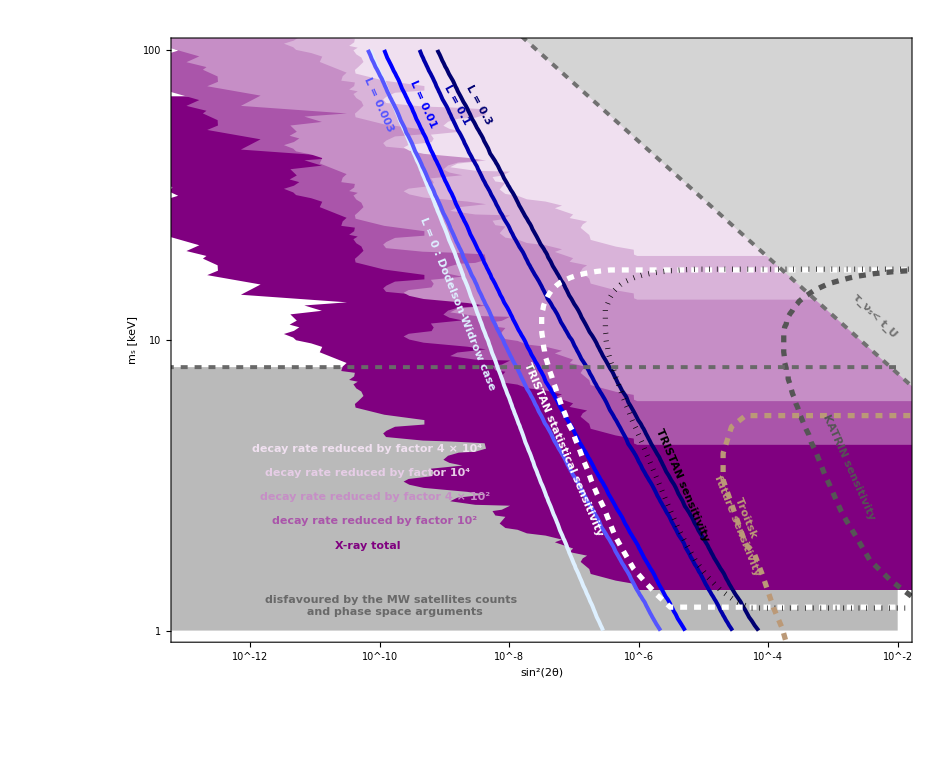

```mathematica
CPTviol03K=Plot[{},{x,-14,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
LightBlue, Thick, Thickness[0.003],Line[pointstCPTL0],
Lighter[Blue],Thick,Thickness[0.003],Line[pointstCPTL0003],
Blue,Thick,Thickness[0.003],Line[pointstCPTL001],
Darker[Blue],Thick,Thickness[0.003],Line[pointstCPTL01],
Darker[Darker[Blue]],Thick,Thickness[0.003],Line[pointstCPTL03],
White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->19,
LightBlue, Text[Rotate[Style["L = 0 : Dodelson-Widrow case",Italic, Bold],-68 Degree],Scaled[{0.387,0.56}]],
Lighter[Blue], Text[Rotate[Style["L = 0.003",Italic, Bold],-66 Degree],Scaled[{0.28,0.89}]],
Blue, Text[Rotate[Style["L = 0.01",Italic, Bold],-66 Degree],Scaled[{0.34,0.89}]],
Darker[Blue], Text[Rotate[Style["L = 0.1",Italic, Bold],-62 Degree],Scaled[{0.386,0.89}]],
Darker[Darker[Blue]], Text[Rotate[Style["L = 0.3", Italic,Bold],-62 Degree],Scaled[{0.415,0.89}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.275,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.275,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],
FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.69,0.26}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-68 Degree],Scaled[{0.77,0.2}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/CPTviol03KATRIN.pdf",CPTviol03K];
```

#### ECHo and HUNTER sensitivity

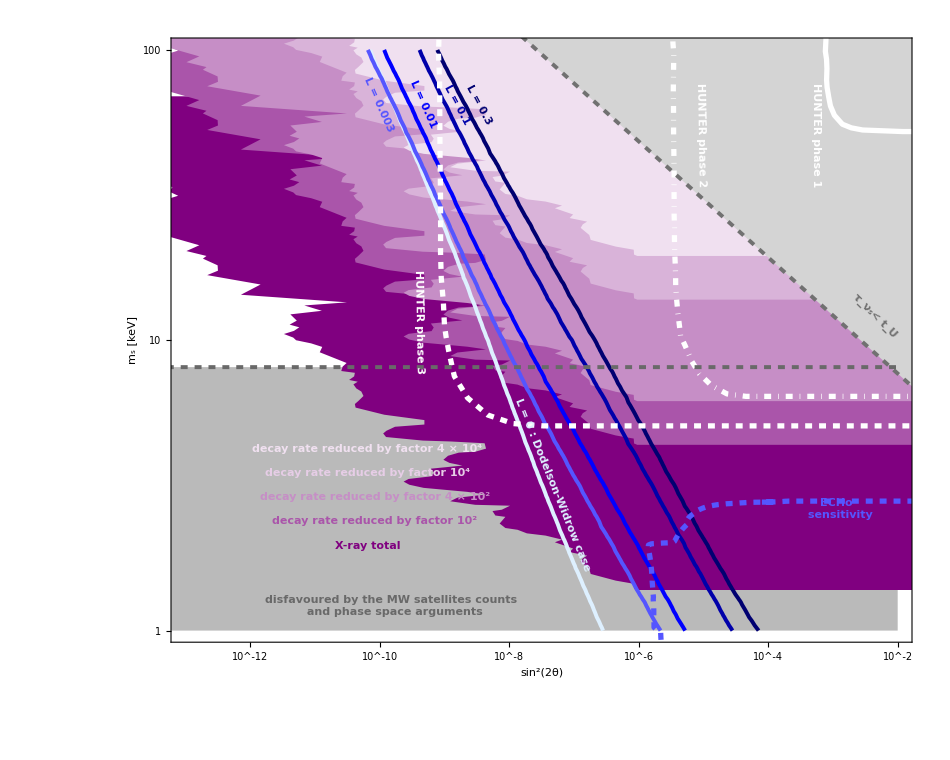

```mathematica
CPTviol03EH=Plot[{},{x,-14,-3},PlotRange->{{-13, -1.999},{0, 2.001}},
Frame->True,BaseStyle->{FontFamily->"Times",FontSize->30},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],30,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],30,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->30],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->950,Axes->False,AspectRatio->0.8,
Prolog->{
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/5],Polygon[{{-15,0},{-2,0},{-2,0.9074},{-15,0.9074}}],
Purple,Polygon[XtotLog],
Lighter[Purple],Polygon[Xtotrel90Log], 
Lighter[Lighter[Purple]],Polygon[Xtotrel95Log], 
Lighter[Lighter[Lighter[Purple]]],Polygon[Xtotrel99Log],
LightPurple,Polygon[Xtotrel995Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/2],Polygon[mainchannelboundLog],
LightBlue, Thick, Thickness[0.003],Line[pointstCPTL0],
Lighter[Blue],Thick,Thickness[0.003],Line[pointstCPTL0003],
Blue,Thick,Thickness[0.003],Line[pointstCPTL001],
Darker[Blue],Thick,Thickness[0.003],Line[pointstCPTL01],
Darker[Darker[Blue]],Thick,Thickness[0.003],Line[pointstCPTL03],
White, Thick,Thickness[0.004],Line[HUNT1Log],
White, DotDashed,Thickness[0.004],Line[HUNT2Log],
White, Dashed,Thickness[0.004],Line[HUNT3Log],
Lighter[Blue],Dashed,Line[ECHoLog],
(*White,Dashed,Thickness[0.004],Line[TRIstatLog], 
Black,Dotted,Thickness[0.004], Line[TRILog],
Darker[Gray],Dashed,Thickness[0.004],Line[KATLog],
Lighter[Brown],Dashed,Line[TroitskfutLog],*)
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3],Dashed,Thickness[0.003],Line[mainchannelboundLog],
RGBColor[105/255,105/255,105/255],Dashed,Line[SatellitelistLogr]
},

Epilog->{
FontSize->19,
LightBlue, Text[Rotate[Style["L = 0 : Dodelson-Widrow case",Italic, Bold],-68 Degree],Scaled[{0.515,0.26}]],
Lighter[Blue], Text[Rotate[Style["L = 0.003",Italic, Bold],-66 Degree],Scaled[{0.28,0.89}]],
Blue, Text[Rotate[Style["L = 0.01",Italic, Bold],-66 Degree],Scaled[{0.34,0.89}]],
Darker[Blue], Text[Rotate[Style["L = 0.1",Italic, Bold],-62 Degree],Scaled[{0.386,0.89}]],
Darker[Darker[Blue]], Text[Rotate[Style["L = 0.3", Italic,Bold],-62 Degree],Scaled[{0.415,0.89}]],

FontSize->23,
Purple, Text[Rotate[Style["X-ray total", Bold],-0 Degree],Scaled[{0.265,0.16}]], 
Lighter[Purple], Text[Rotate[Style["decay rate reduced by factor 10^2", Bold],-0 Degree],Scaled[{0.275,0.20}]], 
Lighter[Lighter[Purple]], Text[Rotate[Style["decay rate reduced by factor 4 × 10^2", Bold],-0 Degree],Scaled[{0.275,0.24}]], 
Lighter[Lighter[Lighter[Lighter[Purple]]]], Text[Rotate[Style["decay rate reduced by factor 10^4", Bold],-0 Degree],Scaled[{0.265,0.28}]],
LightPurple, Text[Rotate[Style["decay rate reduced by factor 4 × 10^4", Bold],-0 Degree],Scaled[{0.265,0.32}]],
FontSize->20,
RGBColor[105/255,105/255,105/255], Text[Rotate[Style["disfavoured by the MW satellites counts \n and phase space arguments",  Bold],-0 Degree],Scaled[{0.3,0.06}]],
FontSize->24,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/3], Text[Rotate[Style["τ_ν_s< t_U", Bold],-45 Degree],Scaled[{0.95,0.54}]],
FontSize->24,
(*White, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-67 Degree],Scaled[{0.53,0.32}]],
Black, Text[Rotate[Style["TRISTAN sensitivity", Bold],-67 Degree],Scaled[{0.69,0.26}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-66 Degree],Scaled[{0.915,0.29}]],
FontSize->20,
Lighter[Brown], Text[Rotate[Style["Troitsk \n future sensitivity", Bold],-68 Degree],Scaled[{0.77,0.2}]]*)
White, Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.87,0.84}]],
White, Text[Rotate[Style["HUNTER phase 2", Bold],-89 Degree],Scaled[{0.715,0.84}]],
White, Text[Rotate[Style["HUNTER phase 3", Bold],-89 Degree],Scaled[{0.335,0.53}]],
Lighter[Blue], Text[Rotate[Style["ECHo \n sensitivity", Bold],-0 Degree],Scaled[{0.9,0.22}]]
},
FrameTicks->{{ticksycS,ticksy2cS},{ticksxcS,ticksx2cS}}]
```

```mathematica
Export[NotebookDirectory[]<>"/plots/CPTviol03ECHoHUNTER.pdf",CPTviol03EH];
```

## technical comments

### On the data simulation

#### with sterile-dm

#### with our code

We construct a table of values

```mathematica
OmegatabeTc= {{{sin^2(2θ), Subscript[m, s]}, Subscript[Ω, s]}, ...};
```

using a For cycle

```mathematica
OmegatabeTc={};
For[eth=-14, eth≤-4, eth =eth+0.5, 
For[eMsn = -6, eMsn≤-3.9, eMsn=eMsn+0.1,
OmegasingeTc=Sterileabundance[10^eth,10^eMsn, Tfin, Tin];
AppendTo[OmegatabeTc, {{10^eth,10^eMsn},OmegasingeTc}];]];
```

we fill the array with data simulated with 
the exponent of sin22theta ranging from -14 to -4 increasing with step 0.5 (21 values of sin22theta varying in the range [10^-14,10^-4]),
the exponent of Msn ranging from -6 to -3.9 increasing with step 0.1 (22 values of Msn varying in the range [10^-6,10^-3.9]),
running Sterileabundance from the initial temperature of the production Tin (changes because it corresponds to the critical temperature) to the final temperature Tfin at which the production of sterile neutrinos finishes (Tfin = 0.001 GeV = 1 MeV always, because it is the decoupling temperature of active neutrinos from the plasma).

### On the interpolation of data

#### first method - good with data simulated with our code (when lepton asymmetries are not involved)

Once we have a table of data in this shape

```mathematica
ScanListDataTypeTc= {{{sin^2(2θ), Subscript[m, s]}, Subscript[Ω, s]}, ...};
```

we interpolate them as

```mathematica
InterpolatedScanListDataTypeTc = Interpolation[ScanListDataTypeTc, InterpolationOrder->1];
```

and we get the list of the contour plot in 4 steps

```mathematica
plDataTypeTc=Normal@ContourPlot[InterpolatedScanListDataTypeTc[theta2times4, Msn]==0.1186, {theta2times4, 10^-14, 10^-4},{Msn, 10^-6, 10^-4},PlotPoints->150];

LinelistDataTypeTc=Cases[ plDataTypeTc,Line[a_,b___]:>a,Infinity]⟦1⟧;
```

the last line gives us a list of coordinates of points (sin^2(2θ), m_s[GeV])identifying the right amount of DM in the parameter space.
Then we rescale the mass values to bring them from GeV to keV units, and we bring them in logarithmic form that fits better in the plot

```mathematica
LinelistDataTypeTcr = Table[{LinelistDataTypeTc⟦i,1⟧,LinelistDataTypeTc⟦i,2⟧*10^6} ,{i,1,Length[LinelistDataTypeTc]}];

LinelistDataTypeTcLog = Table[{Log10[LinelistDataTypeTcr⟦i,1⟧], Log10[LinelistDataTypeTcr⟦i,2⟧]}, {i ,1,Length[LinelistDataTypeTcr]}];
```

#### second method - good with the data coming from sterile-dm

Once we have a table of data in this shape

```mathematica
ScanListDataTypeTc= {{{sin^2(2θ), Subscript[m, s]}, Subscript[Ω, s]}, ...};
```

we interpolate them as

```mathematica
InterpolatedScanListDataTypeTc = Interpolation[ScanListDataTypeTc, InterpolationOrder->1];
```

and we get the list of the contour plot in 2 steps

```mathematica
pointsDataTypeTc=Flatten[Cases[Normal@ContourPlot[InterpolatedScanListDataTypeTc[10^x,10^y]==0.1186,{x,-14,-2},{y,-6,-4},ContourShading->None],Line[pts_]->pts,Infinity],1];
```

this line of code already gives a list of coordinates of points (sin^2(2θ), m_s[GeV])identifying the right amount of DM in the parameter space in Log Log form.

```mathematica
pointstDataTypeTc=Transpose[{Table[pointsDataTypeTc⟦i,1⟧,{i,1,Length[pointsDataTypeTc]}],Table[pointsDataTypeTc⟦i,2⟧+6,{i,1,Length[pointsDataTypeTc]}]}];
```

the last line transforms the mass values from GeV into keV, so that they are homogeneous with the other quantities we have to plot. The final result is a list of coordinates of points (Log[sin^2(2θ)],Log[ m_s[keV]]).